# CLARA V10.1 SLD-FEL : Commenced Dec 2016 PHW

## Initialisation

```mathematica
NotebookDirectory[]
```

D:\CLARA\V10\

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\CLARA\V10

```mathematica
{$System,$SystemID,$Version,$MachineType,$ProcessorType,$OperatingSystem,$SystemWordLength,$ProcessorCount,$MachineName}
(*SystemInformation*)
```

{Microsoft Windows (64-bit),Windows-x86-64,11.0.0 for Microsoft Windows (64-bit) (July 28, 2016),PC,x86-64,Windows,64,6,ksv86254dell}

```mathematica
EvaluationNotebook[]
```

wswr5_shm15FrontEndObject[LinkObject["wswr5_shm", 3, 1]]15clara_V10.1 SLD-FEL.nbD:\CLARA\V10\clara_V10.1 SLD-FEL.nb

Don’t use notebook autosave - sooo slow

```mathematica
(*SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]*)
```

saves every 1000s = 16 mins

```mathematica
NotebookSave[EvaluationNotebook[]]
```

```mathematica
RunScheduledTask[EmitSound[Sound[SoundNote[]]];NotebookSave[EvaluationNotebook[]],10];
```

```mathematica
RemoveScheduledTask[ScheduledTasks[]]
```

{ScheduledTaskObject[…]}

```mathematica
ScheduledTasks[]
```

{}

```mathematica
<<CustomTicks`
```

```mathematica
<<astrainterpret`
```

```mathematica
<<sddsbinaryinterpret`
```

```mathematica
<<madtomma`madinput`Matching`
```

```mathematica
<<madtomma`madinput`ReadInMADFiles2`
```

Version 2.21 of Madtomma`Mfs`Mfs` loaded.  Note function name changes since Version 1.x:
interpretDescriptors→mfsInterpretKeys
keyValue→mfsKeyValue
columnNames→mfsColumnNames
descriptorNames→mfsKeyNames
colValue→mfsColumnValue
addDescriptor→mfsAddKey
editDescriptor→mfsEditKey
deleteDescriptor→mfsDeleteKey
symplecticJ→SymplecticJ

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Set::write: Tag ListLinePlot in SyntaxInformation[ListLinePlot] is Protected.

Type::shdw: Symbol Type appears in multiple contexts {Madtomma`MADInput`MADInput`,Global`}; definitions in context Madtomma`MADInput`MADInput` may shadow or be shadowed by other definitions.

drift::shdw: Symbol drift appears in multiple contexts {Madtomma`MADInput`MADInput`,Global`}; definitions in context Madtomma`MADInput`MADInput` may shadow or be shadowed by other definitions.

MADClear::shdw: Symbol MADClear appears in multiple contexts {Madtomma`MADInput`MADInput`,Global`}; definitions in context Madtomma`MADInput`MADInput` may shadow or be shadowed by other definitions.

Global`Thin::shdw: Symbol Thin appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`Echo::shdw: Symbol Echo appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag FindPeaks in FindPeaks[data1_,data2_,Opts___] is Protected.

```mathematica
Remove[Global`Constraints];Clear[Global`Constraints];
```

Global`Constraints::shdw: Symbol Constraints appears in multiple contexts {Global`,Madtomma`MADInput`Matching`}; definitions in context Global` may shadow or be shadowed by other definitions.

```mathematica
$Path
```

{C:\Program Files\Wolfram Research\Mathematica\11.0\SystemFiles\Links,C:\Users\ksv86254\AppData\Roaming\Mathematica\Kernel,C:\Users\ksv86254\AppData\Roaming\Mathematica\Autoload,C:\Users\ksv86254\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\ksv86254,C:\Program Files\Wolfram Research\Mathematica\11.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\11.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\11.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\11.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\11.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\11.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\11.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\11.0\SystemFiles\Data\ICC}

```mathematica
<<sddsInterpret`
```

```mathematica
Off[Read::"readn"];
```

```mathematica
sshwonder[text_]:=ReadList["!ssh -i c:/cygwin64/home/ksv86254/.ssh/id_rsa2 phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk \"source /etc/profile ; source .bash_login ; "<>text<>"\" 2>&1",Record]
```

```mathematica
sshapsv2[text_]:=ReadList["!ssh apsv2 \" "<>text<>"\"",Record]
```

```mathematica
ssh[text_]:=ReadList["!ssh dlphw@dl1.nw-grid.ac.uk \"source /usr/share/Modules/init/bash 
;source /etc/profile.d/sge6.sh;source /etc/profile.d/condor.sh ;export 
PATH=$PATH:/usr/local/sge6.2/bin/lx24-amd64 ;module load pelegant; export 
LD_LIBRARY_PATH=/opt/openmpi-1.3.1-1/gcc/lib64:/usr/local/gcc-4.2.1/lib64;  "<>text<>"\"",Record]
```

```mathematica
Clear[scp];
scp[near_String,far_String]:=Block[{dir=Directory[]},
ReadList["!scp -i ~/.ssh/id_rsa2 "<>near<>" "<>far,Record]
]
```

```mathematica
Clear[scpr];
scpr[near_String,far_String]:=Block[{dir=Directory[]},
ReadList["!scp -i ~/.ssh.id_rsa2 -r "<>near<>" "<>far,Record]
]
```

```mathematica
Clear[QueueGPT];
QueueGPT[file_String,dir_String]:=Block[{},
Print[dir];
sshwonder["cd "<>dir<>"; rm -f *"];
sshwonder["cp -f ~/CLARA/basefiles/* "<>dir];
scp[dir<>"/clara.new","phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:"<>dir<>"/"];
sshwonder["cd "<>dir<>"; ./pelegantsub.sh "<>file<>" > submit_out;test1=\$(grep Job-ID 
submit_out);pwd=\$(pwd);echo \"Submitted \$pwd \$test1\" >> 
~/CLARA/submitted.txt; "];
]
```

```mathematica
Clear[SetQueues];
SetQueues[params_,jobno_]:=Block[{},
Off[CopyFile::"filex"];
Off[Power::"infy"];
Off[∞::"indet"];
ReadList["!rm -rf track"<>ToString[jobno],Record]
CreateDirectory["track"<>ToString[jobno]];
WriteInputFilePar[params,"track"<>ToString[jobno]];
QueueElegant["clara.ele","~/CLARA/track"<>ToString[jobno]];
];
```

#### Definitions to write Elegant lattice from MADInput

```mathematica
CLA£Q
```

CLA£Q

```mathematica
lscdriftWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":LSCDRIFT, bins = 100,& 
    \thigh_frequency_cutoff0 = 0.2, high_frequency_cutoff1 = 0.25, interpolate = 1,& 
    \tradius_factor = 2, sg_halfwidth = 1, sg_order = 1, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> "\n"
   ]
  ]
```

```mathematica
driftWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":DRIFT, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> "\n"
   ]
  ]
```

```mathematica
bpmWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":MONI, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ", co_fitpoint = 1\n"
   ]
  ]
```

```mathematica
markerWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{}, If[name != "CLA£Q",If[StringMatchQ[name,___~~"WATCH"~~___]
,MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":WATCH, filename = "<>StringReplace[name, {"£" -> "-"}]<>".sdds\n"
    ],MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":MARK, fitpoint = 1\n"
    ]],MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":CHARGE, total = 250E-12\n"
    ]]
  ]
```

```mathematica
rfcwWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{},
  If[StringMatchQ[name, "*TDC*"], MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":RFDF, frequency = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[7]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tvoltage = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\",&
     \t\tphase = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]] ] , 8, ExponentFunction -> (Null &)]] <> " 360 * 90 +\",&
     \t\ttilt = \"pi -1 * 2 /\",&
     \t\tn_kicks=" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]] ] , 8, ExponentFunction -> (Null &)]] <> "\n"
    ],
   MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":RFCW, freq = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[7]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tcell_length = \"" <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> " " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]]], 8, ExponentFunction -> (Null &)]] <> " / \",&
     \t\tvolt = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\",&
     \t\tphase = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]] ] , 8, ExponentFunction -> (Null &)]] <> " 360 * 90 +\",&
     \t\tchange_p0=1,&
     \t\tend1_focus=1,end2_focus=1,&
     \t\tZWAKEFILE=\"Sz5um10mm.sdds\",&
     \t\tTRWAKEFILE=\"Sx5um10mm.sdds\",&
     \t\tTCOLUMN=\"t\", WZCOLUMN=\"W\",&
     \t\tWXCOLUMN=\"W\", WYCOLUMN=\"W\",&
     \t\tn_kicks= " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]] ] , 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tinterpolate = 1,&
     \t\tsmoothing = 1,&
     \t\tlsc = 1, lsc_bins = \"lscbins\", &
     \t\tlsc_high_frequency_cutoff0 = 0.2,&
     \t\tlsc_high_frequency_cutoff1 = 0.25, lsc_interpolate = 1,&
     \t\tlsc_radius_factor = 1.7,&
     \t\tbody_focus_model = SRS,&
     \t\tzwake = 1,trwake = 1\n"
    ]]
  ]
```

```mathematica
twlaWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{}, If[StringMatchQ[name, "*TDC*"], MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":RFDF, frequency = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[7]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tvoltage = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\",&
     \t\tphase = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]] ] , 8, ExponentFunction -> (Null &)]] <> " 360 * 90 +\",&
     \t\ttilt = \"pi -1 * 2 /\",&
     \t\tn_kicks=" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]] ] , 8, ExponentFunction -> (Null &)]] <> "\n"
    ],
   MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":TWLA, frequency = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[7]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tez = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> " " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> " / 1e6 *\",&
     \t\tphase = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]]], 8, ExponentFunction -> (Null &)]] <> " 360 * 90 + pi * 180 /\",&
     \t\tchange_p0=1,&
     \t\tfocussing = 1, n_steps = " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]]], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tmethod = \"non-adaptive runge-kutta\"\n
     "
    ]]
  ]
```

```mathematica
quadWrite[filename_, {name_, a_, length_, k1_, b_, c_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":KQUAD, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ", n_kicks = 10, k1 = " <> ToString[NumberForm[N[k1], 8, ExponentFunction -> (Null &)]] <> "\n"
   ]
  ]
```

```mathematica
sextWrite[filename_, {name_, a_, length_, k2_, b_, c_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":KSEXT, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ", n_kicks = 10, k2 = " <> ToString[NumberForm[N[k2], 8, ExponentFunction -> (Null &)]] <> "\n"
   ]
  ]
```

```mathematica
sbendWrite[filename_, {name_, a_, length_, b_, c_, angle_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":CSRCSBEND, angle = " <> ToString[NumberForm[N[angle], 8, ExponentFunction -> (Null &)]] <> ", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
    \t\te1 = " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> ", e2 = " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]]], 8, ExponentFunction -> (Null &)]] <> ", nonlinear = 1,&
    \t\tn_kicks = 10, integration_order = 4,& 
    \t\thgap = \"hdip\", fint = \"fdip\",&
    \t\tbins = \"csrbins\", sg_halfwidth = 2, isr = 1, synch_rad = 1,&
    \t\tcsr = 1, output_file = " <> StringReplace[name, {"£" -> "-"}] <> ".csr\n"
   ]
  ]
```

```mathematica
insertAmpersands[str_] := Block[{strpos, str2, strs},
  strpos = StringPosition[str, ","][[All, 1]];
  strs = Map[StringJoin[#, "&"] &, Most[StringSplit[str, "&"]]];
  str2 = Last[StringSplit[str, "&"]];
  If[StringLength[str2] > 80,
   strpos = StringPosition[str2, ","][[All, 1]];
   strs = Join[strs, {StringInsert[str2, "&\n", Select[strpos, # < 80 &][[-1]] + 1]}],
   strs = Join[strs, str2];
   ];
  StringJoin @@ strs
  ]
```

```mathematica
lineWrite[filename_, line_] := Block[{str},
  (*str = StringReplace[StringTake[ToString[Select[MADFlatten[line], #[[2]] =!= "Marker" &][[All, 1]]], {2, -2}], {"£" -> "-"}];*)
 str = StringReplace[StringTake[ToString[MADFlatten[line][[All, 1]]], {2, -2}], {"£" -> "-"}];
  While[Max[StringLength[#] & /@ StringSplit[str, "&"]] > 80, str = insertAmpersands[str]];
  MADStringWrite[filename, "CLARA: LINE = (&\n" <> StringTake[str, {1, -1}] <> ")
    "]
  ]
```

```mathematica
elementWrite[filename_, list_] := Block[{},
  DeleteFile[filename <> ".mff"];
  MADStringWrite[filename, "
% 0.005         sto hdip
% 0.000         sto fdip
% 20            sto csrbins
% 20            sto lscbins\n"];
  Switch[#[[2]],
     "Marker", markerWrite[filename, #],
"LCAV", rfcwWrite[filename, #],
     "Drift", driftWrite[filename, #],
"BPM",driftWrite[filename,#],
     "Quadrupole", quadWrite[filename, #],
     "Sextupole", sextWrite[filename, #],
     "SectorBend", sbendWrite[filename, #]] & /@ Union[MADFlatten[list]];
  lineWrite[filename, list];
  ]
```

```mathematica
elementtwlaWrite[filename_, list_] := Block[{},
  DeleteFile[filename <> ".mff"];
  MADStringWrite[filename, "
% 0.005         sto hdip
% 0.000         sto fdip
% 20            sto csrbins
% 20            sto lscbins\n"];
  Switch[#[[2]],
     "Marker", markerWrite[filename, #],
     "LCAV", twlaWrite[filename, #],
     "Drift", driftWrite[filename, #],
"BPM",driftWrite[filename,#],
     "Quadrupole", quadWrite[filename, #],
     "Sextupole", sextWrite[filename, #],
     "SectorBend", sbendWrite[filename, #]] & /@ Union[MADFlatten[list]];
  lineWrite[filename, list];
  ]
```

```mathematica
Clear[GetTwiss];
GetTwiss[filename_:"clara.twi"]:=Block[{},
{SELE,ELENAME,ELEOCCUR,BETXELE,BETYELE,ALFXELE,ALFYELE,ETAXELE,ETAYELE,MUXELE,MUYELE}=Transpose[ReadList["!sdds2stream -column=s,ElementName,ElementOccurence,betax,betay,alphax,alphay,etax,etay,psix,psiy "<>filename,{Number,Word,Number,Number,Number,Number,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetCen];
GetCen[filename_:"clara.cen"]:=Block[{},
{CX,CY,CS,CSDEL,PCEN}=Transpose[ReadList["!sdds2stream -column=Cx,Cy,Cs,Cdelta,pCentral "<>filename,
{Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetSig];
GetSig[filename_:"clara.sig"]:=Block[{},
{SX,SY,SSS,SDEL,ST,ECNX,ECNY}=Transpose[ReadList["!sdds2stream -column=Sx,Sy,Ss,Sdelta,St,ecnx,ecny "<>filename,{Number,Number,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetTwissBeam];
GetTwissBeam[filename_:"clara.sig"]:=Block[{},
{SELEBEAM,ELENAMEBEAM,ELEOCCURBEAM,BETXELEBEAM,BETYELEBEAM,ALFXELEBEAM,ALFYELEBEAM}=Transpose[ReadList["!sdds2stream -column=s,ElementName,ElementOccurence,betaxBeam,betayBeam,alphaxBeam,alphayBeam "<>filename,{Number,Word,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetTwissTWLA];
GetTwissTWLA[filename_:"clara.twi"]:=Block[{},
{SELET,ELENAMET,ELEOCCURT,BETXELET,BETYELET,ALFXELET,ALFYELET,ETAXELET,ETAYELET,MUXELET,MUYELET}=Transpose[ReadList["!sdds2stream -column=s,ElementName,ElementOccurence,betax,betay,alphax,alphay,etax,etay,psix,psiy "<>filename,{Number,Word,Number,Number,Number,Number,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetCenTWLA];
GetCenTWLA[filename_:"clara.cen"]:=Block[{},
{CXT,CYT,CST,CSDELT,PCENT}=Transpose[ReadList["!sdds2stream -column=Cx,Cy,Cs,Cdelta,pCentral "<>filename,{Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetSigTWLA];
GetSigTWLA[filename_:"clara.sig"]:=Block[{},
{SXT,SYT,SSST,SDELT,STT,ECNXT,ECNYT}=Transpose[ReadList["!sdds2stream -column=Sx,Sy,Ss,Sdelta,St,ecnx,ecny "<>filename,{Number,Number,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetTwissBeamTWLA];
GetTwissBeamTWLA[filename_:"clara.sig"]:=Block[{},
{SELEBEAMT,ELENAMEBEAMT,ELEOCCURBEAMT,BETXELEBEAMT,BETYELEBEAMT,ALFXELEBEAMT,ALFYELEBEAMT}=Transpose[ReadList["!sdds2stream -column=s,ElementName,ElementOccurence,betaxBeam,betayBeam,alphaxBeam,alphayBeam "<>filename,{Number,Word,Number,Number,Number,Number,Number}]]]
```

## Elegant Interpreter - Reads in unmatched CLARA_V10.1.lte lattice

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\CLARA\V10

```mathematica
lines = StringReplace[StringJoin @@@ Split[Select[ReadList["clara_V10.1.lte", Record], ! StringMatchQ[#, WhitespaceCharacter ... ~~ "!*"] &], StringMatchQ[#1, "*&" ~~ WhitespaceCharacter ...] &], "&" -> ""];
```

```mathematica
Clear[getname];
getname[str_]:=Block[{},
ToUpperCase[StringReplace[StringTake[str,StringPosition[str,":"]⟦1,1⟧-1],{" "->"","_"->"$","-"->"£"}]]
]
```

```mathematica
gettype[str_]:=Block[{},
StringReplace[StringTake[str,{StringPosition[str,":"]⟦1,1⟧+1,If[StringMatchQ[str,"*,*"],StringPosition[str,","]⟦1,1⟧-1,StringLength[str]]}],{" "->"","_"->"$","-"->"£","\t"->""}]
]
```

```mathematica
MakeRule[{var_,valuein_}]:=Block[{},
value=Which[
StringMatchQ[valuein,WhitespaceCharacter...~~"*\"*\"*"],rpn[valuein],
True,rpnoperators[StringReplace[valuein," "->""]]
];
Rule[StringReplace[var," "->""],N@Replace[value,"π"->π]]
]
```

```mathematica
MakeRule2[{var_,valuein_}]:=Block[{},
value=Which[
StringMatchQ[valuein,WhitespaceCharacter...~~"*\"*\"*"],rpnoperators[StringReplace[valuein," "->""]],
True,rpnoperators[StringReplace[valuein," "->""]]
];
Rule[StringReplace[var," "->""],N@Replace[value,"π"->π]]
]
```

```mathematica
parseELEMENT[elem_]:=Block[{},
ELEMENT[getname[elem]]=Join[{"Type"->gettype[elem],"Name"->getname[elem]},If[gettype[elem]=="wake"||gettype[elem]=="WATCH",Map[MakeRule2[##]&,StringSplit[Rest[StringSplit[StringReplace[elem,{"  "->" ","\t"->"",";"->"","pi"->ToString[π//N]}],","]],"="]],Map[MakeRule[##]&,StringSplit[Rest[StringSplit[StringReplace[elem,{"  "->" ","\t"->"",";"->"","!*"->"","pi"->ToString[π//N]}],","]],"="]]]]
]
```

```mathematica
Clear[parseLINE];
parseLINE[line_]:=Block[{$groupin,$group=False},
BEAMLINE={Sequence@@BEAMLINE,Join[{"Name"->getname[line]},{"Line"->Flatten[Map[StringReplace[ToUpperCase[#],{"{"->"","}"->"",WhitespaceCharacter...~~x:DigitCharacter..~~WhitespaceCharacter...~~"*"~~"("~~y__~~")":>ToString@Table[y,{ToExpression[x]}],WhitespaceCharacter...~~x:DigitCharacter..~~WhitespaceCharacter...~~"*"~~y__~~"}":>ToString@Table[y,{ToExpression[x]}]," "->""}]&,
Map[ToString,Split[StringSplit[StringReplace[StringTake[line,{StringPosition[line,"("]⟦1,1⟧+1,StringPosition[line,")"]⟦-1,1⟧-1}],{"\t"->"","_"->"$","-"->"£"}],","],
($group;If[StringMatchQ[#1,"*(*"],$group=True,If[StringMatchQ[#1,"*)*"],$group=False]];$group)
&]]
]]}]}
]
```

```mathematica
Clear[ELEMENT];
ELEMENT[All]:=Cases[DownValues[ELEMENT],HoldPattern[ELEMENT[_String]],3]
ELEMENT[All,x_]:=Evaluate[ToString[HoldForm[x]]]/.Cases[DownValues[ELEMENT],HoldPattern[ELEMENT[_String]],3]
ELEMENT[name_Symbol]:=Cases[ELEMENT[All],{___,"Name"->ToString[HoldForm[name]],___}]
Clear[BEAMLINE];
BEAMLINE={};
```

```mathematica
interpretvalues[str_]:=Block[{},
If[StringMatchQ[str,RegularExpression["[\\d|e|E|.|\\-|+]+"]],Number,Word]
]
```

```mathematica
Clear[rpnoperators];
rpnoperators[operator_]:=Block[{},Switch[ToLowerCase[operator],
"sin",{Sin,1},
"cos",{Cos,1},
"asin",{ArcSin,1},
"acos",{ArcCos,1},
"atan",{ArcTan,1},
"sqrt",{Power[#,0.5]&,1},
"/",{Divide,2},
"*",{Times,2},
"+",{Plus,2},
"sum",{ToExpression[ToString@Total[Take[stack,{-ToExpression[#]-1,-2}]]]&,1},
_,If[StringQ[#],
If[NameQ[#]||StringMatchQ[#,"*π*"],
ToExpression[#],
#]
&[StringReplace[#,"_"->"$"]],N[#]]&[Block[{ans},ans=ReadList[str=StringToStream[operator],interpretvalues[operator]];Close[str];ans⟦1⟧]]]
]
```

```mathematica
Clear[rpncalc];
rpncalc[splitstring_]:=Block[{stack={},rpnop},
If[!ListQ[(rpnop=rpnoperators[#])],AppendTo[stack,rpnop],AppendTo[stack,rpnop⟦1⟧[Sequence@@Take[stack,-1*rpnop⟦2⟧]]]]&/@splitstring;
N@Last[stack]
]
```

```mathematica
Clear[rpn];
rpn[valuein_]:=Block[{splitstring},
splitstring=If[StringMatchQ[#,RegularExpression["[\\d|\\w]+"]~~"-*"],StringReplace[#,{"_"->"$","-"->"£"}],#]&/@StringSplit[StringReplace[valuein,"\""->""]];
rpncalc[splitstring]
];
rpn[valuein_]/;StringMatchQ[valuein,WhitespaceCharacter...~~"%*"]:=Block[{splitstring,splitstringall,value,stack={},rpnop},
splitstringall=If[StringMatchQ[#,RegularExpression["[\\d|\\w]+"]~~"-*"],StringReplace[#,{"_"->"$","-"->"£","pi"->"π"}],StringReplace[#,{"_"->"$","pi"->"π","PI"->"π","Pi"->"π"}]]&/@Select[StringSplit[StringReplace[valuein,"%"->"% "]],!StringMatchQ[#,"%"]&];
splitstring=Drop[splitstringall,-2];
Clear[Evaluate[splitstringall⟦-1⟧]];
Evaluate[Symbol@splitstringall⟦-1⟧]=rpncalc[splitstring];
]
```

```mathematica
lines[[All]];
```

```mathematica
Quiet[Block[{},
Check[If[StringMatchQ[#,WhitespaceCharacter...~~RegularExpression["[\\w|-]+"]..~~WhitespaceCharacter...~~":*,*"]||StringMatchQ[ToUpperCase[#],"*:"~~WhitespaceCharacter...~~"LINE*"],
If[StringMatchQ[ToUpperCase[#],"*:"~~WhitespaceCharacter...~~"LINE*"],
parseLINE[#],
parseELEMENT[#]
],
If[StringMatchQ[#,WhitespaceCharacter...~~"%"~~"*"],
rpn[#],
#]
],Print[#]]
]&/@lines];
```

```mathematica
getParameter[input_,var_]:=Block[{},
First[Cases[input,Rule[x_,y_]/;StringMatchQ[ToUpperCase[x],ToUpperCase[var]]:>y]/.{{}->{0}}]
]
```

#### Drift

```mathematica
Unprotect[drift]
```

{drift}

```mathematica
SetAttributes[drift,HoldFirst]
```

```mathematica
drift[name_:Drift,L_,Type_:"",Extra___]:=Block[{name2},If[MatrixQ[name]||VectorQ[name],name2=ToString[name⟦1,1⟧];MADClear[name];
name={{ToString[name],"Drift",L,"---","---","---",ToString[Type]}};,name2=ToString[name];
MADClear[name];
Evaluate[Symbol@ToString[name]]={{ToString[name],"Drift",L,"---","---","---",ToString[Type]}};];
driftExtra[name2,Extra]]
```

```mathematica
driftExtra[name_,Extra___]:=Block[{k,poles,tilt,delayed},
delayed=Global`Delayed/.{Extra}/.{Global`Delayed->False};
k=Global`k/.{Extra}/.{Global`k->0};
poles=Global`poles/.{Extra}/.{Global`poles->0};
tilt=Global`tilt/.{Extra}/.{Global`tilt->0};
If[delayed,
ToExpression["Evaluate[(Symbol@(ToString[\""<>name<>"\"]<>\"Extra\"))]:=List[\""<>name<>"\",\"Extra\","<>ToString[k]<>","<>ToString[poles]<>","<>ToString[tilt]<>"]"],
Evaluate[(Symbol@(ToString[name]<>"Extra"))]=List[name,"Extra",k,poles,tilt]];]
```

```mathematica
Protect[drift]
```

{drift}

```mathematica
Block[{},
Clear[t];
Clear[Evaluate["Name"/.#]];
If[NameQ[#],Print[#]];
Switch[ToUpperCase["Type"/.#],
"CHARGE",marker[Evaluate["Name"/.#],"Name"/.#],
(*"RCOL",rcoll[Evaluate["Name"/.#],getParameter[#,"l"],getParameter[#,"x_max"],getParameter[#,"y_max"],"Name"/.#],*)
"RCOL",drift[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#],
"ECOL",drift[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#],
"VKICK",vkick[Evaluate["Name"/.#],getParameter[#,"l"],getParameter[#,"kick"],"Name"/.#],
"KICKER",kick[Evaluate["Name"/.#],getParameter[#,"l"],getParameter[#,"hkick"],getParameter[#,"vkick"],"Name"/.#],
"WATCH",marker[Evaluate["Name"/.#],"Name"/.#],
"MARK",marker[Evaluate["Name"/.#],"Name"/.#],
"MAXAMP",marker[Evaluate["Name"/.#],"Name"/.#],
"MONI",drift[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#],
"MARKER",marker[Evaluate["Name"/.#],"Name"/.#],
"WAKE",marker[Evaluate["Name"/.#],"Name"/.#],
"TRWAKE",marker[Evaluate["Name"/.#],"Name"/.#],
"ZWAKE",marker[Evaluate["Name"/.#],"Name"/.#],
"RFDF",rfc[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#,MADVolt->(getParameter[#,"volt"]),Lag->(getParameter[#,"phase"]),MADFreq->getParameter[#,"frequency"]],
"LSCDRIFT",drift[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#],
"DRIF",drift[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#],
"DRIFT",drift[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#],
"CSRDRIFT",drift[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#],
"LSRMDLTR",drift[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#],
"KQUAD",ToExpression["quad["<>Evaluate["Name"/.#]<>","<>ToString[getParameter[#,"l"]]<>","<>ToString[Evaluate[getParameter[#,"k1"]]]<>",\""<>ToString[Evaluate["Name"/.#]]<>"\"]"],
"KQUADRUPOLE",ToExpression["quad["<>Evaluate["Name"/.#]<>","<>ToString[getParameter[#,"l"]]<>","<>ToString[Evaluate[getParameter[#,"k1"]]]<>",\""<>ToString[Evaluate["Name"/.#]]<>"\"]"],
"QUAD",ToExpression["quad["<>Evaluate["Name"/.#]<>","<>ToString[getParameter[#,"l"]]<>","<>ToString[Evaluate[getParameter[#,"k1"]]]<>",\""<>ToString[Evaluate["Name"/.#]]<>"\"]"],
"QUADRUPOLE",ToExpression["quad["<>Evaluate["Name"/.#]<>","<>ToString[getParameter[#,"l"]]<>","<>ToString[Evaluate[getParameter[#,"k1"]]]<>",\""<>ToString[Evaluate["Name"/.#]]<>"\"]"],
"KSEXT",sext[Evaluate["Name"/.#],getParameter[#,"l"],getParameter[#,"k2"],"Name"/.#],
"SEXT",sext[Evaluate["Name"/.#],getParameter[#,"l"],getParameter[#,"k2"],"Name"/.#],
"SEXTUPOLE",sext[Evaluate["Name"/.#],getParameter[#,"l"],getParameter[#,"k2"],"Name"/.#],
"CSRCSBEND",sbend[Evaluate["Name"/.#],getParameter[#,"l"],getParameter[#,"k1"],getParameter[#,"angle"],"Name"/.#,E1->(getParameter[#,"e1"]),E2->(getParameter[#,"e2"])],
"RFCW",rfc[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#,MADVolt->(getParameter[#,"volt"]),Lag->(getParameter[#,"phase"]),MADFreq->getParameter[#,"freq"]],
"RFCA",rfc[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#,MADVolt->ToExpression@(getParameter[#,"volt"]),MADFreq->ToExpression@("frequency"/.#)],
"WIGGLER",drift[Evaluate["Name"/.#],getParameter[#,"l"],"Name"/.#,k-> (getParameter[#,"k"]//FortranForm),poles->(getParameter[#,"poles"]//FortranForm),tilt->(getParameter[#,"tilt"]//FortranForm)],
_,Print[#];#
]]&/@ELEMENT[All];
```

```mathematica
CLA£L04£CAV
```

{{CLA£L04£CAV,RFC,4.06667,---,---,---,CLA£L04£CAV}}

```mathematica
CLA£L04£CAVExtra
```

{CLA£L04£CAV,Extra,0,0,9.15×10^7,90.,0,0,0,0,0,2.9985×10^9}

```mathematica
CLA£FRS£R01£MAG£UND£W£H1
```

{{CLA£FRS£R01£MAG£UND£W£H1,Drift,0.375,---,---,---,CLA£FRS£R01£MAG£UND£W£H1}}

```mathematica
CLA£FRS£R01£MAG£UND£W£H1Extra
```

{CLA£FRS£R01£MAG£UND£W£H1,Extra,1.25,26.,-1.570795}

```mathematica
CLA£FRS£R01£MAG£UND£W£H1Extra⟦5⟧//FullForm
```

FortranForm[-1.5708]

```mathematica
CorrectLines[line_]:=Block[{},
Map[StringReplace[#,{"("->"{",")"->"}",WhitespaceCharacter...~~x:DigitCharacter..~~"*":>"Table[#,{"<>x<>"}]&@"," "->""}]&,Map[ToString,Split[line,StringMatchQ[#1,"*(*"]||StringMatchQ[#2,"*)*"]&]]]
]
```

```mathematica
Do[Block[{x},
Clear[Evaluate["Name"/.#]];
Check[ToExpression["line["<>Evaluate["Name"/.#]<>","<>ToString[Evaluate["Line"/.#]]<>"]"],Print["line["<>Evaluate["Name"/.#]<>","<>ToString[Evaluate["Line"/.#]]<>"]"]];
]&/@BEAMLINE,{3}]
```

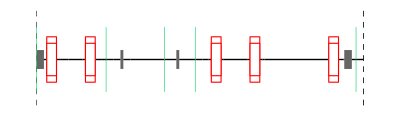

```mathematica
CLA£S02//MADDraw
```

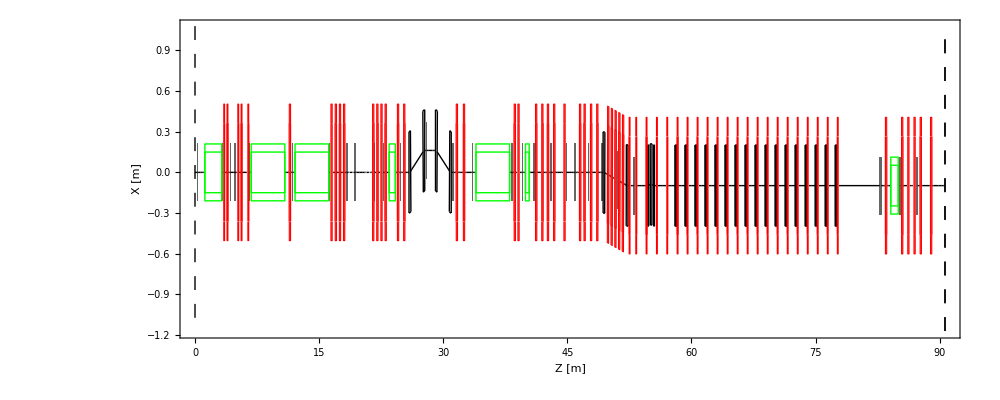

```mathematica
MADDraw[Select[MADFlatten[CLA], #[[3]] > 0 &][[1 ;; -1]],ImageSize->1000,Frame->True,FrameLabel-> {"Z [m]","X [m]"},BaseStyle->{{FontSize->15,FontFamily->"Helvetica"}},WidthScale->3,Errors->False]
```

```mathematica
$DRAWLATTICE=CLA;$DRAWLATTICE2=CLA£SP2;$DRAWLATTICE3=CLA£SP3;$DRAWLATTICE4=CLA£EBT£BA1;$DRAWLATTICE5={CLA£S01,CLA£L01,CLA£S02SP1};
```

```mathematica
$DRAWLATTICEBPM=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*K"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE]];$DRAWLATTICEBPM2=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*K"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE2]];$DRAWLATTICEBPM3=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*K"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE3]];
$DRAWLATTICEBPM4=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*K"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE4]];
$DRAWLATTICEBPM5=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*K"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE5]];
```

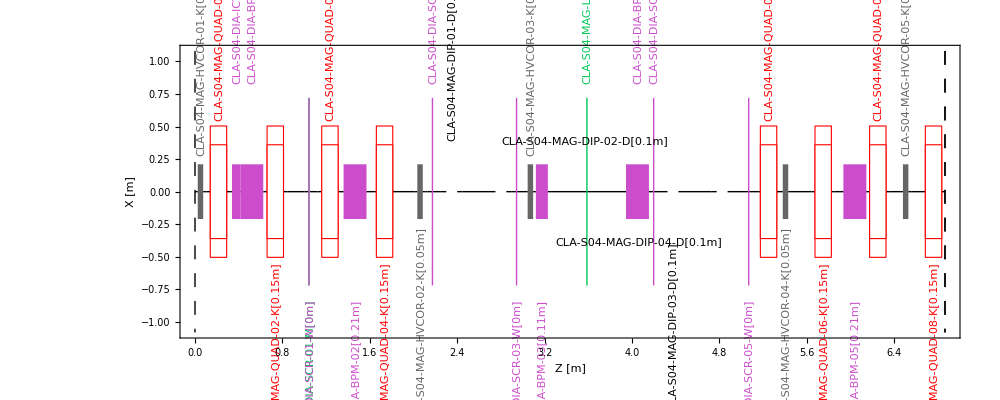

```mathematica
MADDraw[ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]&/@MADFlatten[$DRAWLATTICEBPM]⟦90;;180⟧,ImageSize->1000,Frame->True,FrameLabel-> {"Z [m]","X [m]"},BaseStyle->{{FontSize->12,FontFamily->"Helvetica"}},WidthScale->3,Errors->False,Labels->True,Lengths->True,DriftLabels->False,Monitors->True,Filled->True]
```

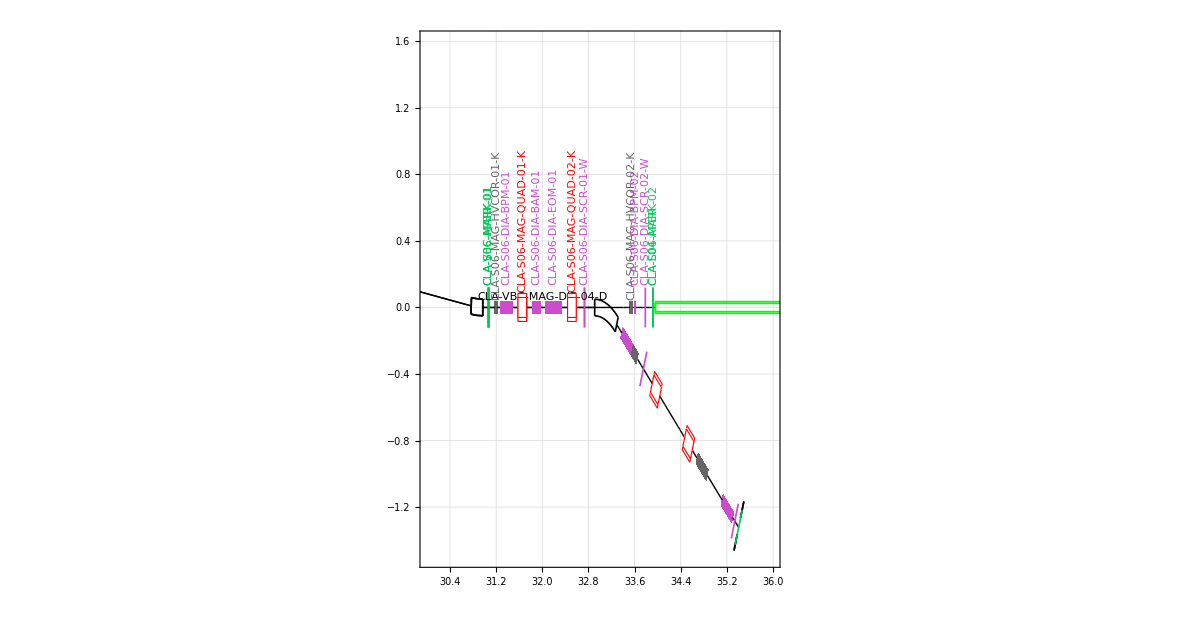

```mathematica
Show[#]&@{MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"},FrameTicks->{LinTicks[30,36,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-1.6,1.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[30,36,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1.6,1.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->False,WidthScale->0.5,GridLines->Automatic,BaseStyle->{FontSize->20,FontFamily->"Helvetica",Black},ImageSize->1200,PlotRange->{{30,36},{-1.5,1.6}}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM2],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"},Lengths->False,WidthScale->0.5,GridLines->Automatic,BaseStyle->{FontSize->20,FontFamily->"Helvetica",Black},ImageSize->1200,PlotRange->{{30,36},{-1.5,1.6}}]}
```

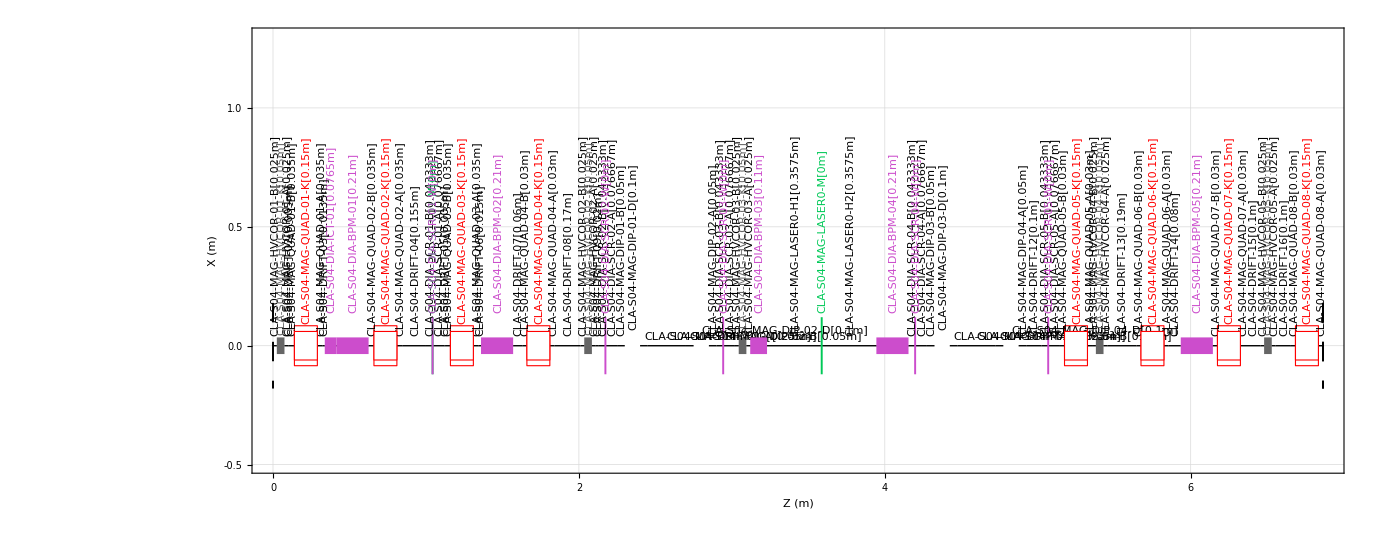

```mathematica
lh=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM]⟦90;;180⟧,Bends->True,Labels->True,Frame->True,DriftLabels->True,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"}, FrameTicks->{LinTicks[0,8,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-1.6,1.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,8,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1.6,1.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->True,WidthScale->0.5,GridLines->Automatic,BaseStyle->{FontSize->10,FontFamily->"Helvetica",Black},ImageSize->1400,PlotRange->{All,{-0.5,1.3}}]
```

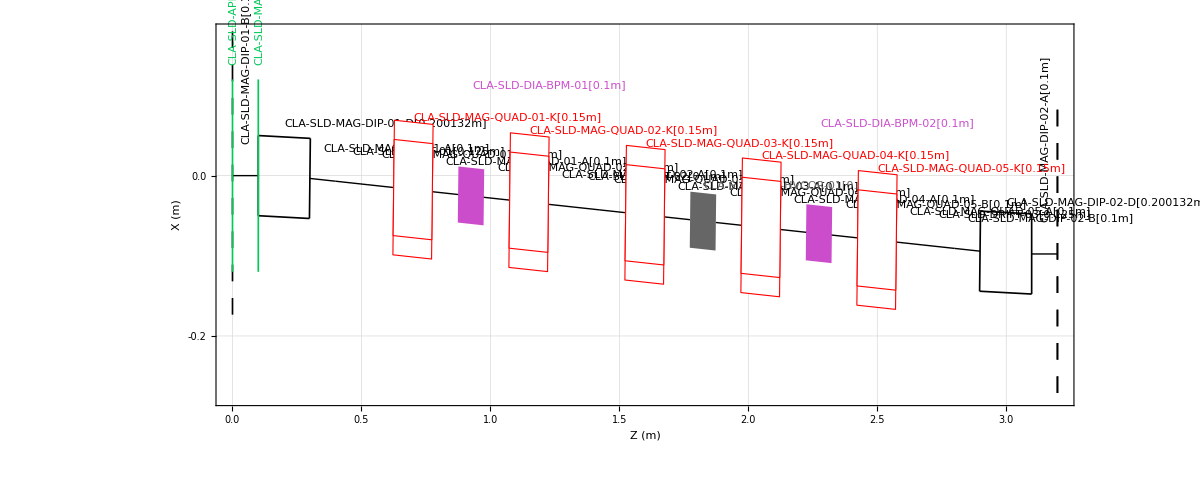

```mathematica
sld=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM⟦379;;407⟧],Bends->True,Labels->True,Frame->True,DriftLabels->True,FrameStyle->Black,TextOscillate->False,Lengths->True,FrameLabel-> {"Z (m)","X (m)"},FrameTicks->{LinTicks[0,3,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,3,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->False,WidthScale->0.5,GridLines->Automatic,BaseStyle->{FontSize->16,FontFamily->"Helvetica",Black},ImageSize->1200,PlotRange->All]
```

```mathematica
(*Export["clara_V10.1_sld.png",sld,ImageResolution->300]*)
```

```mathematica
(*Export["clara_V10.1_lh.png",lh]*)
```

```mathematica
$DRAWLATTICE=CLA;$DRAWLATTICE2=CLA£SP2;$DRAWLATTICE3=CLA£SP3;$DRAWLATTICE4=CLA£EBT£BA1;$DRAWLATTICE5={CLA£S01,CLA£L01,CLA£S02SP1};$DRAWLATTICE6=EBT£INJ;$DRAWLATTICE7=EBT£SP1;
```

```mathematica
$DRAWLATTICEBPM=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE]];$DRAWLATTICEBPM2=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE2]];$DRAWLATTICEBPM3=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE3]];
$DRAWLATTICEBPM4=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE4]];
$DRAWLATTICEBPM5=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE5]];
$DRAWLATTICEBPM6=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE6]];$DRAWLATTICEBPM7=Map[If[StringMatchQ[#⟦1⟧,"*BPM*"]||StringMatchQ[#⟦1⟧,"*BAM*"]||StringMatchQ[#⟦1⟧,"*EOM*"]||StringMatchQ[#⟦1⟧,"*ICT*"],ReplacePart[#,2->"BPM"],If[StringMatchQ[#⟦1⟧,"*COR*"],ReplacePart[#,2->"Kicker"],If[StringMatchQ[#⟦1⟧,"*SCR*W"],ReplacePart[#,2->"Monitor"],#]]]&,MADFlatten[$DRAWLATTICE7]];
```

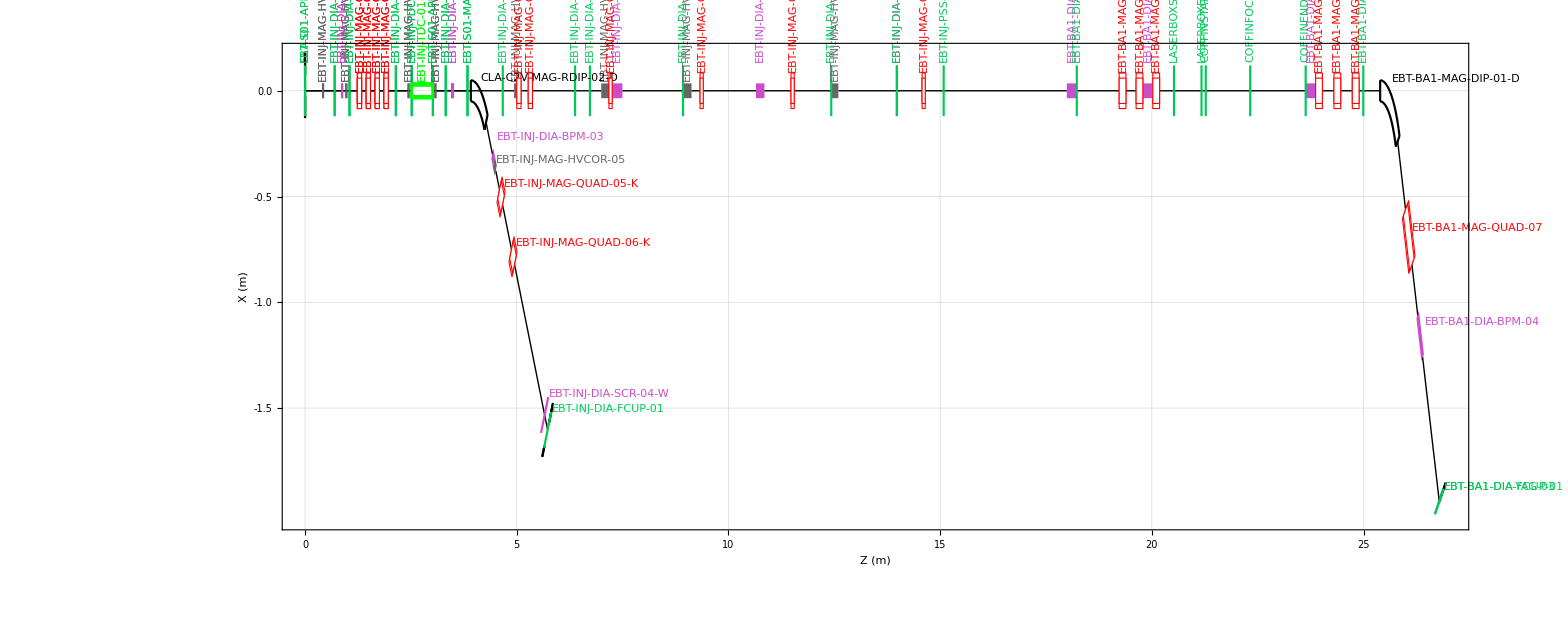

```mathematica
Show[#]&@{MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM6],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"},FrameTicks->{LinTicks[0,36,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-1.6,1.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,36,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1.6,1.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->False,WidthScale->0.5,GridLines->Automatic,BaseStyle->{FontSize->12,FontFamily->"Helvetica",Black},ImageSize->2600(*PlotRange->{{30,36},{-1.5,1.6}}*)],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM7],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"},Lengths->False,WidthScale->0.5,GridLines->Automatic,BaseStyle->{FontSize->12,FontFamily->"Helvetica",Black},ImageSize->2600(*PlotRange->{{30,36},{-1.5,1.6}}*)]}
```

```mathematica
(Select[MADPositions[MADFlatten[CLA£EBT£BA1]]⟦1;;-2⟧,#⟦2,6,1⟧=="EBT£INJ£DIA£YAG£05"&]⟦1,1⟧-Select[MADPositions[MADFlatten[EBT£INJ]]⟦1;;-2⟧,#⟦2,6,1⟧=="EBT£INJ£DIA£YAG£05"&]⟦1,1⟧)
```

{3.16179,-1.25}

```mathematica
Select[MADPositions[MADFlatten[CLA£SP1]]⟦1;;-2⟧,#[[2,6,1]]=="EBT£INJ£DIA£SCR£04£W"&]⟦1,1⟧-Select[MADPositions[MADFlatten[EBT£SP1]]⟦1;;-2⟧,#[[2,6,1]]=="EBT£INJ£DIA£SCR£04£W"&]⟦1,1⟧
```

{3.16179,-1.25}

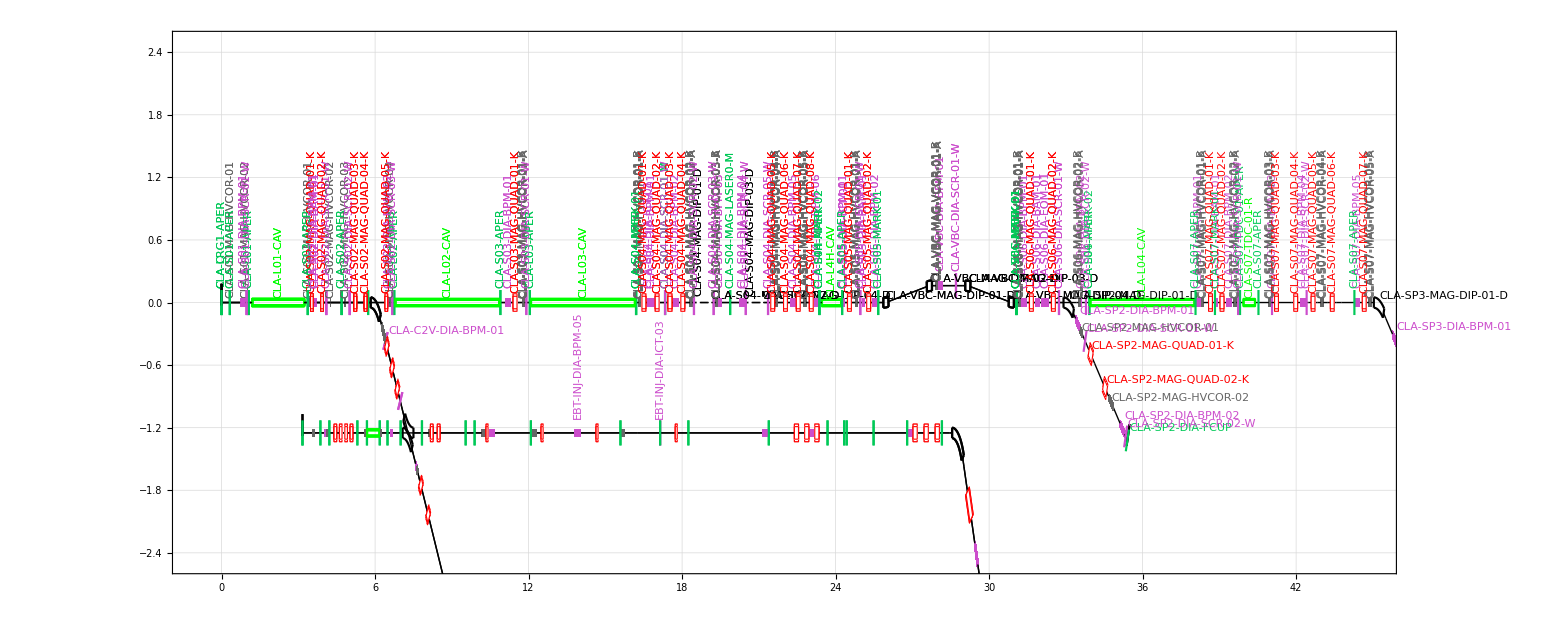
{-Graphics-,clara_V10.1_draw.png}

```mathematica
{Show[#],Export["clara_V10.1_draw.png",%⟦1⟧,ImageResolution->200]}&@{MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM2],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,FrameTicks->{LinTicks[0,50,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-3,6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,50,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-3,6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->True]},Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->20,FontFamily->"Helvetica",Black},ImageSize->3000,PlotRange->{{-1,45},{-2.5,2.5}}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM3],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM4],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM5],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM6],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Offset->(Select[MADPositions[MADFlatten[CLA£EBT£BA1]]⟦1;;-2⟧,#⟦2,6,1⟧=="EBT£INJ£DIA£YAG£05"&]⟦1,1⟧-Select[MADPositions[MADFlatten[EBT£INJ]]⟦1;;-2⟧,#⟦2,6,1⟧=="EBT£INJ£DIA£YAG£05"&]⟦1,1⟧),Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM7],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Offset->(Select[MADPositions[MADFlatten[CLA£SP1]]⟦1;;-2⟧,#[[2,6,1]]=="EBT£INJ£DIA£SCR£04£W"&]⟦1,1⟧-Select[MADPositions[MADFlatten[EBT£SP1]]⟦1;;-2⟧,#[[2,6,1]]=="EBT£INJ£DIA£SCR£04£W"&]⟦1,1⟧),Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}]}
```

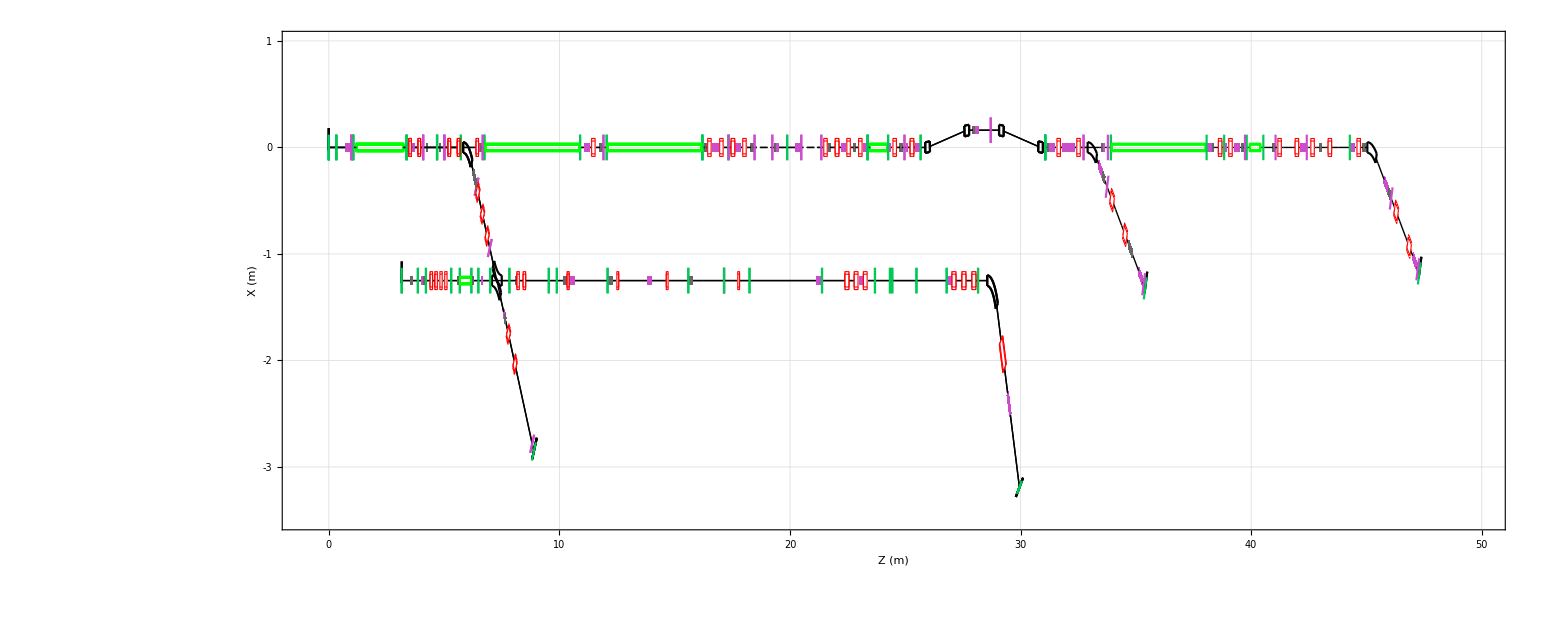
{-Graphics-,clara_V10.1_draw_nolabel.png}

```mathematica
{Show[#],Export["clara_V10.1_draw_nolabel.png",%⟦1⟧,ImageResolution->200]}&@{MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM2],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,FrameTicks->{LinTicks[0,50,MajorTickStyle->Thickness[0.0001],MinorTickStyle->Thickness[0.0001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,1,MajorTickStyle->Thickness[0.0001],MinorTickStyle->Thickness[0.0001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,50,MajorTickStyle->Thickness[0.0001],MinorTickStyle->Thickness[0.0001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-3.5,1,MajorTickStyle->Thickness[0.0001],MinorTickStyle->Thickness[0.0001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->True]},Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->20,FontFamily->"Helvetica",Black},ImageSize->3000,PlotRange->{{-1,50},{-3.5,1}}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM3],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM4],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM5],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM6],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Offset->(Select[MADPositions[MADFlatten[CLA£EBT£BA1]]⟦1;;-2⟧,#⟦2,6,1⟧=="EBT£INJ£DIA£YAG£05"&]⟦1,1⟧-Select[MADPositions[MADFlatten[EBT£INJ]]⟦1;;-2⟧,#⟦2,6,1⟧=="EBT£INJ£DIA£YAG£05"&]⟦1,1⟧),Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}],MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM7],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,FrameLabel-> {"Z (m)","X (m)"},TextOscillate->False,Offset->(Select[MADPositions[MADFlatten[CLA£SP1]]⟦1;;-2⟧,#[[2,6,1]]=="EBT£INJ£DIA£SCR£04£W"&]⟦1,1⟧-Select[MADPositions[MADFlatten[EBT£SP1]]⟦1;;-2⟧,#[[2,6,1]]=="EBT£INJ£DIA£SCR£04£W"&]⟦1,1⟧),Lengths->False,WidthScale->0.5,GridLines->Automatic,LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black}]}
```

## Construct Match through SLD to end FEL

### Bare FODO

```mathematica
LATTICE=MADFlatten[{CLA£FRS}]⟦1;;-22⟧;
```

```mathematica
test=MADFlatten[{CLA£FRS}]⟦1;;50⟧;
```

```mathematica
MADInfo[test]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£FRS£APER | Marker | 0 | --- | --- | --- | CLA£FRS£APER | 0
2 | CLA£FRS£R01£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£B | 0.03
3 | CLA£FRS£R01£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£W | 0.03
4 | CLA£FRS£R01£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£A | 0.06
5 | CLA£FRS£R01£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R01£DIA£BPM£01 | 0.06
6 | CLA£FRS£R01£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£UND£B | 0.07
7 | CLA£FRS£R01£MAG£UND£W£H1 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1 | 0.445
8 | CLA£FRS£R01£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R01£MARK£01 | 0.445
9 | CLA£FRS£R01£MAG£UND£W£H2 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H2 | 0.82
10 | CLA£FRS£R01£MAG£UND£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£UND£A | 0.83
11 | CLA£FRS£R01£MAG£DIP£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£01£B | 0.84
12 | CLA£FRS£R01£MAG£DIP£01£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R01£MAG£DIP£01£D | 0.890008
13 | CLA£FRS£R01£MAG£DIP£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£01£A | 0.900008
14 | CLA£FRS£R01£MAG£DIP£02£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£02£B | 0.910008
15 | CLA£FRS£R01£MAG£DIP£02£D | SectorBend | 0.100017 | 0 | --- | 0.0349066 | CLA£FRS£R01£MAG£DIP£02£D | 1.01002
16 | CLA£FRS£R01£MAG£DIP£02£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£02£A | 1.02002
17 | CLA£FRS£R01£MAG£DIP£03£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£03£B | 1.03002
18 | CLA£FRS£R01£MAG£DIP£03£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R01£MAG£DIP£03£D | 1.08003
19 | CLA£FRS£R01£MAG£DIP£03£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£03£A | 1.09003
20 | CLA£FRS£R01£MAG£QUAD£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£QUAD£01£B | 1.10003
21 | CLA£FRS£R01£MAG£QUAD£01£K | Quadrupole | 0.1 | -1. | --- | --- | CLA£FRS£R01£MAG£QUAD£01£K | 1.20003
22 | CLA£FRS£R01£MAG£QUAD£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£QUAD£01£A | 1.21003
23 | CLA£FRS£R02£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£B | 1.24003
24 | CLA£FRS£R02£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£W | 1.24003
25 | CLA£FRS£R02£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£A | 1.27003
26 | CLA£FRS£R02£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R02£DIA£BPM£01 | 1.27003
27 | CLA£FRS£R02£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£UND£B | 1.28003
28 | CLA£FRS£R02£MAG£UND£W£H1 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R02£MAG£UND£W£H1 | 1.65503
29 | CLA£FRS£R02£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R02£MARK£01 | 1.65503
30 | CLA£FRS£R02£MAG£UND£W£H2 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R02£MAG£UND£W£H2 | 2.03003
31 | CLA£FRS£R02£MAG£UND£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£UND£A | 2.04003
32 | CLA£FRS£R02£MAG£DIP£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£01£B | 2.05003
33 | CLA£FRS£R02£MAG£DIP£01£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R02£MAG£DIP£01£D | 2.10004
34 | CLA£FRS£R02£MAG£DIP£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£01£A | 2.11004
35 | CLA£FRS£R02£MAG£DIP£02£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£02£B | 2.12004
36 | CLA£FRS£R02£MAG£DIP£02£D | SectorBend | 0.100017 | 0 | --- | 0.0349066 | CLA£FRS£R02£MAG£DIP£02£D | 2.22006
37 | CLA£FRS£R02£MAG£DIP£02£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£02£A | 2.23006
38 | CLA£FRS£R02£MAG£DIP£03£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£03£B | 2.24006
39 | CLA£FRS£R02£MAG£DIP£03£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R02£MAG£DIP£03£D | 2.29007
40 | CLA£FRS£R02£MAG£DIP£03£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£03£A | 2.30007
41 | CLA£FRS£R02£MAG£QUAD£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£QUAD£01£B | 2.31007
42 | CLA£FRS£R02£MAG£QUAD£01£K | Quadrupole | 0.1 | -1. | --- | --- | CLA£FRS£R02£MAG£QUAD£01£K | 2.41007
43 | CLA£FRS£R02£MAG£QUAD£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£QUAD£01£A | 2.42007
44 | CLA£FRS£R03£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R03£DIA£SCR£01£B | 2.45007
45 | CLA£FRS£R03£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R03£DIA£SCR£01£W | 2.45007
46 | CLA£FRS£R03£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R03£DIA£SCR£01£A | 2.48007
47 | CLA£FRS£R03£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R03£DIA£BPM£01 | 2.48007
48 | CLA£FRS£R03£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R03£MAG£UND£B | 2.49007
49 | CLA£FRS£R03£MAG£UND£W£H1 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R03£MAG£UND£W£H1 | 2.86507
50 | CLA£FRS£R03£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R03£MARK£01 | 2.86507

Total Length = 2.86507 m

```mathematica
Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[2,1,1]]-Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[1,1,1]]
```

1.21002

So structure of CLARA FODO is

```mathematica
marker[M11D0CMS]
marker[M11D0CME]
drift[M11D0CD1H2,(1.21002-0.1)/2,"M11D0CD1H2"]
drift[M11D0CD2,1.21002-0.1,"M11D0CD2"]
drift[M11D0CD1H1,(1.21002-0.1)/2,"M11D0CD1H1"]
quad[M11D0CQ1,0.10,3,"M11D0CQ1"]
quad[M11D0CQ2,0.10,-3,"M11D0CQ2"]
line[M11D0RC,{M11D0CMS,M11D0CD1H1,M11D0CQ1,M11D0CD2,M11D0CQ2,M11D0CD1H2,M11D0CME}]
```

```mathematica
MADInfo[M11D0RC]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | M11D0CMS | Marker | 0 | --- | --- | --- |  | 0
2 | M11D0CD1H1 | Drift | 0.55501 | --- | --- | --- | M11D0CD1H1 | 0.55501
3 | M11D0CQ1 | Quadrupole | 0.1 | 3 | --- | --- | M11D0CQ1 | 0.65501
4 | M11D0CD2 | Drift | 1.11002 | --- | --- | --- | M11D0CD2 | 1.76503
5 | M11D0CQ2 | Quadrupole | 0.1 | -3 | --- | --- | M11D0CQ2 | 1.86503
6 | M11D0CD1H2 | Drift | 0.55501 | --- | --- | --- | M11D0CD1H2 | 2.42004
7 | M11D0CME | Marker | 0 | --- | --- | --- |  | 2.42004

Total Length = 2.42004 m

```mathematica
MADWrite["M11D0R",M11D0RC];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g M11D0R.mff",Word]];
MADStringWrite["M11D0R","eopt,add;\n"];
MADStringWrite["M11D0R","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.135]<>";\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.1\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.2\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.3\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.4\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.5\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.6\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.7\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.8\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.9\n"];
MADStringWrite["M11D0R","select,twiss,full;\ntwiss,tape=twiss.txt;\n"];
MADStringWrite["M11D0R","select,optics,full;\noptics,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat M11D0R.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < M11D0R.mff > M11D0R_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < M11D0R.mff > M11D0R.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->True];
Select[ReadList["M11D0R.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&];
```

{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}

Variables (re-)assigned: {GAMTR,ALFA,XIY,XIX,QY,QX,CIRCUM,DELTA,TYPE,COMMENT,ORIGIN,DATE,TIME}

Variables (re-)assigned: {NAME,S,BETX,BETY,DX,ALFX,ALFY,MUX,MUY,DPX,DY,DPY}

```mathematica
MatchTwiss=First[#]&/@{BETX,ALFX,BETY,ALFY}
```

{6.86207,-1.04511,6.86207,1.04511}

```mathematica
ToString[NumberForm[MADLength[M11D0RC],3]]
```

2.42

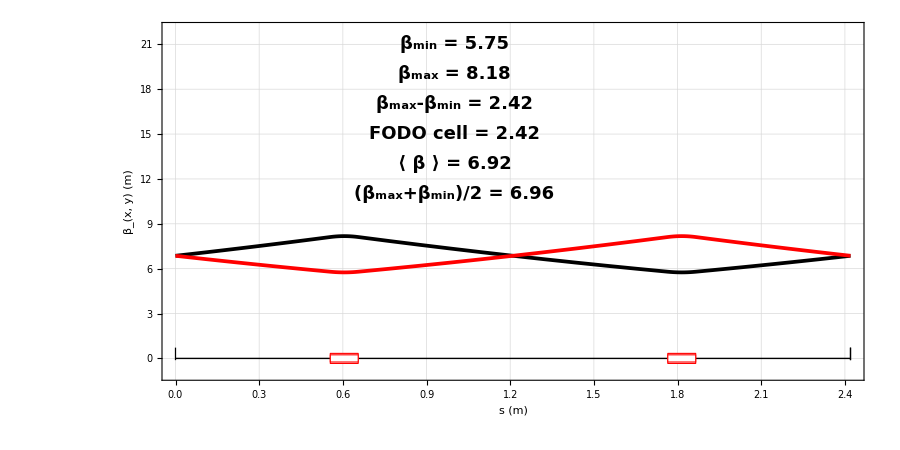

done

```mathematica
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{0.3,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["β_min = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,21}],
Text[Style["β_max = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,19}],
Text[Style["β_max-β_min = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,17}],
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RC],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,15}],
Text[Style[ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,13}],
Text[Style["(β_max+β_min)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,11}]},Prolog->MADDraw[Select[MADFlatten[M11D0RC], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,22}},ImageSize->900,AspectRatio->0.5];
(*{Show[#],Export["output/run_B_pw01_twiss_mma.png",#,ImageResolution->400],Export["output/run_B_pw01_twiss_mma.eps",#,ImageSize->900,ImageResolution->200]}&@*)ShowLegend[plt,lgd]
Print["done"]
```

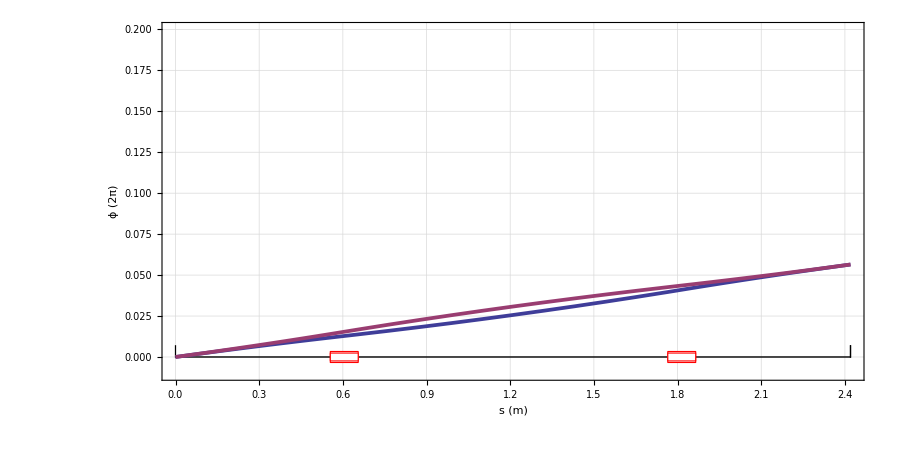

done

```mathematica
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{ColorData[1,2],Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["ϕ_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["ϕ_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};plt=mfsPlot[{{S,MUX},{S,MUY}},Prolog->MADDraw[Select[MADFlatten[M11D0RC], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->0.02]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"ϕ (2π)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-0.01,0.2}},ImageSize->900,AspectRatio->0.5];
(*{Show[#],Export["output/run_B_pw01_twiss_mma.png",#,ImageResolution->400],Export["output/run_B_pw01_twiss_mma.eps",#,ImageSize->900,ImageResolution->200]}&@*)ShowLegend[plt,lgd]
Print["done"]
```

scan over k -values

```mathematica
vals=Table[i,{i,0.8,15.6,0.4}];
```

```mathematica
vals
```

{0.8,1.2,1.6,2.,2.4,2.8,3.2,3.6,4.,4.4,4.8,5.2,5.6,6.,6.4,6.8,7.2,7.6,8.,8.4,8.8,9.2,9.6,10.,10.4,10.8,11.2,11.6,12.,12.4,12.8,13.2,13.6,14.,14.4,14.8,15.2,15.6}

```mathematica
vals2=(1/((M11D0CQ1⟦1,3⟧/2)#) 1/(MADLength[M11D0RC]/2))&[vals]
```

{20.6608,13.7739,10.3304,8.26433,6.88694,5.90309,5.1652,4.59129,4.13216,3.75651,3.44347,3.17859,2.95155,2.75478,2.5826,2.43068,2.29565,2.17482,2.06608,1.9677,1.87826,1.79659,1.72173,1.65287,1.58929,1.53043,1.47577,1.42488,1.37739,1.33296,1.2913,1.25217,1.21534,1.18062,1.14782,1.1168,1.08741,1.05953}

```mathematica
betavs=Reap[(marker[M11D0CMS]
marker[M11D0CME]
drift[M11D0CD1H2,(1.21002-0.1)/2,"M11D0CD1H2"]
drift[M11D0CD2,1.21002-0.1,"M11D0CD2"]
drift[M11D0CD1H1,(1.21002-0.1)/2,"M11D0CD1H1"]
quad[M11D0CQ1,0.10,#,"M11D0CQ1"]
quad[M11D0CQ2,0.10,-#,"M11D0CQ2"]
line[M11D0RC,{M11D0CMS,M11D0CD1H1,M11D0CQ1,M11D0CD2,M11D0CQ2,M11D0CD1H2,M11D0CME}]
MADWrite["M11D0R",M11D0RC];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g M11D0R.mff",Word]];
MADStringWrite["M11D0R","eopt,add;\n"];
	MADStringWrite["M11D0R","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.05\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.10\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.15\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.20\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.25\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.30\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.35\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.40\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.45\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.50\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.55\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.60\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.65\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.70\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.75\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.80\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.85\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.90\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.95\n"];
MADStringWrite["M11D0R","select,twiss,full;\ntwiss,tape=twiss.txt;\n"];
MADStringWrite["M11D0R","select,optics,full;\noptics,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat M11D0R.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < M11D0R.mff > M11D0R_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < M11D0R.mff > M11D0R.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
Select[ReadList["M11D0R.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&];
Sow[Mean[BETX]];
Sow[First[#]&/@{BETX,ALFX,BETY,ALFY}];
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["k = "<>ToString[#],FontFamily->"Helvetica",Bold,FontSize->14],{1,21}],
Text[Style["β_min = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,19}],
Text[Style["β_max = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,17}],
Text[Style["β_max-β_min = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,15}],
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RC],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,13}],
Text[Style[ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,11}],
Text[Style["(β_max+β_min)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,9}]},Prolog->MADDraw[Select[MADFlatten[M11D0RC], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,30}},ImageSize->700,AspectRatio->0.5];
Sow[Show[plt]];

)&/@vals]⟦2,1⟧;
```

```mathematica
GraphicsGrid[Partition[betavs⟦3;;-1;;3⟧,2],Frame->All];
```

```mathematica
Directory[]
```

D:\CLARA\V10

```mathematica
(*Export["clara_frs_fodo_k1.png",betavs⟦4⟧,ImageResolution->200]*)
```

clara_frs_fodo_k1.png

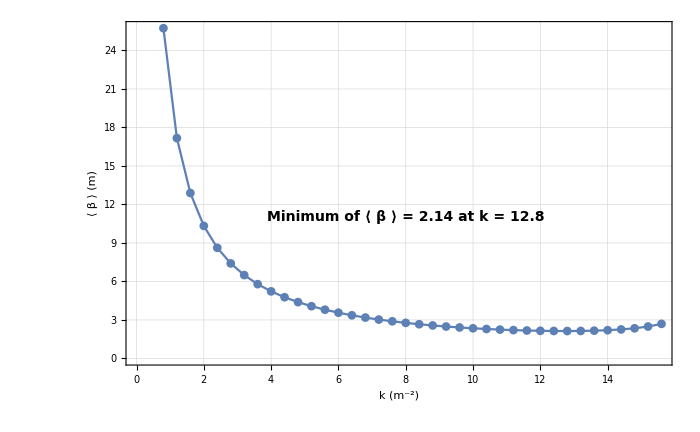

```mathematica
plt1=ListLinePlot[{Transpose[{vals,Take[betavs,{1,-1,3}]}]},Epilog->Text[Style["Minimum of "<>ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-1,3}]],3]]<>" at k = "<>ToString[vals[[Position[#,Min[#]]&[Take[betavs,{1,-1,3}]]⟦1,1⟧]]],FontFamily->"Helvetica",Bold,FontSize->14],{8,11}],PlotMarkers->Automatic,Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{ToString[AngleBracket["β"]]<>" (m)",""},{"k (m^-2)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->700,PlotRange->{{0,QuantityMagnitude[Last[vals]]},All}]
```

```mathematica
(*Export["clara_frs_fodo_kscan.png",plt1,ImageResolution->200]*)
```

```mathematica
plt2=ListLinePlot[{Transpose[{vals2,Take[betavs,{1,-1,3}]}]},Epilog->Text[Style["MAD: Minimum of "<>ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-1,3}]],3]],FontFamily->"Helvetica",Bold,ColorData[97,1],FontSize->14],{6,24}],PlotMarkers->Automatic,Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{ToString[AngleBracket["β"]]<>" (m)",""},{"1/(k l)1/L (1)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImagePadding->100,ImageSize->800,PlotRange->{{0,QuantityMagnitude[First[vals2]]+1},{0,28}}];
```

```mathematica
plt3=Plot[{(MADLength[M11D0RC]/2 )x^2(x^2-1)^(-1/2),(MADLength[M11D0RC]/2 )x},{x,0,QuantityMagnitude[First[vals2]]+1},Frame->{False,False,False,True},Epilog->{Style[Text["Wiedemann: Minimum of "<>ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[FindMinimum[(MADLength[M11D0RC]/2 )x^2(x^2-1)^(-1/2),{x,1.1}]⟦1⟧,{3,2}]],{5.4,22}],ColorData[97,3],Bold,FontSize->14],Style[Text["Pfluger",{6,20}],ColorData[97,4],Bold,FontSize->14]},PlotStyle->{ColorData[97,3],ColorData[97,4]},FrameTicks->{{None,Range[0,25,5]},{Automatic,None}},LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},PlotRange->{{0,QuantityMagnitude[First[vals2]]+1},{0,28}},ImagePadding->100,ImageSize->800];
```

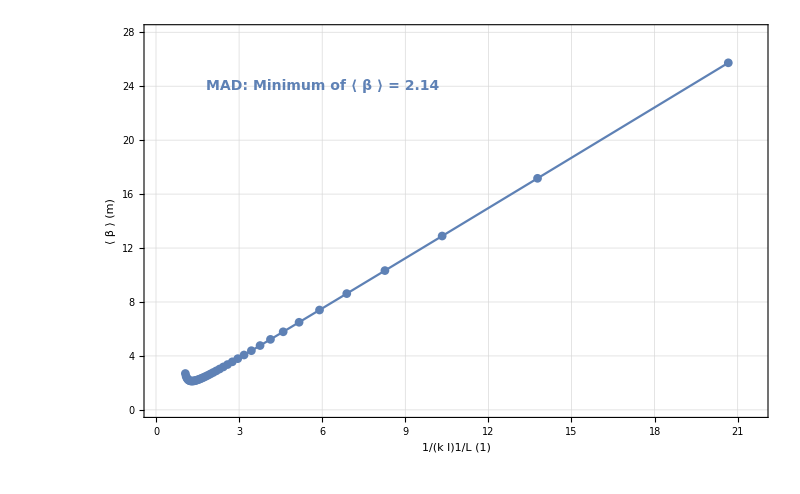
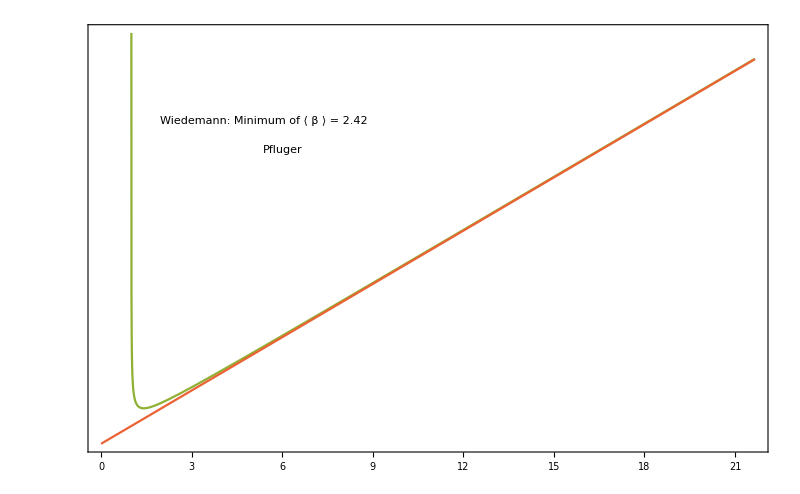

```mathematica
plt4=Overlay[{plt2,plt3}]
```

```mathematica
(*Export["clara_frs_fodo_rescale.png",plt4,ImageResolution->200]*)
```

So for tunability lets pick a k=2, k=11.6 and a k=14 case

```mathematica
vals
```

{0.8,1.2,1.6,2.,2.4,2.8,3.2,3.6,4.,4.4,4.8,5.2,5.6,6.,6.4,6.8,7.2,7.6,8.,8.4,8.8,9.2,9.6,10.,10.4,10.8,11.2,11.6,12.,12.4,12.8,13.2,13.6,14.,14.4,14.8,15.2,15.6}

```mathematica
LATTICE=$LATTICE=MADFlatten[{CLA£SLD,CLA£FMS,CLA£FRS,CLA£FAB,CLA£PFD}];
```

```mathematica
matchedqs={#⟦1⟧,#⟦4⟧}&/@Select[MADFlatten[$LATTICE],#[[2]]=="Quadrupole"&]
```

{{CLA£SLD£MAG£QUAD£01£K,14.0029},{CLA£SLD£MAG£QUAD£02£K,15.7358},{CLA£SLD£MAG£QUAD£03£K,-18.9731},{CLA£SLD£MAG£QUAD£04£K,15.7358},{CLA£SLD£MAG£QUAD£05£K,14.0029},{CLA£FMS£MAG£QUAD£01£K,-1.},{CLA£FMS£MAG£QUAD£02£K,-1.},{CLA£FMS£MAG£QUAD£03£K,-1.},{CLA£FMS£MAG£QUAD£04£K,-1.},{CLA£FMS£MAG£QUAD£05£K,-1.},{CLA£FRS£R01£MAG£QUAD£01£K,-1.},{CLA£FRS£R02£MAG£QUAD£01£K,-1.},{CLA£FRS£R03£MAG£QUAD£01£K,-1.},{CLA£FRS£R04£MAG£QUAD£01£K,-1.},{CLA£FRS£R05£MAG£QUAD£01£K,-1.},{CLA£FRS£R06£MAG£QUAD£01£K,-1.},{CLA£FRS£R07£MAG£QUAD£01£K,-1.},{CLA£FRS£R08£MAG£QUAD£01£K,-1.},{CLA£FRS£R09£MAG£QUAD£01£K,-1.},{CLA£FRS£R10£MAG£QUAD£01£K,-1.},{CLA£FRS£R11£MAG£QUAD£01£K,-1.},{CLA£FRS£R12£MAG£QUAD£01£K,-1.},{CLA£FRS£R13£MAG£QUAD£01£K,-1.},{CLA£FRS£R14£MAG£QUAD£01£K,-1.},{CLA£FRS£R15£MAG£QUAD£01£K,-1.},{CLA£FRS£R16£MAG£QUAD£01£K,-1.},{CLA£FRS£R17£MAG£QUAD£01£K,-1.},{CLA£PFD£MAG£QUAD£01£K,-1.46779},{CLA£PFD£MAG£QUAD£02£K,-0.64689},{CLA£PFD£MAG£QUAD£03£K,-2.01504},{CLA£PFD£MAG£QUAD£04£K,0.98372},{CLA£PFD£MAG£QUAD£05£K,4.25217},{CLA£PFD£MAG£QUAD£06£K,-2.6469}}

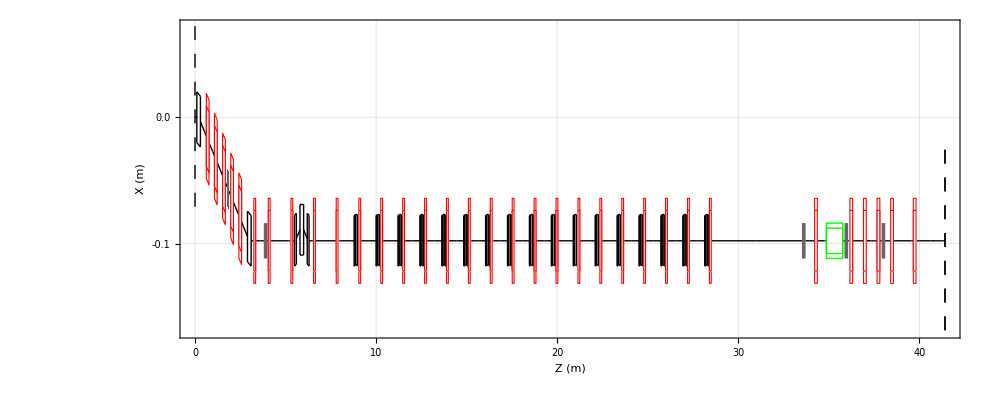

```mathematica
(*{Show[#],Export["dog5.png",#,ImageResolution->600],Export["dog5.eps",#,ImageResolution->400,ImageSize->700]}&@*)MADDraw[ReplacePart[#,7->StringReplace[#[[1]],{"£"->"-","$"->"-"}]]&/@Select[MADFlatten[$LATTICE],#⟦3⟧>0&],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.002],FrameLabel-> {"Z (m)","X (m)"},FrameTicks->{LinTicks[0,43.5,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.3,0.3,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,43.5,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.3,0.3,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},WidthScale->0.2,GridLines->Automatic,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},LabelStyle->Black,PlotRange->{Automatic,{0.1,-0.2}},AspectRatio->0.4,ImageSize->1000]
```

```mathematica
LATTICE[[83]]
```

{CLA£FRS£R01£MAG£UND£W£H2,Drift,0.375,---,---,---,CLA£FRS£R01£MAG£UND£W£H2}

```mathematica
Position[LATTICE,"CLA£FRS£R01£MAG£UND£W£H2"]⟦1,1⟧
```

83

```mathematica
drift[CLA£FRS£R01£MAG£UND£W£H21,0.08001,"CLA£FRS£R01£MAG£UND£W£H21"];
marker[CLA£FRS£R01£MAG£UND£W£H2M];
drift[CLA£FRS£R01£MAG£UND£W£H22,0.29499,"CLA£FRS£R01£MAG£UND£W£H21"];
```

```mathematica
LATTICE2=MADFlatten[ReplacePart[LATTICE,Position[LATTICE,"CLA£FRS£R01£MAG£UND£W£H2"]⟦1,1⟧->MADFlatten[{CLA£FRS£R01£MAG£UND£W£H21,CLA£FRS£R01£MAG£UND£W£H2M,CLA£FRS£R01£MAG£UND£W£H22}]]];
```

```mathematica
Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[11]]
```

{{9.04868,-0.0977239},{quadrupole,0.1,0,,0,{CLA£FRS£R01£MAG£QUAD£01£K,Quadrupole,0.1,-1.,---,---,CLA£FRS£R01£MAG£QUAD£01£K}},0.}

```mathematica
Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[11,1,1]]-Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[10,1,1]]
```

1.25002

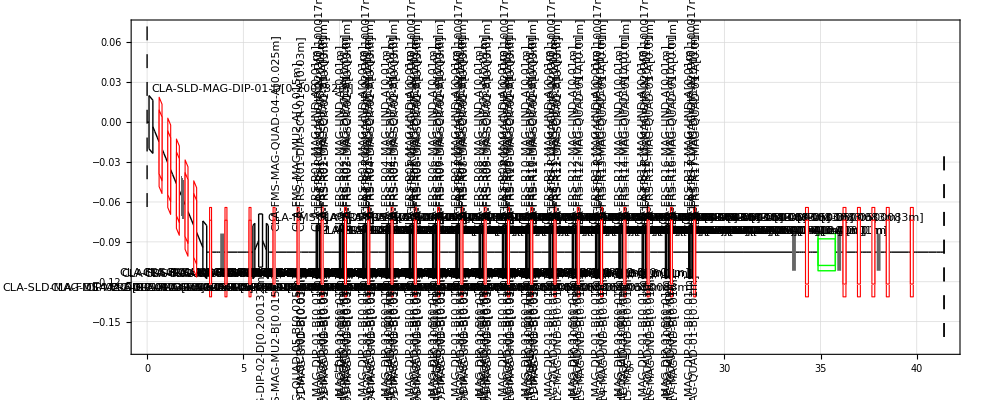

```mathematica
(*{Show[#],Export["dog5.png",#,ImageResolution->600],Export["dog5.eps",#,ImageResolution->400,ImageSize->700]}&@*)MADDraw[ReplacePart[#,7->StringReplace[#[[1]],{"£"->"-","$"->"-"}]]&/@Select[MADFlatten[$LATTICE],#⟦3⟧>0&],Bends->True,Labels->True,Lengths->True,Frame->True,DriftLabels->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.002],FrameLabel-> {"Z (m)","X (m)"},FrameTicks->{LinTicks[0,43.5,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.3,0.3,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,43.5,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.3,0.3,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},WidthScale->0.2,GridLines->Automatic,BaseStyle->{FontSize->10,Bold,FontFamily->"Helvetica"},LabelStyle->Black,PlotRange->{{7.5,9.5},{0.1,-0.2}},AspectRatio->0.4,ImageSize->1000]
```

Determine the starting Twiss from the SLD

```mathematica
StartTwiss={0.739956826316,2.0,2.30131452265,2.0};
```

```mathematica
LATTICE=$LATTICE=MADFlatten[{CLA£SLD}];
```

```mathematica
MADInfo[LATTICE]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£SLD£APER | Marker | 0 | --- | --- | --- | CLA£SLD£APER | 0
2 | CLA£SLD£MAG£DIP£01£B | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£DIP£01£B | 0.1
3 | CLA£SLD£MARK£01 | Marker | 0 | --- | --- | --- | CLA£SLD£MARK£01 | 0.1
4 | CLA£SLD£MAG£DIP£01£D | SectorBend | 0.200132 | 0 | --- | 0.0349066 | CLA£SLD£MAG£DIP£01£D | 0.300132
5 | CLA£SLD£MAG£DIP£01£A | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£DIP£01£A | 0.400132
6 | CLA£SLD£DRIFT£01 | Drift | 0.125 | --- | --- | --- | CLA£SLD£DRIFT£01 | 0.525132
7 | CLA£SLD£MAG£QUAD£01£B | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£01£B | 0.625132
8 | CLA£SLD£MAG£QUAD£01£K | Quadrupole | 0.15 | 14.0029 | --- | --- | CLA£SLD£MAG£QUAD£01£K | 0.775132
9 | CLA£SLD£MAG£QUAD£01£A | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£01£A | 0.875132
10 | CLA£SLD£DIA£BPM£01 | Drift | 0.1 | --- | --- | --- | CLA£SLD£DIA£BPM£01 | 0.975132
11 | CLA£SLD£MAG£QUAD£02£B | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£02£B | 1.07513
12 | CLA£SLD£MAG£QUAD£02£K | Quadrupole | 0.15 | 15.7358 | --- | --- | CLA£SLD£MAG£QUAD£02£K | 1.22513
13 | CLA£SLD£MAG£QUAD£02£A | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£02£A | 1.32513
14 | CLA£SLD£DRIFT£02 | Drift | 0.1 | --- | --- | --- | CLA£SLD£DRIFT£02 | 1.42513
15 | CLA£SLD£MAG£QUAD£03£B | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£03£B | 1.52513
16 | CLA£SLD£MAG£QUAD£03£K | Quadrupole | 0.15 | -18.9731 | --- | --- | CLA£SLD£MAG£QUAD£03£K | 1.67513
17 | CLA£SLD£MAG£QUAD£03£A | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£03£A | 1.77513
18 | CLA£SLD£MAG£HVCOR£01 | Kicker | 0.1 | --- | 0. | 0. | CLA£SLD£MAG£HVCOR£01 | 1.87513
19 | CLA£SLD£MAG£QUAD£04£B | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£04£B | 1.97513
20 | CLA£SLD£MAG£QUAD£04£K | Quadrupole | 0.15 | 15.7358 | --- | --- | CLA£SLD£MAG£QUAD£04£K | 2.12513
21 | CLA£SLD£MAG£QUAD£04£A | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£04£A | 2.22513
22 | CLA£SLD£DIA£BPM£02 | Drift | 0.1 | --- | --- | --- | CLA£SLD£DIA£BPM£02 | 2.32513
23 | CLA£SLD£MAG£QUAD£05£B | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£05£B | 2.42513
24 | CLA£SLD£MAG£QUAD£05£K | Quadrupole | 0.15 | 14.0029 | --- | --- | CLA£SLD£MAG£QUAD£05£K | 2.57513
25 | CLA£SLD£MAG£QUAD£05£A | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£QUAD£05£A | 2.67513
26 | CLA£SLD£DRIFT£03 | Drift | 0.125 | --- | --- | --- | CLA£SLD£DRIFT£03 | 2.80013
27 | CLA£SLD£MAG£DIP£02£B | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£DIP£02£B | 2.90013
28 | CLA£SLD£MAG£DIP£02£D | SectorBend | 0.200132 | 0 | --- | -0.0349066 | CLA£SLD£MAG£DIP£02£D | 3.10026
29 | CLA£SLD£MAG£DIP£02£A | Drift | 0.1 | --- | --- | --- | CLA£SLD£MAG£DIP£02£A | 3.20026

Total Length = 3.20026 m

```mathematica
MADWrite["clasld",LATTICE];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g clasld.mff",Word]];
ReadList["!sed -i s/CLA//g clasld.mff",Word];
MADStringWrite["clasld","eopt,add;\nINITIAL:BETA0,&\n
BETX="<>ToString[StartTwiss⟦1⟧]<>",ALFX="<>ToString[StartTwiss⟦2⟧]<>",&\n
BETY="<>ToString[StartTwiss⟦3⟧]<>",ALFY="<>ToString[StartTwiss⟦4⟧]<>",&\n
dx=0,dpx=0,energy=0.250;\n"];
MADStringWrite["clasld","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["clasld","split,name=b1,fraction=0.1\n"];
MADStringWrite["clasld","split,name=b2,fraction=0.2\n"];
MADStringWrite["clasld","split,name=b3,fraction=0.3\n"];
MADStringWrite["clasld","split,name=b4,fraction=0.4\n"];
MADStringWrite["clasld","split,name=b5,fraction=0.5\n"];
MADStringWrite["clasld","split,name=b6,fraction=0.6\n"];
MADStringWrite["clasld","split,name=b7,fraction=0.7\n"];
MADStringWrite["clasld","split,name=b8,fraction=0.8\n"];
MADStringWrite["clasld","split,name=b9,fraction=0.9\n"];
MADStringWrite["clasld","select,twiss,full;\ntwiss,beta0=initial,tape=twiss.txt;\n"];
MADStringWrite["clasld","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
ReadList["!Mad8dl < clasld.mff > clasld_out",Word];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
Select[ReadList["clasld.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&];
```

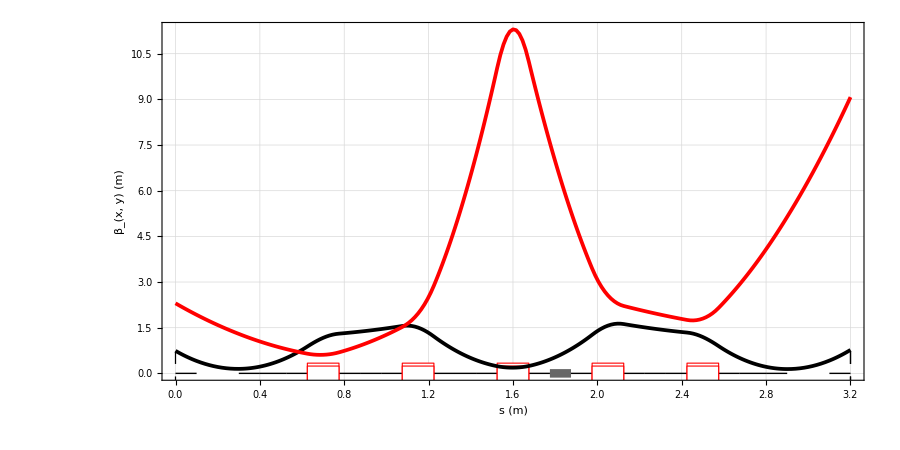

done

```mathematica
linethick=0.003;
legthick=0.02;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{0.3,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Prolog->MADDraw[Select[MADFlatten[LATTICE], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},ImageSize->900,AspectRatio->0.5];
(*{Show[#],Export["output/run_B_pw01_twiss_mma.png",#,ImageResolution->400],Export["output/run_B_pw01_twiss_mma.eps",#,ImageSize->900,ImageResolution->200]}&@*)ShowLegend[plt,lgd]
Print["done"]
```

```mathematica
MADWrite["clasld",LATTICE];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g clasld.mff",Word]];
ReadList["!sed -i s/CLA//g clasld.mff",Word];
MADStringWrite["dglg2","betinix="<>ToString[StartTwiss⟦1⟧]<>";\n"];
MADStringWrite["dglg2","alfinix="<>ToString[StartTwiss⟦2⟧]<>";\n"];
MADStringWrite["dglg2","betiniy="<>ToString[StartTwiss⟦3⟧]<>";\n"];
MADStringWrite["dglg2","alfiniy="<>ToString[StartTwiss⟦4⟧]<>";\n"];;
MADStringWrite["clasld","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["clasld","match,betx=betinix,bety=betiniy,alfx=alfinix,alfy=alfiniy;\n"];
(*MADStringWrite["clasld","vary,"<>StringReplace[Select[MADFlatten[$LATTICE],#[[2]]=="Quadrupole"&]⟦3,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];*)
MADStringWrite["clasld","vary,betinix,step=0.1,lower=0,upper=10;\n"];
MADStringWrite["clasld","vary,alfinix,step=0.1,lower=0,upper=4;\n"];
MADStringWrite["clasld","vary,betiniy,step=0.1,lower=0,upper=10;\n"];
MADStringWrite["clasld","vary,alfiniy,step=0.1,lower=0,upper=4;\n"];
MADStringWrite["clasld","constraint,#e,betx=betinix;\n"];
MADStringWrite["clasld","constraint,#e,alfx=-alfinix;\n"];
MADStringWrite["clasld","constraint,#e,bety=betiniy;\n"];
MADStringWrite["clasld","constraint,#e,alfy=-alfiniy;\n"];
(*MADStringWrite["clasld","constraint,#s/#e,betx<20,bety<10;\n"];
MADStringWrite["clasld","constraint,#s/#e,betx>1,bety>1;\n"];*)
MADStringWrite["clasld","simplex,calls=5000000,tolerance=1.0E-10;\n"];
MADStringWrite["clasld","endmatch;\n"];
MADStringWrite["clasld","value,betinix,alfinix\n"];
MADStringWrite["clasld","value,betiniy,alfiniy\n"];
MADStringWrite["clasld","split,name=b1,fraction=0.1\n"];
MADStringWrite["clasld","split,name=b2,fraction=0.2\n"];
MADStringWrite["clasld","split,name=b3,fraction=0.3\n"];
MADStringWrite["clasld","split,name=b4,fraction=0.4\n"];
MADStringWrite["clasld","split,name=b5,fraction=0.5\n"];
MADStringWrite["clasld","split,name=b6,fraction=0.6\n"];
MADStringWrite["clasld","split,name=b7,fraction=0.7\n"];
MADStringWrite["clasld","split,name=b8,fraction=0.8\n"];
MADStringWrite["clasld","split,name=b9,fraction=0.9\n"];
MADStringWrite["clasld","select,twiss,full;\ntwiss,betx=betinix,bety=betiniy,alfx=alfinix,alfy=alfiniy,tape=twiss.txt;\n"];
MADStringWrite["clasld","select,optics,full;\noptics,betx=betinix,bety=betiniy,alfx=alfinix,alfy=alfiniy,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
ReadList["!Mad8dl < clasld.mff > clasld_out",Word];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
Select[ReadList["clasld.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&]
```

{ MTCOND.  Last value of the penalty function:  4.858291E-11}

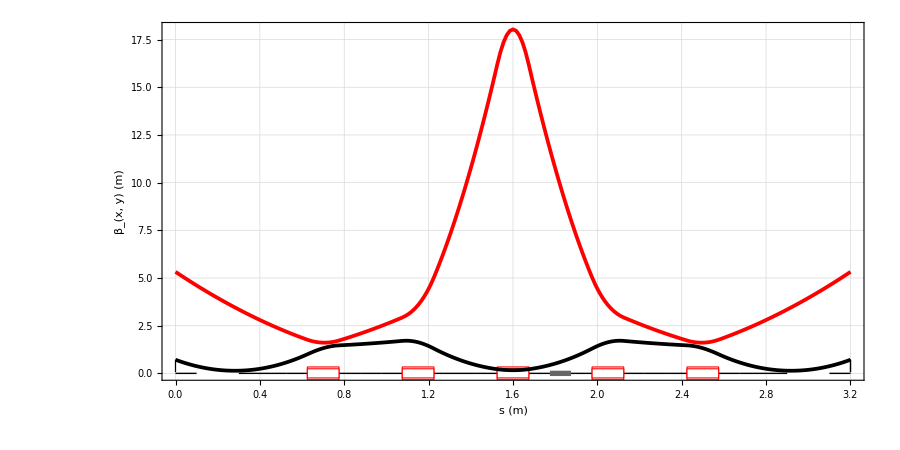

done

```mathematica
linethick=0.003;
legthick=0.02;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{0.3,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Prolog->MADDraw[Select[MADFlatten[LATTICE], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},ImageSize->900,AspectRatio->0.5,PlotRange->All];
ShowLegend[plt,lgd]
Print["done"]
```

```mathematica
(*Export["clara_dglg_twiss.png",ShowLegend[plt,lgd],ImageResolution->200]*)
```

```mathematica
matchedtwiss=StringCases[#,"Value of expression \""~~twiss:(WordCharacter|DigitCharacter)..~~"\" is:"~~WhitespaceCharacter..~~value:(DigitCharacter|"-"|".")..:>{twiss,value}]⟦1⟧&/@Select[FindList["clasld.echo.txt","Value of expression "],!StringMatchQ[#,"*QUAD*"]&]
```

{{BETINIX,0.713897466451},{ALFINIX,2.050146867508},{BETINIY,5.322874875709},{ALFINIY,3.701847589651}}

```mathematica
StartTwiss=matchedtwiss⟦All,2⟧
```

{0.713897466451,2.050146867508,5.322874875709,3.701847589651}

```mathematica
FodoTwiss=Transpose[{vals,betavs⟦2;;-1;;3⟧}]
```

{{0.8,{25.7193,-1.02988,25.7193,1.02988}},{1.2,{17.1469,-1.03131,17.1469,1.03131}},{1.6,{12.8609,-1.03332,12.8609,1.03332}},{2.,{10.2896,-1.03592,10.2896,1.03592}},{2.4,{8.57561,-1.03913,8.57561,1.03913}},{2.8,{7.35158,-1.04296,7.35158,1.04296}},{3.2,{6.43382,-1.04743,6.43382,1.04743}},{3.6,{5.72028,-1.05257,5.72028,1.05257}},{4.,{5.14975,-1.0584,5.14975,1.0584}},{4.4,{4.68329,-1.06496,4.68329,1.06496}},{4.8,{4.29494,-1.07229,4.29494,1.07229}},{5.2,{3.96673,-1.08043,3.96673,1.08043}},{5.6,{3.68584,-1.08943,3.68584,1.08943}},{6.,{3.44289,-1.09936,3.44289,1.09936}},{6.4,{3.23085,-1.11027,3.23085,1.11027}},{6.8,{3.04434,-1.12226,3.04434,1.12226}},{7.2,{2.87922,-1.13541,2.87922,1.13541}},{7.6,{2.73221,-1.14982,2.73221,1.14982}},{8.,{2.60073,-1.16563,2.60073,1.16563}},{8.4,{2.48268,-1.18297,2.48268,1.18297}},{8.8,{2.3764,-1.20201,2.3764,1.20201}},{9.2,{2.28053,-1.22296,2.28053,1.22296}},{9.6,{2.19398,-1.24606,2.19398,1.24606}},{10.,{2.11587,-1.27159,2.11587,1.27159}},{10.4,{2.04551,-1.29991,2.04551,1.29991}},{10.8,{1.98239,-1.33144,1.98239,1.33144}},{11.2,{1.92614,-1.36672,1.92614,1.36672}},{11.6,{1.87657,-1.40641,1.87657,1.40641}},{12.,{1.83363,-1.45138,1.83363,1.45138}},{12.4,{1.79749,-1.50273,1.79749,1.50273}},{12.8,{1.76858,-1.56193,1.76858,1.56193}},{13.2,{1.74763,-1.63101,1.74763,1.63101}},{13.6,{1.73587,-1.71278,1.73587,1.71278}},{14.,{1.73527,-1.81133,1.73527,1.81133}},{14.4,{1.74901,-1.93289,1.74901,1.93289}},{14.8,{1.78247,-2.08751,1.78247,2.08751}},{15.2,{1.84527,-2.29268,1.84527,2.29268}},{15.6,{1.9565,-2.58231,1.9565,2.58231}}}

```mathematica
LATTICE=$LATTICE=MADFlatten[{CLA£SLD,CLA£FMS,CLA£FRS,CLA£FAB,CLA£PFD}];
```

```mathematica
matchedqs⟦11;;27;;2,1⟧
```

{CLA£FRS£R01£MAG£QUAD£01£K,CLA£FRS£R03£MAG£QUAD£01£K,CLA£FRS£R05£MAG£QUAD£01£K,CLA£FRS£R07£MAG£QUAD£01£K,CLA£FRS£R09£MAG£QUAD£01£K,CLA£FRS£R11£MAG£QUAD£01£K,CLA£FRS£R13£MAG£QUAD£01£K,CLA£FRS£R15£MAG£QUAD£01£K,CLA£FRS£R17£MAG£QUAD£01£K}

```mathematica
felmatch=Reap[Map[Function[p2,(
Map[Function[p1,quad[p1,0.10,p2⟦1⟧,ToString[p1]]],matchedqs⟦11;;27;;2,1⟧];
Map[Function[p1,quad[p1,0.10,-p2⟦1⟧,ToString[p1]]],matchedqs⟦12;;27;;2,1⟧];
Map[Function[p1,quad[p1,0.10,-10,ToString[p1]]],{matchedqs⟦6,1⟧}];
Map[Function[p1,quad[p1,0.10,-10,ToString[p1]]],{matchedqs⟦7,1⟧}];
drift[CLA£FRS£R01£MAG£UND£W£H21,0.08001,"CLA£FRS£R01£MAG£UND£W£H21"];
marker[CLA£FRS£R01£MAG£UND£W£H2M];
drift[CLA£FRS£R01£MAG£UND£W£H22,0.29499,"CLA£FRS£R01£MAG£UND£W£H21"];
LATTICE=$LATTICE=MADFlatten[{CLA£SLD,CLA£FMS,CLA£FRS,CLA£FAB,CLA£PFD}];
LATTICE2=MADFlatten[ReplacePart[LATTICE,Position[LATTICE,"CLA£FRS£R01£MAG£UND£W£H2"]⟦1,1⟧->MADFlatten[{CLA£FRS£R01£MAG£UND£W£H21,CLA£FRS£R01£MAG£UND£W£H2M,CLA£FRS£R01£MAG£UND£W£H22}]]];
MADWrite["felmatch",LATTICE2];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g felmatch.mff",Word]];
ReadList["!sed -i s/CLA//g felmatch.mff",Word];
MADStringWrite["felmatch","eopt,add;\nINITIAL:BETA0,&\n
BETX="<>ToString[StartTwiss⟦1⟧]<>",ALFX="<>ToString[StartTwiss⟦2⟧]<>",&\n
BETY="<>ToString[StartTwiss⟦3⟧]<>",ALFY="<>ToString[StartTwiss⟦4⟧]<>",&\n
dx=0,dpx=0,energy=0.250;\n"];
MADStringWrite["felmatch","eopt,add;\nFODO:BETA0,&\n
BETX="<>ToString[p2⟦2,1⟧]<>",ALFX="<>ToString[p2⟦2,2⟧]<>",&\n
BETY="<>ToString[p2⟦2,3⟧]<>",ALFY="<>ToString[p2⟦2,4⟧]<>",&\n
dx=0,dpx=0;\n"];Print[p2];
MADStringWrite["felmatch","eopt,add;\n"];
MADStringWrite["felmatch","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["felmatch","match,beta0=initial;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦6,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦7,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦8,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦9,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦10,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","constraint,"<>StringReplace["CLA£FRS£R01£MAG£UND£W£H2M",{"£"->"","CLA"->""}]<>",beta0=fodo;\n"];
(*MADStringWrite["felmatch","constraint,#s/"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦27,1⟧]<>",betx < 50, bety < 50;\n"];
MADStringWrite["felmatch","constraint,#s/"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦27,1⟧]<>",betx > 0.5, bety > 0.5;\n"];*)
MADStringWrite["felmatch","simplex,calls=5000000,tolerance=1.0E-10;\n"];
MADStringWrite["felmatch","endmatch;\n"];
Map[Function[p5,MADStringWrite["felmatch","value,"<>StringReplace[p5,{"£"->"","CLA"->""}]&[p5]<>"[K1];\n"]],matchedqs⟦All,1⟧];
MADStringWrite["felmatch","split,name=b1,fraction=0.05\n"];
MADStringWrite["felmatch","split,name=b2,fraction=0.10\n"];
MADStringWrite["felmatch","split,name=b3,fraction=0.15\n"];
MADStringWrite["felmatch","split,name=b4,fraction=0.20\n"];
MADStringWrite["felmatch","split,name=b5,fraction=0.25\n"];
MADStringWrite["felmatch","split,name=b6,fraction=0.30\n"];
MADStringWrite["felmatch","split,name=b7,fraction=0.35\n"];
MADStringWrite["felmatch","split,name=b8,fraction=0.40\n"];
MADStringWrite["felmatch","split,name=b9,fraction=0.45\n"];
MADStringWrite["felmatch","split,name=b10,fraction=0.50\n"];
MADStringWrite["felmatch","split,name=b11,fraction=0.55\n"];
MADStringWrite["felmatch","split,name=b12,fraction=0.60\n"];
MADStringWrite["felmatch","split,name=b13,fraction=0.65\n"];
MADStringWrite["felmatch","split,name=b14,fraction=0.70\n"];
MADStringWrite["felmatch","split,name=b15,fraction=0.75\n"];
MADStringWrite["felmatch","split,name=b16,fraction=0.80\n"];
MADStringWrite["felmatch","split,name=b17,fraction=0.85\n"];
MADStringWrite["felmatch","split,name=b18,fraction=0.90\n"];
MADStringWrite["felmatch","split,name=b19,fraction=0.95\n"];
MADStringWrite["felmatch","select,twiss,full;\ntwiss,beta0=initial,tape=twiss.txt;\n"];
MADStringWrite["felmatch","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat felmatch.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < felmatch.mff > felmatch_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < felmatch.mff > felmatch.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
Print[Select[ReadList["felmatch.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&]];
Sow[Map[Function[p3,First[p3]],{BETX,ALFX,BETY,ALFY}]];
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["k = "<>ToString[p2⟦1⟧],FontFamily->"Helvetica",Bold,FontSize->14],{15,21}],
Text[Style["β_min = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,19}],
Text[Style["β_max = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,17}],
Text[Style["β_max-β_min = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,15}],
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RC],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,13}],
Text[Style[ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,11}],
Text[Style["(β_max+β_min)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,9}]},Prolog->MADDraw[LATTICE2,Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,30}},ImageSize->700,AspectRatio->0.5];
Sow[Show[plt]];
)],FodoTwiss⟦1;;2⟧]]⟦2,1⟧;
```

{0.8,{25.7193,-1.02988,25.7193,1.02988}}

{ MTCOND.  Last value of the penalty function:  1.501891E-09}

{1.2,{17.1469,-1.03131,17.1469,1.03131}}

{ MTCOND.  Last value of the penalty function:  1.326252E-09}

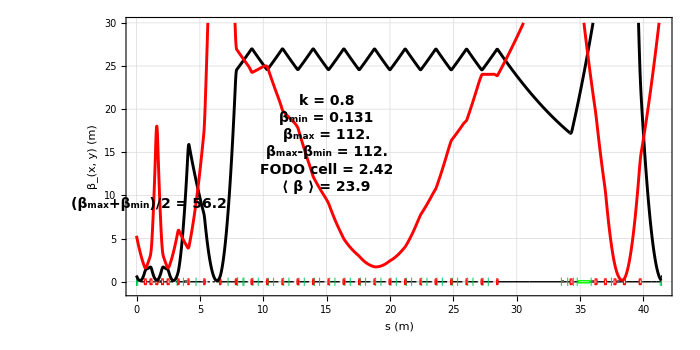
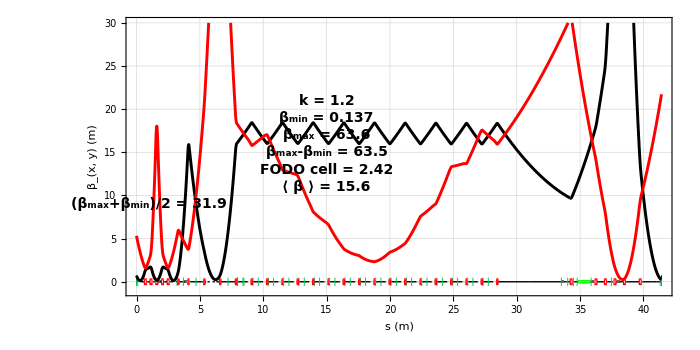
{{0.713897,2.05015,5.32287,3.70185},-Graphics-,{0.713897,2.05015,5.32287,3.70185},-Graphics-}

```mathematica
felmatch
```

Looks like the dipoles are causing something in the y-plane.....

```mathematica
(*Export["clara_fel_match.png",GraphicsGrid[Partition[felmatch⟦2;;-10;;4⟧,2],Frame->All],ImageResolution->100]*)
```

### FODO with delay chicanes

```mathematica
LATTICE=MADFlatten[{CLA£FRS}]⟦1;;-22⟧;
```

```mathematica
test=MADFlatten[{CLA£FRS}]⟦1;;50⟧;
```

```mathematica
test2=MADFlatten[{CLA£FRS}]⟦1;;43⟧;
```

```mathematica
MADInfo[test2]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£FRS£APER | Marker | 0 | --- | --- | --- | CLA£FRS£APER | 0
2 | CLA£FRS£R01£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£B | 0.03
3 | CLA£FRS£R01£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£W | 0.03
4 | CLA£FRS£R01£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£A | 0.06
5 | CLA£FRS£R01£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R01£DIA£BPM£01 | 0.06
6 | CLA£FRS£R01£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£UND£B | 0.07
7 | CLA£FRS£R01£MAG£UND£W£H1 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1 | 0.445
8 | CLA£FRS£R01£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R01£MARK£01 | 0.445
9 | CLA£FRS£R01£MAG£UND£W£H2 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H2 | 0.82
10 | CLA£FRS£R01£MAG£UND£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£UND£A | 0.83
11 | CLA£FRS£R01£MAG£DIP£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£01£B | 0.84
12 | CLA£FRS£R01£MAG£DIP£01£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R01£MAG£DIP£01£D | 0.890008
13 | CLA£FRS£R01£MAG£DIP£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£01£A | 0.900008
14 | CLA£FRS£R01£MAG£DIP£02£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£02£B | 0.910008
15 | CLA£FRS£R01£MAG£DIP£02£D | SectorBend | 0.100017 | 0 | --- | 0.0349066 | CLA£FRS£R01£MAG£DIP£02£D | 1.01002
16 | CLA£FRS£R01£MAG£DIP£02£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£02£A | 1.02002
17 | CLA£FRS£R01£MAG£DIP£03£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£03£B | 1.03002
18 | CLA£FRS£R01£MAG£DIP£03£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R01£MAG£DIP£03£D | 1.08003
19 | CLA£FRS£R01£MAG£DIP£03£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£03£A | 1.09003
20 | CLA£FRS£R01£MAG£QUAD£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£QUAD£01£B | 1.10003
21 | CLA£FRS£R01£MAG£QUAD£01£K | Quadrupole | 0.1 | 1.2 | --- | --- | CLA£FRS£R01£MAG£QUAD£01£K | 1.20003
22 | CLA£FRS£R01£MAG£QUAD£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£QUAD£01£A | 1.21003
23 | CLA£FRS£R02£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£B | 1.24003
24 | CLA£FRS£R02£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£W | 1.24003
25 | CLA£FRS£R02£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£A | 1.27003
26 | CLA£FRS£R02£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R02£DIA£BPM£01 | 1.27003
27 | CLA£FRS£R02£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£UND£B | 1.28003
28 | CLA£FRS£R02£MAG£UND£W£H1 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R02£MAG£UND£W£H1 | 1.65503
29 | CLA£FRS£R02£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R02£MARK£01 | 1.65503
30 | CLA£FRS£R02£MAG£UND£W£H2 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R02£MAG£UND£W£H2 | 2.03003
31 | CLA£FRS£R02£MAG£UND£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£UND£A | 2.04003
32 | CLA£FRS£R02£MAG£DIP£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£01£B | 2.05003
33 | CLA£FRS£R02£MAG£DIP£01£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R02£MAG£DIP£01£D | 2.10004
34 | CLA£FRS£R02£MAG£DIP£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£01£A | 2.11004
35 | CLA£FRS£R02£MAG£DIP£02£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£02£B | 2.12004
36 | CLA£FRS£R02£MAG£DIP£02£D | SectorBend | 0.100017 | 0 | --- | 0.0349066 | CLA£FRS£R02£MAG£DIP£02£D | 2.22006
37 | CLA£FRS£R02£MAG£DIP£02£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£02£A | 2.23006
38 | CLA£FRS£R02£MAG£DIP£03£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£03£B | 2.24006
39 | CLA£FRS£R02£MAG£DIP£03£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R02£MAG£DIP£03£D | 2.29007
40 | CLA£FRS£R02£MAG£DIP£03£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£03£A | 2.30007
41 | CLA£FRS£R02£MAG£QUAD£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£QUAD£01£B | 2.31007
42 | CLA£FRS£R02£MAG£QUAD£01£K | Quadrupole | 0.1 | -1.2 | --- | --- | CLA£FRS£R02£MAG£QUAD£01£K | 2.41007
43 | CLA£FRS£R02£MAG£QUAD£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£QUAD£01£A | 2.42007

Total Length = 2.42007 m

```mathematica
Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[2,1,1]]-Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[1,1,1]]
```

1.21002

So structure of CLARA FODO is

Remember to get the edge angles right - they are rectangular

```mathematica
marker[M11D0CMS]
marker[M11D0CME]
sbend[M11D0CB1,0.0500083,0,-0.0174533,"M11D0CB1",E2->-0.0174533]
drift[M11D0CBD,0.02,"M11D0CBD"]
sbend[M11D0CB2,0.100017,0,0.0349066,"M11D0CB2",E1->0.0174533,E2->0.0174533]
sbend[M11D0CB3,0.0500083,0,-0.0174533,"M11D0CB3",E1->-0.0174533]
drift[M11D0CD1H2,(1.21002-0.1)/2,"M11D0CD1H2"]
drift[M11D0CD2,0.85,"M11D0CD2"]
drift[M11D0CD1H1,(1.21002-0.1)/2-0.26002,"M11D0CD1H1"]
quad[M11D0CQ1,0.10,3,"M11D0CQ1"]
quad[M11D0CQ2,0.10,-3,"M11D0CQ2"]
line[M11D0RC,{M11D0CMS,M11D0CD1H1,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ1,M11D0CD2,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ2,M11D0CD1H2,M11D0CME}]
```

```mathematica
M11D0CB2
```

{{M11D0CB2,SectorBend,0.100017,0,---,0.0349066,M11D0CB2}}

```mathematica
M11D0CB2Extra
```

{M11D0CB2,Extra,0,0,0.0174533,0.0174533,0,0,0,0,0,0,0}

```mathematica
MADInfo[M11D0RC]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | M11D0CMS | Marker | 0 | --- | --- | --- |  | 0
2 | M11D0CD1H1 | Drift | 0.29499 | --- | --- | --- | M11D0CD1H1 | 0.29499
3 | M11D0CB1 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB1 | 0.344998
4 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 0.364998
5 | M11D0CB2 | SectorBend | 0.100017 | 0 | --- | 0.0349066 | M11D0CB2 | 0.465015
6 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 0.485015
7 | M11D0CB3 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB3 | 0.535024
8 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 0.555024
9 | M11D0CQ1 | Quadrupole | 0.1 | 3 | --- | --- | M11D0CQ1 | 0.655024
10 | M11D0CD2 | Drift | 0.85 | --- | --- | --- | M11D0CD2 | 1.50502
11 | M11D0CB1 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB1 | 1.55503
12 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 1.57503
13 | M11D0CB2 | SectorBend | 0.100017 | 0 | --- | 0.0349066 | M11D0CB2 | 1.67505
14 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 1.69505
15 | M11D0CB3 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB3 | 1.74506
16 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 1.76506
17 | M11D0CQ2 | Quadrupole | 0.1 | -3 | --- | --- | M11D0CQ2 | 1.86506
18 | M11D0CD1H2 | Drift | 0.55501 | --- | --- | --- | M11D0CD1H2 | 2.42007
19 | M11D0CME | Marker | 0 | --- | --- | --- |  | 2.42007

Total Length = 2.42007 m

```mathematica
MADWrite["M11D0R",M11D0RC];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g M11D0R.mff",Word]];
MADStringWrite["M11D0R","eopt,add;\n"];
MADStringWrite["M11D0R","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.135]<>";\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.1\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.2\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.3\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.4\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.5\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.6\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.7\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.8\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.9\n"];
MADStringWrite["M11D0R","select,twiss,full;\ntwiss,tape=twiss.txt;\n"];
MADStringWrite["M11D0R","select,optics,full;\noptics,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat M11D0R.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < M11D0R.mff > M11D0R_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < M11D0R.mff > M11D0R.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->True];
Select[ReadList["M11D0R.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&];
```

{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}

Variables (re-)assigned: {GAMTR,ALFA,XIY,XIX,QY,QX,CIRCUM,DELTA,TYPE,COMMENT,ORIGIN,DATE,TIME}

Variables (re-)assigned: {NAME,S,BETX,BETY,DX,ALFX,ALFY,MUX,MUY,DPX,DY,DPY}

```mathematica
MatchTwiss=First[#]&/@{BETX,ALFX,BETY,ALFY}
```

{6.86201,-1.0451,4.90304,0.741309}

```mathematica
ToString[NumberForm[MADLength[M11D0RC],3]]
```

2.42

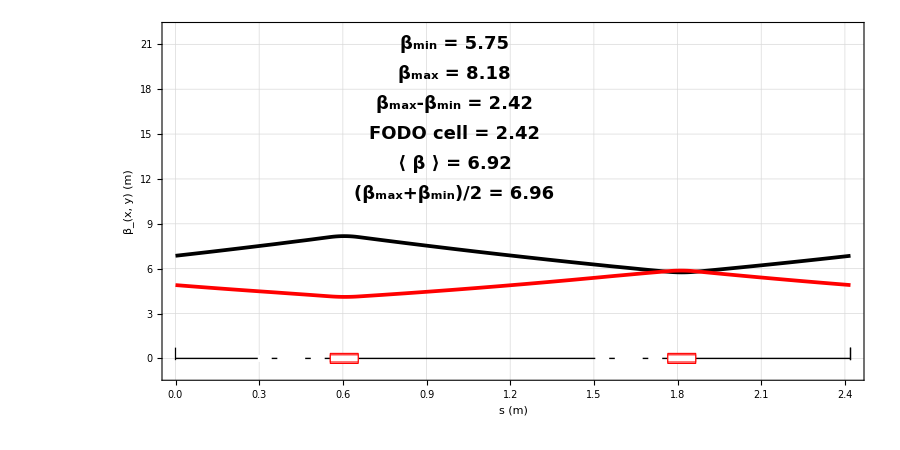

done

```mathematica
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{0.3,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["β_min = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,21}],
Text[Style["β_max = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,19}],
Text[Style["β_max-β_min = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,17}],
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RC],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,15}],
Text[Style[ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,13}],
Text[Style["(β_max+β_min)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,11}]},Prolog->MADDraw[Select[MADFlatten[M11D0RC], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,22}},ImageSize->900,AspectRatio->0.5];
(*{Show[#],Export["output/run_B_pw01_twiss_mma.png",#,ImageResolution->400],Export["output/run_B_pw01_twiss_mma.eps",#,ImageSize->900,ImageResolution->200]}&@*)ShowLegend[plt,lgd]
Print["done"]
```

scan over k -values

```mathematica
vals=Table[i,{i,0.8,15.2,0.4}];
```

```mathematica
vals
```

{0.8,1.2,1.6,2.,2.4,2.8,3.2,3.6,4.,4.4,4.8,5.2,5.6,6.,6.4,6.8,7.2,7.6,8.,8.4,8.8,9.2,9.6,10.,10.4,10.8,11.2,11.6,12.,12.4,12.8,13.2,13.6,14.,14.4,14.8,15.2}

```mathematica
vals2=(1/((M11D0CQ1⟦1,3⟧/2)#) 1/(MADLength[M11D0RC]/2))&[vals]
```

{20.6606,13.7737,10.3303,8.26423,6.88686,5.90302,5.16515,4.59124,4.13212,3.75647,3.44343,3.17855,2.95151,2.75474,2.58257,2.43066,2.29562,2.1748,2.06606,1.96767,1.87823,1.79657,1.72172,1.65285,1.58928,1.53041,1.47576,1.42487,1.37737,1.33294,1.29129,1.25216,1.21533,1.1806,1.14781,1.11679,1.0874}

```mathematica
betavs=Reap[(
marker[M11D0CMS]
marker[M11D0CME]
sbend[M11D0CB1,0.0500083,0,-0.0174533,"M11D0CB1",E2->-0.0174533]
drift[M11D0CBD,0.02,"M11D0CBD"]
sbend[M11D0CB2,0.100017,0,0.0349066,"M11D0CB2",E1->0.0174533,E2->0.0174533]
sbend[M11D0CB3,0.0500083,0,-0.0174533,"M11D0CB3",E1->-0.0174533]
drift[M11D0CD1H2,(1.21002-0.1)/2,"M11D0CD1H2"]
drift[M11D0CD2,0.85,"M11D0CD2"]
drift[M11D0CD1H1,(1.21002-0.1)/2-0.26002,"M11D0CD1H1"]
quad[M11D0CQ1,0.10,#,"M11D0CQ1"]
quad[M11D0CQ2,0.10,-#,"M11D0CQ2"]
line[M11D0RC,Table[{M11D0CMS,M11D0CD1H1,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ1,M11D0CD2,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ2,M11D0CD1H2,M11D0CME},1]]
MADWrite["M11D0R",M11D0RC];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g M11D0R.mff",Word]];
MADStringWrite["M11D0R","eopt,add;\n"];
	MADStringWrite["M11D0R","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.05\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.10\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.15\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.20\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.25\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.30\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.35\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.40\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.45\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.50\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.55\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.60\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.65\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.70\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.75\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.80\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.85\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.90\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.95\n"];
MADStringWrite["M11D0R","select,twiss,full;\ntwiss,tape=twiss.txt;\n"];
MADStringWrite["M11D0R","select,optics,full;\noptics,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat M11D0R.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < M11D0R.mff > M11D0R_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < M11D0R.mff > M11D0R.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
Select[ReadList["M11D0R.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&];
Sow[{Mean[BETX],Mean[BETY]}];
Sow[First[#]&/@{BETX,ALFX,BETY,ALFY}];
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["k = "<>ToString[#],FontFamily->"Helvetica",Bold,FontSize->14],{1.3,21}],
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RC],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.3,19}],
Text[Style["β_xmin = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,17}],
Text[Style["β_xmax = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,15}],
Text[Style["β_xmax-β_xmin = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,13}],
Text[Style[ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,11}],
Text[Style["(β_xmax+β_xmin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,9}],
Text[Style["β_ymin = "<>ToString[NumberForm[Min[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,17}],
Text[Style["β_ymax = "<>ToString[NumberForm[Max[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,15}],
Text[Style["β_ymax-β_ymin = "<>ToString[NumberForm[(Max[BETY]-Min[BETY]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,13}],
Text[Style[ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Mean[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,11}],
Text[Style["(β_ymax+β_ymin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETY])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,9}]},Prolog->MADDraw[Select[MADFlatten[M11D0RC], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,30}},ImageSize->700,AspectRatio->0.5];
Sow[Show[plt]];

)&/@vals]⟦2,1⟧;
```

```mathematica
GraphicsGrid[Partition[betavs⟦3;;-1;;3⟧,2],Frame->All];
```

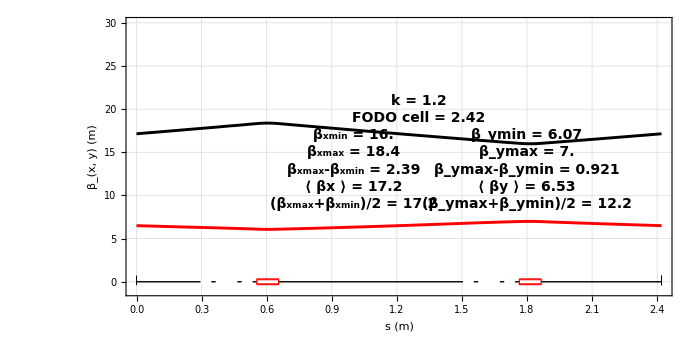

```mathematica
betavs⟦6⟧
```

```mathematica
(*Export["clara_frs_fodo_k12.png",betavs⟦6⟧,ImageResolution->200]*)
```

```mathematica
Take[betavs,{1,-1,3}]
```

{{25.7317,6.80882},{17.1678,6.53475},{12.8899,6.20253},{10.3266,5.84333},{8.62052,5.48115},{7.40446,5.13181},{6.49473,4.80431},{5.78931,4.50278},{5.22701,4.22825},{4.76891,3.97996},{4.38908,3.75623},{4.06957,3.55498},{3.79758,3.37407},{3.56377,3.21143},{3.36112,3.06515},{3.1843,2.93355},{3.02918,2.81513},{2.89256,2.70861},{2.77187,2.61287},{2.66509,2.52698},{2.5706,2.45016},{2.48713,2.38177},{2.41366,2.32133},{2.34942,2.26847},{2.29384,2.22296},{2.24656,2.1847},{2.20738,2.15377},{2.17634,2.13041},{2.15368,2.11511},{2.13994,2.10864},{2.13604,2.11218},{2.14336,2.1275},{2.16407,2.15728},{2.20147,2.20561},{2.26078,2.27906},{2.3506,2.38881},{2.48619,2.55549}}

```mathematica
Min[Take[betavs,{1,-1,3}]]
```

2.10864

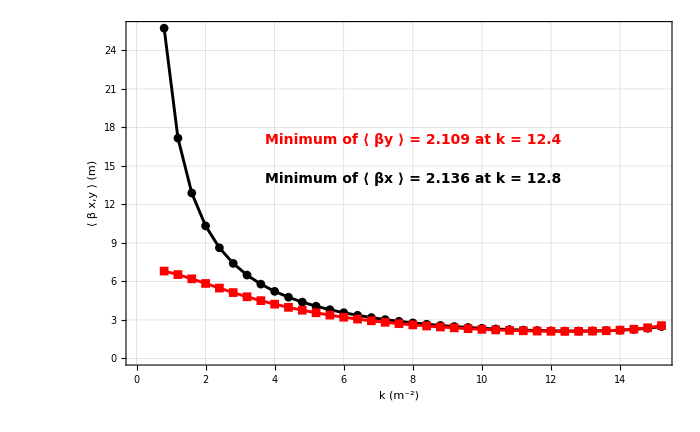

```mathematica
plt1=ListLinePlot[{Transpose[{vals,Take[betavs,{1,-3,3}]⟦All,1⟧}],Transpose[{vals,Take[betavs,{1,-3,3}]⟦All,2⟧}]},Epilog->{Text[Style["Minimum of "<>ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-3,3}]⟦All,1⟧],4]]<>" at k = "<>ToString[vals[[Position[#,Min[#]]&[Take[betavs,{1,-3,3}]⟦All,1⟧]⟦1,1⟧]]],FontFamily->"Helvetica",Bold,FontSize->14],{8,14}],Text[Style["Minimum of "<>ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-3,3}]⟦All,2⟧],4]]<>" at k = "<>ToString[vals[[Position[#,Min[#]]&[Take[betavs,{1,-3,3}]⟦All,2⟧]⟦1,1⟧]]],FontFamily->"Helvetica",Bold,Red,FontSize->14],{8,17}]},PlotMarkers->Automatic,Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{ToString[AngleBracket["β x,y"]]<>" (m)",""},{"k (m^-2)",""}},GridLines->Automatic,PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]}},LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->700,PlotRange->{{0,QuantityMagnitude[Last[vals]]},All}]
```

```mathematica
(*Export["clara_frs_fodo_kscan2.png",plt1,ImageResolution->200]*)
```

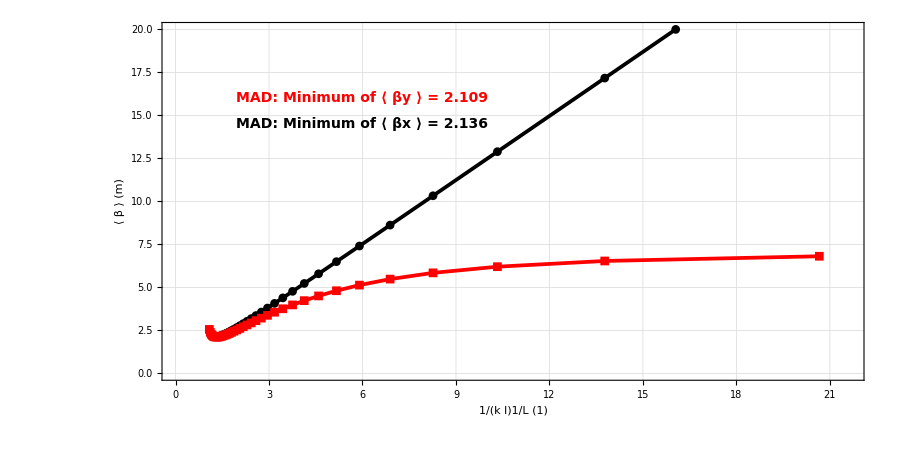

```mathematica
plt2=ListLinePlot[{Transpose[{vals2,Take[betavs,{1,-1,3}]⟦All,1⟧}],Transpose[{vals2,Take[betavs,{1,-1,3}]⟦All,2⟧}]},Epilog->{Text[Style["MAD: Minimum of "<>ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-1,3}]⟦All,1⟧],4]],FontFamily->"Helvetica",Bold,Black,FontSize->14],{6,14.5}],Text[Style["MAD: Minimum of "<>ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-1,3}]⟦All,2⟧],4]],FontFamily->"Helvetica",Bold,Red,FontSize->14],{6,16}]},PlotMarkers->Automatic,Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{ToString[AngleBracket["β"]]<>" (m)",""},{"1/(k l)1/L (1)",""}},GridLines->Automatic,PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]}},LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImagePadding->100,ImageSize->900,AspectRatio->0.5,PlotRange->{{0,QuantityMagnitude[First[vals2]]+1},{0,20}}]
```

```mathematica
plt3=Plot[{(MADLength[M11D0RC]/2 )x^2(x^2-1)^(-1/2),(MADLength[M11D0RC]/2 )x},{x,0,QuantityMagnitude[First[vals2]]+1},Frame->{False,False,False,True},Epilog->{Style[Text["Wiedemann: Minimum of "<>ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[FindMinimum[(MADLength[M11D0RC]/2 )x^2(x^2-1)^(-1/2),{x,1.1}]⟦1⟧,{3,3}]],{5.4,13}],Darker[Green],Bold,FontSize->14],Style[Text["Pfluger",{6,12}],Blue,Bold,FontSize->14]},PlotStyle->{Darker[Green],Blue},FrameTicks->{{None,Range[0,25,5]},{Automatic,None}},LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},PlotRange->{{0,QuantityMagnitude[First[vals2]]+1},{0,20}},ImagePadding->100,AspectRatio->0.5,ImageSize->900];
```

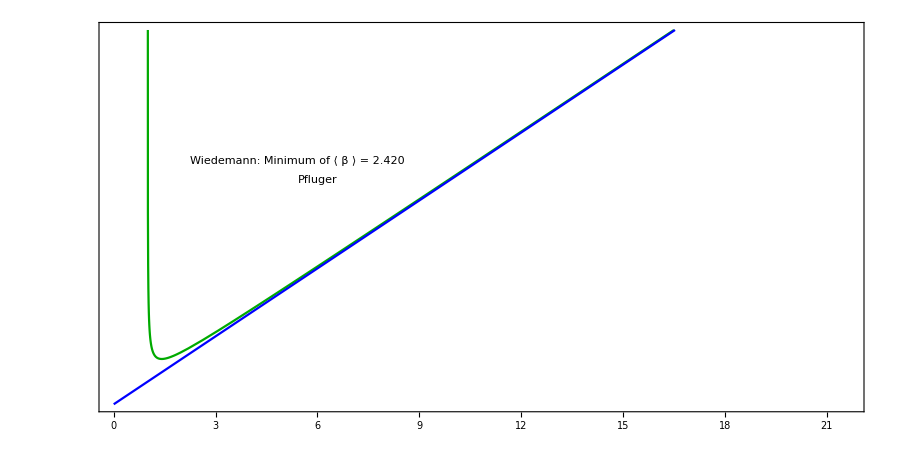
-Graphics--Graphics-

```mathematica
plt4=Overlay[{plt2,plt3}]
```

```mathematica
(*Export["clara_frs_fodo_rescale2.png",plt4,ImageResolution->200]*)
```

```mathematica
StartTwiss=matchedtwiss⟦All,2⟧
```

{0.713897466451,2.050146867508,5.322874875709,3.701847589651}

```mathematica
FodoTwiss=Transpose[{vals,betavs⟦2;;-1;;3⟧}]
```

{{0.8,{25.7192,-1.02988,6.77861,0.250167}},{1.2,{17.1468,-1.0313,6.50065,0.372916}},{1.6,{12.8609,-1.03331,6.16346,0.480304}},{2.,{10.2895,-1.03592,5.79844,0.57187}},{2.4,{8.57555,-1.03912,5.42979,0.648819}},{2.8,{7.35152,-1.04295,5.0735,0.713167}},{3.2,{6.43376,-1.04742,4.73866,0.767122}},{3.6,{5.72022,-1.05256,4.42947,0.812755}},{4.,{5.1497,-1.05839,4.14701,0.851854}},{4.4,{4.68324,-1.06495,3.89054,0.885898}},{4.8,{4.29488,-1.07228,3.65839,0.91609}},{5.2,{3.96667,-1.08042,3.44848,0.943394}},{5.6,{3.68579,-1.08942,3.25865,0.968588}},{6.,{3.44284,-1.09935,3.08682,0.992303}},{6.4,{3.2308,-1.11026,2.93106,1.01506}},{6.8,{3.04429,-1.12225,2.78965,1.0373}},{7.2,{2.87917,-1.1354,2.66107,1.0594}},{7.6,{2.73216,-1.14981,2.54397,1.0817}},{8.,{2.60067,-1.16562,2.43722,1.10452}},{8.4,{2.48263,-1.18296,2.33982,1.12815}},{8.8,{2.37635,-1.202,2.25092,1.1529}},{9.2,{2.28048,-1.22296,2.16982,1.17909}},{9.6,{2.19393,-1.24605,2.09592,1.20705}},{10.,{2.11582,-1.27159,2.02876,1.23717}},{10.4,{2.04546,-1.29991,1.96797,1.26989}},{10.8,{1.98234,-1.33144,1.9133,1.30572}},{11.2,{1.92609,-1.36672,1.86462,1.3453}},{11.6,{1.87652,-1.40642,1.82193,1.3894}},{12.,{1.83358,-1.45139,1.78539,1.43901}},{12.4,{1.79745,-1.50275,1.75534,1.49541}},{12.8,{1.76854,-1.56197,1.7324,1.56032}},{13.2,{1.7476,-1.63106,1.71759,1.63609}},{13.6,{1.73584,-1.71284,1.71246,1.72606}},{14.,{1.73526,-1.81142,1.71951,1.83518}},{14.4,{1.74902,-1.93302,1.7428,1.97115}},{14.8,{1.78251,-2.0877,1.78933,2.14682}},{15.2,{1.84535,-2.29295,1.87216,2.38561}}}

```mathematica
LATTICE=$LATTICE=MADFlatten[{CLA£SLD,CLA£FMS,CLA£FRS,CLA£FAB,CLA£PFD}];
```

needed to change the distances of the inserted elements as forgot to take off quad length from the half cell length

```mathematica
felmatch=Reap[Map[Function[p2,(
Map[Function[p1,quad[p1,0.10,p2⟦1⟧,ToString[p1]]],matchedqs⟦11;;27;;2,1⟧];
Map[Function[p1,quad[p1,0.10,-p2⟦1⟧,ToString[p1]]],matchedqs⟦12;;27;;2,1⟧];
Map[Function[p1,quad[p1,0.10,-10,ToString[p1]]],{matchedqs⟦6,1⟧}];
Map[Function[p1,quad[p1,0.10,-10,ToString[p1]]],{matchedqs⟦7,1⟧}];
drift[CLA£FRS£R01£MAG£UND£W£H21,0.08001,"CLA£FRS£R01£MAG£UND£W£H21"];
marker[CLA£FRS£R01£MAG£UND£W£H2M];
drift[CLA£FRS£R01£MAG£UND£W£H22,0.29499,"CLA£FRS£R01£MAG£UND£W£H21"];
LATTICE=$LATTICE=MADFlatten[{CLA£SLD,CLA£FMS,CLA£FRS,CLA£FAB,CLA£PFD}];
LATTICE2=MADFlatten[ReplacePart[LATTICE,Position[LATTICE,"CLA£FRS£R01£MAG£UND£W£H2"]⟦1,1⟧->MADFlatten[{CLA£FRS£R01£MAG£UND£W£H21,CLA£FRS£R01£MAG£UND£W£H2M,CLA£FRS£R01£MAG£UND£W£H22}]]];
MADWrite["felmatch",LATTICE2];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g felmatch.mff",Word]];
ReadList["!sed -i s/CLA//g felmatch.mff",Word];
MADStringWrite["felmatch","eopt,add;\nINITIAL:BETA0,&\n
BETX="<>ToString[StartTwiss⟦1⟧]<>",ALFX="<>ToString[StartTwiss⟦2⟧]<>",&\n
BETY="<>ToString[StartTwiss⟦3⟧]<>",ALFY="<>ToString[StartTwiss⟦4⟧]<>",&\n
dx=0,dpx=0,energy=0.250;\n"];
MADStringWrite["felmatch","eopt,add;\nFODO:BETA0,&\n
BETX="<>ToString[p2⟦2,1⟧]<>",ALFX="<>ToString[p2⟦2,2⟧]<>",&\n
BETY="<>ToString[p2⟦2,3⟧]<>",ALFY="<>ToString[p2⟦2,4⟧]<>",&\n
dx=0,dpx=0;\n"];Print[p2];
MADStringWrite["felmatch","eopt,add;\n"];
MADStringWrite["felmatch","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["felmatch","match,beta0=initial;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦6,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦7,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦8,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦9,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦10,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","constraint,"<>StringReplace["CLA£FRS£R01£MAG£UND£W£H2M",{"£"->"","CLA"->""}]<>",beta0=fodo;\n"];
MADStringWrite["felmatch","constraint,#s/"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦11,1⟧]<>",betx < 50, bety < 50;\n"];
(*MADStringWrite["felmatch","constraint,"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦6,1⟧]<>"/"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦11,1⟧]<>",betx > 0.5, bety > 0.5;\n"];*)
MADStringWrite["felmatch","simplex,calls=5000000,tolerance=1.0E-10;\n"];
MADStringWrite["felmatch","endmatch;\n"];
Map[Function[p5,MADStringWrite["felmatch","value,"<>StringReplace[p5,{"£"->"","CLA"->""}]&[p5]<>"[K1];\n"]],matchedqs⟦All,1⟧];
MADStringWrite["felmatch","split,name=b1,fraction=0.05\n"];
MADStringWrite["felmatch","split,name=b2,fraction=0.10\n"];
MADStringWrite["felmatch","split,name=b3,fraction=0.15\n"];
MADStringWrite["felmatch","split,name=b4,fraction=0.20\n"];
MADStringWrite["felmatch","split,name=b5,fraction=0.25\n"];
MADStringWrite["felmatch","split,name=b6,fraction=0.30\n"];
MADStringWrite["felmatch","split,name=b7,fraction=0.35\n"];
MADStringWrite["felmatch","split,name=b8,fraction=0.40\n"];
MADStringWrite["felmatch","split,name=b9,fraction=0.45\n"];
MADStringWrite["felmatch","split,name=b10,fraction=0.50\n"];
MADStringWrite["felmatch","split,name=b11,fraction=0.55\n"];
MADStringWrite["felmatch","split,name=b12,fraction=0.60\n"];
MADStringWrite["felmatch","split,name=b13,fraction=0.65\n"];
MADStringWrite["felmatch","split,name=b14,fraction=0.70\n"];
MADStringWrite["felmatch","split,name=b15,fraction=0.75\n"];
MADStringWrite["felmatch","split,name=b16,fraction=0.80\n"];
MADStringWrite["felmatch","split,name=b17,fraction=0.85\n"];
MADStringWrite["felmatch","split,name=b18,fraction=0.90\n"];
MADStringWrite["felmatch","split,name=b19,fraction=0.95\n"];
MADStringWrite["felmatch","select,twiss,full;\ntwiss,beta0=initial,tape=twiss.txt;\n"];
MADStringWrite["felmatch","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat felmatch.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < felmatch.mff > felmatch_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < felmatch.mff > felmatch.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
Print[Select[ReadList["felmatch.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&]];
Sow[Map[Function[p3,First[p3]],{BETX,ALFX,BETY,ALFY}]];
Sow[Select[Transpose[{NAME,BETX,ALFX,BETY,ALFY}],StringMatchQ[#⟦1⟧,"*FMSMAGMU1B*"]&]⟦1⟧];
Sow[Map[Function[p5,StringCases[p5,"Value of expression \""~~quad:(WordCharacter|DigitCharacter)..~~"[K1]\" is:"~~WhitespaceCharacter..~~value:(DigitCharacter|"-"|".")..:>{StringCases[p5,v:{"FMS"}~~w:"MAG"~~x:"QUAD"~~y:DigitCharacter..~~z:"K":>  "CLA£"~~v~~"£"~~w~~"£"~~x~~"£"~~y~~"£"~~z]&[quad]⟦1⟧,value}]⟦1⟧],Select[FindList["felmatch.echo.txt","Value of expression "],StringMatchQ[#,"*FMS*QUAD*"]&]]];
(*Print[#⟦1⟧<>"⟦1,4⟧="<>ToString[#⟦2⟧]]&/@matchfms;*)
(*matchedqstabRL={StringReplace[#⟦1⟧,"£"->"-"],#⟦4⟧}&/@Select[MADFlatten[CLA£ELEGANT],#[[2]]=="Quadrupole"&];*)
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["k = "<>ToString[p2⟦1⟧],FontFamily->"Helvetica",Bold,FontSize->14],{20,21}](*,
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RC],3]],FontFamily->"Helvetica",Bold,FontSize->14],{20,19}],
Text[Style["β_xmin = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,17}],
Text[Style["β_xmax = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,15}],
Text[Style["β_xmax-β_xmin = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,13}],
Text[Style[ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,11}],
Text[Style["(β_xmax+β_xmin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,9}],
Text[Style["β_ymin = "<>ToString[NumberForm[Min[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,17}],
Text[Style["β_ymax = "<>ToString[NumberForm[Max[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,15}],
Text[Style["β_ymax-β_ymin = "<>ToString[NumberForm[(Max[BETY]-Min[BETY]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,13}],
Text[Style[ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Mean[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,11}],
Text[Style["(β_ymax+β_ymin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETY])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,9}]*)},Prolog->MADDraw[LATTICE2,Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,30}},ImageSize->700,AspectRatio->0.5];
Sow[Show[plt]];
)],FodoTwiss⟦1;;-1⟧]]⟦2,1⟧;
```

{0.8,{25.7192,-1.02988,6.77861,0.250167}}

{ MTCOND.  Last value of the penalty function:  1.217761E-09}

{1.2,{17.1468,-1.0313,6.50065,0.372916}}

{ MTCOND.  Last value of the penalty function:  8.548752E-10}

{1.6,{12.8609,-1.03331,6.16346,0.480304}}

{ MTCOND.  Last value of the penalty function:  4.219159E-10}

{2.,{10.2895,-1.03592,5.79844,0.57187}}

{ MTCOND.  Last value of the penalty function:  5.215890E-10}

{2.4,{8.57555,-1.03912,5.42979,0.648819}}

{ MTCOND.  Last value of the penalty function:  4.560794E-10}

{2.8,{7.35152,-1.04295,5.0735,0.713167}}

{ MTCOND.  Last value of the penalty function:  9.077942E-10}

{3.2,{6.43376,-1.04742,4.73866,0.767122}}

{ MTCOND.  Last value of the penalty function:  7.524343E-10}

{3.6,{5.72022,-1.05256,4.42947,0.812755}}

{ MTCOND.  Last value of the penalty function:  5.876564E-10}

{4.,{5.1497,-1.05839,4.14701,0.851854}}

{ MTCOND.  Last value of the penalty function:  2.298431E-09}

{4.4,{4.68324,-1.06495,3.89054,0.885898}}

{ MTCOND.  Last value of the penalty function:  5.486211E-10}

{4.8,{4.29488,-1.07228,3.65839,0.91609}}

{ MTCOND.  Last value of the penalty function:  3.235098E-09}

{5.2,{3.96667,-1.08042,3.44848,0.943394}}

{ MTCOND.  Last value of the penalty function:  5.639518E-09}

{5.6,{3.68579,-1.08942,3.25865,0.968588}}

{ MTCOND.  Last value of the penalty function:  5.317539E-10}

{6.,{3.44284,-1.09935,3.08682,0.992303}}

{ MTCOND.  Last value of the penalty function:  3.290766E-10}

{6.4,{3.2308,-1.11026,2.93106,1.01506}}

{ MTCOND.  Last value of the penalty function:  3.210118E-10}

{6.8,{3.04429,-1.12225,2.78965,1.0373}}

{ MTCOND.  Last value of the penalty function:  1.835217E-09}

{7.2,{2.87917,-1.1354,2.66107,1.0594}}

{ MTCOND.  Last value of the penalty function:  2.396600E-10}

{7.6,{2.73216,-1.14981,2.54397,1.0817}}

{ MTCOND.  Last value of the penalty function:  2.297536E-10}

{8.,{2.60067,-1.16562,2.43722,1.10452}}

{ MTCOND.  Last value of the penalty function:  6.039277E-09}

{8.4,{2.48263,-1.18296,2.33982,1.12815}}

{ MTCOND.  Last value of the penalty function:  2.619020E-10}

{8.8,{2.37635,-1.202,2.25092,1.1529}}

{ MTCOND.  Last value of the penalty function:  3.489621E-10}

{9.2,{2.28048,-1.22296,2.16982,1.17909}}

{ MTCOND.  Last value of the penalty function:  3.257160E-10}

{9.6,{2.19393,-1.24605,2.09592,1.20705}}

{ MTCOND.  Last value of the penalty function:  1.486031E-09}

{10.,{2.11582,-1.27159,2.02876,1.23717}}

{ MTCOND.  Last value of the penalty function:  5.172472E-10}

{10.4,{2.04546,-1.29991,1.96797,1.26989}}

{ MTCOND.  Last value of the penalty function:  4.619515E-09}

{10.8,{1.98234,-1.33144,1.9133,1.30572}}

{ MTCOND.  Last value of the penalty function:  2.616829E-09}

{11.2,{1.92609,-1.36672,1.86462,1.3453}}

{ MTCOND.  Last value of the penalty function:  8.003518E-09}

{11.6,{1.87652,-1.40642,1.82193,1.3894}}

{ MTCOND.  Last value of the penalty function:  6.856176E-09}

{12.,{1.83358,-1.45139,1.78539,1.43901}}

{ MTCOND.  Last value of the penalty function:  9.347286E-09}

{12.4,{1.79745,-1.50275,1.75534,1.49541}}

{ MTCOND.  Last value of the penalty function:  3.607617E-09}

{12.8,{1.76854,-1.56197,1.7324,1.56032}}

{ MTCOND.  Last value of the penalty function:  7.341625E-09}

{13.2,{1.7476,-1.63106,1.71759,1.63609}}

{ MTCOND.  Last value of the penalty function:  1.339344E-08}

{13.6,{1.73584,-1.71284,1.71246,1.72606}}

{ MTCOND.  Last value of the penalty function:  1.762013E-08}

{14.,{1.73526,-1.81142,1.71951,1.83518}}

{ MTCOND.  Last value of the penalty function:  6.368262E-09}

{14.4,{1.74902,-1.93302,1.7428,1.97115}}

{ MTCOND.  Last value of the penalty function:  1.930533E-08}

{14.8,{1.78251,-2.0877,1.78933,2.14682}}

{ MTCOND.  Last value of the penalty function:  2.365857E-08}

{15.2,{1.84535,-2.29295,1.87216,2.38561}}

{ MTCOND.  Last value of the penalty function:  2.598239E-08}

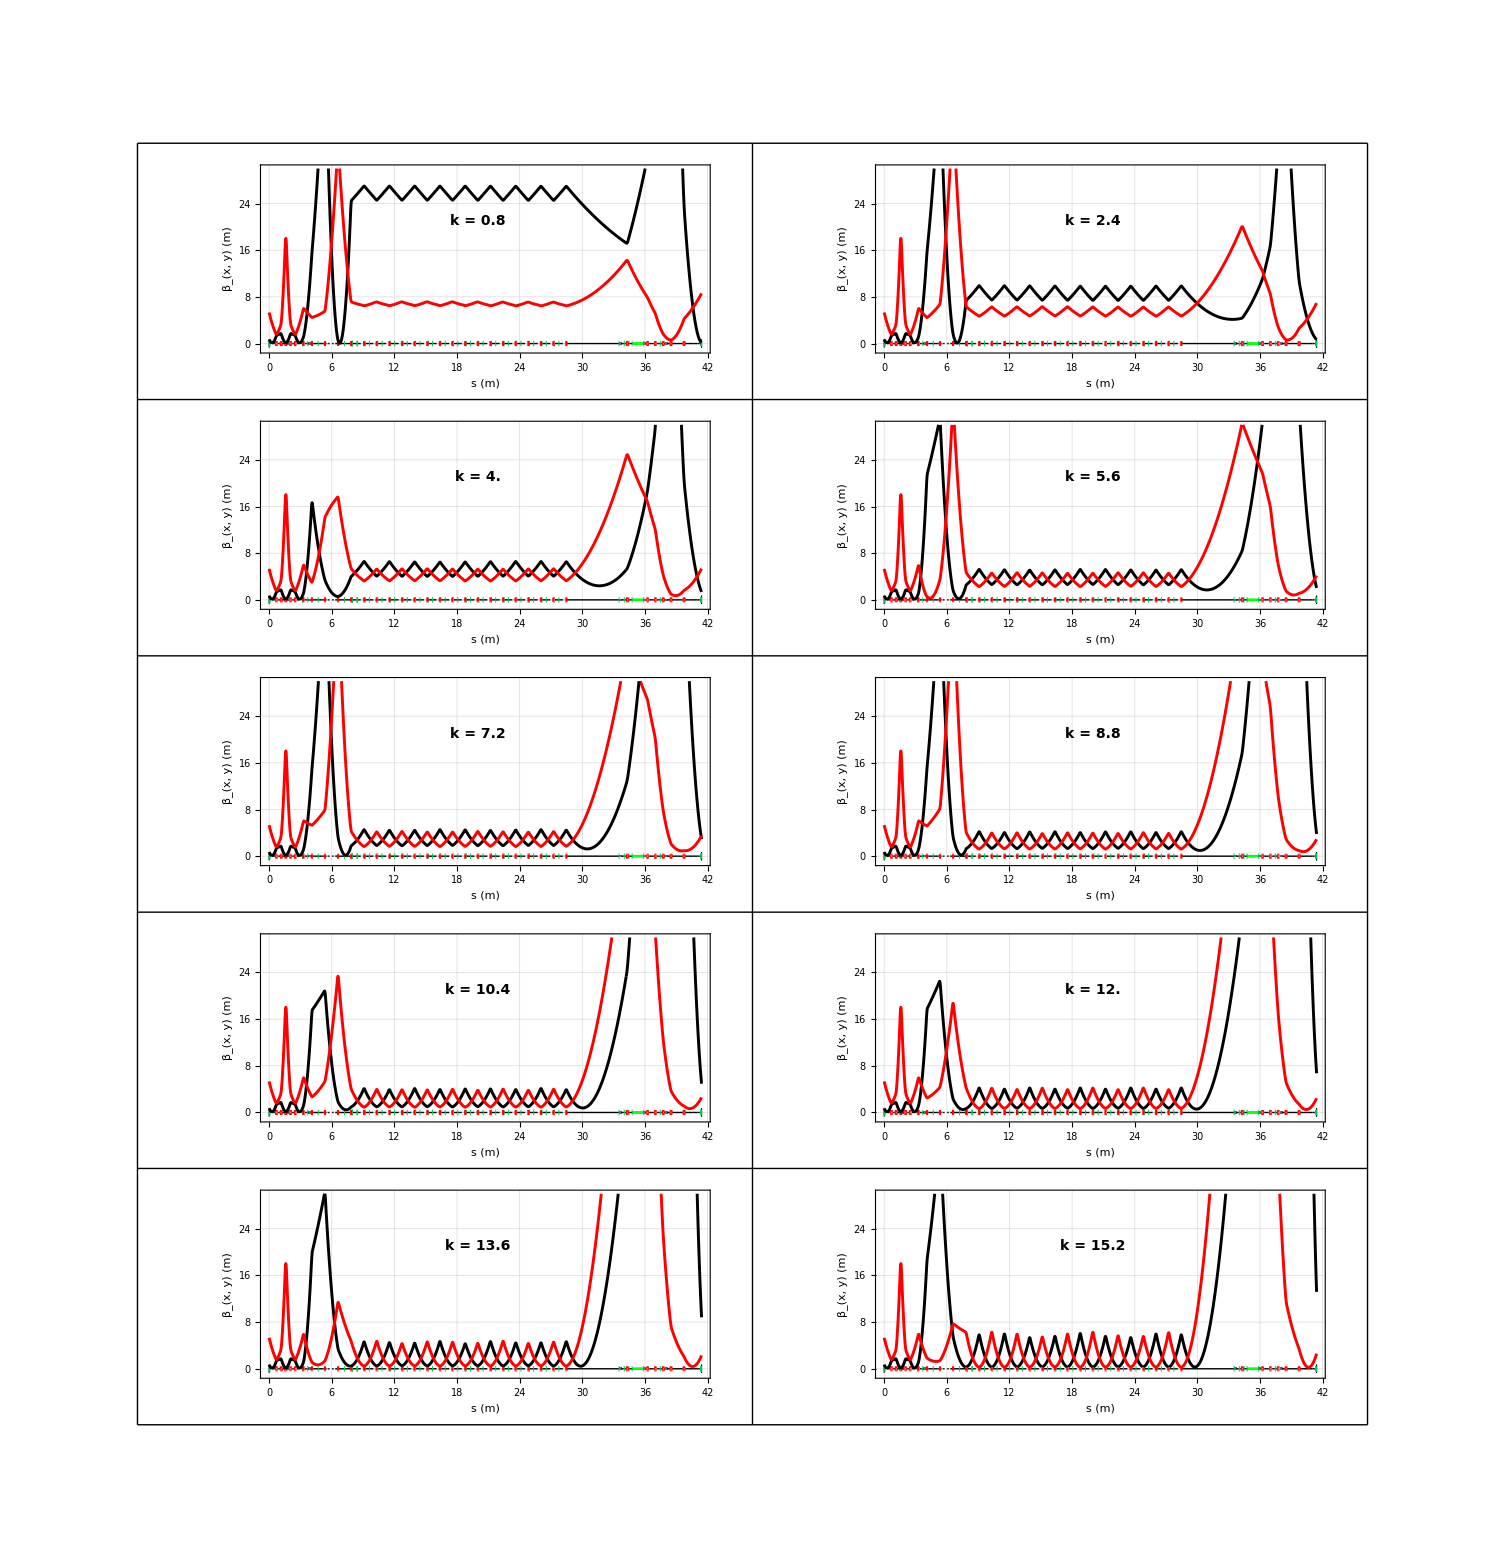

```mathematica
GraphicsGrid[Partition[felmatch⟦4;;-1;;16⟧,2],Frame->All]
```

```mathematica
Export["clara_fel_match2.png",GraphicsGrid[Partition[felmatch⟦4;;-1;;16⟧,2],Frame->All],ImageResolution->150]
```

clara_fel_match2.png

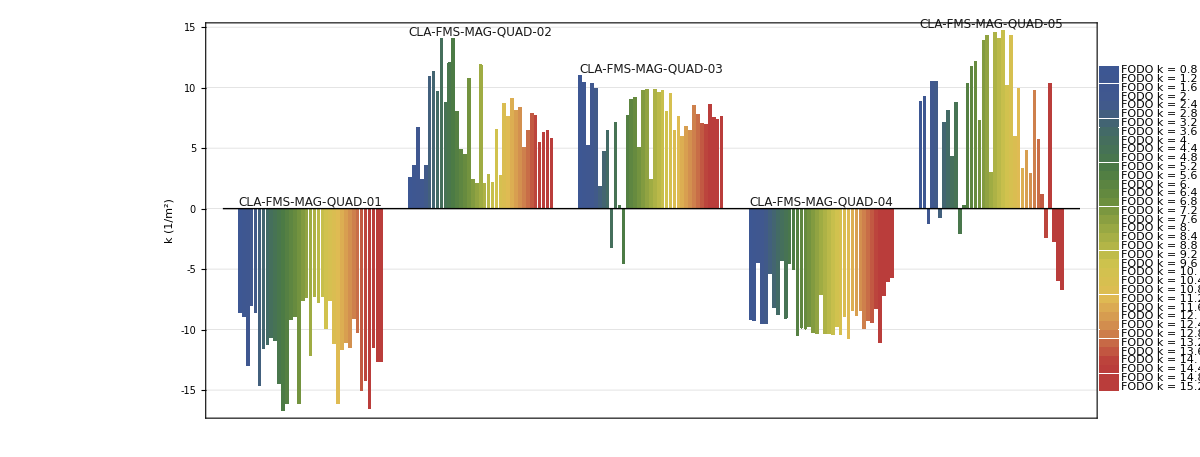

```mathematica
matchplot=ShowLegend[BarChart[Transpose[ToExpression@felmatch⟦3;;-1;;4⟧⟦All,All,2⟧],ChartLabels->{Table["",{Length[felmatch⟦3,All,1⟧]}],Placed[(Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->12]&/@StringDrop[StringReplace[ToString[#]&/@felmatch⟦3,All,1⟧,{"{"->"","}"->"",", "-> " # ","£"->"-","K"->""}],-1]),{{1,1},{1,-0.1}}],Table["",{Length[felmatch⟦3,All,1⟧]}]},ChartStyle->"DarkRainbow",BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.001],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.5,10},FrameLabel->{{"k (1/m^2)",""},{"",""}},FrameTicks->{{LinTicks[-18,16,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-18,16,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,AxesOrigin->{0,0},Axes->True],{Transpose[{ColorData["DarkRainbow",#/Length[vals]]&/@Table[i,{i,0,Length[vals]-1}],"FODO k = "<>ToString[#]&/@vals}],LegendPosition->{0.9,-0.35},LegendSize->{0.2,0.7},LegendShadow->None,LegendTextSpace->3}]
```

```mathematica
Export["clara_fel_match3.png",matchplot,ImageResolution->300]
```

clara_fel_match3.png

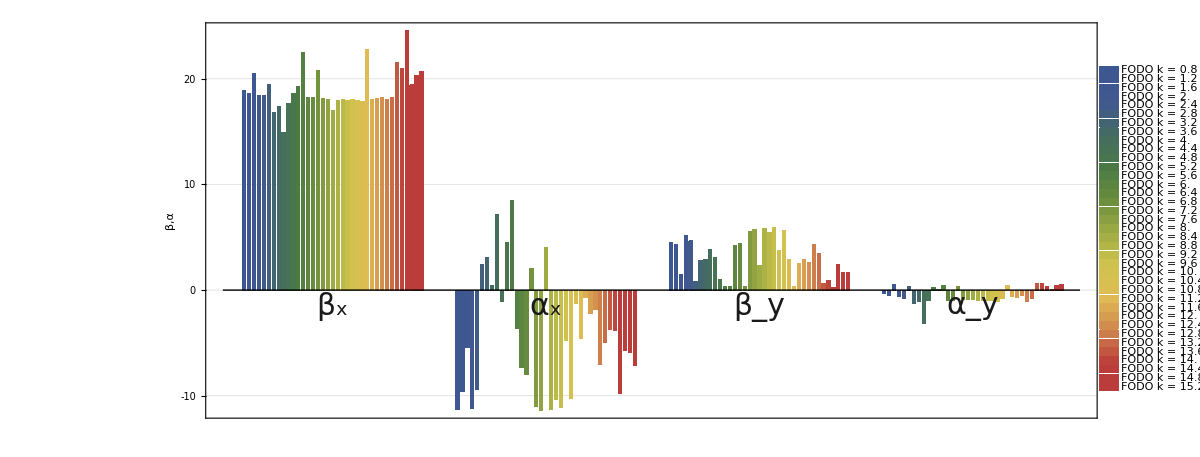

```mathematica
opticsmu1plot=ShowLegend[BarChart[Transpose[felmatch⟦2;;-1;;4⟧⟦All,2;;-1⟧],ChartLabels->{Table["",{Length[felmatch⟦2,2;;-1⟧]}],Placed[(Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->30]&/@{"β_x","α_x","β_y","α_y"}),Axis],Table["",{Length[felmatch⟦2,2;;-1⟧]}]},ChartStyle->"DarkRainbow",BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.001],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.5,10},FrameLabel->{{"β,α",""},{"",""}},FrameTicks->{{LinTicks[-20,30,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-20,30,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,AxesOrigin->{0,0},Axes->True],{Transpose[{ColorData["DarkRainbow",#/Length[vals]]&/@Table[i,{i,0,Length[vals]-1}],"FODO k = "<>ToString[#]&/@vals}],LegendPosition->{0.9,-0.35},LegendSize->{0.2,0.7},LegendShadow->None,LegendTextSpace->3}]
```

```mathematica
Export["clara_fel_opticsmu1.png",opticsmu1plot,ImageResolution->300]
```

clara_fel_opticsmu1.png

## Now replace with a chicane - Also with undulator focusing

We start with

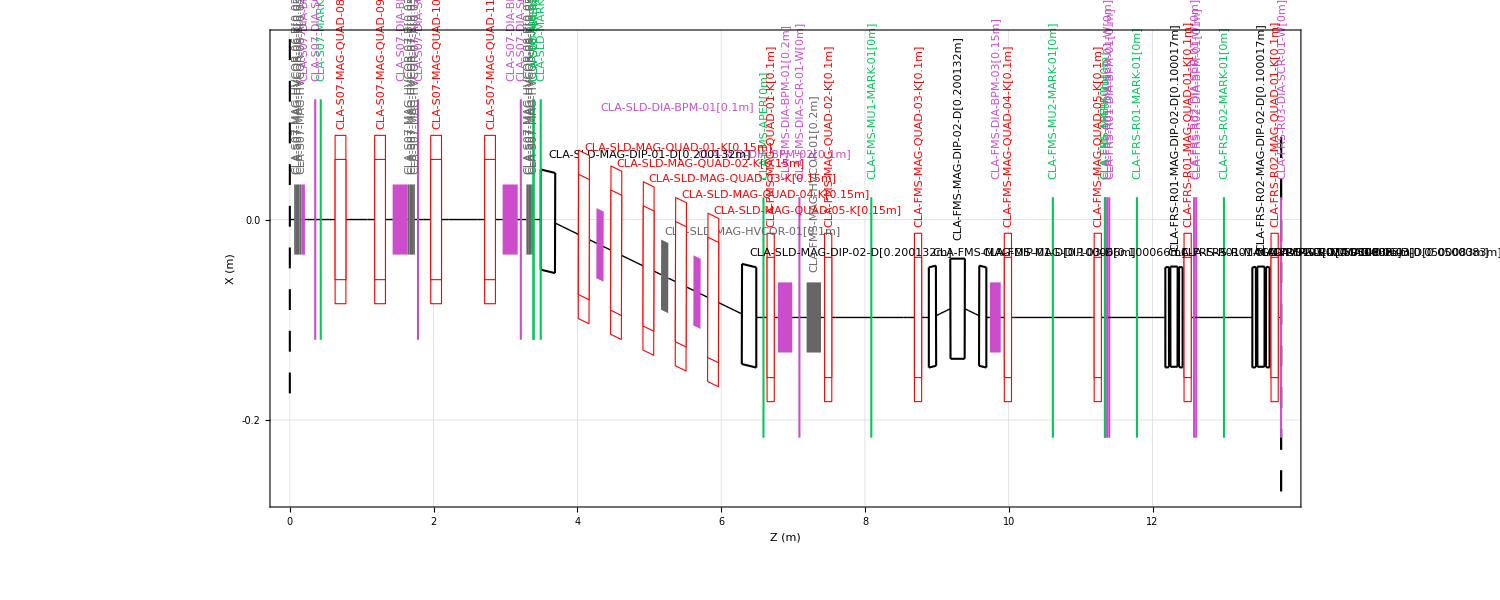

```mathematica
sld=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM⟦339;;497⟧],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,Lengths->True,FrameLabel-> {"Z (m)","X (m)"},FrameTicks->{LinTicks[0,13,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,13,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->False,WidthScale->0.5,GridLines->Automatic,BaseStyle->{FontSize->20,FontFamily->"Helvetica",Black},ImageSize->1500,PlotRange->All]
```

```mathematica
(*Export["clara_sld.png",sld,ImageResolution->400]*)
```

clara_sld.png

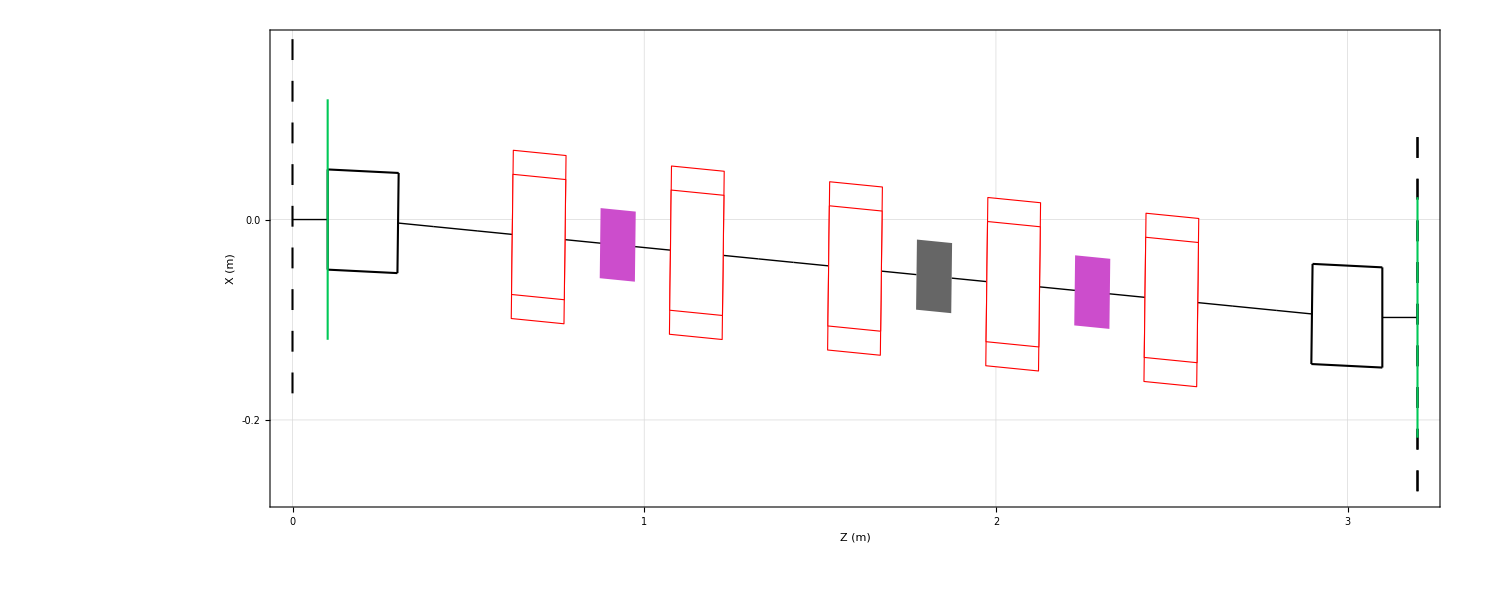

```mathematica
sldipac=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[$DRAWLATTICEBPM⟦380;;408⟧],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,Lengths->True,FrameLabel-> {"Z (m)","X (m)"},FrameTicks->{LinTicks[0,5,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->False,WidthScale->0.5,GridLines->Automatic,BaseStyle->{FontSize->28,FontFamily->"Helvetica",Black},ImageSize->1500,PlotRange->All]
```

```mathematica
Export["clara_sld_ipac.png",sldipac,ImageResolution->400]
```

clara_sld_ipac.png

...and we want to match to...

### FODO with delay chicanes

```mathematica
LATTICE=MADFlatten[{CLA£FRS}]⟦1;;-22⟧;
```

```mathematica
test=MADFlatten[{CLA£FRS}]⟦1;;50⟧;
```

```mathematica
test2=MADFlatten[{CLA£FRS}]⟦1;;43⟧;
```

```mathematica
MADInfo[test2]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£FRS£APER | Marker | 0 | --- | --- | --- | CLA£FRS£APER | 0
2 | CLA£FRS£R01£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£B | 0.03
3 | CLA£FRS£R01£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£W | 0.03
4 | CLA£FRS£R01£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£A | 0.06
5 | CLA£FRS£R01£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R01£DIA£BPM£01 | 0.06
6 | CLA£FRS£R01£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£UND£B | 0.07
7 | CLA£FRS£R01£MAG£UND£W£H1 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1 | 0.445
8 | CLA£FRS£R01£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R01£MARK£01 | 0.445
9 | CLA£FRS£R01£MAG£UND£W£H2 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H2 | 0.82
10 | CLA£FRS£R01£MAG£UND£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£UND£A | 0.83
11 | CLA£FRS£R01£MAG£DIP£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£01£B | 0.84
12 | CLA£FRS£R01£MAG£DIP£01£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R01£MAG£DIP£01£D | 0.890008
13 | CLA£FRS£R01£MAG£DIP£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£01£A | 0.900008
14 | CLA£FRS£R01£MAG£DIP£02£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£02£B | 0.910008
15 | CLA£FRS£R01£MAG£DIP£02£D | SectorBend | 0.100017 | 0 | --- | 0.0349066 | CLA£FRS£R01£MAG£DIP£02£D | 1.01002
16 | CLA£FRS£R01£MAG£DIP£02£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£02£A | 1.02002
17 | CLA£FRS£R01£MAG£DIP£03£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£03£B | 1.03002
18 | CLA£FRS£R01£MAG£DIP£03£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R01£MAG£DIP£03£D | 1.08003
19 | CLA£FRS£R01£MAG£DIP£03£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£03£A | 1.09003
20 | CLA£FRS£R01£MAG£QUAD£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£QUAD£01£B | 1.10003
21 | CLA£FRS£R01£MAG£QUAD£01£K | Quadrupole | 0.1 | -1. | --- | --- | CLA£FRS£R01£MAG£QUAD£01£K | 1.20003
22 | CLA£FRS£R01£MAG£QUAD£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£QUAD£01£A | 1.21003
23 | CLA£FRS£R02£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£B | 1.24003
24 | CLA£FRS£R02£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£W | 1.24003
25 | CLA£FRS£R02£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£A | 1.27003
26 | CLA£FRS£R02£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R02£DIA£BPM£01 | 1.27003
27 | CLA£FRS£R02£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£UND£B | 1.28003
28 | CLA£FRS£R02£MAG£UND£W£H1 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R02£MAG£UND£W£H1 | 1.65503
29 | CLA£FRS£R02£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R02£MARK£01 | 1.65503
30 | CLA£FRS£R02£MAG£UND£W£H2 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R02£MAG£UND£W£H2 | 2.03003
31 | CLA£FRS£R02£MAG£UND£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£UND£A | 2.04003
32 | CLA£FRS£R02£MAG£DIP£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£01£B | 2.05003
33 | CLA£FRS£R02£MAG£DIP£01£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R02£MAG£DIP£01£D | 2.10004
34 | CLA£FRS£R02£MAG£DIP£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£01£A | 2.11004
35 | CLA£FRS£R02£MAG£DIP£02£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£02£B | 2.12004
36 | CLA£FRS£R02£MAG£DIP£02£D | SectorBend | 0.100017 | 0 | --- | 0.0349066 | CLA£FRS£R02£MAG£DIP£02£D | 2.22006
37 | CLA£FRS£R02£MAG£DIP£02£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£02£A | 2.23006
38 | CLA£FRS£R02£MAG£DIP£03£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£03£B | 2.24006
39 | CLA£FRS£R02£MAG£DIP£03£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R02£MAG£DIP£03£D | 2.29007
40 | CLA£FRS£R02£MAG£DIP£03£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£03£A | 2.30007
41 | CLA£FRS£R02£MAG£QUAD£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£QUAD£01£B | 2.31007
42 | CLA£FRS£R02£MAG£QUAD£01£K | Quadrupole | 0.1 | -1. | --- | --- | CLA£FRS£R02£MAG£QUAD£01£K | 2.41007
43 | CLA£FRS£R02£MAG£QUAD£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£QUAD£01£A | 2.42007

Total Length = 2.42007 m

```mathematica
Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[2,1,1]]-Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[1,1,1]]
```

1.21002

So structure of CLARA FODO is

Remember to get the edge angles right - they are rectangular

```mathematica
marker[M11D0CMS]
marker[M11D0CME]
sbend[M11D0CB1,0.0500083,0,-0.0174533,"M11D0CB1",E2->-0.0174533]
drift[M11D0CBD,0.02,"M11D0CBD"]
sbend[M11D0CB2,0.100017,0,0.0349066,"M11D0CB2",E1->0.0174533,E2->0.0174533]
sbend[M11D0CB3,0.0500083,0,-0.0174533,"M11D0CB3",E1->-0.0174533]
drift[M11D0CD1H2,(1.21002-0.1)/2,"M11D0CD1H2"]
drift[M11D0CD2,0.85,"M11D0CD2"]
drift[M11D0CD1H1,(1.21002-0.1)/2-0.26002,"M11D0CD1H1"]
quad[M11D0CQ1,0.10,3,"M11D0CQ1"]
quad[M11D0CQ2,0.10,-3,"M11D0CQ2"]
line[M11D0RC,{M11D0CMS,M11D0CD1H1,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ1,M11D0CD2,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ2,M11D0CD1H2,M11D0CME}]
```

```mathematica
M11D0CB2
```

{{M11D0CB2,SectorBend,0.100017,0,---,0.0349066,M11D0CB2}}

```mathematica
M11D0CB2Extra
```

{M11D0CB2,Extra,0,0,0.0174533,0.0174533,0,0,0,0,0,0,0}

```mathematica
MADInfo[M11D0RC]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | M11D0CMS | Marker | 0 | --- | --- | --- |  | 0
2 | M11D0CD1H1 | Drift | 0.29499 | --- | --- | --- | M11D0CD1H1 | 0.29499
3 | M11D0CB1 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB1 | 0.344998
4 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 0.364998
5 | M11D0CB2 | SectorBend | 0.100017 | 0 | --- | 0.0349066 | M11D0CB2 | 0.465015
6 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 0.485015
7 | M11D0CB3 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB3 | 0.535024
8 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 0.555024
9 | M11D0CQ1 | Quadrupole | 0.1 | 3 | --- | --- | M11D0CQ1 | 0.655024
10 | M11D0CD2 | Drift | 0.85 | --- | --- | --- | M11D0CD2 | 1.50502
11 | M11D0CB1 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB1 | 1.55503
12 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 1.57503
13 | M11D0CB2 | SectorBend | 0.100017 | 0 | --- | 0.0349066 | M11D0CB2 | 1.67505
14 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 1.69505
15 | M11D0CB3 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB3 | 1.74506
16 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 1.76506
17 | M11D0CQ2 | Quadrupole | 0.1 | -3 | --- | --- | M11D0CQ2 | 1.86506
18 | M11D0CD1H2 | Drift | 0.55501 | --- | --- | --- | M11D0CD1H2 | 2.42007
19 | M11D0CME | Marker | 0 | --- | --- | --- |  | 2.42007

Total Length = 2.42007 m

```mathematica
MADWrite["M11D0R",M11D0RC];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g M11D0R.mff",Word]];
MADStringWrite["M11D0R","eopt,add;\n"];
MADStringWrite["M11D0R","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.135]<>";\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.1\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.2\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.3\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.4\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.5\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.6\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.7\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.8\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.9\n"];
MADStringWrite["M11D0R","select,twiss,full;\ntwiss,tape=twiss.txt;\n"];
MADStringWrite["M11D0R","select,optics,full;\noptics,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat M11D0R.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < M11D0R.mff > M11D0R_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < M11D0R.mff > M11D0R.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->True];
Select[ReadList["M11D0R.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&];
```

{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}

Variables (re-)assigned: {GAMTR,ALFA,XIY,XIX,QY,QX,CIRCUM,DELTA,TYPE,COMMENT,ORIGIN,DATE,TIME}

Variables (re-)assigned: {NAME,S,BETX,BETY,DX,ALFX,ALFY,MUX,MUY,DPX,DY,DPY}

```mathematica
MatchTwiss=First[#]&/@{BETX,ALFX,BETY,ALFY}
```

{6.86201,-1.0451,4.90304,0.741309}

```mathematica
ToString[NumberForm[MADLength[M11D0RC],3]]
```

2.42

```mathematica
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{0.3,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["β_min = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,21}],
Text[Style["β_max = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,19}],
Text[Style["β_max-β_min = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,17}],
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RC],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,15}],
Text[Style[ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,13}],
Text[Style["(β_max+β_min)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,11}]},Prolog->MADDraw[Select[MADFlatten[M11D0RC], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,22}},ImageSize->900,AspectRatio->0.5];
(*{Show[#],Export["output/run_B_pw01_twiss_mma.png",#,ImageResolution->400],Export["output/run_B_pw01_twiss_mma.eps",#,ImageSize->900,ImageResolution->200]}&@*)ShowLegend[plt,lgd]
Print["done"]
```

-Graphics-

done

scan over k -values

```mathematica
vals=Table[i,{i,0.8,14.4,0.4}];
```

```mathematica
vals
```

{0.8,1.2,1.6,2.,2.4,2.8,3.2,3.6,4.,4.4,4.8,5.2,5.6,6.,6.4,6.8,7.2,7.6,8.,8.4,8.8,9.2,9.6,10.,10.4,10.8,11.2,11.6,12.,12.4,12.8,13.2,13.6,14.,14.4}

```mathematica
vals2=(1/((M11D0CQ1⟦1,3⟧/2)#) 1/(MADLength[M11D0RC]/2))&[vals]
```

{20.6606,13.7737,10.3303,8.26423,6.88686,5.90302,5.16515,4.59124,4.13212,3.75647,3.44343,3.17855,2.95151,2.75474,2.58257,2.43066,2.29562,2.1748,2.06606,1.96767,1.87823,1.79657,1.72172,1.65285,1.58928,1.53041,1.47576,1.42487,1.37737,1.33294,1.29129,1.25216,1.21533,1.1806,1.14781}

```mathematica
betavs=Reap[(
marker[M11D0CMS]
marker[M11D0CME]
sbend[M11D0CB1,0.0500083,0,-0.0174533,"M11D0CB1",E2->-0.0174533]
drift[M11D0CBD,0.02,"M11D0CBD"]
sbend[M11D0CB2,0.100017,0,0.0349066,"M11D0CB2",E1->0.0174533,E2->0.0174533]
sbend[M11D0CB3,0.0500083,0,-0.0174533,"M11D0CB3",E1->-0.0174533]
drift[M11D0CD1H2,(1.21002-0.1)/2,"M11D0CD1H2"]
drift[M11D0CD2,0.85,"M11D0CD2"]
drift[M11D0CD1H1,(1.21002-0.1)/2-0.26002,"M11D0CD1H1"]
quad[M11D0CQ1,0.10,#,"M11D0CQ1"]
quad[M11D0CQ2,0.10,-#,"M11D0CQ2"]
line[M11D0RC,Table[{M11D0CMS,M11D0CD1H1,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ1,M11D0CD2,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ2,M11D0CD1H2,M11D0CME},1]]
MADWrite["M11D0R",M11D0RC];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g M11D0R.mff",Word]];
MADStringWrite["M11D0R","eopt,add;\n"];
	MADStringWrite["M11D0R","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.05\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.10\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.15\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.20\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.25\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.30\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.35\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.40\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.45\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.50\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.55\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.60\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.65\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.70\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.75\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.80\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.85\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.90\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.95\n"];
MADStringWrite["M11D0R","select,twiss,full;\ntwiss,tape=twiss.txt;\n"];
MADStringWrite["M11D0R","select,optics,full;\noptics,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat M11D0R.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < M11D0R.mff > M11D0R_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < M11D0R.mff > M11D0R.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
Select[ReadList["M11D0R.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&];
Sow[{Mean[BETX],Mean[BETY]}];
Sow[First[#]&/@{BETX,ALFX,BETY,ALFY}];
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["k = "<>ToString[#],FontFamily->"Helvetica",Bold,FontSize->14],{1.3,21}],
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RC],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.3,19}],
Text[Style["β_xmin = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,17}],
Text[Style["β_xmax = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,15}],
Text[Style["β_xmax-β_xmin = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,13}],
Text[Style[ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,11}],
Text[Style["(β_xmax+β_xmin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,9}],
Text[Style["β_ymin = "<>ToString[NumberForm[Min[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,17}],
Text[Style["β_ymax = "<>ToString[NumberForm[Max[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,15}],
Text[Style["β_ymax-β_ymin = "<>ToString[NumberForm[(Max[BETY]-Min[BETY]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,13}],
Text[Style[ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Mean[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,11}],
Text[Style["(β_ymax+β_ymin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETY])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,9}]},Prolog->MADDraw[Select[MADFlatten[M11D0RC], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,30}},ImageSize->700,AspectRatio->0.5];
Sow[Show[plt]];

)&/@vals]⟦2,1⟧;
```

```mathematica
GraphicsGrid[Partition[betavs⟦3;;-1;;3⟧,2],Frame->All];
```

```mathematica
betavs⟦6⟧
```

-Graphics-

```mathematica
(*Export["clara_frs_fodo_k12.png",betavs⟦6⟧,ImageResolution->200]*)
```

```mathematica
Take[betavs,{1,-1,3}]
```

{{25.7317,6.80882},{17.1678,6.53475},{12.8899,6.20253},{10.3266,5.84333},{8.62052,5.48115},{7.40446,5.13181},{6.49473,4.80431},{5.78931,4.50278},{5.22701,4.22825},{4.76891,3.97996},{4.38908,3.75623},{4.06957,3.55498},{3.79758,3.37407},{3.56377,3.21143},{3.36112,3.06515},{3.1843,2.93355},{3.02918,2.81513},{2.89256,2.70861},{2.77187,2.61287},{2.66509,2.52698},{2.5706,2.45016},{2.48713,2.38177},{2.41366,2.32133},{2.34942,2.26847},{2.29384,2.22296},{2.24656,2.1847},{2.20738,2.15377},{2.17634,2.13041},{2.15368,2.11511},{2.13994,2.10864},{2.13604,2.11218},{2.14336,2.1275},{2.16407,2.15728},{2.20147,2.20561},{2.26078,2.27906}}

```mathematica
Min[Take[betavs,{1,-1,3}]]
```

2.10864

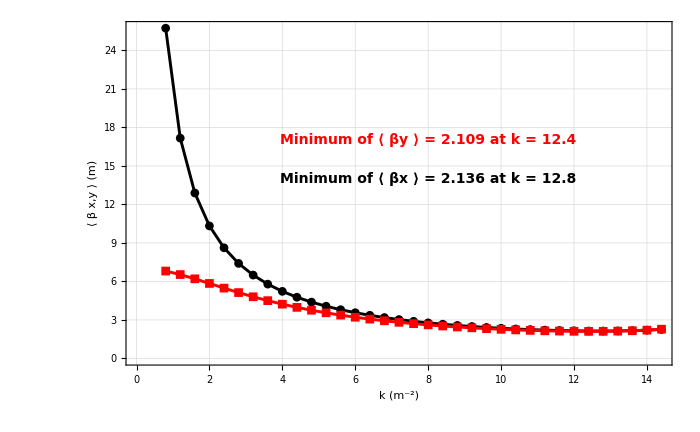

```mathematica
plt1=ListLinePlot[{Transpose[{vals,Take[betavs,{1,-3,3}]⟦All,1⟧}],Transpose[{vals,Take[betavs,{1,-3,3}]⟦All,2⟧}]},Epilog->{Text[Style["Minimum of "<>ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-3,3}]⟦All,1⟧],4]]<>" at k = "<>ToString[vals[[Position[#,Min[#]]&[Take[betavs,{1,-3,3}]⟦All,1⟧]⟦1,1⟧]]],FontFamily->"Helvetica",Bold,FontSize->14],{8,14}],Text[Style["Minimum of "<>ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-3,3}]⟦All,2⟧],4]]<>" at k = "<>ToString[vals[[Position[#,Min[#]]&[Take[betavs,{1,-3,3}]⟦All,2⟧]⟦1,1⟧]]],FontFamily->"Helvetica",Bold,Red,FontSize->14],{8,17}]},PlotMarkers->Automatic,Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{ToString[AngleBracket["β x,y"]]<>" (m)",""},{"k (m^-2)",""}},GridLines->Automatic,PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]}},LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->700,PlotRange->{{0,QuantityMagnitude[Last[vals]]},All}]
```

```mathematica
(*Export["clara_frs_fodo_kscan2.png",plt1,ImageResolution->200]*)
```

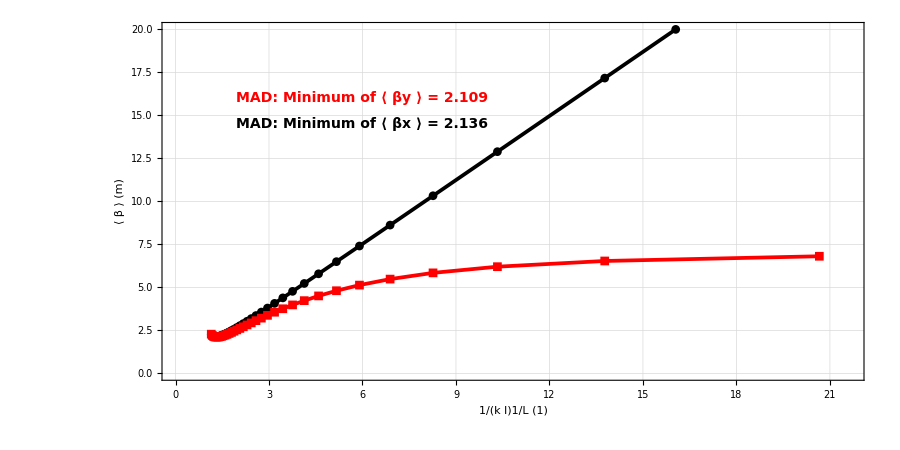

```mathematica
plt2=ListLinePlot[{Transpose[{vals2,Take[betavs,{1,-1,3}]⟦All,1⟧}],Transpose[{vals2,Take[betavs,{1,-1,3}]⟦All,2⟧}]},Epilog->{Text[Style["MAD: Minimum of "<>ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-1,3}]⟦All,1⟧],4]],FontFamily->"Helvetica",Bold,Black,FontSize->14],{6,14.5}],Text[Style["MAD: Minimum of "<>ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-1,3}]⟦All,2⟧],4]],FontFamily->"Helvetica",Bold,Red,FontSize->14],{6,16}]},PlotMarkers->Automatic,Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{ToString[AngleBracket["β"]]<>" (m)",""},{"1/(k l)1/L (1)",""}},GridLines->Automatic,PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]}},LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImagePadding->100,ImageSize->900,AspectRatio->0.5,PlotRange->{{0,QuantityMagnitude[First[vals2]]+1},{0,20}}]
```

```mathematica
plt3=Plot[{(MADLength[M11D0RC]/2 )x^2(x^2-1)^(-1/2),(MADLength[M11D0RC]/2 )x},{x,0,QuantityMagnitude[First[vals2]]+1},Frame->{False,False,False,True},Epilog->{Style[Text["Wiedemann: Minimum of "<>ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[FindMinimum[(MADLength[M11D0RC]/2 )x^2(x^2-1)^(-1/2),{x,1.1}]⟦1⟧,{3,3}]],{5.4,13}],Darker[Green],Bold,FontSize->14],Style[Text["Pfluger",{6,12}],Blue,Bold,FontSize->14]},PlotStyle->{Darker[Green],Blue},FrameTicks->{{None,Range[0,25,5]},{Automatic,None}},LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},PlotRange->{{0,QuantityMagnitude[First[vals2]]+1},{0,20}},ImagePadding->100,AspectRatio->0.5,ImageSize->900];
```

```mathematica
plt4=Overlay[{plt2,plt3}]
```

-Graphics--Graphics-

```mathematica
(*Export["clara_frs_fodo_rescale2.png",plt4,ImageResolution->200]*)
```

```mathematica
FodoTwiss=Transpose[{vals,betavs⟦2;;-1;;3⟧}]
```

{{0.8,{25.7192,-1.02988,6.77861,0.250167}},{1.2,{17.1468,-1.0313,6.50065,0.372916}},{1.6,{12.8609,-1.03331,6.16346,0.480304}},{2.,{10.2895,-1.03592,5.79844,0.57187}},{2.4,{8.57555,-1.03912,5.42979,0.648819}},{2.8,{7.35152,-1.04295,5.0735,0.713167}},{3.2,{6.43376,-1.04742,4.73866,0.767122}},{3.6,{5.72022,-1.05256,4.42947,0.812755}},{4.,{5.1497,-1.05839,4.14701,0.851854}},{4.4,{4.68324,-1.06495,3.89054,0.885898}},{4.8,{4.29488,-1.07228,3.65839,0.91609}},{5.2,{3.96667,-1.08042,3.44848,0.943394}},{5.6,{3.68579,-1.08942,3.25865,0.968588}},{6.,{3.44284,-1.09935,3.08682,0.992303}},{6.4,{3.2308,-1.11026,2.93106,1.01506}},{6.8,{3.04429,-1.12225,2.78965,1.0373}},{7.2,{2.87917,-1.1354,2.66107,1.0594}},{7.6,{2.73216,-1.14981,2.54397,1.0817}},{8.,{2.60067,-1.16562,2.43722,1.10452}},{8.4,{2.48263,-1.18296,2.33982,1.12815}},{8.8,{2.37635,-1.202,2.25092,1.1529}},{9.2,{2.28048,-1.22296,2.16982,1.17909}},{9.6,{2.19393,-1.24605,2.09592,1.20705}},{10.,{2.11582,-1.27159,2.02876,1.23717}},{10.4,{2.04546,-1.29991,1.96797,1.26989}},{10.8,{1.98234,-1.33144,1.9133,1.30572}},{11.2,{1.92609,-1.36672,1.86462,1.3453}},{11.6,{1.87652,-1.40642,1.82193,1.3894}},{12.,{1.83358,-1.45139,1.78539,1.43901}},{12.4,{1.79745,-1.50275,1.75534,1.49541}},{12.8,{1.76854,-1.56197,1.7324,1.56032}},{13.2,{1.7476,-1.63106,1.71759,1.63609}},{13.6,{1.73584,-1.71284,1.71246,1.72606}},{14.,{1.73526,-1.81142,1.71951,1.83518}},{14.4,{1.74902,-1.93302,1.7428,1.97115}}}

So now we have the FODO with the chicanes, but should we add the undulator focusing - do this later .....
Lets add a chicane

```mathematica
θ=0.1;l=0.1;
```

```mathematica
marker[CLA£SLC£MARK£01]
marker[CLA£SLC£MARK£02]
marker[CLA£SLC£MARK£03]
sbend[CLA£SLC£MAG£DIP£01,l/Sin[θ] θ,0,θ,"CLA£SLC£MAG£DIP£01",E2->θ]
sbend[CLA£SLC£MAG£DIP£02,l/Sin[θ] θ,0,-θ,"CLA£SLC£MAG£DIP£02",E1->-θ]
sbend[CLA£SLC£MAG£DIP£03,l/Sin[θ] θ,0,-θ,"CLA£SLC£MAG£DIP£03",E2->-θ]
sbend[CLA£SLC£MAG£DIP£04,l/Sin[θ] θ,0,θ,"CLA£SLC£MAG£DIP£04",E1->θ]
drift[CLA£SLC£DRIFT£01,0.2/Cos[θ],"CLA£SLC£DRIFT£01"]
drift[CLA£SLC£DRIFT£02,0.05,"CLA£SLC£DRIFT£02"]
drift[CLA£SLC£DRIFT£03,0.05,"CLA£SLC£DRIFT£03"]
drift[CLA£SLC£DRIFT£04,0.2/Cos[θ],"CLA£SLC£DRIFT£04"]
line[CLA£SLC,{CLA£SLC£MARK£01,CLA£SLC£MAG£DIP£01,CLA£SLC£DRIFT£01,CLA£SLC£MAG£DIP£02,CLA£SLC£DRIFT£02,CLA£SLC£MARK£02,CLA£SLC£DRIFT£03,CLA£SLC£MAG£DIP£03,CLA£SLC£DRIFT£04,CLA£SLC£MAG£DIP£04,CLA£SLC£MARK£03}]
```

```mathematica
MADInfo[CLA£SLC]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£SLC£MARK£01 | Marker | 0 | --- | --- | --- |  | 0
2 | CLA£SLC£MAG£DIP£01 | SectorBend | 0.100167 | 0 | --- | 0.1 | CLA£SLC£MAG£DIP£01 | 0.100167
3 | CLA£SLC£DRIFT£01 | Drift | 0.201004 | --- | --- | --- | CLA£SLC£DRIFT£01 | 0.301171
4 | CLA£SLC£MAG£DIP£02 | SectorBend | 0.100167 | 0 | --- | -0.1 | CLA£SLC£MAG£DIP£02 | 0.401338
5 | CLA£SLC£DRIFT£02 | Drift | 0.05 | --- | --- | --- | CLA£SLC£DRIFT£02 | 0.451338
6 | CLA£SLC£MARK£02 | Marker | 0 | --- | --- | --- |  | 0.451338
7 | CLA£SLC£DRIFT£03 | Drift | 0.05 | --- | --- | --- | CLA£SLC£DRIFT£03 | 0.501338
8 | CLA£SLC£MAG£DIP£03 | SectorBend | 0.100167 | 0 | --- | -0.1 | CLA£SLC£MAG£DIP£03 | 0.601505
9 | CLA£SLC£DRIFT£04 | Drift | 0.201004 | --- | --- | --- | CLA£SLC£DRIFT£04 | 0.802509
10 | CLA£SLC£MAG£DIP£04 | SectorBend | 0.100167 | 0 | --- | 0.1 | CLA£SLC£MAG£DIP£04 | 0.902676
11 | CLA£SLC£MARK£03 | Marker | 0 | --- | --- | --- |  | 0.902676

Total Length = 0.902676 m

```mathematica
MADPositions[CLA£SLC]
```

{{{0,0},{marker,0,0,,0,{CLA£SLC£MARK£01,Marker,0,---,---,---,}},0},{{0,0},{dipole,0.100167,-0.1,,0,{CLA£SLC£MAG£DIP£01,SectorBend,0.100167,0,---,0.1,CLA£SLC£MAG£DIP£01}},0},{{0.1,-0.00500417},{drift,0.201004,0,,0,{CLA£SLC£DRIFT£01,Drift,0.201004,---,---,---,CLA£SLC£DRIFT£01}},-5.72958},{{0.3,-0.0250711},{dipole,0.100167,0.1,,0,{CLA£SLC£MAG£DIP£02,SectorBend,0.100167,0,---,-0.1,CLA£SLC£MAG£DIP£02}},-5.72958},{{0.4,-0.0300753},{drift,0.05,0,,0,{CLA£SLC£DRIFT£02,Drift,0.05,---,---,---,CLA£SLC£DRIFT£02}},0.},{{0.45,-0.0300753},{marker,0,0,,0,{CLA£SLC£MARK£02,Marker,0,---,---,---,}},0.},{{0.45,-0.0300753},{drift,0.05,0,,0,{CLA£SLC£DRIFT£03,Drift,0.05,---,---,---,CLA£SLC£DRIFT£03}},0.},{{0.5,-0.0300753},{dipole,0.100167,0.1,,0,{CLA£SLC£MAG£DIP£03,SectorBend,0.100167,0,---,-0.1,CLA£SLC£MAG£DIP£03}},0.},{{0.6,-0.0250711},{drift,0.201004,0,,0,{CLA£SLC£DRIFT£04,Drift,0.201004,---,---,---,CLA£SLC£DRIFT£04}},5.72958},{{0.8,-0.00500417},{dipole,0.100167,-0.1,,0,{CLA£SLC£MAG£DIP£04,SectorBend,0.100167,0,---,0.1,CLA£SLC£MAG£DIP£04}},5.72958},{{0.9,4.33681×10^-18},{marker,0,0,,0,{CLA£SLC£MARK£03,Marker,0,---,---,---,}},0.},{{0.9,4.33681×10^-18},{drift,0,0,,0},0.}}

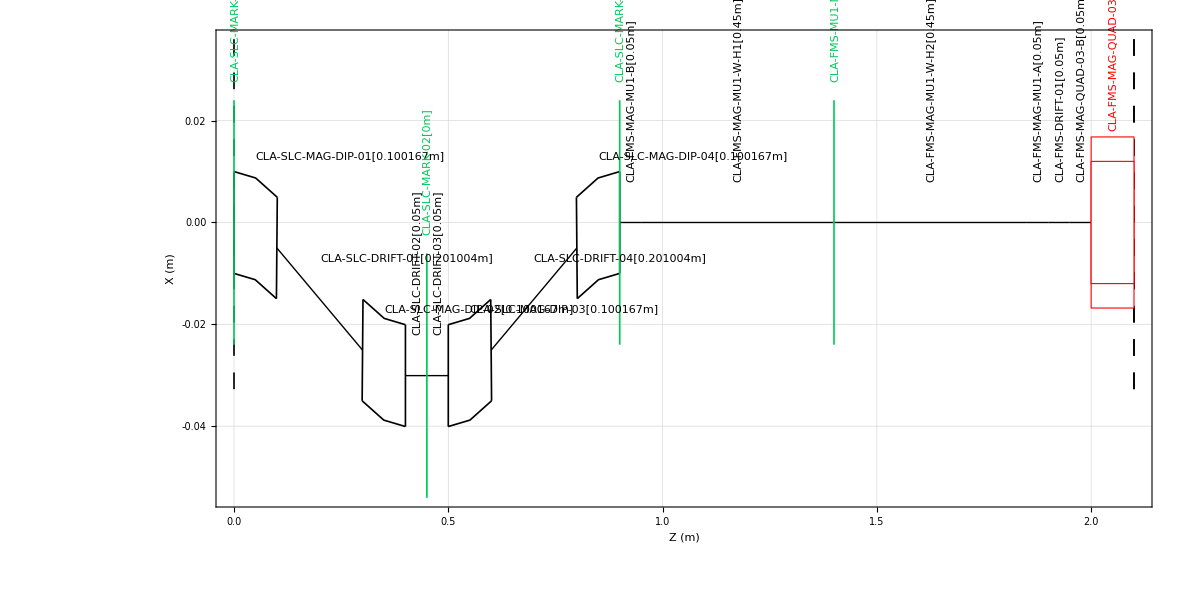

```mathematica
slc=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[{CLA£SLC,MADFlatten[CLA£FMS]⟦13;;20⟧}],Bends->True,Labels->True,Frame->True,DriftLabels->True,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"}, FrameTicks->{LinTicks[0,2,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,2,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->True,WidthScale->0.1,GridLines->Automatic,BaseStyle->{FontSize->14,Bold,FontFamily->"Helvetica",Black},AspectRatio->0.5,ImageSize->1200]
```

```mathematica
Export["clara_slc.png",slc,ImageResolution->400]
```

clara_slc.png

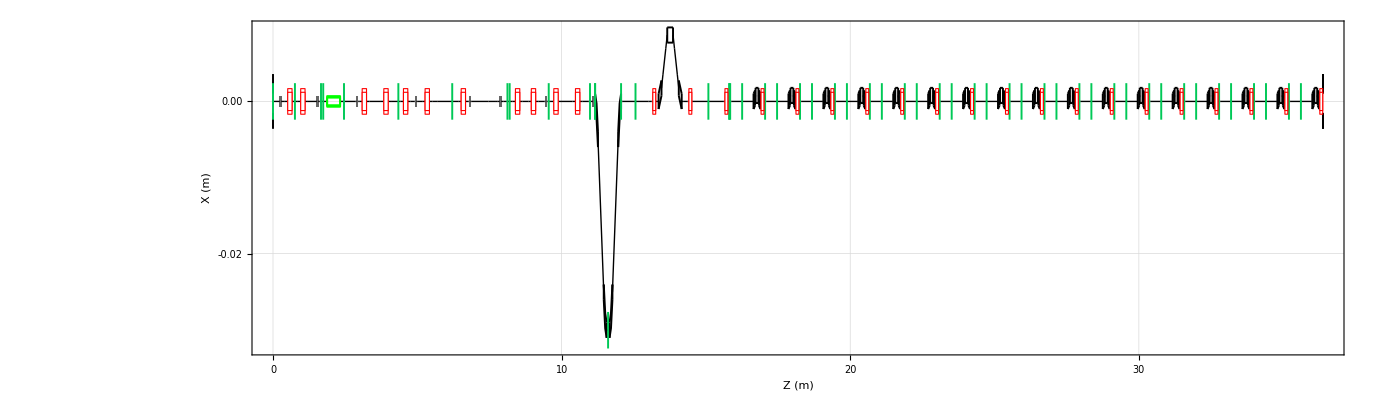

```mathematica
claraslcfel=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[{CLA£S07,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS}],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"}, FrameTicks->{LinTicks[0,40,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,40,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->False,WidthScale->0.01,GridLines->Automatic,BaseStyle->{FontSize->14,Bold,FontFamily->"Helvetica",Black},AspectRatio->0.3,ImageSize->1400]
```

```mathematica
Export["clara_slc_fel.png",claraslcfel,ImageResolution->400]
```

clara_slc_fel.png

At the TDC screen the matched twiss are these - lets match from them...

```mathematica
StartTwiss=CLA£S07£DIA£SCR£03£WTwiss={1,0,1,0};
```

```mathematica
LATTICE=$LATTICE=MADFlatten[{MADFlatten[CLA£S07]⟦Position[MADFlatten[CLA£S07],Select[MADFlatten[CLA£S07],#⟦1⟧=="CLA£S07£DIA£SCR£03£W"&]⟦1⟧]⟦1,1⟧;;-1⟧,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS,CLA£FAB,CLA£PFD}];
```

```mathematica
matchedqs={#⟦1⟧,#⟦4⟧}&/@Select[MADFlatten[$LATTICE],#[[2]]=="Quadrupole"&]
```

{{CLA£S07£MAG£QUAD£08£K,-1.71192},{CLA£S07£MAG£QUAD£09£K,-5.98555},{CLA£S07£MAG£QUAD£10£K,7.72644},{CLA£S07£MAG£QUAD£11£K,-5.24599},{CLA£FMS£MAG£QUAD£03£K,-1.},{CLA£FMS£MAG£QUAD£04£K,-1.},{CLA£FMS£MAG£QUAD£05£K,-1.},{CLA£FRS£R01£MAG£QUAD£01£K,-1.},{CLA£FRS£R02£MAG£QUAD£01£K,-1.},{CLA£FRS£R03£MAG£QUAD£01£K,-1.},{CLA£FRS£R04£MAG£QUAD£01£K,-1.},{CLA£FRS£R05£MAG£QUAD£01£K,-1.},{CLA£FRS£R06£MAG£QUAD£01£K,-1.},{CLA£FRS£R07£MAG£QUAD£01£K,-1.},{CLA£FRS£R08£MAG£QUAD£01£K,-1.},{CLA£FRS£R09£MAG£QUAD£01£K,-1.},{CLA£FRS£R10£MAG£QUAD£01£K,-1.},{CLA£FRS£R11£MAG£QUAD£01£K,-1.},{CLA£FRS£R12£MAG£QUAD£01£K,-1.},{CLA£FRS£R13£MAG£QUAD£01£K,-1.},{CLA£FRS£R14£MAG£QUAD£01£K,-1.},{CLA£FRS£R15£MAG£QUAD£01£K,-1.},{CLA£FRS£R16£MAG£QUAD£01£K,-1.},{CLA£FRS£R17£MAG£QUAD£01£K,-1.},{CLA£PFD£MAG£QUAD£01£K,-1.46779},{CLA£PFD£MAG£QUAD£02£K,-0.64689},{CLA£PFD£MAG£QUAD£03£K,-2.01504},{CLA£PFD£MAG£QUAD£04£K,0.98372},{CLA£PFD£MAG£QUAD£05£K,4.25217},{CLA£PFD£MAG£QUAD£06£K,-2.6469}}

```mathematica
matchedqs⟦5,1⟧
```

CLA£FMS£MAG£QUAD£03£K

```mathematica
matchedqs⟦6;;25;;2,1⟧
```

{CLA£FMS£MAG£QUAD£04£K,CLA£FRS£R01£MAG£QUAD£01£K,CLA£FRS£R03£MAG£QUAD£01£K,CLA£FRS£R05£MAG£QUAD£01£K,CLA£FRS£R07£MAG£QUAD£01£K,CLA£FRS£R09£MAG£QUAD£01£K,CLA£FRS£R11£MAG£QUAD£01£K,CLA£FRS£R13£MAG£QUAD£01£K,CLA£FRS£R15£MAG£QUAD£01£K,CLA£FRS£R17£MAG£QUAD£01£K}

```mathematica
matchedqs⟦7;;25;;2,1⟧
```

{CLA£FMS£MAG£QUAD£05£K,CLA£FRS£R02£MAG£QUAD£01£K,CLA£FRS£R04£MAG£QUAD£01£K,CLA£FRS£R06£MAG£QUAD£01£K,CLA£FRS£R08£MAG£QUAD£01£K,CLA£FRS£R10£MAG£QUAD£01£K,CLA£FRS£R12£MAG£QUAD£01£K,CLA£FRS£R14£MAG£QUAD£01£K,CLA£FRS£R16£MAG£QUAD£01£K,CLA£PFD£MAG£QUAD£01£K}

needed to change the distances of the inserted elements as forgot to take off quad length from the half cell length

```mathematica
felmatch=Reap[Map[Function[p2,(
Map[Function[p1,quad[p1,0.10,p2⟦1⟧,ToString[p1]]],matchedqs⟦6;;25;;2,1⟧];
Map[Function[p1,quad[p1,0.10,-p2⟦1⟧,ToString[p1]]],matchedqs⟦7;;25;;2,1⟧];
Map[Function[p1,quad[p1,0.10,-p2⟦1⟧,ToString[p1]]],matchedqs⟦5,1⟧];
Map[Function[p1,quad[p1,0.10,10,ToString[p1]]],matchedqs⟦1,1⟧];
Map[Function[p1,quad[p1,0.10,0,ToString[p1]]],matchedqs⟦2,1⟧];
Map[Function[p1,quad[p1,0.10,0,ToString[p1]]],matchedqs⟦3,1⟧];
Map[Function[p1,quad[p1,0.10,0,ToString[p1]]],matchedqs⟦4,1⟧];
drift[CLA£FRS£R01£MAG£UND£W£H21,0.08001,"CLA£FRS£R01£MAG£UND£W£H21"];
marker[CLA£FRS£R01£MAG£UND£W£H2M];
drift[CLA£FRS£R01£MAG£UND£W£H22,0.29499,"CLA£FRS£R01£MAG£UND£W£H21"];
LATTICE=$LATTICE=MADFlatten[{MADFlatten[CLA£S07]⟦Position[MADFlatten[CLA£S07],Select[MADFlatten[CLA£S07],#⟦1⟧=="CLA£S07£DIA£SCR£03£W"&]⟦1⟧]⟦1,1⟧;;-1⟧,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS,CLA£FAB,CLA£PFD}];
LATTICE2=MADFlatten[ReplacePart[LATTICE,Position[LATTICE,"CLA£FRS£R01£MAG£UND£W£H2"]⟦1,1⟧->MADFlatten[{CLA£FRS£R01£MAG£UND£W£H21,CLA£FRS£R01£MAG£UND£W£H2M,CLA£FRS£R01£MAG£UND£W£H22}]]];
MADWrite["felmatch",LATTICE2];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g felmatch.mff",Word]];
ReadList["!sed -i s/CLA//g felmatch.mff",Word];
MADStringWrite["felmatch","eopt,add;\nINITIAL:BETA0,&\n
BETX="<>ToString[StartTwiss⟦1⟧]<>",ALFX="<>ToString[StartTwiss⟦2⟧]<>",&\n
BETY="<>ToString[StartTwiss⟦3⟧]<>",ALFY="<>ToString[StartTwiss⟦4⟧]<>",&\n
dx=0,dpx=0,energy=0.250;\n"];
MADStringWrite["felmatch","eopt,add;\nFODO:BETA0,&\n
BETX="<>ToString[p2⟦2,1⟧]<>",ALFX="<>ToString[p2⟦2,2⟧]<>",&\n
BETY="<>ToString[p2⟦2,3⟧]<>",ALFY="<>ToString[p2⟦2,4⟧]<>",&\n
dx=0,dpx=0;\n"];Print[p2];
MADStringWrite["felmatch","eopt,add;\n"];
MADStringWrite["felmatch","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["felmatch","match,beta0=initial;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦1,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦2,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦3,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦4,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦5,1⟧,{"£"->"","CLA"->""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","constraint,"<>StringReplace["CLA£FRS£R01£MAG£UND£W£H2M",{"£"->"","CLA"->""}]<>",beta0=fodo;\n"];
(*MADStringWrite["felmatch","constraint,#s/"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦5,1⟧]<>",betx < 80, bety < 80;\n"];*)
(*MADStringWrite["felmatch","constraint,"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦6,1⟧]<>"/"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦11,1⟧]<>",betx > 0.5, bety > 0.5;\n"];*)
MADStringWrite["felmatch","simplex,calls=5000000,tolerance=1.0E-10;\n"];
MADStringWrite["felmatch","endmatch;\n"];
Map[Function[p5,MADStringWrite["felmatch","value,"<>StringReplace[p5,{"£"->"","CLA"->""}]&[p5]<>"[K1];\n"]],matchedqs⟦All,1⟧];
MADStringWrite["felmatch","split,name=b1,fraction=0.05\n"];
MADStringWrite["felmatch","split,name=b2,fraction=0.10\n"];
MADStringWrite["felmatch","split,name=b3,fraction=0.15\n"];
MADStringWrite["felmatch","split,name=b4,fraction=0.20\n"];
MADStringWrite["felmatch","split,name=b5,fraction=0.25\n"];
MADStringWrite["felmatch","split,name=b6,fraction=0.30\n"];
MADStringWrite["felmatch","split,name=b7,fraction=0.35\n"];
MADStringWrite["felmatch","split,name=b8,fraction=0.40\n"];
MADStringWrite["felmatch","split,name=b9,fraction=0.45\n"];
MADStringWrite["felmatch","split,name=b10,fraction=0.50\n"];
MADStringWrite["felmatch","split,name=b11,fraction=0.55\n"];
MADStringWrite["felmatch","split,name=b12,fraction=0.60\n"];
MADStringWrite["felmatch","split,name=b13,fraction=0.65\n"];
MADStringWrite["felmatch","split,name=b14,fraction=0.70\n"];
MADStringWrite["felmatch","split,name=b15,fraction=0.75\n"];
MADStringWrite["felmatch","split,name=b16,fraction=0.80\n"];
MADStringWrite["felmatch","split,name=b17,fraction=0.85\n"];
MADStringWrite["felmatch","split,name=b18,fraction=0.90\n"];
MADStringWrite["felmatch","split,name=b19,fraction=0.95\n"];
MADStringWrite["felmatch","select,twiss,full;\ntwiss,beta0=initial,tape=twiss.txt;\n"];
MADStringWrite["felmatch","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat felmatch.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < felmatch.mff > felmatch_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < felmatch.mff > felmatch.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
Print[Select[ReadList["felmatch.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&]];
Sow[Map[Function[p3,First[p3]],{BETX,ALFX,BETY,ALFY}]];
Sow[Select[Transpose[{NAME,BETX,ALFX,BETY,ALFY}],StringMatchQ[#⟦1⟧,"*FMSMAGMU1B*"]&]⟦1⟧];
Sow[Map[Function[p5,StringCases[p5,"Value of expression \""~~quad:(WordCharacter|DigitCharacter)..~~"[K1]\" is:"~~WhitespaceCharacter..~~value:(DigitCharacter|"-"|".")..:>{StringCases[p5,v:{"FMS"|"S07"}~~w:"MAG"~~x:"QUAD"~~y:DigitCharacter..~~z:"K":>  "CLA£"~~v~~"£"~~w~~"£"~~x~~"£"~~y~~"£"~~z]&[quad]⟦1⟧,value}]⟦1⟧],Select[FindList["felmatch.echo.txt","Value of expression "],StringMatchQ[#,{"*FMS*QUAD*"|"*S07*QUAD*"}]&]]];
(*Print[#⟦1⟧<>"⟦1,4⟧="<>ToString[#⟦2⟧]]&/@matchfms;*)
(*matchedqstabRL={StringReplace[#⟦1⟧,"£"->"-"],#⟦4⟧}&/@Select[MADFlatten[CLA£ELEGANT],#[[2]]=="Quadrupole"&];*)
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["k = "<>ToString[p2⟦1⟧],FontFamily->"Helvetica",Bold,FontSize->14],{20,21}](*,
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RC],3]],FontFamily->"Helvetica",Bold,FontSize->14],{20,19}],
Text[Style["β_xmin = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,17}],
Text[Style["β_xmax = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,15}],
Text[Style["β_xmax-β_xmin = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,13}],
Text[Style[ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,11}],
Text[Style["(β_xmax+β_xmin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{15,9}],
Text[Style["β_ymin = "<>ToString[NumberForm[Min[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,17}],
Text[Style["β_ymax = "<>ToString[NumberForm[Max[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,15}],
Text[Style["β_ymax-β_ymin = "<>ToString[NumberForm[(Max[BETY]-Min[BETY]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,13}],
Text[Style[ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Mean[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,11}],
Text[Style["(β_ymax+β_ymin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETY])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{25,9}]*)},Prolog->MADDraw[LATTICE2,Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,30}},ImageSize->700,AspectRatio->0.5];
Sow[Show[plt]];
)],FodoTwiss⟦1;;-1⟧]]⟦2,1⟧;
```

{0.8,{25.7192,-1.02988,6.77861,0.250167}}

{ MTCOND.  Last value of the penalty function:  3.241277E-11}

{1.2,{17.1468,-1.0313,6.50065,0.372916}}

{ MTCOND.  Last value of the penalty function:  4.157894E-11}

{1.6,{12.8609,-1.03331,6.16346,0.480304}}

{ MTCOND.  Last value of the penalty function:  2.870982E-11}

{2.,{10.2895,-1.03592,5.79844,0.57187}}

{ MTCOND.  Last value of the penalty function:  1.275364E-11}

{2.4,{8.57555,-1.03912,5.42979,0.648819}}

{ MTCOND.  Last value of the penalty function:  1.287357E-11}

{2.8,{7.35152,-1.04295,5.0735,0.713167}}

{ MTCOND.  Last value of the penalty function:  4.896722E-12}

{3.2,{6.43376,-1.04742,4.73866,0.767122}}

{ MTCOND.  Last value of the penalty function:  1.754149E-11}

{3.6,{5.72022,-1.05256,4.42947,0.812755}}

{ MTCOND.  Last value of the penalty function:  4.356700E-11}

{4.,{5.1497,-1.05839,4.14701,0.851854}}

{ MTCOND.  Last value of the penalty function:  5.951488E-11}

{4.4,{4.68324,-1.06495,3.89054,0.885898}}

{ MTCOND.  Last value of the penalty function:  9.468264E-12}

{4.8,{4.29488,-1.07228,3.65839,0.91609}}

{ MTCOND.  Last value of the penalty function:  4.562933E-11}

{5.2,{3.96667,-1.08042,3.44848,0.943394}}

{ MTCOND.  Last value of the penalty function:  9.002296E-11}

{5.6,{3.68579,-1.08942,3.25865,0.968588}}

{ MTCOND.  Last value of the penalty function:  1.921367E-11}

{6.,{3.44284,-1.09935,3.08682,0.992303}}

{ MTCOND.  Last value of the penalty function:  5.796716E-12}

{6.4,{3.2308,-1.11026,2.93106,1.01506}}

{ MTCOND.  Last value of the penalty function:  4.079827E-11}

{6.8,{3.04429,-1.12225,2.78965,1.0373}}

{ MTCOND.  Last value of the penalty function:  3.809789E-12}

{7.2,{2.87917,-1.1354,2.66107,1.0594}}

{ MTCOND.  Last value of the penalty function:  3.686263E-11}

{7.6,{2.73216,-1.14981,2.54397,1.0817}}

{ MTCOND.  Last value of the penalty function:  2.694248E-11}

{8.,{2.60067,-1.16562,2.43722,1.10452}}

{ MTCOND.  Last value of the penalty function:  7.217318E-11}

{8.4,{2.48263,-1.18296,2.33982,1.12815}}

{ MTCOND.  Last value of the penalty function:  4.382389E-11}

{8.8,{2.37635,-1.202,2.25092,1.1529}}

{ MTCOND.  Last value of the penalty function:  4.141564E-11}

{9.2,{2.28048,-1.22296,2.16982,1.17909}}

{ MTCOND.  Last value of the penalty function:  1.287749E-11}

{9.6,{2.19393,-1.24605,2.09592,1.20705}}

{ MTCOND.  Last value of the penalty function:  1.235266E-11}

{10.,{2.11582,-1.27159,2.02876,1.23717}}

{ MTCOND.  Last value of the penalty function:  1.396855E-11}

{10.4,{2.04546,-1.29991,1.96797,1.26989}}

{ MTCOND.  Last value of the penalty function:  3.753533E-11}

{10.8,{1.98234,-1.33144,1.9133,1.30572}}

{ MTCOND.  Last value of the penalty function:  3.359258E-11}

{11.2,{1.92609,-1.36672,1.86462,1.3453}}

{ MTCOND.  Last value of the penalty function:  2.767525E-11}

{11.6,{1.87652,-1.40642,1.82193,1.3894}}

{ MTCOND.  Last value of the penalty function:  1.946872E-11}

{12.,{1.83358,-1.45139,1.78539,1.43901}}

{ MTCOND.  Last value of the penalty function:  2.473922E-11}

{12.4,{1.79745,-1.50275,1.75534,1.49541}}

{ MTCOND.  Last value of the penalty function:  5.506446E-11}

{12.8,{1.76854,-1.56197,1.7324,1.56032}}

{ MTCOND.  Last value of the penalty function:  2.379580E-11}

{13.2,{1.7476,-1.63106,1.71759,1.63609}}

{ MTCOND.  Last value of the penalty function:  1.688634E-11}

{13.6,{1.73584,-1.71284,1.71246,1.72606}}

{ MTCOND.  Last value of the penalty function:  1.076937E-11}

{14.,{1.73526,-1.81142,1.71951,1.83518}}

{ MTCOND.  Last value of the penalty function:  4.371708E-11}

{14.4,{1.74902,-1.93302,1.7428,1.97115}}

{ MTCOND.  Last value of the penalty function:  1.105759E-11}

```mathematica
Select[FindList["felmatch.echo.txt","Value of expression "],StringMatchQ[#,{"*FMS*QUAD*"|"*S07*QUAD*"}]&]
```

{Value of expression "S07MAGQUAD08K[K1]" is: -10.731554035935,Value of expression "S07MAGQUAD09K[K1]" is: -18.346179950535,Value of expression "S07MAGQUAD10K[K1]" is: 11.370765167287,Value of expression "S07MAGQUAD11K[K1]" is: -6.182946004228,Value of expression "FMSMAGQUAD03K[K1]" is: 0.051675448678,Value of expression "FMSMAGQUAD04K[K1]" is: 14.4,Value of expression "FMSMAGQUAD05K[K1]" is: -14.4}

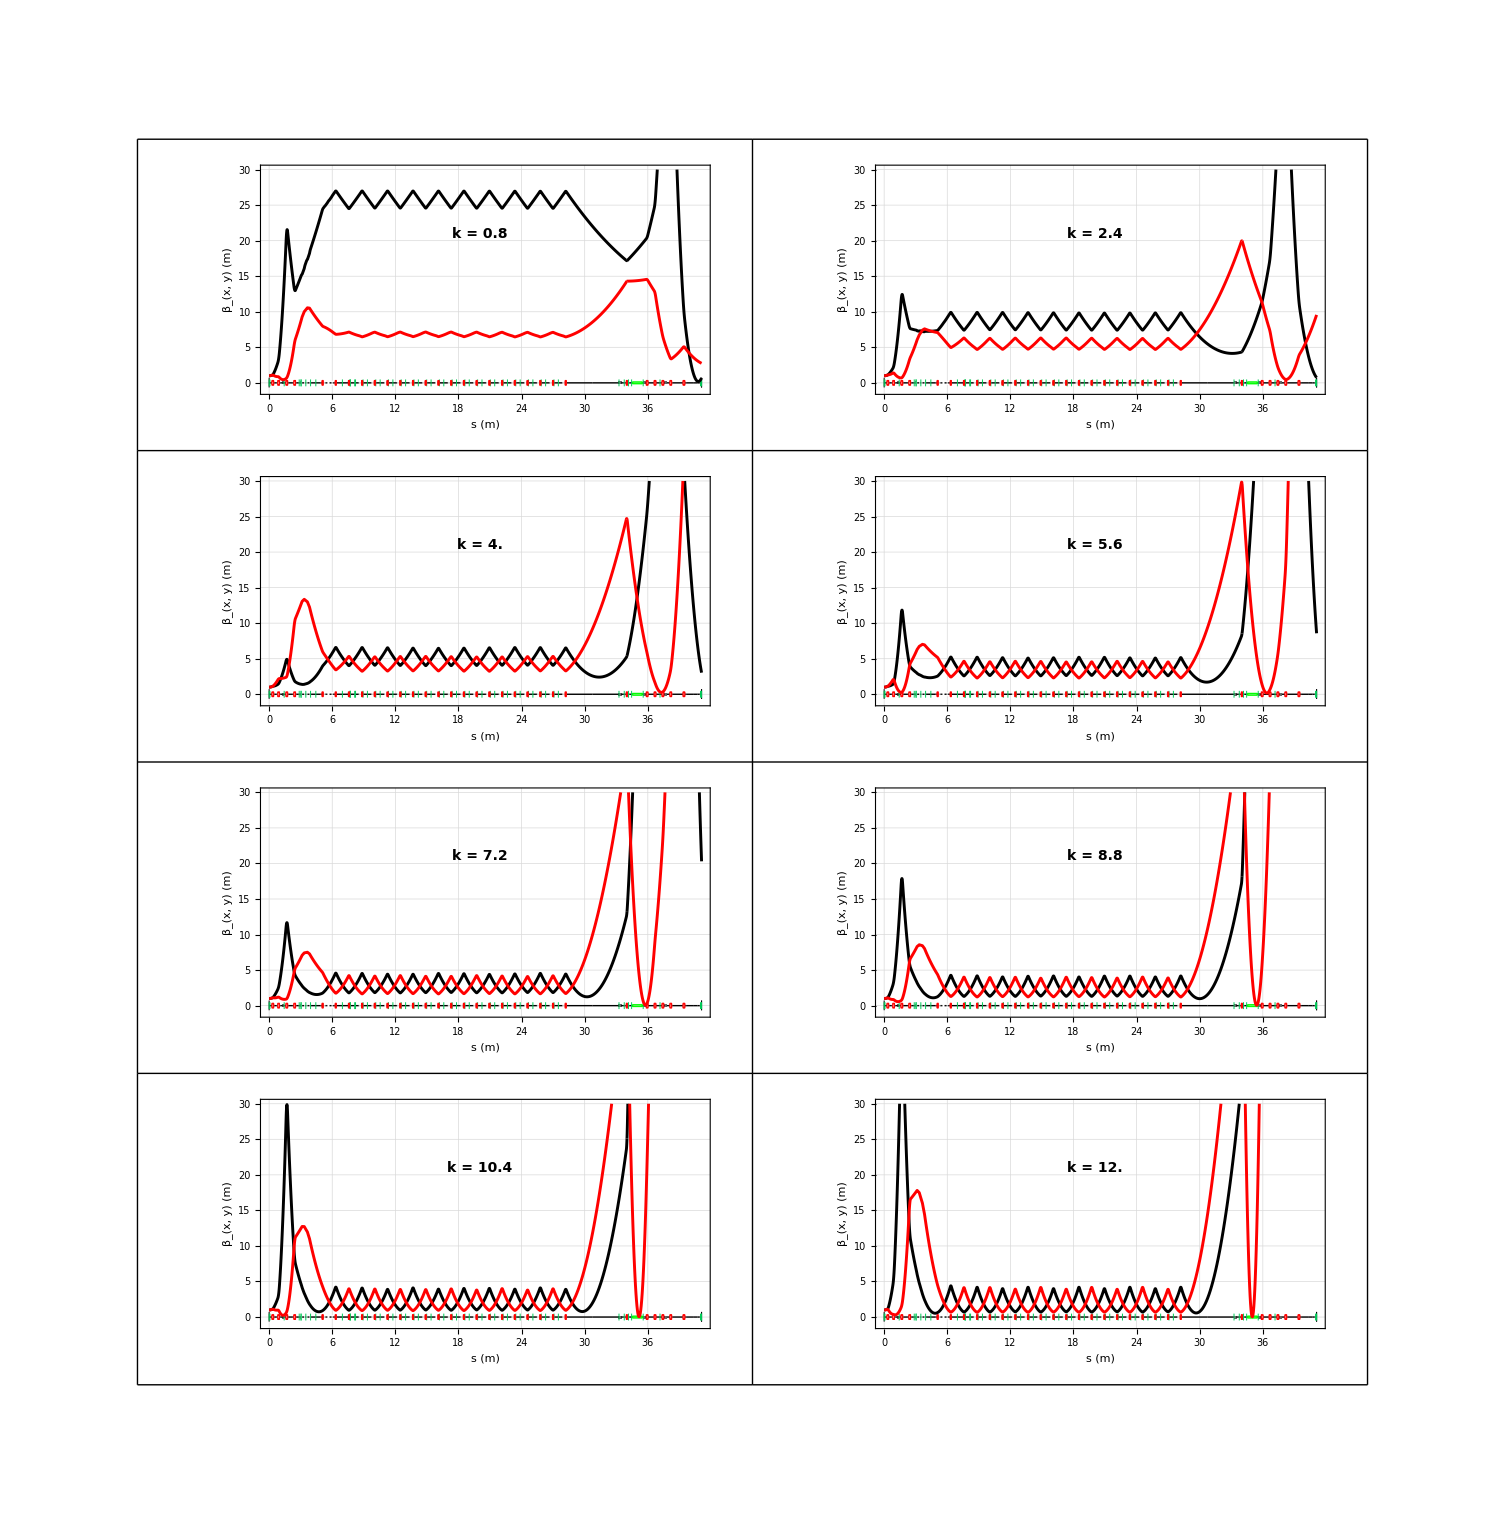

```mathematica
GraphicsGrid[Partition[felmatch⟦4;;-1;;16⟧,2],Frame->All]
```

```mathematica
Export["clara_fel_match2_slc.png",GraphicsGrid[Partition[felmatch⟦4;;-1;;16⟧,2],Frame->All],ImageResolution->150]
```

clara_fel_match2_slc.png

```mathematica
felmatch⟦3;;-1;;4⟧⟦All,1;;-3,2⟧
```

{{-5.371687034095,-8.318589787143,7.708890156658,-3.721748155627,0.67264535758},{-4.866207344242,-6.633576162869,7.292683586832,-3.150150446402,0.169740001524},{-3.712778388593,-7.037245655525,7.340500214172,-2.877415970393,-0.301057786333},{-2.564551944227,-7.97430868434,7.565469017011,-2.816408070954,-0.714847751549},{-1.813811549301,-7.483601239328,7.273491708921,-2.373746478263,-1.025765731882},{-0.500439488731,-6.581749898357,6.651778173035,-1.705791866108,-1.106160502543},{0.898211469628,-6.600479289136,6.539544894772,-1.52230978217,-1.073744055875},{1.02377301398,-3.162453830846,8.302886211709,-3.852170743208,2.008801726432},{1.695303180697,-4.183328793536,8.190541029898,-3.581604399671,1.404687153222},{-0.645860095417,-2.468721013188,7.916483279732,-3.796975124898,1.360994203292},{-0.24545158983,-3.43676060502,7.931747529797,-3.581024772151,0.748890070995},{-0.238399004369,-4.18370988934,7.92084897314,-3.365978788562,0.079853645031},{1.687136920841,-12.813038259172,9.972159145634,-5.365874902901,-1.59185156485},{-0.144729705317,-9.007809596712,8.719489112071,-3.443092854285,-2.514832666739},{0.493271923024,-11.783216537748,9.849946232119,-5.07897599937,-2.057703109713},{-4.818443775206,-2.617183642689,8.206794653563,-4.157637087306,-0.428241200013},{-3.0461871134,-5.364859592825,8.56278283135,-3.819914199452,-1.607637297684},{-2.163755019236,-8.18503616654,9.174958340691,-4.164803981149,-2.428298358535},{-8.505706402978,-2.385368933434,8.802509924693,-5.098060127651,0.565776647284},{-6.75549613509,-4.261189176863,9.029141777713,-4.864995876125,-0.645154477031},{-5.433883296225,-6.487252106941,9.384154525335,-4.840264178529,-1.501332524239},{-11.321341779242,-3.672335479781,9.457123661607,-5.691966919398,2.142287561041},{-3.133355242346,-13.501019499766,10.769448849913,-6.105998741569,-0.476653257396},{-3.423723593148,-14.969606082142,11.028315075033,-6.352805849697,0.480483922715},{-4.558232005586,-13.564847626278,10.831596031202,-6.135355661754,-0.22173434498},{-4.841017511018,-14.803063520946,11.02644402654,-6.304781572877,0.43011957825},{-5.419926226862,-15.169225304812,11.083081082829,-6.332575039758,0.609055163242},{-5.569349568612,-16.719665181668,11.274631218142,-6.47944623098,1.33105584871},{-10.850111758969,-9.521446880962,10.436851229277,-5.909871252606,0.644722869527},{-17.804082382446,-6.025086124787,10.183474746719,-6.197104715949,5.222468051096},{11.673743272914,-8.891652791451,-1.960041009267,7.005070322861,-7.541535768723},{11.871201652606,-7.781381536327,-3.002608985767,7.3180833125,-6.911958136465},{-2.584465811271,3.153712895048,-9.406601894738,7.639722670032,-9.337573547315},{-0.995971280438,1.189359015177,-8.914430773345,7.716013099831,-9.594926610148},{-10.731554035935,-18.346179950535,11.370765167287,-6.182946004228,0.051675448678}}

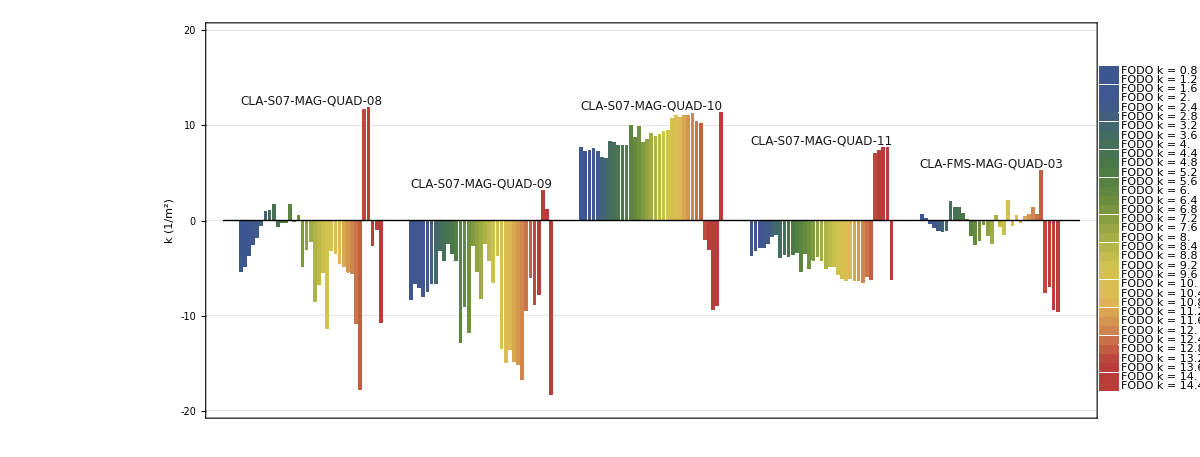

```mathematica
matchplot=ShowLegend[BarChart[Transpose[ToExpression@felmatch⟦3;;-1;;4⟧⟦All,1;;-3,2⟧],ChartLabels->{Table["",{Length[felmatch⟦3,All,1⟧]}],Placed[(Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->12]&/@StringDrop[StringReplace[ToString[#]&/@felmatch⟦3,All,1⟧,{"{"->"","}"->"",", "-> " # ","£"->"-","K"->""}],-1]),{{1,1},{1,-0.1}}],Table["",{Length[felmatch⟦3,All,1⟧]}]},ChartStyle->"DarkRainbow",BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.001],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.5,10},FrameLabel->{{"k (1/m^2)",""},{"",""}},FrameTicks->{{LinTicks[-20,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-20,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,AxesOrigin->{0,0},Axes->True,PlotRange->{All,{-20,20}}],{Transpose[{ColorData["DarkRainbow",#/Length[vals]]&/@Table[i,{i,0,Length[vals]-1}],"FODO k = "<>ToString[#]&/@vals}],LegendPosition->{0.9,-0.35},LegendSize->{0.2,0.7},LegendShadow->None,LegendTextSpace->3}]
```

```mathematica
Export["clara_fel_match3_slc.png",matchplot,ImageResolution->300]
```

clara_fel_match3_slc.png

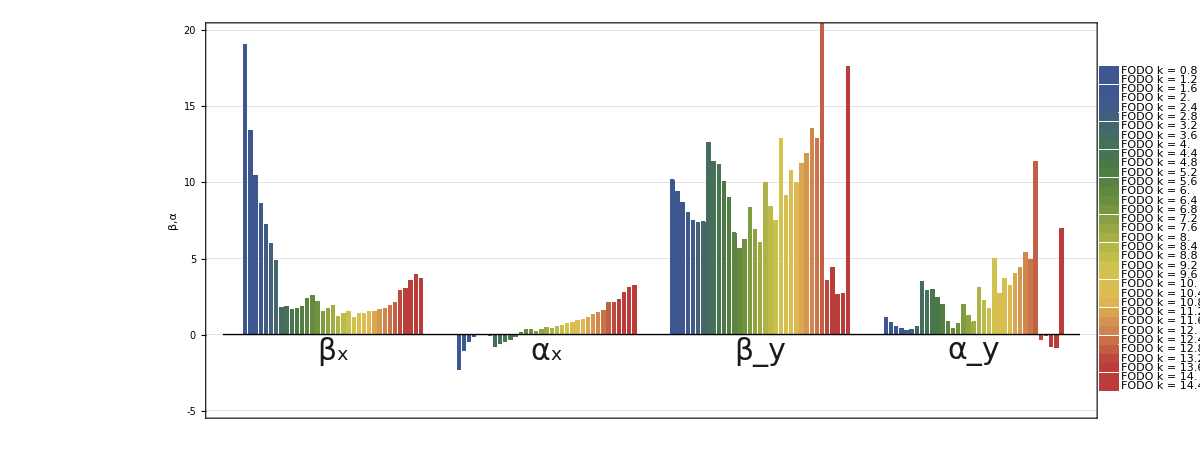

```mathematica
opticsmu1plot=ShowLegend[BarChart[Transpose[felmatch⟦2;;-1;;4⟧⟦All,2;;-1⟧],ChartLabels->{Table["",{Length[felmatch⟦2,2;;-1⟧]}],Placed[(Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->30]&/@{"β_x","α_x","β_y","α_y"}),Axis],Table["",{Length[felmatch⟦2,2;;-1⟧]}]},ChartStyle->"DarkRainbow",BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.001],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.5,10},FrameLabel->{{"β,α",""},{"",""}},FrameTicks->{{LinTicks[-5,30,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-5,30,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,AxesOrigin->{0,0},Axes->True,PlotRange->{All,{-5,20}}],{Transpose[{ColorData["DarkRainbow",#/Length[vals]]&/@Table[i,{i,0,Length[vals]-1}],"FODO k = "<>ToString[#]&/@vals}],LegendPosition->{0.9,-0.35},LegendSize->{0.2,0.7},LegendShadow->None,LegendTextSpace->3}]
```

```mathematica
Export["clara_fel_opticsmu1.png",opticsmu1plot,ImageResolution->300]
```

clara_fel_opticsmu1.png

### FODO with delay chicanes and undulator focusing

```mathematica
LATTICE=MADFlatten[{CLA£FRS}]⟦1;;-22⟧;
```

```mathematica
test=MADFlatten[{CLA£FRS}]⟦1;;50⟧;
```

```mathematica
test2=MADFlatten[{CLA£FRS}]⟦1;;43⟧;
```

```mathematica
MADInfo[test2]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£FRS£APER | Marker | 0 | --- | --- | --- | CLA£FRS£APER | 0
2 | CLA£FRS£R01£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£B | 0.03
3 | CLA£FRS£R01£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£W | 0.03
4 | CLA£FRS£R01£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£A | 0.06
5 | CLA£FRS£R01£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R01£DIA£BPM£01 | 0.06
6 | CLA£FRS£R01£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£UND£B | 0.07
7 | CLA£FRS£R01£MAG£UND£W£H1 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1 | 0.445
8 | CLA£FRS£R01£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R01£MARK£01 | 0.445
9 | CLA£FRS£R01£MAG£UND£W£H2 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H2 | 0.82
10 | CLA£FRS£R01£MAG£UND£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£UND£A | 0.83
11 | CLA£FRS£R01£MAG£DIP£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£01£B | 0.84
12 | CLA£FRS£R01£MAG£DIP£01£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R01£MAG£DIP£01£D | 0.890008
13 | CLA£FRS£R01£MAG£DIP£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£01£A | 0.900008
14 | CLA£FRS£R01£MAG£DIP£02£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£02£B | 0.910008
15 | CLA£FRS£R01£MAG£DIP£02£D | SectorBend | 0.100017 | 0 | --- | 0.0349066 | CLA£FRS£R01£MAG£DIP£02£D | 1.01002
16 | CLA£FRS£R01£MAG£DIP£02£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£02£A | 1.02002
17 | CLA£FRS£R01£MAG£DIP£03£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£03£B | 1.03002
18 | CLA£FRS£R01£MAG£DIP£03£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R01£MAG£DIP£03£D | 1.08003
19 | CLA£FRS£R01£MAG£DIP£03£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£DIP£03£A | 1.09003
20 | CLA£FRS£R01£MAG£QUAD£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£QUAD£01£B | 1.10003
21 | CLA£FRS£R01£MAG£QUAD£01£K | Quadrupole | 0.1 | -1. | --- | --- | CLA£FRS£R01£MAG£QUAD£01£K | 1.20003
22 | CLA£FRS£R01£MAG£QUAD£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£QUAD£01£A | 1.21003
23 | CLA£FRS£R02£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£B | 1.24003
24 | CLA£FRS£R02£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£W | 1.24003
25 | CLA£FRS£R02£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R02£DIA£SCR£01£A | 1.27003
26 | CLA£FRS£R02£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R02£DIA£BPM£01 | 1.27003
27 | CLA£FRS£R02£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£UND£B | 1.28003
28 | CLA£FRS£R02£MAG£UND£W£H1 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R02£MAG£UND£W£H1 | 1.65503
29 | CLA£FRS£R02£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R02£MARK£01 | 1.65503
30 | CLA£FRS£R02£MAG£UND£W£H2 | Drift | 0.375 | --- | --- | --- | CLA£FRS£R02£MAG£UND£W£H2 | 2.03003
31 | CLA£FRS£R02£MAG£UND£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£UND£A | 2.04003
32 | CLA£FRS£R02£MAG£DIP£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£01£B | 2.05003
33 | CLA£FRS£R02£MAG£DIP£01£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R02£MAG£DIP£01£D | 2.10004
34 | CLA£FRS£R02£MAG£DIP£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£01£A | 2.11004
35 | CLA£FRS£R02£MAG£DIP£02£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£02£B | 2.12004
36 | CLA£FRS£R02£MAG£DIP£02£D | SectorBend | 0.100017 | 0 | --- | 0.0349066 | CLA£FRS£R02£MAG£DIP£02£D | 2.22006
37 | CLA£FRS£R02£MAG£DIP£02£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£02£A | 2.23006
38 | CLA£FRS£R02£MAG£DIP£03£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£03£B | 2.24006
39 | CLA£FRS£R02£MAG£DIP£03£D | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | CLA£FRS£R02£MAG£DIP£03£D | 2.29007
40 | CLA£FRS£R02£MAG£DIP£03£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£DIP£03£A | 2.30007
41 | CLA£FRS£R02£MAG£QUAD£01£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£QUAD£01£B | 2.31007
42 | CLA£FRS£R02£MAG£QUAD£01£K | Quadrupole | 0.1 | -1. | --- | --- | CLA£FRS£R02£MAG£QUAD£01£K | 2.41007
43 | CLA£FRS£R02£MAG£QUAD£01£A | Drift | 0.01 | --- | --- | --- | CLA£FRS£R02£MAG£QUAD£01£A | 2.42007

Total Length = 2.42007 m

```mathematica
Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[2,1,1]]-Select[MADPositions[MADFlatten[LATTICE]],#[[2,1]]=="quadrupole"&][[1,1,1]]
```

1.21002

So structure of CLARA FODO is

Remember to get the edge angles right - they are rectangular

```mathematica
marker[M11D0CMS]
marker[M11D0CME]
sbend[M11D0CB1,0.0500083,0,-0.0174533,"M11D0CB1",E2->-0.0174533]
drift[M11D0CBD,0.02,"M11D0CBD"]
sbend[M11D0CB2,0.100017,0,0.0349066,"M11D0CB2",E1->0.0174533,E2->0.0174533]
sbend[M11D0CB3,0.0500083,0,-0.0174533,"M11D0CB3",E1->-0.0174533]
drift[M11D0CD1H2,(1.21002-0.1)/2,"M11D0CD1H2",k-> 1.25,poles->34,tilt->-π/2//N]
drift[M11D0CD2H1,0.85/2,"M11D0CD2",k-> 1.25,poles->26,tilt->-π/2//N]
drift[M11D0CD2H2,0.85/2,"M11D0CD2",k-> 1.25,poles->26,tilt->-π/2//N]
drift[M11D0CD1H1,(1.21002-0.1)/2-0.26002,"M11D0CD1H1",k-> 1.25,poles->18,tilt->-π/2//N]
quad[M11D0CQ1,0.10,6,"M11D0CQ1"]
quad[M11D0CQ2,0.10,-6,"M11D0CQ2"]
line[M11D0RC,{M11D0CMS,M11D0CD1H1,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ1,M11D0CD2H1,M11D0CD2H2,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ2,M11D0CD1H2,M11D0CME}]
```

```mathematica
M11D0CD1H1Extra
```

{M11D0CD1H1,Extra,1.25,18,-1.5708}

```mathematica
MADInfo[M11D0RC]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | M11D0CMS | Marker | 0 | --- | --- | --- |  | 0
2 | M11D0CD1H1 | Drift | 0.29499 | --- | --- | --- | M11D0CD1H1 | 0.29499
3 | M11D0CB1 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB1 | 0.344998
4 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 0.364998
5 | M11D0CB2 | SectorBend | 0.100017 | 0 | --- | 0.0349066 | M11D0CB2 | 0.465015
6 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 0.485015
7 | M11D0CB3 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB3 | 0.535024
8 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 0.555024
9 | M11D0CQ1 | Quadrupole | 0.1 | 6 | --- | --- | M11D0CQ1 | 0.655024
10 | M11D0CD2H1 | Drift | 0.425 | --- | --- | --- | M11D0CD2 | 1.08002
11 | M11D0CD2H2 | Drift | 0.425 | --- | --- | --- | M11D0CD2 | 1.50502
12 | M11D0CB1 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB1 | 1.55503
13 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 1.57503
14 | M11D0CB2 | SectorBend | 0.100017 | 0 | --- | 0.0349066 | M11D0CB2 | 1.67505
15 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 1.69505
16 | M11D0CB3 | SectorBend | 0.0500083 | 0 | --- | -0.0174533 | M11D0CB3 | 1.74506
17 | M11D0CBD | Drift | 0.02 | --- | --- | --- | M11D0CBD | 1.76506
18 | M11D0CQ2 | Quadrupole | 0.1 | -6 | --- | --- | M11D0CQ2 | 1.86506
19 | M11D0CD1H2 | Drift | 0.55501 | --- | --- | --- | M11D0CD1H2 | 2.42007
20 | M11D0CME | Marker | 0 | --- | --- | --- |  | 2.42007

Total Length = 2.42007 m

add the undulators

```mathematica
(*We always need half poles at both ends of an undulator. But what to do about the "half undulators"? 
Neil specified number of periods, so number of poles is always even*)
Block[{lambda,diplength,drilength,dipangle,b0,gamma,pout=0,tilt},
(lambda=2 #⟦3⟧/(ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]);
diplength=lambda/4;
drilength=(lambda-2 diplength)/2;
tilt=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦5⟧]];
b0=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦3⟧]]/(93.4 lambda);
pcen=470;
dipangle= Evaluate[299.8 b0 diplength/pcen];
Clear[Evaluate[# ⟦1⟧<> "£EXP"]];
Clear[EXPLINE];
EXPLINE={};
(*For a first half undulator*)
If[StringMatchQ[#⟦1⟧,"*H1*"],
(*half bend at start*)
sbend[Evaluate[# ⟦1⟧<> "£HS"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HS"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HS"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HS"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HS"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
(*drift at start*)
drift[Evaluate[# ⟦1⟧<> "£HSD"],drilength,ToString[# ⟦1⟧<> "£HSD"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HSD"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£HSD"<>","<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£HSD"]<>"]"]];
(*periodic part*)
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle,E2->-dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle]]<>",E2→"<>ToString[FortranForm[-dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle,E2->dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle]]<>",E2→"<>ToString[FortranForm[dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->-dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
]
(*For a second half undulator*)
If[StringMatchQ[#⟦1⟧,"*H2*"],
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->-dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
drift[Evaluate[# ⟦1⟧<> "£DM"],drilength,ToString[# ⟦1⟧<> "£DM"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£DM"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£DM,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£DM"]<>"]"]];
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i+ IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle,E2->-dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle]]<>",E2→"<>ToString[FortranForm[-dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle,E2->dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle]]<>",E2→"<>ToString[FortranForm[dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
sbend[Evaluate[# ⟦1⟧<> "£HE"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HE"],E1->dipangle/2,E2->0.0 ,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HE"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HE"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HE"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];];
line[Evaluate[# ⟦1⟧<> "£EXP"],EXPLINE]
)
&/@Select[MADFlatten[M11D0RC],StringMatchQ[#⟦1⟧,"*M11D0CD*"]&]⟦1;;-1⟧];
```

```mathematica
Select[MADFlatten[M11D0RC],StringMatchQ[#⟦1⟧,"*M11D0CD*"]&]⟦1;;-1⟧
```

{{M11D0CD1H1,Drift,0.29499,---,---,---,M11D0CD1H1},{M11D0CD2H1,Drift,0.425,---,---,---,M11D0CD2},{M11D0CD2H2,Drift,0.425,---,---,---,M11D0CD2},{M11D0CD1H2,Drift,0.55501,---,---,---,M11D0CD1H2}}

```mathematica
Clear[M11D0RCMADWIG];
M11D0RCMADWIG=MADFlatten[ReplacePart[MADFlatten[M11D0RC],First[Flatten[Position[MADFlatten[M11D0RC],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[M11D0RC],StringMatchQ[#⟦1⟧,"*M11D0CD*"]&]]];
```

```mathematica
MADWrite["M11D0R",M11D0RCMADWIG];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g M11D0R.mff",Word]];
MADStringWrite["M11D0R","eopt,add;\n"];
MADStringWrite["M11D0R","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.135]<>";\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.1\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.2\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.3\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.4\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.5\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.6\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.7\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.8\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.9\n"];
MADStringWrite["M11D0R","select,twiss,full;\ntwiss,tape=twiss.txt;\n"];
MADStringWrite["M11D0R","select,optics,full;\noptics,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat M11D0R.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < M11D0R.mff > M11D0R_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < M11D0R.mff > M11D0R.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->True];
Select[ReadList["M11D0R.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&];
```

{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}

Variables (re-)assigned: {GAMTR,ALFA,XIY,XIX,QY,QX,CIRCUM,DELTA,TYPE,COMMENT,ORIGIN,DATE,TIME}

Variables (re-)assigned: {NAME,S,BETX,BETY,DX,ALFX,ALFY,MUX,MUY,DPX,DY,DPY}

```mathematica
MatchTwiss=First[#]&/@{BETX,ALFX,BETY,ALFY}
```

{2.77408,-0.907172,3.48236,1.09671}

```mathematica
ToString[NumberForm[MADLength[M11D0RC],3]]
```

2.42

```mathematica
ToString[NumberForm[MADLength[M11D0RCMADWIG],3]]
```

2.42

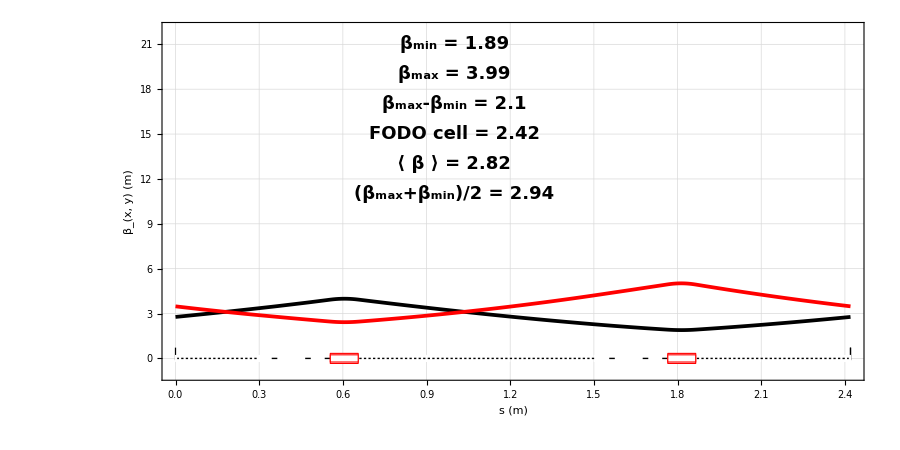

done

```mathematica
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{0.3,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["β_min = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,21}],
Text[Style["β_max = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,19}],
Text[Style["β_max-β_min = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,17}],
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RCMADWIG],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,15}],
Text[Style[ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,13}],
Text[Style["(β_max+β_min)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->18],{1,11}]},Prolog->MADDraw[Select[MADFlatten[M11D0RCMADWIG], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,22}},ImageSize->900,AspectRatio->0.5];
(*{Show[#],Export["output/run_B_pw01_twiss_mma.png",#,ImageResolution->400],Export["output/run_B_pw01_twiss_mma.eps",#,ImageSize->900,ImageResolution->200]}&@*)ShowLegend[plt,lgd]
Print["done"]
```

scan over k -values

```mathematica
vals=Table[i,{i,1.2,16,0.4}];
```

When i introduce the undulator focusing there is no longer any solution at k = 0.8 or 1.2 or 2, 2.4,2.8, so rescale starting from 3.2. When i change the orientation of the poles from horizontal to vertical i recover

```mathematica
vals
```

{1.2,1.6,2.,2.4,2.8,3.2,3.6,4.,4.4,4.8,5.2,5.6,6.,6.4,6.8,7.2,7.6,8.,8.4,8.8,9.2,9.6,10.,10.4,10.8,11.2,11.6,12.,12.4,12.8,13.2,13.6,14.,14.4,14.8,15.2,15.6,16.}

```mathematica
vals2=(1/((M11D0CQ1⟦1,3⟧/2)#) 1/(MADLength[M11D0RC]/2))&[vals]
```

{13.7737,10.3303,8.26423,6.88686,5.90302,5.16515,4.59124,4.13212,3.75647,3.44343,3.17855,2.95151,2.75474,2.58257,2.43066,2.29562,2.1748,2.06606,1.96767,1.87823,1.79657,1.72172,1.65285,1.58928,1.53041,1.47576,1.42487,1.37737,1.33294,1.29129,1.25216,1.21533,1.1806,1.14781,1.11679,1.0874,1.05952,1.03303}

```mathematica
betavs=Reap[(
marker[M11D0CMS]
marker[M11D0CME]
sbend[M11D0CB1,0.0500083,0,-0.0174533,"M11D0CB1",E2->-0.0174533]
drift[M11D0CBD,0.02,"M11D0CBD"]
sbend[M11D0CB2,0.100017,0,0.0349066,"M11D0CB2",E1->0.0174533,E2->0.0174533]
sbend[M11D0CB3,0.0500083,0,-0.0174533,"M11D0CB3",E1->-0.0174533]
drift[M11D0CD1H2,(1.21002-0.1)/2,"M11D0CD1H2",k-> 1.25,poles->34,tilt->-π/2//N]
drift[M11D0CD2H1,0.85/2,"M11D0CD2",k-> 1.25,poles->26,tilt->-π/2//N]
drift[M11D0CD2H2,0.85/2,"M11D0CD2",k-> 1.25,poles->26,tilt->-π/2//N]
drift[M11D0CD1H1,(1.21002-0.1)/2-0.26002,"M11D0CD1H1",k-> 1.25,poles->18,tilt->-π/2//N]
quad[M11D0CQ1,0.10,#,"M11D0CQ1"]
quad[M11D0CQ2,0.10,-#,"M11D0CQ2"]
line[M11D0RC,Table[{M11D0CMS,M11D0CD1H1,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ1,M11D0CD2H1,M11D0CD2H2,M11D0CB1,M11D0CBD,M11D0CB2,M11D0CBD,M11D0CB3,M11D0CBD,M11D0CQ2,M11D0CD1H2,M11D0CME},1]]
(*We always need half poles at both ends of an undulator. But what to do about the "half undulators"? 
Neil specified number of periods, so number of poles is always even*)
Block[{lambda,diplength,drilength,dipangle,b0,gamma,pout=0,tilt},
(lambda=2 #⟦3⟧/(ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]);
diplength=lambda/4;
drilength=(lambda-2 diplength)/2;
tilt=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦5⟧]];
b0=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦3⟧]]/(93.4 lambda);
pcen=470;
dipangle= Evaluate[299.8 b0 diplength/pcen];
Clear[Evaluate[# ⟦1⟧<> "£EXP"]];
Clear[EXPLINE];
EXPLINE={};
(*For a first half undulator*)
If[StringMatchQ[#⟦1⟧,"*H1*"],
(*half bend at start*)
sbend[Evaluate[# ⟦1⟧<> "£HS"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HS"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HS"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HS"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HS"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
(*drift at start*)
drift[Evaluate[# ⟦1⟧<> "£HSD"],drilength,ToString[# ⟦1⟧<> "£HSD"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HSD"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£HSD"<>","<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£HSD"]<>"]"]];
(*periodic part*)
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle,E2->-dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle]]<>",E2→"<>ToString[FortranForm[-dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle,E2->dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle]]<>",E2→"<>ToString[FortranForm[dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->-dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
]
(*For a second half undulator*)
If[StringMatchQ[#⟦1⟧,"*H2*"],
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->-dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
drift[Evaluate[# ⟦1⟧<> "£DM"],drilength,ToString[# ⟦1⟧<> "£DM"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£DM"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£DM,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£DM"]<>"]"]];
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i+ IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle,E2->-dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle]]<>",E2→"<>ToString[FortranForm[-dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle,E2->dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle]]<>",E2→"<>ToString[FortranForm[dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
sbend[Evaluate[# ⟦1⟧<> "£HE"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HE"],E1->dipangle/2,E2->0.0 ,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HE"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HE"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HE"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];];
line[Evaluate[# ⟦1⟧<> "£EXP"],EXPLINE]
)
&/@Select[MADFlatten[M11D0RC],StringMatchQ[#⟦1⟧,"*M11D0CD*"]&]⟦1;;-1⟧];

Clear[M11D0RCMADWIG];
M11D0RCMADWIG=MADFlatten[ReplacePart[MADFlatten[M11D0RC],First[Flatten[Position[MADFlatten[M11D0RC],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[M11D0RC],StringMatchQ[#⟦1⟧,"*M11D0CD*"]&]]];

MADWrite["M11D0R",M11D0RCMADWIG];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g M11D0R.mff",Word]];
MADStringWrite["M11D0R","eopt,add;\n"];
	MADStringWrite["M11D0R","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.05\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.10\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.15\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.20\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.25\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.30\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.35\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.40\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.45\n"];
MADStringWrite["M11D0R","split,name=b1,fraction=0.50\n"];
MADStringWrite["M11D0R","split,name=b2,fraction=0.55\n"];
MADStringWrite["M11D0R","split,name=b3,fraction=0.60\n"];
MADStringWrite["M11D0R","split,name=b4,fraction=0.65\n"];
MADStringWrite["M11D0R","split,name=b5,fraction=0.70\n"];
MADStringWrite["M11D0R","split,name=b6,fraction=0.75\n"];
MADStringWrite["M11D0R","split,name=b7,fraction=0.80\n"];
MADStringWrite["M11D0R","split,name=b8,fraction=0.85\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.90\n"];
MADStringWrite["M11D0R","split,name=b9,fraction=0.95\n"];
MADStringWrite["M11D0R","select,twiss,full;\ntwiss,tape=twiss.txt;\n"];
MADStringWrite["M11D0R","select,optics,full;\noptics,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat M11D0R.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < M11D0R.mff > M11D0R_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < M11D0R.mff > M11D0R.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
(*Print[Select[ReadList["M11D0R.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&]];*)
Sow[{Mean[BETX],Mean[BETY]}];
Sow[First[#]&/@{BETX,ALFX,BETY,ALFY}];
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["k = "<>ToString[#],FontFamily->"Helvetica",Bold,FontSize->14],{1.3,21}],
Text[Style["FODO cell = "<>ToString[NumberForm[MADLength[M11D0RCMADWIG],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.3,19}],
Text[Style["β_xmin = "<>ToString[NumberForm[Min[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,17}],
Text[Style["β_xmax = "<>ToString[NumberForm[Max[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,15}],
Text[Style["β_xmax-β_xmin = "<>ToString[NumberForm[(Max[BETX]-Min[BETX]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,13}],
Text[Style[ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Mean[BETX],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,11}],
Text[Style["(β_xmax+β_xmin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETX])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{1,9}],
Text[Style["β_ymin = "<>ToString[NumberForm[Min[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,17}],
Text[Style["β_ymax = "<>ToString[NumberForm[Max[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,15}],
Text[Style["β_ymax-β_ymin = "<>ToString[NumberForm[(Max[BETY]-Min[BETY]),3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,13}],
Text[Style[ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Mean[BETY],3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,11}],
Text[Style["(β_ymax+β_ymin)/2 = "<>ToString[NumberForm[(Max[BETX]+Min[BETY])/2,3]],FontFamily->"Helvetica",Bold,FontSize->14],{1.8,9}]},Prolog->MADDraw[Select[MADFlatten[M11D0RCMADWIG], #[[3]] >  0 &][[1 ;; -1]],Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,30}},ImageSize->700,AspectRatio->0.5];
Sow[Show[plt]];

)&/@vals]⟦2,1⟧;
```

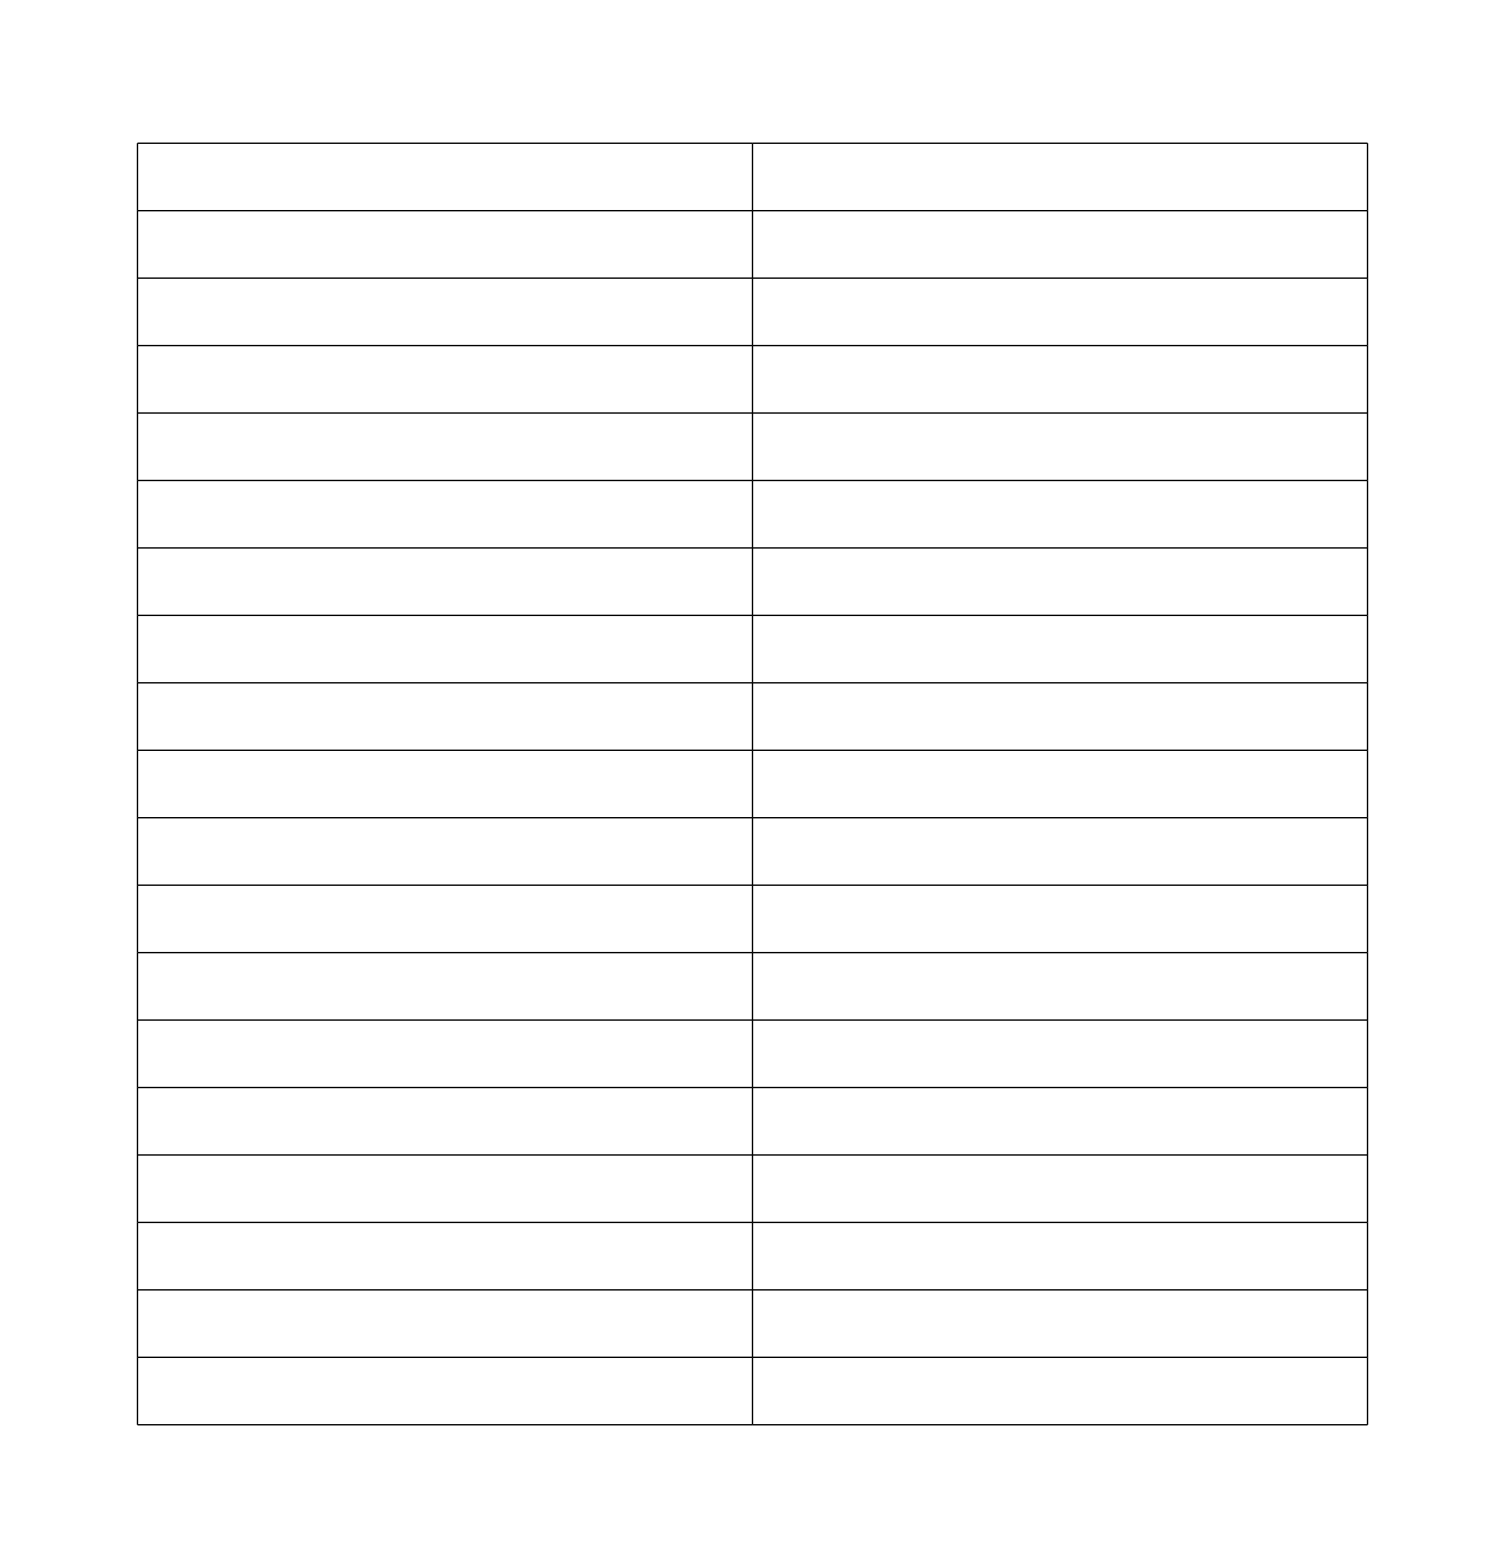
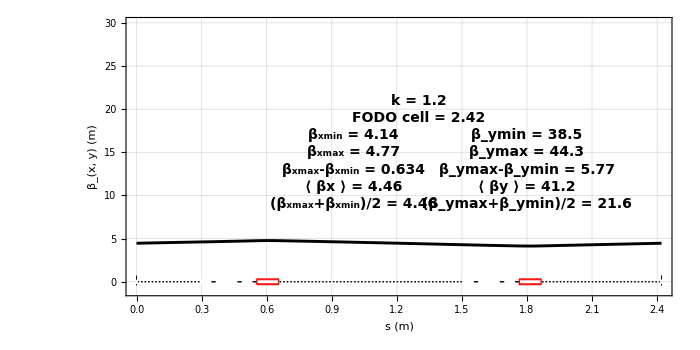
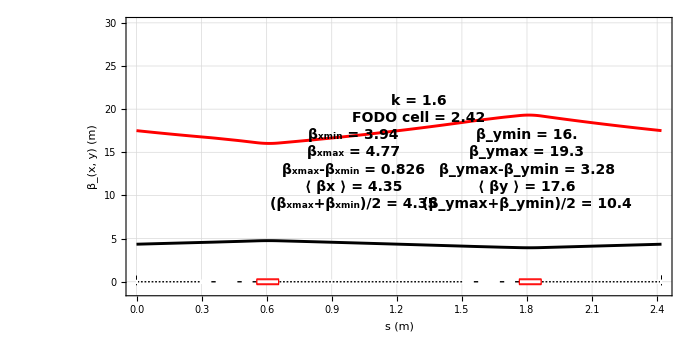
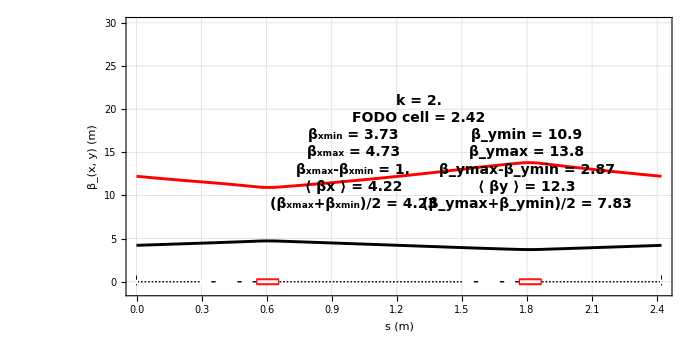
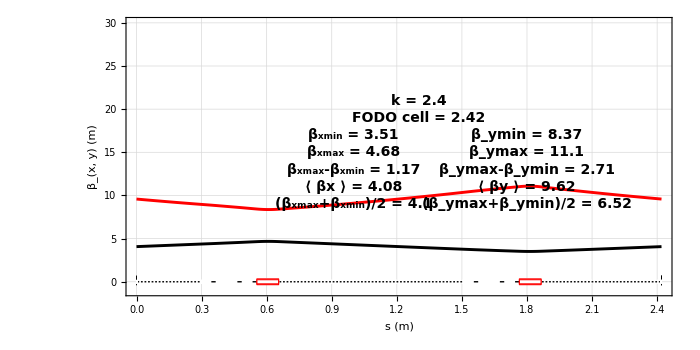
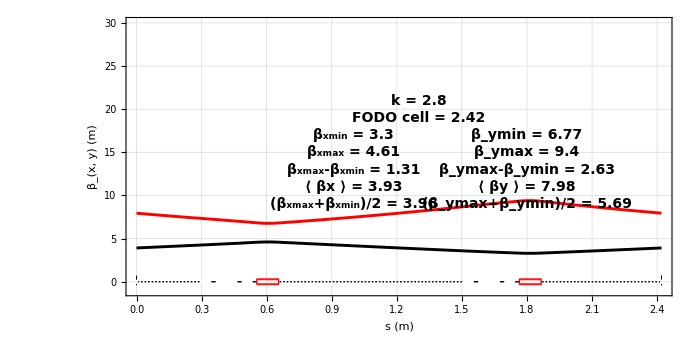
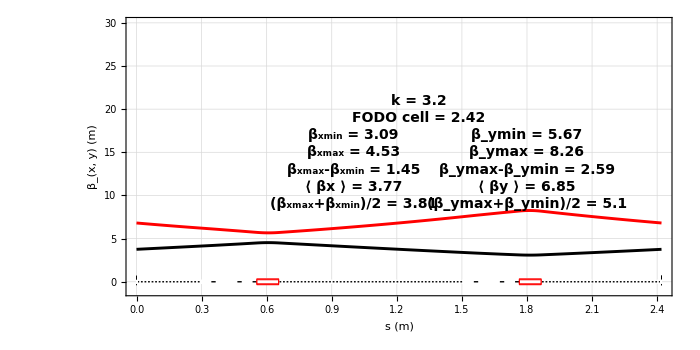
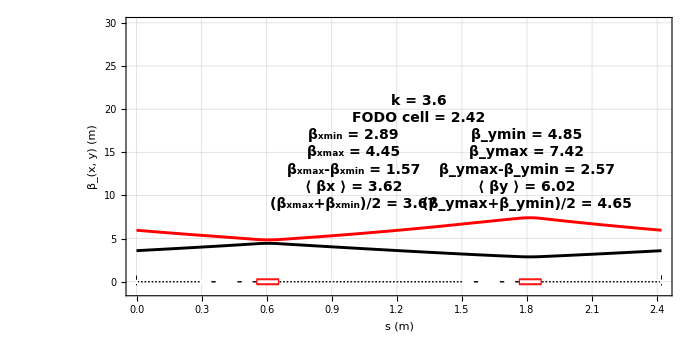

```mathematica
GraphicsGrid[Partition[betavs⟦3;;-1;;3⟧,2],Frame->All]
```

```mathematica
(*Export["clara_fel_match2_und.png",GraphicsGrid[Partition[betavs⟦3;;-1;;12⟧,2],Frame->All],ImageResolution->150]*)
```

```mathematica
Take[betavs,{1,-1,3}]
```

{{4.46201,41.1981},{4.3523,17.5553},{4.2228,12.2616},{4.07969,9.62143},{3.92864,7.98345},{3.77441,6.85132},{3.62078,6.01588},{3.47058,5.37148},{3.32577,4.85824},{3.18763,4.43939},{3.0569,4.09097},{2.93396,3.79668},{2.81889,3.54497},{2.71159,3.32745},{2.61184,3.13787},{2.51937,2.97147},{2.43387,2.82459},{2.35503,2.69434},{2.28255,2.57845},{2.21616,2.47513},{2.15566,2.38292},{2.10086,2.30069},{2.05167,2.22754},{2.00804,2.16278},{1.97004,2.10592},{1.93784,2.05665},{1.91176,2.01485},{1.89228,1.9806},{1.88017,1.95422},{1.87656,1.93633},{1.88314,1.928},{1.90244,1.93087},{1.93846,1.94754},{1.99773,1.98217},{2.09176,2.0417},{2.24294,2.13852},{2.50227,2.2972},{3.02214,2.57514}}

```mathematica
Min[Take[betavs,{7,-1,3}]]
```

1.87656

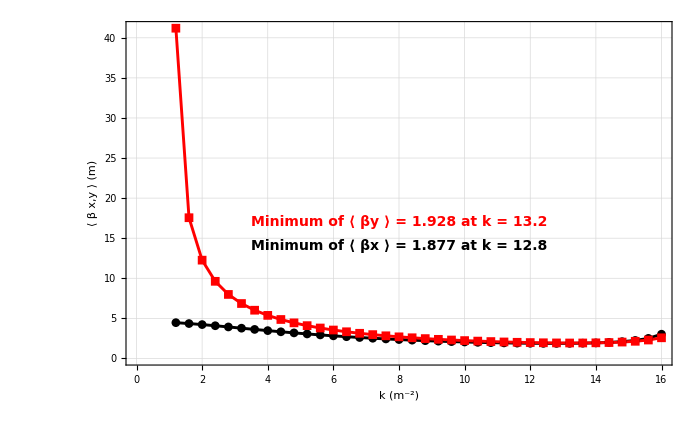

```mathematica
plt1=ListLinePlot[{Transpose[{vals,Take[betavs,{1,-3,3}]⟦All,1⟧}],Transpose[{vals,Take[betavs,{1,-3,3}]⟦All,2⟧}]},Epilog->{Text[Style["Minimum of "<>ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-3,3}]⟦All,1⟧],4]]<>" at k = "<>ToString[vals[[Position[#,Min[#]]&[Take[betavs,{1,-3,3}]⟦All,1⟧]⟦1,1⟧]]],FontFamily->"Helvetica",Bold,FontSize->14],{8,14}],Text[Style["Minimum of "<>ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-3,3}]⟦All,2⟧],4]]<>" at k = "<>ToString[vals[[Position[#,Min[#]]&[Take[betavs,{1,-3,3}]⟦All,2⟧]⟦1,1⟧]]],FontFamily->"Helvetica",Bold,Red,FontSize->14],{8,17}]},PlotMarkers->Automatic,Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{ToString[AngleBracket["β x,y"]]<>" (m)",""},{"k (m^-2)",""}},GridLines->Automatic,PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]}},LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->700,PlotRange->{{0,QuantityMagnitude[Last[vals]]},All}]
```

```mathematica
(*Export["clara_frs_fodo_kscan2_und.png",plt1,ImageResolution->200]*)
```

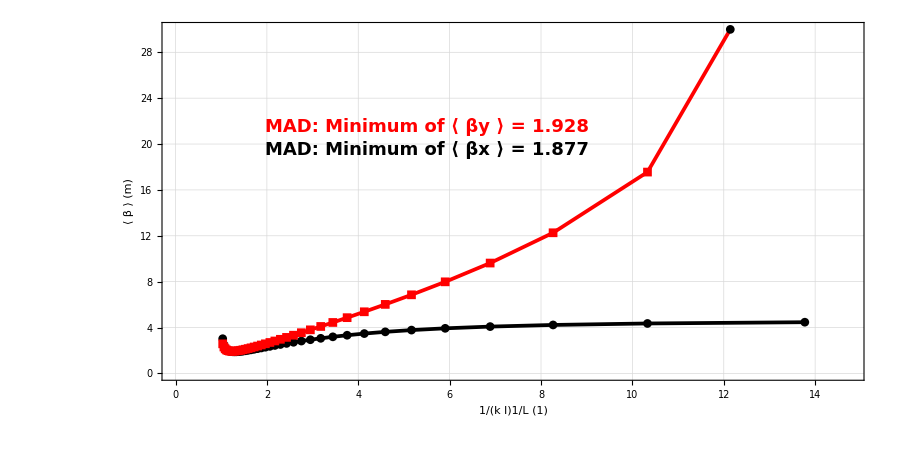

```mathematica
plt2=ListLinePlot[{Transpose[{vals2,Take[betavs,{1,-1,3}]⟦All,1⟧}],Transpose[{vals2,Take[betavs,{1,-1,3}]⟦All,2⟧}]},Epilog->{Text[Style["MAD: Minimum of "<>ToString[AngleBracket["βx"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-1,3}]⟦All,1⟧],4]],FontFamily->"Helvetica",Bold,Black,FontSize->18],{5.5,19.5}],Text[Style["MAD: Minimum of "<>ToString[AngleBracket["βy"]]<>" = "<>ToString[NumberForm[Min[Take[betavs,{1,-1,3}]⟦All,2⟧],4]],FontFamily->"Helvetica",Bold,Red,FontSize->18],{5.5,21.5}]},PlotMarkers->Automatic,Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{ToString[AngleBracket["β"]]<>" (m)",""},{"1/(k l)1/L (1)",""}},GridLines->Automatic,PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]}},LabelStyle->{FontSize->24,Black,Bold,FontFamily->"Helvetica"},ImagePadding->150,ImageSize->900,AspectRatio->0.5,PlotRange->{{0,QuantityMagnitude[First[vals2]]+1},{0,30}}]
```

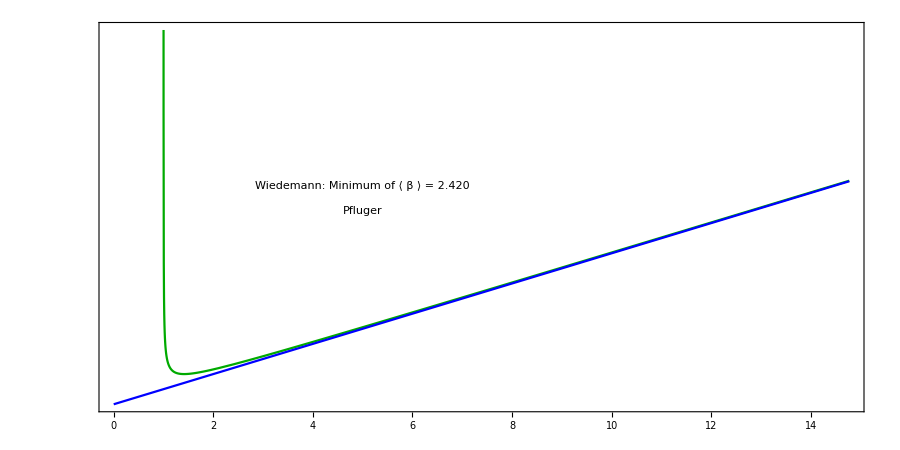

```mathematica
plt3=Plot[{(MADLength[M11D0RC]/2 )x^2(x^2-1)^(-1/2),(MADLength[M11D0RC]/2 )x},{x,0,QuantityMagnitude[First[vals2]]+1},Frame->{False,False,False,True},Epilog->{Style[Text["Wiedemann: Minimum of "<>ToString[AngleBracket["β"]]<>" = "<>ToString[NumberForm[FindMinimum[(MADLength[M11D0RC]/2 )x^2(x^2-1)^(-1/2),{x,1.1}]⟦1⟧,{3,3}]],{5.,17.5}],Darker[Green],Bold,FontSize->18],Style[Text["Pfluger",{5,15.5}],Blue,Bold,FontSize->18]},PlotStyle->{Darker[Green],Blue},FrameTicks->{{None,None},{Automatic,None}},LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},PlotRange->{{0,QuantityMagnitude[First[vals2]]+1},{0,30}},ImagePadding->150,AspectRatio->0.5,ImageSize->900]
```

```mathematica
plt4=Overlay[{plt2,plt3}]
```

-Graphics--Graphics-

```mathematica
(*Export["clara_frs_fodo_ipac.png",plt4,ImageResolution->200]*)
```

```mathematica
FodoTwiss=Transpose[{vals,betavs⟦2;;-1;;3⟧}]
```

```mathematica
FodoTwiss={{1.2,{4.46328506126,-0.264188446198,41.1160809078,2.26217852192}},{1.6,{4.35124591235,-0.348223749159,17.5114414186,1.31813363637}},{2.,{4.21895086956,-0.426131629245,12.2230268256,1.16922771913}},{2.4000000000000004,{4.07266269467,-0.497494324173,9.58366262258,1.11370630333}},{2.8,{3.91810870743,-0.562314435997,7.94474550107,1.08812085968}},{3.2,{3.76012989779,-0.620907349499,6.81079605857,1.07577093405}},{3.6000000000000005,{3.60255501434,-0.673791734356,5.97300720937,1.07045747935}},{4.,{3.44823404453,-0.72159646765,5.32588924655,1.06941388729}},{4.4,{3.29916160819,-0.764991064612,4.80964995255,1.07125611901}},{4.8,{3.15663569149,-0.804639202225,4.38757376749,1.07523967586}},{5.2,{3.02141673492,-0.841171280228,4.03574199652,1.08094769197}},{5.6000000000000005,{2.89386875425,-0.875171018387,3.73784655317,1.08814562118}},{6.000000000000001,{2.77407559434,-0.907171569376,3.4823590008,1.09670817021}},{6.4,{2.66193204592,-0.937657635401,3.26088700786,1.10658050475}},{6.800000000000001,{2.55721276516,-0.967071122701,3.06717166845,1.11775697498}},{7.2,{2.45962305597,-0.995818746469,2.89645038819,1.13026942698}},{7.6000000000000005,{2.36883558644,-1.02428066439,2.74503811226,1.14418114239}},{8.,{2.28451663207,-1.05281969656,2.61004416152,1.15958437369}},{8.4,{2.20634481766,-1.08179103289,2.48917620807,1.1766004429}},{8.8,{2.13402474142,-1.11155258876,2.38060198754,1.19538193951}},{9.2,{2.06729738606,-1.14247639374,2.28285039273,1.21611691949}},{9.6,{2.0059488814,-1.17496163217,2.19474024009,1.23903529289}},{10.,{1.9498189926,-1.20945024957,2.11532915544,1.26441786817}},{10.4,{1.89881068301,-1.24644645906,2.04387774456,1.29260885999}},{10.8,{1.85290227448,-1.28654212793,1.97982611542,1.32403313661}},{11.2,{1.81216417957,-1.33045106153,1.92278129911,1.35922019128}},{11.6,{1.77678306248,-1.37905692594,1.87251547858,1.39883794741}},{12.,{1.74709791045,-1.43348251936,1.82897648456,1.44374137196}},{12.4,{1.72365548724,-1.4951934084,1.79231417939,1.495044081}},{12.8,{1.70729830225,-1.56615885222,1.76292985693,1.55422687383}},{13.2,{1.69930944571,-1.64911240419,1.7415621065,1.62330792276}},{13.6,{1.70166220054,-1.74799523188,1.72943491608,1.70512068067}},{14.,{1.71747557835,-1.86875658914,1.72851967631,1.80379047348}},{14.4,{1.75190872385,-2.02091105104,1.74202164526,1.92560269569}},{14.8,{1.81409396927,-2.22087586087,1.77534892785,2.08070984819}},{15.2,{1.92190248916,-2.50013223047,1.83823914213,2.28684062796}},{15.6,{2.11619868539,-2.92943883388,1.95010733646,2.57854579657}},{16.,{2.5196002329,-3.71779830502,2.15652385607,3.03544797693}}}
```

{{1.2,{4.46329,-0.264188,41.1161,2.26218}},{1.6,{4.35125,-0.348224,17.5114,1.31813}},{2.,{4.21895,-0.426132,12.223,1.16923}},{2.4,{4.07266,-0.497494,9.58366,1.11371}},{2.8,{3.91811,-0.562314,7.94475,1.08812}},{3.2,{3.76013,-0.620907,6.8108,1.07577}},{3.6,{3.60256,-0.673792,5.97301,1.07046}},{4.,{3.44823,-0.721596,5.32589,1.06941}},{4.4,{3.29916,-0.764991,4.80965,1.07126}},{4.8,{3.15664,-0.804639,4.38757,1.07524}},{5.2,{3.02142,-0.841171,4.03574,1.08095}},{5.6,{2.89387,-0.875171,3.73785,1.08815}},{6.,{2.77408,-0.907172,3.48236,1.09671}},{6.4,{2.66193,-0.937658,3.26089,1.10658}},{6.8,{2.55721,-0.967071,3.06717,1.11776}},{7.2,{2.45962,-0.995819,2.89645,1.13027}},{7.6,{2.36884,-1.02428,2.74504,1.14418}},{8.,{2.28452,-1.05282,2.61004,1.15958}},{8.4,{2.20634,-1.08179,2.48918,1.1766}},{8.8,{2.13402,-1.11155,2.3806,1.19538}},{9.2,{2.0673,-1.14248,2.28285,1.21612}},{9.6,{2.00595,-1.17496,2.19474,1.23904}},{10.,{1.94982,-1.20945,2.11533,1.26442}},{10.4,{1.89881,-1.24645,2.04388,1.29261}},{10.8,{1.8529,-1.28654,1.97983,1.32403}},{11.2,{1.81216,-1.33045,1.92278,1.35922}},{11.6,{1.77678,-1.37906,1.87252,1.39884}},{12.,{1.7471,-1.43348,1.82898,1.44374}},{12.4,{1.72366,-1.49519,1.79231,1.49504}},{12.8,{1.7073,-1.56616,1.76293,1.55423}},{13.2,{1.69931,-1.64911,1.74156,1.62331}},{13.6,{1.70166,-1.748,1.72943,1.70512}},{14.,{1.71748,-1.86876,1.72852,1.80379}},{14.4,{1.75191,-2.02091,1.74202,1.9256}},{14.8,{1.81409,-2.22088,1.77535,2.08071}},{15.2,{1.9219,-2.50013,1.83824,2.28684}},{15.6,{2.1162,-2.92944,1.95011,2.57855}},{16.,{2.5196,-3.7178,2.15652,3.03545}}}

Lets add a chicane

```mathematica
θ=0.1;l=0.1;
```

```mathematica
marker[CLA£SLC£MARK£01]
marker[CLA£SLC£MARK£02]
marker[CLA£SLC£MARK£03]
sbend[CLA£SLC£MAG£DIP£01,l/Sin[θ] θ,0,θ,"CLA£SLC£MAG£DIP£01",E2->θ]
sbend[CLA£SLC£MAG£DIP£02,l/Sin[θ] θ,0,-θ,"CLA£SLC£MAG£DIP£02",E1->-θ]
sbend[CLA£SLC£MAG£DIP£03,l/Sin[θ] θ,0,-θ,"CLA£SLC£MAG£DIP£03",E2->-θ]
sbend[CLA£SLC£MAG£DIP£04,l/Sin[θ] θ,0,θ,"CLA£SLC£MAG£DIP£04",E1->θ]
drift[CLA£SLC£DRIFT£01,0.2/Cos[θ],"CLA£SLC£DRIFT£01"]
drift[CLA£SLC£DRIFT£02,0.05,"CLA£SLC£DRIFT£02"]
drift[CLA£SLC£DRIFT£03,0.05,"CLA£SLC£DRIFT£03"]
drift[CLA£SLC£DRIFT£04,0.2/Cos[θ],"CLA£SLC£DRIFT£04"]
line[CLA£SLC,{CLA£SLC£MARK£01,CLA£SLC£MAG£DIP£01,CLA£SLC£DRIFT£01,CLA£SLC£MAG£DIP£02,CLA£SLC£DRIFT£02,CLA£SLC£MARK£02,CLA£SLC£DRIFT£03,CLA£SLC£MAG£DIP£03,CLA£SLC£DRIFT£04,CLA£SLC£MAG£DIP£04,CLA£SLC£MARK£03}]
```

```mathematica
MADInfo[CLA£SLC]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£SLC£MARK£01 | Marker | 0 | --- | --- | --- |  | 0
2 | CLA£SLC£MAG£DIP£01 | SectorBend | 0.100167 | 0 | --- | 0.1 | CLA£SLC£MAG£DIP£01 | 0.100167
3 | CLA£SLC£DRIFT£01 | Drift | 0.201004 | --- | --- | --- | CLA£SLC£DRIFT£01 | 0.301171
4 | CLA£SLC£MAG£DIP£02 | SectorBend | 0.100167 | 0 | --- | -0.1 | CLA£SLC£MAG£DIP£02 | 0.401338
5 | CLA£SLC£DRIFT£02 | Drift | 0.05 | --- | --- | --- | CLA£SLC£DRIFT£02 | 0.451338
6 | CLA£SLC£MARK£02 | Marker | 0 | --- | --- | --- |  | 0.451338
7 | CLA£SLC£DRIFT£03 | Drift | 0.05 | --- | --- | --- | CLA£SLC£DRIFT£03 | 0.501338
8 | CLA£SLC£MAG£DIP£03 | SectorBend | 0.100167 | 0 | --- | -0.1 | CLA£SLC£MAG£DIP£03 | 0.601505
9 | CLA£SLC£DRIFT£04 | Drift | 0.201004 | --- | --- | --- | CLA£SLC£DRIFT£04 | 0.802509
10 | CLA£SLC£MAG£DIP£04 | SectorBend | 0.100167 | 0 | --- | 0.1 | CLA£SLC£MAG£DIP£04 | 0.902676
11 | CLA£SLC£MARK£03 | Marker | 0 | --- | --- | --- |  | 0.902676

Total Length = 0.902676 m

```mathematica
MADPositions[CLA£SLC]
```

{{{0,0},{marker,0,0,,0,{CLA£SLC£MARK£01,Marker,0,---,---,---,}},0},{{0,0},{dipole,0.100167,-0.1,,0,{CLA£SLC£MAG£DIP£01,SectorBend,0.100167,0,---,0.1,CLA£SLC£MAG£DIP£01}},0},{{0.1,-0.00500417},{drift,0.201004,0,,0,{CLA£SLC£DRIFT£01,Drift,0.201004,---,---,---,CLA£SLC£DRIFT£01}},-5.72958},{{0.3,-0.0250711},{dipole,0.100167,0.1,,0,{CLA£SLC£MAG£DIP£02,SectorBend,0.100167,0,---,-0.1,CLA£SLC£MAG£DIP£02}},-5.72958},{{0.4,-0.0300753},{drift,0.05,0,,0,{CLA£SLC£DRIFT£02,Drift,0.05,---,---,---,CLA£SLC£DRIFT£02}},0.},{{0.45,-0.0300753},{marker,0,0,,0,{CLA£SLC£MARK£02,Marker,0,---,---,---,}},0.},{{0.45,-0.0300753},{drift,0.05,0,,0,{CLA£SLC£DRIFT£03,Drift,0.05,---,---,---,CLA£SLC£DRIFT£03}},0.},{{0.5,-0.0300753},{dipole,0.100167,0.1,,0,{CLA£SLC£MAG£DIP£03,SectorBend,0.100167,0,---,-0.1,CLA£SLC£MAG£DIP£03}},0.},{{0.6,-0.0250711},{drift,0.201004,0,,0,{CLA£SLC£DRIFT£04,Drift,0.201004,---,---,---,CLA£SLC£DRIFT£04}},5.72958},{{0.8,-0.00500417},{dipole,0.100167,-0.1,,0,{CLA£SLC£MAG£DIP£04,SectorBend,0.100167,0,---,0.1,CLA£SLC£MAG£DIP£04}},5.72958},{{0.9,4.33681×10^-18},{marker,0,0,,0,{CLA£SLC£MARK£03,Marker,0,---,---,---,}},0.},{{0.9,4.33681×10^-18},{drift,0,0,,0},0.}}

```mathematica
slc=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[{CLA£SLC,MADFlatten[CLA£FMS]⟦13;;20⟧}],Bends->True,Labels->True,Frame->True,DriftLabels->True,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"}, FrameTicks->{LinTicks[0,2,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,2,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->True,WidthScale->0.1,GridLines->Automatic,BaseStyle->{FontSize->14,Bold,FontFamily->"Helvetica",Black},AspectRatio->0.5,ImageSize->1200]
```

-Graphics-

```mathematica
(*Export["clara_slc.png",slc,ImageResolution->400]*)
```

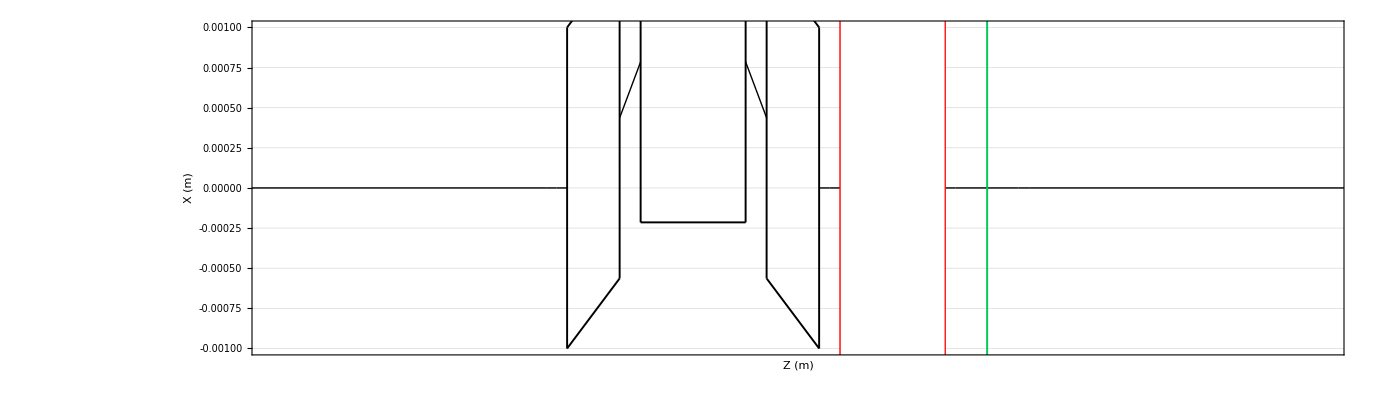

```mathematica
claraslcfel=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[{CLA£S07,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS}],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"}, FrameTicks->{LinTicks[-0.001,0.001,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.001,0.001,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,40,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->False,WidthScale->0.01,GridLines->Automatic,BaseStyle->{FontSize->14,Bold,FontFamily->"Helvetica",Black},AspectRatio->0.3,ImageSize->1400,PlotRange->{{20,21},{-0.001,0.001}}]
```

```mathematica
(*Export["clara_slc_fel.png",claraslcfel,ImageResolution->400]*)
```

At the TDC screen the matched twiss are these - lets match from them...

```mathematica
StartTwiss=CLA£S07£DIA£SCR£03£WTwiss={1,0,1,0};
```

SHIT GOT THE FIRST LOT WRONG---- GO BACK......ok done...

```mathematica
LATTICE=$LATTICE=MADFlatten[{MADFlatten[CLA£S07]⟦Position[MADFlatten[CLA£S07],Select[MADFlatten[CLA£S07],#⟦1⟧=="CLA£S07£DIA£SCR£03£W"&]⟦1⟧]⟦1,1⟧;;-1⟧,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS,CLA£FAB,CLA£PFD}];
```

```mathematica
(*We always need half poles at both ends of an undulator. But what to do about the "half undulators"? 
Neil specified number of periods, so number of poles is always even*)
Block[{lambda,diplength,drilength,dipangle,b0,gamma,pout=0,tilt},
(lambda=2 #⟦3⟧/(ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]);
diplength=lambda/4;
drilength=(lambda-2 diplength)/2;
tilt=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦5⟧]];
b0=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦3⟧]]/(93.4 lambda);
pcen=470;
dipangle= Evaluate[299.8 b0 diplength/pcen];
Clear[Evaluate[# ⟦1⟧<> "£EXP"]];
Clear[EXPLINE];
EXPLINE={};
(*For a first half undulator*)
If[StringMatchQ[#⟦1⟧,"*H1*"],
(*half bend at start*)
sbend[Evaluate[# ⟦1⟧<> "£HS"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HS"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HS"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HS"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HS"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
(*drift at start*)
drift[Evaluate[# ⟦1⟧<> "£HSD"],drilength,ToString[# ⟦1⟧<> "£HSD"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HSD"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£HSD"<>","<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£HSD"]<>"]"]];
(*periodic part*)
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle,E2->-dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle]]<>",E2→"<>ToString[FortranForm[-dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle,E2->dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle]]<>",E2→"<>ToString[FortranForm[dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->-dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
]
(*For a second half undulator*)
If[StringMatchQ[#⟦1⟧,"*H2*"],
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->-dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
drift[Evaluate[# ⟦1⟧<> "£DM"],drilength,ToString[# ⟦1⟧<> "£DM"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£DM"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£DM,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£DM"]<>"]"]];
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i+ IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle,E2->-dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle]]<>",E2→"<>ToString[FortranForm[-dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle,E2->dipangle ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle]]<>",E2→"<>ToString[FortranForm[dipangle]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
sbend[Evaluate[# ⟦1⟧<> "£HE"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HE"],E1->dipangle/2,E2->0.0 ,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HE"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HE"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HE"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];];
line[Evaluate[# ⟦1⟧<> "£EXP"],EXPLINE])
&/@Select[MADFlatten[LATTICE],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&]⟦1;;-1⟧];
```

```mathematica
Clear[LATTICEMADWIG];
LATTICEMADWIG=MADFlatten[ReplacePart[MADFlatten[LATTICE],First[Flatten[Position[MADFlatten[LATTICE],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[LATTICE],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&]]];
```

```mathematica
matchedqs={#⟦1⟧,#⟦4⟧}&/@Select[MADFlatten[$LATTICE],#[[2]]=="Quadrupole"&]
```

{{CLA£S07£MAG£QUAD£08£K,-1.71192},{CLA£S07£MAG£QUAD£09£K,-5.98555},{CLA£S07£MAG£QUAD£10£K,7.72644},{CLA£S07£MAG£QUAD£11£K,-5.24599},{CLA£FMS£MAG£QUAD£03£K,-1.},{CLA£FMS£MAG£QUAD£04£K,-1.},{CLA£FMS£MAG£QUAD£05£K,-1.},{CLA£FRS£R01£MAG£QUAD£01£K,-1.},{CLA£FRS£R02£MAG£QUAD£01£K,-1.},{CLA£FRS£R03£MAG£QUAD£01£K,-1.},{CLA£FRS£R04£MAG£QUAD£01£K,-1.},{CLA£FRS£R05£MAG£QUAD£01£K,-1.},{CLA£FRS£R06£MAG£QUAD£01£K,-1.},{CLA£FRS£R07£MAG£QUAD£01£K,-1.},{CLA£FRS£R08£MAG£QUAD£01£K,-1.},{CLA£FRS£R09£MAG£QUAD£01£K,-1.},{CLA£FRS£R10£MAG£QUAD£01£K,-1.},{CLA£FRS£R11£MAG£QUAD£01£K,-1.},{CLA£FRS£R12£MAG£QUAD£01£K,-1.},{CLA£FRS£R13£MAG£QUAD£01£K,-1.},{CLA£FRS£R14£MAG£QUAD£01£K,-1.},{CLA£FRS£R15£MAG£QUAD£01£K,-1.},{CLA£FRS£R16£MAG£QUAD£01£K,-1.},{CLA£FRS£R17£MAG£QUAD£01£K,-1.},{CLA£PFD£MAG£QUAD£01£K,-1.46779},{CLA£PFD£MAG£QUAD£02£K,-0.64689},{CLA£PFD£MAG£QUAD£03£K,-2.01504},{CLA£PFD£MAG£QUAD£04£K,0.98372},{CLA£PFD£MAG£QUAD£05£K,4.25217},{CLA£PFD£MAG£QUAD£06£K,-2.6469}}

So the problem is the first radiator where i need a match point in an asymmetric location in the undulator...

```mathematica
vals[[23]]
```

10.

```mathematica
Clear[LATTICE2]
Clear[LATTICEMADWIG]
```

was h21,m,h22....

make h22 = h12?? or h121 , 122???

```mathematica
felmatch=Reap[Map[Function[p2,(
Map[Function[p1,quad[p1,0.10,p2⟦1⟧,ToString[p1]]],matchedqs⟦6;;27;;2,1⟧];
Map[Function[p1,quad[p1,0.10,-p2⟦1⟧,ToString[p1]]],matchedqs⟦5;;27;;2,1⟧];
quad[Evaluate@matchedqs⟦1,1⟧,0.10,25,matchedqs⟦1,1⟧];
quad[Evaluate@matchedqs⟦2,1⟧,0.10,-20,matchedqs⟦2,1⟧];
quad[Evaluate@matchedqs⟦3,1⟧,0.10,13,matchedqs⟦3,1⟧];
quad[Evaluate@matchedqs⟦4,1⟧,0.10,1,matchedqs⟦4,1⟧];
drift[CLA£FRS£R01£MAG£UND£W£H21,0.08001,"CLA£FRS£R01£MAG£UND£W£H21",k-> -1.25,poles->5,tilt->-π/2//N];
marker[CLA£FRS£R01£MAG£UND£W£H2M,"CLA£FRS£R01£MAG£UND£W£H2M"];
drift[CLA£FRS£R01£MAG£UND£W£H22,0.29499,"CLA£FRS£R01£MAG£UND£W£H22",k->- 1.25,poles->21,tilt->-π/2//N];
LATTICE=$LATTICE=MADFlatten[{MADFlatten[CLA£S07]⟦Position[MADFlatten[CLA£S07],Select[MADFlatten[CLA£S07],#⟦1⟧=="CLA£S07£DIA£SCR£03£W"&]⟦1⟧]⟦1,1⟧;;-1⟧,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS,CLA£FAB,CLA£PFD}];
LATTICE2=MADFlatten[ReplacePart[LATTICE,Position[LATTICE,"CLA£FRS£R01£MAG£UND£W£H2"]⟦1,1⟧->MADFlatten[{CLA£FRS£R01£MAG£UND£W£H21,CLA£FRS£R01£MAG£UND£W£H2M,CLA£FRS£R01£MAG£UND£W£H22}]]];
(*We always need half poles at both ends of an undulator. But what to do about the "half undulators"? 
Neil specified number of periods, so number of poles is always even*)
Block[{lambda,diplength,drilength,dipangle,b0,gamma,pout=0,tilt},
(lambda=2 #⟦3⟧/(ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]);
diplength=lambda/4;
drilength=(lambda-2 diplength)/2;
tilt=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦5⟧]];
b0=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦3⟧]]/(93.4 lambda);
pcen=470;
dipangle= Evaluate[299.8 b0 diplength/pcen];
Clear[Evaluate[# ⟦1⟧<> "£EXP"]];
Clear[EXPLINE];
EXPLINE={};
(*For a first half undulator*)
If[StringMatchQ[#⟦1⟧,"*H1*"],
(*half bend at start*)
sbend[Evaluate[# ⟦1⟧<> "£HS"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HS"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HS"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HS"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HS"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
(*drift at start*)
drift[Evaluate[# ⟦1⟧<> "£HSD"],drilength,ToString[# ⟦1⟧<> "£HSD"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HSD"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£HSD"<>","<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£HSD"]<>"]"]];
(*periodic part*)
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle/2,E2->-dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle/2,E2->dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->-dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
]
(*For a second half undulator*)
If[StringMatchQ[#⟦1⟧,"*H2*"],If[StringMatchQ[#⟦1⟧,"*R01*H22"],If[!EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->-dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
drift[Evaluate[# ⟦1⟧<> "£DM"],drilength,ToString[# ⟦1⟧<> "£DM"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£DM"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£DM,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£DM"]<>"]"]];
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[!OddQ[i+ IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle/2,E2->-dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle/2,E2->dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
If[!EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],sbend[Evaluate[# ⟦1⟧<> "£HE"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HE"],E1->-dipangle/2,E2->0.0 ,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HE"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HE"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HE"<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2→0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,sbend[Evaluate[# ⟦1⟧<> "£HE"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HE"],E1->dipangle/2,E2->0.0 ,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HE"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HE"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HE"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];],
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->-dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
drift[Evaluate[# ⟦1⟧<> "£DM"],drilength,ToString[# ⟦1⟧<> "£DM"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£DM"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£DM,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£DM"]<>"]"]];
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i+ IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle/2,E2->-dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle/2,E2->dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
sbend[Evaluate[# ⟦1⟧<> "£HE"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HE"],E1->dipangle/2,E2->0.0 ,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HE"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HE"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HE"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];]];
line[Evaluate[# ⟦1⟧<> "£EXP"],EXPLINE]
)
&/@Select[MADFlatten[LATTICE2],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&&StringMatchQ[#⟦2⟧,{"Drift"}]&]⟦1;;-1⟧];
Clear[LATTICEMADWIG];
LATTICEMADWIG=MADFlatten[ReplacePart[MADFlatten[LATTICE2],First[Flatten[Position[MADFlatten[LATTICE2],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[LATTICE2],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&&StringMatchQ[#⟦2⟧,{"Drift"}]&]]];
MADWrite["felmatch",LATTICEMADWIG];
ReadList["!sed -i s/CLA//g felmatch.mff",Word];
ReadList["!sed -i s/MAG//g felmatch.mff",Word];
MADStringWrite["felmatch","eopt,add;\nINITIAL:BETA0,&\n
BETX="<>ToString[StartTwiss⟦1⟧]<>",ALFX="<>ToString[StartTwiss⟦2⟧]<>",&\n
BETY="<>ToString[StartTwiss⟦3⟧]<>",ALFY="<>ToString[StartTwiss⟦4⟧]<>",&\n
dx=0,dpx=0,energy=0.250;\n"];
MADStringWrite["felmatch","eopt,add;\nFODO:BETA0,&\n
BETX="<>ToString[p2⟦2,1⟧]<>",ALFX="<>ToString[p2⟦2,2⟧]<>",&\n
BETY="<>ToString[p2⟦2,3⟧]<>",ALFY="<>ToString[p2⟦2,4⟧]<>",&\n
dx=0,dpx=0;\n"];Print[p2];
MADStringWrite["felmatch","eopt,add;\n"];
MADStringWrite["felmatch","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["felmatch","match,beta0=initial;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦1,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦2,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-30,upper=30;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦3,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-30,upper=30;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦4,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-30,upper=30;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦5,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-30,upper=30;\n"];
(*MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦6,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.001,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦7,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.001,lower=-100,upper=100;\n"];*)
MADStringWrite["felmatch","constraint,"<>StringReplace["CLA£FRS£R01£MAG£UND£W£H2M",{"£"->"","CLA"->"","MAG"-> ""}]<>",beta0=fodo;\n"];
(*MADStringWrite["felmatch","constraint,#s/"<>StringReplace[#,{"£"->"","CLA"->"","MAG"-> ""}]&[matchedqs⟦5,1⟧]<>",betx < 80, bety < 80;\n"];*)
(*MADStringWrite["felmatch","constraint,"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦6,1⟧]<>"/"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦11,1⟧]<>",betx > 0.5, bety > 0.5;\n"];*)
MADStringWrite["felmatch","RMATRIX,#s/"<>StringReplace["CLA£SLC£MARK£03",{"£"->"","CLA"->"","MAG"-> ""}]<>";\n"];
MADStringWrite["felmatch","TMATRIX,#s/"<>StringReplace["CLA£SLC£MARK£03",{"£"->"","CLA"->"","MAG"-> ""}]<>";\n"];
MADStringWrite["felmatch","simplex,calls=5000000,tolerance=1.0E-10;\n"];
(*MADStringWrite["felmatch","level,2;\n"];
MADStringWrite["felmatch","lmdif,calls=50000,tolerance=1.0E-9;\n"];*)
MADStringWrite["felmatch","endmatch;\n"];
Map[Function[p5,MADStringWrite["felmatch","value,"<>StringReplace[p5,{"£"->"","CLA"->"","MAG"-> ""}]&[p5]<>"[K1];\n"]],matchedqs⟦All,1⟧];
MADStringWrite["felmatch","split,name=b1,fraction=0.05\n"];
MADStringWrite["felmatch","split,name=b2,fraction=0.10\n"];
MADStringWrite["felmatch","split,name=b3,fraction=0.15\n"];
MADStringWrite["felmatch","split,name=b4,fraction=0.20\n"];
MADStringWrite["felmatch","split,name=b5,fraction=0.25\n"];
MADStringWrite["felmatch","split,name=b6,fraction=0.30\n"];
MADStringWrite["felmatch","split,name=b7,fraction=0.35\n"];
MADStringWrite["felmatch","split,name=b8,fraction=0.40\n"];
MADStringWrite["felmatch","split,name=b9,fraction=0.45\n"];
MADStringWrite["felmatch","split,name=b10,fraction=0.50\n"];
MADStringWrite["felmatch","split,name=b11,fraction=0.55\n"];
MADStringWrite["felmatch","split,name=b12,fraction=0.60\n"];
MADStringWrite["felmatch","split,name=b13,fraction=0.65\n"];
MADStringWrite["felmatch","split,name=b14,fraction=0.70\n"];
MADStringWrite["felmatch","split,name=b15,fraction=0.75\n"];
MADStringWrite["felmatch","split,name=b16,fraction=0.80\n"];
MADStringWrite["felmatch","split,name=b17,fraction=0.85\n"];
MADStringWrite["felmatch","split,name=b18,fraction=0.90\n"];
MADStringWrite["felmatch","split,name=b19,fraction=0.95\n"];
MADStringWrite["felmatch","select,twiss,full;\ntwiss,beta0=initial,tape=twiss.txt;\n"];
MADStringWrite["felmatch","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
MADStringWrite["felmatch","print,full;\nsurvey,tape=survey.txt;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat felmatch.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < felmatch.mff > felmatch_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < felmatch.mff > felmatch.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->False];
Print[Select[ReadList["felmatch.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&]];
Sow[Map[Function[p3,First[p3]],{BETX,ALFX,BETY,ALFY}]];
Sow[Select[Transpose[{NAME,BETX,ALFX,BETY,ALFY}],StringMatchQ[#⟦1⟧,"*FMSMU1B*"]&]⟦1⟧];
Sow[Map[Function[p5,StringCases[p5,"Value of expression \""~~quad:(WordCharacter|DigitCharacter)..~~"[K1]\" is:"~~WhitespaceCharacter..~~value:(DigitCharacter|"-"|".")..:>{StringCases[p5,v:{"FMS"|"S07"}~~x:"QUAD"~~y:DigitCharacter..~~z:"K":>  "CLA£"~~v~~"£"~~"MAG"~~"£"~~x~~"£"~~y~~"£"~~z]&[quad]⟦1⟧,value}]⟦1⟧],Select[FindList["felmatch.echo.txt","Value of expression "],StringMatchQ[#,{"*FMS*QUAD*"|"*S07*QUAD*"}]&]]];
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["k = "<>ToString[p2⟦1⟧],FontFamily->"Helvetica",Bold,FontSize->14],{20,21}]},Prolog->MADDraw[LATTICE2,Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,30}},ImageSize->700,AspectRatio->0.5];
Sow[Show[plt]];
)],FodoTwiss⟦16;;16⟧]]⟦2,1⟧;
```

{7.2,{2.45962,-0.995819,2.89645,1.13027}}

{ MTCOND.  Last value of the penalty function:  1.640173E-08}

below run for FodoTwiss[[23]] = k = 10.0

```mathematica
MADInfo[LATTICEMADWIG⟦1;;200⟧]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£S07£DIA£SCR£03£W | Marker | 0 | --- | --- | --- | CLA£S07£DIA£SCR£03£W | 0
2 | CLA£S07£DIA£SCR£03£A | Drift | 0.076667 | --- | --- | --- | CLA£S07£DIA£SCR£03£A | 0.076667
3 | CLA£S07£MARK£02 | Marker | 0 | --- | --- | --- | CLA£S07£MARK£02 | 0.076667
4 | CLA£S07£DRIFT£13 | Drift | 0.1 | --- | --- | --- | CLA£S07£DRIFT£13 | 0.176667
5 | CLA£S07£MAG£QUAD£08£B | Drift | 0.1 | --- | --- | --- | CLA£S07£MAG£QUAD£08£B | 0.276667
6 | CLA£S07£MAG£QUAD£08£K | Quadrupole | 0.1 | 25 | --- | --- | CLA£S07£MAG£QUAD£08£K | 0.376667
7 | CLA£S07£MAG£QUAD£08£A | Drift | 0.1 | --- | --- | --- | CLA£S07£MAG£QUAD£08£A | 0.476667
8 | CLA£S07£DRIFT£14 | Drift | 0.2 | --- | --- | --- | CLA£S07£DRIFT£14 | 0.676667
9 | CLA£S07£MAG£QUAD£09£B | Drift | 0.1 | --- | --- | --- | CLA£S07£MAG£QUAD£09£B | 0.776667
10 | CLA£S07£MAG£QUAD£09£K | Quadrupole | 0.1 | -20 | --- | --- | CLA£S07£MAG£QUAD£09£K | 0.876667
11 | CLA£S07£MAG£QUAD£09£A | Drift | 0.1 | --- | --- | --- | CLA£S07£MAG£QUAD£09£A | 0.976667
12 | CLA£S07£DIA£BPM£07 | Drift | 0.21 | --- | --- | --- | CLA£S07£DIA£BPM£07 | 1.18667
13 | CLA£S07£MAG£HVCOR£07£B | Drift | 0.025 | --- | --- | --- | CLA£S07£MAG£HVCOR£07£B | 1.21167
14 | CLA£S07£MAG£HVCOR£07£K | Kicker | 0.05 | --- | 0. | 0. | CLA£S07£MAG£HVCOR£07£K | 1.26167
15 | CLA£S07£MAG£HVCOR£07£A | Drift | 0.025 | --- | --- | --- | CLA£S07£MAG£HVCOR£07£A | 1.28667
16 | CLA£S07£DIA£SCR£04£B | Drift | 0.043333 | --- | --- | --- | CLA£S07£DIA£SCR£04£B | 1.33
17 | CLA£S07£DIA£SCR£04£W | Marker | 0 | --- | --- | --- | CLA£S07£DIA£SCR£04£W | 1.33
18 | CLA£S07£DIA£SCR£04£A | Drift | 0.076667 | --- | --- | --- | CLA£S07£DIA£SCR£04£A | 1.40667
19 | CLA£S07£MAG£QUAD£10£B | Drift | 0.1 | --- | --- | --- | CLA£S07£MAG£QUAD£10£B | 1.50667
20 | CLA£S07£MAG£QUAD£10£K | Quadrupole | 0.1 | 13 | --- | --- | CLA£S07£MAG£QUAD£10£K | 1.60667
21 | CLA£S07£MAG£QUAD£10£A | Drift | 0.1 | --- | --- | --- | CLA£S07£MAG£QUAD£10£A | 1.70667
22 | CLA£S07£DRIFT£15 | Drift | 0.4 | --- | --- | --- | CLA£S07£DRIFT£15 | 2.10667
23 | CLA£S07£MAG£QUAD£11£B | Drift | 0.1 | --- | --- | --- | CLA£S07£MAG£QUAD£11£B | 2.20667
24 | CLA£S07£MAG£QUAD£11£K | Quadrupole | 0.1 | 1 | --- | --- | CLA£S07£MAG£QUAD£11£K | 2.30667
25 | CLA£S07£MAG£QUAD£11£A | Drift | 0.1 | --- | --- | --- | CLA£S07£MAG£QUAD£11£A | 2.40667
26 | CLA£S07£DIA£BPM£08 | Drift | 0.21 | --- | --- | --- | CLA£S07£DIA£BPM£08 | 2.61667
27 | CLA£S07£DIA£SCR£05£B | Drift | 0.043333 | --- | --- | --- | CLA£S07£DIA£SCR£05£B | 2.66
28 | CLA£S07£DIA£SCR£05£W | Marker | 0 | --- | --- | --- | CLA£S07£DIA£SCR£05£W | 2.66
29 | CLA£S07£DIA£SCR£05£A | Drift | 0.076667 | --- | --- | --- | CLA£S07£DIA£SCR£05£A | 2.73667
30 | CLA£S07£MAG£HVCOR£08£B | Drift | 0.025 | --- | --- | --- | CLA£S07£MAG£HVCOR£08£B | 2.76167
31 | CLA£S07£MAG£HVCOR£08£K | Kicker | 0.05 | --- | 0. | 0. | CLA£S07£MAG£HVCOR£08£K | 2.81167
32 | CLA£S07£MAG£HVCOR£08£A | Drift | 0.025 | --- | --- | --- | CLA£S07£MAG£HVCOR£08£A | 2.83667
33 | CLA£S07£MARK£03 | Marker | 0 | --- | --- | --- | CLA£S07£MARK£03 | 2.83667
34 | CLA£SLC£MARK£01 | Marker | 0 | --- | --- | --- |  | 2.83667
35 | CLA£SLC£MAG£DIP£01 | SectorBend | 0.100167 | 0 | --- | 0.1 | CLA£SLC£MAG£DIP£01 | 2.93683
36 | CLA£SLC£DRIFT£01 | Drift | 0.201004 | --- | --- | --- | CLA£SLC£DRIFT£01 | 3.13784
37 | CLA£SLC£MAG£DIP£02 | SectorBend | 0.100167 | 0 | --- | -0.1 | CLA£SLC£MAG£DIP£02 | 3.238
38 | CLA£SLC£DRIFT£02 | Drift | 0.05 | --- | --- | --- | CLA£SLC£DRIFT£02 | 3.288
39 | CLA£SLC£MARK£02 | Marker | 0 | --- | --- | --- |  | 3.288
40 | CLA£SLC£DRIFT£03 | Drift | 0.05 | --- | --- | --- | CLA£SLC£DRIFT£03 | 3.338
41 | CLA£SLC£MAG£DIP£03 | SectorBend | 0.100167 | 0 | --- | -0.1 | CLA£SLC£MAG£DIP£03 | 3.43817
42 | CLA£SLC£DRIFT£04 | Drift | 0.201004 | --- | --- | --- | CLA£SLC£DRIFT£04 | 3.63918
43 | CLA£SLC£MAG£DIP£04 | SectorBend | 0.100167 | 0 | --- | 0.1 | CLA£SLC£MAG£DIP£04 | 3.73934
44 | CLA£SLC£MARK£03 | Marker | 0 | --- | --- | --- |  | 3.73934
45 | CLA£FMS£MAG£MU1£B | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£MU1£B | 3.78934
46 | CLA£FMS£MAG£MU1£W£H1£HS | SectorBend | 0.01875 | 0 | --- | 0.00426842 | CLA£FMS£MAG£MU1£W£H1£HS | 3.80809
47 | CLA£FMS£MAG£MU1£W£H1£HSD | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H1£HSD | 3.84559
48 | CLA£FMS£MAG£MU1£W£H1£1 | SectorBend | 0.0375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU1£W£H1£1 | 3.88309
49 | CLA£FMS£MAG£MU1£W£H1£1D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H1£1D | 3.92059
50 | CLA£FMS£MAG£MU1£W£H1£2 | SectorBend | 0.0375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU1£W£H1£2 | 3.95809
51 | CLA£FMS£MAG£MU1£W£H1£2D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H1£2D | 3.99559
52 | CLA£FMS£MAG£MU1£W£H1£3 | SectorBend | 0.0375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU1£W£H1£3 | 4.03309
53 | CLA£FMS£MAG£MU1£W£H1£3D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H1£3D | 4.07059
54 | CLA£FMS£MAG£MU1£W£H1£4 | SectorBend | 0.0375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU1£W£H1£4 | 4.10809
55 | CLA£FMS£MAG£MU1£W£H1£4D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H1£4D | 4.14559
56 | CLA£FMS£MAG£MU1£W£H1£5 | SectorBend | 0.0375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU1£W£H1£5 | 4.18309
57 | CLA£FMS£MAG£MU1£W£H1£5D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H1£5D | 4.22059
58 | CLA£FMS£MAG£MU1£W£H1£HM | SectorBend | 0.01875 | 0 | --- | 0.00426842 | CLA£FMS£MAG£MU1£W£H1£HM | 4.23934
59 | CLA£FMS£MU1£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FMS£MU1£MARK£01 | 4.23934
60 | CLA£FMS£MAG£MU1£W£H2£HM | SectorBend | 0.01875 | 0 | --- | 0.00426842 | CLA£FMS£MAG£MU1£W£H2£HM | 4.25809
61 | CLA£FMS£MAG£MU1£W£H2£DM | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H2£DM | 4.29559
62 | CLA£FMS£MAG£MU1£W£H2£1 | SectorBend | 0.0375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU1£W£H2£1 | 4.33309
63 | CLA£FMS£MAG£MU1£W£H2£1D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H2£1D | 4.37059
64 | CLA£FMS£MAG£MU1£W£H2£2 | SectorBend | 0.0375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU1£W£H2£2 | 4.40809
65 | CLA£FMS£MAG£MU1£W£H2£2D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H2£2D | 4.44559
66 | CLA£FMS£MAG£MU1£W£H2£3 | SectorBend | 0.0375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU1£W£H2£3 | 4.48309
67 | CLA£FMS£MAG£MU1£W£H2£3D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H2£3D | 4.52059
68 | CLA£FMS£MAG£MU1£W£H2£4 | SectorBend | 0.0375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU1£W£H2£4 | 4.55809
69 | CLA£FMS£MAG£MU1£W£H2£4D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H2£4D | 4.59559
70 | CLA£FMS£MAG£MU1£W£H2£5 | SectorBend | 0.0375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU1£W£H2£5 | 4.63309
71 | CLA£FMS£MAG£MU1£W£H2£5D | Drift | 0.0375 | --- | --- | --- | CLA£FMS£MAG£MU1£W£H2£5D | 4.67059
72 | CLA£FMS£MAG£MU1£W£H2£HE | SectorBend | 0.01875 | 0 | --- | 0.00426842 | CLA£FMS£MAG£MU1£W£H2£HE | 4.68934
73 | CLA£FMS£MAG£MU1£A | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£MU1£A | 4.73934
74 | CLA£FMS£DRIFT£01 | Drift | 0.05 | --- | --- | --- | CLA£FMS£DRIFT£01 | 4.78934
75 | CLA£FMS£MAG£QUAD£03£B | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£QUAD£03£B | 4.83934
76 | CLA£FMS£MAG£QUAD£03£K | Quadrupole | 0.1 | -7.2 | --- | --- | CLA£FMS£MAG£QUAD£03£K | 4.93934
77 | CLA£FMS£MAG£QUAD£03£A | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£QUAD£03£A | 4.98934
78 | CLA£FMS£MAG£DIP£01£B | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£DIP£01£B | 5.03934
79 | CLA£FMS£MAG£DIP£01£D | SectorBend | 0.100066 | 0 | --- | -0.0349066 | CLA£FMS£MAG£DIP£01£D | 5.13941
80 | CLA£FMS£MAG£DIP£01£A | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£DIP£01£A | 5.18941
81 | CLA£FMS£DRIFT£02 | Drift | 0.100061 | --- | --- | --- | CLA£FMS£DRIFT£02 | 5.28947
82 | CLA£FMS£MAG£DIP£02£B | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£DIP£02£B | 5.33947
83 | CLA£FMS£MAG£DIP£02£D | SectorBend | 0.200132 | 0 | --- | 0.0698132 | CLA£FMS£MAG£DIP£02£D | 5.5396
84 | CLA£FMS£MAG£DIP£02£A | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£DIP£02£A | 5.5896
85 | CLA£FMS£DRIFT£03 | Drift | 0.100061 | --- | --- | --- | CLA£FMS£DRIFT£03 | 5.68966
86 | CLA£FMS£MAG£DIP£03£B | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£DIP£03£B | 5.73966
87 | CLA£FMS£MAG£DIP£03£D | SectorBend | 0.100066 | 0 | --- | -0.0349066 | CLA£FMS£MAG£DIP£03£D | 5.83973
88 | CLA£FMS£MAG£DIP£03£A | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£DIP£03£A | 5.88973
89 | CLA£FMS£DIA£BPM£03 | Drift | 0.15 | --- | --- | --- | CLA£FMS£DIA£BPM£03 | 6.03973
90 | CLA£FMS£MAG£QUAD£04£B | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£QUAD£04£B | 6.08973
91 | CLA£FMS£MAG£QUAD£04£K | Quadrupole | 0.1 | 7.2 | --- | --- | CLA£FMS£MAG£QUAD£04£K | 6.18973
92 | CLA£FMS£MAG£QUAD£04£A | Drift | 0.025 | --- | --- | --- | CLA£FMS£MAG£QUAD£04£A | 6.21473
93 | CLA£FMS£MAG£MU2£B | Drift | 0.015 | --- | --- | --- | CLA£FMS£MAG£MU2£B | 6.22973
94 | CLA£FMS£MAG£MU2£W£H1£HS | SectorBend | 0.0167188 | 0 | --- | 0.00426842 | CLA£FMS£MAG£MU2£W£H1£HS | 6.24645
95 | CLA£FMS£MAG£MU2£W£H1£HSD | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H1£HSD | 6.27989
96 | CLA£FMS£MAG£MU2£W£H1£1 | SectorBend | 0.0334375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU2£W£H1£1 | 6.31332
97 | CLA£FMS£MAG£MU2£W£H1£1D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H1£1D | 6.34676
98 | CLA£FMS£MAG£MU2£W£H1£2 | SectorBend | 0.0334375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU2£W£H1£2 | 6.3802
99 | CLA£FMS£MAG£MU2£W£H1£2D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H1£2D | 6.41364
100 | CLA£FMS£MAG£MU2£W£H1£3 | SectorBend | 0.0334375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU2£W£H1£3 | 6.44707
101 | CLA£FMS£MAG£MU2£W£H1£3D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H1£3D | 6.48051
102 | CLA£FMS£MAG£MU2£W£H1£4 | SectorBend | 0.0334375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU2£W£H1£4 | 6.51395
103 | CLA£FMS£MAG£MU2£W£H1£4D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H1£4D | 6.54739
104 | CLA£FMS£MAG£MU2£W£H1£5 | SectorBend | 0.0334375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU2£W£H1£5 | 6.58082
105 | CLA£FMS£MAG£MU2£W£H1£5D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H1£5D | 6.61426
106 | CLA£FMS£MAG£MU2£W£H1£6 | SectorBend | 0.0334375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU2£W£H1£6 | 6.6477
107 | CLA£FMS£MAG£MU2£W£H1£6D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H1£6D | 6.68114
108 | CLA£FMS£MAG£MU2£W£H1£7 | SectorBend | 0.0334375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU2£W£H1£7 | 6.71457
109 | CLA£FMS£MAG£MU2£W£H1£7D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H1£7D | 6.74801
110 | CLA£FMS£MAG£MU2£W£H1£HM | SectorBend | 0.0167188 | 0 | --- | 0.00426842 | CLA£FMS£MAG£MU2£W£H1£HM | 6.76473
111 | CLA£FMS£MU2£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FMS£MU2£MARK£01 | 6.76473
112 | CLA£FMS£MAG£MU2£W£H2£HM | SectorBend | 0.0167188 | 0 | --- | 0.00426842 | CLA£FMS£MAG£MU2£W£H2£HM | 6.78145
113 | CLA£FMS£MAG£MU2£W£H2£DM | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H2£DM | 6.81489
114 | CLA£FMS£MAG£MU2£W£H2£1 | SectorBend | 0.0334375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU2£W£H2£1 | 6.84832
115 | CLA£FMS£MAG£MU2£W£H2£1D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H2£1D | 6.88176
116 | CLA£FMS£MAG£MU2£W£H2£2 | SectorBend | 0.0334375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU2£W£H2£2 | 6.9152
117 | CLA£FMS£MAG£MU2£W£H2£2D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H2£2D | 6.94864
118 | CLA£FMS£MAG£MU2£W£H2£3 | SectorBend | 0.0334375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU2£W£H2£3 | 6.98207
119 | CLA£FMS£MAG£MU2£W£H2£3D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H2£3D | 7.01551
120 | CLA£FMS£MAG£MU2£W£H2£4 | SectorBend | 0.0334375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU2£W£H2£4 | 7.04895
121 | CLA£FMS£MAG£MU2£W£H2£4D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H2£4D | 7.08239
122 | CLA£FMS£MAG£MU2£W£H2£5 | SectorBend | 0.0334375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU2£W£H2£5 | 7.11582
123 | CLA£FMS£MAG£MU2£W£H2£5D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H2£5D | 7.14926
124 | CLA£FMS£MAG£MU2£W£H2£6 | SectorBend | 0.0334375 | 0 | --- | 0.00853684 | CLA£FMS£MAG£MU2£W£H2£6 | 7.1827
125 | CLA£FMS£MAG£MU2£W£H2£6D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H2£6D | 7.21614
126 | CLA£FMS£MAG£MU2£W£H2£7 | SectorBend | 0.0334375 | 0 | --- | -0.00853684 | CLA£FMS£MAG£MU2£W£H2£7 | 7.24957
127 | CLA£FMS£MAG£MU2£W£H2£7D | Drift | 0.0334375 | --- | --- | --- | CLA£FMS£MAG£MU2£W£H2£7D | 7.28301
128 | CLA£FMS£MAG£MU2£W£H2£HE | SectorBend | 0.0167188 | 0 | --- | 0.00426842 | CLA£FMS£MAG£MU2£W£H2£HE | 7.29973
129 | CLA£FMS£MAG£MU2£A | Drift | 0.015 | --- | --- | --- | CLA£FMS£MAG£MU2£A | 7.31473
130 | CLA£FMS£MAG£QUAD£05£B | Drift | 0.025 | --- | --- | --- | CLA£FMS£MAG£QUAD£05£B | 7.33973
131 | CLA£FMS£MAG£QUAD£05£K | Quadrupole | 0.1 | -7.2 | --- | --- | CLA£FMS£MAG£QUAD£05£K | 7.43973
132 | CLA£FMS£MAG£QUAD£05£A | Drift | 0.05 | --- | --- | --- | CLA£FMS£MAG£QUAD£05£A | 7.48973
133 | CLA£FMS£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FMS£MARK£01 | 7.48973
134 | CLA£FRS£APER | Marker | 0 | --- | --- | --- | CLA£FRS£APER | 7.48973
135 | CLA£FRS£R01£DIA£SCR£01£B | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£B | 7.51973
136 | CLA£FRS£R01£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£W | 7.51973
137 | CLA£FRS£R01£DIA£SCR£01£A | Drift | 0.03 | --- | --- | --- | CLA£FRS£R01£DIA£SCR£01£A | 7.54973
138 | CLA£FRS£R01£DIA£BPM£01 | Drift | 0. | --- | --- | --- | CLA£FRS£R01£DIA£BPM£01 | 7.54973
139 | CLA£FRS£R01£MAG£UND£B | Drift | 0.01 | --- | --- | --- | CLA£FRS£R01£MAG£UND£B | 7.55973
140 | CLA£FRS£R01£MAG£UND£W£H1£HS | SectorBend | 0.00360577 | 0 | --- | 0.0010671 | CLA£FRS£R01£MAG£UND£W£H1£HS | 7.56333
141 | CLA£FRS£R01£MAG£UND£W£H1£HSD | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£HSD | 7.57055
142 | CLA£FRS£R01£MAG£UND£W£H1£1 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£1 | 7.57776
143 | CLA£FRS£R01£MAG£UND£W£H1£1D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£1D | 7.58497
144 | CLA£FRS£R01£MAG£UND£W£H1£2 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£2 | 7.59218
145 | CLA£FRS£R01£MAG£UND£W£H1£2D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£2D | 7.59939
146 | CLA£FRS£R01£MAG£UND£W£H1£3 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£3 | 7.6066
147 | CLA£FRS£R01£MAG£UND£W£H1£3D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£3D | 7.61382
148 | CLA£FRS£R01£MAG£UND£W£H1£4 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£4 | 7.62103
149 | CLA£FRS£R01£MAG£UND£W£H1£4D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£4D | 7.62824
150 | CLA£FRS£R01£MAG£UND£W£H1£5 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£5 | 7.63545
151 | CLA£FRS£R01£MAG£UND£W£H1£5D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£5D | 7.64266
152 | CLA£FRS£R01£MAG£UND£W£H1£6 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£6 | 7.64987
153 | CLA£FRS£R01£MAG£UND£W£H1£6D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£6D | 7.65708
154 | CLA£FRS£R01£MAG£UND£W£H1£7 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£7 | 7.6643
155 | CLA£FRS£R01£MAG£UND£W£H1£7D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£7D | 7.67151
156 | CLA£FRS£R01£MAG£UND£W£H1£8 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£8 | 7.67872
157 | CLA£FRS£R01£MAG£UND£W£H1£8D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£8D | 7.68593
158 | CLA£FRS£R01£MAG£UND£W£H1£9 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£9 | 7.69314
159 | CLA£FRS£R01£MAG£UND£W£H1£9D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£9D | 7.70035
160 | CLA£FRS£R01£MAG£UND£W£H1£10 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£10 | 7.70757
161 | CLA£FRS£R01£MAG£UND£W£H1£10D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£10D | 7.71478
162 | CLA£FRS£R01£MAG£UND£W£H1£11 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£11 | 7.72199
163 | CLA£FRS£R01£MAG£UND£W£H1£11D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£11D | 7.7292
164 | CLA£FRS£R01£MAG£UND£W£H1£12 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£12 | 7.73641
165 | CLA£FRS£R01£MAG£UND£W£H1£12D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£12D | 7.74362
166 | CLA£FRS£R01£MAG£UND£W£H1£13 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£13 | 7.75083
167 | CLA£FRS£R01£MAG£UND£W£H1£13D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£13D | 7.75805
168 | CLA£FRS£R01£MAG£UND£W£H1£14 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£14 | 7.76526
169 | CLA£FRS£R01£MAG£UND£W£H1£14D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£14D | 7.77247
170 | CLA£FRS£R01£MAG£UND£W£H1£15 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£15 | 7.77968
171 | CLA£FRS£R01£MAG£UND£W£H1£15D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£15D | 7.78689
172 | CLA£FRS£R01£MAG£UND£W£H1£16 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£16 | 7.7941
173 | CLA£FRS£R01£MAG£UND£W£H1£16D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£16D | 7.80132
174 | CLA£FRS£R01£MAG£UND£W£H1£17 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£17 | 7.80853
175 | CLA£FRS£R01£MAG£UND£W£H1£17D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£17D | 7.81574
176 | CLA£FRS£R01£MAG£UND£W£H1£18 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£18 | 7.82295
177 | CLA£FRS£R01£MAG£UND£W£H1£18D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£18D | 7.83016
178 | CLA£FRS£R01£MAG£UND£W£H1£19 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£19 | 7.83737
179 | CLA£FRS£R01£MAG£UND£W£H1£19D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£19D | 7.84458
180 | CLA£FRS£R01£MAG£UND£W£H1£20 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£20 | 7.8518
181 | CLA£FRS£R01£MAG£UND£W£H1£20D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£20D | 7.85901
182 | CLA£FRS£R01£MAG£UND£W£H1£21 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£21 | 7.86622
183 | CLA£FRS£R01£MAG£UND£W£H1£21D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£21D | 7.87343
184 | CLA£FRS£R01£MAG£UND£W£H1£22 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£22 | 7.88064
185 | CLA£FRS£R01£MAG£UND£W£H1£22D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£22D | 7.88785
186 | CLA£FRS£R01£MAG£UND£W£H1£23 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£23 | 7.89507
187 | CLA£FRS£R01£MAG£UND£W£H1£23D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£23D | 7.90228
188 | CLA£FRS£R01£MAG£UND£W£H1£24 | SectorBend | 0.00721154 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£24 | 7.90949
189 | CLA£FRS£R01£MAG£UND£W£H1£24D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£24D | 7.9167
190 | CLA£FRS£R01£MAG£UND£W£H1£25 | SectorBend | 0.00721154 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H1£25 | 7.92391
191 | CLA£FRS£R01£MAG£UND£W£H1£25D | Drift | 0.00721154 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H1£25D | 7.93112
192 | CLA£FRS£R01£MAG£UND£W£H1£HM | SectorBend | 0.00360577 | 0 | --- | 0.0010671 | CLA£FRS£R01£MAG£UND£W£H1£HM | 7.93473
193 | CLA£FRS£R01£MARK£01 | Marker | 0 | --- | --- | --- | CLA£FRS£R01£MARK£01 | 7.93473
194 | CLA£FRS£R01£MAG£UND£W£H21£HM | SectorBend | 0.0040005 | 0 | --- | 0.0010671 | CLA£FRS£R01£MAG£UND£W£H21£HM | 7.93873
195 | CLA£FRS£R01£MAG£UND£W£H21£DM | Drift | 0.008001 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H21£DM | 7.94673
196 | CLA£FRS£R01£MAG£UND£W£H21£1 | SectorBend | 0.008001 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H21£1 | 7.95473
197 | CLA£FRS£R01£MAG£UND£W£H21£1D | Drift | 0.008001 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H21£1D | 7.96273
198 | CLA£FRS£R01£MAG£UND£W£H21£2 | SectorBend | 0.008001 | 0 | --- | 0.00213421 | CLA£FRS£R01£MAG£UND£W£H21£2 | 7.97073
199 | CLA£FRS£R01£MAG£UND£W£H21£2D | Drift | 0.008001 | --- | --- | --- | CLA£FRS£R01£MAG£UND£W£H21£2D | 7.97873
200 | CLA£FRS£R01£MAG£UND£W£H21£3 | SectorBend | 0.008001 | 0 | --- | -0.00213421 | CLA£FRS£R01£MAG£UND£W£H21£3 | 7.98674

Total Length = 7.98674 m

```mathematica
FodoTwiss
```

{{1.2,{4.46329,-0.264188,41.1161,2.26218}},{1.6,{4.35125,-0.348224,17.5114,1.31813}},{2.,{4.21895,-0.426132,12.223,1.16923}},{2.4,{4.07266,-0.497494,9.58366,1.11371}},{2.8,{3.91811,-0.562314,7.94475,1.08812}},{3.2,{3.76013,-0.620907,6.8108,1.07577}},{3.6,{3.60256,-0.673792,5.97301,1.07046}},{4.,{3.44823,-0.721596,5.32589,1.06941}},{4.4,{3.29916,-0.764991,4.80965,1.07126}},{4.8,{3.15664,-0.804639,4.38757,1.07524}},{5.2,{3.02142,-0.841171,4.03574,1.08095}},{5.6,{2.89387,-0.875171,3.73785,1.08815}},{6.,{2.77408,-0.907172,3.48236,1.09671}},{6.4,{2.66193,-0.937658,3.26089,1.10658}},{6.8,{2.55721,-0.967071,3.06717,1.11776}},{7.2,{2.45962,-0.995819,2.89645,1.13027}},{7.6,{2.36884,-1.02428,2.74504,1.14418}},{8.,{2.28452,-1.05282,2.61004,1.15958}},{8.4,{2.20634,-1.08179,2.48918,1.1766}},{8.8,{2.13402,-1.11155,2.3806,1.19538}},{9.2,{2.0673,-1.14248,2.28285,1.21612}},{9.6,{2.00595,-1.17496,2.19474,1.23904}},{10.,{1.94982,-1.20945,2.11533,1.26442}},{10.4,{1.89881,-1.24645,2.04388,1.29261}},{10.8,{1.8529,-1.28654,1.97983,1.32403}},{11.2,{1.81216,-1.33045,1.92278,1.35922}},{11.6,{1.77678,-1.37906,1.87252,1.39884}},{12.,{1.7471,-1.43348,1.82898,1.44374}},{12.4,{1.72366,-1.49519,1.79231,1.49504}},{12.8,{1.7073,-1.56616,1.76293,1.55423}},{13.2,{1.69931,-1.64911,1.74156,1.62331}},{13.6,{1.70166,-1.748,1.72943,1.70512}},{14.,{1.71748,-1.86876,1.72852,1.80379}},{14.4,{1.75191,-2.02091,1.74202,1.9256}},{14.8,{1.81409,-2.22088,1.77535,2.08071}},{15.2,{1.9219,-2.50013,1.83824,2.28684}},{15.6,{2.1162,-2.92944,1.95011,2.57855}},{16.,{2.5196,-3.7178,2.15652,3.03545}}}

```mathematica
r56string=StringCases[#,WhitespaceCharacter..~~R51:(DigitCharacter|"-"|".")..~~WhitespaceCharacter..~~R52:(DigitCharacter|"-"|".")..~~WhitespaceCharacter..~~R53:(DigitCharacter|"-"|".")..~~WhitespaceCharacter..~~R54:(DigitCharacter|"-"|".")..~~WhitespaceCharacter..~~R55:(DigitCharacter|"-"|".")..~~WhitespaceCharacter..~~R56:(DigitCharacter|"-"|".")..:>R56]⟦1⟧&/@Take[ReadList["felmatch.print.txt",Record],{Last[Position[StringMatchQ[#,__~~"RMATRIX"~~__]&/@ReadList["felmatch.print.txt",Record],True]][[1]]+5}]
t566string=StringCases[#,WhitespaceCharacter..~~T561:(DigitCharacter|"-"|"."|"+"|"E")..~~WhitespaceCharacter..~~T562:(DigitCharacter|"-"|"."|"+"|"E")..~~WhitespaceCharacter..~~T563:(DigitCharacter|"-"|"."|"+"|"E")..~~WhitespaceCharacter..~~T564:(DigitCharacter|"-"|"."|"+"|"E")..~~WhitespaceCharacter..~~T565:(DigitCharacter|"-"|"."|"+"|"E")..~~WhitespaceCharacter..~~T566:(DigitCharacter|"-"|"."|"+"|"E")..:>T566]⟦1⟧&/@Take[ReadList["felmatch.print.txt",Record],{Last[Position[StringMatchQ[#,__~~"TMATRIX"~~__]&/@ReadList["felmatch.print.txt",Record],True]][[1]]+30}]
```

{0.005404}

{-0.817871E-02}

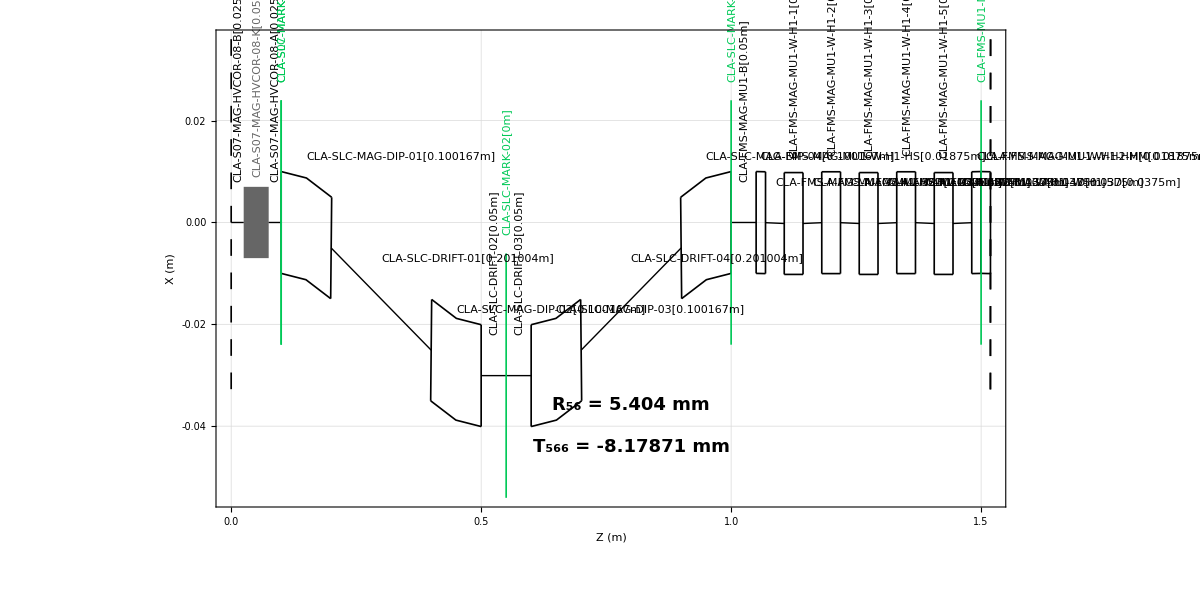

```mathematica
slc=Show[#,Epilog->{Text[Style["
R_56 = "<>ToString[1000ToExpression[r56string[[1]]]]<>" mm\n
T_566 = "<>ToString[1000ToExpression[StringReplace[t566string[[1]],"E"->"*10^"]]]<>" mm",Bold,FontFamily->"Helvetica",FontSize->18],{0.8,-0.04}]}]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[LATTICEMADWIG]⟦30;;60⟧,Bends->True,Labels->True,Frame->True,DriftLabels->True,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"}, FrameTicks->{LinTicks[0,2,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,2,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->True,WidthScale->0.1,GridLines->Automatic,BaseStyle->{FontSize->14,Bold,FontFamily->"Helvetica",Black},AspectRatio->0.5,ImageSize->1200]
```

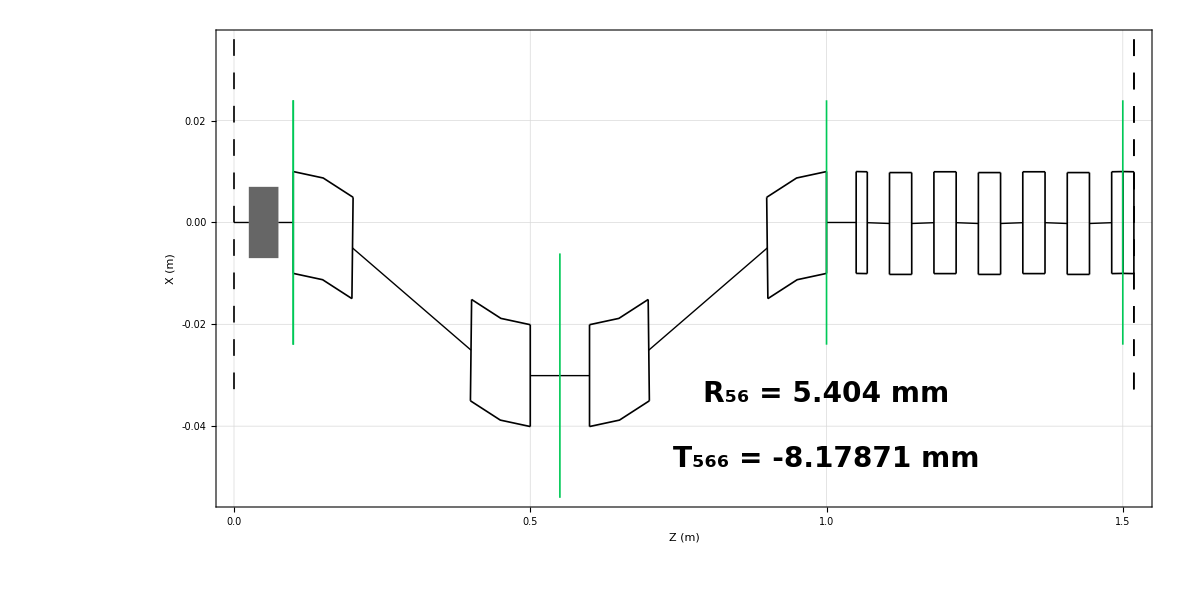

```mathematica
slcipac=Show[#,Epilog->{Text[Style["
R_56 = "<>ToString[1000ToExpression[r56string[[1]]]]<>" mm\n
T_566 = "<>ToString[1000ToExpression[StringReplace[t566string[[1]],"E"->"*10^"]]]<>" mm",Bold,FontFamily->"Helvetica",FontSize->28],{1,-0.04}]}]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[LATTICEMADWIG]⟦30;;60⟧,Bends->True,Labels->False,Frame->True,DriftLabels->True,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"}, FrameTicks->{LinTicks[0,2,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,2,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->True,WidthScale->0.1,GridLines->Automatic,BaseStyle->{FontSize->30,Bold,FontFamily->"Helvetica",Black},AspectRatio->0.5,ImageSize->1200]
```

```mathematica
(*Export["clara_slc_ipac.png",slcipac,ImageResolution->400]*)
```

```mathematica
linethick=0.001;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]},{Dashing->False,Purple,Thickness[linethick]}}}];plt=mfsPlot[{{S,BETX},{S,BETY},{S,10000DX},{S,1000000DY}},Prolog->MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[LATTICEMADWIG],Bends->False,Offset->0,Labels->False,WidthScale->10]⟦1⟧,Frame->True,GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m), η_x (100 μm), η_y (μm)",""},{"s (m)",""}},PlotRange->{{2,11},{-15,10}},ImageSize->1600,AspectRatio->0.5]
```

-Graphics-

```mathematica
linethick=0.001;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,Blue,Thickness[linethick]},{Dashing->False,Purple,Thickness[linethick]}}}];plt=mfsPlot[{{S,BETX},{S,BETY},{S,10000DX},{S,100000DY}},Prolog->MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[LATTICEMADWIG],Bends->False,Offset->0,Labels->False,WidthScale->10]⟦1⟧,Frame->True,GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m), η_x (100 μm), η_y (10 μm)",""},{"s (m)",""}},PlotRange->{{2,11},{-15,10}},ImageSize->800,AspectRatio->0.5]
```

-Graphics-

```mathematica
(*Export["clara_felstart_ipac.png",plt,ImageResolution->300]*)
```

```mathematica
linethick=0.001;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]},{Dashing->False,Purple,Thickness[linethick]}}}];plt=mfsPlot[{{S,BETX},{S,BETY},{S,1000000DX},{S,1000000DY}},Prolog->MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[LATTICEMADWIG],Bends->False,Offset->0,Labels->True,WidthScale->10]⟦1⟧,Frame->True,GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m), η_x (μm)",""},{"s (m)",""}},PlotRange->{{7.5,9.5},{-30,20}},ImageSize->1600,AspectRatio->0.5]
```

-Graphics-

```mathematica
testlattice=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[LATTICEMADWIG],Bends->True,Labels->True,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"}, FrameTicks->{LinTicks[0,40,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,40,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->False,WidthScale->0.01,GridLines->Automatic,BaseStyle->{FontSize->14,Bold,FontFamily->"Helvetica",Black},AspectRatio->0.3,ImageSize->1400,PlotRange->{{6,10},All}]
```

-Graphics-

```mathematica
testlattice=Show[#]&@MADDraw[If[#[[2]]==="BPM"||StringMatchQ[#[[1]],"*COR*"],If[StringMatchQ[#[[1]],"*COR*"]&&StringMatchQ[#[[1]],"*RAD*"],ReplacePart[#,7->"\n"<>StringReplace[#[[1]],"£"->"-"]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]],ReplacePart[#,7->StringReplace[#[[1]],"£"->"-"]]]&/@MADFlatten[LATTICEMADWIG],Bends->True,Labels->False,Frame->True,DriftLabels->False,FrameStyle->Black,TextOscillate->False,FrameLabel-> {"Z (m)","X (m)"}, FrameTicks->{LinTicks[0,40,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,40,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.07,0.05,MajorTickStyle->Thickness[0.001],MinorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},Lengths->False,WidthScale->0.01,GridLines->Automatic,BaseStyle->{FontSize->14,Bold,FontFamily->"Helvetica",Black},AspectRatio->0.3,ImageSize->1400]
```

-Graphics-

```mathematica
(*GraphicsGrid[Partition[felmatch⟦4;;-1;;16⟧,2],Frame->All]*)
```

```mathematica
(*Export["clara_fel_match2_slc.png",GraphicsGrid[Partition[felmatch⟦4;;-1;;16⟧,2],Frame->All],ImageResolution->150]*)
```

```mathematica
matchplot=ShowLegend[BarChart[Transpose[ToExpression@felmatch⟦3;;-1;;4⟧⟦All,1;;5,2⟧],ChartLabels->{Table["",{Length[felmatch⟦3,All,1⟧]}],Placed[(Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->12]&/@StringDrop[StringReplace[ToString[#]&/@felmatch⟦3,All,1⟧,{"{"->"","}"->"",", "-> " # ","£"->"-","K"->""}],-1]),{{1,1},{1,-0.1}}],Table["",{Length[felmatch⟦3,All,1⟧]}]},ChartStyle->"DarkRainbow",BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.001],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.5,10},FrameLabel->{{"k (1/m^2)",""},{"",""}},FrameTicks->{{LinTicks[-25,40,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-25,40,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,AxesOrigin->{0,0},Axes->True,PlotRange->{All,{-22,40}}],{Transpose[{ColorData["DarkRainbow",#/Length[vals]]&/@Table[i,{i,0,Length[vals]-1}],"FODO k = "<>ToString[#]&/@vals}],LegendPosition->{0.9,-0.35},LegendSize->{0.2,0.7},LegendShadow->None,LegendTextSpace->3}]
```

-Graphics-

```mathematica
(*Export["clara_fel_match3_slc.png",matchplot,ImageResolution->300]*)
```

```mathematica
opticsmu1plot=ShowLegend[BarChart[Transpose[felmatch⟦2;;-1;;4⟧⟦All,2;;-1⟧],ChartLabels->{Table["",{Length[felmatch⟦2,2;;-1⟧]}],Placed[(Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->30]&/@{"β_x","α_x","β_y","α_y"}),Axis],Table["",{Length[felmatch⟦2,2;;-1⟧]}]},ChartStyle->"DarkRainbow",BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.001],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.5,10},FrameLabel->{{"β,α",""},{"",""}},FrameTicks->{{LinTicks[-2,12,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-2,12,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,AxesOrigin->{0,0},Axes->True,PlotRange->{All,{-1,12}}],{Transpose[{ColorData["DarkRainbow",#/Length[vals]]&/@Table[i,{i,0,Length[vals]-1}],"FODO k = "<>ToString[#]&/@vals}],LegendPosition->{0.9,-0.35},LegendSize->{0.2,0.7},LegendShadow->None,LegendTextSpace->3}]
```

-Graphics-

```mathematica
(*Export["clara_fel_opticsmu1_slc.png",opticsmu1plot,ImageResolution->300]*)
```

## Now Incorporate SLD into Short Mode 250 Track

### RF Fields

```mathematica
RFFrequency=CLA£L02£CAVExtra⟦12⟧
```

2.9985×10^9

```mathematica
$LATTICE={CLA£Q,CLA£S01,CLA£L01(*,CLA£S02*)(*,CLA£L02,CLA£S03*)(*,CLA£L4H,CLA£S04,CLA£VBC,CLA£S05,CLA£L03,CLA£S06,CLA£L04,CLA£S07*)};
```

```mathematica
MADDraw[$LATTICE]
```

-Graphics-

```mathematica
MADLength[$LATTICE]
```

3.37147

```mathematica
Directory[]
```

D:\CLARA\V10

```mathematica
astradir=Directory[]<>"\\250-MC-08-10k_grid1";
```

```mathematica
gun=Import[astradir<>"\\bas_gun.txt","Table"];
```

```mathematica
ListLinePlot[gun]
```

-Graphics-

```mathematica
FileNames[astradir]
```

{D:\CLARA\V10\250-MC-08-10k_grid1}

```mathematica
DirectoryQ[astradir]
```

True

```mathematica
gun=Import[astradir<>"\\bas_gun.txt","Table"];
```

```mathematica
tws=Rest[Import[astradir<>"\\TWS_S-DL.dat"]];
```

```mathematica
{z1,z2,n,m}=First[Import[astradir<>"\\TWS_S-DL.dat"]]
```

{0.0495,0.1495,1.,3.}

```mathematica
ListLinePlot[tws]
```

-Graphics-

```mathematica
Position[tws⟦All,1⟧,z1]
```

{{100}}

```mathematica
Position[tws⟦All,1⟧,z2]
```

{{300}}

```mathematica
Flatten[{Position[tws⟦All,1⟧,z1],Position[tws⟦All,1⟧,z2]}]
```

{100,300}

```mathematica
twsper=Take[tws,Flatten[{Position[tws⟦All,1⟧,z1],Position[tws⟦All,1⟧,z2]}]]
```

{{0.0495,11.8343},{0.05,11.7976},{0.0505,11.7543},{0.051,11.699},{0.0515,11.6313},{0.052,11.5508},{0.0525,11.4571},{0.053,11.3498},{0.0535,11.2283},{0.054,11.092},{0.0545,10.9407},{0.055,10.7734},{0.0555,10.5898},{0.056,10.3891},{0.0565,10.1711},{0.057,9.935},{0.0575,9.6803},{0.058,9.4072},{0.0585,9.1148},{0.059,8.8033},{0.0595,8.4728},{0.06,8.1235},{0.0605,7.7559},{0.061,7.3704},{0.0615,6.9683},{0.062,6.5504},{0.0625,6.1182},{0.063,5.6732},{0.0635,5.2173},{0.064,4.7524},{0.0645,4.2807},{0.065,3.8044},{0.0655,3.3257},{0.066,2.848},{0.0665,2.3715},{0.067,1.9002},{0.0675,1.4334},{0.068,0.9754},{0.0685,0.5282},{0.069,0.0932},{0.0695,-0.328},{0.07,-0.7342},{0.0705,-1.1243},{0.071,-1.4975},{0.0715,-1.8532},{0.072,-2.1913},{0.0725,-2.5112},{0.073,-2.813},{0.0735,-3.097},{0.074,-3.3634},{0.0745,-3.6127},{0.075,-3.8452},{0.0755,-4.0618},{0.076,-4.2627},{0.0765,-4.4488},{0.077,-4.621},{0.0775,-4.7797},{0.078,-4.9257},{0.0785,-5.0598},{0.079,-5.1826},{0.0795,-5.2947},{0.08,-5.3968},{0.0805,-5.4897},{0.081,-5.5736},{0.0815,-5.6492},{0.082,-5.7171},{0.0825,-5.778},{0.083,-5.8343},{0.0835,-5.8683},{0.084,-5.8991},{0.0845,-5.9237},{0.085,-5.9426},{0.0855,-5.9562},{0.086,-5.9646},{0.0865,-5.9679},{0.087,-5.9662},{0.0875,-5.9598},{0.088,-5.949},{0.0885,-5.9338},{0.089,-5.9143},{0.0895,-5.8908},{0.09,-5.8635},{0.0905,-5.8325},{0.091,-5.7983},{0.0915,-5.7613},{0.092,-5.7214},{0.0925,-5.6794},{0.093,-5.6358},{0.0935,-5.591},{0.094,-5.5457},{0.0945,-5.5006},{0.095,-5.4563},{0.0955,-5.4137},{0.096,-5.3736},{0.0965,-5.3366},{0.097,-5.3037},{0.0975,-5.2755},{0.098,-5.2527},{0.0985,-5.2361},{0.099,-5.2259},{0.0995,-5.2195},{0.1,-5.2195},{0.1005,-5.2225},{0.101,-5.2327},{0.1015,-5.2494},{0.102,-5.272},{0.1025,-5.3001},{0.103,-5.3329},{0.1035,-5.3697},{0.104,-5.4096},{0.1045,-5.452},{0.105,-5.4959},{0.1055,-5.5408},{0.106,-5.5857},{0.1065,-5.6301},{0.107,-5.6733},{0.1075,-5.7148},{0.108,-5.7541},{0.1085,-5.7905},{0.109,-5.8241},{0.1095,-5.8543},{0.11,-5.8808},{0.1105,-5.9034},{0.111,-5.9219},{0.1115,-5.936},{0.112,-5.9456},{0.1125,-5.9508},{0.113,-5.951},{0.1135,-5.9461},{0.114,-5.936},{0.1145,-5.9206},{0.115,-5.8996},{0.1155,-5.8727},{0.116,-5.8395},{0.1165,-5.8029},{0.117,-5.7433},{0.1175,-5.6795},{0.118,-5.6082},{0.1185,-5.5288},{0.119,-5.4407},{0.1195,-5.3434},{0.12,-5.2365},{0.1205,-5.1192},{0.121,-4.9906},{0.1215,-4.8504},{0.122,-4.6978},{0.1225,-4.5319},{0.123,-4.3521},{0.1235,-4.1578},{0.124,-3.948},{0.1245,-3.7221},{0.125,-3.4797},{0.1255,-3.2199},{0.126,-2.9424},{0.1265,-2.647},{0.127,-2.333},{0.1275,-2.0007},{0.128,-1.6499},{0.1285,-1.2812},{0.129,-0.8949},{0.1295,-0.4918},{0.13,-0.0728},{0.1305,0.3609},{0.131,0.8077},{0.1315,1.2663},{0.132,1.7344},{0.1325,2.2101},{0.133,2.6892},{0.1335,3.1707},{0.134,3.6539},{0.1345,4.1353},{0.135,4.6126},{0.1355,5.0834},{0.136,5.5456},{0.1365,5.997},{0.137,6.4357},{0.1375,6.8601},{0.138,7.2688},{0.1385,7.6606},{0.139,8.0344},{0.1395,8.3898},{0.14,8.726},{0.1405,9.043},{0.141,9.3407},{0.1415,9.6188},{0.142,9.8781},{0.1425,10.1186},{0.143,10.3408},{0.1435,10.5452},{0.144,10.7325},{0.1445,10.903},{0.145,11.0574},{0.1455,11.1966},{0.146,11.3207},{0.1465,11.4304},{0.147,11.5263},{0.1475,11.6089},{0.148,11.6785},{0.1485,11.7355},{0.149,11.7803},{0.1495,11.8186}}

```mathematica
ListLinePlot[twsper]
```

-Graphics-

```mathematica
ListLinePlot[tws4=Transpose[{tws[[All,1]]/4,tws[[All,2]]}]]
```

-Graphics-

```mathematica
{Fourthz1,Fourthz2,Fourthn,Fourthm}=First[Import[astradir<>"\\TWS_S-DL.dat"]]*{1/4,1/4,1,1}
```

{0.012375,0.037375,1.,3.}

```mathematica
Export[astradir<>"\\TWS_X-DL.dat",Join[{{Fourthz1,Fourthz2,Fourthn,Fourthm}},tws4],"Table"]
```

D:\CLARA\V10\250-MC-08-10k_grid1\TWS_X-DL.dat

```mathematica
RFFrequency
```

2.9985×10^9

```mathematica
RFWavelength=UnitConvert[Quantity["SpeedOfLight"]/Quantity[RFFrequency,"Hz"]]
```

0.0999808 m

```mathematica
speedoflight=QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"],"m/s"]];
```

```mathematica
UnitConvert[Quantity["SpeedOfLight"]/Quantity[(z2-z1),"m"],"GHz"]
```

2.99792 GHz

```mathematica
z1+Last[tws][[1]]-z2
```

0.099

```mathematica
(n/m 60*(z2-z1))+z1+Last[tws][[1]]-z2
```

2.099

```mathematica
0.98357+z1+(n/m(z2-z1))
```

1.0664

### ASTRAWriter

#### WriteRFFields

```mathematica
Clear[WriteRFFields]
```

```mathematica
WriteRFFields[1]:=Block[{},
(*cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]];
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=cavlength/lcell;
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]];
cavvolt=(10^-6 ToExpression[#[[1]]<>"Extra"][[5]]&/@MADFlatten[$LATTICE][[cavlatticepositions]])/cavcells/lcell;
cavphase=ToExpression[#[[1]]<>"Extra"][[6]]-90&/@MADFlatten[$LATTICE][[cavlatticepositions]];
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_4HC-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]];*)
"&CAVITY
  Loop=.F,
  LEFieLD=.T

  FILE_EFieLD(1) = '"<>astradir<>"\\bas_gun.txt',
  Nue(1)=2.9974431, MaxE(1)=70,  Phi(1)=-16, C_pos(1)=0.0, C_smooth(1)=10 

"<>StringJoin@@MapIndexed[Block[{field=#[[1]],freq=#[[2]],grad=#[[3]],phase=#[[4]],pos=QuantityMagnitude[$zstart]+#[[5]],ncav=#[[6]]},
"  FILE_EFieLD("<>ToString[#2[[1]]+1]<>") = \""<>astradir<>"\\"<>ToString[field]<>"\" , Nue("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[freq]]<>",  
  MaxE("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[grad]]<>",  Phi("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[phase]]<>", C_pos("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[pos]]<>", C_numb("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[Last[Select[Range[0,500,3],#<ncav&]]]]<>", C_smooth("<>ToString[#2[[1]]+1]<>")=10
"
]&,Transpose[{cavfield,cavfreq,cavvolt,cavphase,cavpos,cavcells}]]<>"
/
"
]
```

```mathematica
WriteRFFieldsUS[1]:=Block[{},
(*cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]];
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=cavlength/lcell;
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]];
cavvolt=(10^-6 ToExpression[#[[1]]<>"Extra"][[5]]&/@MADFlatten[$LATTICE][[cavlatticepositions]])/cavcells/lcell;
cavphase=ToExpression[#[[1]]<>"Extra"][[6]]-90&/@MADFlatten[$LATTICE][[cavlatticepositions]];
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_4HC-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]];*)
"&CAVITY
  Loop=.F,
  LEFieLD=.T

  FILE_EFieLD(1) = '"<>vbastradir<>"\\bas_gun.txt',
  Nue(1)=2.9974431, MaxE(1)=71.5,  Phi(1)=-10, C_pos(1)=0.0, C_smooth(1)=10 

"<>StringJoin@@MapIndexed[Block[{field=#[[1]],freq=#[[2]],grad=#[[3]],phase=#[[4]],pos=QuantityMagnitude[$zstart]+#[[5]],ncav=#[[6]]},
"  FILE_EFieLD("<>ToString[#2[[1]]+1]<>") = \""<>vbastradir<>"\\"<>ToString[field]<>"\" , Nue("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[freq]]<>",  
  MaxE("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[grad]]<>",  Phi("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[phase]]<>", C_pos("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[pos]]<>", C_numb("<>ToString[#2[[1]]+1]<>")="<>ToString[NumberRight[Last[Select[Range[0,500,3],#<ncav&]]]]<>", C_smooth("<>ToString[#2[[1]]+1]<>")=10
"
]&,Transpose[{cavfield,cavfreq,cavvolt,cavphase,cavpos,cavcells}]]<>"
/
"
]
```

```mathematica
WriteRFFields[number_Integer]:=Block[{},
(*cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]];
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=cavlength/lcell;
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]];
cavvolt=(10^-6 ToExpression[#[[1]]<>"Extra"][[5]]&/@MADFlatten[$LATTICE][[cavlatticepositions]])/cavcells/lcell;
cavphase=ToExpression[#[[1]]<>"Extra"][[6]]-90&/@MADFlatten[$LATTICE][[cavlatticepositions]];
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_4HC-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]];*)
"&CAVITY
  Loop=.F,
  LEFieLD=.T

"<>StringJoin@@MapIndexed[Block[{field=#[[1]],freq=#[[2]],grad=#[[3]],phase=#[[4]],pos=QuantityMagnitude[$zstart]+#[[5]],ncav=#[[6]]},
"  FILE_EFieLD("<>ToString[#2[[1]]]<>") = \""<>astradir<>"\\"<>ToString[field]<>"\" , Nue("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[freq]]<>",  
  MaxE("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[grad]]<>",  Phi("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[phase]]<>", C_pos("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[pos]]<>", C_numb("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[Last[Select[Range[0,500,3],#<ncav&]]]]<>", C_smooth("<>ToString[#2[[1]]]<>")=10
"
]&,Transpose[{cavfield,cavfreq,cavvolt,cavphase,cavpos,cavcells}]]<>"
/
"
]
```

#### WriteQuadFields

```mathematica
WriteQuadFields[]:=Block[{},
quadlatticepositions=Position[MADFlatten[$LATTICE],"Quadrupole"][[All,1]];
quadlength=MADFlatten[$LATTICE][[quadlatticepositions]][[All,3]];
quadpos=Quiet[Select[MADPositions[$LATTICE],StringMatchQ[#[[2,-1,2]],"Quadrupole"]&][[All,1,1]]+$zstart];
quadstrength=MADFlatten[$LATTICE][[quadlatticepositions]][[All,4]];
" &QUADRUPOLE
 Loop=.F,
 LQUAD=.T
"<>
StringJoin@@MapIndexed[Block[{field=#[[1]],len=#[[2]],pos=#[[3]]+(#[[2]])/2},
"  Q_K("<>ToString[#2[[1]]]<>")="<>ToString[field]<>" , Q_length("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[len]]<>",  
  Q_pos("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[pos]]<>", Q_smooth("<>ToString[#2[[1]]]<>")=3, Q_bore("<>ToString[#2[[1]]]<>")=0.003
"
]&,Transpose[{quadstrength,quadlength,quadpos}]]<>"
/
"]
```

#### WriteDipoleFields

```mathematica
Graphics[MapIndexed[Block[{dip=#[[1,2,-1]],extra=ToExpression[#[[1,2,-1,1]]<>"Extra"],rho,rbend,no=#2[[1]],pos=QuantityMagnitude[$zstart]},
rho=dip[[3]]/dip[[6]];
rbend=If[dip[[2]]=="RectBend",1,0];
{Line[{{pos,0}+#[[2,1]],({pos,0}+#[[2,1]])+{1.5,0}.RotationMatrix[-#[[2,-1]]Degree(*+Sign[rho]extra[[6]]+rbend Sign[rho] dip[[6]]/2*)]}],
Line[
{{pos,0}+#[[1,1]]+{0,0.1dip[[3]]}.RotationMatrix[-#[[1,-1]]Degree+extra[[5]]-rbend Sign[rho] dip[[6]]/2],
{pos,0}+#[[2,1]]+{0,0.1dip[[3]]}.RotationMatrix[-#[[2,-1]]Degree-extra[[6]]+rbend Sign[rho] dip[[6]]/2],
{pos,0}+#[[2,1]]+{0,-0.1dip[[3]]}.RotationMatrix[-#[[2,-1]]Degree-extra[[6]]+rbend Sign[rho] dip[[6]]/2],
{pos,0}+#[[1,1]]+{0,-0.1dip[[3]]}.RotationMatrix[-#[[1,-1]]Degree+extra[[5]]-rbend Sign[rho] dip[[6]]/2],
{pos,0}+#[[1,1]]+{0,0.1dip[[3]]}.RotationMatrix[-#[[1,-1]]Degree+extra[[5]]-rbend Sign[rho] dip[[6]]/2]
}]
}]&,Select[Partition[MADPositions[$LATTICE],2,1],#[[1,2,1]]==="dipole"&][[1;;-1]]],Frame->True]
```

-Graphics-

```mathematica
WriteDipoleFields[]:=Block[{}," &DIPOLE
 Loop=.F,
 LDipole=.T
"<>MapIndexed[Block[{dip=#[[1,2,-1]],extra=ToExpression[#[[1,2,-1,1]]<>"Extra"],rho,rbend,no=#2[[1]],pos=QuantityMagnitude[$zstart]},
rho=dip[[3]]/dip[[6]];
rbend=If[dip[[2]]=="RectBend",1,0];
StringJoin@@{
" D_Type("<>ToString[no]<>")='horizontal',",
" D_Gap(1,"<>ToString[no]<>")=0.02,\n",
" D_Gap(2,"<>ToString[no]<>")=0.02,\n",
" D1("<>ToString[no]<>")=("<>ToString[#[[2]]]<>","<>ToString[#[[1]]]<>"),"&[{pos,0}+#[[1,1]]+{0,0.2dip[[3]]}.RotationMatrix[-#[[1,-1]]Degree+extra[[5]]-rbend Sign[rho] dip[[6]]/2]],
" D3("<>ToString[no]<>")=("<>ToString[#[[2]]]<>","<>ToString[#[[1]]]<>"),"&[{pos,0}+#[[2,1]]+{0,0.2dip[[3]]}.RotationMatrix[-#[[2,-1]]Degree-extra[[6]]+rbend Sign[rho] dip[[6]]/2]],
" D4("<>ToString[no]<>")=("<>ToString[#[[2]]]<>","<>ToString[#[[1]]]<>"),"&[{pos,0}+#[[2,1]]+{0,-0.2dip[[3]]}.RotationMatrix[-#[[2,-1]]Degree-extra[[6]]+rbend Sign[rho] dip[[6]]/2]],
" D2("<>ToString[no]<>")=("<>ToString[#[[2]]]<>","<>ToString[#[[1]]]<>"),\n"&[{pos,0}+#[[1,1]]+{0,-0.2dip[[3]]}.RotationMatrix[-#[[1,-1]]Degree+extra[[5]]-rbend Sign[rho] dip[[6]]/2]],
" D_radius("<>ToString[no]<>")="<>ToString[NumberRight[rho]]<>"\n"
}]&,Select[Partition[MADPositions[$LATTICE],2,1],#[[1,2,1]]==="dipole"&][[1;;-1]]]<>"
/
"]
```

```mathematica
WriteDipoleFields[gap_:0.02]:=Block[{}," &DIPOLE
 Loop=.F,
 LDipole=.T
"<>MapIndexed[Block[{dip=#[[1,2,-1]],extra=ToExpression[#[[1,2,-1,1]]<>"Extra"],rho,rbend,no=#2[[1]],pos=QuantityMagnitude[$zstart]},
rho=dip[[3]]/dip[[6]];
rbend=If[dip[[2]]=="RectBend",1,0];
StringJoin@@{
" D_Type("<>ToString[no]<>")='horizontal',",
" D_Gap(1,"<>ToString[no]<>")="<>ToString[gap]<>",\n",
" D_Gap(2,"<>ToString[no]<>")="<>ToString[gap]<>",\n",
" D1("<>ToString[no]<>")=("<>ToString[#[[2]]]<>","<>ToString[#[[1]]]<>"),"&[{pos,0}+#[[1,1]]+{0,0.2dip[[3]]}.RotationMatrix[-#[[1,-1]]Degree+extra[[5]]-rbend Sign[rho] dip[[6]]/2]],
" D3("<>ToString[no]<>")=("<>ToString[#[[2]]]<>","<>ToString[#[[1]]]<>"),"&[{pos,0}+#[[2,1]]+{0,0.2dip[[3]]}.RotationMatrix[-#[[2,-1]]Degree-extra[[6]]+rbend Sign[rho] dip[[6]]/2]],
" D4("<>ToString[no]<>")=("<>ToString[#[[2]]]<>","<>ToString[#[[1]]]<>"),"&[{pos,0}+#[[2,1]]+{0,-0.2dip[[3]]}.RotationMatrix[-#[[2,-1]]Degree-extra[[6]]+rbend Sign[rho] dip[[6]]/2]],
" D2("<>ToString[no]<>")=("<>ToString[#[[2]]]<>","<>ToString[#[[1]]]<>"),\n"&[{pos,0}+#[[1,1]]+{0,-0.2dip[[3]]}.RotationMatrix[-#[[1,-1]]Degree+extra[[5]]-rbend Sign[rho] dip[[6]]/2]],
" D_radius("<>ToString[no]<>")="<>ToString[NumberRight[rho]]<>"\n"
}]&,Select[Partition[MADPositions[$LATTICE],2,1],#[[1,2,1]]==="dipole"&][[1;;-1]]]<>"
/
"]
```

#### WriteSolFields

```mathematica
Clear[WriteSolFields];
WriteSolFields[1,sol01_:0.237]:=Block[{},
"&SOLENOID
  Loop=F
  LBfield=T

  
FILE_BFieLD(1)='"<>astradir<>"\\bas_sol.txt', MaxB(1)="<>ToString[NumberRight[Round[sol01,0.00001]]]<>"
  S_pos(1)=0.0, S_xoff(1)=0.0, S_yoff(1)=0.0, S_smooth(1)=10 


/
"]
```

```mathematica
WriteSolFields[number_Integer,any___]:=Block[{},
"&SOLENOID
  Loop=F
  LBfield=F

/
"]
```

```mathematica
Clear[WriteSolFieldsUS];
```

```mathematica
WriteSolFieldsUS[number_Integer,sol01_:0.246,sol02_:0.051,sol03_:-0.05]:=Block[{},
"&SOLENOID
Loop=F
LBfield=T

FILE_BFieLD(1)='"<>vbastradir<>"\\bas_sol.txt',MaxB(1)="<>ToString[NumberRight[Round[sol01,0.00001]]]<>"
S_pos(1)=0.0,S_xoff(1)=0.0,S_yoff(1)=0.0,S_smooth(1)=10


FILE_BFieLD(2)='"<>vbastradir<>"\\fake1msols2.txt',MaxB(2)="<>ToString[NumberRight[Round[sol02,0.00001]]]<>"
S_pos(2)=1.85,S_xoff(2)=0.0,S_yoff(2)=0.0,S_smooth(2)=10

FILE_BFieLD(3)='"<>vbastradir<>"\\fake1msols2.txt',MaxB(3)="<>ToString[NumberRight[Round[sol03,0.00001]]]<>"
S_pos(3)=2.85,S_xoff(3)=0.0,S_yoff(3)=0.0,S_smooth(3)=10

/
"]
```

```mathematica
WriteSolFieldsUS20[number_Integer,sol01_:0.246,sol02_:0.051,sol03_:-0.05]:=Block[{},
"&SOLENOID
Loop=F
LBfield=T

FILE_BFieLD(1)='"<>vb20astradir<>"\\bas_sol.txt',MaxB(1)="<>ToString[NumberRight[Round[sol01,0.00001]]]<>"
S_pos(1)=0.0,S_xoff(1)=0.0,S_yoff(1)=0.0,S_smooth(1)=10


FILE_BFieLD(2)='"<>vb20astradir<>"\fake1msols2.txt',MaxB(2)="<>ToString[NumberRight[Round[sol02,0.00001]]]<>"
S_pos(2)=1.85,S_xoff(2)=0.0,S_yoff(2)=0.0,S_smooth(2)=10

FILE_BFieLD(3)='"<>vb20astradir<>"\fake1msols2.txt',MaxB(3)="<>ToString[NumberRight[Round[sol03,0.00001]]]<>"
S_pos(3)=2.85,S_xoff(3)=0.0,S_yoff(3)=0.0,S_smooth(3)=10

/
"]
```

#### WriteWakeFields

```mathematica
Clear[WriteWakeFields]
```

```mathematica
WriteWakeFields[1]:=Block[{},
"&WAKE
  Loop=F
  LWAKE=T "<>
StringJoin@@(MapIndexed["
  Wk_Type("<>ToString[First[#2]]<>")=\"Taylor_Method_F\"
  Wk_filename("<>ToString[First[#2]]<>")=\""<>astradir<>"\\SzSx5um10mm.dat\"
  !Wk_testfile("<>ToString[First[#2]]<>")='002wake1.txt'

  Wk_x("<>ToString[First[#2]]<>")=0, Wk_y("<>ToString[First[#2]]<>")=0, Wk_z(1)="<>ToString[NumberRight[#1]]<>"
  Wk_ex("<>ToString[First[#2]]<>")=0, Wk_ey("<>ToString[First[#2]]<>")=0, Wk_ez("<>ToString[First[#2]]<>")=1
  Wk_hx("<>ToString[First[#2]]<>")=1, 
  Wk_hy("<>ToString[First[#2]]<>")=0, Wk_hz("<>ToString[First[#2]]<>")=0

  Wk_equi_grid("<>ToString[First[#2]]<>")=0
  Wk_N_bin("<>ToString[First[#2]]<>")=11
  
  Wk_ip_method("<>ToString[First[#2]]<>")=2 
  Wk_smooth("<>ToString[First[#2]]<>")=0.5 
  Wk_sub("<>ToString[First[#2]]<>")=4
  Wk_scaling("<>ToString[First[#2]]<>")=1

"&,1.2+0.0333333333*Table[i,{i,0,59}]])<>"
/
"
]
```

```mathematica
WriteWakeFields[number_Integer]:=Block[{},
"&WAKE
  Loop=F
  LWAKE=T "<>
StringJoin@@(MapIndexed["
  Wk_Type("<>ToString[First[#2]]<>")=\"Taylor_Method_F\"
  Wk_filename("<>ToString[First[#2]]<>")=\""<>astradir<>"\\SzSx5um10mm.dat\"
  !Wk_testfile("<>ToString[First[#2]]<>")='002wake1.txt'

  Wk_x("<>ToString[First[#2]]<>")=0, Wk_y("<>ToString[First[#2]]<>")=0, Wk_z("<>ToString[First[#2]]<>")="<>ToString[$zstart+#1]<>"
  Wk_ex("<>ToString[First[#2]]<>")=0, Wk_ey("<>ToString[First[#2]]<>")=0, Wk_ez("<>ToString[First[#2]]<>")=1
  Wk_hx("<>ToString[First[#2]]<>")=1, 
  Wk_hy("<>ToString[First[#2]]<>")=0, Wk_hz("<>ToString[First[#2]]<>")=0

  Wk_equi_grid("<>ToString[First[#2]]<>")=0
  Wk_N_bin("<>ToString[First[#2]]<>")=11
  
  Wk_ip_method("<>ToString[First[#2]]<>")=2 
  Wk_smooth("<>ToString[First[#2]]<>")=0.5 
  Wk_sub("<>ToString[First[#2]]<>")=4
  Wk_scaling("<>ToString[First[#2]]<>")=1

"&,Flatten[#⟦5⟧+(#⟦2⟧/speedoflight 10^7/3)Table[i,{i,1,#⟦6⟧}]&/@Transpose[{cavfield,cavfreq,cavvolt,cavphase,cavpos,cavcells}]]])<>"
/
"
]
```

#### WriteHeadFile

```mathematica
$CathodeInputFile="";
```

```mathematica
$Hcomment=False;
```

```mathematica
Clear[WriteHeadFile]
```

```mathematica
(*WriteHeadFile[1]:=Block[{screenpos},
screenpos=Quiet[Select[MADPositions[$LATTICE],StringMatchQ[#[[2,-1,1]],"*SCR*W"]&][[All,1,1]]+$zstart];
"&NEWRUN
  Head='trial'
  RUN="<>ToString[1]<>"
  Loop=F,
  Lprompt=F
  Distribution = '"<>If[$CathodeInputFile=!="",$CathodeInputFile,astradir<>"/10k-250pC-76fsrms-1mm_TE09fixN12.ini"]<>"', Xoff=0.0, Yoff=0.0
  Lmagnetized=.F
  EmitS=.T
  
TR_emitS=F
  PhaseS=.T
  TrackS=.F
  RefS=.F
  TcheckS=.F
  CathodeS=.F

  TRACK_ALL=.T
  PHASE_SCAN=.F
  AUTO_PHASE=.T
  check_ref_part=.F,
  
ZSTART="<>ToString[QuantityMagnitude[$zstart]]<>",\tZSTOP="<>ToString[MADLength[$LATTICE]+QuantityMagnitude[$zstart]]<>"
"<>StringJoin@@MapIndexed["  Screen("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[#,4]]<>"\n"&,screenpos]<>"
  Zphase=1
  Zemit=1050
  H_max=0.0007
  H_min=0.0007
!  XYrms=0.5
!  Trms=0.001
  Qbunch=0.250
  High_res=.T


 /

 &SCAN
  LScan=.F.
 /


 &CHARGE
  Loop=F
  LSPCH=T
  Nrad=30, Nlong_in=45
  Cell_var=2.0
  
min_grid=3.424657D-13
  Max_scale=0.1
  Max_count=100
  Lmirror=.T

 /


 &Aperture
 /

 &FEM
 /
"]*)
```

```mathematica
(*WriteHeadFile[2]:=Block[{screenpos},
screenpos=Quiet[Select[MADPositions[$LATTICE],StringMatchQ[#[[2,-1,1]],"*SCR*W"]&][[All,1,1]]+$zstart];
"&NEWRUN
  Head='trial'
  RUN="<>ToString[2]<>"
  Loop=F,
  Lprompt=F
 Distribution = '"<>If[$CathodeInputFile=!="",$CathodeInputFile,astradir<>"/10k-250pC-76fsrms-1mm_TE09fixN12.ini"]<>"', Xoff=0.0, Yoff=0.0
  Lmagnetized=.F
  EmitS=.T
  TR_emitS=F
  PhaseS=.T
 
 TrackS=.F
  RefS=.F
  TcheckS=.F
  CathodeS=.F
  TRACK_ALL=.T
  
PHASE_SCAN=.F
  AUTO_PHASE=.T
  check_ref_part=.F,
  ZSTART="<>ToString[QuantityMagnitude[$zstart]]<>",\tZSTOP="<>ToString[MADLength[$LATTICE]+QuantityMagnitude[$zstart]]<>"
"<>StringJoin@@MapIndexed["  Screen("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[#,4]]<>"\n"&,screenpos]<>"
  Zphase=1
  Zemit=1050
  H_max=0.0007
  H_min=0.0007
!  XYrms=0.5
!  Trms=0.001
  Qbunch=0.250
  High_res=.T


 /

 &SCAN
  LScan=.F.
 /


 &CHARGE
  Loop=F
  LSPCH="<>If[$MachineSpaceCharge===True||$MachineSpaceCharge3D===True,"True","False"]<>"
  LSPCH3D="<>If[$MachineSpaceCharge3D===True,"True","False"]<>"
  Nrad=30, Nlong_in=45
  Cell_var=2.0
  min_grid=3.424657D-13

  Max_scale=0.1
  Max_count=100
  Lmirror=.F
"<>If[$MachineSpaceCharge3D===True,
If[NumberQ[$MachineSpaceCharge3DNxf],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNxf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNx0],"  Nx0="<>ToString[IntegerPart[$MachineSpaceCharge3DNx0]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNyf],"  Nyf="<>ToString[IntegerPart[$MachineSpaceCharge3DNyf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNy0],"  Ny0="<>ToString[IntegerPart[$MachineSpaceCharge3DNy0]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNzf],"  Nzf="<>ToString[IntegerPart[$MachineSpaceCharge3DNzf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNz0],"  Nz0="<>ToString[IntegerPart[$MachineSpaceCharge3DNz0]]<>"\n",""]<>
"
  Smooth_x=2
  Smooth_y=2
  Smooth_z=2",
""]<>"
 /

 &Aperture
 /

 &FEM
 /
"]*)
```

```mathematica
WriteHeadFile[n_Integer,distfile_String]:=Block[{screenpos},
screenpos=Quiet[Select[MADPositions[$LATTICE],StringMatchQ[#[[2,-1,1]],"*SCR*W"]&][[All,1,1]]+$zstart];
"&NEWRUN
  Head='trial'
  RUN="<>ToString[n]<>"
  Loop=F,
  Lprompt=F
  Distribution = '"<>distfile<>"', Xoff=0.0, Yoff=0.0
  Lmagnetized=.F
  EmitS=.T
  TR_emitS=F

  PhaseS=.T
  TrackS=.F
  RefS=.F
  TcheckS=.F
  CathodeS=.F
  
  TRACK_ALL=.T
  PHASE_SCAN=.F
  AUTO_PHASE=.T
  check_ref_part=.F,
  
ZSTART="<>ToString[QuantityMagnitude[$zstart]]<>",\tZSTOP="<>ToString[MADLength[$LATTICE]+QuantityMagnitude[$zstart]]<>"
"<>StringJoin@@MapIndexed["  Screen("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[#,4]]<>"\n"&,screenpos]<>"
  Zphase=1
  Zemit=1050
"<>If[$Hcomment===True,"!",""]<>"  H_max=0.0007
"<>If[$Hcomment===True,"!",""]<>"  H_min=0.0007
!  XYrms=0.5
!  Trms=0.001
  Qbunch=0.250
  High_res=.T


 /

 &SCAN
  LScan=.F.
 /


 &CHARGE
  Loop=F
  LSPCH="<>If[$MachineSpaceCharge===True,"True","False"]<>"
  LSPCH3D="<>If[$MachineSpaceCharge3D===True,"True","False"]<>"
  Nrad=30, Nlong_in=45
  Cell_var=2.0
  min_grid=3.424657D-13

  Max_scale=0.1
  Max_count=100
  Lmirror=.F
"<>If[$MachineSpaceCharge3D===True,
If[NumberQ[$MachineSpaceCharge3DNxf],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNxf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNx0],"  Nx0="<>ToString[IntegerPart[$MachineSpaceCharge3DNx0]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNyf],"  Nyf="<>ToString[IntegerPart[$MachineSpaceCharge3DNyf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNy0],"  Ny0="<>ToString[IntegerPart[$MachineSpaceCharge3DNy0]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNzf],"  Nzf="<>ToString[IntegerPart[$MachineSpaceCharge3DNzf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNz0],"  Nz0="<>ToString[IntegerPart[$MachineSpaceCharge3DNz0]]<>"\n",""]<>
"
  Smooth_x=2
  Smooth_y=2
  Smooth_z=2",
""]<>"
 /

 &Aperture
 /

 &FEM
 /
"]
```

```mathematica
WriteHeadFileSparse[n_Integer,distfile_String,nsparse_String]:=Block[{screenpos},
screenpos=Quiet[Select[MADPositions[$LATTICE],StringMatchQ[#[[2,-1,1]],"*SCR*W"]&][[All,1,1]]+$zstart];
"&NEWRUN
  Head='trial'
  RUN="<>ToString[n]<>"
  Loop=F,
  Lprompt=F
  Distribution = '"<>distfile<>"', Xoff=0.0, Yoff=0.0
  N_red = "<>nsparse<>"
  Lmagnetized=.F
  EmitS=.T
  TR_emitS=F

  PhaseS=.T
  TrackS=.F
  RefS=.F
  TcheckS=.F
  CathodeS=.F
  
  TRACK_ALL=.T
  PHASE_SCAN=.F
  AUTO_PHASE=.T
  check_ref_part=.F,
  
ZSTART="<>ToString[QuantityMagnitude[$zstart]]<>",\tZSTOP="<>ToString[MADLength[$LATTICE]+QuantityMagnitude[$zstart]]<>"
"<>StringJoin@@MapIndexed["  Screen("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[#,4]]<>"\n"&,screenpos]<>"
  Zphase=1
  Zemit=1050
"<>If[$Hcomment===True,"!",""]<>"  H_max=0.0007
"<>If[$Hcomment===True,"!",""]<>"  H_min=0.0007
!  XYrms=0.5
!  Trms=0.001
  Qbunch=0.250
  High_res=.T


 /

 &SCAN
  LScan=.F.
 /


 &CHARGE
  Loop=F
  LSPCH="<>If[$MachineSpaceCharge===True,"True","False"]<>"
  LSPCH3D="<>If[$MachineSpaceCharge3D===True,"True","False"]<>"
  Nrad=30, Nlong_in=45
  Cell_var=2.0
  min_grid=3.424657D-13

  Max_scale=0.1
  Max_count=100
  Lmirror=.F
"<>If[$MachineSpaceCharge3D===True,
If[NumberQ[$MachineSpaceCharge3DNxf],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNxf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNx0],"  Nx0="<>ToString[IntegerPart[$MachineSpaceCharge3DNx0]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNyf],"  Nyf="<>ToString[IntegerPart[$MachineSpaceCharge3DNyf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNy0],"  Ny0="<>ToString[IntegerPart[$MachineSpaceCharge3DNy0]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNzf],"  Nzf="<>ToString[IntegerPart[$MachineSpaceCharge3DNzf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNz0],"  Nz0="<>ToString[IntegerPart[$MachineSpaceCharge3DNz0]]<>"\n",""]<>
"
  Smooth_x=2
  Smooth_y=2
  Smooth_z=2",
""]<>"
 /

 &Aperture
 /

 &FEM
 /
"]
```

```mathematica
WriteHeadFileUSSparse[n_Integer,distfile_String,nsparse_String]:=Block[{screenpos},
screenpos=Quiet[Select[MADPositions[$LATTICE],StringMatchQ[#[[2,-1,1]],"*SCR*W"]&][[All,1,1]]+$zstart];
"&NEWRUN
  Head='trial'
  RUN="<>ToString[n]<>"
  Loop=F,
  Lprompt=F
  Distribution = '"<>distfile<>"', Xoff=0.0, Yoff=0.0
  N_red = "<>nsparse<>"
  Lmagnetized=.F
  EmitS=.T
  TR_emitS=F

  PhaseS=.T
  TrackS=.F
  RefS=.F
  TcheckS=.F
  CathodeS=.F
  
  TRACK_ALL=.T
  PHASE_SCAN=.F
  AUTO_PHASE=.T
  check_ref_part=.F,
  
ZSTART="<>ToString[QuantityMagnitude[$zstart]]<>",\tZSTOP="<>ToString[MADLength[$LATTICE]+QuantityMagnitude[$zstart]]<>"
"<>StringJoin@@MapIndexed["  Screen("<>ToString[#2[[1]]]<>")="<>ToString[NumberRight[#,4]]<>"\n"&,screenpos]<>"
  Zphase=1
  Zemit=1050
"<>If[$Hcomment===True,"!",""]<>"  H_max=0.0007
"<>If[$Hcomment===True,"!",""]<>"  H_min=0.0007
"<>If[$MachineSpaceCharge===True&&$MachineSpaceCharge3D===False,"
XYrms=0.45
Trms=0.000050",""]<>"   
  High_res=.T


 /

 &SCAN
  LScan=.F.
 /


 &CHARGE
  Loop=F
  LSPCH="<>If[$MachineSpaceCharge===True,"True","False"]<>"
  LSPCH3D="<>If[$MachineSpaceCharge3D===True,"True","False"]<>"
  Nrad=30, Nlong_in=45
  Cell_var=2.0
  min_grid=3.424657D-13

  Max_scale=0.1
  Max_count=100
"<>If[$MachineSpaceCharge===True&&$MachineSpaceCharge3D===False,
"Lmirror=.T","Lmirror=.F"]<>"
  
"<>If[$MachineSpaceCharge3D===True,
If[NumberQ[$MachineSpaceCharge3DNxf],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNxf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNx0],"  Nx0="<>ToString[IntegerPart[$MachineSpaceCharge3DNx0]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNyf],"  Nyf="<>ToString[IntegerPart[$MachineSpaceCharge3DNyf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNy0],"  Ny0="<>ToString[IntegerPart[$MachineSpaceCharge3DNy0]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNzf],"  Nzf="<>ToString[IntegerPart[$MachineSpaceCharge3DNzf]]<>"\n",""]<>
If[NumberQ[$MachineSpaceCharge3DNz0],"  Nz0="<>ToString[IntegerPart[$MachineSpaceCharge3DNz0]]<>"\n",""]<>
"
  Smooth_x=2
  Smooth_y=2
  Smooth_z=2",
""]<>"
 /

 &Aperture
 /

 &FEM
 /
"]
```

```mathematica
If[$MachineSpaceCharge3D===True,
If[NumberQ[$MachineSpaceCharge3DNxf],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNxf]],""]<>
If[NumberQ[$MachineSpaceCharge3DNx0],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNx0]],""]<>
If[NumberQ[$MachineSpaceCharge3DNyf],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNyf]],""]<>
If[NumberQ[$MachineSpaceCharge3DNy0],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNy0]],""]<>
If[NumberQ[$MachineSpaceCharge3DNzf],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNzf]],""]<>
If[NumberQ[$MachineSpaceCharge3DNz0],"  Nxf="<>ToString[IntegerPart[$MachineSpaceCharge3DNz0]],""],
""]
```

### Short mode at 240 MeV

We need to ensure that we use “reasonable” grid settings in ASTRA for each macroparticle set, and that they are roughly equivalent when we switch from the 2D to the 3D algorithm after L01.

```mathematica
$MachineSpaceCharge=True;
$MachineSpaceCharge3D=False;
```

#### Load the previously matched lattice - not used

```mathematica
$MachineSpaceCharge=True;
$MachineSpaceCharge3D=True;
```

```mathematica
SetDirectory[NotebookDirectory[]];
CreateDirectory[NotebookDirectory[]<>"\\Short_240"];
SetDirectory[NotebookDirectory[]<>"\\Short_240"];
```

CreateDirectory::filex: D:\CLARA\V10\Short_240 already exists.

```mathematica
(*LATTICE=$LATTICE=MADFlatten[{MADFlatten[CLA£S07]⟦Position[MADFlatten[CLA£S07],Select[MADFlatten[CLA£S07],#⟦1⟧=="CLA£S07£DIA£SCR£03£W"&]⟦1⟧]⟦1,1⟧;;-1⟧,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS,CLA£FAB,CLA£PFD}];
LATTICE2=MADFlatten[ReplacePart[LATTICE,Position[LATTICE,"CLA£FRS£R01£MAG£UND£W£H2"]⟦1,1⟧->MADFlatten[{CLA£FRS£R01£MAG£UND£W£H21,CLA£FRS£R01£MAG£UND£W£H2M,CLA£FRS£R01£MAG£UND£W£H22}]]];*)
```

```mathematica
(*LATTICEMADWIG=MADFlatten[ReplacePart[MADFlatten[LATTICE2],First[Flatten[Position[MADFlatten[LATTICE2],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[LATTICE2],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&&StringMatchQ[#⟦2⟧,{"Drift"}]&]]]*)
```

```mathematica
(*$LATTICE=MADFlatten[{CLA£Q,CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L04,CLA£S07,CLA£SLD,CLA£FMS,CLA£FRS,CLA£PFD}];*)
```

```mathematica
$LATTICE=MADFlatten[{CLA£Q,CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L04,CLA£S07,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS,CLA£FAB,CLA£PFD}];
```

```mathematica
quadsall=Transpose[{Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧,Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,4⟧}]
```

{{CLA£S02£MAG£QUAD£01£K,-3.09253},{CLA£S02£MAG£QUAD£02£K,6.34871},{CLA£S02£MAG£QUAD£03£K,-4.07613},{CLA£S02£MAG£QUAD£04£K,-4.07613},{CLA£S02£MAG£QUAD£05£K,-4.07613},{CLA£S03£MAG£QUAD£01£K,1.60125},{CLA£S04£MAG£QUAD£01£K,-0.647935},{CLA£S04£MAG£QUAD£02£K,-1.29197},{CLA£S04£MAG£QUAD£03£K,-0.185647},{CLA£S04£MAG£QUAD£04£K,-0.249037},{CLA£S04£MAG£QUAD£05£K,-0.647935},{CLA£S04£MAG£QUAD£06£K,-1.29197},{CLA£S04£MAG£QUAD£07£K,-0.185647},{CLA£S04£MAG£QUAD£08£K,-0.249037},{CLA£S05£MAG£QUAD£01£K,3.69875},{CLA£S05£MAG£QUAD£02£K,-1.57446},{CLA£S06£MAG£QUAD£01£K,-0.64689},{CLA£S06£MAG£QUAD£02£K,-2.02504},{CLA£S07£MAG£QUAD£01£K,0.},{CLA£S07£MAG£QUAD£02£K,-1.46779},{CLA£S07£MAG£QUAD£03£K,-0.64689},{CLA£S07£MAG£QUAD£04£K,-2.01504},{CLA£S07£MAG£QUAD£05£K,0.98372},{CLA£S07£MAG£QUAD£06£K,4.25217},{CLA£S07£MAG£QUAD£07£K,-2.6469},{CLA£S07£MAG£QUAD£08£K,25},{CLA£S07£MAG£QUAD£09£K,-20},{CLA£S07£MAG£QUAD£10£K,13},{CLA£S07£MAG£QUAD£11£K,1},{CLA£FMS£MAG£QUAD£03£K,-7.2},{CLA£FMS£MAG£QUAD£04£K,7.2},{CLA£FMS£MAG£QUAD£05£K,-7.2},{CLA£FRS£R01£MAG£QUAD£01£K,7.2},{CLA£FRS£R02£MAG£QUAD£01£K,-7.2},{CLA£FRS£R03£MAG£QUAD£01£K,7.2},{CLA£FRS£R04£MAG£QUAD£01£K,-7.2},{CLA£FRS£R05£MAG£QUAD£01£K,7.2},{CLA£FRS£R06£MAG£QUAD£01£K,-7.2},{CLA£FRS£R07£MAG£QUAD£01£K,7.2},{CLA£FRS£R08£MAG£QUAD£01£K,-7.2},{CLA£FRS£R09£MAG£QUAD£01£K,7.2},{CLA£FRS£R10£MAG£QUAD£01£K,-7.2},{CLA£FRS£R11£MAG£QUAD£01£K,7.2},{CLA£FRS£R12£MAG£QUAD£01£K,-7.2},{CLA£FRS£R13£MAG£QUAD£01£K,7.2},{CLA£FRS£R14£MAG£QUAD£01£K,-7.2},{CLA£FRS£R15£MAG£QUAD£01£K,7.2},{CLA£FRS£R16£MAG£QUAD£01£K,-7.2},{CLA£FRS£R17£MAG£QUAD£01£K,7.2},{CLA£PFD£MAG£QUAD£01£K,-7.2},{CLA£PFD£MAG£QUAD£02£K,7.2},{CLA£PFD£MAG£QUAD£03£K,-7.2},{CLA£PFD£MAG£QUAD£04£K,0.98372},{CLA£PFD£MAG£QUAD£05£K,4.25217},{CLA£PFD£MAG£QUAD£06£K,-2.6469}}

```mathematica
quadsall={{"CLA£S02£MAG£QUAD£01£K",0.},{"CLA£S02£MAG£QUAD£02£K",0.},{"CLA£S02£MAG£QUAD£03£K",0.},{"CLA£S02£MAG£QUAD£04£K",0},{"CLA£S02£MAG£QUAD£05£K",0.},{"CLA£S03£MAG£QUAD£01£K",0.},{"CLA£S04£MAG£QUAD£01£K",0.},{"CLA£S04£MAG£QUAD£02£K",0},{"CLA£S04£MAG£QUAD£03£K",0.},{"CLA£S04£MAG£QUAD£04£K",0},{"CLA£S04£MAG£QUAD£05£K",0.},{"CLA£S04£MAG£QUAD£06£K",0},{"CLA£S04£MAG£QUAD£07£K",0.},{"CLA£S04£MAG£QUAD£08£K",0},{"CLA£S05£MAG£QUAD£01£K",1.76570956819342},{"CLA£S05£MAG£QUAD£02£K",-0.334896113910819},{"CLA£S06£MAG£QUAD£01£K",-2.38818788944909},{"CLA£S06£MAG£QUAD£02£K",3.60297338364287},{"CLA£S07£MAG£QUAD£01£K",5.},{"CLA£S07£MAG£QUAD£02£K",-4.},{"CLA£S07£MAG£QUAD£03£K",-3.29565},{"CLA£S07£MAG£QUAD£04£K",3.38181},{"CLA£S07£MAG£QUAD£05£K",1.52921},{"CLA£S07£MAG£QUAD£06£K",2.22559},{"CLA£S07£MAG£QUAD£07£K",-2.95347},{"CLA£S07£MAG£QUAD£08£K",-1.71192},{"CLA£S07£MAG£QUAD£09£K",-5.98555},{"CLA£S07£MAG£QUAD£10£K",7.72644},{"CLA£S07£MAG£QUAD£11£K",-5.24599},{"CLA£SLD£MAG£QUAD£01£K",14.0029},{"CLA£SLD£MAG£QUAD£02£K",15.7358},{"CLA£SLD£MAG£QUAD£03£K",-18.9731},{"CLA£SLD£MAG£QUAD£04£K",15.7358},{"CLA£SLD£MAG£QUAD£05£K",14.0029},{"CLA£FMS£MAG£QUAD£01£K",-1.},{"CLA£FMS£MAG£QUAD£02£K",-1.},{"CLA£FMS£MAG£QUAD£03£K",-1.},{"CLA£FMS£MAG£QUAD£04£K",-1.},{"CLA£FMS£MAG£QUAD£05£K",-1.},{"CLA£FRS£R01£MAG£QUAD£01£K",-1.},{"CLA£FRS£R02£MAG£QUAD£01£K",-1.},{"CLA£FRS£R03£MAG£QUAD£01£K",-1.},{"CLA£FRS£R04£MAG£QUAD£01£K",-1.},{"CLA£FRS£R05£MAG£QUAD£01£K",-1.},{"CLA£FRS£R06£MAG£QUAD£01£K",-1.},{"CLA£FRS£R07£MAG£QUAD£01£K",-1.},{"CLA£FRS£R08£MAG£QUAD£01£K",-1.},{"CLA£FRS£R09£MAG£QUAD£01£K",-1.},{"CLA£FRS£R10£MAG£QUAD£01£K",-1.},{"CLA£FRS£R11£MAG£QUAD£01£K",-1.},{"CLA£FRS£R12£MAG£QUAD£01£K",-1.},{"CLA£FRS£R13£MAG£QUAD£01£K",-1.},{"CLA£FRS£R14£MAG£QUAD£01£K",-1.},{"CLA£FRS£R15£MAG£QUAD£01£K",-1.},{"CLA£FRS£R16£MAG£QUAD£01£K",-1.},{"CLA£FRS£R17£MAG£QUAD£01£K",-1.},{"CLA£PFD£MAG£QUAD£01£K",-1.46779},{"CLA£PFD£MAG£QUAD£02£K",-0.64689},{"CLA£PFD£MAG£QUAD£03£K",-2.01504},{"CLA£PFD£MAG£QUAD£04£K",0.98372},{"CLA£PFD£MAG£QUAD£05£K",4.25217},{"CLA£PFD£MAG£QUAD£06£K",-2.6469}}
```

{{CLA£S02£MAG£QUAD£01£K,0.},{CLA£S02£MAG£QUAD£02£K,0.},{CLA£S02£MAG£QUAD£03£K,0.},{CLA£S02£MAG£QUAD£04£K,0},{CLA£S02£MAG£QUAD£05£K,0.},{CLA£S03£MAG£QUAD£01£K,0.},{CLA£S04£MAG£QUAD£01£K,0.},{CLA£S04£MAG£QUAD£02£K,0},{CLA£S04£MAG£QUAD£03£K,0.},{CLA£S04£MAG£QUAD£04£K,0},{CLA£S04£MAG£QUAD£05£K,0.},{CLA£S04£MAG£QUAD£06£K,0},{CLA£S04£MAG£QUAD£07£K,0.},{CLA£S04£MAG£QUAD£08£K,0},{CLA£S05£MAG£QUAD£01£K,1.76571},{CLA£S05£MAG£QUAD£02£K,-0.334896},{CLA£S06£MAG£QUAD£01£K,-2.38819},{CLA£S06£MAG£QUAD£02£K,3.60297},{CLA£S07£MAG£QUAD£01£K,5.},{CLA£S07£MAG£QUAD£02£K,-4.},{CLA£S07£MAG£QUAD£03£K,-3.29565},{CLA£S07£MAG£QUAD£04£K,3.38181},{CLA£S07£MAG£QUAD£05£K,1.52921},{CLA£S07£MAG£QUAD£06£K,2.22559},{CLA£S07£MAG£QUAD£07£K,-2.95347},{CLA£S07£MAG£QUAD£08£K,-1.71192},{CLA£S07£MAG£QUAD£09£K,-5.98555},{CLA£S07£MAG£QUAD£10£K,7.72644},{CLA£S07£MAG£QUAD£11£K,-5.24599},{CLA£SLD£MAG£QUAD£01£K,14.0029},{CLA£SLD£MAG£QUAD£02£K,15.7358},{CLA£SLD£MAG£QUAD£03£K,-18.9731},{CLA£SLD£MAG£QUAD£04£K,15.7358},{CLA£SLD£MAG£QUAD£05£K,14.0029},{CLA£FMS£MAG£QUAD£01£K,-1.},{CLA£FMS£MAG£QUAD£02£K,-1.},{CLA£FMS£MAG£QUAD£03£K,-1.},{CLA£FMS£MAG£QUAD£04£K,-1.},{CLA£FMS£MAG£QUAD£05£K,-1.},{CLA£FRS£R01£MAG£QUAD£01£K,-1.},{CLA£FRS£R02£MAG£QUAD£01£K,-1.},{CLA£FRS£R03£MAG£QUAD£01£K,-1.},{CLA£FRS£R04£MAG£QUAD£01£K,-1.},{CLA£FRS£R05£MAG£QUAD£01£K,-1.},{CLA£FRS£R06£MAG£QUAD£01£K,-1.},{CLA£FRS£R07£MAG£QUAD£01£K,-1.},{CLA£FRS£R08£MAG£QUAD£01£K,-1.},{CLA£FRS£R09£MAG£QUAD£01£K,-1.},{CLA£FRS£R10£MAG£QUAD£01£K,-1.},{CLA£FRS£R11£MAG£QUAD£01£K,-1.},{CLA£FRS£R12£MAG£QUAD£01£K,-1.},{CLA£FRS£R13£MAG£QUAD£01£K,-1.},{CLA£FRS£R14£MAG£QUAD£01£K,-1.},{CLA£FRS£R15£MAG£QUAD£01£K,-1.},{CLA£FRS£R16£MAG£QUAD£01£K,-1.},{CLA£FRS£R17£MAG£QUAD£01£K,-1.},{CLA£PFD£MAG£QUAD£01£K,-1.46779},{CLA£PFD£MAG£QUAD£02£K,-0.64689},{CLA£PFD£MAG£QUAD£03£K,-2.01504},{CLA£PFD£MAG£QUAD£04£K,0.98372},{CLA£PFD£MAG£QUAD£05£K,4.25217},{CLA£PFD£MAG£QUAD£06£K,-2.6469}}

```mathematica
dipsall=Transpose[{Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧,Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,6⟧}]
```

{{CLA£S04£MAG£DIP£01£D,0.0001},{CLA£S04£MAG£DIP£02£D,-0.0001},{CLA£S04£MAG£DIP£03£D,-0.0001},{CLA£S04£MAG£DIP£04£D,0.0001},{CLA£VBC£MAG£DIP£01£D,-0.095},{CLA£VBC£MAG£DIP£02£D,0.095},{CLA£VBC£MAG£DIP£03£D,0.095},{CLA£VBC£MAG£DIP£04£D,-0.095},{CLA£SLC£MAG£DIP£01,0.1},{CLA£SLC£MAG£DIP£02,-0.1},{CLA£SLC£MAG£DIP£03,-0.1},{CLA£SLC£MAG£DIP£04,0.1},{CLA£FMS£MAG£DIP£01£D,-0.0349066},{CLA£FMS£MAG£DIP£02£D,0.0698132},{CLA£FMS£MAG£DIP£03£D,-0.0349066},{CLA£FRS£R01£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R01£MAG£DIP£02£D,0.0349066},{CLA£FRS£R01£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R02£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R02£MAG£DIP£02£D,0.0349066},{CLA£FRS£R02£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R03£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R03£MAG£DIP£02£D,0.0349066},{CLA£FRS£R03£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R04£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R04£MAG£DIP£02£D,0.0349066},{CLA£FRS£R04£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R05£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R05£MAG£DIP£02£D,0.0349066},{CLA£FRS£R05£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R06£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R06£MAG£DIP£02£D,0.0349066},{CLA£FRS£R06£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R07£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R07£MAG£DIP£02£D,0.0349066},{CLA£FRS£R07£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R08£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R08£MAG£DIP£02£D,0.0349066},{CLA£FRS£R08£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R09£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R09£MAG£DIP£02£D,0.0349066},{CLA£FRS£R09£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R10£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R10£MAG£DIP£02£D,0.0349066},{CLA£FRS£R10£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R11£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R11£MAG£DIP£02£D,0.0349066},{CLA£FRS£R11£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R12£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R12£MAG£DIP£02£D,0.0349066},{CLA£FRS£R12£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R13£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R13£MAG£DIP£02£D,0.0349066},{CLA£FRS£R13£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R14£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R14£MAG£DIP£02£D,0.0349066},{CLA£FRS£R14£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R15£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R15£MAG£DIP£02£D,0.0349066},{CLA£FRS£R15£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R16£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R16£MAG£DIP£02£D,0.0349066},{CLA£FRS£R16£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R17£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R17£MAG£DIP£02£D,0.0349066},{CLA£FRS£R17£MAG£DIP£03£D,-0.0174533}}

```mathematica
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@quadsall
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.76571,-0.334896,-2.38819,3.60297,5.,-4.,-3.29565,3.38181,1.52921,2.22559,-2.95347,-1.71192,-5.98555,7.72644,-5.24599,14.0029,15.7358,-18.9731,15.7358,14.0029,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.46779,-0.64689,-2.01504,0.98372,4.25217,-2.6469}

```mathematica
CLA£S02£MAG£QUAD£02£K
```

{{CLA£S02£MAG£QUAD£02£K,Quadrupole,0.1007,6.34871,---,---,CLA£S02£MAG£QUAD£02£K}}

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
{StringReplace[#⟦1⟧,"£"->"-"],#⟦2⟧}&/@quadsall
```

{{CLA-S02-MAG-QUAD-01-K,0.},{CLA-S02-MAG-QUAD-02-K,0.},{CLA-S02-MAG-QUAD-03-K,0.},{CLA-S02-MAG-QUAD-04-K,0},{CLA-S02-MAG-QUAD-05-K,0.},{CLA-S03-MAG-QUAD-01-K,0.},{CLA-S04-MAG-QUAD-01-K,0.},{CLA-S04-MAG-QUAD-02-K,0},{CLA-S04-MAG-QUAD-03-K,0.},{CLA-S04-MAG-QUAD-04-K,0},{CLA-S04-MAG-QUAD-05-K,0.},{CLA-S04-MAG-QUAD-06-K,0},{CLA-S04-MAG-QUAD-07-K,0.},{CLA-S04-MAG-QUAD-08-K,0},{CLA-S05-MAG-QUAD-01-K,1.76571},{CLA-S05-MAG-QUAD-02-K,-0.334896},{CLA-S06-MAG-QUAD-01-K,-2.38819},{CLA-S06-MAG-QUAD-02-K,3.60297},{CLA-S07-MAG-QUAD-01-K,5.},{CLA-S07-MAG-QUAD-02-K,-4.},{CLA-S07-MAG-QUAD-03-K,-3.29565},{CLA-S07-MAG-QUAD-04-K,3.38181},{CLA-S07-MAG-QUAD-05-K,1.52921},{CLA-S07-MAG-QUAD-06-K,2.22559},{CLA-S07-MAG-QUAD-07-K,-2.95347},{CLA-S07-MAG-QUAD-08-K,-1.71192},{CLA-S07-MAG-QUAD-09-K,-5.98555},{CLA-S07-MAG-QUAD-10-K,7.72644},{CLA-S07-MAG-QUAD-11-K,-5.24599},{CLA-SLD-MAG-QUAD-01-K,14.0029},{CLA-SLD-MAG-QUAD-02-K,15.7358},{CLA-SLD-MAG-QUAD-03-K,-18.9731},{CLA-SLD-MAG-QUAD-04-K,15.7358},{CLA-SLD-MAG-QUAD-05-K,14.0029},{CLA-FMS-MAG-QUAD-01-K,-1.},{CLA-FMS-MAG-QUAD-02-K,-1.},{CLA-FMS-MAG-QUAD-03-K,-1.},{CLA-FMS-MAG-QUAD-04-K,-1.},{CLA-FMS-MAG-QUAD-05-K,-1.},{CLA-FRS-R01-MAG-QUAD-01-K,-1.},{CLA-FRS-R02-MAG-QUAD-01-K,-1.},{CLA-FRS-R03-MAG-QUAD-01-K,-1.},{CLA-FRS-R04-MAG-QUAD-01-K,-1.},{CLA-FRS-R05-MAG-QUAD-01-K,-1.},{CLA-FRS-R06-MAG-QUAD-01-K,-1.},{CLA-FRS-R07-MAG-QUAD-01-K,-1.},{CLA-FRS-R08-MAG-QUAD-01-K,-1.},{CLA-FRS-R09-MAG-QUAD-01-K,-1.},{CLA-FRS-R10-MAG-QUAD-01-K,-1.},{CLA-FRS-R11-MAG-QUAD-01-K,-1.},{CLA-FRS-R12-MAG-QUAD-01-K,-1.},{CLA-FRS-R13-MAG-QUAD-01-K,-1.},{CLA-FRS-R14-MAG-QUAD-01-K,-1.},{CLA-FRS-R15-MAG-QUAD-01-K,-1.},{CLA-FRS-R16-MAG-QUAD-01-K,-1.},{CLA-FRS-R17-MAG-QUAD-01-K,-1.},{CLA-PFD-MAG-QUAD-01-K,-1.46779},{CLA-PFD-MAG-QUAD-02-K,-0.64689},{CLA-PFD-MAG-QUAD-03-K,-2.01504},{CLA-PFD-MAG-QUAD-04-K,0.98372},{CLA-PFD-MAG-QUAD-05-K,4.25217},{CLA-PFD-MAG-QUAD-06-K,-2.6469}}

```mathematica
l1grad=14.8;l1phas=-20;lxgrad=25.2;lxphas=186;l2grad=18;l3grad=18;l2phas=-15;l3phas=-15;l4grad=18;l4phas=0;
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£Q,CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L04,CLA£S07,CLA£SLD,CLA£FMS,CLA£FRS,CLA£PFD}];
```

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066","test.Xemit.017","test.Xemit.018"},ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
quadsallen=MapThread[Join,{quadsall,Nearest[Rule@@@Transpose[{z,Ekin}],#]&/@Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="quadrupole"&]⟦All,1,1⟧,ElectronMass ⟦1⟧SpeedOfLight⟦1⟧/ElectronCharge⟦1⟧√((Nearest[Rule@@@Transpose[{z,Ekin}],#]&/@Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="quadrupole"&]⟦All,1,1⟧ ElectronCharge⟦1⟧ 10^6/(ElectronMass⟦1⟧ SpeedOfLight⟦1⟧^2)+1)^2-1),Partition[Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="quadrupole"&]⟦All,2,2⟧,1]}]
```

{{CLA£S02£MAG£QUAD£01£K,0.,34.121,0.115507,0.1007},{CLA£S02£MAG£QUAD£02£K,0.,34.121,0.115507,0.1007},{CLA£S02£MAG£QUAD£03£K,0.,34.121,0.115507,0.1007},{CLA£S02£MAG£QUAD£04£K,0,34.121,0.115507,0.1007},{CLA£S02£MAG£QUAD£05£K,0.,34.121,0.115507,0.1007},{CLA£S03£MAG£QUAD£01£K,0.,106.83,0.358047,0.15},{CLA£S04£MAG£QUAD£01£K,0.,179.52,0.600516,0.15},{CLA£S04£MAG£QUAD£02£K,0,179.52,0.600516,0.15},{CLA£S04£MAG£QUAD£03£K,0.,179.52,0.600516,0.15},{CLA£S04£MAG£QUAD£04£K,0,179.52,0.600516,0.15},{CLA£S04£MAG£QUAD£05£K,0.,179.52,0.600516,0.15},{CLA£S04£MAG£QUAD£06£K,0,179.52,0.600516,0.15},{CLA£S04£MAG£QUAD£07£K,0.,179.52,0.600516,0.15},{CLA£S04£MAG£QUAD£08£K,0,179.52,0.600516,0.15},{CLA£S05£MAG£QUAD£01£K,1.76571,164.85,0.551582,0.15},{CLA£S05£MAG£QUAD£02£K,-0.334896,164.85,0.551582,0.15},{CLA£S06£MAG£QUAD£01£K,-2.38819,164.85,0.551582,0.15},{CLA£S06£MAG£QUAD£02£K,3.60297,164.85,0.551582,0.15},{CLA£S07£MAG£QUAD£01£K,5.,239.84,0.801723,0.15},{CLA£S07£MAG£QUAD£02£K,-4.,239.84,0.801723,0.15},{CLA£S07£MAG£QUAD£03£K,-3.29565,239.85,0.801756,0.15},{CLA£S07£MAG£QUAD£04£K,3.38181,239.85,0.801756,0.15},{CLA£S07£MAG£QUAD£05£K,1.52921,239.85,0.801756,0.15},{CLA£S07£MAG£QUAD£06£K,2.22559,239.85,0.801756,0.15},{CLA£S07£MAG£QUAD£07£K,-2.95347,239.85,0.801756,0.15},{CLA£S07£MAG£QUAD£08£K,-1.71192,239.85,0.801756,0.15},{CLA£S07£MAG£QUAD£09£K,-5.98555,239.85,0.801756,0.15},{CLA£S07£MAG£QUAD£10£K,7.72644,239.85,0.801756,0.15},{CLA£S07£MAG£QUAD£11£K,-5.24599,239.85,0.801756,0.15},{CLA£SLD£MAG£QUAD£01£K,14.0029,239.85,0.801756,0.15},{CLA£SLD£MAG£QUAD£02£K,15.7358,239.85,0.801756,0.15},{CLA£SLD£MAG£QUAD£03£K,-18.9731,239.85,0.801756,0.15},{CLA£SLD£MAG£QUAD£04£K,15.7358,239.85,0.801756,0.15},{CLA£SLD£MAG£QUAD£05£K,14.0029,239.85,0.801756,0.15},{CLA£FMS£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FMS£MAG£QUAD£02£K,-1.,239.85,0.801756,0.1},{CLA£FMS£MAG£QUAD£03£K,-1.,239.85,0.801756,0.1},{CLA£FMS£MAG£QUAD£04£K,-1.,239.85,0.801756,0.1},{CLA£FMS£MAG£QUAD£05£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R01£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R02£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R03£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R04£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R05£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R06£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R07£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R08£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R09£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R10£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R11£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R12£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R13£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R14£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R15£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R16£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£FRS£R17£MAG£QUAD£01£K,-1.,239.85,0.801756,0.1},{CLA£PFD£MAG£QUAD£01£K,-1.46779,239.85,0.801756,0.15},{CLA£PFD£MAG£QUAD£02£K,-0.64689,239.85,0.801756,0.15},{CLA£PFD£MAG£QUAD£03£K,-2.01504,239.85,0.801756,0.15},{CLA£PFD£MAG£QUAD£04£K,0.98372,239.85,0.801756,0.15},{CLA£PFD£MAG£QUAD£05£K,4.25217,239.85,0.801756,0.15},{CLA£PFD£MAG£QUAD£06£K,-2.6469,239.85,0.801756,0.15}}

```mathematica
dipsallen=MapThread[Join,{dipsall,Nearest[Rule@@@Transpose[{z,Ekin}],#,1]&/@Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="dipole"&]⟦All,1,1⟧,ElectronMass ⟦1⟧SpeedOfLight⟦1⟧/ElectronCharge⟦1⟧√((Nearest[Rule@@@Transpose[{z,Ekin}],#,1]&/@Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="dipole"&]⟦All,1,1⟧ ElectronCharge⟦1⟧ 10^6/(ElectronMass⟦1⟧ SpeedOfLight⟦1⟧^2)+1)^2-1),Partition[Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="dipole"&]⟦All,2,2⟧,1]}]
```

{{CLA£S04£MAG£DIP£01£D,0.0001,179.52,0.600516,0.1},{CLA£S04£MAG£DIP£02£D,-0.0001,179.52,0.600516,0.1},{CLA£S04£MAG£DIP£03£D,-0.0001,179.52,0.600516,0.1},{CLA£S04£MAG£DIP£04£D,0.0001,179.52,0.600516,0.1},{CLA£VBC£MAG£DIP£01£D,-0.095,164.85,0.551582,0.200981},{CLA£VBC£MAG£DIP£02£D,0.095,164.85,0.551582,0.200981},{CLA£VBC£MAG£DIP£03£D,0.095,164.85,0.551582,0.200981},{CLA£VBC£MAG£DIP£04£D,-0.095,164.85,0.551582,0.200981},{CLA£SLD£MAG£DIP£01£D,0.0349066,239.85,0.801756,0.200132},{CLA£SLD£MAG£DIP£02£D,-0.0349066,239.85,0.801756,0.200132},{CLA£FMS£MAG£DIP£01£D,-0.0349066,239.85,0.801756,0.100066},{CLA£FMS£MAG£DIP£02£D,0.0698132,239.85,0.801756,0.200132},{CLA£FMS£MAG£DIP£03£D,-0.0349066,239.85,0.801756,0.100066},{CLA£FRS£R01£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R01£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R01£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R02£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R02£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R02£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R03£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R03£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R03£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R04£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R04£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R04£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R05£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R05£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R05£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R06£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R06£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R06£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R07£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R07£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R07£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R08£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R08£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R08£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R09£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R09£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R09£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R10£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R10£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R10£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R11£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R11£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R11£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R12£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R12£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R12£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R13£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R13£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R13£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R14£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R14£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R14£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R15£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R15£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R15£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R16£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R16£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R16£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R17£MAG£DIP£01£D,-0.0174533,239.85,0.801756,0.0500083},{CLA£FRS£R17£MAG£DIP£02£D,0.0349066,239.85,0.801756,0.100017},{CLA£FRS£R17£MAG£DIP£03£D,-0.0174533,239.85,0.801756,0.0500083}}

#### S01 - L01 (run if needed)

```mathematica
SetDirectory[NotebookDirectory[]];
CreateDirectory[NotebookDirectory[]<>"\\Short_240"];
SetDirectory[NotebookDirectory[]<>"\\Short_240"];
```

CreateDirectory::filex: D:\CLARA\V10\Short_240 already exists.

```mathematica
$MachineSpaceCharge=True;
$MachineSpaceCharge3D=False;
$Nparticles=1000;$Qbunch=0.250;
```

```mathematica
$zstart=0;
```

```mathematica
$LATTICE={CLA£Q,CLA£S01,CLA£L01};
```

```mathematica
MADDraw[$LATTICE,Frame->True]
```

-Graphics-

```mathematica
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]]
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=cavlength/lcell;
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]]
cavvolt={21}(*(10^-6 ToExpression[#[[1]]<>"Extra"][[5]]&/@MADFlatten[$LATTICE][[cavlatticepositions]])/cavcells/lcell*)
cavphase={-20}(*ToExpression[#[[1]]<>"Extra"][[6]]-90&/@MADFlatten[$LATTICE][[cavlatticepositions]]*)
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]]
```

{1.19357}

{2.9985}

{21}

{-20}

{TWS_S-DL.dat}

```mathematica
astradir
```

D:\CLARA\V10\250-MC-08-10k_grid1

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[1,astradir<>"\\10k-250pC-76fsrms-1mm_TE09fixN12.ini","10"]<>WriteRFFields[1]<>WriteSolFields[1]<>WriteQuadFields[]];
Close[file];
```

```mathematica
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];]
```

{403.851,Null}

```mathematica
ReadList["!cp test.in test.in.1"];
ReadList["!cp test.out test.out.1"];
```

```mathematica
ASTRAemitInterpret["test.Xemit.001",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
plt1=ListLinePlot[Transpose[{z,xrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt2=ListLinePlot[Transpose[{z,yrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt3=ListLinePlot[Transpose[{z,Ekin}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},All}];
plt4=ListLinePlot[Transpose[{z,QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-1,25}}];
plt5=ListLinePlot[Transpose[{z,zrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.1,1}}];plt6=ListLinePlot[Transpose[{z,ϵxnorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];plt7=ListLinePlot[Transpose[{z,ϵynorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];
GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt3]},{Show[plt4],Show[plt5],Show[plt6]},{Null,Null,Show[plt7]}},Frame->All]
```

-Graphics-

```mathematica
$zstart=Last[z];
```

```mathematica
MADLength[$LATTICE]
```

3.37147

```mathematica
$zstart
```

3.3715

```mathematica
$MachineSpaceCharge=True;
$MachineSpaceCharge3D=True;
```

#### S02 - L02 - S03 - L03

```mathematica
SetDirectory[NotebookDirectory[]];
CreateDirectory[NotebookDirectory[]<>"\\Short_240"];
SetDirectory[NotebookDirectory[]<>"\\Short_240"];
```

CreateDirectory::filex: D:\CLARA\V10\Short_240 already exists.

```mathematica
ASTRAemitInterpret["test.Xemit.001",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]
```

3.3715

```mathematica
$LATTICE=MADFlatten[{CLA£S02,CLA£L02,CLA£S03,CLA£L03}];
```

```mathematica
MADLength[$LATTICE]
```

12.8288

```mathematica
MADDraw[$LATTICE,Frame->True,Offset->{$zstart,0}]
```

-Graphics-

```mathematica
lxgrad=0;lxphas=188;l2grad=18;l3grad=18;l2phas=-15;l3phas=-15;l4grad=18;l4phas=0;
```

```mathematica
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]]
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=If[!StringMatchQ[#[[1]],"*4H*"],#[[2]]/lcell,#[[2]]/lcell12]&/@Transpose[{MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]],cavlength}]
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]]
cavvolt=√2{l2grad,l3grad,lxgrad}[[1;;Length[cavlatticepositions]]]
cavphase={l2phas,l3phas,lxphas}[[1;;Length[cavlatticepositions]]]
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]]
```

{3.41756,8.72044}

{122.,122.}

{2.9985,2.9985}

{18 √2,18 √2}

{-15,-15}

{TWS_S-DL.dat,TWS_S-DL.dat}

```mathematica
<<madtomma`madinput`matching`
```

```mathematica
$zstart+MADLength[$LATTICE]
```

16.2003

```mathematica
constraintsList:={
{LessThan,Max[xrms],1.0,10},
{LessThan,Max[yrms],1.0,10},
{GreaterThan,Min[xrms],0.2,100},
{GreaterThan,Min[yrms],0.2,100}
}
```

```mathematica
quads=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,1]][[{1,2,3,4,5,6}]]
```

{CLA£S02£MAG£QUAD£01£K,CLA£S02£MAG£QUAD£02£K,CLA£S02£MAG£QUAD£03£K,CLA£S02£MAG£QUAD£04£K,CLA£S02£MAG£QUAD£05£K,CLA£S03£MAG£QUAD£01£K}

```mathematica
quadslen=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,3]][[{1,2,3,4,5,6}]]
```

{0.1007,0.1007,0.1007,0.1007,0.1007,0.15}

```mathematica
CLA£S02£MAG£QUAD£04£K
```

{{CLA£S02£MAG£QUAD£04£K,Quadrupole,0.1007,-4.07613,---,---,CLA£S02£MAG£QUAD£04£K}}

```mathematica
CLA£S03£MAG£QUAD£01£K
```

{{CLA£S03£MAG£QUAD£01£K,Quadrupole,0.15,1.60125,---,---,CLA£S03£MAG£QUAD£01£K}}

```mathematica
quad[CLA£S02£MAG£QUAD£04£K,0.1007,0,"CLA£S02£MAG£QUAD£04£K"]
```

```mathematica
ToExpression[quads][[All,1,4]]
```

{-3.09253,6.34871,-4.07613,0,-4.07613,1.60125}

```mathematica
simplexans={-0.609156,1.30093,1.915,-0.86382,0.510346}
```

{-0.609156,1.30093,1.915,-0.86382,0.510346}

```mathematica
simplexans=ToExpression[quads][[All,1,4]]
```

{-3.09253,2.21739,-1.75107,0.397427,0.530297}

```mathematica
simplexans=Table[0,{6}]
```

{0,0,0,0,0,0}

```mathematica
$MachineSpaceCharge3DNxf=$MachineSpaceCharge3DNyf=$MachineSpaceCharge3DNzf=6
```

6

```mathematica
CLA£S02£MAG£QUAD£02£K
```

{{CLA£S02£MAG£QUAD£02£K,Quadrupole,0.1007,6.34871,---,---,CLA£S02£MAG£QUAD£02£K}}

```mathematica
optFunc[{q1_,q2_,q3_,q4_,q5_,q6_}]:=Block[{},
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2,q3,q4,q5,q6}}];
$LATTICE=MADFlatten[{CLA£S02,CLA£L02,CLA£S03,CLA£L03}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[6,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.001]]],4,"0"]<>".001","10"]<>WriteRFFields[6]<>WriteSolFields[6]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit.006",ASTRAVerbose->False];
Constraints[constraintsList]
]
```

```mathematica
optFunc[simplexans]
```

0

```mathematica
<<optimise`simplexoptimise`
```

```mathematica
optim1=AbsoluteTiming[{simplexfit,simplexans}=SimplexOptimise3[5,Table[{-6,6},Evaluate[Dimensions[quads]]],20,optFunc,StartSimplex->simplexans]]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

Minimum Fitness: 5.69696	Raw Value: {2.21739,-1.75107,1.3965,0.397427,0.530297}	Total No. Iterations: 55	Number Restarts = 1

{914.871,{5.69696,{2.21739,-1.75107,1.3965,0.397427,0.530297}}}

```mathematica
SimplexFinish[]
```

False

```mathematica
simplexans=optim1⟦2,2⟧
```

{2.21739,-1.75107,1.3965,0.397427,0.530297}

```mathematica
simplexans={-0.6091562308857034,1.3009289930036012,1.914998508393856,-0.8638195766650895,0.5103456327770026}
```

{-0.609156,1.30093,1.915,-0.86382,0.510346}

```mathematica
matchedqsRL=Transpose[{quads,simplexans,quadslen}];
MADClear[Evaluate[#⟦1⟧]]&/@matchedqsRL;
ToExpression["quad["<>Evaluate[#⟦1⟧]<>","<>ToString[#⟦3⟧]<>","<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
Print["quad["<>Evaluate[#⟦1⟧]<>","<>ToString[#⟦3⟧]<>","<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
```

quad[CLA£S02£MAG£QUAD£01£K,0.1007,0,"CLA£S02£MAG£QUAD£01£K"]

quad[CLA£S02£MAG£QUAD£02£K,0.1007,0,"CLA£S02£MAG£QUAD£02£K"]

quad[CLA£S02£MAG£QUAD£03£K,0.1007,0,"CLA£S02£MAG£QUAD£03£K"]

quad[CLA£S02£MAG£QUAD£04£K,0.1007,0,"CLA£S02£MAG£QUAD£04£K"]

quad[CLA£S02£MAG£QUAD£05£K,0.1007,0,"CLA£S02£MAG£QUAD£05£K"]

quad[CLA£S03£MAG£QUAD£01£K,0.15,0,"CLA£S03£MAG£QUAD£01£K"]

```mathematica
"Optimisation took "<>ToString[IntegerPart[optim1⟦1⟧/60]]<>" Minutes and "<>ToString[FractionalPart[optim1⟦1⟧/60]]<>" Seconds"
```

Optimisation took 15 Minutes and 0.247852 Seconds

```mathematica
Min[yrms]
```

0.28139

track with 1k now

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
optFunc[{q1_,q2_,q3_,q4_,q5_,q6_}]:=Block[{},
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2,q3,q4,q5,q6}}];
$LATTICE=MADFlatten[{CLA£S02,CLA£L02,CLA£S03,CLA£L03}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[6,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.001]]],4,"0"]<>".001","1"]<>WriteRFFields[6]<>WriteSolFields[6]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit.006",ASTRAVerbose->False];

Constraints[constraintsList]
]
```

```mathematica
optFunc[simplexans]
```

0

```mathematica
ReadList["!cp test.in test.in.006"];
ReadList["!cp test.out test.out.006"];
```

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006"},ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03}];
```

```mathematica
plt1=ListLinePlot[Transpose[{z,xrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt2=ListLinePlot[Transpose[{z,yrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt3=ListLinePlot[Transpose[{z,Ekin}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},All}];
plt4=ListLinePlot[Transpose[{z,QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-1,25}}];
plt5=ListLinePlot[Transpose[{z,zrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.1,1}}];plt6=ListLinePlot[Transpose[{z,ϵxnorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];plt7=ListLinePlot[Transpose[{z,ϵynorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];
GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt3]},{Show[plt4],Show[plt5],Show[plt6]},{Null,Null,Show[plt7]}},Frame->All]
```

-Graphics-

works - so now optimise S03

#### S04 - L4H

```mathematica
ASTRAemitInterpret["test.Xemit.006",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]
```

16.2

```mathematica
$LATTICE=MADFlatten[{CLA£S04,CLA£L4H}];
```

```mathematica
MADLength[$LATTICE]
```

8.055

```mathematica
MADDraw[$LATTICE,Frame->True,Offset->{$zstart,0}]
```

-Graphics-

```mathematica
lxphas=188;lxgrad=25.2;
```

```mathematica
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]]
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=If[!StringMatchQ[#[[1]],"*4H*"],#[[2]]/lcell,#[[2]]/lcell12]&/@Transpose[{MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]],cavlength}]
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]]
cavvolt=√2{lxgrad}[[1;;Length[cavlatticepositions]]]
cavphase={lxphas}[[1;;Length[cavlatticepositions]]]
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]]
```

{7.265}

{90.}

{11.994}

{35.6382}

{188}

{TWS_X-DL.dat}

```mathematica
$zstart+MADLength[$LATTICE]
```

24.255

```mathematica
constraintsList:={
{LessThan,Max[xrms],1.2,10},
{LessThan,Max[yrms],1.2,10},
{GreaterThan,Min[xrms],0.2,100},
{GreaterThan,Min[yrms],0.2,100}
}
```

```mathematica
quads=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,1]][[{1,3,5,7}]]
```

{CLA£S04£MAG£QUAD£01£K,CLA£S04£MAG£QUAD£03£K,CLA£S04£MAG£QUAD£05£K,CLA£S04£MAG£QUAD£07£K}

```mathematica
quadslen=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,3]][[{1,3,5,7}]]
```

{0.15,0.15,0.15,0.15}

```mathematica
quadsfiddle=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,1]]
```

{CLA£S04£MAG£QUAD£01£K,CLA£S04£MAG£QUAD£02£K,CLA£S04£MAG£QUAD£03£K,CLA£S04£MAG£QUAD£04£K,CLA£S04£MAG£QUAD£05£K,CLA£S04£MAG£QUAD£06£K,CLA£S04£MAG£QUAD£07£K,CLA£S04£MAG£QUAD£08£K}

```mathematica
quadslenfiddle=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,3]]
```

{0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15}

```mathematica
Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,4]]
```

{-0.647935,-1.29197,-0.185647,-0.249037,-0.647935,-1.29197,-0.185647,-0.249037}

```mathematica
ToExpression[#<>"[[1,4]]="<>ToString[NumberRight[0]]]&/@Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,1]]
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
$LATTICE=MADFlatten[{CLA£S04,CLA£L4H}];
```

```mathematica
Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,4]]
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ToExpression[quads][[All,1,4]]
```

{0.,0.,0.,0.}

```mathematica
simplexans=ToExpression[quads][[All,1,4]]
```

{0.,0.,0.,0.}

```mathematica
$MachineSpaceCharge3DNxf=$MachineSpaceCharge3DNyf=$MachineSpaceCharge3DNzf=6
```

6

```mathematica
StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]
```

1620

```mathematica
optFunc[{q1_,q2_,q3_,q4_}]:=Block[{},
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2,q3,q4}}];
$LATTICE=MADFlatten[{CLA£S04,CLA£L4H}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[66,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".006","10"]<>WriteRFFields[66]<>WriteSolFields[66]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit.066",ASTRAVerbose->False];
Constraints[constraintsList]
]
```

```mathematica
optFunc[simplexans]
```

0

```mathematica
optim1=AbsoluteTiming[{simplexfit,simplexans}=SimplexOptimise3[4,Table[{-2,2},Evaluate[Dimensions[quads]]],30,optFunc,StartSimplex->simplexans]]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

Minimum Fitness: 0.711	Raw Value: {-1.26295,0.460182,-0.261697,0.443932}	Total No. Iterations: 72	Number Restarts = 1

{560.532,{0.711,{-1.26295,0.460182,-0.261697,0.443932}}}

```mathematica
SimplexFinish[]
```

False

```mathematica
ansfiddle=PadRight[Riffle[simplexans,0],8]
```

{0.,0,0.,0,0.,0,0.,0}

```mathematica
Transpose[{quadsfiddle,ansfiddle}]
```

{{CLA£S04£MAG£QUAD£01£K,0.},{CLA£S04£MAG£QUAD£02£K,0},{CLA£S04£MAG£QUAD£03£K,0.},{CLA£S04£MAG£QUAD£04£K,0},{CLA£S04£MAG£QUAD£05£K,0.},{CLA£S04£MAG£QUAD£06£K,0},{CLA£S04£MAG£QUAD£07£K,0.},{CLA£S04£MAG£QUAD£08£K,0}}

```mathematica
matchedqsRL=Transpose[{quadsfiddle,ansfiddle,quadslenfiddle}];
MADClear[Evaluate[#⟦1⟧]]&/@matchedqsRL;
ToExpression["quad["<>Evaluate[#⟦1⟧]<>",0.15,"<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
Print["quad["<>Evaluate[#⟦1⟧]<>",0.15,"<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
```

quad[CLA£S04£MAG£QUAD£01£K,0.15,0.,"CLA£S04£MAG£QUAD£01£K"]

quad[CLA£S04£MAG£QUAD£02£K,0.15,0,"CLA£S04£MAG£QUAD£02£K"]

quad[CLA£S04£MAG£QUAD£03£K,0.15,0.,"CLA£S04£MAG£QUAD£03£K"]

quad[CLA£S04£MAG£QUAD£04£K,0.15,0,"CLA£S04£MAG£QUAD£04£K"]

quad[CLA£S04£MAG£QUAD£05£K,0.15,0.,"CLA£S04£MAG£QUAD£05£K"]

quad[CLA£S04£MAG£QUAD£06£K,0.15,0,"CLA£S04£MAG£QUAD£06£K"]

quad[CLA£S04£MAG£QUAD£07£K,0.15,0.,"CLA£S04£MAG£QUAD£07£K"]

quad[CLA£S04£MAG£QUAD£08£K,0.15,0,"CLA£S04£MAG£QUAD£08£K"]

```mathematica
"Optimisation took "<>ToString[IntegerPart[optim1⟦1⟧/60]]<>" Minutes and "<>ToString[FractionalPart[optim1⟦1⟧/60]]<>" Seconds"
```

Optimisation took 9 Minutes and 0.342205 Seconds

```mathematica
Min[xrms]
```

0.3103

run with 1k

```mathematica
optFunc[{q1_,q2_,q3_,q4_}]:=Block[{},
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2,q3,q4}}];
$LATTICE=MADFlatten[{CLA£S04,CLA£L4H}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[66,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".006","1"]<>WriteRFFields[66]<>WriteSolFields[66]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit.066",ASTRAVerbose->False];
Constraints[constraintsList]
]
```

```mathematica
optFunc[simplexans]
```

0

```mathematica
ReadList["!cp test.in test.in.066"];
ReadList["!cp test.out test.out.066"];
```

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066"},ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$DRAWLATTICE=$LATTICE=MADFlatten[{CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H}];
```

```mathematica
plt1=ListLinePlot[Transpose[{z,xrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt2=ListLinePlot[Transpose[{z,yrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt3=ListLinePlot[Transpose[{z,Ekin}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},All}];
plt4=ListLinePlot[Transpose[{z,QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-1,25}}];
plt5=ListLinePlot[Transpose[{z,zrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},All}];plt6=ListLinePlot[Transpose[{z,ϵxnorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];plt7=ListLinePlot[Transpose[{z,ϵynorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];
GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt3]},{Show[plt4],Show[plt5],Show[plt6]},{Null,Null,Show[plt7]}},Frame->All]
```

-Graphics-

works - so now optimise S03

#### S05 - VBC

```mathematica
ASTRAemitInterpret["test.Xemit.066",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]
```

24.255

```mathematica
$LATTICE=MADFlatten[{CLA£S05,CLA£VBC}];
```

```mathematica
MADLength[$LATTICE]
```

6.82751

```mathematica
MADFlatten[$LATTICE]
```

{{CLA£S05£APER,Marker,0,---,---,---,CLA£S05£APER},{CLA£S05£DIA£BPM£01,Drift,0.06,---,---,---,CLA£S05£DIA£BPM£01},{CLA£S05£DIA£ICT£01,Drift,0.05,---,---,---,CLA£S05£DIA£ICT£01},{CLA£S05£MAG£QUAD£01£B,Drift,0.1,---,---,---,CLA£S05£MAG£QUAD£01£B},{CLA£S05£MAG£QUAD£01£K,Quadrupole,0.15,3.69875,---,---,CLA£S05£MAG£QUAD£01£K},{CLA£S05£MAG£QUAD£01£A,Drift,0.1,---,---,---,CLA£S05£MAG£QUAD£01£A},{CLA£S05£DRIFT£01,Drift,0.05,---,---,---,CLA£S05£DRIFT£01},{CLA£S05£MAG£HVCOR£01£B,Drift,0.025,---,---,---,CLA£S05£MAG£HVCOR£01£B},{CLA£S05£MAG£HVCOR£01£K,Kicker,0.05,---,0.,0.,CLA£S05£MAG£HVCOR£01£K},{CLA£S05£MAG£HVCOR£01£A,Drift,0.025,---,---,---,CLA£S05£MAG£HVCOR£01£A},{CLA£S05£DRIFT£02,Drift,0.056667,---,---,---,CLA£S05£DRIFT£02},{CLA£S05£DIA£SCR£01£B,Drift,0.043333,---,---,---,CLA£S05£DIA£SCR£01£B},{CLA£S05£DIA£SCR£01£W,Marker,0,---,---,---,CLA£S05£DIA£SCR£01£W},{CLA£S05£DIA£SCR£01£A,Drift,0.07,---,---,---,CLA£S05£DIA£SCR£01£A},{CLA£S05£DIA£BAM£01,Drift,0.08,---,---,---,CLA£S05£DIA£BAM£01},{CLA£S05£MAG£QUAD£02£B,Drift,0.1,---,---,---,CLA£S05£MAG£QUAD£02£B},{CLA£S05£MAG£QUAD£02£K,Quadrupole,0.15,-1.57446,---,---,CLA£S05£MAG£QUAD£02£K},{CLA£S05£MAG£QUAD£02£A,Drift,0.09,---,---,---,CLA£S05£MAG£QUAD£02£A},{CLA£S05£DIA£BPM£02,Drift,0.21,---,---,---,CLA£S05£DIA£BPM£02},{CLA£S05£MARK£01,Marker,0,---,---,---,CLA£S05£MARK£01},{CLA£VBC£DRIFT£01,Drift,0.1,---,---,---,CLA£VBC£DRIFT£01},{CLA£VBC£MAG£DIP£01£B,Drift,0.1,---,---,---,CLA£VBC£MAG£DIP£01£B},{CLA£VBC£MAG£DIP£01£D,SectorBend,0.200981,0,---,-0.095,CLA£VBC£MAG£DIP£01£D},{CLA£VBC£MAG£DIP£01£A,Drift,0.100453,---,---,---,CLA£VBC£MAG£DIP£01£A},{CLA£VBC£DRIFT£02,Drift,1.30589,---,---,---,CLA£VBC£DRIFT£02},{CLA£VBC£MAG£DIP£02£B,Drift,0.100453,---,---,---,CLA£VBC£MAG£DIP£02£B},{CLA£VBC£MAG£DIP£02£D,SectorBend,0.200981,0,---,0.095,CLA£VBC£MAG£DIP£02£D},{CLA£VBC£MAG£DIP£02£A,Drift,0.1,---,---,---,CLA£VBC£MAG£DIP£02£A},{CLA£VBC£DRIFT£03,Drift,0.05667,---,---,---,CLA£VBC£DRIFT£03},{CLA£VBC£MAG£VCOR£01£B,Drift,0.025,---,---,---,CLA£VBC£MAG£VCOR£01£B},{CLA£VBC£MAG£VCOR£01£K,Kicker,0.05,---,0.,0.,CLA£VBC£MAG£VCOR£01£K},{CLA£VBC£MAG£VCOR£01£A,Drift,0.025,---,---,---,CLA£VBC£MAG£VCOR£01£A},{CLA£VBC£DIA£BPM£01,Drift,0.1462,---,---,---,CLA£VBC£DIA£BPM£01},{CLA£VBC£DRIFT£04,Drift,0.03,---,---,---,CLA£VBC£DRIFT£04},{CLA£VBC£RCOL£01,Drift,0.48,---,---,---,CLA£VBC£RCOL£01},{CLA£VBC£DIA£SCR£01£B,Drift,0.025463,---,---,---,CLA£VBC£DIA£SCR£01£B},{CLA£VBC£DIA£SCR£01£W,Marker,0,---,---,---,CLA£VBC£DIA£SCR£01£W},{CLA£VBC£DIA£SCR£01£A,Drift,0.076667,---,---,---,CLA£VBC£DIA£SCR£01£A},{CLA£VBC£DRIFT£05,Drift,0.185,---,---,---,CLA£VBC£DRIFT£05},{CLA£VBC£MAG£DIP£03£B,Drift,0.1,---,---,---,CLA£VBC£MAG£DIP£03£B},{CLA£VBC£MAG£DIP£03£D,SectorBend,0.200981,0,---,0.095,CLA£VBC£MAG£DIP£03£D},{CLA£VBC£MAG£DIP£03£A,Drift,0.100453,---,---,---,CLA£VBC£MAG£DIP£03£A},{CLA£VBC£DRIFT£06,Drift,1.30589,---,---,---,CLA£VBC£DRIFT£06},{CLA£VBC£MAG£DIP£04£B,Drift,0.100453,---,---,---,CLA£VBC£MAG£DIP£04£B},{CLA£VBC£MAG£DIP£04£D,SectorBend,0.200981,0,---,-0.095,CLA£VBC£MAG£DIP£04£D},{CLA£VBC£DIA£WIN,Drift,0.1,---,---,---,CLA£VBC£DIA£WIN},{CLA£VBC£MARK£01,Marker,0,---,---,---,CLA£VBC£MARK£01}}

```mathematica
MADDraw[$LATTICE,Frame->True,Offset->{$zstart,0}]
```

-Graphics-

```mathematica
StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.001]]],4,"0"]
```

2425

```mathematica
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]]
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=If[!StringMatchQ[#[[1]],"*4H*"],#[[2]]/lcell,#[[2]]/lcell12]&/@Transpose[{MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]],cavlength}]
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]]
cavvolt=√2{11.5,7.3}[[1;;Length[cavlatticepositions]]](*(10^-6 ToExpression[#[[1]]<>"Extra"][[5]]&/@MADFlatten[$LATTICE][[cavlatticepositions]])/cavcells/lcell*)
cavphase={59-90,282-90}[[1;;Length[cavlatticepositions]]](*ToExpression[#[[1]]<>"Extra"][[6]]-90&/@MADFlatten[$LATTICE][[cavlatticepositions]]*)
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]]
```

{}

{}

{}

«3 more identical outputs»

```mathematica
Last[ϵxnorm]
```

0.94166

```mathematica
constraintsList:={
(*{LessThan,Max[yrms],1.5,10},*)
{GreaterThan,Min[xrms],0.1,30},
{GreaterThan,Min[yrms],0.2,50},
{GreaterThan,Last[yrms],0.4,30},
{LessThan,Last[xrms],0.2,30},
{LessThan,Last[ϵxnorm],0.8,10},
{LessThan,Last[ϵynorm],0.8,10}
}
```

```mathematica
quads=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,1]][[{1,2}]]
```

{CLA£S05£MAG£QUAD£01£K,CLA£S05£MAG£QUAD£02£K}

```mathematica
quadslen=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,3]][[{1,2}]]
```

{0.15,0.15}

```mathematica
ToExpression[quads][[All,1,4]]
```

```mathematica
simplexans=ToExpression[quads][[All,1,4]]
```

```mathematica
$MachineSpaceCharge3DNxf=$MachineSpaceCharge3DNyf=$MachineSpaceCharge3DNzf=6
```

6

```mathematica
bcangle = 0.105
```

0.105

```mathematica
CLA£VBC£MAG£DIP£01£D[[1,6]]=-bcangle;
CLA£VBC£MAG£DIP£01£DExtra[[6]]=-bcangle;
CLA£VBC£MAG£DIP£02£D[[1,6]]=bcangle;
CLA£VBC£MAG£DIP£02£DExtra[[5]]=bcangle;
CLA£VBC£MAG£DIP£03£D[[1,6]]=bcangle;
CLA£VBC£MAG£DIP£03£DExtra[[6]]=bcangle;
CLA£VBC£MAG£DIP£04£D[[1,6]]=-bcangle;
CLA£VBC£MAG£DIP£04£DExtra[[5]]=-bcangle;
$LATTICE=MADFlatten[{CLA£S05,CLA£VBC}];
```

```mathematica
optFunc[{q1_,q2_}]:=Block[{},
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2}}];
$LATTICE=MADFlatten[{CLA£S05,CLA£VBC}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[17,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.001]]],4,"0"]<>".066","10"]<>WriteRFFields[17]<>WriteSolFields[17]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit.017",ASTRAVerbose->False];
Constraints[constraintsList]
]
```

```mathematica
optFunc[simplexans]
```

3.20826

```mathematica
optim1=AbsoluteTiming[{simplexfit,simplexans}=SimplexOptimise3[2,Table[{-2,2},Evaluate[Dimensions[quads]]],20,optFunc,StartSimplex->simplexans]]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

Minimum Fitness: 2.83097	Raw Value: {0.264362,0.590462}	Total No. Iterations: 64	Number Restarts = 1

{368.399,{2.83097,{0.264362,0.590462}}}

```mathematica
SimplexFinish[]
```

False

```mathematica
simplexans=optim1⟦2,2⟧
```

{0.264362,0.590462}

```mathematica
simplexans={0.5703847480119816,1.5136097411049925}
```

{0.570385,1.51361}

```mathematica
matchedqsRL=Transpose[{quads,simplexans,quadslen}];
MADClear[Evaluate[#⟦1⟧]]&/@matchedqsRL;
ToExpression["quad["<>Evaluate[#⟦1⟧]<>","<>ToString[#⟦3⟧]<>","<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
Print["quad["<>Evaluate[#⟦1⟧]<>","<>ToString[#⟦3⟧]<>","<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
```

quad[CLA£S05£MAG£QUAD£01£K,0.15,0.264362,"CLA£S05£MAG£QUAD£01£K"]

quad[CLA£S05£MAG£QUAD£02£K,0.15,0.590462,"CLA£S05£MAG£QUAD£02£K"]

```mathematica
"Optimisation took "<>ToString[IntegerPart[optim1⟦1⟧/60]]<>" Minutes and "<>ToString[FractionalPart[optim1⟦1⟧/60]]<>" Seconds"
```

Optimisation took 6 Minutes and 0.139982 Seconds

```mathematica
Min[xrms]
```

0.21288

```mathematica
optFunc[{q1_,q2_}]:=Block[{},
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2}}];
$LATTICE=MADFlatten[{CLA£S05,CLA£VBC}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[17,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.001]]],4,"0"]<>".066","1"]<>WriteRFFields[17]<>WriteSolFields[17]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit.017",ASTRAVerbose->False];
Constraints[constraintsList]
]
```

```mathematica
optFunc[simplexans]
```

2.76847

```mathematica
ReadList["!cp test.in test.in.017"];
ReadList["!cp test.out test.out.017"];
```

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066","test.Xemit.017"},ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC}];
```

```mathematica
plt1=ListLinePlot[Transpose[{z,xrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt2=ListLinePlot[Transpose[{z,yrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt3=ListLinePlot[Transpose[{z,Ekin}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},All}];
plt4=ListLinePlot[Transpose[{z,QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-1,25}}];
plt5=ListLinePlot[Transpose[{z,zrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},All}];plt6=ListLinePlot[Transpose[{z,ϵxnorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];plt7=ListLinePlot[Transpose[{z,ϵynorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];
GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt3]},{Show[plt4],Show[plt5],Show[plt6]},{Null,Null,Show[plt7]}},Frame->All]
```

-Graphics-

#### S06

```mathematica
$MachineSpaceCharge=True;
$MachineSpaceCharge3D=True;
```

```mathematica
ASTRAemitInterpret["test.Xemit.017",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]
```

31.082

```mathematica
$LATTICE=MADFlatten[{CLA£S06,CLA£L04}];
```

```mathematica
MADLength[$LATTICE]
```

7.

```mathematica
MADDraw[$LATTICE,Frame->True,Offset->{$zstart,0}]
```

-Graphics-

```mathematica
StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]
```

3108

```mathematica
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]]
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=If[!StringMatchQ[#[[1]],"*4H*"],#[[2]]/lcell,#[[2]]/lcell12]&/@Transpose[{MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]],cavlength}]
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]]
cavvolt=√2{l4grad}[[1;;Length[cavlatticepositions]]](*(10^-6 ToExpression[#[[1]]<>"Extra"][[5]]&/@MADFlatten[$LATTICE][[cavlatticepositions]])/cavcells/lcell*)
cavphase={l4phas}[[1;;Length[cavlatticepositions]]](*ToExpression[#[[1]]<>"Extra"][[6]]-90&/@MADFlatten[$LATTICE][[cavlatticepositions]]*)
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]]
```

{2.89167}

{122.}

{2.9985}

{18 √2}

{0}

{TWS_S-DL.dat}

```mathematica
Last[ϵxnorm]
```

0.97242

```mathematica
Last[z]
```

31.082

```mathematica
MADLength[$LATTICE]
```

7.

```mathematica
MADLength[$LATTICE]+$zstart
```

38.082

```mathematica
$zstart
```

31.082

```mathematica
constraintsList:={
{GreaterThan,Min[xrms],0.1,20},
{GreaterThan,Min[yrms],0.2,20},
{LessThan,Last[Abs[alfaxrms]],5,10},
{LessThan,Last[Abs[alfayrms]],5,10},
{LessThan,Max[betaxrms],50,50},
{LessThan,Max[betayrms],100,50}
}
```

```mathematica
quads=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,1]][[{1,2}]]
```

{CLA£S06£MAG£QUAD£01£K,CLA£S06£MAG£QUAD£02£K}

```mathematica
quadslen=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,3]][[{1,2}]]
```

{0.15,0.15}

```mathematica
ToExpression[quads][[All,1,4]]
```

{-0.64689,-2.02504}

```mathematica
simplexans=ToExpression[quads][[All,1,4]]
```

{0.415495,0.110941}

```mathematica
simplexans={-4,0}
```

{-4,0}

```mathematica
$MachineSpaceCharge3DNxf=$MachineSpaceCharge3DNyf=$MachineSpaceCharge3DNzf=6
```

6

```mathematica
optFunc[{q1_,q2_}]:=Block[{},
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2}}];
$LATTICE=MADFlatten[{CLA£S06,CLA£L04}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[18,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".017","10"]<>WriteRFFields[18]<>WriteSolFields[18]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit.018",ASTRAVerbose->False];
betaxrms=xrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;betayrms=yrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;alfaxrms=-xxpavr xrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;alfayrms=-yypavr yrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;
Constraints[constraintsList]
]
```

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
optFunc[simplexans]
```

13729.9

```mathematica
optim1=AbsoluteTiming[{simplexfit,simplexans}=SimplexOptimise3[2,Table[{-5,5},Evaluate[Dimensions[quads]]],20,optFunc,StartSimplex->simplexans]]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

Minimum Fitness: 1803.87	Raw Value: {-0.684296,0.851612}	Total No. Iterations: 59	Number Restarts = 1

{544.066,{1803.87,{-0.684296,0.851612}}}

```mathematica
SimplexFinish[]
```

False

```mathematica
simplexans=optim1⟦2,2⟧
```

{-0.684296,0.851612}

```mathematica
simplexans={-0.9962184574139916,1.599553357703093}
```

{-0.996218,1.59955}

```mathematica
simplexansold={-1.955174207605201,2.7975789645789217}
```

{-1.95517,2.79758}

```mathematica
matchedqsRL=Transpose[{quads,simplexans,quadslen}];
MADClear[Evaluate[#⟦1⟧]]&/@matchedqsRL;
ToExpression["quad["<>Evaluate[#⟦1⟧]<>","<>ToString[#⟦3⟧]<>","<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
Print["quad["<>Evaluate[#⟦1⟧]<>","<>ToString[#⟦3⟧]<>","<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
```

quad[CLA£S06£MAG£QUAD£01£K,0.15,-0.684296,"CLA£S06£MAG£QUAD£01£K"]

quad[CLA£S06£MAG£QUAD£02£K,0.15,0.851612,"CLA£S06£MAG£QUAD£02£K"]

```mathematica
"Optimisation took "<>ToString[IntegerPart[optim1⟦1⟧/60]]<>" Minutes and "<>ToString[FractionalPart[optim1⟦1⟧/60]]<>" Seconds"
```

Optimisation took 9 Minutes and 0.0677669 Seconds

```mathematica
Min[xrms]
```

0.053423

```mathematica
optFunc[{q1_,q2_}]:=Block[{},
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2}}];
$LATTICE=MADFlatten[{CLA£S06,CLA£L04,CLA£S07}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[18,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".017","1"]<>WriteRFFields[18]<>WriteSolFields[18]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit.018",ASTRAVerbose->False];
betaxrms=xrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;betayrms=yrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;alfaxrms=-xxpavr xrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;alfayrms=-yypavr yrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;
Constraints[constraintsList]
]
```

```mathematica
optFunc[simplexans]
```

11110.9

```mathematica
ReadList["!cp test.in test.in.018"];
ReadList["!cp test.out test.out.018"];
```

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066","test.Xemit.017","test.Xemit.018"},ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L04,CLA£S07}];
```

```mathematica
betaxrms=xrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;betayrms=yrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;alfaxrms=-xxpavr xrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;alfayrms=-yypavr yrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;
```

```mathematica
plt1=ListLinePlot[Transpose[{z,xrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt2=ListLinePlot[Transpose[{z,yrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt3=ListLinePlot[Transpose[{z,Ekin}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},All}];
plt4=ListLinePlot[Transpose[{z,QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-1,25}}];
plt5=ListLinePlot[Transpose[{z,zrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},All}];plt6=ListLinePlot[Transpose[{z,ϵxnorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];plt7=ListLinePlot[Transpose[{z,ϵynorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];
plt8=ListLinePlot[Transpose[{z,betaxrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"β_x (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->10][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,100}}];plt9=ListLinePlot[Transpose[{z,betayrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"β_y (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->10][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,100}}];
GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt3]},{Show[plt4],Show[plt5],Show[plt6]},{Show[plt7],Show[plt8],Show[plt9]}},Frame->All]
```

-Graphics-

#### S07, Set up TDC analysis

Performing the rematch in ASTRA is not working. Lets try mad first

```mathematica
<<madtomma`madinput`Matching`
```

```mathematica
<<madtomma`madinput`ReadInMADFiles2`
```

```mathematica
<<madtomma`madinput`madinput`
```

SetDelayed::write: Tag FindPeaks in FindPeaks[data1_,data2_,Opts___] is Protected.

```mathematica
SetDirectory[NotebookDirectory[]];
CreateDirectory[NotebookDirectory[]<>"\\Short_240"];
SetDirectory[NotebookDirectory[]<>"\\Short_240"];
```

CreateDirectory::filex: D:\CLARA\V10\Short_240 already exists.

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£Q,CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L04,CLA£S07}];
```

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066","test.Xemit.017","test.Xemit.018"},ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
betaxrms=xrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;betayrms=yrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;alfaxrms=-xxpavr xrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;alfayrms=-yypavr yrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;
gammaxrms=xprms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;
gammayrms=yprms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;
{zmark,betxmark,alfxmark,gammaxmark,betymark,alfymark,gammaymark}=Nearest[(z)->Transpose[{z,betaxrms,alfaxrms,gammaxrms,betayrms,alfayrms,gammayrms}],Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S02£APER"&]⟦1,2,1,1⟧]⟦1⟧
```

{3.3715,6.8597,-1.53785,0.490544,6.91696,-1.52426,0.480467}

```mathematica
{xavrmark,xrmsmark,xprmsmaek,ϵxnormmark,xxpavrmark,Ekinmark}=Nearest[z->Transpose[{xavr,xrms,xprms,ϵxnorm,xxpavr,Ekin}],zmark]⟦1⟧
```

{0.05892,0.3103,0.082979,0.94317,0.069565,33.829}

```mathematica
betaxrms=xrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;
betayrms=yrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;
gammaxrms=xprms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;gammayrms=yprms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;alfaxrms=-xxpavr xrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;alfayrms=-yypavr yrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;
CLA£S07£APERTwiss={zmark,betxmark,alfxmark,betymark,alfymark}=Nearest[(z)->Transpose[{z,betaxrms,Sign[alfaxrms]Sqrt[betaxrms gammaxrms-1],betayrms,Sign[alfayrms]Sqrt[betayrms gammayrms]}],Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£APER"&]⟦1,2,1,1⟧]⟦1⟧
```

{38.061,15.6541,-4.01887,13.8466,3.42784}

```mathematica
Nearest[(z)->Transpose[{z,betaxrms,alfaxrms,betayrms,alfayrms}],Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£APER"&]⟦1,2,1,1⟧]⟦1⟧
```

{38.061,15.6541,-4.01887,13.8466,3.27875}

```mathematica
Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£APER"&]
```

{{CLA£S07£APER,{{38.0647,0,0},{38.0647,0,0}}},{CLA£S07£APER,{{40.5247,0,0},{40.5247,0,0}}},{CLA£S07£APER,{{44.2747,0,0},{44.2747,0,0}}}}

```mathematica
quad[CLA£S07£MAG£QUAD£01£K,0.15,5,"CLA£S07£MAG£QUAD£01£K"]
quad[CLA£S07£MAG£QUAD£02£K,0.15,-4,"CLA£S07£MAG£QUAD£02£K"]
quad[CLA£S07£MAG£QUAD£03£K,0.15,-0.831433259196,"CLA£S07£MAG£QUAD£03£K"]
quad[CLA£S07£MAG£QUAD£04£K,0.15,0.585201274627,"CLA£S07£MAG£QUAD£04£K"]
quad[CLA£S07£MAG£QUAD£05£K,0.15,-4.443316559038,"CLA£S07£MAG£QUAD£05£K"]
quad[CLA£S07£MAG£QUAD£06£K,0.15,1.784549475502,"CLA£S07£MAG£QUAD£06£K"]
quad[CLA£S07£MAG£QUAD£07£K,0.15,0.094815078722,"CLA£S07£MAG£QUAD£07£K"]
```

```mathematica
$LATTICE=MADFlatten[{CLA£S07}];
```

```mathematica
MADWrite["clara_V10",MADFlatten[{CLA£S07}]];
If[$MachineName=="ksv86254lap2",ReadList["!sed -i s/\\\\\\\\\\\\[Sterling\]//g clara_V10.mff",Word]];
MADStringWrite["clara_V10","eopt,add;\nINITIAL:BETA0,&\n
 BETX="<>ToString[betxmark]<>",ALFX="<>ToString[alfxmark]<>",&\n
 BETY="<>ToString[betymark]<>",ALFY="<>ToString[alfymark]<>",&\n
energy=0.1;\n"];
(*MADStringWrite["clara_V10","eopt,add;\nFINAL:BETA0,&\n
 BETX="<>ToString[FELTwissDiagEle⟦1⟧]<>",ALFX="<>ToString[FELTwissDiagEle⟦2⟧]<>",&\n
 BETY="<>ToString[FELTwissDiagEle⟦3⟧]<>",ALFY="<>ToString[FELTwissDiagEle⟦4⟧]<>";\n"];*)
MADStringWrite["clara_V10","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.1]<>";\n"];
MADStringWrite["clara_V10","match,beta0=initial;\n"];
MADStringWrite["clara_V10","vary,CLAS07MAGQUAD01K[K1],step=1,lower=-10,upper=10;\n"];
MADStringWrite["clara_V10","vary,CLAS07MAGQUAD02K[K1],step=1,lower=-10,upper=10;\n"];
MADStringWrite["clara_V10","vary,CLAS07MAGQUAD03K[K1],step=1,lower=-100,upper=100;\n"];
MADStringWrite["clara_V10","vary,CLAS07MAGQUAD04K[K1],step=1,lower=-100,upper=100;\n"];
MADStringWrite["clara_V10","vary,CLAS07MAGQUAD05K[K1],step=1,lower=-100,upper=100;\n"];
MADStringWrite["clara_V10","vary,CLAS07MAGQUAD06K[K1],step=1,lower=-100,upper=100;\n"];
MADStringWrite["clara_V10","vary,CLAS07MAGQUAD07K[K1],step=1,lower=-100,upper=100;\n"];
(*MADStringWrite["clara_V10","vary,MUY,step=1;\n"];*)
(*MADStringWrite["clara_V10","constraint,CLAS07TDC01APER/CLAS07DIASCR03W,muy>0.20;\n"];
MADStringWrite["clara_V10","constraint,CLAS07TDC01APER/CLAS07DIASCR03W,muy<0.30;\n"];*)
MADStringWrite["clara_V10","constraint,CLAS07TDC01A/CLAS07DIASCR03W,muy=0.25;\n"];
MADStringWrite["clara_V10","constraint,CLAS07TDC01APER/CLAS07DIASCR03W,bety>3;\n"];
MADStringWrite["clara_V10","constraint,CLAS07TDC01APER,bety>50;\n"];
MADStringWrite["clara_V10","constraint,CLAS07TDC01APER,bety<100;\n"];
MADStringWrite["clara_V10","constraint,CLAS07TDC01APER,alfy=0;\n"];
MADStringWrite["clara_V10","constraint,CLAS07TDC01APER,alfx=0;\n"];
MADStringWrite["clara_V10","constraint,CLAS07DIASCR03W,bety=5;\n"];
MADStringWrite["clara_V10","constraint,CLAS07DIASCR03W,betx=5;\n"];
MADStringWrite["clara_V10","constraint,CLAS07DIASCR03W,alfy=0;\n"];
MADStringWrite["clara_V10","constraint,CLAS07DIASCR03W,alfx=0;\n"];
MADStringWrite["clara_V10","weight,alfy=1;\n"];
MADStringWrite["clara_V10","weight,alfx=1;\n"];
MADStringWrite["clara_V10","weight,muy=1000;\n"];
MADStringWrite["clara_V10","simplex,calls=5000000,tolerance=1.0E-12;\n"];
MADStringWrite["clara_V10","endmatch;\n"];
MADStringWrite["clara_V10","value,CLAS07MAGQUAD01K[K1]\n"];
MADStringWrite["clara_V10","value,CLAS07MAGQUAD02K[K1],CLAS07MAGQUAD03K[K1],CLAS07MAGQUAD04K[K1]\n"];
MADStringWrite["clara_V10","value,CLAS07MAGQUAD05K[K1],CLAS07MAGQUAD06K[K1],CLAS07MAGQUAD07K[K1]\n"];
MADStringWrite["clara_V10","split,name=b1,fraction=0.1\n"];
MADStringWrite["clara_V10","split,name=b2,fraction=0.2\n"];
MADStringWrite["clara_V10","split,name=b3,fraction=0.3\n"];
MADStringWrite["clara_V10","split,name=b4,fraction=0.4\n"];
MADStringWrite["clara_V10","split,name=b5,fraction=0.5\n"];
MADStringWrite["clara_V10","split,name=b6,fraction=0.6\n"];
MADStringWrite["clara_V10","split,name=b7,fraction=0.7\n"];
MADStringWrite["clara_V10","split,name=b8,fraction=0.8\n"];
MADStringWrite["clara_V10","split,name=b9,fraction=0.9\n"];
MADStringWrite["clara_V10","select,twiss,full;\ntwiss,beta0=initial,tape=twiss.txt;\n"];
MADStringWrite["clara_V10","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
ReadList["!Mad8dl.exe < clara_V10.mff",Word];
mfsInterpret["OPTICS.TXT",mfsVerbose->True];
Select[ReadList["clara_V10.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&]
```

{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}

Variables (re-)assigned: {XIY,XIX,QY,QX,CIRCUM,DELTA,TYPE,COMMENT,ORIGIN,DATE,TIME}

Variables (re-)assigned: {NAME,S,BETX,BETY,DX,ALFX,ALFY,MUX,MUY,DPX,DY,DPY}

{ MTCOND.  Last value of the penalty function:  1.704110E+03}

```mathematica
matchedqsRL=StringCases[#,"Value of expression \""~~quad:(WordCharacter|DigitCharacter)..~~"[K1]\" is:"~~WhitespaceCharacter..~~value:(DigitCharacter|"-"|".")..:>{StringCases[#,u:{"CLA"}~~v:{"S"~~__}~~w:"MAG"~~x:"QUAD"~~y:DigitCharacter..~~z:"K":> u~~"£"~~ v~~"£"~~w~~"£"~~x~~"£"~~y~~"£"~~z]&[quad]⟦1⟧,value}]⟦1⟧&/@Select[FindList["clara_V10.echo.txt","Value of expression "],StringMatchQ[#,"*QUAD*"]&];
matchedqstabRL=StringCases[#,"Value of expression \""~~quad:(WordCharacter|DigitCharacter)..~~"[K1]\" is:"~~WhitespaceCharacter..~~value:(DigitCharacter|"-"|".")..:>{StringCases[#,u:{"CLA"}~~v:{"S"~~__}~~w:"MAG"~~x:"QUAD"~~y:DigitCharacter..~~z:"K":> u~~"-"~~ v~~"-"~~w~~"-"~~x~~"-"~~y~~"£"~~z]&[quad]⟦1⟧,ToExpression[value]}]⟦1⟧&/@Select[FindList["clara_V10.echo.txt","Value of expression "],StringMatchQ[#,"*QUAD*"]&];
MADClear[Evaluate[#⟦1⟧]]&/@matchedqsRL;
ToExpression["quad["<>Evaluate[#⟦1⟧]<>",0.15,"<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
Print["quad["<>Evaluate[#⟦1⟧]<>",0.15,"<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
```

quad[CLA£S07£MAG£QUAD£01£K,0.15,3.199314346179,"CLA£S07£MAG£QUAD£01£K"]

quad[CLA£S07£MAG£QUAD£02£K,0.15,-1.573576409489,"CLA£S07£MAG£QUAD£02£K"]

quad[CLA£S07£MAG£QUAD£03£K,0.15,-2.628807833961,"CLA£S07£MAG£QUAD£03£K"]

quad[CLA£S07£MAG£QUAD£04£K,0.15,2.478538148792,"CLA£S07£MAG£QUAD£04£K"]

quad[CLA£S07£MAG£QUAD£05£K,0.15,0.60731589101,"CLA£S07£MAG£QUAD£05£K"]

quad[CLA£S07£MAG£QUAD£06£K,0.15,0.344734925355,"CLA£S07£MAG£QUAD£06£K"]

quad[CLA£S07£MAG£QUAD£07£K,0.15,-1.984447325372,"CLA£S07£MAG£QUAD£07£K"]

```mathematica
quadsall;
```

```mathematica
NAMES=NAME;SS=S;BETXS=BETX;BETYS=BETY;DXS=DX;ALFXS=ALFX;ALFYS=ALFY;MUXS=MUX;MUYS=MUY;DPXS=DPX;DYS=DY;DPYS=DPY;
```

```mathematica
ListLinePlot[{Transpose[{SS,BETXS}],Transpose[{SS,BETYS}]},PlotStyle->{Blue,Red},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->600,Prolog->MADDraw[$LATTICE,Bends->False,WidthScale->3][[1]],Epilog->{{Dashing[Small],ColorData[35,1],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,400}}]},{Text[Style["Screen",ColorData[35,1],FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧+1,50}]}},PlotRange->{Automatic,{-5,60}}]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{SS,360MUX}],Transpose[{SS,360MUY}]},Frame->True,PlotStyle->{Blue,Red},FrameStyle->Thickness[0.003],FrameLabel->{{"μ_(x, y) (^◦)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Prolog->MADDraw[$LATTICE,Bends->False,WidthScale->20][[1]],Epilog->{{Dashing[Small],ColorData[35,1],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,400}}]},{Text[Style["Screen",ColorData[35,1],FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧+1,50}]}},PlotRange->{Automatic,{-10,250}}]
```

-Graphics-

Now track in ASTRA

```mathematica
ASTRAemitInterpret["test.Xemit.017",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]
```

31.082

```mathematica
$LATTICE=MADFlatten[{CLA£S06,CLA£L04,CLA£S07}];
```

```mathematica
MADLength[$LATTICE]
```

17.96

```mathematica
MADDraw[$LATTICE,Frame->True,Offset->{$zstart,0}]
```

-Graphics-

```mathematica
StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]
```

3108

```mathematica
l1grad=14.8;l1phas=-20;lxgrad=25.2;lxphas=186;l2grad=18;l3grad=18;l2phas=-15;l3phas=-15;l4grad=18;l4phas=0;
```

```mathematica
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]]
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=If[!StringMatchQ[#[[1]],"*4H*"],#[[2]]/lcell,#[[2]]/lcell12]&/@Transpose[{MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]],cavlength}]
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]]
cavvolt=√2{l4grad,0.001}[[1;;Length[cavlatticepositions]]](*(10^-6 ToExpression[#[[1]]<>"Extra"][[5]]&/@MADFlatten[$LATTICE][[cavlatticepositions]])/cavcells/lcell*)
cavphase={l4phas,0}[[1;;Length[cavlatticepositions]]](*ToExpression[#[[1]]<>"Extra"][[6]]-90&/@MADFlatten[$LATTICE][[cavlatticepositions]]*)
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]]
```

{2.89167,8.875}

{122.,13.5}

{2.9985,2.998}

{18 √2,0.00141421}

{0,0}

{TWS_S-DL.dat,TWS_S-DL.dat}

```mathematica
optFunc[]:=Block[{},
(*ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2}}];*)
$LATTICE=MADFlatten[{CLA£S06,CLA£L04,CLA£S07}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[18,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".017","1"]<>WriteRFFields[18]<>WriteSolFields[18]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ReadList["!mv test.in test.in.018"];
ReadList["!mv test.out test.out.018"];
ASTRAemitInterpret["test.Xemit.018",ASTRAVerbose->False];
Constraints[constraintsList]
]
```

```mathematica
optFunc[]
```

11363.2

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066","test.Xemit.017","test.Xemit.018"},ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
betaxrms=xrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;betayrms=yrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;alfaxrms=-xxpavr xrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;alfayrms=-yypavr yrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;
```

```mathematica
fulltwiss=Transpose[{z,betaxrms,alfaxrms,betayrms,alfayrms}];
```

```mathematica
Export["clara_V10_short_240_twiss.csv",fulltwiss]
```

clara_V10_short_240_twiss.csv

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L03,CLA£S07}];
```

```mathematica
plt1=ListLinePlot[Transpose[{z,xrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt2=ListLinePlot[Transpose[{z,yrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt3=ListLinePlot[Transpose[{z,Ekin}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,270}}];
plt4=ListLinePlot[Transpose[{z,QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-1,25}}];
plt5=ListLinePlot[Transpose[{z,zrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.05,0.6}}];plt6=ListLinePlot[Transpose[{z,ϵxnorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3}}];plt7=ListLinePlot[Transpose[{z,ϵynorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3}}];
plt8=ListLinePlot[Transpose[{z,betaxrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"β_x (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->10][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,80}}];plt9=ListLinePlot[Transpose[{z,betayrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"β_y (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->10][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,125}}];
picsgrid=GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt3]},{Show[plt4],Show[plt5],Show[plt6]},{Show[plt7],Show[plt8],Show[plt9]}},Frame->All]
```

-Graphics-

```mathematica
$LATTICE=MADFlatten[{CLA£S07}];
lin={Graphics[{Blue,Dashing->False,Thickness[.04],Line[{{-1,0},{4,0}}]}],Graphics[{Blue,Dashed,Thickness[.04],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing->False,Thickness[.04],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashed,Thickness[.04],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x Mad8.23DL",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_x ASTRA",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y Mad8.23DL",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y ASTRA",FontFamily->"Helvetica",FontSize->14]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.4,.25},LegendPosition->{-.2,0.18}};plt=ListLinePlot[{Transpose[{SS,BETXS}],Transpose[{SS,BETYS}],Transpose[{z-Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£APER"&]⟦1,2,1,1⟧,betaxrms}],Transpose[{z-Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£APER"&]⟦1,2,1,1⟧,betayrms}]},PlotStyle->{Blue,Red,{Dashed,Blue},{Dashed,Red}},Frame->True,FrameStyle->Thickness[0.002],FrameTicks->{LinTicks[0,10,MajorTickStyle->Thickness[0.001],MajorTickLength->{0.15,0},MinorTickLength->{0.01,0}],LinTicks[-10,120,MajorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,10,MajorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,120,MajorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->800,Prolog->MADDraw[$LATTICE,Bends->False,WidthScale->3][[1]],Epilog->{{Dashing[Small],ColorData[35,1],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,400}}]},{Text[Style["Screen",ColorData[35,1],FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧+1,50}]}},PlotRange->{{0,QuantityMagnitude[Last[z]-Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£MARK£01"&]⟦1,2,1,1⟧]},{-3,60}}];
clarav10tdcmadastra=ShowLegend[plt,lgd]
```

-Graphics-

Looking good.

```mathematica
Export["clara_v10_tdc_mad_astra_ipac.png",clarav10tdcmadastra,ImageResolution->500]
```

clara_v10_tdc_mad_astra_ipac.png

```mathematica
Export["clara_v10_short_240_evol.png",picsgrid,ImageResolution->500]
```

clara_v10_short_240_evol.png

#### SLD - FMS - FRS

need to match using 4 quads after screen to fel entrance matchpoint FodoTwiss⟦16;;16⟧

```mathematica
FodoTwiss[[16]]
```

{7.2,{2.45962,-0.995819,2.89645,1.13027}}

```mathematica
CLA£S07£APERTwiss
```

{38.061,15.6541,-4.01887,13.8466,3.42784}

```mathematica
matchedqs
```

{{CLA£S07£MAG£QUAD£08£K,-1.71192},{CLA£S07£MAG£QUAD£09£K,-5.98555},{CLA£S07£MAG£QUAD£10£K,7.72644},{CLA£S07£MAG£QUAD£11£K,-5.24599},{CLA£FMS£MAG£QUAD£03£K,-1.},{CLA£FMS£MAG£QUAD£04£K,-1.},{CLA£FMS£MAG£QUAD£05£K,-1.},{CLA£FRS£R01£MAG£QUAD£01£K,-1.},{CLA£FRS£R02£MAG£QUAD£01£K,-1.},{CLA£FRS£R03£MAG£QUAD£01£K,-1.},{CLA£FRS£R04£MAG£QUAD£01£K,-1.},{CLA£FRS£R05£MAG£QUAD£01£K,-1.},{CLA£FRS£R06£MAG£QUAD£01£K,-1.},{CLA£FRS£R07£MAG£QUAD£01£K,-1.},{CLA£FRS£R08£MAG£QUAD£01£K,-1.},{CLA£FRS£R09£MAG£QUAD£01£K,-1.},{CLA£FRS£R10£MAG£QUAD£01£K,-1.},{CLA£FRS£R11£MAG£QUAD£01£K,-1.},{CLA£FRS£R12£MAG£QUAD£01£K,-1.},{CLA£FRS£R13£MAG£QUAD£01£K,-1.},{CLA£FRS£R14£MAG£QUAD£01£K,-1.},{CLA£FRS£R15£MAG£QUAD£01£K,-1.},{CLA£FRS£R16£MAG£QUAD£01£K,-1.},{CLA£FRS£R17£MAG£QUAD£01£K,-1.},{CLA£PFD£MAG£QUAD£01£K,-1.46779},{CLA£PFD£MAG£QUAD£02£K,-0.64689},{CLA£PFD£MAG£QUAD£03£K,-2.01504},{CLA£PFD£MAG£QUAD£04£K,0.98372},{CLA£PFD£MAG£QUAD£05£K,4.25217},{CLA£PFD£MAG£QUAD£06£K,-2.6469}}

```mathematica
Clear[LATTICE2]
Clear[LATTICEMADWIG]
```

```mathematica
CLA£FRS£R01£MAG£UND£W£H21£EXP
```

{{CLA£FRS£R01£MAG£UND£W£H21£EXP,Line,0.08001,---,---,---,}}

```mathematica
felmatch=Reap[Map[Function[p2,(
Map[Function[p1,quad[p1,0.10,p2⟦1⟧,ToString[p1]]],matchedqs⟦6;;27;;2,1⟧];
Map[Function[p1,quad[p1,0.10,-p2⟦1⟧,ToString[p1]]],matchedqs⟦5;;27;;2,1⟧];
quad[Evaluate@matchedqs⟦1,1⟧,0.10,25,matchedqs⟦1,1⟧];
quad[Evaluate@matchedqs⟦2,1⟧,0.10,-20,matchedqs⟦2,1⟧];
quad[Evaluate@matchedqs⟦3,1⟧,0.10,13,matchedqs⟦3,1⟧];
quad[Evaluate@matchedqs⟦4,1⟧,0.10,1,matchedqs⟦4,1⟧];
drift[CLA£FRS£R01£MAG£UND£W£H21,0.08001,"CLA£FRS£R01£MAG£UND£W£H21",k-> -1.25,poles->5,tilt->-π/2//N];
marker[CLA£FRS£R01£MAG£UND£W£H2M,"CLA£FRS£R01£MAG£UND£W£H2M"];
drift[CLA£FRS£R01£MAG£UND£W£H22,0.29499,"CLA£FRS£R01£MAG£UND£W£H22",k->- 1.25,poles->21,tilt->-π/2//N];
LATTICE=$LATTICE=MADFlatten[{CLA£S07,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS,CLA£FAB,CLA£PFD}];
LATTICE2=MADFlatten[ReplacePart[LATTICE,Position[LATTICE,"CLA£FRS£R01£MAG£UND£W£H2"]⟦1,1⟧->MADFlatten[{CLA£FRS£R01£MAG£UND£W£H21,CLA£FRS£R01£MAG£UND£W£H2M,CLA£FRS£R01£MAG£UND£W£H22}]]];
(*We always need half poles at both ends of an undulator. But what to do about the "half undulators"? 
Neil specified number of periods, so number of poles is always even*)
(*Block[{lambda,diplength,drilength,dipangle,b0,gamma,pout=0,tilt},
(lambda=2 #⟦3⟧/(ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]);
diplength=lambda/4;
drilength=(lambda-2 diplength)/2;
tilt=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦5⟧]];
b0=ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦3⟧]]/(93.4 lambda);
pcen=470;
dipangle= Evaluate[299.8 b0 diplength/pcen];
Clear[Evaluate[# ⟦1⟧<> "£EXP"]];
Clear[EXPLINE];
EXPLINE={};
(*For a first half undulator*)
If[StringMatchQ[#⟦1⟧,"*H1*"],
(*half bend at start*)
sbend[Evaluate[# ⟦1⟧<> "£HS"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HS"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HS"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HS"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HS"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
(*drift at start*)
drift[Evaluate[# ⟦1⟧<> "£HSD"],drilength,ToString[# ⟦1⟧<> "£HSD"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HSD"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£HSD"<>","<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£HSD"]<>"]"]];
(*periodic part*)
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle/2,E2->-dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle/2,E2->dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->-dipangle /2,E2->0.0,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2->0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
]
(*For a second half undulator*)
If[StringMatchQ[#⟦1⟧,"*H2*"],If[StringMatchQ[#⟦1⟧,"*R01*H22"],If[!EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->-dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
drift[Evaluate[# ⟦1⟧<> "£DM"],drilength,ToString[# ⟦1⟧<> "£DM"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£DM"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£DM,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£DM"]<>"]"]];
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[!OddQ[i+ IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle/2,E2->-dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle/2,E2->dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
If[!EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],sbend[Evaluate[# ⟦1⟧<> "£HE"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HE"],E1->-dipangle/2,E2->0.0 ,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HE"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HE"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HE"<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2→0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,sbend[Evaluate[# ⟦1⟧<> "£HE"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HE"],E1->dipangle/2,E2->0.0 ,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HE"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HE"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HE"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];],
If[EvenQ[IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£HM"],diplength/2,0,-dipangle/2,ToString[# ⟦1⟧<> "£HM"],E1->0.0,E2->-dipangle /2,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HM"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HM"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[-dipangle/2]]<>","<># ⟦1⟧<> "£HM"<>",E1→0.0,E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];
];
drift[Evaluate[# ⟦1⟧<> "£DM"],drilength,ToString[# ⟦1⟧<> "£DM"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£DM"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£DM,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£DM"]<>"]"]];
For[i=1,i<ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]],i++,
If[OddQ[i+ IntegerPart[ToExpression[ToString[Symbol[# ⟦1⟧<> "Extra"]⟦4⟧]]]],sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,-dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->-dipangle/2,E2->-dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[-dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[-dipangle/2]]<>",E2→"<>ToString[FortranForm[-dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];,
sbend[Evaluate[# ⟦1⟧<> "£"<>ToString[i]],diplength,0,dipangle,ToString[# ⟦1⟧<> "£"<>ToString[i]],E1->dipangle/2,E2->dipangle/2 ,Tilt->tilt];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£"<>ToString[i]<>","<>ToString[diplength]<>",0,"<>ToString[FortranForm[dipangle]]<>","<># ⟦1⟧<> "£"<>ToString[i]<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→"<>ToString[FortranForm[dipangle/2]]<>",Tilt->"<>ToString[FortranForm[tilt]]<>"]"]]]
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]]]⟦1⟧];
drift[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"],drilength,ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£"<>ToString[i]<>"D"]]⟦1⟧];
If[pout==1,Print["drift["<># ⟦1⟧<> "£"<>ToString[i]<>"D,"<>ToString[drilength]<>","<>ToString[# ⟦1⟧<> "£"<>ToString[i]<>"D"]<>"]"]];
];
sbend[Evaluate[# ⟦1⟧<> "£HE"],diplength/2,0,dipangle/2,ToString[# ⟦1⟧<> "£HE"],E1->dipangle/2,E2->0.0 ,Tilt->tilt];
AppendTo[EXPLINE,Symbol[Evaluate[# ⟦1⟧<> "£HE"]]⟦1⟧];
If[pout==1,Print["sbend["<># ⟦1⟧<> "£HE"<>","<>ToString[Evaluate[diplength/2]]<>",0,"<>ToString[FortranForm[dipangle/2]]<>","<># ⟦1⟧<> "£HE"<>",E1→"<>ToString[FortranForm[dipangle/2]]<>",E2→0.0,Tilt->"<>ToString[FortranForm[tilt]]<>"]"]];]];
line[Evaluate[# ⟦1⟧<> "£EXP"],EXPLINE]
)
&/@Select[MADFlatten[LATTICE2],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&&StringMatchQ[#⟦2⟧,{"Drift"}]&]⟦1;;-1⟧]*);
Clear[LATTICEMADWIG];
LATTICEMADWIG=MADFlatten[ReplacePart[MADFlatten[LATTICE2],First[Flatten[Position[MADFlatten[LATTICE2],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[LATTICE2],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&&StringMatchQ[#⟦2⟧,{"Drift"}]&]]];
MADWrite["felmatch",LATTICEMADWIG];
ReadList["!sed -i s/CLA//g felmatch.mff",Word];
ReadList["!sed -i s/MAG//g felmatch.mff",Word];
MADStringWrite["felmatch","eopt,add;\nINITIAL:BETA0,&\n
BETX="<>ToString[CLA£S07£APERTwiss⟦2⟧]<>",ALFX="<>ToString[CLA£S07£APERTwiss⟦3⟧]<>",&\n
BETY="<>ToString[CLA£S07£APERTwiss⟦4⟧]<>",ALFY="<>ToString[CLA£S07£APERTwiss⟦5⟧]<>",&\n
dx=0,dpx=0,energy=0.250;\n"];
MADStringWrite["felmatch","eopt,add;\nFODO:BETA0,&\n
BETX="<>ToString[p2⟦2,1⟧]<>",ALFX="<>ToString[p2⟦2,2⟧]<>",&\n
BETY="<>ToString[p2⟦2,3⟧]<>",ALFY="<>ToString[p2⟦2,4⟧]<>",&\n
dx=0,dpx=0;\n"];Print[p2];
MADStringWrite["felmatch","eopt,add;\n"];
MADStringWrite["felmatch","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.250]<>";\n"];
MADStringWrite["felmatch","match,beta0=initial;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦1,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-10,upper=10;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦2,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-10,upper=10;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦3,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-10,upper=10;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦4,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-10,upper=10;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦5,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.1,lower=-10,upper=10;\n"];
(*MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦6,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.001,lower=-100,upper=100;\n"];
MADStringWrite["felmatch","vary,"<>StringReplace[matchedqs⟦7,1⟧,{"£"->"","CLA"->"","MAG"-> ""}]<>"[K1],step=0.001,lower=-100,upper=100;\n"];*)
MADStringWrite["felmatch","constraint,"<>StringReplace["CLA£FRS£R01£MAG£UND£W£H2M",{"£"->"","CLA"->"","MAG"-> ""}]<>",beta0=fodo;\n"];
(*MADStringWrite["felmatch","constraint,#s/"<>StringReplace[#,{"£"->"","CLA"->"","MAG"-> ""}]&[matchedqs⟦5,1⟧]<>",betx < 80, bety < 80;\n"];*)
(*MADStringWrite["felmatch","constraint,"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦6,1⟧]<>"/"<>StringReplace[#,{"£"->"","CLA"->""}]&[matchedqs⟦11,1⟧]<>",betx > 0.5, bety > 0.5;\n"];*)
MADStringWrite["felmatch","RMATRIX,#s/"<>StringReplace["CLA£SLC£MARK£03",{"£"->"","CLA"->"","MAG"-> ""}]<>";\n"];
MADStringWrite["felmatch","TMATRIX,#s/"<>StringReplace["CLA£SLC£MARK£03",{"£"->"","CLA"->"","MAG"-> ""}]<>";\n"];
MADStringWrite["felmatch","simplex,calls=5000000,tolerance=1.0E-10;\n"];
(*MADStringWrite["felmatch","level,2;\n"];
MADStringWrite["felmatch","lmdif,calls=50000,tolerance=1.0E-9;\n"];*)
MADStringWrite["felmatch","endmatch;\n"];
Map[Function[p5,MADStringWrite["felmatch","value,"<>StringReplace[p5,{"£"->"","CLA"->"","MAG"-> ""}]&[p5]<>"[K1];\n"]],matchedqs⟦All,1⟧];
MADStringWrite["felmatch","split,name=b1,fraction=0.05\n"];
MADStringWrite["felmatch","split,name=b2,fraction=0.10\n"];
MADStringWrite["felmatch","split,name=b3,fraction=0.15\n"];
MADStringWrite["felmatch","split,name=b4,fraction=0.20\n"];
MADStringWrite["felmatch","split,name=b5,fraction=0.25\n"];
MADStringWrite["felmatch","split,name=b6,fraction=0.30\n"];
MADStringWrite["felmatch","split,name=b7,fraction=0.35\n"];
MADStringWrite["felmatch","split,name=b8,fraction=0.40\n"];
MADStringWrite["felmatch","split,name=b9,fraction=0.45\n"];
MADStringWrite["felmatch","split,name=b10,fraction=0.50\n"];
MADStringWrite["felmatch","split,name=b11,fraction=0.55\n"];
MADStringWrite["felmatch","split,name=b12,fraction=0.60\n"];
MADStringWrite["felmatch","split,name=b13,fraction=0.65\n"];
MADStringWrite["felmatch","split,name=b14,fraction=0.70\n"];
MADStringWrite["felmatch","split,name=b15,fraction=0.75\n"];
MADStringWrite["felmatch","split,name=b16,fraction=0.80\n"];
MADStringWrite["felmatch","split,name=b17,fraction=0.85\n"];
MADStringWrite["felmatch","split,name=b18,fraction=0.90\n"];
MADStringWrite["felmatch","split,name=b19,fraction=0.95\n"];
MADStringWrite["felmatch","select,twiss,full;\ntwiss,beta0=initial,tape=twiss.txt;\n"];
MADStringWrite["felmatch","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy;\n"];
MADStringWrite["felmatch","print,full;\nsurvey,tape=survey.txt;\n"];
If[$MachineName=="ksv86254lap2",ReadList["!Mad8dl.bat felmatch.mff",Word],If[$MachineName=="ksv86254dell",ReadList["!Mad8dl < felmatch.mff > felmatch_out",Word],ReadList["!mv  dict dict823;mv dicts dict;/opt/mad8/mad8s < felmatch.mff > felmatch.out;mv dict dicts;mv dict823 dict",Word]]];
mfsInterpret["OPTICS.TXT",mfsVerbose->True];
Print[Select[ReadList["felmatch.echo.txt",Record],StringMatchQ[#,__~~"penalty"~~__]&]];
Sow[Map[Function[p3,First[p3]],{BETX,ALFX,BETY,ALFY}]];
Sow[Select[Transpose[{NAME,BETX,ALFX,BETY,ALFY}],StringMatchQ[#⟦1⟧,"*FMSMU1B*"]&]⟦1⟧];
Sow[Map[Function[p5,StringCases[p5,"Value of expression \""~~quad:(WordCharacter|DigitCharacter)..~~"[K1]\" is:"~~WhitespaceCharacter..~~value:(DigitCharacter|"-"|".")..:>{StringCases[p5,v:{"FMS"|"S07"}~~x:"QUAD"~~y:DigitCharacter..~~z:"K":>  "CLA£"~~v~~"£"~~"MAG"~~"£"~~x~~"£"~~y~~"£"~~z]&[quad]⟦1⟧,value}]⟦1⟧],Select[FindList["felmatch.echo.txt","Value of expression "],StringMatchQ[#,{"*FMS*QUAD*"|"*S07*QUAD*"}]&]]];
linethick=0.003;
legthick=0.03;
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[linethick]},{Dashing->False,Red,Thickness[linethick]},{Dashing->False,ColorData[1,4],Thickness[linethick]}}}];
lin={Graphics[{Black,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing[1],Thickness[legthick],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x",FontFamily->"Helvetica",Bold,FontSize->18]],Text[Style["β_y",FontFamily->"Helvetica",Bold,FontSize->18]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendTextSpace->0.5,LegendSize->{.3,.2},LegendPosition->{-0.1,0.1}};
plt=mfsPlot[{{S,BETX},{S,BETY}},Epilog->{
Text[Style["k = "<>ToString[p2⟦1⟧],FontFamily->"Helvetica",Bold,FontSize->14],{20,21}]},Prolog->MADDraw[LATTICE2,Bends->False,Offset->0,WidthScale->2]⟦1⟧,Frame->True,FrameStyle->Thickness[0.001],AxesStyle->Thickness[0.001],FrameTicks->{LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.001]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,Last[S],MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,20,MajorTickStyle->{Black,Thickness[0.003]},MinorTickStyle->{Black,Thickness[0.002]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},GridLines->Automatic,GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},AxesOrigin->{0,0},PlotRange->{All,{-1,30}},ImageSize->700,AspectRatio->0.5];
Sow[Show[plt]];
)],FodoTwiss⟦16;;16⟧]]⟦2,1⟧;
```

{7.2,{2.45962,-0.995819,2.89645,1.13027}}

{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}

Variables (re-)assigned: {XIY,XIX,QY,QX,CIRCUM,DELTA,TYPE,COMMENT,ORIGIN,DATE,TIME}

Variables (re-)assigned: {NAME,S,BETX,BETY,DX,ALFX,ALFY,MUX,MUY,DPX,DY,DPY}

{ MTCOND.  Last value of the penalty function:  1.640236E-08}

```mathematica
NAMES=NAME;SS=S;BETXS=BETX;BETYS=BETY;DXS=DX;ALFXS=ALFX;ALFYS=ALFY;MUXS=MUX;MUYS=MUY;DPXS=DPX;DYS=DY;DPYS=DPY;
```

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
matchedqsRL=StringCases[#,"Value of expression \""~~quad:(WordCharacter|DigitCharacter)..~~"[K1]\" is:"~~WhitespaceCharacter..~~value:(DigitCharacter|"-"|".")..:>If[StringMatchQ[#,"*FRS*"],{StringCases[#,v:"FRS"~~w:"R"~~w2:(DigitCharacter)..~~x:"QUAD"~~y:DigitCharacter..~~z:"K":> "CLA£"~~ v~~"£"~~w~~w2~~"£MAG£"~~x~~"£"~~y~~"£"~~z]&[quad]⟦1⟧,value},{StringCases[#,v:{"FMS","S"~~__,"P"~~__}~~x:"QUAD"~~y:DigitCharacter..~~z:"K":> "CLA£"~~ v~~"£MAG£"~~x~~"£"~~y~~"£"~~z]&[quad]⟦1⟧,value}]]⟦1⟧&/@Select[FindList["felmatch.echo.txt","Value of expression "],StringMatchQ[#,"*QUAD*"]&];
matchedqstabRL=StringCases[#,"Value of expression \""~~quad:(WordCharacter|DigitCharacter)..~~"[K1]\" is:"~~WhitespaceCharacter..~~value:(DigitCharacter|"-"|".")..:>If[StringMatchQ[#,"*FRS*"],{StringCases[#,v:"FRS"~~w:"R"~~w2:(DigitCharacter)..~~x:"QUAD"~~y:DigitCharacter..~~z:"K":> "CLA£"~~ v~~"£"~~w~~w2~~"£MAG£"~~x~~"£"~~y~~"£"~~z]&[quad]⟦1⟧,ToExpression[value]},{StringCases[#,v:{"FMS","S"~~__,"P"~~__}~~x:"QUAD"~~y:DigitCharacter..~~z:"K":> "CLA£"~~ v~~"£MAG£"~~x~~"£"~~y~~"£"~~z]&[quad]⟦1⟧,ToExpression[value]}]]⟦1⟧&/@Select[FindList["felmatch.echo.txt","Value of expression "],StringMatchQ[#,"*QUAD*"]&];
MADClear[Evaluate[#⟦1⟧]]&/@matchedqsRL;
ToExpression["quad["<>Evaluate[#⟦1⟧]<>",0.15,"<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
Print["quad["<>Evaluate[#⟦1⟧]<>",0.15,"<>ToString[#⟦2⟧]<>",\""<>Evaluate[#⟦1⟧]<>"\"]"]&/@matchedqsRL;
```

quad[CLA£S07£MAG£QUAD£08£K,0.15,3.545476776432,"CLA£S07£MAG£QUAD£08£K"]

quad[CLA£S07£MAG£QUAD£09£K,0.15,-7.844268921958,"CLA£S07£MAG£QUAD£09£K"]

quad[CLA£S07£MAG£QUAD£10£K,0.15,4.51025410134,"CLA£S07£MAG£QUAD£10£K"]

quad[CLA£S07£MAG£QUAD£11£K,0.15,1.137605550285,"CLA£S07£MAG£QUAD£11£K"]

quad[CLA£FMS£MAG£QUAD£03£K,0.15,-3.225641468241,"CLA£FMS£MAG£QUAD£03£K"]

quad[CLA£FMS£MAG£QUAD£04£K,0.15,7.2,"CLA£FMS£MAG£QUAD£04£K"]

quad[CLA£FMS£MAG£QUAD£05£K,0.15,-7.2,"CLA£FMS£MAG£QUAD£05£K"]

quad[CLA£FRS£R01£MAG£QUAD£01£K,0.15,7.2,"CLA£FRS£R01£MAG£QUAD£01£K"]

quad[CLA£FRS£R02£MAG£QUAD£01£K,0.15,-7.2,"CLA£FRS£R02£MAG£QUAD£01£K"]

quad[CLA£FRS£R03£MAG£QUAD£01£K,0.15,7.2,"CLA£FRS£R03£MAG£QUAD£01£K"]

quad[CLA£FRS£R04£MAG£QUAD£01£K,0.15,-7.2,"CLA£FRS£R04£MAG£QUAD£01£K"]

quad[CLA£FRS£R05£MAG£QUAD£01£K,0.15,7.2,"CLA£FRS£R05£MAG£QUAD£01£K"]

quad[CLA£FRS£R06£MAG£QUAD£01£K,0.15,-7.2,"CLA£FRS£R06£MAG£QUAD£01£K"]

quad[CLA£FRS£R07£MAG£QUAD£01£K,0.15,7.2,"CLA£FRS£R07£MAG£QUAD£01£K"]

quad[CLA£FRS£R08£MAG£QUAD£01£K,0.15,-7.2,"CLA£FRS£R08£MAG£QUAD£01£K"]

quad[CLA£FRS£R09£MAG£QUAD£01£K,0.15,7.2,"CLA£FRS£R09£MAG£QUAD£01£K"]

quad[CLA£FRS£R10£MAG£QUAD£01£K,0.15,-7.2,"CLA£FRS£R10£MAG£QUAD£01£K"]

quad[CLA£FRS£R11£MAG£QUAD£01£K,0.15,7.2,"CLA£FRS£R11£MAG£QUAD£01£K"]

quad[CLA£FRS£R12£MAG£QUAD£01£K,0.15,-7.2,"CLA£FRS£R12£MAG£QUAD£01£K"]

quad[CLA£FRS£R13£MAG£QUAD£01£K,0.15,7.2,"CLA£FRS£R13£MAG£QUAD£01£K"]

quad[CLA£FRS£R14£MAG£QUAD£01£K,0.15,-7.2,"CLA£FRS£R14£MAG£QUAD£01£K"]

quad[CLA£FRS£R15£MAG£QUAD£01£K,0.15,7.2,"CLA£FRS£R15£MAG£QUAD£01£K"]

quad[CLA£FRS£R16£MAG£QUAD£01£K,0.15,-7.2,"CLA£FRS£R16£MAG£QUAD£01£K"]

quad[CLA£FRS£R17£MAG£QUAD£01£K,0.15,7.2,"CLA£FRS£R17£MAG£QUAD£01£K"]

quad[CLA£PFD£MAG£QUAD£01£K,0.15,-7.2,"CLA£PFD£MAG£QUAD£01£K"]

quad[CLA£PFD£MAG£QUAD£02£K,0.15,7.2,"CLA£PFD£MAG£QUAD£02£K"]

quad[CLA£PFD£MAG£QUAD£03£K,0.15,-7.2,"CLA£PFD£MAG£QUAD£03£K"]

quad[CLA£PFD£MAG£QUAD£04£K,0.15,0.98372,"CLA£PFD£MAG£QUAD£04£K"]

quad[CLA£PFD£MAG£QUAD£05£K,0.15,4.25217,"CLA£PFD£MAG£QUAD£05£K"]

quad[CLA£PFD£MAG£QUAD£06£K,0.15,-2.6469,"CLA£PFD£MAG£QUAD£06£K"]

Now track in ASTRA

```mathematica
ASTRAemitInterpret["test.Xemit.017",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]
```

31.082

```mathematica
$LATTICE=MADFlatten[{CLA£S06,CLA£L04,CLA£S07,CLA£SLC,MADFlatten[ReplacePart[MADFlatten[CLA£FMS],First[Flatten[Position[MADFlatten[CLA£FMS],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[CLA£FMS],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&&StringMatchQ[#⟦2⟧,{"Drift"}]&]]]⟦13;;-1⟧(*,CLA£FRS,CLA£FAB,CLA£PFD*)}];
```

```mathematica
MADLength[$LATTICE]
```

22.9631

```mathematica
MADDraw[$LATTICE,Frame->True,Offset->{$zstart,0}]
```

-Graphics-

```mathematica
StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]
```

3108

```mathematica
l1grad=14.8;l1phas=-20;lxgrad=25.2;lxphas=186;l2grad=18;l3grad=18;l2phas=-15;l3phas=-15;l4grad=18;l4phas=0;
```

```mathematica
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]]
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=If[!StringMatchQ[#[[1]],"*4H*"],#[[2]]/lcell,#[[2]]/lcell12]&/@Transpose[{MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]],cavlength}]
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]]
cavvolt=√2{l4grad,0.001}[[1;;Length[cavlatticepositions]]](*(10^-6 ToExpression[#[[1]]<>"Extra"][[5]]&/@MADFlatten[$LATTICE][[cavlatticepositions]])/cavcells/lcell*)
cavphase={l4phas,0}[[1;;Length[cavlatticepositions]]](*ToExpression[#[[1]]<>"Extra"][[6]]-90&/@MADFlatten[$LATTICE][[cavlatticepositions]]*)
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]]
```

{2.89167,8.875}

{122.,13.5}

{2.9985,2.998}

{18 √2,0.00141421}

{0,0}

{TWS_S-DL.dat,TWS_S-DL.dat}

```mathematica
optFunc[]:=Block[{},
(*ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2}}];*)
$LATTICE=MADFlatten[{CLA£S06,CLA£L04,CLA£S07}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[18,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".017","1"]<>WriteRFFields[18]<>WriteSolFields[18]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ReadList["!mv test.in test.in.018"];
ReadList["!mv test.out test.out.018"];
ASTRAemitInterpret["test.Xemit.018",ASTRAVerbose->False];
(*Constraints[constraintsList]*)
]
```

```mathematica
optFunc[]
```

```mathematica
ASTRAemitInterpret["test.Xemit.018",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]
```

49.242

```mathematica
optFunc[]:=Block[{},
(*ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,{q1,q2}}];*)
$LATTICE=MADFlatten[{CLA£SLC,MADFlatten[ReplacePart[MADFlatten[CLA£FMS],First[Flatten[Position[MADFlatten[CLA£FMS],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[CLA£FMS],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&&StringMatchQ[#⟦2⟧,{"Drift"}]&]]]⟦13;;-1⟧,CLA£FMS£DIA£SCR£01(*,CLA£FRS,CLA£FAB,CLA£PFD*)}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[19,"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".018","1"]<>WriteRFFields[19]<>WriteSolFields[19]<>WriteQuadFields[]<>WriteDipoleFields[0.002]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ReadList["!mv test.in test.in.019"];
ReadList["!mv test.out test.out.019"];
ASTRAemitInterpret["test.Xemit.019",ASTRAVerbose->False];
(*Constraints[constraintsList]*)
]
```

```mathematica
optFunc[]
```

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066","test.Xemit.017","test.Xemit.018","test.Xemit.019"},ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
betaxrms=xrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;betayrms=yrms^2(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;alfaxrms=-xxpavr xrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵxnorm;alfayrms=-yypavr yrms(1+Ekin/0.511)Sqrt[1-(1+Ekin/0.511)^-2]/ϵynorm;
```

```mathematica
fulltwiss=Transpose[{z,betaxrms,alfaxrms,betayrms,alfayrms}];
```

```mathematica
Export["clara_V10_short_240_twiss.csv",fulltwiss]
```

clara_V10_short_240_twiss.csv

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L03,CLA£S07,CLA£SLC,MADFlatten[ReplacePart[MADFlatten[CLA£FMS],First[Flatten[Position[MADFlatten[CLA£FMS],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[CLA£FMS],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&&StringMatchQ[#⟦2⟧,{"Drift"}]&]]]⟦13;;-1⟧,CLA£FMS£DIA£SCR£01(*,CLA£FRS,CLA£FAB,CLA£PFD*)}];
```

```mathematica
plt1=ListLinePlot[Transpose[{z,xrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt2=ListLinePlot[Transpose[{z,yrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt3=ListLinePlot[Transpose[{z,Ekin}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,270}}];
plt4=ListLinePlot[Transpose[{z,QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-1,25}}];
plt5=ListLinePlot[Transpose[{z,zrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.05,0.6}}];plt6=ListLinePlot[Transpose[{z,ϵxnorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3}}];plt7=ListLinePlot[Transpose[{z,ϵynorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3}}];
plt8=ListLinePlot[Transpose[{z,betaxrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"β_x (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->10][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,80}}];plt9=ListLinePlot[Transpose[{z,betayrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"β_y (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->10][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,125}}];
picsgrid=GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt3]},{Show[plt4],Show[plt5],Show[plt6]},{Show[plt7],Show[plt8],Show[plt9]}},Frame->All]
```

-Graphics-

```mathematica
plt11=ListLinePlot[{Transpose[{z,xrms}],Transpose[{z,yrms}]},PlotStyle->{{Blue},{Blue,Dashing[0.01]}},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_(x, y) (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,2.4}}];
plt61=ListLinePlot[{Transpose[{z,ϵxnorm}],Transpose[{z,ϵynorm}]},Frame->True,PlotStyle->{{Blue},{Blue,Dashing[0.01]}},FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_(x, y) (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,5}}];
plt51=ListLinePlot[{Transpose[{z,zrms}],Transpose[{z,10^-2 QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}]},PlotStyle->{{Blue},{Blue,Dashing[0.01]}},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)","σ_δ (10^-3)"},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.05,0.6}}];
evolplotsipac=GraphicsColumn[{Show[plt11],Show[plt61],Show[plt51]},Frame->All]
```

-Graphics-

```mathematica
plt51=ListLinePlot[{Transpose[{z,zrms}]},PlotStyle->{{Blue}},Frame->{True,True,True,False},FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,ImagePadding->60,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.05,0.6}}]
```

-Graphics-

```mathematica
plt52=ListLinePlot[{Transpose[{z,10^-1 QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}]},PlotStyle->{{Blue,Dashing[0.01]}},Frame->{False,False,False,True},FrameStyle->Thickness[0.003],FrameTicks->{{None,Range[0,6,1]},{None,None}},ImagePadding->60,FrameLabel->{{None,"σ_δ (10^-6)"},{None,None}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.5,6}}]
```

-Graphics-

```mathematica
plt53=Overlay[{plt51,plt52}]
```

-Graphics--Graphics-

```mathematica
Export["clara_v10_short_240_evol.png",evolplotsipac,ImageResolution->500]
```

clara_v10_short_240_evol.png

```mathematica
Export["clara_v10_short_240_evol1_ipac.png",plt11,ImageResolution->500]
```

clara_v10_short_240_evol1_ipac.png

```mathematica
Export["clara_v10_short_240_evol2_ipac.png",plt53,ImageResolution->500]
```

clara_v10_short_240_evol2_ipac.png

```mathematica
Export["clara_v10_short_240_evol3_ipac.png",plt61,ImageResolution->500]
```

clara_v10_short_240_evol3_ipac.png

```mathematica
plt1=ListLinePlot[Transpose[{z,xrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt2=ListLinePlot[Transpose[{z,yrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3.2}}];
plt3=ListLinePlot[Transpose[{z,Ekin}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,270}}];
plt4=ListLinePlot[Transpose[{z,QuantityMagnitude[ΔErms]/QuantityMagnitude[Ekin]}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-1,25}}];
plt5=ListLinePlot[Transpose[{z,zrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.05,0.6}}];plt6=ListLinePlot[Transpose[{z,ϵxnorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3}}];plt7=ListLinePlot[Transpose[{z,ϵynorm}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z]]},{-0.2,3}}];
plt8=ListLinePlot[Transpose[{z,betaxrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"β_x (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->10][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,80}}];plt9=ListLinePlot[Transpose[{z,betayrms}],Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"β_y (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->10][[1]],PlotRange->{{0,QuantityMagnitude[Last[z]]},{-10,125}}];
picsgrid=GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt3]},{Show[plt4],Show[plt5],Show[plt6]},{Show[plt7],Show[plt8],Show[plt9]}},Frame->All]
```

-Graphics-

```mathematica
$LATTICE=MADFlatten[{CLA£S07,CLA£SLC,MADFlatten[ReplacePart[MADFlatten[CLA£FMS],First[Flatten[Position[MADFlatten[CLA£FMS],#]]]->Symbol[Evaluate[#⟦1⟧<>"£EXP"]]⟦1⟧&/@Select[MADFlatten[CLA£FMS],StringMatchQ[#⟦1⟧,{"*UND£W*"|"*W£H*"}]&&StringMatchQ[#⟦2⟧,{"Drift"}]&]]]⟦13;;-1⟧}];
lin={Graphics[{Blue,Dashing->False,Thickness[.04],Line[{{-1,0},{4,0}}]}],Graphics[{Blue,Dashed,Thickness[.04],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing->False,Thickness[.04],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashed,Thickness[.04],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x Mad8.23DL",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_x ASTRA",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y Mad8.23DL",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y ASTRA",FontFamily->"Helvetica",FontSize->14]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.4,.25},LegendPosition->{-.2,0.18}};plt=ListLinePlot[{Transpose[{SS,BETXS}],Transpose[{SS,BETYS}],Transpose[{z-Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£APER"&]⟦1,2,1,1⟧,betaxrms}],Transpose[{z-Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£APER"&]⟦1,2,1,1⟧,betayrms}]},PlotStyle->{Blue,Red,{Dashed,Blue},{Dashed,Red}},Frame->True,FrameStyle->Thickness[0.002],FrameTicks->{LinTicks[0,10,MajorTickStyle->Thickness[0.001],MajorTickLength->{0.15,0},MinorTickLength->{0.01,0}],LinTicks[-10,120,MajorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,10,MajorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,120,MajorTickStyle->Thickness[0.001],MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->800,Prolog->MADDraw[$LATTICE,Bends->False,WidthScale->3][[1]],Epilog->{{Dashing[Small],ColorData[35,1],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,400}}]},{Text[Style["Screen",ColorData[35,1],FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧+1,50}]}},PlotRange->{{0,QuantityMagnitude[Last[z]-Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£MARK£01"&]⟦1,2,1,1⟧]},{-3,30}}];
clarav10tdcmadastra=ShowLegend[plt,lgd]
```

-Graphics-

```mathematica
~
```

Not Looking good.

```mathematica
Export["clara_v10_tdc_mad_astra2_ipac.png",clarav10tdcmadastra,ImageResolution->500]
```

clara_v10_tdc_mad_astra2_ipac.png

```mathematica
Export["clara_v10_short_240_evol.png",picsgrid,ImageResolution->500]
```

clara_v10_short_240_evol.png

```mathematica
anscr=ToExpression[StringPadLeft[ToString[IntegerPart[100Round[Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£DIA£SCR£05£W"&]⟦1,2,1,1⟧,0.001]]],4,"0"]];
scrposlist=ToExpression[Flatten[StringCases[#,"test."~~v:DigitCharacter..~~"."~~w:DigitCharacter~~"19"->v]&/@Select[FileNames[],StringMatchQ[#,"*test."~~DigitCharacter..~~".*19"]&]]];
anscrpos=ToString[Nearest[scrposlist,anscr]⟦1⟧]
```

5414

```mathematica
anscr=ToExpression[StringPadLeft[ToString[IntegerPart[100Round[Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£DIA£SCR£05£W"&]⟦1,2,1,1⟧,0.001]]],4,"0"]];
scrposlist=ToExpression[Flatten[StringCases[#,"test."~~v:DigitCharacter..~~"."~~w:DigitCharacter~~"18"->v]&/@Select[FileNames[],StringMatchQ[#,"*test."~~DigitCharacter..~~".*18"]&]]];
anscrpos=ToString[Nearest[scrposlist,anscr]⟦1⟧]
```

4904

```mathematica
anscrpos//FullForm
```

"4904"

```mathematica
(*MapThread[(
ReadList["!astra2elegant test."<>anscrpos<>"."<>#1<>"19 test."<>anscrpos<>"."<>#1<>"19.sdds"];
Import["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"19.sdds test."<>anscrpos<>"."<>#1<>"19.sddsa","List"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"19.sddsa",sddsVerbose->False];
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100(p-Mean[Flatten[p]])/Mean[Flatten[p]]}];
tpn=Transpose[{10^12(t-Mean[Flatten[t]]),0.511 p}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
tpnsorted=Sort[tpn,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge-2,1⟧]⟦1,1⟧;
Clear[Evaluate["tpart"<>#2]];
Evaluate[Symbol["tpart"<>#2]]=SplitBy[tpsorted,IntegerPart[10(Part[#,1]-tpsorted⟦1,1⟧)]&];
Clear[Evaluate["tnpart"<>#2]];
Evaluate[ToExpression["tnpart"<>#2]]=SplitBy[tpnsorted,IntegerPart[10(Part[#,1]-tpnsorted⟦1,1⟧)]&];
Clear[Evaluate["slicewidth"<>#2]];
Evaluate[ToExpression["slicewidth"<>#2]]=ToExpression["tpart"<>#2]⟦2,1,1⟧-ToExpression["tpart"<>#2]⟦1,1,1⟧;
xxpyypt=Transpose[{10^3 x,10^3 xp,10^3 y,10^3 yp,10^12(t-Mean[Flatten[t]])}];
xxpyyptsorted=Sort[xxpyypt,#1⟦5⟧<#2⟦5⟧&];
xxpyyptpart=SplitBy[xxpyyptsorted,IntegerPart[10(Part[#,5]-xxpyyptsorted⟦1,5⟧)]&];
Clear[Evaluate["xypart"<>#2]];
Evaluate[ToExpression["xypart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{4}],None,None,{2}];
Clear[Evaluate["xtpart"<>#2]];
Evaluate[ToExpression["xtpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{3}],None,None,{2}];
Clear[Evaluate["ytpart"<>#2]];
Evaluate[ToExpression["ytpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{2}],None,None,{1}];
Clear[Evaluate["xxppart"<>#2]];
Evaluate[ToExpression["xxppart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{4}],None,None,{3}];
Clear[Evaluate["xptpart"<>#2]];
Evaluate[ToExpression["xptpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{3}],None,None,{1}];
Clear[Evaluate["yptpart"<>#2]];
Evaluate[ToExpression["yptpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{3}],None,None,{2}],None,None,{1}];
Clear[Evaluate["yyppart"<>#2]];
Evaluate[ToExpression["yyppart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{2}],None,None,{1}];
(* Sparsify this as there is a lot of data *)
Clear[Evaluate["tpartpart"<>#2]];
Evaluate[Symbol["tpartpart"<>#2]]=Take[Evaluate[Symbol["tpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["tnpartpart"<>#2]];
Evaluate[ToExpression["tnpartpart"<>#2]]=Take[Evaluate[ToExpression["tnpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xypartpart"<>#2]];
Evaluate[ToExpression["xypartpart"<>#2]]=Take[Evaluate[ToExpression["xypart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xtpartpart"<>#2]];
Evaluate[ToExpression["xtpartpart"<>#2]]=Take[Evaluate[ToExpression["xtpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["ytpartpart"<>#2]];
Evaluate[ToExpression["ytpartpart"<>#2]]=Take[Evaluate[ToExpression["ytpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xxppartpart"<>#2]];
Evaluate[ToExpression["xxppartpart"<>#2]]=Take[Evaluate[ToExpression["xxppart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xptpartpart"<>#2]];
Evaluate[ToExpression["xptpartpart"<>#2]]=Take[Evaluate[ToExpression["xptpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["yptpartpart"<>#2]];
Evaluate[ToExpression["yptpartpart"<>#2]]=Take[Evaluate[ToExpression["yptpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["yyppartpart"<>#2]];
Evaluate[ToExpression["yyppartpart"<>#2]]=Take[Evaluate[ToExpression["yyppart"<>#2]],All,{1,-1,1}];

npart=1000;
binsize=20;
charge=250;
Ifact=(charge 10^-12)/(npart binsize 10^-15);

ReadList["!sddshist test."<>anscrpos<>"."<>#1<>"19.sddsa freq_test."<>anscrpos<>"."<>#1<>"19.sdds -dataColumn=t -sizeOfBins="<>ToString[binsize]<>"e-15"];
ReadList["!sddsconvert -ascii freq_test."<>anscrpos<>"."<>#1<>"19.sdds freq_test."<>anscrpos<>"."<>#1<>"19.sddsa"];
sddsInterpret["freq_test."<>anscrpos<>"."<>#1<>"19.sddsa",sddsVerbose->False];
Clear[Evaluate["current"<>#2]];

ReadList["!sddsanalyzebeam test."<>anscrpos<>"."<>#1<>"19.sddsa test."<>anscrpos<>"."<>#1<>"19.sddsan"];
ReadList["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"19.sddsan test."<>anscrpos<>"."<>#1<>"19.sddsana"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"19.sddsana",sddsVerbose->False];
Clear[Evaluate["emitx"<>#2<>"proj"]];
Evaluate[ToExpression["emitx"<>#2<>"proj"]]=10^6 enx;
Clear[Evaluate["emity"<>#2<>"proj"]];
Evaluate[ToExpression["emity"<>#2<>"proj"]]=10^6 eny;
Clear[Evaluate["sdelta"<>#2<>"proj"]];
Evaluate[ToExpression["sdelta"<>#2<>"proj"]]=10^4 Sdelta;
Clear[Evaluate["sE"<>#2<>"proj"]];
Evaluate[ToExpression["sE"<>#2<>"proj"]]=10^3 0.511Sdelta*pAverage;
Clear[Evaluate["st"<>#2<>"proj"]];
Evaluate[ToExpression["st"<>#2<>"proj"]]=10^12 St;


Evaluate[ToExpression["current"<>#2]]=Transpose[{10^12(t-Mean[Flatten[t]]),Ifact frequency}];
Clear[Evaluate["delt"<>#2<>"proj"]];
Evaluate[ToExpression["delt"<>#2<>"proj"]]=Abs[Differences[Nearest[Rule@@@Reverse/@Evaluate[ToExpression["current"<>#2]],Max[Evaluate[ToExpression["current"<>#2]]⟦All,2⟧]/2,2]]⟦1⟧];

ReadList["!sddssort test."<>anscrpos<>"."<>#1<>"19.sddsa -pipe=out -column=t | sddsprocess -pipe -define=column,bin,\"t "<>ToString[binsize]<>"e-15 / int\" -process=p,ave,pAve | sddsbreak -pipe -change=bin | sddsprocess -pipe  -define=col,delta,\"p pAve - pAve /\" -process=delta,ave,%sAve | sddsanalyzebeam -pipe=in test."<>anscrpos<>"."<>#1<>"19.sliceAnalysis"];
ReadList["!sddsprocess test."<>anscrpos<>"."<>#1<>"19.sliceAnalysis test."<>anscrpos<>"."<>#1<>"19.sliceAnalysis2 -filter=column,Ct,0,1e-8,! -nowarnings"];
ReadList["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"19.sliceAnalysis2 test."<>anscrpos<>"."<>#1<>"19.sliceanalysis2a"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"19.sliceanalysis2a",sddsVerbose->False];
Clear[Evaluate["emitx"<>#2]];
Evaluate[ToExpression["emitx"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^6 enx}];
Clear[Evaluate["emity"<>#2]];
Evaluate[ToExpression["emity"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^6 eny}];
Clear[Evaluate["sdelta"<>#2]];
Evaluate[ToExpression["sdelta"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^4 Sdelta}];
Clear[Evaluate["sE"<>#2]];
Evaluate[ToExpression["sE"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^3 0.511Sdelta*pAverage}];)&,Transpose[{(*{"1","l1p1"}*){"0","l1p2"}(*,{"3","l1p3"}*)}]]*)
```

```mathematica
MapThread[(
ReadList["!astra2elegant test."<>anscrpos<>"."<>#1<>"18 test."<>anscrpos<>"."<>#1<>"18.sdds"];
Import["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"18.sdds test."<>anscrpos<>"."<>#1<>"18.sddsa","List"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"18.sddsa",sddsVerbose->False];
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100(p-Mean[Flatten[p]])/Mean[Flatten[p]]}];
tpn=Transpose[{10^12(t-Mean[Flatten[t]]),0.511 p}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
tpnsorted=Sort[tpn,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge-2,1⟧]⟦1,1⟧;
Clear[Evaluate["tpart"<>#2]];
Evaluate[Symbol["tpart"<>#2]]=SplitBy[tpsorted,IntegerPart[10(Part[#,1]-tpsorted⟦1,1⟧)]&];
Clear[Evaluate["tnpart"<>#2]];
Evaluate[ToExpression["tnpart"<>#2]]=SplitBy[tpnsorted,IntegerPart[10(Part[#,1]-tpnsorted⟦1,1⟧)]&];
Clear[Evaluate["slicewidth"<>#2]];
Evaluate[ToExpression["slicewidth"<>#2]]=ToExpression["tpart"<>#2]⟦2,1,1⟧-ToExpression["tpart"<>#2]⟦1,1,1⟧;
xxpyypt=Transpose[{10^3 x,10^3 xp,10^3 y,10^3 yp,10^12(t-Mean[Flatten[t]])}];
xxpyyptsorted=Sort[xxpyypt,#1⟦5⟧<#2⟦5⟧&];
xxpyyptpart=SplitBy[xxpyyptsorted,IntegerPart[10(Part[#,5]-xxpyyptsorted⟦1,5⟧)]&];
Clear[Evaluate["xypart"<>#2]];
Evaluate[ToExpression["xypart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{4}],None,None,{2}];
Clear[Evaluate["xtpart"<>#2]];
Evaluate[ToExpression["xtpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{3}],None,None,{2}];
Clear[Evaluate["ytpart"<>#2]];
Evaluate[ToExpression["ytpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{2}],None,None,{1}];
Clear[Evaluate["xxppart"<>#2]];
Evaluate[ToExpression["xxppart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{4}],None,None,{3}];
Clear[Evaluate["xptpart"<>#2]];
Evaluate[ToExpression["xptpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{3}],None,None,{1}];
Clear[Evaluate["yptpart"<>#2]];
Evaluate[ToExpression["yptpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{3}],None,None,{2}],None,None,{1}];
Clear[Evaluate["yyppart"<>#2]];
Evaluate[ToExpression["yyppart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{2}],None,None,{1}];
(* Sparsify this as there is a lot of data *)
Clear[Evaluate["tpartpart"<>#2]];
Evaluate[Symbol["tpartpart"<>#2]]=Take[Evaluate[Symbol["tpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["tnpartpart"<>#2]];
Evaluate[ToExpression["tnpartpart"<>#2]]=Take[Evaluate[ToExpression["tnpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xypartpart"<>#2]];
Evaluate[ToExpression["xypartpart"<>#2]]=Take[Evaluate[ToExpression["xypart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xtpartpart"<>#2]];
Evaluate[ToExpression["xtpartpart"<>#2]]=Take[Evaluate[ToExpression["xtpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["ytpartpart"<>#2]];
Evaluate[ToExpression["ytpartpart"<>#2]]=Take[Evaluate[ToExpression["ytpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xxppartpart"<>#2]];
Evaluate[ToExpression["xxppartpart"<>#2]]=Take[Evaluate[ToExpression["xxppart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xptpartpart"<>#2]];
Evaluate[ToExpression["xptpartpart"<>#2]]=Take[Evaluate[ToExpression["xptpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["yptpartpart"<>#2]];
Evaluate[ToExpression["yptpartpart"<>#2]]=Take[Evaluate[ToExpression["yptpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["yyppartpart"<>#2]];
Evaluate[ToExpression["yyppartpart"<>#2]]=Take[Evaluate[ToExpression["yyppart"<>#2]],All,{1,-1,1}];

npart=1000;
binsize=50;
charge=250;
Ifact=(charge 10^-12)/(npart binsize 10^-15);

ReadList["!sddshist test."<>anscrpos<>"."<>#1<>"18.sddsa freq_test."<>anscrpos<>"."<>#1<>"18.sdds -dataColumn=t -sizeOfBins="<>ToString[binsize]<>"e-15"];
ReadList["!sddsconvert -ascii freq_test."<>anscrpos<>"."<>#1<>"18.sdds freq_test."<>anscrpos<>"."<>#1<>"18.sddsa"];
sddsInterpret["freq_test."<>anscrpos<>"."<>#1<>"18.sddsa",sddsVerbose->False];
Clear[Evaluate["current"<>#2]];

ReadList["!sddsanalyzebeam test."<>anscrpos<>"."<>#1<>"18.sddsa test."<>anscrpos<>"."<>#1<>"18.sddsan"];
ReadList["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"18.sddsan test."<>anscrpos<>"."<>#1<>"18.sddsana"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"18.sddsana",sddsVerbose->False];
Clear[Evaluate["emitx"<>#2<>"proj"]];
Evaluate[ToExpression["emitx"<>#2<>"proj"]]=10^6 enx;
Clear[Evaluate["emity"<>#2<>"proj"]];
Evaluate[ToExpression["emity"<>#2<>"proj"]]=10^6 eny;
Clear[Evaluate["sdelta"<>#2<>"proj"]];
Evaluate[ToExpression["sdelta"<>#2<>"proj"]]=10^4 Sdelta;
Clear[Evaluate["sE"<>#2<>"proj"]];
Evaluate[ToExpression["sE"<>#2<>"proj"]]=10^3 0.511Sdelta*pAverage;
Clear[Evaluate["st"<>#2<>"proj"]];
Evaluate[ToExpression["st"<>#2<>"proj"]]=10^12 St;


Evaluate[ToExpression["current"<>#2]]=Transpose[{10^12(t-Mean[Flatten[t]]),Ifact frequency}];
Clear[Evaluate["delt"<>#2<>"proj"]];
Evaluate[ToExpression["delt"<>#2<>"proj"]]=Abs[Differences[Nearest[Rule@@@Reverse/@Evaluate[ToExpression["current"<>#2]],Max[Evaluate[ToExpression["current"<>#2]]⟦All,2⟧]/2,2]]⟦1⟧];

ReadList["!sddssort test."<>anscrpos<>"."<>#1<>"18.sddsa -pipe=out -column=t | sddsprocess -pipe -define=column,bin,\"t "<>ToString[binsize]<>"e-15 / int\" -process=p,ave,pAve | sddsbreak -pipe -change=bin | sddsprocess -pipe  -define=col,delta,\"p pAve - pAve /\" -process=delta,ave,%sAve | sddsanalyzebeam -pipe=in test."<>anscrpos<>"."<>#1<>"18.sliceAnalysis"];
ReadList["!sddsprocess test."<>anscrpos<>"."<>#1<>"18.sliceAnalysis test."<>anscrpos<>"."<>#1<>"18.sliceAnalysis2 -filter=column,Ct,0,1e-8,! -nowarnings"];
ReadList["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"18.sliceAnalysis2 test."<>anscrpos<>"."<>#1<>"18.sliceanalysis2a"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"18.sliceanalysis2a",sddsVerbose->False];
Clear[Evaluate["emitx"<>#2]];
Evaluate[ToExpression["emitx"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^6 enx}];
Clear[Evaluate["emity"<>#2]];
Evaluate[ToExpression["emity"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^6 eny}];
Clear[Evaluate["sdelta"<>#2]];
Evaluate[ToExpression["sdelta"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^4 Sdelta}];
Clear[Evaluate["sE"<>#2]];
Evaluate[ToExpression["sE"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^3 0.511Sdelta*pAverage}];)&,Transpose[{(*{"1","l1p1"}*){"0","l1p2"}(*,{"3","l1p3"}*)}]]
```

{Null}

```mathematica
plt1=ListPlot[{currentl1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"I (A)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt2=ListPlot[{emitxl1p2,emityl1p2},PlotStyle->{ColorData[1],ColorData[2],ColorData[3],{ColorData[1],Dashed},{ColorData[2],Dashed},{ColorData[3],Dashed}},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"ϵ_(x, y) (mm mrad)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt0=ListPlot[{sdeltal1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_(δE/E) (10^-4)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt12=ListPlot[{sEl1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_E (keV)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt3=ListPlot[{Flatten[xypartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt4=ListPlot[{Flatten[tnpartpartl1p2,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"p (MeV/c)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt5=ListPlot[{Flatten[tpartpartl1p2,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"(Δp-p)/p (%)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt6=ListPlot[{Reverse[Flatten[xtpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt7=ListPlot[{Reverse[Flatten[ytpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt8=ListPlot[{Flatten[xxppartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt9=ListPlot[{Reverse[Flatten[xptpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];plt10=ListPlot[{Reverse[Flatten[yptpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt11=ListPlot[{Flatten[yyppartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"y (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
num1=Graphics[{{Thickness[0.002],Circle[{30,-10},15]},Text[Style["1",Black,22,Bold],{30,-10},Automatic]}];
num2=Graphics[{{Thickness[0.002],Circle[{360,-10},15]},Text[Style["2",Black,22,Bold],{360,-10},Automatic]}];
num3=Graphics[{{Thickness[0.002],Circle[{690,-10},15]},Text[Style["3",Black,22,Bold],{690,-10},Automatic]}];
num4=Graphics[{{Thickness[0.002],Circle[{1020,-10},15]},Text[Style["4",Black,22,Bold],{1020,-10},Automatic]}];
num5=Graphics[{{Thickness[0.002],Circle[{30,-330},15]},Text[Style["5",Black,22,Bold],{30,-330},Automatic]}];
num6=Graphics[{{Thickness[0.002],Circle[{360,-330},15]},Text[Style["6",Black,22,Bold],{360,-330},Automatic]}];
num7=Graphics[{{Thickness[0.002],Circle[{690,-330},15]},Text[Style["7",Black,22,Bold],{690,-330},Automatic]}];
num8=Graphics[{{Thickness[0.002],Circle[{1020,-330},15]},Text[Style["8",Black,22,Bold],{1020,-330},Automatic]}];
num9=Graphics[{{Thickness[0.002],Circle[{360,-650},15]},Text[Style["9",Black,22,Bold],{360,-650},Automatic]}];
num10=Graphics[{{Thickness[0.002],Circle[{690,-650},15]},Text[Style["10",Black,22,Bold],{690,-650},Automatic]}];
num11=Graphics[{{Thickness[0.002],Circle[{1020,-650},15]},Text[Style["11",Black,22,Bold],{1020,-650},Automatic]}];
{Show[{#,num1,num2,num3,num4,num5,num6,num7,num8,num9,num10,num11}],Export["rad7_track.png",Show[{#,num1,num2,num3,num4,num5,num6,num7,num8,num9,num10,num11}],ImageResolution->400]}&@GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt0]},{Show[plt12],Show[plt4],Show[plt5]},{Show[plt3],Show[plt6],Show[plt9]},{Show[plt8],Show[plt7],Show[plt10]},{Show[plt11]}}]
Print["done"]
```

{-Graphics-,rad7_track.png}

done

```mathematica
plt1=ListPlot[{currentl1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"I (A)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt2=ListPlot[{emitxl1p2,emityl1p2},PlotStyle->{ColorData[1],ColorData[2],ColorData[3],{ColorData[1],Dashed},{ColorData[2],Dashed},{ColorData[3],Dashed}},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"ϵ_(x, y) (mm mrad)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt0=ListPlot[{sdeltal1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_(δE/E) (10^-4)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt12=ListPlot[{sEl1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_E (keV)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt3=ListPlot[{Flatten[xypartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt4=ListPlot[{Flatten[tnpartpartl1p2,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"p (MeV/c)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt5=ListPlot[{Flatten[tpartpartl1p2,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"(Δp-p)/p (%)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt6=ListPlot[{Reverse[Flatten[xtpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt7=ListPlot[{Reverse[Flatten[ytpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt8=ListPlot[{Flatten[xxppartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt9=ListPlot[{Reverse[Flatten[xptpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];plt10=ListPlot[{Reverse[Flatten[yptpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt11=ListPlot[{Flatten[yyppartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"y (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
num1=Graphics[{{Thickness[0.002],Circle[{50,-30},15]},Text[Style["1",Black,22,Bold],{50,-30},Automatic]}];
num2=Graphics[{{Thickness[0.002],Circle[{420,-30},15]},Text[Style["2",Black,22,Bold],{420,-30},Automatic]}];
num3=Graphics[{{Thickness[0.002],Circle[{50,-400},15]},Text[Style["3",Black,22,Bold],{50,-400},Automatic]}];
num4=Graphics[{{Thickness[0.002],Circle[{420,-400},15]},Text[Style["4",Black,22,Bold],{420,-400},Automatic]}];
num5=Graphics[{{Thickness[0.002],Circle[{50,-770},15]},Text[Style["5",Black,22,Bold],{50,-770},Automatic]}];
num6=Graphics[{{Thickness[0.002],Circle[{420,-770},15]},Text[Style["6",Black,22,Bold],{420,-770},Automatic]}];
{Show[{#,num1,num2,num3,num4,num5,num6}],Export["rad7_track_ipac.png",Show[{#,num1,num2,num3,num4,num5,num6}],ImageResolution->400]}&@GraphicsGrid[{{Show[plt1],Show[plt2]},{Show[plt12],Show[plt4]},{Show[plt3],Show[plt6]}}]
Print["done"]
```

{-Graphics-,rad7_track_ipac.png}

done

done

#### Save the matched lattice clara_V10_short_240.lte - produce corresponding plots

```mathematica
$LATTICE=MADFlatten[{CLA£Q,CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L04,CLA£S07,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS,CLA£PFD}];
```

```mathematica
CLA£S07£MAG£QUAD£08£K
```

{{CLA£S07£MAG£QUAD£08£K,Quadrupole,0.1,25,---,---,CLA£S07£MAG£QUAD£08£K}}

```mathematica
quadsall=Transpose[{Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧,Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,4⟧}]
```

{{CLA£S02£MAG£QUAD£01£K,0.},{CLA£S02£MAG£QUAD£02£K,0.},{CLA£S02£MAG£QUAD£03£K,0.},{CLA£S02£MAG£QUAD£04£K,0.},{CLA£S02£MAG£QUAD£05£K,0.},{CLA£S03£MAG£QUAD£01£K,0.},{CLA£S04£MAG£QUAD£01£K,0.},{CLA£S04£MAG£QUAD£02£K,0},{CLA£S04£MAG£QUAD£03£K,0.},{CLA£S04£MAG£QUAD£04£K,0},{CLA£S04£MAG£QUAD£05£K,0.},{CLA£S04£MAG£QUAD£06£K,0},{CLA£S04£MAG£QUAD£07£K,0.},{CLA£S04£MAG£QUAD£08£K,0},{CLA£S05£MAG£QUAD£01£K,0.264362},{CLA£S05£MAG£QUAD£02£K,0.590462},{CLA£S06£MAG£QUAD£01£K,-0.684296},{CLA£S06£MAG£QUAD£02£K,0.851612},{CLA£S07£MAG£QUAD£01£K,3.19931},{CLA£S07£MAG£QUAD£02£K,-1.57358},{CLA£S07£MAG£QUAD£03£K,-2.62881},{CLA£S07£MAG£QUAD£04£K,2.47854},{CLA£S07£MAG£QUAD£05£K,0.607316},{CLA£S07£MAG£QUAD£06£K,0.344735},{CLA£S07£MAG£QUAD£07£K,-1.98445},{CLA£S07£MAG£QUAD£08£K,3.54548},{CLA£S07£MAG£QUAD£09£K,-7.84427},{CLA£S07£MAG£QUAD£10£K,4.51025},{CLA£S07£MAG£QUAD£11£K,1.13761},{CLA£FMS£MAG£QUAD£03£K,-3.22564},{CLA£FMS£MAG£QUAD£04£K,7.2},{CLA£FMS£MAG£QUAD£05£K,-7.2},{CLA£FRS£R01£MAG£QUAD£01£K,7.2},{CLA£FRS£R02£MAG£QUAD£01£K,-7.2},{CLA£FRS£R03£MAG£QUAD£01£K,7.2},{CLA£FRS£R04£MAG£QUAD£01£K,-7.2},{CLA£FRS£R05£MAG£QUAD£01£K,7.2},{CLA£FRS£R06£MAG£QUAD£01£K,-7.2},{CLA£FRS£R07£MAG£QUAD£01£K,7.2},{CLA£FRS£R08£MAG£QUAD£01£K,-7.2},{CLA£FRS£R09£MAG£QUAD£01£K,7.2},{CLA£FRS£R10£MAG£QUAD£01£K,-7.2},{CLA£FRS£R11£MAG£QUAD£01£K,7.2},{CLA£FRS£R12£MAG£QUAD£01£K,-7.2},{CLA£FRS£R13£MAG£QUAD£01£K,7.2},{CLA£FRS£R14£MAG£QUAD£01£K,-7.2},{CLA£FRS£R15£MAG£QUAD£01£K,7.2},{CLA£FRS£R16£MAG£QUAD£01£K,-7.2},{CLA£FRS£R17£MAG£QUAD£01£K,7.2},{CLA£PFD£MAG£QUAD£01£K,-7.2},{CLA£PFD£MAG£QUAD£02£K,7.2},{CLA£PFD£MAG£QUAD£03£K,-7.2},{CLA£PFD£MAG£QUAD£04£K,0.98372},{CLA£PFD£MAG£QUAD£05£K,4.25217},{CLA£PFD£MAG£QUAD£06£K,-2.6469}}

```mathematica
quadsall={{"CLA£S02£MAG£QUAD£01£K",-3.09253},{"CLA£S02£MAG£QUAD£02£K",6.34871},{"CLA£S02£MAG£QUAD£03£K",-4.07613},{"CLA£S02£MAG£QUAD£04£K",-4.07613},{"CLA£S02£MAG£QUAD£05£K",-4.07613},{"CLA£S03£MAG£QUAD£01£K",1.60125},{"CLA£S04£MAG£QUAD£01£K",-0.647935},{"CLA£S04£MAG£QUAD£02£K",-1.29197},{"CLA£S04£MAG£QUAD£03£K",-0.185647},{"CLA£S04£MAG£QUAD£04£K",-0.249037},{"CLA£S04£MAG£QUAD£05£K",-0.647935},{"CLA£S04£MAG£QUAD£06£K",-1.29197},{"CLA£S04£MAG£QUAD£07£K",-0.185647},{"CLA£S04£MAG£QUAD£08£K",-0.249037},{"CLA£S05£MAG£QUAD£01£K",3.69875},{"CLA£S05£MAG£QUAD£02£K",-1.57446},{"CLA£S06£MAG£QUAD£01£K",0.384525258734361},{"CLA£S06£MAG£QUAD£02£K",-0.267342652863301},{"CLA£S07£MAG£QUAD£01£K",3.68025},{"CLA£S07£MAG£QUAD£02£K",-2.46167},{"CLA£S07£MAG£QUAD£03£K",-3.14008},{"CLA£S07£MAG£QUAD£04£K",3.16671},{"CLA£S07£MAG£QUAD£05£K",0.441949},{"CLA£S07£MAG£QUAD£06£K",0.30389},{"CLA£S07£MAG£QUAD£07£K",-2.16545},{"CLA£S07£MAG£QUAD£08£K",6.31983},{"CLA£S07£MAG£QUAD£09£K",-7.56904},{"CLA£S07£MAG£QUAD£10£K",-8.36649},{"CLA£S07£MAG£QUAD£11£K",7.86204},{"CLA£FMS£MAG£QUAD£03£K",-4.01566},{"CLA£FMS£MAG£QUAD£04£K",7.2},{"CLA£FMS£MAG£QUAD£05£K",-7.2},{"CLA£FRS£R01£MAG£QUAD£01£K",7.2},{"CLA£FRS£R02£MAG£QUAD£01£K",-7.2},{"CLA£FRS£R03£MAG£QUAD£01£K",7.2},{"CLA£FRS£R04£MAG£QUAD£01£K",-7.2},{"CLA£FRS£R05£MAG£QUAD£01£K",7.2},{"CLA£FRS£R06£MAG£QUAD£01£K",-7.2},{"CLA£FRS£R07£MAG£QUAD£01£K",7.2},{"CLA£FRS£R08£MAG£QUAD£01£K",-7.2},{"CLA£FRS£R09£MAG£QUAD£01£K",7.2},{"CLA£FRS£R10£MAG£QUAD£01£K",-7.2},{"CLA£FRS£R11£MAG£QUAD£01£K",7.2},{"CLA£FRS£R12£MAG£QUAD£01£K",-7.2},{"CLA£FRS£R13£MAG£QUAD£01£K",7.2},{"CLA£FRS£R14£MAG£QUAD£01£K",-7.2},{"CLA£FRS£R15£MAG£QUAD£01£K",7.2},{"CLA£FRS£R16£MAG£QUAD£01£K",-7.2},{"CLA£FRS£R17£MAG£QUAD£01£K",7.2},{"CLA£PFD£MAG£QUAD£01£K",-7.2},{"CLA£PFD£MAG£QUAD£02£K",7.2},{"CLA£PFD£MAG£QUAD£03£K",-7.2},{"CLA£PFD£MAG£QUAD£04£K",0.98372},{"CLA£PFD£MAG£QUAD£05£K",4.25217},{"CLA£PFD£MAG£QUAD£06£K",-2.6469}}
```

{{CLA£S02£MAG£QUAD£01£K,-3.09253},{CLA£S02£MAG£QUAD£02£K,6.34871},{CLA£S02£MAG£QUAD£03£K,-4.07613},{CLA£S02£MAG£QUAD£04£K,-4.07613},{CLA£S02£MAG£QUAD£05£K,-4.07613},{CLA£S03£MAG£QUAD£01£K,1.60125},{CLA£S04£MAG£QUAD£01£K,-0.647935},{CLA£S04£MAG£QUAD£02£K,-1.29197},{CLA£S04£MAG£QUAD£03£K,-0.185647},{CLA£S04£MAG£QUAD£04£K,-0.249037},{CLA£S04£MAG£QUAD£05£K,-0.647935},{CLA£S04£MAG£QUAD£06£K,-1.29197},{CLA£S04£MAG£QUAD£07£K,-0.185647},{CLA£S04£MAG£QUAD£08£K,-0.249037},{CLA£S05£MAG£QUAD£01£K,3.69875},{CLA£S05£MAG£QUAD£02£K,-1.57446},{CLA£S06£MAG£QUAD£01£K,0.384525},{CLA£S06£MAG£QUAD£02£K,-0.267343},{CLA£S07£MAG£QUAD£01£K,3.68025},{CLA£S07£MAG£QUAD£02£K,-2.46167},{CLA£S07£MAG£QUAD£03£K,-3.14008},{CLA£S07£MAG£QUAD£04£K,3.16671},{CLA£S07£MAG£QUAD£05£K,0.441949},{CLA£S07£MAG£QUAD£06£K,0.30389},{CLA£S07£MAG£QUAD£07£K,-2.16545},{CLA£S07£MAG£QUAD£08£K,6.31983},{CLA£S07£MAG£QUAD£09£K,-7.56904},{CLA£S07£MAG£QUAD£10£K,-8.36649},{CLA£S07£MAG£QUAD£11£K,7.86204},{CLA£FMS£MAG£QUAD£03£K,-4.01566},{CLA£FMS£MAG£QUAD£04£K,7.2},{CLA£FMS£MAG£QUAD£05£K,-7.2},{CLA£FRS£R01£MAG£QUAD£01£K,7.2},{CLA£FRS£R02£MAG£QUAD£01£K,-7.2},{CLA£FRS£R03£MAG£QUAD£01£K,7.2},{CLA£FRS£R04£MAG£QUAD£01£K,-7.2},{CLA£FRS£R05£MAG£QUAD£01£K,7.2},{CLA£FRS£R06£MAG£QUAD£01£K,-7.2},{CLA£FRS£R07£MAG£QUAD£01£K,7.2},{CLA£FRS£R08£MAG£QUAD£01£K,-7.2},{CLA£FRS£R09£MAG£QUAD£01£K,7.2},{CLA£FRS£R10£MAG£QUAD£01£K,-7.2},{CLA£FRS£R11£MAG£QUAD£01£K,7.2},{CLA£FRS£R12£MAG£QUAD£01£K,-7.2},{CLA£FRS£R13£MAG£QUAD£01£K,7.2},{CLA£FRS£R14£MAG£QUAD£01£K,-7.2},{CLA£FRS£R15£MAG£QUAD£01£K,7.2},{CLA£FRS£R16£MAG£QUAD£01£K,-7.2},{CLA£FRS£R17£MAG£QUAD£01£K,7.2},{CLA£PFD£MAG£QUAD£01£K,-7.2},{CLA£PFD£MAG£QUAD£02£K,7.2},{CLA£PFD£MAG£QUAD£03£K,-7.2},{CLA£PFD£MAG£QUAD£04£K,0.98372},{CLA£PFD£MAG£QUAD£05£K,4.25217},{CLA£PFD£MAG£QUAD£06£K,-2.6469}}

```mathematica
dipsall=Transpose[{Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧,Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,6⟧}]
```

{{CLA£S04£MAG£DIP£01£D,0.0001},{CLA£S04£MAG£DIP£02£D,-0.0001},{CLA£S04£MAG£DIP£03£D,-0.0001},{CLA£S04£MAG£DIP£04£D,0.0001},{CLA£VBC£MAG£DIP£01£D,-0.105},{CLA£VBC£MAG£DIP£02£D,0.105},{CLA£VBC£MAG£DIP£03£D,0.105},{CLA£VBC£MAG£DIP£04£D,-0.105},{CLA£SLC£MAG£DIP£01,0.1},{CLA£SLC£MAG£DIP£02,-0.1},{CLA£SLC£MAG£DIP£03,-0.1},{CLA£SLC£MAG£DIP£04,0.1},{CLA£FMS£MAG£DIP£01£D,-0.0349066},{CLA£FMS£MAG£DIP£02£D,0.0698132},{CLA£FMS£MAG£DIP£03£D,-0.0349066},{CLA£FRS£R01£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R01£MAG£DIP£02£D,0.0349066},{CLA£FRS£R01£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R02£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R02£MAG£DIP£02£D,0.0349066},{CLA£FRS£R02£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R03£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R03£MAG£DIP£02£D,0.0349066},{CLA£FRS£R03£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R04£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R04£MAG£DIP£02£D,0.0349066},{CLA£FRS£R04£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R05£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R05£MAG£DIP£02£D,0.0349066},{CLA£FRS£R05£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R06£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R06£MAG£DIP£02£D,0.0349066},{CLA£FRS£R06£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R07£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R07£MAG£DIP£02£D,0.0349066},{CLA£FRS£R07£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R08£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R08£MAG£DIP£02£D,0.0349066},{CLA£FRS£R08£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R09£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R09£MAG£DIP£02£D,0.0349066},{CLA£FRS£R09£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R10£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R10£MAG£DIP£02£D,0.0349066},{CLA£FRS£R10£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R11£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R11£MAG£DIP£02£D,0.0349066},{CLA£FRS£R11£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R12£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R12£MAG£DIP£02£D,0.0349066},{CLA£FRS£R12£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R13£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R13£MAG£DIP£02£D,0.0349066},{CLA£FRS£R13£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R14£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R14£MAG£DIP£02£D,0.0349066},{CLA£FRS£R14£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R15£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R15£MAG£DIP£02£D,0.0349066},{CLA£FRS£R15£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R16£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R16£MAG£DIP£02£D,0.0349066},{CLA£FRS£R16£MAG£DIP£03£D,-0.0174533},{CLA£FRS£R17£MAG£DIP£01£D,-0.0174533},{CLA£FRS£R17£MAG£DIP£02£D,0.0349066},{CLA£FRS£R17£MAG£DIP£03£D,-0.0174533}}

```mathematica
ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@quadsall
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.264362,0.590462,-0.684296,0.851612,3.19931,-1.57358,-2.62881,2.47854,0.607316,0.344735,-1.98445,3.54548,-7.84427,4.51025,1.13761,-3.22564,7.2,-7.2,7.2,-7.2,7.2,-7.2,7.2,-7.2,7.2,-7.2,7.2,-7.2,7.2,-7.2,7.2,-7.2,7.2,-7.2,7.2,-7.2,7.2,-7.2,0.98372,4.25217,-2.6469}

```mathematica
CLA£S02£MAG£QUAD£02£K
```

{{CLA£S02£MAG£QUAD£02£K,Quadrupole,0.1007,6.34871,---,---,CLA£S02£MAG£QUAD£02£K}}

```mathematica
CLA£S07£MAG£QUAD£08£K
```

{{CLA£S07£MAG£QUAD£08£K,Quadrupole,0.1,6.31983,---,---,CLA£S07£MAG£QUAD£08£K}}

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
{StringReplace[#⟦1⟧,"£"->"-"],#⟦2⟧}&/@quadsall
```

{{CLA-S02-MAG-QUAD-01-K,0.},{CLA-S02-MAG-QUAD-02-K,0.},{CLA-S02-MAG-QUAD-03-K,0.},{CLA-S02-MAG-QUAD-04-K,0.},{CLA-S02-MAG-QUAD-05-K,0.},{CLA-S03-MAG-QUAD-01-K,0.},{CLA-S04-MAG-QUAD-01-K,0.},{CLA-S04-MAG-QUAD-02-K,0},{CLA-S04-MAG-QUAD-03-K,0.},{CLA-S04-MAG-QUAD-04-K,0},{CLA-S04-MAG-QUAD-05-K,0.},{CLA-S04-MAG-QUAD-06-K,0},{CLA-S04-MAG-QUAD-07-K,0.},{CLA-S04-MAG-QUAD-08-K,0},{CLA-S05-MAG-QUAD-01-K,0.264362},{CLA-S05-MAG-QUAD-02-K,0.590462},{CLA-S06-MAG-QUAD-01-K,-0.684296},{CLA-S06-MAG-QUAD-02-K,0.851612},{CLA-S07-MAG-QUAD-01-K,3.19931},{CLA-S07-MAG-QUAD-02-K,-1.57358},{CLA-S07-MAG-QUAD-03-K,-2.62881},{CLA-S07-MAG-QUAD-04-K,2.47854},{CLA-S07-MAG-QUAD-05-K,0.607316},{CLA-S07-MAG-QUAD-06-K,0.344735},{CLA-S07-MAG-QUAD-07-K,-1.98445},{CLA-S07-MAG-QUAD-08-K,3.54548},{CLA-S07-MAG-QUAD-09-K,-7.84427},{CLA-S07-MAG-QUAD-10-K,4.51025},{CLA-S07-MAG-QUAD-11-K,1.13761},{CLA-FMS-MAG-QUAD-03-K,-3.22564},{CLA-FMS-MAG-QUAD-04-K,7.2},{CLA-FMS-MAG-QUAD-05-K,-7.2},{CLA-FRS-R01-MAG-QUAD-01-K,7.2},{CLA-FRS-R02-MAG-QUAD-01-K,-7.2},{CLA-FRS-R03-MAG-QUAD-01-K,7.2},{CLA-FRS-R04-MAG-QUAD-01-K,-7.2},{CLA-FRS-R05-MAG-QUAD-01-K,7.2},{CLA-FRS-R06-MAG-QUAD-01-K,-7.2},{CLA-FRS-R07-MAG-QUAD-01-K,7.2},{CLA-FRS-R08-MAG-QUAD-01-K,-7.2},{CLA-FRS-R09-MAG-QUAD-01-K,7.2},{CLA-FRS-R10-MAG-QUAD-01-K,-7.2},{CLA-FRS-R11-MAG-QUAD-01-K,7.2},{CLA-FRS-R12-MAG-QUAD-01-K,-7.2},{CLA-FRS-R13-MAG-QUAD-01-K,7.2},{CLA-FRS-R14-MAG-QUAD-01-K,-7.2},{CLA-FRS-R15-MAG-QUAD-01-K,7.2},{CLA-FRS-R16-MAG-QUAD-01-K,-7.2},{CLA-FRS-R17-MAG-QUAD-01-K,7.2},{CLA-PFD-MAG-QUAD-01-K,-7.2},{CLA-PFD-MAG-QUAD-02-K,7.2},{CLA-PFD-MAG-QUAD-03-K,-7.2},{CLA-PFD-MAG-QUAD-04-K,0.98372},{CLA-PFD-MAG-QUAD-05-K,4.25217},{CLA-PFD-MAG-QUAD-06-K,-2.6469}}

```mathematica
l1grad=14.8;l1phas=-20;lxgrad=25.2;lxphas=186;l2grad=18;l3grad=18;l2phas=-15;l3phas=-15;l4grad=18;l4phas=0;
```

```mathematica
MADFlatten[$LATTICE];
```

```mathematica
Select[MADFlatten[$LATTICE],#⟦2⟧==="RFC"||#⟦2⟧==="LCAV"&]⟦All,1⟧
```

{CLA£L01£CAV,CLA£L02£CAV,CLA£L03£CAV,CLA£L4H£CAV,CLA£L04£CAV,CLA£S07£TDC£01£R,CLA£PFD£TDC£01£R}

We need to write the phases in elegant convention. i.e. crest at +90

```mathematica
llist=MapThread[Insert[#1,#2,1]&,{{{l1grad,l1phas+90},{l2grad,l2phas+90},{l3grad,l3phas+90},{lxgrad,lxphas+90},{l4grad,l4phas+90},{0,90},{0,90}},StringReplace[#,"£"->"-"]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="RFC"||#⟦2⟧==="LCAV"&]⟦All,1⟧}]
```

{{CLA-L01-CAV,14.8,70},{CLA-L02-CAV,18,75},{CLA-L03-CAV,18,75},{CLA-L4H-CAV,25.2,276},{CLA-L04-CAV,18,90},{CLA-S07-TDC-01-R,0,90},{CLA-PFD-TDC-01-R,0,90}}

```mathematica
WriteLattice[qlist_,llist_,file_]:=Block[{filer,filew,ans,ans2},
filer=OpenRead["../clara_V10.lte"];
filew=OpenWrite[file];
WriteString[filew,"! This is "<>ToString[file]<>": Source ../clara_V10.lte, matched in ASTRA for short mode at 240 MeV\n"];
WriteString[filew,"! \n"];
WriteString[filew,"! Quadrupole k's used are:\n"];
WriteString[filew,"! "<>#⟦1⟧<>" = "<>ToString[#⟦2⟧]<>" \n"]&/@qlist;
WriteString[filew,"! \n"];
WriteString[filew,"! Linac settings used are (in elegant phase convention with crest at +90):\n"];
WriteString[filew,"! "<>#⟦1⟧<>" = {"<>ToString[#⟦2⟧]<>" MV/m, "<>ToString[#⟦3⟧]<>" °} \n"]&/@llist;
WriteString[filew,"! \n"];
ans=Read[filer,Record];
While[ans=!=EndOfFile,
If[!StringMatchQ[ans,"*KQUAD*"],
(If[!StringMatchQ[ans,"*:RFCW*"],WriteString[filew,ans<>"\n"],ans=ans<>"\n"<>Read[filer,Record]<>"\n"<>Read[filer,Record]<>"\n"<>Read[filer,Record]<>"\n"<>Read[filer,Record];If[#⟦1⟧===StringCases[ans,lin:(WhitespaceCharacter|WordCharacter|DigitCharacter|"-")..~~":":> lin]⟦1⟧,ans2=StringReplace[ans,{"volt = \""~~v:(DigitCharacter|WordCharacter|"_")..-> "volt = \""<>ToString[#⟦2⟧]<>"e6","phase = \""~~p:(DigitCharacter|WordCharacter|"_")..-> "phase = \""<>ToString[#⟦3⟧]}]]&/@llist;Print[ans2];WriteString[filew,ans2<>"\n"]]),If[StringMatchQ[ans,"*SP*"]||StringMatchQ[ans,"*C2V*"]||StringMatchQ[ans,"*EBT*"]||StringMatchQ[ans,"*SLD*"]||StringMatchQ[ans,"*FMS*"]||StringMatchQ[ans,"*PFD*"]||StringMatchQ[ans,"*FRS*"],WriteString[filew,ans<>"\n"],
If[#⟦1⟧===StringCases[ans,quad:(WhitespaceCharacter|WordCharacter|DigitCharacter|"-")..~~":":> quad]⟦1⟧,ans2=StringReplace[ans,"k1 ="~~h:(WhitespaceCharacter|DigitCharacter|"-"|".")..~~","-> "k1 = "<>ToString[#⟦2⟧]<>","]]&/@qlist;Print[ans2];WriteString[filew,ans2<>"\n"]]];ans=Read[filer,Record]]
Close[filer];
Close[filew];
]
```

```mathematica
WriteLattice[{StringReplace[#⟦1⟧,"£"->"-"],#⟦2⟧}&/@quadsall,llist,"clara_V10_short_240.lte"]
```

CLA-L01-CAV:RFCW,freq = "frequency",&
		l = "lcell 61 *",&
		cell_length = "lcell",&
	  	volt = "14.8e6 lcell * 61 *",&
		phase = "70",&

CLA-S02-MAG-QUAD-01-K:KQUAD, l = 0.1007, k1 = -3.09253, n_kicks = 10,&

CLA-S02-MAG-QUAD-02-K:KQUAD, l = 0.1007, k1 = 6.34871, n_kicks = 10,&

CLA-S02-MAG-QUAD-03-K:KQUAD, l = 0.1007, k1 = -4.07613, n_kicks = 10,&

CLA-S02-MAG-QUAD-04-K:KQUAD, l = 0.1007, k1 = -4.07613, n_kicks = 10,&

CLA-S02-MAG-QUAD-05-K:KQUAD, l = 0.1007, k1 = -4.07613, n_kicks = 10,&

CLA-L02-CAV:RFCW,	freq = "frequency",&
		l = "lcell 122 *",&
		cell_length = "lcell",&
	  	volt = "18e6 lcell * 122 *",&
		phase = "75",&

CLA-S03-MAG-QUAD-01-K:KQUAD, l = 0.15, n_kicks = 10, k1 = 1.60125,&

CLA-L03-CAV:RFCW,	freq = "frequency",&
		l = "122 lcell *",&
		cell_length = "lcell",&
	  	volt = "18e6 122 * lcell *",&
		phase = "75",&

CLA-S04-MAG-QUAD-01-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -0.647935,&

CLA-S04-MAG-QUAD-02-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -1.29197,&

CLA-S04-MAG-QUAD-03-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -0.185647,&

CLA-S04-MAG-QUAD-04-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -0.249037,&

CLA-S04-MAG-QUAD-05-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -0.647935,&

CLA-S04-MAG-QUAD-06-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -1.29197,&

CLA-S04-MAG-QUAD-07-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -0.185647,&

CLA-S04-MAG-QUAD-08-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -0.249037,&

CLA-L4H-CAV:RFCW,	freq = "frequency12",&
		l = "lcell12 72 *",&
		cell_length = "lcell12",&
	  	volt = "25.2e6 lcell12 * 72 *",&
		phase = "276",&

CLA-S05-MAG-QUAD-01-K:KQUAD,	l = 0.15, k1 = 3.69875, n_kicks = 10,&

CLA-S05-MAG-QUAD-02-K:KQUAD, l = 0.15, k1 = -1.57446, n_kicks = 10,&

CLA-S06-MAG-QUAD-01-K:KQUAD, l = 0.15, n_kicks = 10, k1 = 0.384525,&

CLA-S06-MAG-QUAD-02-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -0.267343,&

CLA-L04-CAV:RFCW,	freq = "frequency",&
		l = "122 lcell *",&
		cell_length = "lcell",&
	  	volt = "18e6 122 * lcell *",&
		phase = "90",&

CLA-S07-MAG-QUAD-01-K:KQUAD, l = 0.15, n_kicks = 10, k1 = 3.68025,&

CLA-S07-MAG-QUAD-02-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -2.46167,&

CLA-S07-MAG-QUAD-03-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -3.14008,&

CLA-S07-MAG-QUAD-04-K:KQUAD, l = 0.15, n_kicks = 10, k1 = 3.16671,&

CLA-S07-MAG-QUAD-05-K:KQUAD, l = 0.15, n_kicks = 10, k1 = 0.441949,&

CLA-S07-MAG-QUAD-06-K:KQUAD, l = 0.15, n_kicks = 10, k1 = 0.30389,&

CLA-S07-MAG-QUAD-07-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -2.16545,&

CLA-S07-MAG-QUAD-08-K:KQUAD, l = 0.15, n_kicks = 10, k1 = 6.31983,&

CLA-S07-MAG-QUAD-09-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -7.56904,&

CLA-S07-MAG-QUAD-10-K:KQUAD, l = 0.15, n_kicks = 10, k1 = -8.36649,&

CLA-S07-MAG-QUAD-11-K:KQUAD, l = 0.15, n_kicks = 10, k1 = 7.86204,&

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Meter::shdw: Symbol Meter appears in multiple contexts {Units`,Global`}; definitions in context Units` may shadow or be shadowed by other definitions.

Tesla::shdw: Symbol Tesla appears in multiple contexts {Units`,Global`}; definitions in context Units` may shadow or be shadowed by other definitions.

Convert::shdw: Symbol Convert appears in multiple contexts {Units`,Global`}; definitions in context Units` may shadow or be shadowed by other definitions.

ElectronVolt::shdw: Symbol ElectronVolt appears in multiple contexts {Units`,Global`}; definitions in context Units` may shadow or be shadowed by other definitions.

Mega::shdw: Symbol Mega appears in multiple contexts {Units`,Global`}; definitions in context Units` may shadow or be shadowed by other definitions.

ElectronCharge::shdw: Symbol ElectronCharge appears in multiple contexts {PhysicalConstants`,Global`}; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

SpeedOfLight::shdw: Symbol SpeedOfLight appears in multiple contexts {PhysicalConstants`,Global`}; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

```mathematica
Convert[ ((1Mega ElectronVolt)/SpeedOfLight)/ElectronCharge,Tesla Meter]
```

0.00333564 Meter Tesla

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£Q,CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L04,CLA£S07,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FRS,CLA£PFD}];
```

```mathematica
SetDirectory["D:\\CLARA\\V10\\Short_240"]
```

D:\CLARA\V10\Short_240

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066","test.Xemit.017","test.Xemit.018"},ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [Quantity[meters]], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [Quantity[meters]], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Quantity::timeout: A network operation for Quantity timed out. Please try again later.

Quantity::unkunit: Unable to interpret unit specification meters.

Columns Redefined: z [Quantity[meters]], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
quadsallen=MapThread[Join,{quadsall,Nearest[Rule@@@Transpose[{z,Ekin}],#]&/@Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="quadrupole"&]⟦All,1,1⟧,ElectronMass ⟦1⟧SpeedOfLight⟦1⟧/ElectronCharge⟦1⟧√((Nearest[Rule@@@Transpose[{z,Ekin}],#]&/@Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="quadrupole"&]⟦All,1,1⟧ ElectronCharge⟦1⟧ 10^6/(ElectronMass⟦1⟧ SpeedOfLight⟦1⟧^2)+1)^2-1),Partition[Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="quadrupole"&]⟦All,2,2⟧,1]}]
```

{{CLA£S02£MAG£QUAD£01£K,-3.09253,33.829,0.114533,0.1007},{CLA£S02£MAG£QUAD£02£K,6.34871,33.829,0.114533,0.1007},{CLA£S02£MAG£QUAD£03£K,-4.07613,33.83,0.114537,0.1007},{CLA£S02£MAG£QUAD£04£K,-4.07613,33.83,0.114537,0.1007},{CLA£S02£MAG£QUAD£05£K,-4.07613,33.83,0.114537,0.1007},{CLA£S03£MAG£QUAD£01£K,1.60125,106.8,0.357947,0.15},{CLA£S04£MAG£QUAD£01£K,-0.647935,179.74,0.60125,0.15},{CLA£S04£MAG£QUAD£02£K,-1.29197,179.74,0.60125,0.15},{CLA£S04£MAG£QUAD£03£K,-0.185647,179.74,0.60125,0.15},{CLA£S04£MAG£QUAD£04£K,-0.249037,179.74,0.60125,0.15},{CLA£S04£MAG£QUAD£05£K,-0.647935,179.74,0.60125,0.15},{CLA£S04£MAG£QUAD£06£K,-1.29197,179.74,0.60125,0.15},{CLA£S04£MAG£QUAD£07£K,-0.185647,179.74,0.60125,0.15},{CLA£S04£MAG£QUAD£08£K,-0.249037,179.74,0.60125,0.15},{CLA£S05£MAG£QUAD£01£K,3.69875,161.44,0.540208,0.15},{CLA£S05£MAG£QUAD£02£K,-1.57446,161.44,0.540208,0.15},{CLA£S06£MAG£QUAD£01£K,0.384525,161.44,0.540208,0.15},{CLA£S06£MAG£QUAD£02£K,-0.267343,161.44,0.540208,0.15},{CLA£S07£MAG£QUAD£01£K,3.68025,236.44,0.790382,0.15},{CLA£S07£MAG£QUAD£02£K,-2.46167,236.44,0.790382,0.15},{CLA£S07£MAG£QUAD£03£K,-3.14008,236.44,0.790382,0.15},{CLA£S07£MAG£QUAD£04£K,3.16671,236.44,0.790382,0.15},{CLA£S07£MAG£QUAD£05£K,0.441949,236.44,0.790382,0.15},{CLA£S07£MAG£QUAD£06£K,0.30389,236.44,0.790382,0.15},{CLA£S07£MAG£QUAD£07£K,-2.16545,236.44,0.790382,0.15},{CLA£S07£MAG£QUAD£08£K,6.31983,236.44,0.790382,0.1},{CLA£S07£MAG£QUAD£09£K,-7.56904,236.44,0.790382,0.1},{CLA£S07£MAG£QUAD£10£K,-8.36649,236.44,0.790382,0.1},{CLA£S07£MAG£QUAD£11£K,7.86204,236.44,0.790382,0.1},{CLA£FMS£MAG£QUAD£03£K,-4.01566,236.44,0.790382,0.1},{CLA£FMS£MAG£QUAD£04£K,7.2,236.44,0.790382,0.1},{CLA£FMS£MAG£QUAD£05£K,-7.2,236.44,0.790382,0.1},{CLA£FRS£R01£MAG£QUAD£01£K,7.2,236.44,0.790382,0.1},{CLA£FRS£R02£MAG£QUAD£01£K,-7.2,236.44,0.790382,0.1},{CLA£FRS£R03£MAG£QUAD£01£K,7.2,236.44,0.790382,0.1},{CLA£FRS£R04£MAG£QUAD£01£K,-7.2,236.44,0.790382,0.1},{CLA£FRS£R05£MAG£QUAD£01£K,7.2,236.44,0.790382,0.1},{CLA£FRS£R06£MAG£QUAD£01£K,-7.2,236.44,0.790382,0.1},{CLA£FRS£R07£MAG£QUAD£01£K,7.2,236.44,0.790382,0.1},{CLA£FRS£R08£MAG£QUAD£01£K,-7.2,236.44,0.790382,0.1},{CLA£FRS£R09£MAG£QUAD£01£K,7.2,236.44,0.790382,0.1},{CLA£FRS£R10£MAG£QUAD£01£K,-7.2,236.44,0.790382,0.1},{CLA£FRS£R11£MAG£QUAD£01£K,7.2,236.44,0.790382,0.1},{CLA£FRS£R12£MAG£QUAD£01£K,-7.2,236.44,0.790382,0.1},{CLA£FRS£R13£MAG£QUAD£01£K,7.2,236.44,0.790382,0.1},{CLA£FRS£R14£MAG£QUAD£01£K,-7.2,236.44,0.790382,0.1},{CLA£FRS£R15£MAG£QUAD£01£K,7.2,236.44,0.790382,0.1},{CLA£FRS£R16£MAG£QUAD£01£K,-7.2,236.44,0.790382,0.1},{CLA£FRS£R17£MAG£QUAD£01£K,7.2,236.44,0.790382,0.1},{CLA£PFD£MAG£QUAD£01£K,-7.2,236.44,0.790382,0.1},{CLA£PFD£MAG£QUAD£02£K,7.2,236.44,0.790382,0.1},{CLA£PFD£MAG£QUAD£03£K,-7.2,236.44,0.790382,0.1},{CLA£PFD£MAG£QUAD£04£K,0.98372,236.44,0.790382,0.15},{CLA£PFD£MAG£QUAD£05£K,4.25217,236.44,0.790382,0.15},{CLA£PFD£MAG£QUAD£06£K,-2.6469,236.44,0.790382,0.15}}

```mathematica
(*{Show[#],Export["clara_q_k.png",#,ImageResolution->600],Export["clara_q_k.eps",#,ImageSize->1000,ImageResolution->400]}&@*)qkplot=BarChart[Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,2⟧,ChartLabels->Placed[(Rotate[Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->14],90Degree]&/@StringReplace[StringReplace[ToString[#]&/@quadsall⟦All,1⟧,{"£"->"-"}],{"CLA-"->"","-K"->""}]),Axis],ChartStyle->ColorData[97,1],BaseStyle->{FontSize->20,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.002],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.5,2},FrameLabel->{{"k_1 (1/m^2)",""},{"",""}},FrameTicks->{{LinTicks[-8,8,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-8,8,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1000,AxesOrigin->{0,0},Axes->True]
Print["done"]
```

-Graphics-

done

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
Export["clara_V10_short_240_qk_ipac.png",qkplot,ImageResolution->600]
```

clara_V10_short_240_qk_ipac.png

```mathematica
(*{Show[#],Export["clara_q_k.png",#,ImageResolution->600],Export["clara_q_k.eps",#,ImageSize->1000,ImageResolution->400]}&@*)qgplot=BarChart[Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,2⟧*Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,4⟧,ChartLabels->Placed[(Rotate[Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->14],90Degree]&/@StringReplace[StringReplace[ToString[#]&/@quadsall⟦All,1⟧,{"£"->"-"}],{"CLA-"->"","-K"->""}]),Axis],ChartStyle->ColorData[97,1],BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.002],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.5,2},FrameLabel->{{"g (T/m)",""},{"",""}},FrameTicks->{{LinTicks[-8,8,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-8,8,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,AxesOrigin->{0,0},Axes->True]
Print["done"]
```

-Graphics-

done

```mathematica
Export["clara_V10_short_240_qg_ipac.png",qgplot,ImageResolution->600]
```

clara_V10_short_240_qg_ipac.png

```mathematica
qbplot=BarChart[Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,2⟧*Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,4⟧*Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,5⟧,ChartLabels->(Rotate[Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->14],90Degree]&/@StringReplace[StringReplace[ToString[#]&/@Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,1⟧,{"£"->"-"}],{"CLA-"->"","-K"->""}]),ChartStyle->ColorData[97,1],BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.002],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.2,3},FrameLabel->{{"∫B (T)",""},{"",""}},FrameTicks->{{LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,AxesOrigin->{0,0},Axes->True]
```

-Graphics-

```mathematica
Export["clara_V10_short_240_qb_ipac.png",qbplot,ImageResolution->600]
```

clara_V10_short_240_qb_ipac.png

```mathematica
(*{Show[#],Export["clara_q_k.png",#,ImageResolution->600],Export["clara_q_k.eps",#,ImageSize->1000,ImageResolution->400]}&@*)qenplot=BarChart[Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,3⟧,ChartLabels->Placed[(Rotate[Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->14],90Degree]&/@StringReplace[StringReplace[ToString[#]&/@Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,1⟧,{"£"->"-"}],{"CLA-"->"","-K"->""}]),Above],ChartStyle->ColorData[97,3],BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.002],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.2,3},FrameLabel->{{"Energy (MeV)",""},{"",""}},FrameTicks->{{LinTicks[0,400,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[0,400,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,PlotRange->{{0,1+Dimensions[Select[quadsallen,!StringMatchQ[#⟦1⟧,"*S08*"]&]⟦All,1⟧]⟦1⟧},{0,420}},AxesOrigin->{0,0},Axes->True]
Print["done"]
```

-Graphics-

done

```mathematica
Export["clara_V10_short_240_qen_ipac.png",qenplot,ImageResolution->600]
```

clara_V10_short_240_qen_ipac.png

```mathematica
dipsallen=MapThread[Join,{dipsall,Nearest[Rule@@@Transpose[{z,Ekin}],#]&/@Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="dipole"&]⟦All,1,1⟧,ElectronMass ⟦1⟧SpeedOfLight⟦1⟧/ElectronCharge⟦1⟧√((Nearest[Rule@@@Transpose[{z,Ekin}],#]&/@Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="dipole"&]⟦All,1,1⟧ ElectronCharge⟦1⟧ 10^6/(ElectronMass⟦1⟧ SpeedOfLight⟦1⟧^2)+1)^2-1),Partition[Select[MADPositions[$DRAWLATTICE],#⟦2,1⟧==="dipole"&]⟦All,2,2⟧,1]}]
```

{{CLA£S04£MAG£DIP£01£D,0.0001,179.74,0.60125,0.1},{CLA£S04£MAG£DIP£02£D,-0.0001,179.74,0.60125,0.1},{CLA£S04£MAG£DIP£03£D,-0.0001,179.74,0.60125,0.1},{CLA£S04£MAG£DIP£04£D,0.0001,179.74,0.60125,0.1},{CLA£VBC£MAG£DIP£01£D,-0.095,161.44,0.540208,0.200981},{CLA£VBC£MAG£DIP£02£D,0.095,161.44,0.540208,0.200981},{CLA£VBC£MAG£DIP£03£D,0.095,161.44,0.540208,0.200981},{CLA£VBC£MAG£DIP£04£D,-0.095,161.44,0.540208,0.200981},{CLA£SLC£MAG£DIP£01,0.1,236.44,0.790382,0.100167},{CLA£SLC£MAG£DIP£02,-0.1,236.44,0.790382,0.100167},{CLA£SLC£MAG£DIP£03,-0.1,236.44,0.790382,0.100167},{CLA£SLC£MAG£DIP£04,0.1,236.44,0.790382,0.100167},{CLA£FMS£MAG£DIP£01£D,-0.0349066,236.44,0.790382,0.100066},{CLA£FMS£MAG£DIP£02£D,0.0698132,236.44,0.790382,0.200132},{CLA£FMS£MAG£DIP£03£D,-0.0349066,236.44,0.790382,0.100066},{CLA£FRS£R01£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R01£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R01£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R02£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R02£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R02£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R03£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R03£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R03£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R04£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R04£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R04£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R05£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R05£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R05£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R06£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R06£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R06£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R07£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R07£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R07£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R08£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R08£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R08£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R09£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R09£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R09£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R10£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R10£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R10£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R11£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R11£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R11£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R12£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R12£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R12£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R13£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R13£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R13£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R14£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R14£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R14£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R15£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R15£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R15£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R16£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R16£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R16£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R17£MAG£DIP£01£D,-0.0174533,236.44,0.790382,0.0500083},{CLA£FRS£R17£MAG£DIP£02£D,0.0349066,236.44,0.790382,0.100017},{CLA£FRS£R17£MAG£DIP£03£D,-0.0174533,236.44,0.790382,0.0500083}}

```mathematica
dipbplot=BarChart[dipsallen⟦All,4⟧*dipsallen⟦All,2⟧/dipsallen⟦All,5⟧,ChartLabels->(Rotate[Style[#,FontFamily->"Helvetica",GrayLevel[0.1],FontSize->14],90Degree]&/@StringReplace[StringReplace[ToString[#]&/@dipsallen⟦All,1⟧,{"£"->"-"}],{"CLA-"->"","-D"->""}]),ChartStyle->ColorData[97,4],BaseStyle->{FontSize->16,Bold,Black,FontFamily->"Helvetica"},Frame->True,FrameStyle->Thickness[0.002],GridLines->{None,Automatic},GridLinesStyle->{Gray,Thickness[0.001]},LabelStyle->Black,BarSpacing->{0.2,3},FrameLabel->{{"B (T)",""},{"",""}},FrameTicks->{{LinTicks[-0.8,0.8,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0}],LinTicks[-0.8,0.8,MajorTickStyle->{Black,Thickness[0.002]},MinorTickStyle->{Black,Thickness[0.001]},MajorTickLength->{0.015,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},{None,None}},AspectRatio->0.4,ImageSize->1200,AxesOrigin->{0,0},Axes->True]
```

-Graphics-

```mathematica
Export["clara_V10_short_240_db_ipac.png",dipbplot,ImageResolution->600]
```

clara_V10_short_240_db_ipac.png

#### Run CLARA with 10k particles

Run injector for 10 k

```mathematica
$MachineSpaceCharge=True;
$MachineSpaceCharge3D=False;
$Nparticles=10000;$Qbunch=0.250;
```

```mathematica
$zstart=0;
```

```mathematica
$LATTICE={CLA£Q,CLA£S01,CLA£L01};
```

```mathematica
MADDraw[$LATTICE,Frame->True]
```

-Graphics-

```mathematica
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]]
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=cavlength/lcell;
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]]
cavvolt={21}(*(10^-6 ToExpression[#[[1]]<>"Extra"][[5]]&/@MADFlatten[$LATTICE][[cavlatticepositions]])/cavcells/lcell*)
cavphase={-20}(*ToExpression[#[[1]]<>"Extra"][[6]]-90&/@MADFlatten[$LATTICE][[cavlatticepositions]]*)
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]]
```

{1.19357}

{2.9985}

{21}

{-20}

{TWS_S-DL.dat}

```mathematica
astradir
```

D:\CLARA\V10\250-MC-08-10k_grid1

```mathematica
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[111,astradir<>"\\10k-250pC-76fsrms-1mm_TE09fixN12.ini","1"]<>WriteRFFields[1]<>WriteSolFields[1]<>WriteQuadFields[]];
Close[file];
```

```mathematica
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];]
```

{784.418,Null}

```mathematica
ReadList["!cp test.in test.in.111"];
ReadList["!cp test.out test.out.111"];
```

```mathematica
ASTRAemitInterpret["test.Xemit.111",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z];
```

```mathematica
MADLength[$LATTICE]
```

3.37147

```mathematica
$zstart
```

3.3715

```mathematica
$MachineSpaceCharge=True;
$MachineSpaceCharge3D=True;
```

Now run as before ....

```mathematica
l1grad=14.8;l1phas=-20;lxgrad=25.2;lxphas=186;l2grad=18;l3grad=18;l2phas=-15;l3phas=-15;l4grad=18;l4phas=0;
```

```mathematica
bcangle=Abs[0.97*0.115];
```

the 0.97 in the angle is to take account of the ASTRA WTF does this mean...... IS THIS WRONG!!!!!!

```mathematica
bcangle=0.105
```

0.105

```mathematica
StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.001]]],4,"0"]
```

0337

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
quadsall
```

{{CLA£S02£MAG£QUAD£01£K,0.},{CLA£S02£MAG£QUAD£02£K,0.},{CLA£S02£MAG£QUAD£03£K,0.},{CLA£S02£MAG£QUAD£04£K,0.},{CLA£S02£MAG£QUAD£05£K,0.},{CLA£S03£MAG£QUAD£01£K,0.},{CLA£S04£MAG£QUAD£01£K,0.},{CLA£S04£MAG£QUAD£02£K,0},{CLA£S04£MAG£QUAD£03£K,0.},{CLA£S04£MAG£QUAD£04£K,0},{CLA£S04£MAG£QUAD£05£K,0.},{CLA£S04£MAG£QUAD£06£K,0},{CLA£S04£MAG£QUAD£07£K,0.},{CLA£S04£MAG£QUAD£08£K,0},{CLA£S05£MAG£QUAD£01£K,0.264362},{CLA£S05£MAG£QUAD£02£K,0.590462},{CLA£S06£MAG£QUAD£01£K,-0.684296},{CLA£S06£MAG£QUAD£02£K,0.851612},{CLA£S07£MAG£QUAD£01£K,3.19931},{CLA£S07£MAG£QUAD£02£K,-1.57358},{CLA£S07£MAG£QUAD£03£K,-2.62881},{CLA£S07£MAG£QUAD£04£K,2.47854},{CLA£S07£MAG£QUAD£05£K,0.607316},{CLA£S07£MAG£QUAD£06£K,0.344735},{CLA£S07£MAG£QUAD£07£K,-1.98445},{CLA£S07£MAG£QUAD£08£K,3.54548},{CLA£S07£MAG£QUAD£09£K,-7.84427},{CLA£S07£MAG£QUAD£10£K,4.51025},{CLA£S07£MAG£QUAD£11£K,1.13761},{CLA£FMS£MAG£QUAD£03£K,-3.22564},{CLA£FMS£MAG£QUAD£04£K,7.2},{CLA£FMS£MAG£QUAD£05£K,-7.2},{CLA£FRS£R01£MAG£QUAD£01£K,7.2},{CLA£FRS£R02£MAG£QUAD£01£K,-7.2},{CLA£FRS£R03£MAG£QUAD£01£K,7.2},{CLA£FRS£R04£MAG£QUAD£01£K,-7.2},{CLA£FRS£R05£MAG£QUAD£01£K,7.2},{CLA£FRS£R06£MAG£QUAD£01£K,-7.2},{CLA£FRS£R07£MAG£QUAD£01£K,7.2},{CLA£FRS£R08£MAG£QUAD£01£K,-7.2},{CLA£FRS£R09£MAG£QUAD£01£K,7.2},{CLA£FRS£R10£MAG£QUAD£01£K,-7.2},{CLA£FRS£R11£MAG£QUAD£01£K,7.2},{CLA£FRS£R12£MAG£QUAD£01£K,-7.2},{CLA£FRS£R13£MAG£QUAD£01£K,7.2},{CLA£FRS£R14£MAG£QUAD£01£K,-7.2},{CLA£FRS£R15£MAG£QUAD£01£K,7.2},{CLA£FRS£R16£MAG£QUAD£01£K,-7.2},{CLA£FRS£R17£MAG£QUAD£01£K,7.2},{CLA£PFD£MAG£QUAD£01£K,-7.2},{CLA£PFD£MAG£QUAD£02£K,7.2},{CLA£PFD£MAG£QUAD£03£K,-7.2},{CLA£PFD£MAG£QUAD£04£K,0.98372},{CLA£PFD£MAG£QUAD£05£K,4.25217},{CLA£PFD£MAG£QUAD£06£K,-2.6469}}

```mathematica
$LATTICE=MADFlatten[{CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H}];
```

This should be around -0.609

```mathematica
CLA£S07£MAG£QUAD£01£K
```

{{CLA£S07£MAG£QUAD£01£K,Quadrupole,0.15,3.19931,---,---,CLA£S07£MAG£QUAD£01£K}}

The grid settings for 3d FFT routine have to be 2^n, so either 8 or 16 - can't have 11 (which is what i want to be close to the 1-d part)

```mathematica
$MachineSpaceCharge3DNxf=$MachineSpaceCharge3DNyf=8
```

8

```mathematica
$MachineSpaceCharge3DNzf=32
```

32

```mathematica
$zstart=Last[z]+0.00001
```

3.37151

I needed to add the little bit beyond the astra resolution because mathematica round function has been hijacked by the banking industry and rounds down at the midpoint. this is totally idiotic, marginally more idiotic than Klaus naming convention for his output files.

```mathematica
Round[100$zstart]
```

337

```mathematica
"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".126"
```

test.0337.126

Take the quads from the $LATTICE

```mathematica
MapThread[(ASTRAemitInterpret["test.Xemit.111",ASTRAVerbose->False,Prefix->"ASTRA"];
$zstart=Last[z]+0.00001;
$LATTICE=MADFlatten[{CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H}];
(*quads1=Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧⟦{2,3,4,5,7,10,11,12,13}⟧;
simplexans1=Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,4⟧⟦{2,3,4,5,7,10,11,12,13}⟧;*)
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]];
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=If[!StringMatchQ[#[[1]],"*4H*"],#[[2]]/lcell,#[[2]]/lcell12]&/@Transpose[{MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]],cavlength}];
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]];
Print[cavfreq];
cavvolt=√2{l2grad,l3grad,#2}[[1;;Length[cavlatticepositions]]];
Print[cavvolt];
cavphase={l2phas,l3phas,#3}[[1;;Length[cavlatticepositions]]];
Print[cavphase];
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]];
optFunc[(*{q1_,q2_,q3_,q4_,q5_,q6_,q7_,q8_,q9_}*)]:=Block[{},
(*ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads1,{q1,q2,q3,q4,q5,q6,q7,q8,q9}}];*)
$LATTICE=MADFlatten[{CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[ToExpression[#1<>ToString[26]],"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.001]]],4,"0"]<>".111","1"]<>WriteRFFields[ToExpression[#1<>ToString[26]]]<>WriteSolFields[ToExpression[#1<>ToString[26]]]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit."<>#1<>"26",ASTRAVerbose->False];
(*Constraints[constraintsList]*)
];
optFunc[(*simplexans1*)];
ReadList["!cp test.in test.in."<>#1<>"26"];
ReadList["!cp test.out test.out."<>#1<>"26"];
ASTRAemitInterpret["test.Xemit."<>#1<>"26",ASTRAVerbose->False,Prefix->"ASTRA"];
$zstart=Last[z]+0.00001;
Print["$zstart="<>ToString[$zstart]];
CLA£VBC£MAG£DIP£01£D[[1,6]]=-bcangle;
CLA£VBC£MAG£DIP£01£DExtra[[6]]=-bcangle;
CLA£VBC£MAG£DIP£02£D[[1,6]]=bcangle;
CLA£VBC£MAG£DIP£02£DExtra[[5]]=bcangle;
CLA£VBC£MAG£DIP£03£D[[1,6]]=bcangle;
CLA£VBC£MAG£DIP£03£DExtra[[6]]=bcangle;
CLA£VBC£MAG£DIP£04£D[[1,6]]=-bcangle;
CLA£VBC£MAG£DIP£04£DExtra[[5]]=-bcangle;
$LATTICE=MADFlatten[{CLA£S05,CLA£VBC}];
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]];
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=If[!StringMatchQ[#[[1]],"*4H*"],#[[2]]/lcell,#[[2]]/lcell12]&/@Transpose[{MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]],cavlength}];
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]];
cavvolt=√2{11.5,7.3}[[1;;Length[cavlatticepositions]]];
cavphase={59-90,282-90}[[1;;Length[cavlatticepositions]]];
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]];
(*quads2=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,1]][[{1,2}]];
simplexans2=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,4]][[{1,2}]];*)
optFunc[(*{q1_,q2_}*)]:=Block[{},
(*ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads2,{q1,q2}}];*)
$LATTICE=MADFlatten[{CLA£S05,CLA£VBC}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[ToExpression[#1<>ToString[27]],"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>"."<>#1<>"26","1"]<>WriteRFFields[ToExpression[#1<>ToString[27]]]<>WriteSolFields[ToExpression[#1<>ToString[27]]]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit."<>#1<>"27",ASTRAVerbose->False];
(*Constraints[constraintsList]*)
];
optFunc[(*simplexans2*)];
ReadList["!cp test.in test.in."<>#1<>"27"];
ReadList["!cp test.out test.out."<>#1<>"27"];
ASTRAemitInterpret["test.Xemit."<>#1<>"27",ASTRAVerbose->False,Prefix->"ASTRA"];
$zstart=Last[z]+0.00001;
Print["$zstart="<>ToString[$zstart]];
$LATTICE=MADFlatten[{CLA£S06,CLA£L04,CLA£S07}];
cavlatticepositions=Position[MADFlatten[$LATTICE],"RFC"][[All,1]];
cavpos=MADGetLengths[MADFlatten[$LATTICE]][[cavlatticepositions-1]];
cavlength=MADFlatten[$LATTICE][[cavlatticepositions]][[All,3]];
cavcells=If[!StringMatchQ[#[[1]],"*4H*"],#[[2]]/lcell,#[[2]]/lcell12]&/@Transpose[{MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]],cavlength}];
cavfreq=10^-9 ToExpression[#[[1]]<>"Extra"][[-1]]&/@MADFlatten[$LATTICE][[cavlatticepositions]];
cavvolt=√2{l4grad,0.001}[[1;;Length[cavlatticepositions]]];
cavphase={l4phas,0}[[1;;Length[cavlatticepositions]]];
cavfield=If[!StringMatchQ[#,"*4H*"],"TWS_S-DL.dat","TWS_X-DL.dat"]&/@MADFlatten[$LATTICE][[cavlatticepositions]][[All,1]];
(*quads3=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,1]][[{1,2,3,4}]];
simplexans3=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,4]][[{1,2,3,4}]];*)
optFunc[(*{q1_,q2_,q3_,q4_}*)]:=Block[{},
(*ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads3,{q1,q2,q3,q4}}];*)
$LATTICE=MADFlatten[{CLA£S06,CLA£L04,CLA£S07}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[ToExpression[#1<>ToString[28]],"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>"."<>#1<>"27","1"]<>WriteRFFields[ToExpression[#1<>ToString[28]]]<>WriteSolFields[ToExpression[#1<>ToString[28]]]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit."<>#1<>"28",ASTRAVerbose->False];
(*Constraints[constraintsList]*)
];
optFunc[(*simplexans3*)];
ReadList["!cp test.in test.in."<>#1<>"28"];
ReadList["!cp test.out test.out."<>#1<>"28"];
ASTRAemitInterpret["test.Xemit."<>#1<>"28",ASTRAVerbose->False,Prefix->"ASTRA"];
$zstart=Last[z]+0.00001;
Print["$zstart="<>ToString[$zstart]];
$LATTICE=MADFlatten[{CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FMS£DIA£SCR£01}];
(*quads3=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,1]][[{1,2,3,4}]];
simplexans3=Select[MADFlatten[$LATTICE],#[[2]]==="Quadrupole"&][[All,4]][[{1,2,3,4}]];*)
optFunc[(*{q1_,q2_,q3_,q4_}*)]:=Block[{},
(*ToExpression[#[[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads3,{q1,q2,q3,q4}}];*)
$LATTICE=MADFlatten[{CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧,CLA£FMS£DIA£SCR£01}];
file=OpenWrite["test.in"];
WriteString[file,WriteHeadFileSparse[ToExpression[#1<>ToString[29]],"test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>"."<>#1<>"28","1"]<>WriteRFFields[ToExpression[#1<>ToString[29]]]<>WriteSolFields[ToExpression[#1<>ToString[29]]]<>WriteQuadFields[]<>WriteDipoleFields[]];
Close[file];
astraoutput=AbsoluteTiming[ReadList["!Astra_2June2015.exe test.in > test.out"];];
ASTRAemitInterpret["test.Xemit."<>#1<>"29",ASTRAVerbose->False];
(*Constraints[constraintsList]*)
];
optFunc[(*simplexans3*)];
ReadList["!cp test.in test.in."<>#1<>"29"];
ReadList["!cp test.out test.out."<>#1<>"29"];)&,Transpose[{(*{"1",lxgrad,185},*){"2",lxgrad,186}(*,{"3",lxgrad,187}*)}]]
```

{2.9985,2.9985,11.994}

{18 √2,18 √2,35.6382}

{-15,-15,186}

$zstart=24.255

$zstart=31.083

$zstart=49.243

{Null}

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£Q,CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L04,CLA£S07,CLA£SLC,MADFlatten[CLA£FMS]⟦13;;-1⟧}];
```

```mathematica
FileDate[Directory[]]
```

Tue 9 May 2017 13:16:07GMT+1.

```mathematica
anscr=ToExpression[StringPadLeft[ToString[IntegerPart[100Round[Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£FMS£MARK£01"&]⟦1,2,1,1⟧,0.001]]],4,"0"]];
scrposlist=ToExpression[Flatten[StringCases[#,"test."~~v:DigitCharacter..~~"."~~w:DigitCharacter~~"28"->v]&/@Select[FileNames[],StringMatchQ[#,"*test."~~DigitCharacter..~~".*28"]&]]];
anscrpos=ToString[Nearest[scrposlist,anscr]⟦1⟧]
```

5204

```mathematica
anscrpos="4924"
```

4924

```mathematica
MapThread[(
ReadList["!astra2elegant test."<>anscrpos<>"."<>#1<>"28 test."<>anscrpos<>"."<>#1<>"28.sdds"];
Import["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"28.sdds test."<>anscrpos<>"."<>#1<>"28.sddsa","List"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"28.sddsa",sddsVerbose->False];
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100(p-Mean[Flatten[p]])/Mean[Flatten[p]]}];
tpn=Transpose[{10^12(t-Mean[Flatten[t]]),0.511 p}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
tpnsorted=Sort[tpn,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge-2,1⟧]⟦1,1⟧;
Clear[Evaluate["tpart"<>#2]];
Evaluate[Symbol["tpart"<>#2]]=SplitBy[tpsorted,IntegerPart[10(Part[#,1]-tpsorted⟦1,1⟧)]&];
Clear[Evaluate["tnpart"<>#2]];
Evaluate[ToExpression["tnpart"<>#2]]=SplitBy[tpnsorted,IntegerPart[10(Part[#,1]-tpnsorted⟦1,1⟧)]&];
Clear[Evaluate["slicewidth"<>#2]];
Evaluate[ToExpression["slicewidth"<>#2]]=ToExpression["tpart"<>#2]⟦2,1,1⟧-ToExpression["tpart"<>#2]⟦1,1,1⟧;
xxpyypt=Transpose[{10^3 x,10^3 xp,10^3 y,10^3 yp,10^12(t-Mean[Flatten[t]])}];
xxpyyptsorted=Sort[xxpyypt,#1⟦5⟧<#2⟦5⟧&];
xxpyyptpart=SplitBy[xxpyyptsorted,IntegerPart[10(Part[#,5]-xxpyyptsorted⟦1,5⟧)]&];
Clear[Evaluate["xypart"<>#2]];
Evaluate[ToExpression["xypart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{4}],None,None,{2}];
Clear[Evaluate["xtpart"<>#2]];
Evaluate[ToExpression["xtpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{3}],None,None,{2}];
Clear[Evaluate["ytpart"<>#2]];
Evaluate[ToExpression["ytpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{2}],None,None,{1}];
Clear[Evaluate["xxppart"<>#2]];
Evaluate[ToExpression["xxppart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{4}],None,None,{3}];
Clear[Evaluate["xptpart"<>#2]];
Evaluate[ToExpression["xptpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{3}],None,None,{1}];
Clear[Evaluate["yptpart"<>#2]];
Evaluate[ToExpression["yptpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{3}],None,None,{2}],None,None,{1}];
Clear[Evaluate["yyppart"<>#2]];
Evaluate[ToExpression["yyppart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{2}],None,None,{1}];
(* Sparsify this as there is a lot of data *)
Clear[Evaluate["tpartpart"<>#2]];
Evaluate[Symbol["tpartpart"<>#2]]=Take[Evaluate[Symbol["tpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["tnpartpart"<>#2]];
Evaluate[ToExpression["tnpartpart"<>#2]]=Take[Evaluate[ToExpression["tnpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xypartpart"<>#2]];
Evaluate[ToExpression["xypartpart"<>#2]]=Take[Evaluate[ToExpression["xypart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xtpartpart"<>#2]];
Evaluate[ToExpression["xtpartpart"<>#2]]=Take[Evaluate[ToExpression["xtpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["ytpartpart"<>#2]];
Evaluate[ToExpression["ytpartpart"<>#2]]=Take[Evaluate[ToExpression["ytpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xxppartpart"<>#2]];
Evaluate[ToExpression["xxppartpart"<>#2]]=Take[Evaluate[ToExpression["xxppart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xptpartpart"<>#2]];
Evaluate[ToExpression["xptpartpart"<>#2]]=Take[Evaluate[ToExpression["xptpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["yptpartpart"<>#2]];
Evaluate[ToExpression["yptpartpart"<>#2]]=Take[Evaluate[ToExpression["yptpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["yyppartpart"<>#2]];
Evaluate[ToExpression["yyppartpart"<>#2]]=Take[Evaluate[ToExpression["yyppart"<>#2]],All,{1,-1,1}];

npart=10000;
binsize=30;
charge=250;
Ifact=(charge 10^-12)/(npart binsize 10^-15);

ReadList["!sddshist test."<>anscrpos<>"."<>#1<>"28.sddsa freq_test."<>anscrpos<>"."<>#1<>"28.sdds -dataColumn=t -sizeOfBins="<>ToString[binsize]<>"e-15"];
ReadList["!sddsconvert -ascii freq_test."<>anscrpos<>"."<>#1<>"28.sdds freq_test."<>anscrpos<>"."<>#1<>"28.sddsa"];
sddsInterpret["freq_test."<>anscrpos<>"."<>#1<>"28.sddsa",sddsVerbose->False];
Clear[Evaluate["current"<>#2]];

ReadList["!sddsanalyzebeam test."<>anscrpos<>"."<>#1<>"28.sddsa test."<>anscrpos<>"."<>#1<>"28.sddsan"];
ReadList["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"28.sddsan test."<>anscrpos<>"."<>#1<>"28.sddsana"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"28.sddsana",sddsVerbose->False];
Clear[Evaluate["emitx"<>#2<>"proj"]];
Evaluate[ToExpression["emitx"<>#2<>"proj"]]=10^6 enx;
Clear[Evaluate["emity"<>#2<>"proj"]];
Evaluate[ToExpression["emity"<>#2<>"proj"]]=10^6 eny;
Clear[Evaluate["sdelta"<>#2<>"proj"]];
Evaluate[ToExpression["sdelta"<>#2<>"proj"]]=10^4 Sdelta;
Clear[Evaluate["sE"<>#2<>"proj"]];
Evaluate[ToExpression["sE"<>#2<>"proj"]]=10^3 0.511Sdelta*pAverage;
Clear[Evaluate["st"<>#2<>"proj"]];
Evaluate[ToExpression["st"<>#2<>"proj"]]=10^12 St;


Evaluate[ToExpression["current"<>#2]]=Transpose[{10^12(t-Mean[Flatten[t]]),Ifact frequency}];
Clear[Evaluate["delt"<>#2<>"proj"]];
Evaluate[ToExpression["delt"<>#2<>"proj"]]=Abs[Differences[Nearest[Rule@@@Reverse/@Evaluate[ToExpression["current"<>#2]],Max[Evaluate[ToExpression["current"<>#2]]⟦All,2⟧]/2,2]]⟦1⟧];

ReadList["!sddssort test."<>anscrpos<>"."<>#1<>"28.sddsa -pipe=out -column=t | sddsprocess -pipe -define=column,bin,\"t "<>ToString[binsize]<>"e-15 / int\" -process=p,ave,pAve | sddsbreak -pipe -change=bin | sddsprocess -pipe  -define=col,delta,\"p pAve - pAve /\" -process=delta,ave,%sAve | sddsanalyzebeam -pipe=in test."<>anscrpos<>"."<>#1<>"28.sliceAnalysis"];
ReadList["!sddsprocess test."<>anscrpos<>"."<>#1<>"28.sliceAnalysis test."<>anscrpos<>"."<>#1<>"28.sliceAnalysis2 -filter=column,Ct,0,1e-8,! -nowarnings"];
ReadList["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"28.sliceAnalysis2 test."<>anscrpos<>"."<>#1<>"28.sliceanalysis2a"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"28.sliceanalysis2a",sddsVerbose->False];
Clear[Evaluate["emitx"<>#2]];
Evaluate[ToExpression["emitx"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^6 enx}];
Clear[Evaluate["emity"<>#2]];
Evaluate[ToExpression["emity"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^6 eny}];
Clear[Evaluate["sdelta"<>#2]];
Evaluate[ToExpression["sdelta"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^4 Sdelta}];
Clear[Evaluate["sE"<>#2]];
Evaluate[ToExpression["sE"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^3 0.511Sdelta*pAverage}];)&,Transpose[{(*{"1","l1p1"}*){"2","l1p2"}(*,{"3","l1p3"}*)}]]
```

{Null}

```mathematica
(*anscrpos="5425"*)
```

5425

```mathematica
(*MapThread[(
ReadList["!astra2elegant test."<>anscrpos<>"."<>#1<>"29 test."<>anscrpos<>"."<>#1<>"29.sdds"];
Import["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"29.sdds test."<>anscrpos<>"."<>#1<>"29.sddsa","List"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"29.sddsa",sddsVerbose->False];
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100(p-Mean[Flatten[p]])/Mean[Flatten[p]]}];
tpn=Transpose[{10^12(t-Mean[Flatten[t]]),0.511 p}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
tpnsorted=Sort[tpn,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge-2,1⟧]⟦1,1⟧;
Clear[Evaluate["tpart"<>#2]];
Evaluate[Symbol["tpart"<>#2]]=SplitBy[tpsorted,IntegerPart[10(Part[#,1]-tpsorted⟦1,1⟧)]&];
Clear[Evaluate["tnpart"<>#2]];
Evaluate[ToExpression["tnpart"<>#2]]=SplitBy[tpnsorted,IntegerPart[10(Part[#,1]-tpnsorted⟦1,1⟧)]&];
Clear[Evaluate["slicewidth"<>#2]];
Evaluate[ToExpression["slicewidth"<>#2]]=ToExpression["tpart"<>#2]⟦2,1,1⟧-ToExpression["tpart"<>#2]⟦1,1,1⟧;
xxpyypt=Transpose[{10^3 x,10^3 xp,10^3 y,10^3 yp,10^12(t-Mean[Flatten[t]])}];
xxpyyptsorted=Sort[xxpyypt,#1⟦5⟧<#2⟦5⟧&];
xxpyyptpart=SplitBy[xxpyyptsorted,IntegerPart[10(Part[#,5]-xxpyyptsorted⟦1,5⟧)]&];
Clear[Evaluate["xypart"<>#2]];
Evaluate[ToExpression["xypart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{4}],None,None,{2}];
Clear[Evaluate["xtpart"<>#2]];
Evaluate[ToExpression["xtpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{3}],None,None,{2}];
Clear[Evaluate["ytpart"<>#2]];
Evaluate[ToExpression["ytpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{2}],None,None,{1}];
Clear[Evaluate["xxppart"<>#2]];
Evaluate[ToExpression["xxppart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{4}],None,None,{3}];
Clear[Evaluate["xptpart"<>#2]];
Evaluate[ToExpression["xptpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{4}],None,None,{3}],None,None,{1}];
Clear[Evaluate["yptpart"<>#2]];
Evaluate[ToExpression["yptpart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{3}],None,None,{2}],None,None,{1}];
Clear[Evaluate["yyppart"<>#2]];
Evaluate[ToExpression["yyppart"<>#2]]=Drop[Drop[Drop[xxpyyptpart,None,None,{5}],None,None,{2}],None,None,{1}];
(* Sparsify this as there is a lot of data *)
Clear[Evaluate["tpartpart"<>#2]];
Evaluate[Symbol["tpartpart"<>#2]]=Take[Evaluate[Symbol["tpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["tnpartpart"<>#2]];
Evaluate[ToExpression["tnpartpart"<>#2]]=Take[Evaluate[ToExpression["tnpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xypartpart"<>#2]];
Evaluate[ToExpression["xypartpart"<>#2]]=Take[Evaluate[ToExpression["xypart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xtpartpart"<>#2]];
Evaluate[ToExpression["xtpartpart"<>#2]]=Take[Evaluate[ToExpression["xtpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["ytpartpart"<>#2]];
Evaluate[ToExpression["ytpartpart"<>#2]]=Take[Evaluate[ToExpression["ytpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xxppartpart"<>#2]];
Evaluate[ToExpression["xxppartpart"<>#2]]=Take[Evaluate[ToExpression["xxppart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["xptpartpart"<>#2]];
Evaluate[ToExpression["xptpartpart"<>#2]]=Take[Evaluate[ToExpression["xptpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["yptpartpart"<>#2]];
Evaluate[ToExpression["yptpartpart"<>#2]]=Take[Evaluate[ToExpression["yptpart"<>#2]],All,{1,-1,1}];
Clear[Evaluate["yyppartpart"<>#2]];
Evaluate[ToExpression["yyppartpart"<>#2]]=Take[Evaluate[ToExpression["yyppart"<>#2]],All,{1,-1,1}];

npart=10000;
binsize=30;
charge=250;
Ifact=(charge 10^-12)/(npart binsize 10^-15);

ReadList["!sddshist test."<>anscrpos<>"."<>#1<>"29.sddsa freq_test."<>anscrpos<>"."<>#1<>"29.sdds -dataColumn=t -sizeOfBins="<>ToString[binsize]<>"e-15"];
ReadList["!sddsconvert -ascii freq_test."<>anscrpos<>"."<>#1<>"29.sdds freq_test."<>anscrpos<>"."<>#1<>"29.sddsa"];
sddsInterpret["freq_test."<>anscrpos<>"."<>#1<>"29.sddsa",sddsVerbose->False];
Clear[Evaluate["current"<>#2]];

ReadList["!sddsanalyzebeam test."<>anscrpos<>"."<>#1<>"29.sddsa test."<>anscrpos<>"."<>#1<>"29.sddsan"];
ReadList["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"29.sddsan test."<>anscrpos<>"."<>#1<>"29.sddsana"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"29.sddsana",sddsVerbose->False];
Clear[Evaluate["emitx"<>#2<>"proj"]];
Evaluate[ToExpression["emitx"<>#2<>"proj"]]=10^6 enx;
Clear[Evaluate["emity"<>#2<>"proj"]];
Evaluate[ToExpression["emity"<>#2<>"proj"]]=10^6 eny;
Clear[Evaluate["sdelta"<>#2<>"proj"]];
Evaluate[ToExpression["sdelta"<>#2<>"proj"]]=10^4 Sdelta;
Clear[Evaluate["sE"<>#2<>"proj"]];
Evaluate[ToExpression["sE"<>#2<>"proj"]]=10^3 0.511Sdelta*pAverage;
Clear[Evaluate["st"<>#2<>"proj"]];
Evaluate[ToExpression["st"<>#2<>"proj"]]=10^12 St;


Evaluate[ToExpression["current"<>#2]]=Transpose[{10^12(t-Mean[Flatten[t]]),Ifact frequency}];
Clear[Evaluate["delt"<>#2<>"proj"]];
Evaluate[ToExpression["delt"<>#2<>"proj"]]=Abs[Differences[Nearest[Rule@@@Reverse/@Evaluate[ToExpression["current"<>#2]],Max[Evaluate[ToExpression["current"<>#2]]⟦All,2⟧]/2,2]]⟦1⟧];

ReadList["!sddssort test."<>anscrpos<>"."<>#1<>"29.sddsa -pipe=out -column=t | sddsprocess -pipe -define=column,bin,\"t "<>ToString[binsize]<>"e-15 / int\" -process=p,ave,pAve | sddsbreak -pipe -change=bin | sddsprocess -pipe  -define=col,delta,\"p pAve - pAve /\" -process=delta,ave,%sAve | sddsanalyzebeam -pipe=in test."<>anscrpos<>"."<>#1<>"29.sliceAnalysis"];
ReadList["!sddsprocess test."<>anscrpos<>"."<>#1<>"29.sliceAnalysis test."<>anscrpos<>"."<>#1<>"29.sliceAnalysis2 -filter=column,Ct,0,1e-8,! -nowarnings"];
ReadList["!sddsconvert -ascii test."<>anscrpos<>"."<>#1<>"29.sliceAnalysis2 test."<>anscrpos<>"."<>#1<>"29.sliceanalysis2a"];
sddsInterpret["test."<>anscrpos<>"."<>#1<>"29.sliceanalysis2a",sddsVerbose->False];
Clear[Evaluate["emitx"<>#2]];
Evaluate[ToExpression["emitx"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^6 enx}];
Clear[Evaluate["emity"<>#2]];
Evaluate[ToExpression["emity"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^6 eny}];
Clear[Evaluate["sdelta"<>#2]];
Evaluate[ToExpression["sdelta"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^4 Sdelta}];
Clear[Evaluate["sE"<>#2]];
Evaluate[ToExpression["sE"<>#2]]=Transpose[{10^12(Ct-Mean[Flatten[Ct]]),10^3 0.511Sdelta*pAverage}];)&,Transpose[{(*{"1","l1p1"}*){"2","l1p2"}(*,{"3","l1p3"}*)}]]*)
```

{Null}

```mathematica
<<CustomTicks`
```

```mathematica
plt1=ListPlot[{currentl1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"I (A)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt2=ListPlot[{emitxl1p2,emityl1p2},PlotStyle->{ColorData[1],ColorData[2],ColorData[3],{ColorData[1],Dashed},{ColorData[2],Dashed},{ColorData[3],Dashed}},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"ϵ_(x, y) (mm mrad)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt0=ListPlot[{sdeltal1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_(δE/E) (10^-4)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt12=ListPlot[{sEl1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_E (keV)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt3=ListPlot[{Flatten[xypartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt4=ListPlot[{Flatten[tnpartpartl1p2,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"p (MeV/c)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt5=ListPlot[{Flatten[tpartpartl1p2,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"(Δp-p)/p (%)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt6=ListPlot[{Reverse[Flatten[xtpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt7=ListPlot[{Reverse[Flatten[ytpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt8=ListPlot[{Flatten[xxppartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt9=ListPlot[{Reverse[Flatten[xptpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];plt10=ListPlot[{Reverse[Flatten[yptpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt11=ListPlot[{Flatten[yyppartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"y (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
num1=Graphics[{{Thickness[0.002],Circle[{30,-10},15]},Text[Style["1",Black,22,Bold],{30,-10},Automatic]}];
num2=Graphics[{{Thickness[0.002],Circle[{360,-10},15]},Text[Style["2",Black,22,Bold],{360,-10},Automatic]}];
num3=Graphics[{{Thickness[0.002],Circle[{690,-10},15]},Text[Style["3",Black,22,Bold],{690,-10},Automatic]}];
num4=Graphics[{{Thickness[0.002],Circle[{1020,-10},15]},Text[Style["4",Black,22,Bold],{1020,-10},Automatic]}];
num5=Graphics[{{Thickness[0.002],Circle[{30,-330},15]},Text[Style["5",Black,22,Bold],{30,-330},Automatic]}];
num6=Graphics[{{Thickness[0.002],Circle[{360,-330},15]},Text[Style["6",Black,22,Bold],{360,-330},Automatic]}];
num7=Graphics[{{Thickness[0.002],Circle[{690,-330},15]},Text[Style["7",Black,22,Bold],{690,-330},Automatic]}];
num8=Graphics[{{Thickness[0.002],Circle[{1020,-330},15]},Text[Style["8",Black,22,Bold],{1020,-330},Automatic]}];
num9=Graphics[{{Thickness[0.002],Circle[{360,-650},15]},Text[Style["9",Black,22,Bold],{360,-650},Automatic]}];
num10=Graphics[{{Thickness[0.002],Circle[{690,-650},15]},Text[Style["10",Black,22,Bold],{690,-650},Automatic]}];
num11=Graphics[{{Thickness[0.002],Circle[{1020,-650},15]},Text[Style["11",Black,22,Bold],{1020,-650},Automatic]}];
(*{Show[{#,num1,num2,num3,num4,num5,num6,num7,num8,num9,num10,num11}],Export["rad7_track.png",Show[{#,num1,num2,num3,num4,num5,num6,num7,num8,num9,num10,num11}],ImageResolution->400],Export["rad7_track.eps",Show[{#,num1,num2,num3,num4,num5,num6,num7,num8,num9,num10,num11}],Background-> White,ImageSize->1200,ImageResolution->200]}&@*)bunchplots=GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt0]},{Show[plt12],Show[plt4],Show[plt5]},{Show[plt3],Show[plt6],Show[plt9]},{Show[plt8],Show[plt7],Show[plt10]},{Show[plt11]}}]
Print["done"]
```

-Graphics-

done

```mathematica
plt1=ListPlot[{currentl1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"I (A)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt2=ListPlot[{emitxl1p2,emityl1p2},PlotStyle->{ColorData[1],ColorData[2],ColorData[3],{ColorData[1],Dashed},{ColorData[2],Dashed},{ColorData[3],Dashed}},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"ϵ_(x, y) (mm mrad)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt0=ListPlot[{sdeltal1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_(δE/E) (10^-4)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt12=ListPlot[{sEl1p2},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_E (keV)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt3=ListPlot[{Flatten[xypartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt4=ListPlot[{Flatten[tnpartpartl1p2,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"p (MeV/c)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt5=ListPlot[{Flatten[tpartpartl1p2,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"(Δp-p)/p (%)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt6=ListPlot[{Reverse[Flatten[xtpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt7=ListPlot[{Reverse[Flatten[ytpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt8=ListPlot[{Flatten[xxppartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt9=ListPlot[{Reverse[Flatten[xptpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];plt10=ListPlot[{Reverse[Flatten[yptpartpartl1p2,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt11=ListPlot[{Flatten[yyppartpartl1p2,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"y (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
num1=Graphics[{{Thickness[0.002],Circle[{50,-30},15]},Text[Style["1",Black,22,Bold],{50,-30},Automatic]}];
num2=Graphics[{{Thickness[0.002],Circle[{420,-30},15]},Text[Style["2",Black,22,Bold],{420,-30},Automatic]}];
num3=Graphics[{{Thickness[0.002],Circle[{50,-400},15]},Text[Style["3",Black,22,Bold],{50,-400},Automatic]}];
num4=Graphics[{{Thickness[0.002],Circle[{420,-400},15]},Text[Style["4",Black,22,Bold],{420,-400},Automatic]}];
num5=Graphics[{{Thickness[0.002],Circle[{50,-770},15]},Text[Style["5",Black,22,Bold],{50,-770},Automatic]}];
num6=Graphics[{{Thickness[0.002],Circle[{420,-770},15]},Text[Style["6",Black,22,Bold],{420,-770},Automatic]}];
{Show[{#,num1,num2,num3,num4,num5,num6}],Export["rad7_track_10k_ipac.png",Show[{#,num1,num2,num3,num4,num5,num6}],ImageResolution->400]}&@GraphicsGrid[{{Show[plt1],Show[plt2]},{Show[plt12],Show[plt4]},{Show[plt3],Show[plt6]}}]
Print["done"]
```

{-Graphics-,rad7_track_10k_ipac.png}

done

```mathematica
(*plt1=ListPlot[{currentl1p1,currentl1p2,currentl1p3},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"I (A)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,500,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt2=ListPlot[{emitxl1p1,emitxl1p2,emitxl1p3,emityl1p1,emityl1p2,emityl1p3},PlotStyle->{ColorData[1],ColorData[2],ColorData[3],{ColorData[1],Dashed},{ColorData[2],Dashed},{ColorData[3],Dashed}},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"ϵ_(x, y) (mm mrad)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,0.8,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt0=ListPlot[{sdeltal1p1,sdeltal1p2,sdeltal1p3},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_(δE/E) (10^-4)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt12=ListPlot[{sEl1p1,sEl1p2,sEl1p3},PlotMarkers->None,Frame->True,Joined->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"σ_E (keV)",""},{"t (ps)",ToString[binsize]<>" fs slices"}},Axes->True,AspectRatio->1,FrameStyle->Thickness[0.005],PlotRange->All,FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[0,5,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt3=ListPlot[{Flatten[xypartpartl1p1,1],Flatten[xypartpartl1p2,1],Flatten[xypartpartl1p3,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt4=ListPlot[{Flatten[tnpartpartl1p1,1],Flatten[tnpartpartl1p2,1],Flatten[tnpartpartl1p3,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"p (MeV/c)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt5=ListPlot[{Flatten[tpartpartl1p1,1],Flatten[tpartpartl1p2,1],Flatten[tpartpartl1p3,1]},Frame->True,PlotMarkers->{●,4},GridLines->Automatic,Axes->None,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameStyle->Thickness[0.005],AspectRatio->1,PlotRange->All,FrameLabel->{{"(Δp-p)/p (%)",""},{"t (ps)",""}},FrameTicks->{LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.45,0.45,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-1,1,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->350];
plt6=ListPlot[{Reverse[Flatten[xtpartpartl1p1,1],2],Reverse[Flatten[xtpartpartl1p2,1],2],Reverse[Flatten[xtpartpartl1p3,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt7=ListPlot[{Reverse[Flatten[ytpartpartl1p1,1],2],Reverse[Flatten[ytpartpartl1p2,1],2],Reverse[Flatten[ytpartpartl1p3,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt8=ListPlot[{Flatten[xxppartpartl1p1,1],Flatten[xxppartpartl1p2,1],Flatten[xxppartpartl1p3,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"x (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt9=ListPlot[{Reverse[Flatten[xptpartpartl1p1,1],2],Reverse[Flatten[xptpartpartl1p2,1],2],Reverse[Flatten[xptpartpartl1p3,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"x' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.2,0.2,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];plt10=ListPlot[{Reverse[Flatten[yptpartpartl1p1,1],2],Reverse[Flatten[yptpartpartl1p2,1],2],Reverse[Flatten[yptpartpartl1p3,1],2]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"t (ps)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.6,0.6,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
plt11=ListPlot[{Flatten[yyppartpartl1p1,1],Flatten[yyppartpartl1p2,1],Flatten[yyppartpartl1p3,1]},PlotMarkers->{●,4},Frame->True,GridLines->Automatic,LabelStyle->{FontSize->18,Bold,Black,FontFamily->"Helvetica"},FrameLabel->{{"y' (mrad)",""},{"y (mm)",""}},Axes->True,AspectRatio->1,PlotRange->All,FrameTicks->{LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-0.4,0.4,MajorTickStyle->{Black,Thickness[0.01]},MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},FrameStyle->Thickness[0.005],AxesStyle->Thickness[0.005],ImageSize->350];
num1=Graphics[{{Thickness[0.002],Circle[{30,-10},15]},Text[Style["1",Black,22,Bold],{30,-10},Automatic]}];
num2=Graphics[{{Thickness[0.002],Circle[{360,-10},15]},Text[Style["2",Black,22,Bold],{360,-10},Automatic]}];
num3=Graphics[{{Thickness[0.002],Circle[{690,-10},15]},Text[Style["3",Black,22,Bold],{690,-10},Automatic]}];
num4=Graphics[{{Thickness[0.002],Circle[{1020,-10},15]},Text[Style["4",Black,22,Bold],{1020,-10},Automatic]}];
num5=Graphics[{{Thickness[0.002],Circle[{30,-330},15]},Text[Style["5",Black,22,Bold],{30,-330},Automatic]}];
num6=Graphics[{{Thickness[0.002],Circle[{360,-330},15]},Text[Style["6",Black,22,Bold],{360,-330},Automatic]}];
num7=Graphics[{{Thickness[0.002],Circle[{690,-330},15]},Text[Style["7",Black,22,Bold],{690,-330},Automatic]}];
num8=Graphics[{{Thickness[0.002],Circle[{1020,-330},15]},Text[Style["8",Black,22,Bold],{1020,-330},Automatic]}];
num9=Graphics[{{Thickness[0.002],Circle[{360,-650},15]},Text[Style["9",Black,22,Bold],{360,-650},Automatic]}];
num10=Graphics[{{Thickness[0.002],Circle[{690,-650},15]},Text[Style["10",Black,22,Bold],{690,-650},Automatic]}];
num11=Graphics[{{Thickness[0.002],Circle[{1020,-650},15]},Text[Style["11",Black,22,Bold],{1020,-650},Automatic]}];
(*{Show[{#,num1,num2,num3,num4,num5,num6,num7,num8,num9,num10,num11}],Export["rad7_track.png",Show[{#,num1,num2,num3,num4,num5,num6,num7,num8,num9,num10,num11}],ImageResolution->400],Export["rad7_track.eps",Show[{#,num1,num2,num3,num4,num5,num6,num7,num8,num9,num10,num11}],Background-> White,ImageSize->1200,ImageResolution->200]}&@*)bunchplots=GraphicsGrid[{{Show[plt1],Show[plt2],Show[plt0]},{Show[plt12],Show[plt4],Show[plt5]},{Show[plt3],Show[plt6],Show[plt9]},{Show[plt8],Show[plt7],Show[plt10]},{Show[plt11]}}]
Print["done"]*)
```

done

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
(*Export["clara_10kbunch.png",bunchplots,ImageResolution->600]*)
```

clara_10kbunch.png

```mathematica
(*ASTRAemitInterpret[{"test.Xemit.111","test.Xemit.126","test.Xemit.127","test.Xemit.128"},ASTRAVerbose->True,ASTRAPostfix->"1"]*)
```

Columns Redefined: z1 [m], t1 [ns], xavr1 [mm], xrms1 [mm], xprms1 [mrad], ϵxnorm1 [mm mrad π], xxpavr1 [mm mrad]

Columns Redefined: z1 [m], t1 [ns], yavr1 [mm], yrms1 [mm], yprms1 [mrad], ϵynorm1 [mm mrad π], yypavr1 [mm mrad]

Columns Redefined: z1 [m], t1 [ns], Ekin1 [MeV], zrms1 [mm], ΔErms1 [keV], ϵznorm1 [keV mm π], zEavr1 [keV]

```mathematica
ASTRAemitInterpret[{"test.Xemit.111","test.Xemit.226","test.Xemit.227","test.Xemit.228","test.Xemit.229"},ASTRAVerbose->True,ASTRAPostfix->"2"]
```

Columns Redefined: z2 [m], t2 [ns], xavr2 [mm], xrms2 [mm], xprms2 [mrad], ϵxnorm2 [mm mrad π], xxpavr2 [mm mrad]

Columns Redefined: z2 [m], t2 [ns], yavr2 [mm], yrms2 [mm], yprms2 [mrad], ϵynorm2 [mm mrad π], yypavr2 [mm mrad]

Columns Redefined: z2 [m], t2 [ns], Ekin2 [MeV], zrms2 [mm], ΔErms2 [keV], ϵznorm2 [keV mm π], zEavr2 [keV]

```mathematica
(*ASTRAemitInterpret[{"test.Xemit.111","test.Xemit.326","test.Xemit.327","test.Xemit.328"},ASTRAVerbose->True,ASTRAPostfix->"3"]*)
```

Columns Redefined: z3 [m], t3 [ns], xavr3 [mm], xrms3 [mm], xprms3 [mrad], ϵxnorm3 [mm mrad π], xxpavr3 [mm mrad]

Columns Redefined: z3 [m], t3 [ns], yavr3 [mm], yrms3 [mm], yprms3 [mrad], ϵynorm3 [mm mrad π], yypavr3 [mm mrad]

Columns Redefined: z3 [m], t3 [ns], Ekin3 [MeV], zrms3 [mm], ΔErms3 [keV], ϵznorm3 [keV mm π], zEavr3 [keV]

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066","test.Xemit.017","test.Xemit.018","test.Xemit.019"},ASTRAVerbose->True,ASTRAPostfix->"1k"]
```

Columns Redefined: z1k [m], t1k [ns], xavr1k [mm], xrms1k [mm], xprms1k [mrad], ϵxnorm1k [mm mrad π], xxpavr1k [mm mrad]

Columns Redefined: z1k [m], t1k [ns], yavr1k [mm], yrms1k [mm], yprms1k [mrad], ϵynorm1k [mm mrad π], yypavr1k [mm mrad]

Columns Redefined: z1k [m], t1k [ns], Ekin1k [MeV], zrms1k [mm], ΔErms1k [keV], ϵznorm1k [keV mm π], zEavr1k [keV]

```mathematica
(*betaxrms1=xrms1^2(1+Ekin1/0.511)Sqrt[1-(1+Ekin1/0.511)^-2]/ϵxnorm1;betayrms1=yrms1^2(1+Ekin1/0.511)Sqrt[1-(1+Ekin1/0.511)^-2]/ϵynorm1;alfaxrms1=-xxpavr1 xrms1(1+Ekin1/0.511)Sqrt[1-(1+Ekin1/0.511)^-2]/ϵxnorm1;alfayrms1=-yypavr1 yrms1(1+Ekin1/0.511)Sqrt[1-(1+Ekin1/0.511)^-2]/ϵynorm1;*)
betaxrms2=xrms2^2(1+Ekin2/0.511)Sqrt[1-(1+Ekin2/0.511)^-2]/ϵxnorm2;betayrms2=yrms2^2(1+Ekin2/0.511)Sqrt[1-(1+Ekin2/0.511)^-2]/ϵynorm2;alfaxrms2=-xxpavr2 xrms2(1+Ekin2/0.511)Sqrt[1-(1+Ekin2/0.511)^-2]/ϵxnorm2;alfayrms2=-yypavr2 yrms2(1+Ekin2/0.511)Sqrt[1-(1+Ekin2/0.511)^-2]/ϵynorm2;
(*betaxrms3=xrms3^2(1+Ekin3/0.511)Sqrt[1-(1+Ekin3/0.511)^-2]/ϵxnorm3;betayrms3=yrms3^2(1+Ekin3/0.511)Sqrt[1-(1+Ekin3/0.511)^-2]/ϵynorm3;alfaxrms3=-xxpavr3 xrms3(1+Ekin3/0.511)Sqrt[1-(1+Ekin3/0.511)^-2]/ϵxnorm3;alfayrms3=-yypavr3 yrms3(1+Ekin3/0.511)Sqrt[1-(1+Ekin3/0.511)^-2]/ϵynorm3;*)
betaxrms1k=xrms1k^2(1+Ekin1k/0.511)Sqrt[1-(1+Ekin1k/0.511)^-2]/ϵxnorm1k;betayrms1k=yrms1k^2(1+Ekin1k/0.511)Sqrt[1-(1+Ekin1k/0.511)^-2]/ϵynorm1k;alfaxrms1k=-xxpavr1k xrms1k(1+Ekin1k/0.511)Sqrt[1-(1+Ekin1k/0.511)^-2]/ϵxnorm1k;alfayrms1k=-yypavr1k yrms1k(1+Ekin1k/0.511)Sqrt[1-(1+Ekin1k/0.511)^-2]/ϵynorm1k;
```

```mathematica
layoutplot=Show[#,ImageSize->1200,GridLines->Automatic,GridLinesStyle->LightGray]&@ListLinePlot[{(*Transpose[{z1,10^-3 xavr1}]*)Transpose[{z2,10^-3 xavr2}](*Transpose[{z2,10^-3 xavr2}]*)},Frame->True,FrameLabel->{"Z (m)","X (m)"},Epilog->MADDraw[$DRAWLATTICE,Bends->True,WidthScale->0.1][[1]],ImageSize->Medium,PlotStyle->{Thickness[0.005]},LabelStyle->Black,BaseStyle->{FontSize->15,Bold,FontFamily->"Helvetica"},AspectRatio->1/3, PlotRange->{All,{-0.1,0.2}}]
```

-Graphics-

```mathematica
(*Export["clara_10klayout.png",layoutplot,ImageResolution->600]*)
```

```mathematica
plt1=ListLinePlot[{Transpose[{z2,xrms2}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z2]]},{-0.2,2.9}}];
plt2=ListLinePlot[{Transpose[{z2,yrms2}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z2]]},{-0.2,2.9}}];
plt3=ListLinePlot[{Transpose[{z2,Ekin2}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z2]]},All}];
plt4=ListLinePlot[{Transpose[{z2,QuantityMagnitude[ΔErms2]/QuantityMagnitude[Ekin2]}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z2]]},{-1,20}}];
plt5=ListLinePlot[{Transpose[{z2,zrms2}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.05][[1]],PlotRange->{{0,QuantityMagnitude[Last[z2]]},{-0.05,0.9}}];plt6=ListLinePlot[{Transpose[{z2,ϵxnorm2}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z2]]},{-0.2,5}}];plt7=ListLinePlot[{Transpose[{z2,ϵynorm2}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z2]]},{-0.2,5}}];
evolplots=GraphicsGrid[{{Show[plt1],Show[plt2]},{Show[plt3],Show[plt4]},{Show[plt5],Show[plt6]},{Show[plt7],Null}},Frame->All]
```

-Graphics-

```mathematica
plt1=ListLinePlot[{Transpose[{z1,xrms1}],Transpose[{z2,xrms2}],Transpose[{z3,xrms3}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_x (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z1]]},{-0.2,2.9}}];
plt2=ListLinePlot[{Transpose[{z1,yrms1}],Transpose[{z2,yrms2}],Transpose[{z3,yrms3}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_y (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],PlotRange->{{0,QuantityMagnitude[Last[z1]]},{-0.2,2.9}}];
plt3=ListLinePlot[{Transpose[{z1,Ekin1}],Transpose[{z2,Ekin2}],Transpose[{z3,Ekin3}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"E_kin (MeV)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->20][[1]],PlotRange->{{0,QuantityMagnitude[Last[z1]]},All}];
plt4=ListLinePlot[{Transpose[{z1,QuantityMagnitude[ΔErms1]/QuantityMagnitude[Ekin1]}],Transpose[{z2,QuantityMagnitude[ΔErms2]/QuantityMagnitude[Ekin2]}],Transpose[{z3,QuantityMagnitude[ΔErms3]/QuantityMagnitude[Ekin3]}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_δ (10^-3)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->2][[1]],PlotRange->{{0,QuantityMagnitude[Last[z1]]},{-1,20}}];
plt5=ListLinePlot[{Transpose[{z1,zrms1}],Transpose[{z2,zrms2}],Transpose[{z3,zrms3}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.05][[1]],PlotRange->{{0,QuantityMagnitude[Last[z1]]},{-0.05,0.9}}];plt6=ListLinePlot[{Transpose[{z1,ϵxnorm1}],Transpose[{z2,ϵxnorm2}],Transpose[{z3,ϵxnorm3}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_x (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z1]]},{-0.2,5}}];plt7=ListLinePlot[{Transpose[{z1,ϵynorm1}],Transpose[{z2,ϵynorm2}],Transpose[{z3,ϵynorm3}]},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_y (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z1]]},{-0.2,5}}];
evolplots=GraphicsGrid[{{Show[plt1],Show[plt2]},{Show[plt3],Show[plt4]},{Show[plt5],Show[plt6]},{Show[plt7],Null}},Frame->All]
```

-Graphics-

plots for ipac paper

```mathematica
lin={Graphics[{Black,Dashing->False,Thickness[.02],Line[{{-1,0},{4,0}}]}],Graphics[{Black,Dashed,Thickness[.02],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing->False,Thickness[.02],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashed,Thickness[.02],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["σ_x ASTRA N = 10k",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_y ASTRA N = 10k",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_x ASTRA N = 1k",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_y ASTRA N = 1k",FontFamily->"Helvetica",FontSize->14]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.4,.25},LegendPosition->{0.3,0.18}};
plt11=ListLinePlot[{Transpose[{z2,xrms2}],(*Transpose[{z2,xrms2}],Transpose[{z3,xrms3}],*)Transpose[{z2,yrms2}],(*Transpose[{z2,yrms2}],Transpose[{z3,yrms3}],*)Transpose[{z1k,xrms1k}],Transpose[{z1k,yrms1k}]},PlotStyle->{{Black},(*{Darker[Green]},{Blue},*){Black,Dashing[0.003]},(*{Darker[Green],Dashing[0.003]},{Blue,Dashing[0.003]},*){Red},{Red,Dashing[0.003]}},Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{"σ_(x, y) (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->1200,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.1][[1]],PlotRange->{{0,60},{-0.2,2.2}}];
clarav10astra1k10k=ShowLegend[plt11,lgd]
```

-Graphics-

```mathematica
Export["clara_sig1k10k.png",clarav10astra1k10k,ImageResolution->600]
```

clara_sig1k10k.png

```mathematica
lin={Graphics[{Black,Dashing->False,Thickness[.02],Line[{{-1,0},{4,0}}]}],Graphics[{Black,Dashed,Thickness[.02],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashing->False,Thickness[.02],Line[{{-1,0},{4,0}}]}],Graphics[{Red,Dashed,Thickness[.02],Line[{{-1,0},{4,0}}]}]};
txt={Text[Style["β_x ASTRA N = 10k",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y ASTRA N = 10k",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_x ASTRA N = 1k",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y ASTRA N = 1k",FontFamily->"Helvetica",FontSize->14]]};
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.4,.25},LegendPosition->{-0.6,0.18}};
plt13=ListLinePlot[{Transpose[{z1,betaxrms1}],(*Transpose[{z2,betaxrms2}],Transpose[{z3,betaxrms3}],*)Transpose[{z1,betayrms1}],(*Transpose[{z2,betayrms2}],Transpose[{z3,betayrms3}],*)Transpose[{z1k,betaxrms1k}],Transpose[{z1k,betayrms1k}]},PlotStyle->{{Black},(*{Darker[Green]},{Blue},*){Black,Dashing[0.003]},(*{Darker[Green],Dashing[0.003]},{Blue,Dashing[0.003]},*){Red},{Red,Dashing[0.003]}},Frame->True,FrameStyle->Thickness[0.001],FrameLabel->{{"β_(x, y) (m)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->1200,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->6][[1]],PlotRange->{{0,QuantityMagnitude[Last[z1]]},{-10,120}}];
clarav10astra1k10kbeta=ShowLegend[plt13,lgd]
```

-Graphics-

```mathematica
Transpose[{MADInfo[$DRAWLATTICE,NoTable->True]⟦All,1⟧,MADInfo[$DRAWLATTICE,NoTable->True]⟦All,-1⟧}]
```

{{CLA£Q,0},{CLA£S01£APER,0},{CLA£S01£GUN,0.32482},{CLA£S01£MAG£HVCOR£01,0.35482},{CLA£S01£VAC£VALV£01,0.45482},{CLA£S01£LSR£LBX£01,0.6777},{CLA£S01£DIA£WCM£01,0.7277},{CLA£S01£DIA£BPM£01,0.9377},{CLA£S01£MAG£HVCOR£02,0.9377},{CLA£S01£DIA£SCR£01£B,0.981033},{CLA£S01£DIA£SCR£01£W,0.981033},{CLA£S01£DIA£SCR£01£A,1.0577},{CLA£L01£APER,1.0577},{CLA£L01£CAV£B,1.19357},{CLA£L01£CAV,3.2269},{CLA£L01£CAV£A,3.37147},{CLA£S02£APER,3.37147},{CLA£S02£MAG£HVCOR£01,3.44808},{CLA£S02£MAG£QUAD£01£B,3.4768},{CLA£S02£MAG£QUAD£01£K,3.5775},{CLA£S02£MAG£QUAD£01£A,3.5775},{CLA£S02£DIA£BPM£01,3.62278},{CLA£S02£DIA£BAM£01,3.70278},{CLA£S02£DRIFT£01,3.84808},{CLA£S02£MAG£QUAD£02£B,3.8768},{CLA£S02£MAG£QUAD£02£K,3.9775},{CLA£S02£MAG£QUAD£02£A,4.00552},{CLA£S02£DRIFT£02,4.0465},{CLA£S02£DIA£SCR£01£B,4.08983},{CLA£S02£DIA£SCR£01£W,4.08983},{CLA£S02£DIA£SCR£01£A,4.1665},{CLA£S02£DRIFT£03,4.23807},{CLA£S02£MAG£HVCOR£02,4.26807},{CLA£S02£DRIFT£04,4.34362},{CLA£S02£COL£01,4.69362},{CLA£S02£APER,4.69362},{CLA£S02£DRIFT£05,4.81556},{CLA£S02£MAG£HVCOR£03,4.84556},{CLA£S02£DRIFT£06,4.9675},{CLA£S02£DIA£SCR£02£B,5.01083},{CLA£S02£DIA£SCR£02£W,5.01083},{CLA£S02£DIA£SCR£02£A,5.0875},{CLA£S02£DRIFT£07,5.14808},{CLA£S02£MAG£QUAD£03£B,5.1768},{CLA£S02£MAG£QUAD£03£K,5.2775},{CLA£S02£MAG£QUAD£03£A,5.30552},{CLA£S02£DRIFT£08,5.54808},{CLA£S02£MAG£QUAD£04£B,5.5768},{CLA£S02£MAG£QUAD£04£K,5.6775},{CLA£S02£MAG£QUAD£04£A,5.70552},{CLA£S02£DRIFT£09,5.72687},{CLA£S02£C2V£DIP£DRI,6.22687},{CLA£S02£DRIFT£10,6.36123},{CLA£S02£MAG£QUAD£05£B,6.38995},{CLA£S02£MAG£QUAD£05£K,6.49065},{CLA£S02£MAG£QUAD£05£A,6.49065},{CLA£S02£DIA£BPM£02,6.542},{CLA£S02£DRIFT£11,6.5501},{CLA£S02£MAG£HVCOR£04,6.6285},{CLA£S02£DIA£SCR£03£B,6.67183},{CLA£S02£DIA£SCR£03£W,6.67183},{CLA£S02£DIA£SCR£03£A,6.7485},{CLA£L02£APER,6.7485},{CLA£L02£CAV£B,6.78904},{CLA£L02£CAV,10.8557},{CLA£L02£CAV£A,10.8974},{CLA£S03£APER,10.8974},{CLA£S03£DRIFT£01,11.0874},{CLA£S03£DIA£BPM£01,11.2974},{CLA£S03£MAG£QUAD£01£B,11.3974},{CLA£S03£MAG£QUAD£01£K,11.5474},{CLA£S03£MAG£QUAD£01£A,11.6474},{CLA£S03£MAG£HVCOR£01,11.9274},{CLA£S03£DIA£SCR£01£B,11.9707},{CLA£S03£DIA£SCR£01£W,11.9707},{CLA£S03£DIA£SCR£01£A,12.0474},{CLA£L03£APER,12.0474},{CLA£L03£CAV£B,12.0919},{CLA£L03£CAV,16.1586},{CLA£L03£CAV£A,16.2002},{CLA£S04£APER,16.2002},{CLA£S04£MARK£01,16.2002},{CLA£S04£MAG£HVCOR£01,16.4002},{CLA£S04£MAG£QUAD£01£B,16.4302},{CLA£S04£MAG£QUAD£01£K,16.5802},{CLA£S04£MAG£QUAD£01£A,16.6102},{CLA£S04£DRIFT£01,16.6452},{CLA£S04£DIA£ICT£01,16.7102},{CLA£S04£DIA£BPM£01,16.9202},{CLA£S04£MAG£QUAD£02£B,16.9502},{CLA£S04£MAG£QUAD£02£K,17.1002},{CLA£S04£MAG£QUAD£02£A,17.1302},{CLA£S04£DRIFT£02,17.3002},{CLA£S04£DIA£SCR£01£B,17.3436},{CLA£S04£DIA£SCR£01£W,17.3436},{CLA£S04£DIA£SCR£01£M,17.3436},{CLA£S04£DIA£SCR£01£A,17.4202},{CLA£S04£MAG£QUAD£03£B,17.4502},{CLA£S04£MAG£QUAD£03£K,17.6002},{CLA£S04£MAG£QUAD£03£A,17.6302},{CLA£S04£DIA£BPM£02,17.8402},{CLA£S04£DRIFT£03,17.9202},{CLA£S04£MAG£QUAD£04£B,17.9502},{CLA£S04£MAG£QUAD£04£K,18.1002},{CLA£S04£MAG£QUAD£04£A,18.1302},{CLA£S04£DRIFT£04,18.3202},{CLA£S04£MAG£HVCOR£02,18.4202},{CLA£S04£DIA£SCR£02£B,18.4636},{CLA£S04£DIA£SCR£02£W,18.4636},{CLA£S04£DIA£SCR£02£A,18.5402},{CLA£S04£MAG£DIP£01£B,18.5902},{CLA£S04£MAG£DIP£01£D,18.6902},{CLA£S04£MAG£DIP£01£A,18.7402},{CLA£S04£DRIFT£05,18.9902},{CLA£S04£MAG£DIP£02£B,19.0402},{CLA£S04£MAG£DIP£02£D,19.1402},{CLA£S04£MAG£DIP£02£A,19.1902},{CLA£S04£DIA£SCR£03£B,19.2336},{CLA£S04£DIA£SCR£03£W,19.2336},{CLA£S04£DIA£SCR£03£A,19.3102},{CLA£S04£MAG£HVCOR£03,19.4102},{CLA£S04£MAG£LASER0£H1,19.7677},{CLA£S04£MAG£LASER0£M,19.7677},{CLA£S04£MAG£LASER0£H2,20.1252},{CLA£S04£DIA£BPM£03,20.3352},{CLA£S04£DIA£SCR£04£B,20.3786},{CLA£S04£DIA£SCR£04£W,20.3786},{CLA£S04£DIA£SCR£04£A,20.4552},{CLA£S04£MAG£DIP£03£B,20.5052},{CLA£S04£MAG£DIP£03£D,20.6052},{CLA£S04£MAG£DIP£03£A,20.6552},{CLA£S04£DRIFT£06,20.9052},{CLA£S04£MAG£DIP£04£B,20.9552},{CLA£S04£MAG£DIP£04£D,21.0552},{CLA£S04£MAG£DIP£04£A,21.1052},{CLA£S04£DIA£BPM£04,21.3152},{CLA£S04£DIA£SCR£05£B,21.3586},{CLA£S04£DIA£SCR£05£W,21.3586},{CLA£S04£DIA£SCR£05£A,21.4352},{CLA£S04£MAG£QUAD£05£B,21.4652},{CLA£S04£MAG£QUAD£05£K,21.6152},{CLA£S04£MAG£QUAD£05£A,21.6452},{CLA£S04£MAG£HVCOR£04,21.7452},{CLA£S04£DRIFT£07,21.9352},{CLA£S04£MAG£QUAD£06£B,21.9652},{CLA£S04£MAG£QUAD£06£K,22.1152},{CLA£S04£MAG£QUAD£06£A,22.1452},{CLA£S04£DRIFT£08,22.4352},{CLA£S04£MAG£QUAD£07£B,22.4652},{CLA£S04£MAG£QUAD£07£K,22.6152},{CLA£S04£MAG£QUAD£07£A,22.6452},{CLA£S04£MAG£HVCOR£05,22.8452},{CLA£S04£DRIFT£09,22.9452},{CLA£S04£MAG£QUAD£08£B,22.9752},{CLA£S04£MAG£QUAD£08£K,23.1252},{CLA£S04£MAG£QUAD£08£A,23.1552},{CLA£S04£DIA£BPM£05,23.3652},{CLA£S04£MARK£02,23.3652},{CLA£L4H£APER,23.3652},{CLA£L4H£CAV£B,23.4652},{CLA£L4H£CAV,24.0652},{CLA£L4H£CAV£A,24.1652},{CLA£S05£APER,24.1652},{CLA£S05£DIA£BPM£01,24.3752},{CLA£S05£DIA£ICT£01,24.3852},{CLA£S05£MAG£QUAD£01£B,24.4652},{CLA£S05£MAG£QUAD£01£K,24.6152},{CLA£S05£MAG£QUAD£01£A,24.7152},{CLA£S05£MAG£HVCOR£01,24.8652},{CLA£S05£DIA£SCR£01£B,24.9652},{CLA£S05£DIA£SCR£01£W,24.9652},{CLA£S05£DIA£SCR£01£A,25.0652},{CLA£S05£DIA£BAM£01,25.1152},{CLA£S05£MAG£QUAD£02£B,25.2152},{CLA£S05£MAG£QUAD£02£K,25.3652},{CLA£S05£MAG£QUAD£02£A,25.4552},{CLA£S05£DIA£BPM£02,25.6652},{CLA£S05£MARK£01,25.6652},{CLA£VBC£DRIFT£01,25.7652},{CLA£VBC£MAG£DIP£01£B,25.8652},{CLA£VBC£MAG£DIP£01£D,26.0662},{CLA£VBC£MAG£DIP£01£A,26.1667},{CLA£VBC£DRIFT£02,27.4726},{CLA£VBC£MAG£DIP£02£B,27.573},{CLA£VBC£MAG£DIP£02£D,27.774},{CLA£VBC£MAG£DIP£02£A,27.874},{CLA£VBC£MAG£VCOR£01,28.074},{CLA£VBC£DIA£BPM£01,28.284},{CLA£VBC£RCOL£01,28.574},{CLA£VBC£DRIFT£03,28.854},{CLA£VBC£DIA£SCR£01£B,28.8973},{CLA£VBC£DIA£SCR£01£W,28.8973},{CLA£VBC£DIA£SCR£01£A,28.974},{CLA£VBC£MAG£DIP£03£B,29.074},{CLA£VBC£MAG£DIP£03£D,29.275},{CLA£VBC£MAG£DIP£03£A,29.3754},{CLA£VBC£DRIFT£04,30.6813},{CLA£VBC£MAG£DIP£04£B,30.7818},{CLA£VBC£MAG£DIP£04£D,30.9828},{CLA£VBC£DIA£WIN,31.0828},{CLA£VBC£MARK£01,31.0828},{CLA£S06£MARK£01,31.0828},{CLA£S06£APER,31.0828},{CLA£S06£MAG£HVCOR£01,31.2828},{CLA£S06£DIA£BPM£01,31.4928},{CLA£S06£MAG£QUAD£01£B,31.5928},{CLA£S06£MAG£QUAD£01£K,31.7428},{CLA£S06£MAG£QUAD£01£A,31.8428},{CLA£S06£DIA£BAM£01,31.9878},{CLA£S06£DIA£ICT£01,32.0528},{CLA£S06£DIA£EOM£01,32.3528},{CLA£S06£MAG£QUAD£02£B,32.4528},{CLA£S06£MAG£QUAD£02£K,32.6028},{CLA£S06£MAG£QUAD£02£A,32.7028},{CLA£S06£DIA£SCR£01£B,32.7461},{CLA£S06£DIA£SCR£01£W,32.7461},{CLA£S06£DIA£SCR£01£A,32.8228},{CLA£S06£SP2£DIP£DRI,33.4228},{CLA£S06£DIA£BPM£02,33.6328},{CLA£S06£MAG£HVCOR£02,33.7328},{CLA£S06£DRIFT£01,33.8128},{CLA£S06£DIA£SCR£02£B,33.8561},{CLA£S06£DIA£SCR£02£W,33.8561},{CLA£S06£DIA£SCR£02£A,33.9328},{CLA£S06£MARK£02,33.9328},{CLA£L04£APER,33.9328},{CLA£L04£CAV£B,33.9744},{CLA£L04£CAV,38.0411},{CLA£L04£CAV£A,38.0828},{CLA£S07£APER,38.0828},{CLA£S07£DIA£BPM£01,38.2928},{CLA£S07£MAG£HVCOR£01,38.4928},{CLA£S07£MAG£QUAD£01£B,38.5928},{CLA£S07£MAG£QUAD£01£K,38.7428},{CLA£S07£MAG£QUAD£01£A,38.8428},{CLA£S07£MARK£01,38.8428},{CLA£S07£DIA£BAM£01,38.9428},{CLA£S07£MAG£QUAD£02£B,39.0428},{CLA£S07£MAG£QUAD£02£K,39.1928},{CLA£S07£MAG£QUAD£02£A,39.2928},{CLA£S07£DIA£BPM£02,39.5028},{CLA£S07£MAG£HVCOR£02,39.7028},{CLA£S07£DIA£SCR£01£B,39.7461},{CLA£S07£DIA£SCR£01£W,39.7461},{CLA£S07£DIA£SCR£01£A,39.8228},{CLA£S07£TDC£01£APER,39.8228},{CLA£S07£TDC£01£B,39.9228},{CLA£S07£TDC£01£R,40.8228},{CLA£S07£TDC£01£A,40.9228},{CLA£S07£APER,40.9228},{CLA£S07£MAG£HVCOR£03,41.1228},{CLA£S07£DIA£BPM£03,41.1228},{CLA£S07£MAG£QUAD£03£B,41.2228},{CLA£S07£MAG£QUAD£03£K,41.3728},{CLA£S07£MAG£QUAD£03£A,41.4728},{CLA£S07£DRIFT£01,41.8728},{CLA£S07£MAG£QUAD£04£B,41.9728},{CLA£S07£MAG£QUAD£04£K,42.1228},{CLA£S07£MAG£QUAD£04£A,42.2228},{CLA£S07£DIA£BPM£04,42.4328},{CLA£S07£DIA£SCR£02£B,42.4761},{CLA£S07£DIA£SCR£02£W,42.4761},{CLA£S07£DIA£SCR£02£A,42.5528},{CLA£S07£MAG£QUAD£05£B,42.6528},{CLA£S07£MAG£QUAD£05£K,42.8028},{CLA£S07£MAG£QUAD£05£A,42.9028},{CLA£S07£MAG£HVCOR£04,43.1028},{CLA£S07£DRIFT£02,43.3028},{CLA£S07£MAG£QUAD£06£B,43.4028},{CLA£S07£MAG£QUAD£06£K,43.5528},{CLA£S07£MAG£QUAD£06£A,43.6528},{CLA£S07£DRIFT£03,43.8428},{CLA£S07£COL£01,44.3428},{CLA£S07£APER,44.3428},{CLA£S07£DIA£BPM£05,44.5528},{CLA£S07£MAG£QUAD£07£B,44.6528},{CLA£S07£MAG£QUAD£07£K,44.8028},{CLA£S07£MAG£QUAD£07£A,44.9028},{CLA£S07£DRIFT£04,45.0028},{CLA£S07£SP3£DIP£DRI,45.6028},{CLA£S07£DRIFT£05,45.8378},{CLA£S07£DIA£ICT£01,45.9028},{CLA£S07£DIA£BPM£06,46.1128},{CLA£S07£MAG£HVCOR£05,46.2128},{CLA£S07£DIA£SCR£03£B,46.2561},{CLA£S07£DIA£SCR£03£W,46.2561},{CLA£S07£DIA£SCR£03£A,46.3328},{CLA£S07£MARK£02,46.3328},{CLA£S07£DRIFT£06,46.4328},{CLA£S07£MAG£QUAD£08£B,46.5328},{CLA£S07£MAG£QUAD£08£K,46.6828},{CLA£S07£MAG£QUAD£08£A,46.7828},{CLA£S07£DRIFT£07,46.9828},{CLA£S07£MAG£QUAD£09£B,47.0828},{CLA£S07£MAG£QUAD£09£K,47.2328},{CLA£S07£MAG£QUAD£09£A,47.3328},{CLA£S07£DIA£BPM£07,47.5428},{CLA£S07£MAG£HVCOR£06,47.6428},{CLA£S07£DIA£SCR£04£B,47.6861},{CLA£S07£DIA£SCR£04£W,47.6861},{CLA£S07£DIA£SCR£04£A,47.7628},{CLA£S07£MAG£QUAD£10£B,47.8628},{CLA£S07£MAG£QUAD£10£K,48.0128},{CLA£S07£MAG£QUAD£10£A,48.1128},{CLA£S07£DRIFT£08,48.5128},{CLA£S07£MAG£QUAD£11£B,48.6128},{CLA£S07£MAG£QUAD£11£K,48.7628},{CLA£S07£MAG£QUAD£11£A,48.8628},{CLA£S07£DIA£BPM£08,49.0728},{CLA£S07£DIA£SCR£05£B,49.1161},{CLA£S07£DIA£SCR£05£W,49.1161},{CLA£S07£DIA£SCR£05£A,49.1928},{CLA£S07£MAG£HVCOR£07,49.2928},{CLA£S07£MARK£03,49.2928},{CLA£SLD£APER,49.2928},{CLA£SLD£MAG£DIP£01£B,49.3928},{CLA£SLD£MARK£01,49.3928},{CLA£SLD£MAG£DIP£01£D,49.5929},{CLA£SLD£MAG£DIP£01£A,49.6929},{CLA£SLD£DRIFT£01,49.8179},{CLA£SLD£MAG£QUAD£01£B,49.9179},{CLA£SLD£MAG£QUAD£01£K,50.0679},{CLA£SLD£MAG£QUAD£01£A,50.1679},{CLA£SLD£DIA£BPM£01,50.2679},{CLA£SLD£MAG£QUAD£02£B,50.3679},{CLA£SLD£MAG£QUAD£02£K,50.5179},{CLA£SLD£MAG£QUAD£02£A,50.6179},{CLA£SLD£DRIFT£02,50.7179},{CLA£SLD£MAG£QUAD£03£B,50.8179},{CLA£SLD£MAG£QUAD£03£K,50.9679},{CLA£SLD£MAG£QUAD£03£A,51.0679},{CLA£SLD£MAG£HVCOR£01,51.1679},{CLA£SLD£MAG£QUAD£04£B,51.2679},{CLA£SLD£MAG£QUAD£04£K,51.4179},{CLA£SLD£MAG£QUAD£04£A,51.5179},{CLA£SLD£DIA£BPM£02,51.6179},{CLA£SLD£MAG£QUAD£05£B,51.7179},{CLA£SLD£MAG£QUAD£05£K,51.8679},{CLA£SLD£MAG£QUAD£05£A,51.9679},{CLA£SLD£DRIFT£03,52.0929},{CLA£SLD£MAG£DIP£02£B,52.1929},{CLA£SLD£MAG£DIP£02£D,52.393},{CLA£SLD£MAG£DIP£02£A,52.493},{CLA£FMS£APER,52.493},{CLA£FMS£MAG£QUAD£01£B,52.543},{CLA£FMS£MAG£QUAD£01£K,52.643},{CLA£FMS£MAG£QUAD£01£A,52.693},{CLA£FMS£DIA£BPM£01,52.893},{CLA£FMS£DIA£SCR£01£B,52.993},{CLA£FMS£DIA£SCR£01£W,52.993},{CLA£FMS£DIA£SCR£01£A,53.093},{CLA£FMS£MAG£HVCOR£01,53.293},{CLA£FMS£MAG£QUAD£02£B,53.343},{CLA£FMS£MAG£QUAD£02£K,53.443},{CLA£FMS£MAG£QUAD£02£A,53.493},{CLA£FMS£MAG£MU1£B,53.543},{CLA£FMS£MAG£MU1£W£H1,53.993},{CLA£FMS£MU1£MARK£01,53.993},{CLA£FMS£MAG£MU1£W£H2,54.443},{CLA£FMS£MAG£MU1£A,54.493},{CLA£FMS£DRIFT£01,54.543},{CLA£FMS£MAG£QUAD£03£B,54.593},{CLA£FMS£MAG£QUAD£03£K,54.693},{CLA£FMS£MAG£QUAD£03£A,54.743},{CLA£FMS£MAG£DIP£01£B,54.793},{CLA£FMS£MAG£DIP£01£D,54.8931},{CLA£FMS£MAG£DIP£01£A,54.9431},{CLA£FMS£DRIFT£02,55.0431},{CLA£FMS£MAG£DIP£02£B,55.0931},{CLA£FMS£MAG£DIP£02£D,55.2933},{CLA£FMS£MAG£DIP£02£A,55.3433},{CLA£FMS£DRIFT£03,55.4433},{CLA£FMS£MAG£DIP£03£B,55.4933},{CLA£FMS£MAG£DIP£03£D,55.5934},{CLA£FMS£MAG£DIP£03£A,55.6434},{CLA£FMS£DIA£BPM£03,55.7934},{CLA£FMS£MAG£QUAD£04£B,55.8434},{CLA£FMS£MAG£QUAD£04£K,55.9434},{CLA£FMS£MAG£QUAD£04£A,55.9684},{CLA£FMS£MAG£MU2£B,55.9834},{CLA£FMS£MAG£MU2£W£H1,56.5184},{CLA£FMS£MU2£MARK£01,56.5184},{CLA£FMS£MAG£MU2£W£H2,57.0534},{CLA£FMS£MAG£MU2£A,57.0684},{CLA£FMS£MAG£QUAD£05£B,57.0934},{CLA£FMS£MAG£QUAD£05£K,57.1934},{CLA£FMS£MAG£QUAD£05£A,57.2434},{CLA£FMS£MARK£01,57.2434},{CLA£FRS£APER,57.2434},{CLA£FRS£R01£DIA£SCR£01£B,57.2734},{CLA£FRS£R01£DIA£SCR£01£W,57.2734},{CLA£FRS£R01£DIA£SCR£01£A,57.3034},{CLA£FRS£R01£DIA£BPM£01,57.3034},{CLA£FRS£R01£MAG£UND£B,57.3134},{CLA£FRS£R01£MAG£UND£W£H1,57.6884},{CLA£FRS£R01£MARK£01,57.6884},{CLA£FRS£R01£MAG£UND£W£H2,58.0634},{CLA£FRS£R01£MAG£UND£A,58.0734},{CLA£FRS£R01£MAG£DIP£01£B,58.0834},{CLA£FRS£R01£MAG£DIP£01£D,58.1334},{CLA£FRS£R01£MAG£DIP£01£A,58.1434},{CLA£FRS£R01£MAG£DIP£02£B,58.1534},{CLA£FRS£R01£MAG£DIP£02£D,58.2534},{CLA£FRS£R01£MAG£DIP£02£A,58.2634},{CLA£FRS£R01£MAG£DIP£03£B,58.2734},{CLA£FRS£R01£MAG£DIP£03£D,58.3234},{CLA£FRS£R01£MAG£DIP£03£A,58.3334},{CLA£FRS£R01£MAG£QUAD£01£B,58.3434},{CLA£FRS£R01£MAG£QUAD£01£K,58.4434},{CLA£FRS£R01£MAG£QUAD£01£A,58.4534},{CLA£FRS£R02£DIA£SCR£01£B,58.4834},{CLA£FRS£R02£DIA£SCR£01£W,58.4834},{CLA£FRS£R02£DIA£SCR£01£A,58.5134},{CLA£FRS£R02£DIA£BPM£01,58.5134},{CLA£FRS£R02£MAG£UND£B,58.5234},{CLA£FRS£R02£MAG£UND£W£H1,58.8984},{CLA£FRS£R02£MARK£01,58.8984},{CLA£FRS£R02£MAG£UND£W£H2,59.2734},{CLA£FRS£R02£MAG£UND£A,59.2834},{CLA£FRS£R02£MAG£DIP£01£B,59.2934},{CLA£FRS£R02£MAG£DIP£01£D,59.3434},{CLA£FRS£R02£MAG£DIP£01£A,59.3534},{CLA£FRS£R02£MAG£DIP£02£B,59.3634},{CLA£FRS£R02£MAG£DIP£02£D,59.4635},{CLA£FRS£R02£MAG£DIP£02£A,59.4735},{CLA£FRS£R02£MAG£DIP£03£B,59.4835},{CLA£FRS£R02£MAG£DIP£03£D,59.5335},{CLA£FRS£R02£MAG£DIP£03£A,59.5435},{CLA£FRS£R02£MAG£QUAD£01£B,59.5535},{CLA£FRS£R02£MAG£QUAD£01£K,59.6535},{CLA£FRS£R02£MAG£QUAD£01£A,59.6635},{CLA£FRS£R03£DIA£SCR£01£B,59.6935},{CLA£FRS£R03£DIA£SCR£01£W,59.6935},{CLA£FRS£R03£DIA£SCR£01£A,59.7235},{CLA£FRS£R03£DIA£BPM£01,59.7235},{CLA£FRS£R03£MAG£UND£B,59.7335},{CLA£FRS£R03£MAG£UND£W£H1,60.1085},{CLA£FRS£R03£MARK£01,60.1085},{CLA£FRS£R03£MAG£UND£W£H2,60.4835},{CLA£FRS£R03£MAG£UND£A,60.4935},{CLA£FRS£R03£MAG£DIP£01£B,60.5035},{CLA£FRS£R03£MAG£DIP£01£D,60.5535},{CLA£FRS£R03£MAG£DIP£01£A,60.5635},{CLA£FRS£R03£MAG£DIP£02£B,60.5735},{CLA£FRS£R03£MAG£DIP£02£D,60.6735},{CLA£FRS£R03£MAG£DIP£02£A,60.6835},{CLA£FRS£R03£MAG£DIP£03£B,60.6935},{CLA£FRS£R03£MAG£DIP£03£D,60.7435},{CLA£FRS£R03£MAG£DIP£03£A,60.7535},{CLA£FRS£R03£MAG£QUAD£01£B,60.7635},{CLA£FRS£R03£MAG£QUAD£01£K,60.8635},{CLA£FRS£R03£MAG£QUAD£01£A,60.8735},{CLA£FRS£R04£DIA£SCR£01£B,60.9035},{CLA£FRS£R04£DIA£SCR£01£W,60.9035},{CLA£FRS£R04£DIA£SCR£01£A,60.9335},{CLA£FRS£R04£DIA£BPM£01,60.9335},{CLA£FRS£R04£MAG£UND£B,60.9435},{CLA£FRS£R04£MAG£UND£W£H1,61.3185},{CLA£FRS£R04£MARK£01,61.3185},{CLA£FRS£R04£MAG£UND£W£H2,61.6935},{CLA£FRS£R04£MAG£UND£A,61.7035},{CLA£FRS£R04£MAG£DIP£01£B,61.7135},{CLA£FRS£R04£MAG£DIP£01£D,61.7635},{CLA£FRS£R04£MAG£DIP£01£A,61.7735},{CLA£FRS£R04£MAG£DIP£02£B,61.7835},{CLA£FRS£R04£MAG£DIP£02£D,61.8835},{CLA£FRS£R04£MAG£DIP£02£A,61.8935},{CLA£FRS£R04£MAG£DIP£03£B,61.9035},{CLA£FRS£R04£MAG£DIP£03£D,61.9535},{CLA£FRS£R04£MAG£DIP£03£A,61.9635},{CLA£FRS£R04£MAG£QUAD£01£B,61.9735},{CLA£FRS£R04£MAG£QUAD£01£K,62.0735},{CLA£FRS£R04£MAG£QUAD£01£A,62.0835},{CLA£FRS£R05£DIA£SCR£01£B,62.1135},{CLA£FRS£R05£DIA£SCR£01£W,62.1135},{CLA£FRS£R05£DIA£SCR£01£A,62.1435},{CLA£FRS£R05£DIA£BPM£01,62.1435},{CLA£FRS£R05£MAG£UND£B,62.1535},{CLA£FRS£R05£MAG£UND£W£H1,62.5285},{CLA£FRS£R05£MARK£01,62.5285},{CLA£FRS£R05£MAG£UND£W£H2,62.9035},{CLA£FRS£R05£MAG£UND£A,62.9135},{CLA£FRS£R05£MAG£DIP£01£B,62.9235},{CLA£FRS£R05£MAG£DIP£01£D,62.9735},{CLA£FRS£R05£MAG£DIP£01£A,62.9835},{CLA£FRS£R05£MAG£DIP£02£B,62.9935},{CLA£FRS£R05£MAG£DIP£02£D,63.0936},{CLA£FRS£R05£MAG£DIP£02£A,63.1036},{CLA£FRS£R05£MAG£DIP£03£B,63.1136},{CLA£FRS£R05£MAG£DIP£03£D,63.1636},{CLA£FRS£R05£MAG£DIP£03£A,63.1736},{CLA£FRS£R05£MAG£QUAD£01£B,63.1836},{CLA£FRS£R05£MAG£QUAD£01£K,63.2836},{CLA£FRS£R05£MAG£QUAD£01£A,63.2936},{CLA£FRS£R06£DIA£SCR£01£B,63.3236},{CLA£FRS£R06£DIA£SCR£01£W,63.3236},{CLA£FRS£R06£DIA£SCR£01£A,63.3536},{CLA£FRS£R06£DIA£BPM£01,63.3536},{CLA£FRS£R06£MAG£UND£B,63.3636},{CLA£FRS£R06£MAG£UND£W£H1,63.7386},{CLA£FRS£R06£MARK£01,63.7386},{CLA£FRS£R06£MAG£UND£W£H2,64.1136},{CLA£FRS£R06£MAG£UND£A,64.1236},{CLA£FRS£R06£MAG£DIP£01£B,64.1336},{CLA£FRS£R06£MAG£DIP£01£D,64.1836},{CLA£FRS£R06£MAG£DIP£01£A,64.1936},{CLA£FRS£R06£MAG£DIP£02£B,64.2036},{CLA£FRS£R06£MAG£DIP£02£D,64.3036},{CLA£FRS£R06£MAG£DIP£02£A,64.3136},{CLA£FRS£R06£MAG£DIP£03£B,64.3236},{CLA£FRS£R06£MAG£DIP£03£D,64.3736},{CLA£FRS£R06£MAG£DIP£03£A,64.3836},{CLA£FRS£R06£MAG£QUAD£01£B,64.3936},{CLA£FRS£R06£MAG£QUAD£01£K,64.4936},{CLA£FRS£R06£MAG£QUAD£01£A,64.5036},{CLA£FRS£R07£DIA£SCR£01£B,64.5336},{CLA£FRS£R07£DIA£SCR£01£W,64.5336},{CLA£FRS£R07£DIA£SCR£01£A,64.5636},{CLA£FRS£R07£DIA£BPM£01,64.5636},{CLA£FRS£R07£MAG£UND£B,64.5736},{CLA£FRS£R07£MAG£UND£W£H1,64.9486},{CLA£FRS£R07£MARK£01,64.9486},{CLA£FRS£R07£MAG£UND£W£H2,65.3236},{CLA£FRS£R07£MAG£UND£A,65.3336},{CLA£FRS£R07£MAG£DIP£01£B,65.3436},{CLA£FRS£R07£MAG£DIP£01£D,65.3936},{CLA£FRS£R07£MAG£DIP£01£A,65.4036},{CLA£FRS£R07£MAG£DIP£02£B,65.4136},{CLA£FRS£R07£MAG£DIP£02£D,65.5136},{CLA£FRS£R07£MAG£DIP£02£A,65.5236},{CLA£FRS£R07£MAG£DIP£03£B,65.5336},{CLA£FRS£R07£MAG£DIP£03£D,65.5836},{CLA£FRS£R07£MAG£DIP£03£A,65.5936},{CLA£FRS£R07£MAG£QUAD£01£B,65.6036},{CLA£FRS£R07£MAG£QUAD£01£K,65.7036},{CLA£FRS£R07£MAG£QUAD£01£A,65.7136},{CLA£FRS£R08£DIA£SCR£01£B,65.7436},{CLA£FRS£R08£DIA£SCR£01£W,65.7436},{CLA£FRS£R08£DIA£SCR£01£A,65.7736},{CLA£FRS£R08£DIA£BPM£01,65.7736},{CLA£FRS£R08£MAG£UND£B,65.7836},{CLA£FRS£R08£MAG£UND£W£H1,66.1586},{CLA£FRS£R08£MARK£01,66.1586},{CLA£FRS£R08£MAG£UND£W£H2,66.5336},{CLA£FRS£R08£MAG£UND£A,66.5436},{CLA£FRS£R08£MAG£DIP£01£B,66.5536},{CLA£FRS£R08£MAG£DIP£01£D,66.6036},{CLA£FRS£R08£MAG£DIP£01£A,66.6136},{CLA£FRS£R08£MAG£DIP£02£B,66.6236},{CLA£FRS£R08£MAG£DIP£02£D,66.7237},{CLA£FRS£R08£MAG£DIP£02£A,66.7337},{CLA£FRS£R08£MAG£DIP£03£B,66.7437},{CLA£FRS£R08£MAG£DIP£03£D,66.7937},{CLA£FRS£R08£MAG£DIP£03£A,66.8037},{CLA£FRS£R08£MAG£QUAD£01£B,66.8137},{CLA£FRS£R08£MAG£QUAD£01£K,66.9137},{CLA£FRS£R08£MAG£QUAD£01£A,66.9237},{CLA£FRS£R09£DIA£SCR£01£B,66.9537},{CLA£FRS£R09£DIA£SCR£01£W,66.9537},{CLA£FRS£R09£DIA£SCR£01£A,66.9837},{CLA£FRS£R09£DIA£BPM£01,66.9837},{CLA£FRS£R09£MAG£UND£B,66.9937},{CLA£FRS£R09£MAG£UND£W£H1,67.3687},{CLA£FRS£R09£MARK£01,67.3687},{CLA£FRS£R09£MAG£UND£W£H2,67.7437},{CLA£FRS£R09£MAG£UND£A,67.7537},{CLA£FRS£R09£MAG£DIP£01£B,67.7637},{CLA£FRS£R09£MAG£DIP£01£D,67.8137},{CLA£FRS£R09£MAG£DIP£01£A,67.8237},{CLA£FRS£R09£MAG£DIP£02£B,67.8337},{CLA£FRS£R09£MAG£DIP£02£D,67.9337},{CLA£FRS£R09£MAG£DIP£02£A,67.9437},{CLA£FRS£R09£MAG£DIP£03£B,67.9537},{CLA£FRS£R09£MAG£DIP£03£D,68.0037},{CLA£FRS£R09£MAG£DIP£03£A,68.0137},{CLA£FRS£R09£MAG£QUAD£01£B,68.0237},{CLA£FRS£R09£MAG£QUAD£01£K,68.1237},{CLA£FRS£R09£MAG£QUAD£01£A,68.1337},{CLA£FRS£R10£DIA£SCR£01£B,68.1637},{CLA£FRS£R10£DIA£SCR£01£W,68.1637},{CLA£FRS£R10£DIA£SCR£01£A,68.1937},{CLA£FRS£R10£DIA£BPM£01,68.1937},{CLA£FRS£R10£MAG£UND£B,68.2037},{CLA£FRS£R10£MAG£UND£W£H1,68.5787},{CLA£FRS£R10£MARK£01,68.5787},{CLA£FRS£R10£MAG£UND£W£H2,68.9537},{CLA£FRS£R10£MAG£UND£A,68.9637},{CLA£FRS£R10£MAG£DIP£01£B,68.9737},{CLA£FRS£R10£MAG£DIP£01£D,69.0237},{CLA£FRS£R10£MAG£DIP£01£A,69.0337},{CLA£FRS£R10£MAG£DIP£02£B,69.0437},{CLA£FRS£R10£MAG£DIP£02£D,69.1437},{CLA£FRS£R10£MAG£DIP£02£A,69.1537},{CLA£FRS£R10£MAG£DIP£03£B,69.1637},{CLA£FRS£R10£MAG£DIP£03£D,69.2137},{CLA£FRS£R10£MAG£DIP£03£A,69.2237},{CLA£FRS£R10£MAG£QUAD£01£B,69.2337},{CLA£FRS£R10£MAG£QUAD£01£K,69.3337},{CLA£FRS£R10£MAG£QUAD£01£A,69.3437},{CLA£FRS£R11£DIA£SCR£01£B,69.3737},{CLA£FRS£R11£DIA£SCR£01£W,69.3737},{CLA£FRS£R11£DIA£SCR£01£A,69.4037},{CLA£FRS£R11£DIA£BPM£01,69.4037},{CLA£FRS£R11£MAG£UND£B,69.4137},{CLA£FRS£R11£MAG£UND£W£H1,69.7887},{CLA£FRS£R11£MARK£01,69.7887},{CLA£FRS£R11£MAG£UND£W£H2,70.1637},{CLA£FRS£R11£MAG£UND£A,70.1737},{CLA£FRS£R11£MAG£DIP£01£B,70.1837},{CLA£FRS£R11£MAG£DIP£01£D,70.2337},{CLA£FRS£R11£MAG£DIP£01£A,70.2437},{CLA£FRS£R11£MAG£DIP£02£B,70.2537},{CLA£FRS£R11£MAG£DIP£02£D,70.3538},{CLA£FRS£R11£MAG£DIP£02£A,70.3638},{CLA£FRS£R11£MAG£DIP£03£B,70.3738},{CLA£FRS£R11£MAG£DIP£03£D,70.4238},{CLA£FRS£R11£MAG£DIP£03£A,70.4338},{CLA£FRS£R11£MAG£QUAD£01£B,70.4438},{CLA£FRS£R11£MAG£QUAD£01£K,70.5438},{CLA£FRS£R11£MAG£QUAD£01£A,70.5538},{CLA£FRS£R12£DIA£SCR£01£B,70.5838},{CLA£FRS£R12£DIA£SCR£01£W,70.5838},{CLA£FRS£R12£DIA£SCR£01£A,70.6138},{CLA£FRS£R12£DIA£BPM£01,70.6138},{CLA£FRS£R12£MAG£UND£B,70.6238},{CLA£FRS£R12£MAG£UND£W£H1,70.9988},{CLA£FRS£R12£MARK£01,70.9988},{CLA£FRS£R12£MAG£UND£W£H2,71.3738},{CLA£FRS£R12£MAG£UND£A,71.3838},{CLA£FRS£R12£MAG£DIP£01£B,71.3938},{CLA£FRS£R12£MAG£DIP£01£D,71.4438},{CLA£FRS£R12£MAG£DIP£01£A,71.4538},{CLA£FRS£R12£MAG£DIP£02£B,71.4638},{CLA£FRS£R12£MAG£DIP£02£D,71.5638},{CLA£FRS£R12£MAG£DIP£02£A,71.5738},{CLA£FRS£R12£MAG£DIP£03£B,71.5838},{CLA£FRS£R12£MAG£DIP£03£D,71.6338},{CLA£FRS£R12£MAG£DIP£03£A,71.6438},{CLA£FRS£R12£MAG£QUAD£01£B,71.6538},{CLA£FRS£R12£MAG£QUAD£01£K,71.7538},{CLA£FRS£R12£MAG£QUAD£01£A,71.7638},{CLA£FRS£R13£DIA£SCR£01£B,71.7938},{CLA£FRS£R13£DIA£SCR£01£W,71.7938},{CLA£FRS£R13£DIA£SCR£01£A,71.8238},{CLA£FRS£R13£DIA£BPM£01,71.8238},{CLA£FRS£R13£MAG£UND£B,71.8338},{CLA£FRS£R13£MAG£UND£W£H1,72.2088},{CLA£FRS£R13£MARK£01,72.2088},{CLA£FRS£R13£MAG£UND£W£H2,72.5838},{CLA£FRS£R13£MAG£UND£A,72.5938},{CLA£FRS£R13£MAG£DIP£01£B,72.6038},{CLA£FRS£R13£MAG£DIP£01£D,72.6538},{CLA£FRS£R13£MAG£DIP£01£A,72.6638},{CLA£FRS£R13£MAG£DIP£02£B,72.6738},{CLA£FRS£R13£MAG£DIP£02£D,72.7738},{CLA£FRS£R13£MAG£DIP£02£A,72.7838},{CLA£FRS£R13£MAG£DIP£03£B,72.7938},{CLA£FRS£R13£MAG£DIP£03£D,72.8438},{CLA£FRS£R13£MAG£DIP£03£A,72.8538},{CLA£FRS£R13£MAG£QUAD£01£B,72.8638},{CLA£FRS£R13£MAG£QUAD£01£K,72.9638},{CLA£FRS£R13£MAG£QUAD£01£A,72.9738},{CLA£FRS£R14£DIA£SCR£01£B,73.0038},{CLA£FRS£R14£DIA£SCR£01£W,73.0038},{CLA£FRS£R14£DIA£SCR£01£A,73.0338},{CLA£FRS£R14£DIA£BPM£01,73.0338},{CLA£FRS£R14£MAG£UND£B,73.0438},{CLA£FRS£R14£MAG£UND£W£H1,73.4188},{CLA£FRS£R14£MARK£01,73.4188},{CLA£FRS£R14£MAG£UND£W£H2,73.7938},{CLA£FRS£R14£MAG£UND£A,73.8038},{CLA£FRS£R14£MAG£DIP£01£B,73.8138},{CLA£FRS£R14£MAG£DIP£01£D,73.8638},{CLA£FRS£R14£MAG£DIP£01£A,73.8738},{CLA£FRS£R14£MAG£DIP£02£B,73.8838},{CLA£FRS£R14£MAG£DIP£02£D,73.9839},{CLA£FRS£R14£MAG£DIP£02£A,73.9939},{CLA£FRS£R14£MAG£DIP£03£B,74.0039},{CLA£FRS£R14£MAG£DIP£03£D,74.0539},{CLA£FRS£R14£MAG£DIP£03£A,74.0639},{CLA£FRS£R14£MAG£QUAD£01£B,74.0739},{CLA£FRS£R14£MAG£QUAD£01£K,74.1739},{CLA£FRS£R14£MAG£QUAD£01£A,74.1839},{CLA£FRS£R15£DIA£SCR£01£B,74.2139},{CLA£FRS£R15£DIA£SCR£01£W,74.2139},{CLA£FRS£R15£DIA£SCR£01£A,74.2439},{CLA£FRS£R15£DIA£BPM£01,74.2439},{CLA£FRS£R15£MAG£UND£B,74.2539},{CLA£FRS£R15£MAG£UND£W£H1,74.6289},{CLA£FRS£R15£MARK£01,74.6289},{CLA£FRS£R15£MAG£UND£W£H2,75.0039},{CLA£FRS£R15£MAG£UND£A,75.0139},{CLA£FRS£R15£MAG£DIP£01£B,75.0239},{CLA£FRS£R15£MAG£DIP£01£D,75.0739},{CLA£FRS£R15£MAG£DIP£01£A,75.0839},{CLA£FRS£R15£MAG£DIP£02£B,75.0939},{CLA£FRS£R15£MAG£DIP£02£D,75.1939},{CLA£FRS£R15£MAG£DIP£02£A,75.2039},{CLA£FRS£R15£MAG£DIP£03£B,75.2139},{CLA£FRS£R15£MAG£DIP£03£D,75.2639},{CLA£FRS£R15£MAG£DIP£03£A,75.2739},{CLA£FRS£R15£MAG£QUAD£01£B,75.2839},{CLA£FRS£R15£MAG£QUAD£01£K,75.3839},{CLA£FRS£R15£MAG£QUAD£01£A,75.3939},{CLA£FRS£R16£DIA£SCR£01£B,75.4239},{CLA£FRS£R16£DIA£SCR£01£W,75.4239},{CLA£FRS£R16£DIA£SCR£01£A,75.4539},{CLA£FRS£R16£DIA£BPM£01,75.4539},{CLA£FRS£R16£MAG£UND£B,75.4639},{CLA£FRS£R16£MAG£UND£W£H1,75.8389},{CLA£FRS£R16£MARK£01,75.8389},{CLA£FRS£R16£MAG£UND£W£H2,76.2139},{CLA£FRS£R16£MAG£UND£A,76.2239},{CLA£FRS£R16£MAG£DIP£01£B,76.2339},{CLA£FRS£R16£MAG£DIP£01£D,76.2839},{CLA£FRS£R16£MAG£DIP£01£A,76.2939},{CLA£FRS£R16£MAG£DIP£02£B,76.3039},{CLA£FRS£R16£MAG£DIP£02£D,76.4039},{CLA£FRS£R16£MAG£DIP£02£A,76.4139},{CLA£FRS£R16£MAG£DIP£03£B,76.4239},{CLA£FRS£R16£MAG£DIP£03£D,76.4739},{CLA£FRS£R16£MAG£DIP£03£A,76.4839},{CLA£FRS£R16£MAG£QUAD£01£B,76.4939},{CLA£FRS£R16£MAG£QUAD£01£K,76.5939},{CLA£FRS£R16£MAG£QUAD£01£A,76.6039},{CLA£FRS£R17£DIA£SCR£01£B,76.6339},{CLA£FRS£R17£DIA£SCR£01£W,76.6339},{CLA£FRS£R17£DIA£SCR£01£A,76.6639},{CLA£FRS£R17£DIA£BPM£01,76.6639},{CLA£FRS£R17£MAG£UND£B,76.6739},{CLA£FRS£R17£MAG£UND£W£H1,77.0489},{CLA£FRS£R17£MARK£01,77.0489},{CLA£FRS£R17£MAG£UND£W£H2,77.4239},{CLA£FRS£R17£MAG£UND£A,77.4339},{CLA£FRS£R17£MAG£DIP£01£B,77.4439},{CLA£FRS£R17£MAG£DIP£01£D,77.4939},{CLA£FRS£R17£MAG£DIP£01£A,77.5039},{CLA£FRS£R17£MAG£DIP£02£B,77.5139},{CLA£FRS£R17£MAG£DIP£02£D,77.614},{CLA£FRS£R17£MAG£DIP£02£A,77.624},{CLA£FRS£R17£MAG£DIP£03£B,77.634},{CLA£FRS£R17£MAG£DIP£03£D,77.684},{CLA£FRS£R17£MAG£DIP£03£A,77.694},{CLA£FRS£R17£MAG£QUAD£01£B,77.704},{CLA£FRS£R17£MAG£QUAD£01£K,77.804},{CLA£FRS£R17£MAG£QUAD£01£A,77.814},{CLA£PFD£APER,77.814},{CLA£PFD£MAG£HVCOR£01,78.014},{CLA£PFD£DIA£BPM£01,78.214},{CLA£PFD£DIA£SCR£01£B,78.314},{CLA£PFD£DIA£SCR£01£W,78.314},{CLA£PFD£DIA£SCR£01£A,78.414},{CLA£PFD£MAG£QUAD£01£B,78.514},{CLA£PFD£MAG£QUAD£01£K,78.664},{CLA£PFD£MAG£QUAD£01£A,78.764},{CLA£PFD£MARK£01,78.764},{CLA£PFD£DIA£BAM£01,78.864},{CLA£PFD£DRIFT£01,79.064},{CLA£PFD£TDC£01£APER,79.064},{CLA£PFD£TDC£01£B,79.164},{CLA£PFD£TDC£01£R,80.064},{CLA£PFD£TDC£01£A,80.164},{CLA£PFD£APER,80.164},{CLA£PFD£MAG£HVCOR£02,80.364},{CLA£PFD£MAG£QUAD£02£B,80.464},{CLA£PFD£MAG£QUAD£02£K,80.614},{CLA£PFD£MAG£QUAD£02£A,80.714},{CLA£PFD£DRIFT£02,81.114},{CLA£PFD£MAG£QUAD£03£B,81.214},{CLA£PFD£MAG£QUAD£03£K,81.364},{CLA£PFD£MAG£QUAD£03£A,81.464},{CLA£PFD£DIA£BPM£02,81.664},{CLA£PFD£DIA£SCR£02£B,81.764},{CLA£PFD£DIA£SCR£02£W,81.764},{CLA£PFD£DIA£SCR£02£A,81.864},{CLA£PFD£MAG£QUAD£04£B,81.964},{CLA£PFD£MAG£QUAD£04£K,82.114},{CLA£PFD£MAG£QUAD£04£A,82.214},{CLA£PFD£MAG£HVCOR£03,82.414},{CLA£PFD£DRIFT£03,82.614},{CLA£PFD£MAG£QUAD£05£B,82.714},{CLA£PFD£MAG£QUAD£05£K,82.864},{CLA£PFD£MAG£QUAD£05£A,82.964},{CLA£PFD£DRIFT£04,83.864},{CLA£PFD£MAG£QUAD£06£B,83.964},{CLA£PFD£MAG£QUAD£06£K,84.114},{CLA£PFD£MAG£QUAD£06£A,84.214},{CLA£PFD£DRIFT£05,84.314},{CLA£PFD£SP4£DIP£DRI,84.914},{CLA£PFD£DRIFT£06,85.314},{CLA£PFD£DIA£BPM£03,85.514},{CLA£PFD£DIA£SCR£03£B,85.614},{CLA£PFD£DIA£SCR£03£W,85.614},{CLA£PFD£DIA£SCR£03£A,85.714},{CLA£PFD£MARK£02,85.714},{CLA£PFD£DIA£FCUP,85.714}}

```mathematica
Export["clara_V10_short_240_twiss.txt",Transpose[{z1,Ekin1,betaxrms1,alfaxrms1,betayrms1,alfayrms1}],"Table"]
```

clara_V10_short_240_twiss.txt

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

Close enough for now. Use the 1k distribution for elegant tdc tracking....

```mathematica
Export["clara_beta1k10k.png",clarav10astra1k10kbeta,ImageResolution->600]
```

clara_beta1k10k.png

```mathematica
CLA£S07£MAG£QUAD£01£K
```

{{CLA£S07£MAG£QUAD£01£K,Quadrupole,0.15,5.,---,---,CLA£S07£MAG£QUAD£01£K}}

```mathematica
plt61=ListPlot[{Transpose[{z1,ϵxnorm1}],Transpose[{z2,ϵxnorm2}],Transpose[{z3,ϵxnorm3}],Transpose[{z1,ϵynorm1}],Transpose[{z2,ϵynorm2}],Transpose[{z3,ϵynorm3}]},Joined->True,Frame->True,PlotStyle->{{Red},{Darker[Green]},{Blue},{Red,Dashing[0.02]},{Darker[Green],Dashing[0.02]},{Blue,Dashing[0.02]}},FrameStyle->Thickness[0.003],FrameLabel->{{"ϵ_(x, y) (mm mrad)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.3][[1]],Joined->{True,False},FrameTicksStyle->Black,PlotRange->{{0,QuantityMagnitude[Last[z1]]},{-0.2,5}}]
```

-Graphics-

```mathematica
plt51=ListLinePlot[{Transpose[{z1,zrms1}],Transpose[{z2,zrms2}],Transpose[{z3,zrms3}]},PlotStyle->{{Red},{Darker[Green]},{Blue},{Red,Dashing[0.02]},{Darker[Green],Dashing[0.02]},{Blue,Dashing[0.02]}},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{{"σ_z (mm)",""},{"s (m)",""}},GridLines->Automatic,LabelStyle->{FontSize->18,Black,Bold,FontFamily->"Helvetica"},ImageSize->500,Epilog->MADDraw[$DRAWLATTICE,Bends->False,WidthScale->0.05][[1]],PlotRange->{{0,QuantityMagnitude[Last[z1]]},{-0.05,0.8}}]
```

-Graphics-

```mathematica
Export["clara_10kevol.png",evolplots,ImageResolution->600]
```

clara_10kevol.png

```mathematica
summary1=GraphicsGrid[MapThread[Prepend,{Transpose[{
Graphics[Style[Text[ToString[NumberForm[Last[Evaluate[ToExpression["Ekin"<>#]]],{5,1}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]],
Graphics[Style[Text[ToString[NumberForm[Last[10^3 Evaluate[ToExpression["stl1p"<>#<>"proj"]]],{5,0}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]],
Graphics[Style[Text[ToString[NumberForm[10^3 Evaluate[ToExpression["deltl1p"<>#<>"proj"]],{5,0}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]],
Graphics[Style[Text[ToString[NumberForm[Max[Evaluate[ToExpression["currentl1p"<>#]]⟦All,2⟧],{4,0}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]],
Graphics[Style[Text[ToString[NumberForm[Last[Evaluate[ToExpression["emitxl1p"<>#<>"proj"]]],{4,2}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]],
Graphics[Style[Text[ToString[NumberForm[Evaluate[ToExpression["emitxl1p"<>#]]⟦All,2⟧⟦Position[currentl1p1⟦All,2⟧,Max[currentl1p1⟦All,2⟧]]⟦1,1⟧⟧,{4,2}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]],
Graphics[Style[Text[ToString[NumberForm[Last[Evaluate[ToExpression["emityl1p"<>#<>"proj"]]],{4,2}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]],
Graphics[Style[Text[ToString[NumberForm[Evaluate[ToExpression["emityl1p"<>#]]⟦All,2⟧⟦Position[currentl1p1⟦All,2⟧,Max[currentl1p1⟦All,2⟧]]⟦1,1⟧⟧,{4,2}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]],
Graphics[Style[Text[ToString[NumberForm[Last[Evaluate[ToExpression["sEl1p"<>#<>"proj"]]],{4,0}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]],
Graphics[Style[Text[ToString[NumberForm[Evaluate[ToExpression["sEl1p"<>#]]⟦All,2⟧⟦Position[currentl1p1⟦All,2⟧,Max[currentl1p1⟦All,2⟧]]⟦1,1⟧⟧,{4,1}]]],FontFamily->"Helvetica",Bold,ColorData[97,ToExpression[#]],FontSize->14]]}&/@{"1","2","3"}],{Style["Energy (MeV)",FontFamily->"Helvetica",Bold,FontSize->14],
Style["σ_t (fs)",FontFamily->"Helvetica",Bold,FontSize->14],
Style["Δ_(t FWHM) (fs)",FontFamily->"Helvetica",Bold,FontSize->14],
Style["I_Peak ("<>ToString[binsize]<>" fs slices)",FontFamily->"Helvetica",Bold,FontSize->14],
Style["ϵ_Nx projected (mm mrad)",FontFamily->"Helvetica",Bold,FontSize->14],
Style["ϵ_Nx at I_Peak slice (mm mrad)",FontFamily->"Helvetica",Bold,FontSize->14],
Style["ϵ_Ny projected (mm mrad)",FontFamily->"Helvetica",Bold,FontSize->14],
Style["ϵ_Ny at I_Peak slice (mm mrad)",FontFamily->"Helvetica",Bold,FontSize->14],
Style["σ_δ projected (keV)",FontFamily->"Helvetica",Bold,FontSize->14],
Style["σ_δ at I_Peak slice (keV)",FontFamily->"Helvetica",Bold,FontSize->14]}}],AspectRatio->0.4, Frame->All,Spacings->{0, 0},ImageSize->1000];
Show[summary1]
```

-Graphics-

```mathematica
Export["clara_10ksum1.png",summary1,ImageResolution->600]
```

clara_10ksum1.png

```mathematica
summary2=Grid[{
{"Charge (pC)","250"},
{"Laser Spot Radius (mm)","0.5"},
{"Laser RMS Pulse Length (ps)","0.076"},
{"Gun Peak Field (MV/m)","70.0"},
{"Gun Phase (°)","-16.0"},
{"Gun Solenoid (T)",NumberForm[0.237,{3,4}]},
{"Linac 1 Solenoid 1 (T)",NumberForm[0,{3,4}]},
{"Linac 1 Solenoid 2 (T)",NumberForm[0,{3,4}]},
{"Linac 1 Gradient (MV/m)",NumberForm[ 21/√2//N,{3,1}]},
{"Linac 1 Phase (°)","-20.0"},
{"Linac 2 Gradient (MV/m)",NumberForm[l2grad,{3,1}]},
{"Linac 2 Phase (°)",NumberForm[l2phas,{3,1}]},
{"Linac 3 Gradient (MV/m)",NumberForm[l3grad,{3,1}]},
{"Linac 3 Phase (°)",NumberForm[l3phas,{3,1}]},
{"Linac X Gradient (MV/m)",NumberForm[lxgrad,{3,1}]},
{"Linac X Phase (°)",MapThread[Style[ToString[#3],ColorData[97,ToExpression[#1]]]&,Transpose[{{"1",lxgrad,185},{"2",lxgrad,186},{"3",lxgrad,187}}]]},
{"VBC Angle (mrad)",NumberForm[10^3 bcangle/0.97,{3,1}]},
{"Energy at VBC (MeV)",NumberForm[Select[quadsallen,StringMatchQ[#⟦1⟧,"*S04*"]&]⟦All,3⟧⟦1⟧,{3,1}]},
{"Linac 4 Gradient (MV/m)",NumberForm[l4grad,{3,1}]},
{"Linac 4 Phase (°)",NumberForm[l4phas,{3,1}]},
{"Final Energy (MeV)",NumberForm[Select[quadsallen,StringMatchQ[#⟦1⟧,"*S07*"]&]⟦All,3⟧⟦1⟧,{3,1}]}
},BaseStyle->{FontFamily->"Helvetica",Bold,FontSize->10},Frame->All,Alignment->{{Left,Right},Automatic}]
(*Show[summary2]*)
```

Charge (pC) | 250
Laser Spot Radius (mm) | 0.5
Laser RMS Pulse Length (ps) | 0.076
Gun Peak Field (MV/m) | 70.0
Gun Phase (°) | -16.0
Gun Solenoid (T) | 0.2370
Linac 1 Solenoid 1 (T) | 0.0000
Linac 1 Solenoid 2 (T) | 0.0000
Linac 1 Gradient (MV/m) | 14.8
Linac 1 Phase (°) | -20.0
Linac 2 Gradient (MV/m) | 18.0
Linac 2 Phase (°) | -15.0
Linac 3 Gradient (MV/m) | 18.0
Linac 3 Phase (°) | -15.0
Linac X Gradient (MV/m) | 25.2
Linac X Phase (°) | {185,186,187}
VBC Angle (mrad) | 97.9
Energy at VBC (MeV) | 180.0
Linac 4 Gradient (MV/m) | 18.0
Linac 4 Phase (°) | 0.0
Final Energy (MeV) | 240.0

```mathematica
Export["clara_10ksum2.png",summary2,ImageResolution->600]
```

clara_10ksum2.png

#### Track 10k bunch through S07 and SP3 with TDC on/off using elegant

```mathematica
Directory[]
```

D:\CLARA\V10

```mathematica
SetDirectory[NotebookDirectory[]];
CreateDirectory[NotebookDirectory[]<>"\\Short_240"];
SetDirectory[NotebookDirectory[]<>"\\Short_240"];
```

CreateDirectory::filex: D:\CLARA\V10\Short_240 already exists.

```mathematica
$DRAWLATTICE=MADFlatten[{CLA£Q,CLA£S01,CLA£L01,CLA£S02,CLA£L02,CLA£S03,CLA£L03,CLA£S04,CLA£L4H,CLA£S05,CLA£VBC,CLA£S06,CLA£L04,CLA£S07}];
```

```mathematica
anscr=ToExpression[StringPadLeft[ToString[IntegerPart[100Round[Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£APER"&]⟦1,2,1,1⟧,0.001]]],4,"0"]];
scrposlist=ToExpression[Flatten[StringCases[#,"test."~~v:DigitCharacter..~~"."~~w:DigitCharacter~~"28"->v]&/@Select[FileNames[],StringMatchQ[#,"*test."~~DigitCharacter..~~".*28"]&]]];
anscrpos=ToString[Nearest[scrposlist,anscr]⟦1⟧]
```

3853

```mathematica
ASTRAemitInterpret[{"test.Xemit.001","test.Xemit.006","test.Xemit.066","test.Xemit.017","test.Xemit.018"},ASTRAVerbose->True,ASTRAPostfix->"1k"]
```

Columns Redefined: z1k [m], t1k [ns], xavr1k [mm], xrms1k [mm], xprms1k [mrad], ϵxnorm1k [mm mrad π], xxpavr1k [mm mrad]

Columns Redefined: z1k [m], t1k [ns], yavr1k [mm], yrms1k [mm], yprms1k [mrad], ϵynorm1k [mm mrad π], yypavr1k [mm mrad]

Columns Redefined: z1k [m], t1k [ns], Ekin1k [MeV], zrms1k [mm], ΔErms1k [keV], ϵznorm1k [keV mm π], zEavr1k [keV]

```mathematica
betaxrms1k=xrms1k^2(1+Ekin1k/0.511)Sqrt[1-(1+Ekin1k/0.511)^-2]/ϵxnorm1k;betayrms1k=yrms1k^2(1+Ekin1k/0.511)Sqrt[1-(1+Ekin1k/0.511)^-2]/ϵynorm1k;alfaxrms1k=-xxpavr1k xrms1k(1+Ekin1k/0.511)Sqrt[1-(1+Ekin1k/0.511)^-2]/ϵxnorm1k;alfayrms1k=-yypavr1k yrms1k(1+Ekin1k/0.511)Sqrt[1-(1+Ekin1k/0.511)^-2]/ϵynorm1k;
```

```mathematica
MADFlatten[CLA£S07£DIA£SCR£01]
```

{{CLA£S07£DIA£SCR£01£B,Drift,0.043333,---,---,---,CLA£S07£DIA£SCR£01£B},{CLA£S07£DIA£SCR£01£W,Marker,0,---,---,---,CLA£S07£DIA£SCR£01£W},{CLA£S07£DIA£SCR£01£A,Drift,0.076667,---,---,---,CLA£S07£DIA£SCR£01£A}}

```mathematica
{zmark,Ekinmark,betxmark,alfxmark,betymark,alfymark}=Nearest[(z1k)->Transpose[{z1k,Ekin1k,betaxrms1k,alfaxrms1k,betayrms1k,alfayrms1k}],Select[MADElementCoordinates[$DRAWLATTICE],#⟦1⟧==="CLA£S07£MARK£01"&]⟦1,2,1,1⟧]⟦1⟧
```

{38.831,239.84,2.24342,2.36513,33.7002,-4.54956}

This screen is between quads 1 and 2, so only track using that...

```mathematica
eleFileWrite[filename_,beamfile_]:=Block[{},
If[FileExistsQ[filename<>".ele"],DeleteFile[filename<>".ele"]];
WriteString[filename<>".ele",
"&run_setup
\tlattice="<>filename<>".mff
\tdefault_order=3,
\tuse_beamline=CLARA,
\tp_central_mev="<>ToString[Ekinmark]<>",
\tcentroid="<>filename<>".cen,
\tsigma="<>filename<>".sig,
\tmagnets="<>filename<>".mag,
\tparameters="<>filename<>".param
\techo_lattice = 1
\telement_divisions = 10
\tsemaphore_file="<>filename<>".ran
\tprint_statistics=0
\talways_change_p0=1
&end

"];
WriteString[filename<>".ele","
&twiss_output
\tfilename="<>filename<>".twi,
\tmatched=0,
\tbeta_x="<>ToString[betxmark]<>",
\talpha_x="<>ToString[alfxmark]<>",
\tbeta_y="<>ToString[betymark]<>",
\talpha_y="<>ToString[alfymark]<>",
\teta_x=0,
\tcavities_are_drifts_if_matched=0
&end

&run_control
\tn_steps=1
&end

&sdds_beam
\tinput=\""<>beamfile<>"\"
&end

&track &end

&stop &end"
];
Close[filename<>".ele"]]
```

```mathematica
CLA£S07£TDC£01£R
```

{{CLA£S07£TDC£01£R,LCAV,0.9,---,---,---,CLA£S07£TDC£01£R}}

```mathematica
CLA£S07£TDC£01£RExtra
```

{CLA£S07£TDC£01£R,Extra,0,0,0,90.,0,0,0,0,0,2.998×10^9}

```mathematica
lcav[CLA£S07£TDC£01£R,0.90,"CLA£S07£TDC£01£R",VoltageGain->0.0,CavityPhase->0.25, Frequency->2.998 10^3];
```

```mathematica
CLA£S07£TDC£01£R
```

{{CLA£S07£TDC£01£R,LCAV,0.9,---,---,---,CLA£S07£TDC£01£R}}

```mathematica
CLA£S07£TDC£01£RExtra
```

{CLA£S07£TDC£01£R,Extra,0,0,0.,0.25,2998.,0,0,0,0,0,,,0,0}

```mathematica
lscdriftWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":LSCDRIFT, bins = 100,& 
    \thigh_frequency_cutoff0 = 0.2, high_frequency_cutoff1 = 0.25, interpolate = 1,& 
    \tradius_factor = 2, sg_halfwidth = 1, sg_order = 1, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> "\n"
   ]
  ]
```

```mathematica
driftWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":DRIFT, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> "\n"
   ]
  ]
```

```mathematica
bpmWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":MONI, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ", co_fitpoint = 1\n"
   ]
  ]
```

```mathematica
hvcorWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":KICKER, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ", hkick = "<>ToString[NumberForm[N[c], 8, ExponentFunction -> (Null &)]]<>", vkick = "<>ToString[NumberForm[N[d], 8, ExponentFunction -> (Null &)]]<>", b2 = 0.0,&
\t\t\thcalibration = 1, vcalibration = 1,&
\t\t\tedge_effects = 1, order = 2, steering = 1,&
\t\t\tsynch_rad = 1, isr = 1\n"
   ]
  ]
```

```mathematica
markerWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{}, If[name != "CLA£Q",If[StringMatchQ[name,___~~"£W"~~___]
,MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":WATCH, filename = "<>StringReplace[name, {"£" -> "-"}]<>".sdds\n"
    ],MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":MARK, fitpoint = 1\n"
    ]],MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":CHARGE, total = 250E-12\n"
    ]]
  ]
```

```mathematica
rfcwWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{},
  If[StringMatchQ[name, "*TDC*"], MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":RFDF, frequency = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[7]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tvoltage = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\",&
     \t\tphase = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]] ] , 8, ExponentFunction -> (Null &)]] <> " 360 * 90 +\",&
     \t\ttilt = \"pi -1 * 2 /\",&
     \t\tn_kicks=" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]] ] , 8, ExponentFunction -> (Null &)]] <> "\n"
    ],
   MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":RFCW, freq = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[7]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tcell_length = \"" <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> " " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]]], 8, ExponentFunction -> (Null &)]] <> " / \",&
     \t\tvolt = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\",&
     \t\tphase = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]] ] , 8, ExponentFunction -> (Null &)]] <> " 360 * 90 +\",&
     \t\tchange_p0=1,&
     \t\tend1_focus=1,end2_focus=1,&
     \t\tZWAKEFILE=\"Sz5um10mm.sdds\",&
     \t\tTRWAKEFILE=\"Sx5um10mm.sdds\",&
     \t\tTCOLUMN=\"t\", WZCOLUMN=\"W\",&
     \t\tWXCOLUMN=\"W\", WYCOLUMN=\"W\",&
     \t\tn_kicks= " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]] ] , 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tinterpolate = 1,&
     \t\tsmoothing = 1,&
     \t\tlsc = 1, lsc_bins = \"lscbins\", &
     \t\tlsc_high_frequency_cutoff0 = 0.2,&
     \t\tlsc_high_frequency_cutoff1 = 0.25, lsc_interpolate = 1,&
     \t\tlsc_radius_factor = 1.7,&
     \t\tbody_focus_model = SRS,&
     \t\tzwake = 1,trwake = 1\n"
    ]]
  ]
```

```mathematica
twlaWrite[filename_, {name_, a_, length_, b_, c_, d_, type_}] := Block[{}, If[StringMatchQ[name, "*TDC*"], MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":RFDF, frequency = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[7]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tvoltage = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\",&
     \t\tphase = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]] ] , 8, ExponentFunction -> (Null &)]] <> " 360 * 90 +\",&
     \t\ttilt = \"pi -1 * 2 /\",&
     \t\tn_kicks=" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]] ] , 8, ExponentFunction -> (Null &)]] <> "\n"
    ],
   MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":TWLA, frequency = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[7]]], 8, ExponentFunction -> (Null &)]] <> " 1e6 *\", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tez = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> " " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> " / 1e6 *\",&
     \t\tphase = \"" <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]]], 8, ExponentFunction -> (Null &)]] <> " 360 * 90 + pi * 180 /\",&
     \t\tchange_p0=1,&
     \t\tfocussing = 1, n_steps = " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[11]]], 8, ExponentFunction -> (Null &)]] <> ",&
     \t\tmethod = \"non-adaptive runge-kutta\"\n
     "
    ]]
  ]
```

```mathematica
quadWrite[filename_, {name_, a_, length_, k1_, b_, c_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":KQUAD, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ", n_kicks = 10, k1 = " <> ToString[NumberForm[N[k1], 8, ExponentFunction -> (Null &)]] <> "\n"
   ]
  ]
```

```mathematica
sextWrite[filename_, {name_, a_, length_, k2_, b_, c_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":KSEXT, l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ", n_kicks = 10, k2 = " <> ToString[NumberForm[N[k2], 8, ExponentFunction -> (Null &)]] <> "\n"
   ]
  ]
```

```mathematica
sbendWrite[filename_, {name_, a_, length_, b_, c_, angle_, type_}] := Block[{},
  MADStringWrite[filename, StringReplace[name, {"£" -> "-"}] <> ":CSRCSBEND, angle = " <> ToString[NumberForm[N[angle], 8, ExponentFunction -> (Null &)]] <> ", l = " <> ToString[NumberForm[N[length], 8, ExponentFunction -> (Null &)]] <> ",&
    \t\te1 = " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[5]]], 8, ExponentFunction -> (Null &)]] <> ", e2 = " <> ToString[NumberForm[N[Symbol[name <> "Extra"][[6]]], 8, ExponentFunction -> (Null &)]] <> ", nonlinear = 1,&
    \t\tn_kicks = 10, integration_order = 4,& 
    \t\thgap = \"hdip\", fint = \"fdip\",&
    \t\tbins = \"csrbins\", sg_halfwidth = 2, isr = 1, synch_rad = 1,&
    \t\tcsr = 1, output_file = " <> StringReplace[name, {"£" -> "-"}] <> ".csr\n"
   ]
  ]
```

```mathematica
insertAmpersands[str_] := Block[{strpos, str2, strs},
  strpos = StringPosition[str, ","][[All, 1]];
  strs = Map[StringJoin[#, "&"] &, Most[StringSplit[str, "&"]]];
  str2 = Last[StringSplit[str, "&"]];
  If[StringLength[str2] > 80,
   strpos = StringPosition[str2, ","][[All, 1]];
   strs = Join[strs, {StringInsert[str2, "&\n", Select[strpos, # < 80 &][[-1]] + 1]}],
   strs = Join[strs, str2];
   ];
  StringJoin @@ strs
  ]
```

```mathematica
lineWrite[filename_, line_] := Block[{str},
  (*str = StringReplace[StringTake[ToString[Select[MADFlatten[line], #[[2]] =!= "Marker" &][[All, 1]]], {2, -2}], {"£" -> "-"}];*)
 str = StringReplace[StringTake[ToString[MADFlatten[line][[All, 1]]], {2, -2}], {"£" -> "-"}];
  While[Max[StringLength[#] & /@ StringSplit[str, "&"]] > 80, str = insertAmpersands[str]];
  MADStringWrite[filename, "CLARA: LINE = (&\n" <> StringTake[str, {1, -1}] <> ")
    "]
  ]
```

```mathematica
CLA£S07£DIA£SCR£01£W
```

{{CLA£S07£DIA£SCR£01£W,Marker,0,---,---,---,CLA£S07£DIA£SCR£01£W}}

```mathematica
elementWrite[filename_, list_] := Block[{},
  DeleteFile[filename <> ".mff"];
  MADStringWrite[filename, "
% 0.005         sto hdip
% 0.000         sto fdip
% 20            sto csrbins
% 20            sto lscbins\n"];
  Switch[#[[2]],
     "Marker", markerWrite[filename, #],
"LCAV", rfcwWrite[filename, #],
     "Drift", driftWrite[filename, #],
"BPM",driftWrite[filename,#],
"Kicker",hvcorWrite[filename,#],
     "Quadrupole", quadWrite[filename, #],
     "Sextupole", sextWrite[filename, #],
     "SectorBend", sbendWrite[filename, #]] & /@ Union[MADFlatten[list]];
  lineWrite[filename, list];
  ]
```

```mathematica
Clear[GetTwiss];
GetTwiss[filename_:"clara.twi"]:=Block[{},
{SELE,ELENAME,ELEOCCUR,BETXELE,BETYELE,ALFXELE,ALFYELE,ETAXELE,ETAYELE,MUXELE,MUYELE}=Transpose[ReadList["!sdds2stream -column=s,ElementName,ElementOccurence,betax,betay,alphax,alphay,etax,etay,psix,psiy "<>filename,{Number,Word,Number,Number,Number,Number,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetCen];
GetCen[filename_:"clara.cen"]:=Block[{},
{CX,CY,CS,CSDEL,PCEN}=Transpose[ReadList["!sdds2stream -column=Cx,Cy,Cs,Cdelta,pCentral "<>filename,
{Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetSig];
GetSig[filename_:"clara.sig"]:=Block[{},
{SX,SY,SSS,SDEL,ST,ECNX,ECNY}=Transpose[ReadList["!sdds2stream -column=Sx,Sy,Ss,Sdelta,St,ecnx,ecny "<>filename,{Number,Number,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetTwissBeam];
GetTwissBeam[filename_:"clara.sig"]:=Block[{},
{SELEBEAM,ELENAMEBEAM,ELEOCCURBEAM,BETXELEBEAM,BETYELEBEAM,ALFXELEBEAM,ALFYELEBEAM}=Transpose[ReadList["!sdds2stream -column=s,ElementName,ElementOccurence,betaxBeam,betayBeam,alphaxBeam,alphayBeam "<>filename,{Number,Word,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetTwissTWLA];
GetTwissTWLA[filename_:"clara.twi"]:=Block[{},
{SELET,ELENAMET,ELEOCCURT,BETXELET,BETYELET,ALFXELET,ALFYELET,ETAXELET,ETAYELET,MUXELET,MUYELET}=Transpose[ReadList["!sdds2stream -column=s,ElementName,ElementOccurence,betax,betay,alphax,alphay,etax,etay,psix,psiy "<>filename,{Number,Word,Number,Number,Number,Number,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetCenTWLA];
GetCenTWLA[filename_:"clara.cen"]:=Block[{},
{CXT,CYT,CST,CSDELT,PCENT}=Transpose[ReadList["!sdds2stream -column=Cx,Cy,Cs,Cdelta,pCentral "<>filename,{Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetSigTWLA];
GetSigTWLA[filename_:"clara.sig"]:=Block[{},
{SXT,SYT,SSST,SDELT,STT,ECNXT,ECNYT}=Transpose[ReadList["!sdds2stream -column=Sx,Sy,Ss,Sdelta,St,ecnx,ecny "<>filename,{Number,Number,Number,Number,Number,Number,Number}]]]
```

```mathematica
Clear[GetTwissBeamTWLA];
GetTwissBeamTWLA[filename_:"clara.sig"]:=Block[{},
{SELEBEAMT,ELENAMEBEAMT,ELEOCCURBEAMT,BETXELEBEAMT,BETYELEBEAMT,ALFXELEBEAMT,ALFYELEBEAMT}=Transpose[ReadList["!sdds2stream -column=s,ElementName,ElementOccurence,betaxBeam,betayBeam,alphaxBeam,alphayBeam "<>filename,{Number,Word,Number,Number,Number,Number,Number}]]]
```

```mathematica
ReadList["!astra2elegant "<>beamfile<>" "<>beamfile<>".sdds"];beamfilesdds=beamfile<>".sdds";
```

```mathematica
lcav[CLA£S07£TDC£01£R,0.90,"CLA£S07£TDC£01£R",VoltageGain->0.0,CavityPhase->0.0, Frequency->2.998 10^3]
```

```mathematica
elementWrite["CLAS07.lte.PROC", Drop[MADFlatten[CLA£S07],6]];
eleFileWrite["CLAS07.lte.PROC",beamfilesdds];
ReadList["!elegant CLAS07.lte.PROC.ele > CLAS07.lte.PROC.out"];
GetTwissTWLA["CLAS07.lte.PROC.twi"];
GetCenTWLA["CLAS07.lte.PROC.cen"];
GetSigTWLA["CLAS07.lte.PROC.sig"];
Select[ReadList["CLAS07.lte.PROC.out",Record],StringMatchQ[#,__~~"optimization function"~~__]&]
```

{}

```mathematica
sddsscrposlist=Select[FileNames[],StringMatchQ[#,"CLA-S07-DIA-SCR-"~~DigitCharacter..~~"-W.SDDS"]&]
```

{CLA-S07-DIA-SCR-01-W.SDDS,CLA-S07-DIA-SCR-02-W.SDDS,CLA-S07-DIA-SCR-03-W.SDDS,CLA-S07-DIA-SCR-04-W.SDDS,CLA-S07-DIA-SCR-05-W.SDDS}

At screen 3

```mathematica
Import["!sddsconvert -ascii "<>sddsscrposlist⟦3⟧<>" "<>sddsscrposlist⟦3⟧<>"A","List"];
sddsInterpret[sddsscrposlist⟦3⟧<>"A",sddsVerbose->False]
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge,1⟧]⟦1,1⟧;
tpart=SplitBy[tpsorted,IntegerPart[10(Part[#,1]-tpsorted⟦1,1⟧)]&];
slicewidth=tpart⟦2,1,1⟧-tpart⟦1,1,1⟧;
xyt=Transpose[{10^3 x,10^3 y,10^12(t-Mean[Flatten[t]])}];
xytsorted=Sort[xyt,#1⟦3⟧<#2⟦3⟧&];
xytpart=SplitBy[xytsorted,IntegerPart[10(Part[#,3]-xytsorted⟦1,3⟧)]&];
xypart=Drop[xytpart,None,None,-1];

(* Sparsify this as there is a lot of data *)
s1tpartpart=Take[tpart,All,{1,-1,4}];
s1xypartpart=Take[xypart,All,{1,-1,4}];

Import["!sddsconvert -ascii "<>sddsscrposlist⟦1⟧<>" "<>sddsscrposlist⟦1⟧<>"A","List"];
sddsInterpret[sddsscrposlist⟦1⟧<>"A",sddsVerbose->False]
tdctpid=Transpose[{10^12(t-Mean[Flatten[t]]),particleID}];
xytttdc=MapThread[Join,{xyt,Drop[tdctpid,None,-1]}];
xytttdcsorted=Sort[xytttdc,#1⟦4⟧<#2⟦4⟧&];
xytttdcpart=SplitBy[xytttdcsorted,IntegerPart[10(Part[#,4]-xytttdcsorted⟦1,4⟧)]&];
xytdcpart=Drop[xytttdcpart,None,None,{3,4}];
yttdcpart=Drop[Drop[xytttdcpart,None,None,{4}],None,None,{1}];
ttdcpart=Drop[xytttdcpart,None,None,{1,2}];

(* Sparsify this as there is a lot of data *)
s1ttdcpartpart  = Take[ttdcpart,All,{1,-1,6}];
s1yttdcpartpart = Take[yttdcpart,All,{1,-1,6}];

s1xytdcpartpart=Take[xytdcpart,All,{1,-1,6}];

tptdc=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tptdcsorted=Sort[tptdc,#1⟦1⟧<#2⟦1⟧&];
tptdcpart=SplitBy[tptdcsorted,IntegerPart[10(Part[#,1]-tptdcsorted⟦1,1⟧)]&];
s1tptdcpartpart=Take[tptdcpart,All,{1,-1,6}];
```

```mathematica
plt1=ListPlot[s1xytdcpartpart,PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1xytdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",Flatten[Text[Style["Image at "<>StringDrop[sddsscrposlist⟦3⟧,-7]<>" \nwith "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,Black,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-19,19},{-19,19}},FrameTicks->{LinTicks[-1,1,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt2=ListPlot[s1tpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlist⟦3⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt3=ListPlot[s1tptdcpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tptdcpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlist⟦1⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];plt4=ListPlot[Reverse[s1yttdcpartpart,3],PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1yttdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y @ "<>StringDrop[sddsscrposlist⟦3⟧,-7]<>" (mm)",""},{"t @ TDC (ps)",Flatten[Text[Style["Correlation between t @ TDC and y @ S07 \nscreen with "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-3,3},{-5,19}},FrameTicks->{LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
clas07tdcoff=GraphicsRow[{Show[plt3],Show[plt2],Show[plt1],Show[plt4]},Frame->True]
```

-Graphics-

```mathematica
CYT0=CYT;CXT0=CXT;SELET0=SELET;SYT0=SYT;SXT0=SXT;SSST0=SSST;PCENT0=PCENT;
```

```mathematica
Export["clas07tdcoff.png",clas07tdcoff,ImageResolution->200]
```

clas07tdcoff.png

now turn the TDC up

```mathematica
lcav[CLA£S07£TDC£01£R,0.90,"CLA£S07£TDC£01£R",VoltageGain->10.0,CavityPhase->0/360, Frequency->2.998 10^3]
```

```mathematica
elementWrite["CLAS07.lte.PROC", Drop[MADFlatten[CLA£S07],6]];
eleFileWrite["CLAS07.lte.PROC",beamfilesdds];
ReadList["!elegant CLAS07.lte.PROC.ele > CLAS07.lte.PROC.out"];
GetTwissTWLA["CLAS07.lte.PROC.twi"];
GetCenTWLA["CLAS07.lte.PROC.cen"];
GetSigTWLA["CLAS07.lte.PROC.sig"];
Select[ReadList["CLAS07.lte.PROC.out",Record],StringMatchQ[#,__~~"optimization function"~~__]&]
```

{}

```mathematica
Import["!sddsconvert -ascii "<>sddsscrposlist⟦3⟧<>" "<>sddsscrposlist⟦3⟧<>"A","List"];
sddsInterpret[sddsscrposlist⟦3⟧<>"A",sddsVerbose->False]
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge,1⟧]⟦1,1⟧;
tpart=SplitBy[tpsorted,IntegerPart[10(Part[#,1]-tpsorted⟦1,1⟧)]&];
slicewidth=tpart⟦2,1,1⟧-tpart⟦1,1,1⟧;
xyt=Transpose[{10^3 x,10^3 y,10^12(t-Mean[Flatten[t]])}];
xytsorted=Sort[xyt,#1⟦3⟧<#2⟦3⟧&];
xytpart=SplitBy[xytsorted,IntegerPart[10(Part[#,3]-xytsorted⟦1,3⟧)]&];
xypart=Drop[xytpart,None,None,-1];

(* Sparsify this as there is a lot of data *)
s1tpartpart=Take[tpart,All,{1,-1,4}];
s1xypartpart=Take[xypart,All,{1,-1,4}];

Import["!sddsconvert -ascii "<>sddsscrposlist⟦1⟧<>" "<>sddsscrposlist⟦1⟧<>"A","List"];
sddsInterpret[sddsscrposlist⟦1⟧<>"A",sddsVerbose->False]
tdctpid=Transpose[{10^12(t-Mean[Flatten[t]]),particleID}];
xytttdc=MapThread[Join,{xyt,Drop[tdctpid,None,-1]}];
xytttdcsorted=Sort[xytttdc,#1⟦4⟧<#2⟦4⟧&];
xytttdcpart=SplitBy[xytttdcsorted,IntegerPart[10(Part[#,4]-xytttdcsorted⟦1,4⟧)]&];
xytdcpart=Drop[xytttdcpart,None,None,{3,4}];
yttdcpart=Drop[Drop[xytttdcpart,None,None,{4}],None,None,{1}];
ttdcpart=Drop[xytttdcpart,None,None,{1,2}];

(* Sparsify this as there is a lot of data *)
s1ttdcpartpart  = Take[ttdcpart,All,{1,-1,6}];
s1yttdcpartpart = Take[yttdcpart,All,{1,-1,6}];

s1xytdcpartpart=Take[xytdcpart,All,{1,-1,6}];

tptdc=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tptdcsorted=Sort[tptdc,#1⟦1⟧<#2⟦1⟧&];
tptdcpart=SplitBy[tptdcsorted,IntegerPart[10(Part[#,1]-tptdcsorted⟦1,1⟧)]&];
s1tptdcpartpart=Take[tptdcpart,All,{1,-1,6}];
```

```mathematica
plt1=ListPlot[s1xytdcpartpart,PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1xytdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",Flatten[Text[Style["Image at "<>StringDrop[sddsscrposlist⟦3⟧,-7]<>" \nwith "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,Black,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-19,19},{-19,19}},FrameTicks->{LinTicks[-1,1,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt2=ListPlot[s1tpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlist⟦3⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt3=ListPlot[s1tptdcpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tptdcpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlist⟦1⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];plt4=ListPlot[Reverse[s1yttdcpartpart,3],PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1yttdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y @ "<>StringDrop[sddsscrposlist⟦3⟧,-7]<>" (mm)",""},{"t @ TDC (ps)",Flatten[Text[Style["Correlation between t @ TDC and y @ S07 \nscreen with "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-3,3},{-5,19}},FrameTicks->{LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
clas07tdc10p0=GraphicsRow[{Show[plt3],Show[plt2],Show[plt1],Show[plt4]},Frame->True]
```

-Graphics-

```mathematica
Export["clas07tdc10p0.png",clas07tdc10p0,ImageResolution->200]
```

clas07tdc10p0.png

and move off crest by 3 degrees

```mathematica
lcav[CLA£S07£TDC£01£R,0.90,"CLA£S07£TDC£01£R",VoltageGain->10.0,CavityPhase->3/360, Frequency->2.998 10^3]
```

```mathematica
elementWrite["CLAS07.lte.PROC", Drop[MADFlatten[CLA£S07],6]];
eleFileWrite["CLAS07.lte.PROC",beamfilesdds];
ReadList["!elegant CLAS07.lte.PROC.ele > CLAS07.lte.PROC.out"];
GetTwissTWLA["CLAS07.lte.PROC.twi"];
GetCenTWLA["CLAS07.lte.PROC.cen"];
GetSigTWLA["CLAS07.lte.PROC.sig"];
Select[ReadList["CLAS07.lte.PROC.out",Record],StringMatchQ[#,__~~"optimization function"~~__]&]
```

{}

```mathematica
Import["!sddsconvert -ascii "<>sddsscrposlist⟦3⟧<>" "<>sddsscrposlist⟦3⟧<>"A","List"];
sddsInterpret[sddsscrposlist⟦3⟧<>"A",sddsVerbose->False]
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge,1⟧]⟦1,1⟧;
tpart=SplitBy[tpsorted,IntegerPart[10(Part[#,1]-tpsorted⟦1,1⟧)]&];
slicewidth=tpart⟦2,1,1⟧-tpart⟦1,1,1⟧;
xyt=Transpose[{10^3 x,10^3 y,10^12(t-Mean[Flatten[t]])}];
xytsorted=Sort[xyt,#1⟦3⟧<#2⟦3⟧&];
xytpart=SplitBy[xytsorted,IntegerPart[10(Part[#,3]-xytsorted⟦1,3⟧)]&];
xypart=Drop[xytpart,None,None,-1];

(* Sparsify this as there is a lot of data *)
s1tpartpart=Take[tpart,All,{1,-1,4}];
s1xypartpart=Take[xypart,All,{1,-1,4}];

Import["!sddsconvert -ascii "<>sddsscrposlist⟦1⟧<>" "<>sddsscrposlist⟦1⟧<>"A","List"];
sddsInterpret[sddsscrposlist⟦1⟧<>"A",sddsVerbose->False]
tdctpid=Transpose[{10^12(t-Mean[Flatten[t]]),particleID}];
xytttdc=MapThread[Join,{xyt,Drop[tdctpid,None,-1]}];
xytttdcsorted=Sort[xytttdc,#1⟦4⟧<#2⟦4⟧&];
xytttdcpart=SplitBy[xytttdcsorted,IntegerPart[10(Part[#,4]-xytttdcsorted⟦1,4⟧)]&];
xytdcpart=Drop[xytttdcpart,None,None,{3,4}];
yttdcpart=Drop[Drop[xytttdcpart,None,None,{4}],None,None,{1}];
ttdcpart=Drop[xytttdcpart,None,None,{1,2}];

(* Sparsify this as there is a lot of data *)
s1ttdcpartpart  = Take[ttdcpart,All,{1,-1,6}];
s1yttdcpartpart = Take[yttdcpart,All,{1,-1,6}];

s1xytdcpartpart=Take[xytdcpart,All,{1,-1,6}];

tptdc=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tptdcsorted=Sort[tptdc,#1⟦1⟧<#2⟦1⟧&];
tptdcpart=SplitBy[tptdcsorted,IntegerPart[10(Part[#,1]-tptdcsorted⟦1,1⟧)]&];
s1tptdcpartpart=Take[tptdcpart,All,{1,-1,6}];
```

```mathematica
plt1=ListPlot[s1xytdcpartpart,PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1xytdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",Flatten[Text[Style["Image at "<>StringDrop[sddsscrposlist⟦3⟧,-7]<>" \nwith "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,Black,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-19,19},{-19,19}},FrameTicks->{LinTicks[-1,1,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt2=ListPlot[s1tpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlist⟦3⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt3=ListPlot[s1tptdcpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tptdcpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlist⟦1⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];plt4=ListPlot[Reverse[s1yttdcpartpart,3],PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1yttdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y @ "<>StringDrop[sddsscrposlist⟦3⟧,-7]<>" (mm)",""},{"t @ TDC (ps)",Flatten[Text[Style["Correlation between t @ TDC and y @ S07 \nscreen with "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-3,3},{-5,19}},FrameTicks->{LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
clas07tdc10p3=GraphicsRow[{Show[plt3],Show[plt2],Show[plt1],Show[plt4]},Frame->True]
```

-Graphics-

```mathematica
Export["clas07tdc10p3.png",clas07tdc10p3,ImageResolution->200]
```

clas07tdc10p3.png

and the centroid offset

```mathematica
$LATTICE=Drop[MADFlatten[CLA£S07],6];
```

```mathematica
linethick=0.004;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}],Graphics[{ColorData[1,2],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = 0.0 MV",FontFamily->"Helvetica",FontSize->12]],Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",FontFamily->"Helvetica",FontSize->12]]}&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.9,.2},LegendPosition->{-.8,-0.3},LegendTextSpace->7};plt=mfsPlot[{{SELET0,1000CYT0},{SELET,1000CYT}},Prolog->MADDraw[Select[Drop[MADFlatten[CLA£S07],6], #[[3]] > 0 &][[1 ;; -1]],Bends->False,WidthScale->3]⟦1⟧,Epilog->{{Dashing[Small],Darker[Green],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,-20},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,40}}]},{Text[Style[StringDrop[sddsscrposlist⟦3⟧,-7],Darker[Green],Bold,FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧-1.4,5}]}},Frame->True,GridLines->Automatic,FrameTicks->{LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"<y> (mm)",""},{"s (m)",Text[Style["CLARA Vertical centroid offset (S07)",Bold,Black,FontFamily->"Helvetica"]]}},ImageSize->700];
clasp3vcen={Show[#]}&@ShowLegend[plt,lgd]
Print["done"]
```

{-Graphics-}

done

```mathematica
Export["clas07vcen.png",clasp3vcen,ImageResolution->200]
```

clas07vcen.png

```mathematica
linethick=0.004;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}],Graphics[{ColorData[1,2],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = 0.0 MV",FontFamily->"Helvetica",FontSize->12]],Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",FontFamily->"Helvetica",FontSize->12]]}&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.9,.2},LegendPosition->{-.8,0.3},LegendTextSpace->7};plt=mfsPlot[{{SELET0,1000CXT0},{SELET,1000CXT}},Prolog->MADDraw[Select[Drop[MADFlatten[CLA£S07],6], #[[3]] > 0 &][[1 ;; -1]],Bends->False,WidthScale->0.1]⟦1⟧,Epilog->{{Dashing[Small],Darker[Green],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,-20},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,40}}]},{Text[Style[StringDrop[sddsscrposlist⟦3⟧,-7],Darker[Green],Bold,FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧-1.4,5}]}},Frame->True,GridLines->Automatic,FrameTicks->{LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"<x> (mm)",""},{"s (m)",Text[Style["CLARA Horizontal centroid offset (S07)",Bold,Black,FontFamily->"Helvetica"]]}},ImageSize->700];
clasp3vcen={Show[#]}&@ShowLegend[plt,lgd]
Print["done"]
```

{-Graphics-}

done

```mathematica
linethick=0.004;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}],Graphics[{ColorData[1,2],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = 0.0 MV",FontFamily->"Helvetica",FontSize->12]],Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",FontFamily->"Helvetica",FontSize->12]]}&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.9,.2},LegendPosition->{-.8,0.3},LegendTextSpace->7};plt=mfsPlot[{{SELET0,1000SYT0},{SELET,1000SYT}},Prolog->MADDraw[Select[Drop[MADFlatten[CLA£S07],6], #[[3]] > 0 &][[1 ;; -1]],Bends->False,WidthScale->0.3]⟦1⟧,Epilog->{{Dashing[Small],Darker[Green],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,400}}]},{Text[Style[StringDrop[sddsscrposlist⟦3⟧,-7],Darker[Green],Bold,FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧-1.6,0.5}]}},Frame->True,GridLines->Automatic,PlotRange->{All,{-0.1,2.3}},FrameTicks->{LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"σ_y (mm)",""},{"s (m)",Text[Style["CLARA Vertical beamsize (S07)",Bold,Black,FontFamily->"Helvetica"]]}},ImageSize->700];
clasp3vsig={Show[#]}&@ShowLegend[plt,lgd]
Print["done"]
```

{-Graphics-}

done

```mathematica
Export["clas07vsig.png",clasp3vsig,ImageResolution->200]
```

clas07vsig.png

```mathematica
linethick=0.004;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}],Graphics[{ColorData[1,2],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = 0.0 MV",FontFamily->"Helvetica",FontSize->12]],Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",FontFamily->"Helvetica",FontSize->12]]}&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.9,.2},LegendPosition->{-.8,0.3},LegendTextSpace->7};plt=mfsPlot[{{SELET0,1000SXT0},{SELET,1000SXT}},Prolog->MADDraw[Select[Drop[MADFlatten[CLA£S07],6], #[[3]] > 0 &][[1 ;; -1]],Bends->False,WidthScale->0.1]⟦1⟧,PlotRange->{All,{-0.1,0.3}},Epilog->{{Dashing[Small],Darker[Green],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,400}}]},{Text[Style[StringDrop[sddsscrposlist⟦3⟧,-7],Darker[Green],Bold,FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧-1.4,0.15}]}},Frame->True,GridLines->Automatic,FrameTicks->{LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"σ_x (mm)",""},{"s (m)",Text[Style["CLARA Horizontal beamsize (S07)",Bold,Black,FontFamily->"Helvetica"]]}},ImageSize->700];
clasp3hsig={Show[#]}&@ShowLegend[plt,lgd]
Print["done"]
```

{-Graphics-}

done

```mathematica
Export["clas07hsig.png",clasp3hsig,ImageResolution->200]
```

clas07hsig.png

```mathematica
linethick=0.004;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}],Graphics[{ColorData[1,2],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["E Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = 0.0 MV",FontFamily->"Helvetica",FontSize->12]],Text[Style["E Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",FontFamily->"Helvetica",FontSize->12]]}&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.9,.2},LegendPosition->{-.8,0.3},LegendTextSpace->7};plt=mfsPlot[{{SELET0,0.511PCENT0},{SELET,0.511PCENT}},Prolog->MADDraw[Select[Drop[MADFlatten[CLA£S07SP3],6], #[[3]] > 0 &][[1 ;; -1]],Bends->False,Offset->239.6,WidthScale->0.1]⟦1⟧,Epilog->{{Dashing[Small],Darker[Green],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧,400}}]},{Text[Style[StringDrop[sddsscrposlist⟦3⟧,-7],Darker[Green],Bold,FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£S07£DIA£SCR£03£W"]⟦1,1⟧⟧-1.4,239.8}]}},Frame->True,GridLines->Automatic,FrameTicks->{LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},PlotRange->{All,{239.5,240.5}},FrameLabel->{{"σ_x (mm)",""},{"s (m)",Text[Style["CLARA Energy (Spectrometer 3)",Bold,Black,FontFamily->"Helvetica"]]}},ImageSize->700];
clasp3en={Show[#]}&@ShowLegend[plt,lgd]
Print["done"]
```

{-Graphics-}

done

```mathematica
Export["clasp3en.png",clasp3en,ImageResolution->200]
```

clasp3en.png

Now take it round the corner

```mathematica
lcav[CLA£S07£TDC£01£R,0.90,"CLA£S07£TDC£01£R",VoltageGain->0.0,CavityPhase->0/360, Frequency->2.998 10^3]
```

```mathematica
elementWrite["CLASP3.lte.PROC", Drop[MADFlatten[CLA£S07SP3],6]];
eleFileWrite["CLASP3.lte.PROC",beamfilesdds];
ReadList["!elegant CLASP3.lte.PROC.ele > CLASP3.lte.PROC.out"];
GetTwissTWLA["CLASP3.lte.PROC.twi"];
GetCenTWLA["CLASP3.lte.PROC.cen"];
GetSigTWLA["CLASP3.lte.PROC.sig"];
Select[ReadList["CLASP3.lte.PROC.out",Record],StringMatchQ[#,__~~"optimization function"~~__]&]
```

{}

```mathematica
sddsscrposlist=Select[FileNames[],StringMatchQ[#,"CLA-S07-DIA-SCR-"~~DigitCharacter..~~"-W.SDDS"]&]
```

{CLA-S07-DIA-SCR-01-W.SDDS,CLA-S07-DIA-SCR-02-W.SDDS,CLA-S07-DIA-SCR-03-W.SDDS,CLA-S07-DIA-SCR-04-W.SDDS,CLA-S07-DIA-SCR-05-W.SDDS}

```mathematica
sddsscrposlistsp3=Select[FileNames[],StringMatchQ[#,"CLA-SP3-DIA-SCR-"~~DigitCharacter..~~"-W.SDDS"]&]
```

{CLA-SP3-DIA-SCR-01-W.SDDS,CLA-SP3-DIA-SCR-02-W.SDDS}

```mathematica
Import["!sddsconvert -ascii "<>sddsscrposlistsp3⟦1⟧<>" "<>sddsscrposlistsp3⟦1⟧<>"A","List"];
sddsInterpret[sddsscrposlistsp3⟦1⟧<>"A",sddsVerbose->False]
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge,1⟧]⟦1,1⟧;
tpart=SplitBy[tpsorted,IntegerPart[10(Part[#,1]-tpsorted⟦1,1⟧)]&];
slicewidth=tpart⟦2,1,1⟧-tpart⟦1,1,1⟧;
xyt=Transpose[{10^3 x,10^3 y,10^12(t-Mean[Flatten[t]])}];
xytsorted=Sort[xyt,#1⟦3⟧<#2⟦3⟧&];
xytpart=SplitBy[xytsorted,IntegerPart[10(Part[#,3]-xytsorted⟦1,3⟧)]&];
xypart=Drop[xytpart,None,None,-1];

(* Sparsify this as there is a lot of data *)
s1tpartpart=Take[tpart,All,{1,-1,4}];
s1xypartpart=Take[xypart,All,{1,-1,4}];

Import["!sddsconvert -ascii "<>sddsscrposlist⟦1⟧<>" "<>sddsscrposlist⟦1⟧<>"A","List"];
sddsInterpret[sddsscrposlist⟦1⟧<>"A",sddsVerbose->False]
tdctpid=Transpose[{10^12(t-Mean[Flatten[t]]),particleID}];
xytttdc=MapThread[Join,{xyt,Drop[tdctpid,None,-1]}];
xytttdcsorted=Sort[xytttdc,#1⟦4⟧<#2⟦4⟧&];
xytttdcpart=SplitBy[xytttdcsorted,IntegerPart[10(Part[#,4]-xytttdcsorted⟦1,4⟧)]&];
xytdcpart=Drop[xytttdcpart,None,None,{3,4}];
yttdcpart=Drop[Drop[xytttdcpart,None,None,{4}],None,None,{1}];
ttdcpart=Drop[xytttdcpart,None,None,{1,2}];

(* Sparsify this as there is a lot of data *)
s1ttdcpartpart  = Take[ttdcpart,All,{1,-1,6}];
s1yttdcpartpart = Take[yttdcpart,All,{1,-1,6}];

s1xytdcpartpart=Take[xytdcpart,All,{1,-1,6}];

tptdc=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tptdcsorted=Sort[tptdc,#1⟦1⟧<#2⟦1⟧&];
tptdcpart=SplitBy[tptdcsorted,IntegerPart[10(Part[#,1]-tptdcsorted⟦1,1⟧)]&];
s1tptdcpartpart=Take[tptdcpart,All,{1,-1,6}];
```

```mathematica
plt1=ListPlot[s1xytdcpartpart,PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1xytdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",Flatten[Text[Style["Image at "<>StringDrop[sddsscrposlistsp3⟦1⟧,-7]<>" \nwith "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,Black,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-19,19},{-19,19}},FrameTicks->{LinTicks[-1,1,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt2=ListPlot[s1tpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlistsp3⟦1⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt3=ListPlot[s1tptdcpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tptdcpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlist⟦1⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];plt4=ListPlot[Reverse[s1yttdcpartpart,3],PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1yttdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y @ "<>StringDrop[sddsscrposlistsp3⟦1⟧,-7]<>" (mm)",""},{"t @ TDC (ps)",Flatten[Text[Style["Correlation between t @ TDC and y @ SP3 \nscreen with "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-3,3},{-5,19}},FrameTicks->{LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
clasp3tdcoff=GraphicsRow[{Show[plt3],Show[plt2],Show[plt1],Show[plt4]},Frame->True]
```

-Graphics-

```mathematica
CYT0=CYT;SELET0=SELET;SYT0=SYT;SXT0=SXT;SSST0=SSST;PCENT0=PCENT;
```

```mathematica
Export["clasp3tdcoff.png",clasp3tdcoff,ImageResolution->200]
```

clasp3tdcoff.png

```mathematica
lcav[CLA£S07£TDC£01£R,0.90,"CLA£S07£TDC£01£R",VoltageGain->10.0,CavityPhase->0/360, Frequency->2.998 10^3]
```

```mathematica
elementWrite["CLASP3.lte.PROC", Drop[MADFlatten[CLA£S07SP3],6]];
eleFileWrite["CLASP3.lte.PROC",beamfilesdds];
ReadList["!elegant CLASP3.lte.PROC.ele > CLASP3.lte.PROC.out"];
GetTwissTWLA["CLASP3.lte.PROC.twi"];
GetCenTWLA["CLASP3.lte.PROC.cen"];
GetSigTWLA["CLASP3.lte.PROC.sig"];
Select[ReadList["CLASP3.lte.PROC.out",Record],StringMatchQ[#,__~~"optimization function"~~__]&]
```

{}

```mathematica
Import["!sddsconvert -ascii "<>sddsscrposlistsp3⟦1⟧<>" "<>sddsscrposlistsp3⟦1⟧<>"A","List"];
sddsInterpret[sddsscrposlistsp3⟦1⟧<>"A",sddsVerbose->False]
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge,1⟧]⟦1,1⟧;
tpart=SplitBy[tpsorted,IntegerPart[10(Part[#,1]-tpsorted⟦1,1⟧)]&];
slicewidth=tpart⟦2,1,1⟧-tpart⟦1,1,1⟧;
xyt=Transpose[{10^3 x,10^3 y,10^12(t-Mean[Flatten[t]])}];
xytsorted=Sort[xyt,#1⟦3⟧<#2⟦3⟧&];
xytpart=SplitBy[xytsorted,IntegerPart[10(Part[#,3]-xytsorted⟦1,3⟧)]&];
xypart=Drop[xytpart,None,None,-1];

(* Sparsify this as there is a lot of data *)
s1tpartpart=Take[tpart,All,{1,-1,4}];
s1xypartpart=Take[xypart,All,{1,-1,4}];

Import["!sddsconvert -ascii "<>sddsscrposlist⟦1⟧<>" "<>sddsscrposlist⟦1⟧<>"A","List"];
sddsInterpret[sddsscrposlist⟦1⟧<>"A",sddsVerbose->False]
tdctpid=Transpose[{10^12(t-Mean[Flatten[t]]),particleID}];
xytttdc=MapThread[Join,{xyt,Drop[tdctpid,None,-1]}];
xytttdcsorted=Sort[xytttdc,#1⟦4⟧<#2⟦4⟧&];
xytttdcpart=SplitBy[xytttdcsorted,IntegerPart[10(Part[#,4]-xytttdcsorted⟦1,4⟧)]&];
xytdcpart=Drop[xytttdcpart,None,None,{3,4}];
yttdcpart=Drop[Drop[xytttdcpart,None,None,{4}],None,None,{1}];
ttdcpart=Drop[xytttdcpart,None,None,{1,2}];

(* Sparsify this as there is a lot of data *)
s1ttdcpartpart  = Take[ttdcpart,All,{1,-1,6}];
s1yttdcpartpart = Take[yttdcpart,All,{1,-1,6}];

s1xytdcpartpart=Take[xytdcpart,All,{1,-1,6}];

tptdc=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tptdcsorted=Sort[tptdc,#1⟦1⟧<#2⟦1⟧&];
tptdcpart=SplitBy[tptdcsorted,IntegerPart[10(Part[#,1]-tptdcsorted⟦1,1⟧)]&];
s1tptdcpartpart=Take[tptdcpart,All,{1,-1,6}];
```

```mathematica
plt1=ListPlot[s1xytdcpartpart,PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1xytdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",Flatten[Text[Style["Image at "<>StringDrop[sddsscrposlistsp3⟦1⟧,-7]<>" \nwith "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,Black,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-19,19},{-19,19}},FrameTicks->{LinTicks[-1,1,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt2=ListPlot[s1tpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlistsp3⟦1⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt3=ListPlot[s1tptdcpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tptdcpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlist⟦1⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];plt4=ListPlot[Reverse[s1yttdcpartpart,3],PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1yttdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y @ "<>StringDrop[sddsscrposlistsp3⟦1⟧,-7]<>" (mm)",""},{"t @ TDC (ps)",Flatten[Text[Style["Correlation between t @ TDC and y @ SP3 \nscreen with "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-3,3},{-5,19}},FrameTicks->{LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
clasp3tdc10p0=GraphicsRow[{Show[plt3],Show[plt2],Show[plt1],Show[plt4]},Frame->True]
```

-Graphics-

```mathematica
Export["clasp3tdc10p0.png",clasp3tdc10p0,ImageResolution->200]
```

clasp3tdc10p0.png

```mathematica
lcav[CLA£S07£TDC£01£R,0.90,"CLA£S07£TDC£01£R",VoltageGain->10.0,CavityPhase->3/360, Frequency->2.998 10^3]
```

```mathematica
elementWrite["CLASP3.lte.PROC", Drop[MADFlatten[CLA£S07SP3],6]];
eleFileWrite["CLASP3.lte.PROC",beamfilesdds];
ReadList["!elegant CLASP3.lte.PROC.ele > CLASP3.lte.PROC.out"];
GetTwissTWLA["CLASP3.lte.PROC.twi"];
GetCenTWLA["CLASP3.lte.PROC.cen"];
GetSigTWLA["CLASP3.lte.PROC.sig"];
Select[ReadList["CLASP3.lte.PROC.out",Record],StringMatchQ[#,__~~"optimization function"~~__]&]
```

{}

```mathematica
Import["!sddsconvert -ascii "<>sddsscrposlistsp3⟦1⟧<>" "<>sddsscrposlistsp3⟦1⟧<>"A","List"];
sddsInterpret[sddsscrposlistsp3⟦1⟧<>"A",sddsVerbose->False]
tp=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tpsorted=Sort[tp,#1⟦1⟧<#2⟦1⟧&];
centerofcharge=Block[{a=FoldList[Plus,0,tpsorted⟦All,2⟧]},
Position[a,Nearest[a,Total[tpsorted⟦All,2⟧]/2]⟦1⟧]⟦1,1⟧
];
slicenumber=Position[tp⟦All,1⟧,tpsorted⟦centerofcharge,1⟧]⟦1,1⟧;
tpart=SplitBy[tpsorted,IntegerPart[3(Part[#,1]-tpsorted⟦1,1⟧)]&];
slicewidth=tpart⟦2,1,1⟧-tpart⟦1,1,1⟧;
xyt=Transpose[{10^3 x,10^3 y,10^12(t-Mean[Flatten[t]])}];
xytsorted=Sort[xyt,#1⟦3⟧<#2⟦3⟧&];
xytpart=SplitBy[xytsorted,IntegerPart[3(Part[#,3]-xytsorted⟦1,3⟧)]&];
xypart=Drop[xytpart,None,None,-1];

(* Sparsify this as there is a lot of data *)
s1tpartpart=Take[tpart,All,{1,-1,4}];
s1xypartpart=Take[xypart,All,{1,-1,4}];

Import["!sddsconvert -ascii "<>sddsscrposlist⟦1⟧<>" "<>sddsscrposlist⟦1⟧<>"A","List"];
sddsInterpret[sddsscrposlist⟦1⟧<>"A",sddsVerbose->False]
tdctpid=Transpose[{10^12(t-Mean[Flatten[t]]),particleID}];
xytttdc=MapThread[Join,{xyt,Drop[tdctpid,None,-1]}];
xytttdcsorted=Sort[xytttdc,#1⟦4⟧<#2⟦4⟧&];
xytttdcpart=SplitBy[xytttdcsorted,IntegerPart[3(Part[#,4]-xytttdcsorted⟦1,4⟧)]&];
xytdcpart=Drop[xytttdcpart,None,None,{3,4}];
yttdcpart=Drop[Drop[xytttdcpart,None,None,{4}],None,None,{1}];
ttdcpart=Drop[xytttdcpart,None,None,{1,2}];

(* Sparsify this as there is a lot of data *)
s1ttdcpartpart  = Take[ttdcpart,All,{1,-1,6}];
s1yttdcpartpart = Take[yttdcpart,All,{1,-1,6}];

s1xytdcpartpart=Take[xytdcpart,All,{1,-1,6}];

tptdc=Transpose[{10^12(t-Mean[Flatten[t]]),100 p/Mean[Flatten[p]]}];
tptdcsorted=Sort[tptdc,#1⟦1⟧<#2⟦1⟧&];
tptdcpart=SplitBy[tptdcsorted,IntegerPart[3(Part[#,1]-tptdcsorted⟦1,1⟧)]&];
s1tptdcpartpart=Take[tptdcpart,All,{1,-1,6}];
```

```mathematica
plt1=ListPlot[s1xytdcpartpart,PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1xytdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y (mm)",""},{"x (mm)",Flatten[Text[Style["Image at "<>StringDrop[sddsscrposlistsp3⟦1⟧,-7]<>" \nwith "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,Black,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-19,19},{-19,19}},FrameTicks->{LinTicks[-1,1,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-11,11,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt2=ListPlot[s1tpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlistsp3⟦1⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
plt3=ListPlot[s1tptdcpartpart,Frame->True,PlotMarkers->{●,6},PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1tptdcpartpart]⟦1⟧-1)}],GridLines->Automatic,Axes->None,AspectRatio->1,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"Δp/p (%)",""},{"t (ps)",Text[Style[ToString[IntegerPart[SetPrecision[1000slicewidth,3]]]<>" fs time slices \nat "<>StringDrop[sddsscrposlist⟦1⟧,-7],Bold,Black,FontFamily->"Helvetica"]]}},PlotRange->{{-3.1,3.1},{97.8,102.5}},FrameTicks->{LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-3.5,3.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[98,102.5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];plt4=ListPlot[Reverse[s1yttdcpartpart,3],PlotMarkers->{●,6},Frame->True,PlotStyle->Table[ColorData["DarkRainbow",i],{i,0,1,1/(Dimensions[s1yttdcpartpart]⟦1⟧-1)}],GridLines->Automatic,LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"y @ "<>StringDrop[sddsscrposlistsp3⟦1⟧,-7]<>" (mm)",""},{"t @ TDC (ps)",Flatten[Text[Style["Correlation between t @ TDC and y @ SP3 \nscreen with "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",Bold,FontFamily->"Helvetica",FontSize->15]]&/@Select[Drop[MADFlatten[CLA£S07],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]]⟦1⟧}},Axes->True,AspectRatio->1,PlotRange->{{-3,3},{0,19}},FrameTicks->{LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-1.2,1.2,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-5,5,MajorTickStyle->Thickness[0.01],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},ImageSize->400];
clasp3tdc10p3=GraphicsRow[{Show[plt3],Show[plt2],Show[plt1],Show[plt4]},Frame->True]
```

-Graphics-

```mathematica
Export["clasp3tdc10p3.png",clasp3tdc10p3,ImageResolution->200]
```

clasp3tdc10p3.png

and the centroid offset

```mathematica
$LATTICE=Drop[MADFlatten[CLA£S07SP3],6];
```

```mathematica
linethick=0.004;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}],Graphics[{ColorData[1,2],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = 0.0 MV",FontFamily->"Helvetica",FontSize->12]],Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",FontFamily->"Helvetica",FontSize->12]]}&/@Select[Drop[MADFlatten[CLA£S07SP3],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.9,.2},LegendPosition->{-.8,0.3},LegendTextSpace->7};plt=mfsPlot[{{SELET0,1000CYT0},{SELET,1000CYT}},Prolog->MADDraw[Select[Drop[MADFlatten[CLA£S07SP3],6], #[[3]] > 0 &][[1 ;; -1]],Bends->False,WidthScale->3]⟦1⟧,Epilog->{{Dashing[Small],Darker[Green],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧,400}}]},{Text[Style[StringDrop[sddsscrposlistsp3⟦1⟧,-7],Darker[Green],Bold,FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧-1.4,17}]}},Frame->True,GridLines->Automatic,FrameTicks->{LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"<y> (mm)",""},{"s (m)",Text[Style["CLARA Vertical centroid offset (Spectrometer 3)",Bold,Black,FontFamily->"Helvetica"]]}},ImageSize->700];
clasp3vcen={Show[#]}&@ShowLegend[plt,lgd]
Print["done"]
```

{-Graphics-}

done

```mathematica
Export["clasp3vcen.png",clasp3vcen,ImageResolution->200]
```

clasp3vcen.png

```mathematica
linethick=0.004;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}],Graphics[{ColorData[1,2],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = 0.0 MV",FontFamily->"Helvetica",FontSize->12]],Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",FontFamily->"Helvetica",FontSize->12]]}&/@Select[Drop[MADFlatten[CLA£S07SP3],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.9,.2},LegendPosition->{-.8,0.3},LegendTextSpace->7};plt=mfsPlot[{{SELET0,1000SYT0},{SELET,1000SYT}},Prolog->MADDraw[Select[Drop[MADFlatten[CLA£S07SP3],6], #[[3]] > 0 &][[1 ;; -1]],Bends->False,WidthScale->0.3]⟦1⟧,Epilog->{{Dashing[Small],Darker[Green],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧,400}}]},{Text[Style[StringDrop[sddsscrposlistsp3⟦1⟧,-7],Darker[Green],Bold,FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧-1.4,1.5}]}},Frame->True,GridLines->Automatic,FrameTicks->{LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"σ_y (mm)",""},{"s (m)",Text[Style["CLARA Vertical beamsize (Spectrometer 3)",Bold,Black,FontFamily->"Helvetica"]]}},ImageSize->700];
clasp3vsig={Show[#]}&@ShowLegend[plt,lgd]
Print["done"]
```

{-Graphics-}

done

```mathematica
Export["clasp3vsig.png",clasp3vsig,ImageResolution->200]
```

clasp3vsig.png

```mathematica
linethick=0.004;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}],Graphics[{ColorData[1,2],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = 0.0 MV",FontFamily->"Helvetica",FontSize->12]],Text[Style["σ_y Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",FontFamily->"Helvetica",FontSize->12]]}&/@Select[Drop[MADFlatten[CLA£S07SP3],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.9,.2},LegendPosition->{-.8,0.3},LegendTextSpace->7};plt=mfsPlot[{{SELET0,1000SXT0},{SELET,1000SXT}},Prolog->MADDraw[Select[Drop[MADFlatten[CLA£S07SP3],6], #[[3]] > 0 &][[1 ;; -1]],Bends->False,WidthScale->0.3]⟦1⟧,Epilog->{{Dashing[Small],Darker[Green],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧,400}}]},{Text[Style[StringDrop[sddsscrposlistsp3⟦1⟧,-7],Darker[Green],Bold,FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧-1.4,1.5}]}},Frame->True,GridLines->Automatic,FrameTicks->{LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},FrameLabel->{{"σ_x (mm)",""},{"s (m)",Text[Style["CLARA Horizontal beamsize (Spectrometer 3)",Bold,Black,FontFamily->"Helvetica"]]}},ImageSize->700];
clasp3hsig={Show[#]}&@ShowLegend[plt,lgd]
Print["done"]
```

{-Graphics-}

done

```mathematica
Export["clasp3hsig.png",clasp3hsig,ImageResolution->200]
```

clasp3hsig.png

```mathematica
linethick=0.004;SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,ColorData[1,1],Thickness[linethick]},{Dashing->False,ColorData[1,2],Thickness[linethick]}}}];
lin={Graphics[{ColorData[1,1],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}],Graphics[{ColorData[1,2],Dashing[False],Thickness[.06],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["E Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = 0.0 MV",FontFamily->"Helvetica",FontSize->12]],Text[Style["E Elegant "<>ToString[Subscript["V",StringDrop[StringReplace[#⟦1⟧,"£"->"-"],-2]],StandardForm]<>" = "<>ToString[SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦5⟧,3]]<>" MV, ϕ = "<>ToString[Round[360 SetPrecision[Symbol[#⟦1⟧<>"Extra"]⟦6⟧,2]]]<>"°",FontFamily->"Helvetica",FontSize->12]]}&/@Select[Drop[MADFlatten[CLA£S07SP3],6],StringMatchQ[#⟦1⟧,"*TDC*"]&&StringMatchQ[#⟦2⟧,"*LCAV*"]&]];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.9,.2},LegendPosition->{-.8,0.3},LegendTextSpace->7};plt=mfsPlot[{{SELET0,0.511PCENT0},{SELET,0.511PCENT}},Prolog->MADDraw[Select[Drop[MADFlatten[CLA£S07SP3],6], #[[3]] > 0 &][[1 ;; -1]],Bends->False,Offset->239.6,WidthScale->0.1]⟦1⟧,Epilog->{{Dashing[Small],Darker[Green],Thickness[0.005],Line[{{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧,-10},{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧,400}}]},{Text[Style[StringDrop[sddsscrposlistsp3⟦1⟧,-7],Darker[Green],Bold,FontFamily->"Helvetica",FontSize->15],{MADGetLengths[MADFlatten[$LATTICE]]⟦Position[MADFlatten[$LATTICE],"CLA£SP3£DIA£SCR£01£W"]⟦1,1⟧⟧-1.4,239.8}]}},Frame->True,GridLines->Automatic,FrameTicks->{LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[18,30,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],LinTicks[-10,200,MajorTickStyle->Thickness[0.005],MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},LabelStyle->{FontSize->15,Black,Bold,FontFamily->"Helvetica"},PlotRange->{All,{239.5,240.5}},FrameLabel->{{"σ_x (mm)",""},{"s (m)",Text[Style["CLARA Energy (Spectrometer 3)",Bold,Black,FontFamily->"Helvetica"]]}},ImageSize->700];
clasp3en={Show[#]}&@ShowLegend[plt,lgd]
Print["done"]
```

{-Graphics-}

done

```mathematica
Export["clasp3en.png",clasp3en,ImageResolution->200]
```

clasp3en.png

#### Track 10k bunch S05 - VBC using GPT with and without CSR enabled - We need to zero the clock column in astra. Set charge to 2.5nC to accentuate effect of SC

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
<<gdfbinaryinterpret`
```

gdfBinaryInterpret::shdw: Symbol gdfBinaryInterpret appears in multiple contexts {gdfBinaryInterpret`,Global`}; definitions in context gdfBinaryInterpret` may shadow or be shadowed by other definitions.

This does a quick test-run of GPT to generate some example output:

```mathematica
$Offset=0;$CHARGE=250;$Nparticles=9994;$MachineSetReduce=$Nparticles;
```

```mathematica
$Machinespacecharge=False;
```

```mathematica
$LATTICE=MADFlatten[{CLA£S05,CLA£VBC}];
```

```mathematica
ASTRAemitInterpret["test.Xemit.126",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]+0.00001
```

24.165

```mathematica
$tstart=Last[t]
```

80.67

```mathematica
$Offset=$zstart
```

24.165

```mathematica
s05dist="test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".226"
```

test.2417.226

```mathematica
s05dist="test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".126"
```

test.2417.126

```mathematica
ReadList["!astra2elegant "<>s05dist<>" "<>s05dist<>".sdds"];
Import["!sddsconvert -ascii "<>s05dist<>".sdds "<>s05dist<>".sddsa","List"];
sddsInterpret[s05dist<>".sddsa",sddsVerbose->True,sddsPrefix->"astradist"];
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {astradistx, astradistxp, astradisty, astradistyp, astradistt, astradistp}

Parameters (Re)Assigned: {astradistCharge}

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
astra2gdf[file_String]:=Block[{},
ReadList["!scp -i ~/.ssh/id_rsa "<>file<>" apsv2:/home/ksv86254/",Record];
sshapsv2["/opt/GPT/bin/astra2gdf -o "<>file<>".gdf "<>file];
ReadList["!scp -i ~/.ssh/id_rsa apsv2:/home/ksv86254/"<>file<>".gdf .",Record];
sshapsv2["rm "<>file<>".gdf ;rm "<>file];
]
```

```mathematica
ASTRAlines =Prepend[ReplacePart[#,7->"0.0E+00"]&/@Drop[StringSplit[ReadList[s05dist, Record]],1],StringSplit[ReadList[s05dist, Record]]⟦1⟧];
```

```mathematica
s05distm=s05dist<>".m";
```

```mathematica
Export[s05distm,ASTRAlines,"Table"]
```

test.2417.126.m

```mathematica
astra2gdf[s05dist]
```

```mathematica
astra2gdf[s05distm]
```

```mathematica
dipolefields=Transpose[{dipsallen⟦All,1⟧,dipsallen⟦All,4⟧*dipsallen⟦All,2⟧/dipsallen⟦All,5⟧}];
quadfields=Transpose[{quadsallen⟦All,1⟧,quadsallen⟦All,2⟧*quadsallen⟦All,4⟧}];
```

```mathematica
gdfBinaryInterpret[{s05dist<>".gdf"},gdfVerbose->True,gdfPostfix->"gpt"]
```

Variables (Re)Assigned: {GBxgpt, GBygpt, GBzgpt, mgpt, nmacrogpt, qgpt, tgpt, xgpt, ygpt, zgpt}

Parameters (Re)Assigned: {}

```mathematica
ListPlot[Transpose[{xgpt⟦1⟧,GBxgpt⟦1⟧}]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{zgpt⟦1⟧,tgpt⟦1⟧}]]
```

-Graphics-

```mathematica
gdfBinaryInterpret[{s05distm<>".gdf"},gdfVerbose->True,gdfPostfix->"gptm"]
```

Parameters (Re)Assigned: {}

Variables (Re)Assigned: {GBxgptm, GBygptm, GBzgptm, mgptm, nmacrogptm, qgptm, tgptm, xgptm, ygptm, zgptm}

Parameters (Re)Assigned: {}

Variables (Re)Assigned: {GBxgptm, GBygptm, GBzgptm, mgptm, nmacrogptm, qgptm, tgptm, xgptm, ygptm, zgptm}

Parameters (Re)Assigned: {}

Variables (Re)Assigned: {GBxgptm, GBygptm, GBzgptm, mgptm, nmacrogptm, qgptm, tgptm, xgptm, ygptm, zgptm}

Parameters (Re)Assigned: {}

Variables (Re)Assigned: {GBxgptm, GBygptm, GBzgptm, mgptm, nmacrogptm, qgptm, tgptm, xgptm, ygptm, zgptm}

```mathematica
ListPlot[Transpose[{xgptm⟦1⟧,GBxgptm⟦1⟧}]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{zgptm⟦1⟧,tgptm⟦1⟧}]]
```

-Graphics-

```mathematica
Clear[WriteGPTFile];
WriteGPTFile[particlefile_String,numpart_: 10000, text_: "",filelabel_String] := Module[{file, $LATTICE},
  file = OpenWrite["clara"<>filelabel<>".in"];
  WriteString[file,
   StringJoin[
   HeadBlock[1,numpart,particlefile],
   DipoleBlock[],
   QuadBlock[],
   OutputBlock[text]]];
  Close[file];
  ]
```

```mathematica
(*$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;WriteGPTFile[s05dist<>".gdf",$Nparticles,"# Specify output times\n\ntout("<>ToString[$tstart]<>"e-9,"<>ToString[$tstart]<>"e-9+25e-9,0.1e-9);\n"]
AbsoluteTiming[ReadList["!gpt -v -j 8 -o clara.gdf clara.in GPTLICENSE=1299668842 > gpt_outerr 2>&1"];]
ReadList["!gdftrans -o clara_traj.gdf clara.gdf time x y z Bx By Bz G"];
ReadList["!gdfa -o clara_std.gdf clara.gdf time stdx stdy stdz avgx avgy avgz avgp nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -o clara_std.txt clara_std.gdf"];*)
```

{6.93592,Null}

```mathematica
wonderdir=StringReplace[StringDrop[Directory[],3],"\\"->"/"]
```

CLARA/V10/Short_240

```mathematica
$Machinespacecharge=False;$CHARGE=250;$sockets=6;$corespersocket=12;$runlabel="_01";
```

```mathematica
$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;
WriteGPTFile[s05dist<>".gdf",$Nparticles,"# Specify output times\n\ntout("<>ToString[$tstart]<>"e-9,"<>ToString[$tstart]<>"e-9+24e-9,0.1e-9) ;",$runlabel];
sshwonder["cd "<>wonderdir<>"; rm -f *"];
scp["clara"<>$runlabel<>".in "<>s05dist<>".gdf","phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/"];
sshwonder["cd "<>wonderdir<>"; echo '#BSUB -o clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".out' > gpt_run.sh; echo '#BSUB -e clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".err' >> gpt_run.sh; echo '#BSUB -R \"span[ptile="<>ToString[$corespersocket/$sockets]<>"]\"' >> gpt_run.sh; echo '#BSUB -n "<>ToString[$sockets]<>"' >> gpt_run.sh; echo '#BSUB -J clara"<>$runlabel<>"' >> gpt_run.sh; echo '#BSUB -W 180' >> gpt_run.sh; echo '#BSUB -u peter.williams@stfc.ac.uk' >> gpt_run.sh; echo '#BSUB -N' >> gpt_run.sh; echo 'mpirun -print-rank-map gpt -v -j "<>ToString[$corespersocket]<>" -o clara"<>$runlabel<>".gdf clara"<>$runlabel<>".in GPTLICENSE=1299668842' >> gpt_run.sh"];
sshwonder["cd "<>wonderdir<>"; bsub < gpt_run.sh > gpt_run_out 2>&1"];
```

NOW WAIT FOR IT TO FINISH RUNNING!!!!

```mathematica
scp["phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/clara"<>$runlabel<>".gdf","."];
ReadList["!gdftrans -o clara"<>$runlabel<>"_traj.gdf clara"<>$runlabel<>".gdf time x y z Bx By Bz G"];
ReadList["!gdfa -o clara"<>$runlabel<>"_std.gdf clara"<>$runlabel<>".gdf time stdx stdy stdz avgx avgy avgz avgp avgG stdG nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -w 16 -o clara"<>$runlabel<>"_std.txt clara"<>$runlabel<>"_std.gdf"];
```

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>"_std.gdf"},gdfVerbose->True,gdfPostfix->"01"];
```

Variables (Re)Assigned: {avgGt01, avgpt01, avgxt01, avgyt01, avgzt01, CSbetaxt01, CSbetayt01, nemixrmst01, nemiyrmst01, stdGt01, stdxt01, stdyt01, stdzt01, timet01}

Parameters (Re)Assigned: {}

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>".gdf"},gdfVerbose->True,gdfPostfix->"01"];
```

Variables (Re)Assigned: {Bxt01, Byt01, Bzt01, fBxt01, fByt01, fBzt01, fExt01, fEyt01, fEzt01, Gt01, IDt01, mt01, nmacrot01, qt01, rmacrot01, rxyt01, xt01, yt01, zt01}

Parameters (Re)Assigned: {cputimet01, numderivst01, t01, timet01, £logo01}

Now try adding spacecharge. using setfile ignores QTOT, need to setscale the nmacro to change, trying now

```mathematica
$Offset=$zstart;$Nparticles=9994;$Machinespacecharge=True;$sockets=6;$corespersocket=12;$runlabel="_sc";
```

```mathematica
$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;
WriteGPTFile[s05dist<>".gdf",$Nparticles,"# Specify output times\n\ntout("<>ToString[$tstart]<>"e-9,"<>ToString[$tstart]<>"e-9+24e-9,0.1e-9) ;",$runlabel];
sshwonder["cd "<>wonderdir<>"; rm -f *"];
scp["clara"<>$runlabel<>".in "<>s05dist<>".gdf","phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/"];
sshwonder["cd "<>wonderdir<>"; echo '#BSUB -o clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".out' > gpt_run.sh; echo '#BSUB -e clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".err' >> gpt_run.sh; echo '#BSUB -R \"span[ptile="<>ToString[$corespersocket/$sockets]<>"]\"' >> gpt_run.sh; echo '#BSUB -n "<>ToString[$sockets]<>"' >> gpt_run.sh; echo '#BSUB -J clara"<>$runlabel<>"' >> gpt_run.sh; echo '#BSUB -W 180' >> gpt_run.sh; echo '#BSUB -u peter.williams@stfc.ac.uk' >> gpt_run.sh; echo '#BSUB -N' >> gpt_run.sh; echo 'mpirun -print-rank-map gpt -v -j "<>ToString[$corespersocket]<>" -o clara"<>$runlabel<>".gdf clara"<>$runlabel<>".in GPTLICENSE=1299668842' >> gpt_run.sh"];
sshwonder["cd "<>wonderdir<>"; bsub < gpt_run.sh > gpt_run_out 2>&1"];
```

```mathematica
scp["phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/clara"<>$runlabel<>".gdf","."];
ReadList["!gdftrans -o clara"<>$runlabel<>"_traj.gdf clara"<>$runlabel<>".gdf time x y z Bx By Bz G"];
ReadList["!gdfa -o clara"<>$runlabel<>"_std.gdf clara"<>$runlabel<>".gdf time stdx stdy stdz avgx avgy avgz avgp avgG stdG nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -w 16 -o clara"<>$runlabel<>"_std.txt clara"<>$runlabel<>"_std.gdf"];
```

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>"_std.gdf"},gdfVerbose->True,gdfPostfix->"sc1"];
```

Variables (Re)Assigned: {avgGtsc1, avgptsc1, avgxtsc1, avgytsc1, avgztsc1, CSbetaxtsc1, CSbetaytsc1, nemixrmstsc1, nemiyrmstsc1, stdGtsc1, stdxtsc1, stdytsc1, stdztsc1, timetsc1}

Parameters (Re)Assigned: {}

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>".gdf"},gdfVerbose->True,gdfPostfix->"sc1"];
```

Variables (Re)Assigned: {Bxtsc1, Bytsc1, Bztsc1, fBxtsc1, fBytsc1, fBztsc1, fExtsc1, fEytsc1, fEztsc1, Gtsc1, IDtsc1, mtsc1, nmacrotsc1, qtsc1, rmacrotsc1, rxytsc1, xtsc1, ytsc1, ztsc1}

Parameters (Re)Assigned: {cputimetsc1, numderivstsc1, timetsc1, tsc1, £logosc1}

```mathematica
Transpose[{avgzt01⟦1⟧,10^3#}]&/@Take[Transpose[xt01],{1,-1,50}]//Dimensions
```

{200,241,2}

```mathematica
test=Transpose[{avgzt01⟦1⟧,10^3#}]&/@Take[Transpose[xt01],{1,-1,50}];
```

```mathematica
test2=Transpose[{avgztsc1⟦1⟧,10^3#}]&/@Take[Transpose[xtsc1],{1,-1,50}];
```

```mathematica
test[[1]]//Dimensions
```

{241,2}

```mathematica
Join[test,test2]//Dimensions
```

{400,241,2}

```mathematica
ListLinePlot[Join[Transpose[{avgzt01⟦1⟧,10^3#}]&/@Take[Transpose[xt01],{1,-1,50}],Transpose[{avgztsc1⟦1⟧,10^3#}]&/@Take[Transpose[xtsc1],{1,-1,50}]],Frame->True,FrameLabel->{"z (m)","x (mm)"},ImageSize->800,PlotStyle->{Thickness[0.001]},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->30]⟦1⟧},PlotRange->Automatic]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{avgzt01⟦1⟧,10^3#}]&/@Take[Transpose[yt01],{1,-1,100}],Frame->True,FrameLabel->{"z (m)","Y (mm)"},ImageSize->800,PlotStyle->{Thickness[0.001]},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->1]⟦1⟧},PlotRange->Automatic]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{avgzt01⟦1⟧,10^3(#-avgzt01⟦1⟧)}]&/@Take[Transpose[zt01],{1,-1,50}],Frame->True,FrameLabel->{"z (m)","Z (mm)"},ImageSize->800,PlotStyle->{Thickness[0.001]},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->1]⟦1⟧},PlotRange->Automatic]
```

-Graphics-

```mathematica
ASTRAemitInterpret[{"test.Xemit.127"},ASTRAVerbose->True,ASTRAPostfix->"astra"]
```

Columns Redefined: zastra [m], tastra [ns], xavrastra [mm], xrmsastra [mm], xprmsastra [mrad], ϵxnormastra [mm mrad π], xxpavrastra [mm mrad]

Columns Redefined: zastra [m], tastra [ns], yavrastra [mm], yrmsastra [mm], yprmsastra [mrad], ϵynormastra [mm mrad π], yypavrastra [mm mrad]

Columns Redefined: zastra [m], tastra [ns], Ekinastra [MeV], zrmsastra [mm], ΔErmsastra [keV], ϵznormastra [keV mm π], zEavrastra [keV]

```mathematica
betaxrmsastra=xrmsastra^2(1+Ekinastra/0.511)Sqrt[1-(1+Ekinastra/0.511)^-2]/ϵxnormastra;betayrmsastra=yrmsastra^2(1+Ekinastra/0.511)Sqrt[1-(1+Ekinastra/0.511)^-2]/ϵynormastra;
```

```mathematica
ASTRABeamInterpret[s05dist,ASTRAVerbose->True,ASTRAPostfix->"astraraw"]
```

Columns Redefined: xastraraw [m], yastraraw [m], zastraraw [m], pxastraraw [eV/c], pyastraraw [eV/c], pzastraraw [eV/c], clockastraraw [ns], chargeastraraw [nC], indexastraraw [DimensionlessUnit], statusastraraw [DimensionlessUnit]

```mathematica
ReadList["!astra2elegant "<>s05dist<>" "<>s05dist<>".sdds"];
Import["!sddsconvert -ascii "<>s05dist<>".sdds "<>s05dist<>".sddsa","List"];
sddsInterpret[s05dist<>".sddsa",sddsVerbose->True,sddsPostfix->"astradist"];
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {xastradist, xpastradist, yastradist, ypastradist, tastradist, pastradist}

Parameters (Re)Assigned: {Chargeastradist}

```mathematica
testy=ListPlot[{Transpose[{10^3(Transpose[zt01]⟦All,1⟧-Mean[Transpose[zt01]⟦All,1⟧]),0.511Transpose[Gt01]⟦All,1⟧}],Transpose[{-10^3 SpeedOfLight Second/Meter(tastradist-Mean[tastradist]),0.511pastradist}],Transpose[{10^3(zastraraw⟦2;;-1⟧-Mean[zastraraw⟦2;;-1⟧]),10^-6 Sqrt[(pzastraraw[[2;;-1]]+pzastraraw[[1]])^2+pxastraraw⟦2;;-1⟧^2+pyastraraw⟦2;;-1⟧^2]}],Transpose[{10^3(zgpt⟦1⟧-Mean[zgpt⟦1⟧]),0.511Sqrt[(GBxgpt⟦1⟧^2+GBygpt⟦1⟧^2+GBzgpt⟦1⟧^2)]}],Transpose[{10^3(Transpose[ztsc1]⟦All,1⟧-Mean[Transpose[ztsc1]⟦All,1⟧]),0.511Transpose[Gtsc1]⟦All,1⟧}]},Frame->True,FrameLabel->{"z (mm)","p (MeV/c)"},ImageSize->1200,PlotMarkers->{{●,4},{▲,6},{■,6},{●,4},{▲,4}},PlotStyle->{Black,Red,Green,Blue,Orange},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
Export["testy.png",testy,ImageResolution->200]
```

testy.png

WHAT IS WRONG??? Fixed - was a problem with the astra column.
Is transverse ok?

```mathematica
ListPlot[{Transpose[{10^3 Transpose[xt01]⟦All,1⟧,10^3 Transpose[yt01]⟦All,1⟧}],Transpose[{10^3 xastradist,10^3 yastradist}],Transpose[{10^3 xastraraw⟦2;;-1⟧,10^3 yastraraw⟦2;;-1⟧}],Transpose[{10^3 xgpt⟦1⟧,10^3 ygpt⟦1⟧}]},Frame->True,FrameLabel->{"x (mm)","y (mm)"},ImageSize->800,PlotMarkers->{{●,10},{▲,6},{■,6},{●,4}},PlotStyle->{Black,Red,Green,Blue},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{10^3(Transpose[Bxt01]⟦All,1⟧)/(Transpose[Bzt01]⟦All,1⟧),10^3(Transpose[Byt01]⟦All,1⟧)/(Transpose[Bzt01]⟦All,1⟧)}],Transpose[{10^3 xpastradist,10^3 ypastradist}],Transpose[{10^3 pxastraraw⟦2;;-1⟧/(pzastraraw⟦2;;-1⟧+pzastraraw⟦1⟧),10^3 pyastraraw⟦2;;-1⟧/(pzastraraw⟦2;;-1⟧+pzastraraw⟦1⟧)}],Transpose[{10^3 GBxgpt⟦1⟧/GBzgpt⟦1⟧,10^3 GBygpt⟦1⟧/GBzgpt⟦1⟧}]},Frame->True,FrameLabel->{"x' (mrad)","y' (mrad)"},ImageSize->800,PlotMarkers->{{●,10},{▲,8},{■,6},{●,4}},PlotStyle->{Black,Red,Green,Blue},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
linethick=0.05;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_x GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_y GPT (No spacecharge, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_x ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_y ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_x GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_y GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.68,.35},LegendPosition->{-.82,0.2},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,10^3 stdxt01⟦1⟧}],Transpose[{avgzt01⟦1⟧,10^3 stdyt01⟦1⟧}],Transpose[{zastra,xrmsastra}],Transpose[{zastra,yrmsastra}],Transpose[{avgztsc1⟦1⟧,10^3 stdxtsc1⟦1⟧}],Transpose[{avgztsc1⟦1⟧,10^3 stdytsc1⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","σ_(x, y) (mm)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red,Dashed[0],#},{Black,Dashing[0.01],#},{Red,Dashing[0.01],#},{Black,Dashing[0.005],#},{Red,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->0.2]⟦1⟧}, PlotRange->Automatic];
claravbcgptastra={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

So we have a problem with ASTRA vs GPT that is not spacecharge related. We think it is the dipole fringes. What does the centroid look like.... no it was just the wrong angle!!! 
02/11/16 Corrected the difference - still some residual

```mathematica
linethick=0.05;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["⟨x⟩ GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨y⟩ GPT (No spacecharge, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨x⟩ ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨y⟩ ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨x⟩ GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨y⟩ GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.68,.35},LegendPosition->{-.8,0.2},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,10^3 avgxt01⟦1⟧}],Transpose[{avgzt01⟦1⟧,10^3 avgyt01⟦1⟧}],Transpose[{zastra,xavrastra}],Transpose[{zastra,yavrastra}],Transpose[{avgztsc1⟦1⟧,10^3 avgxtsc1⟦1⟧}],Transpose[{avgztsc1⟦1⟧,10^3 avgytsc1⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","⟨x,y⟩ (mm)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red,Dashed[0],#},{Black,Dashing[0.01],#},{Red,Dashing[0.01],#},{Black,Dashing[0.005],#},{Red,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->20]⟦1⟧}, PlotRange->Automatic];
claravbcgptastra={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

```mathematica
CLA£VBC£MAG£DIP£01£D
```

{{CLA£VBC£MAG£DIP£01£D,SectorBend,0.200981,0,---,-0.095,CLA£VBC£MAG£DIP£01£D}}

```mathematica
CLA£VBC£MAG£DIP£01£DExtra
```

{CLA£VBC£MAG£DIP£01£D,Extra,0,0,0.,-0.095,0,0,0,0,0,0,0}

```mathematica
MADInfo[CLA£VBC]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£VBC£DRIFT£01 | Drift | 0.1 | --- | --- | --- | CLA£VBC£DRIFT£01 | 0.1
2 | CLA£VBC£MAG£DIP£01£B | Drift | 0.1 | --- | --- | --- | CLA£VBC£MAG£DIP£01£B | 0.2
3 | CLA£VBC£MAG£DIP£01£D | SectorBend | 0.200981 | 0 | --- | -0.095 | CLA£VBC£MAG£DIP£01£D | 0.400981
4 | CLA£VBC£MAG£DIP£01£A | Drift | 0.100453 | --- | --- | --- | CLA£VBC£MAG£DIP£01£A | 0.501434
5 | CLA£VBC£DRIFT£02 | Drift | 1.30589 | --- | --- | --- | CLA£VBC£DRIFT£02 | 1.80732
6 | CLA£VBC£MAG£DIP£02£B | Drift | 0.100453 | --- | --- | --- | CLA£VBC£MAG£DIP£02£B | 1.90778
7 | CLA£VBC£MAG£DIP£02£D | SectorBend | 0.200981 | 0 | --- | 0.095 | CLA£VBC£MAG£DIP£02£D | 2.10876
8 | CLA£VBC£MAG£DIP£02£A | Drift | 0.1 | --- | --- | --- | CLA£VBC£MAG£DIP£02£A | 2.20876
9 | CLA£VBC£MAG£VCOR£01 | VKicker | 0.2 | --- | 0. | --- | CLA£VBC£MAG£VCOR£01 | 2.40876
10 | CLA£VBC£DIA£BPM£01 | Drift | 0.21 | --- | --- | --- | CLA£VBC£DIA£BPM£01 | 2.61876
11 | CLA£VBC£RCOL£01 | Drift | 0.29 | --- | --- | --- | CLA£VBC£RCOL£01 | 2.90876
12 | CLA£VBC£DRIFT£03 | Drift | 0.28 | --- | --- | --- | CLA£VBC£DRIFT£03 | 3.18876
13 | CLA£VBC£DIA£SCR£01£B | Drift | 0.043333 | --- | --- | --- | CLA£VBC£DIA£SCR£01£B | 3.23209
14 | CLA£VBC£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£VBC£DIA£SCR£01£W | 3.23209
15 | CLA£VBC£DIA£SCR£01£A | Drift | 0.076667 | --- | --- | --- | CLA£VBC£DIA£SCR£01£A | 3.30876
16 | CLA£VBC£MAG£DIP£03£B | Drift | 0.1 | --- | --- | --- | CLA£VBC£MAG£DIP£03£B | 3.40876
17 | CLA£VBC£MAG£DIP£03£D | SectorBend | 0.200981 | 0 | --- | 0.095 | CLA£VBC£MAG£DIP£03£D | 3.60974
18 | CLA£VBC£MAG£DIP£03£A | Drift | 0.100453 | --- | --- | --- | CLA£VBC£MAG£DIP£03£A | 3.71019
19 | CLA£VBC£DRIFT£04 | Drift | 1.30589 | --- | --- | --- | CLA£VBC£DRIFT£04 | 5.01608
20 | CLA£VBC£MAG£DIP£04£B | Drift | 0.100453 | --- | --- | --- | CLA£VBC£MAG£DIP£04£B | 5.11653
21 | CLA£VBC£MAG£DIP£04£D | SectorBend | 0.200981 | 0 | --- | -0.095 | CLA£VBC£MAG£DIP£04£D | 5.31751
22 | CLA£VBC£DIA£WIN | Drift | 0.1 | --- | --- | --- | CLA£VBC£DIA£WIN | 5.41751
23 | CLA£VBC£MARK£01 | Marker | 0 | --- | --- | --- | CLA£VBC£MARK£01 | 5.41751

Total Length = 5.41751 m

```mathematica
Export["claravbcgptastra.png",claravbcgptastra,ImageResolution->200]
```

claravbcgptastra.png

```mathematica
linethick=0.08;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["ϵ_Nx GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Ny GPT (No spacecharge, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Nx ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Ny ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Nx GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Ny GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.68,.35},LegendPosition->{-.3,0.1},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,10^6 nemixrmst01⟦1⟧}],Transpose[{avgzt01⟦1⟧,10^6 nemiyrmst01⟦1⟧}],Transpose[{zastra,ϵxnormastra}],Transpose[{zastra,ϵynormastra}],Transpose[{avgztsc1⟦1⟧,10^6 nemixrmstsc1⟦1⟧}],Transpose[{avgztsc1⟦1⟧,10^6 nemiyrmstsc1⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","ϵ_(x, y) (π mm mrad)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red,Dashed[0],#},{Black,Dashing[0.01],#},{Red,Dashing[0.01],#},{Black,Dashing[0.005],#},{Red,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->0.2]⟦1⟧}, PlotRange->{Automatic,{-0.1,2}}];
claravbcgptastraemit={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

```mathematica
linethick=0.05;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_z GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_z ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_z GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.7,.25},LegendPosition->{-.8,-0.3},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,10^3 stdzt01⟦1⟧}],Transpose[{zastra,zrmsastra}],Transpose[{avgztsc1⟦1⟧,10^3 stdztsc1⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","σ_z (mm)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Black,Dashing[0.01],#},{Black,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->0.05]⟦1⟧}, PlotRange->Automatic];
claravbcgptastrazrms={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

```mathematica
Export["claravbcgptastrazrms.png",claravbcgptastrazrms,ImageResolution->200]
```

claravbcgptastrazrms.png

```mathematica
linethick=0.05;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["β_x GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y GPT (No spacecharge, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_x ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_x GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.7,.35},LegendPosition->{-.8,0.2},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,CSbetaxt01⟦1⟧}],Transpose[{avgzt01⟦1⟧,CSbetayt01⟦1⟧}],Transpose[{zastra,betaxrmsastra}],Transpose[{zastra,betayrmsastra}],Transpose[{avgztsc1⟦1⟧,CSbetaxtsc1⟦1⟧}],Transpose[{avgztsc1⟦1⟧,CSbetaytsc1⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","β_(x, y) (m)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red,Dashed[0],#},{Black,Dashing[0.01],#},{Red,Dashing[0.01],#},{Black,Dashing[0.005],#},{Red,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->50]⟦1⟧}, PlotRange->{Automatic,{-20,250}}];
claravbcgptastrabeta={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

Is this edge focusing? check. or is it fringe field?

Try position output instead of time

```mathematica
(*$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;WriteGPTFile[s05dist<>".gdf",$Nparticles,"# Specify output positions\n\nscreen(\"wcs\",\"I\","<>ToString[$Offset]<>","<>ToString[$Offset+Last[MADPositions[MADFlatten[$LATTICE]]][[1,1]]]<>",0.05);"]
AbsoluteTiming[ReadList["!gpt -v -j 8 -o clara.gdf clara.in GPTLICENSE=1299668842 > gpt_outerr 2>&1"];]
ReadList["!gdftrans -o clara_traj.gdf clara.gdf position x y z Bx By Bz G"];
ReadList["!gdfa -o clara_std.gdf clara.gdf position stdx stdy stdz avgx avgy avgz avgp nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -w 16 -o clara_std.txt clara_std.gdf"];*)
```

{7.80797,Null}

try CSR

```mathematica
$Offset=$zstart;$Nparticles=9994;$Machinespacecharge=True;$sockets=6;$corespersocket=12;$runlabel="_csr";
```

```mathematica
$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;
WriteGPTFile[s05dist<>".gdf",$Nparticles,"#turn on csr\n\ncsr1d(\"NoCoulomb\") ;\n\n# Specify output times\n\n tout("<>ToString[$tstart]<>"e-9,"<>ToString[$tstart]<>"e-9+24e-9,0.1e-9);",$runlabel];
sshwonder["cd "<>wonderdir<>"; rm -f *"];
scp["clara"<>$runlabel<>".in "<>s05dist<>".gdf","phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/"];
sshwonder["cd "<>wonderdir<>"; echo '#BSUB -o clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".out' > gpt_run.sh; echo '#BSUB -e clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".err' >> gpt_run.sh; echo '#BSUB -R \"span[ptile="<>ToString[$corespersocket/$sockets]<>"]\"' >> gpt_run.sh; echo '#BSUB -n "<>ToString[$sockets]<>"' >> gpt_run.sh; echo '#BSUB -J clara"<>$runlabel<>"' >> gpt_run.sh; echo '#BSUB -W 180' >> gpt_run.sh; echo '#BSUB -u peter.williams@stfc.ac.uk' >> gpt_run.sh; echo '#BSUB -N' >> gpt_run.sh; echo 'mpirun -print-rank-map gpt -v -j "<>ToString[$corespersocket]<>" -o clara"<>$runlabel<>".gdf clara"<>$runlabel<>".in GPTLICENSE=1299668842' >> gpt_run.sh"];
sshwonder["cd "<>wonderdir<>"; bsub < gpt_run.sh > gpt_run_out 2>&1"];
```

```mathematica
scp["phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/clara"<>$runlabel<>".gdf","."];
ReadList["!gdftrans -o clara"<>$runlabel<>"_traj.gdf clara"<>$runlabel<>".gdf time x y z Bx By Bz G"];
ReadList["!gdfa -o clara"<>$runlabel<>"_std.gdf clara"<>$runlabel<>".gdf time stdx stdy stdz avgx avgy avgz avgp avgG stdG nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -w 16 -o clara"<>$runlabel<>"_std.txt clara"<>$runlabel<>"_std.gdf"];
```

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>"_std.gdf"},gdfVerbose->True,gdfPostfix->"csr"];
```

Variables (Re)Assigned: {avgGtcsr, avgptcsr, avgxtcsr, avgytcsr, avgztcsr, CSbetaxtcsr, CSbetaytcsr, nemixrmstcsr, nemiyrmstcsr, stdGtcsr, stdxtcsr, stdytcsr, stdztcsr, timetcsr}

Parameters (Re)Assigned: {}

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>".gdf"},gdfVerbose->True,gdfPostfix->"csr"];
```

Variables (Re)Assigned: {Bxtcsr, Bytcsr, Bztcsr, fBxtcsr, fBytcsr, fBztcsr, fExtcsr, fEytcsr, fEztcsr, Gtcsr, IDtcsr, mtcsr, nmacrotcsr, qtcsr, rmacrotcsr, rxytcsr, xtcsr, ytcsr, ztcsr}

Parameters (Re)Assigned: {cputimetcsr, numderivstcsr, tcsr, timetcsr, £logocsr}

```mathematica
ListLinePlot[Transpose[{avgztcsr⟦1⟧,10^3#}]&/@Take[Transpose[xtcsr],{1,-1,50}],Frame->True,FrameLabel->{"z (m)","x (mm)"},ImageSize->800,PlotStyle->{Thickness[0.001]},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->30]⟦1⟧},PlotRange->Automatic]
```

-Graphics-

```mathematica
plt=ListLinePlot[{Transpose[{avgztsc1⟦1⟧,10^3 0.511(avgGtsc1⟦1⟧-avgGt01⟦1⟧)}],Transpose[{avgztsc1⟦1⟧,10^3 0.511(avgGtcsr⟦1⟧-avgGt01⟦1⟧)}]},Frame->True,FrameLabel->{"z (m)","Δp (keV)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red, Dashed[0],#}})&@Thickness[0.003],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->50]⟦1⟧}, PlotRange->Automatic]
```

-Graphics-

```mathematica
plt=ListLinePlot[{Transpose[{avgztsc1⟦1⟧,10^3(avgxtsc1⟦1⟧-avgxt01⟦1⟧)}],Transpose[{avgztsc1⟦1⟧,10^3(avgxtcsr⟦1⟧-avgxt01⟦1⟧)}]},Frame->True,FrameLabel->{"z (m)","Δx (mm)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red, Dashed[0],#}})&@Thickness[0.003],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->0.05]⟦1⟧}, PlotRange->{Automatic,{-0.3,0.05}}]
```

-Graphics-

```mathematica
linethick=0.07;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_p GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_z GPT (SC3dmesh, q = 2.5 nC, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_z GPT (SC3dmesh, q = 2.5 nC, CSR1D)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.85,.25},LegendPosition->{-.8,-0.2},LegendTextSpace->8};plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,0.511SetAccuracy[stdGt01⟦1⟧,25]}],Transpose[{avgztsc1⟦1⟧,0.511SetAccuracy[stdGtsc1⟦1⟧,25]}],Transpose[{avgztsc1⟦1⟧,0.511SetAccuracy[stdGtcsr⟦1⟧,25]}]},Frame->True,FrameLabel->{"z (m)","σ_p (MeV)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Black, Dashing[0.01],#},{Red, Dashed[0],#}})&@Thickness[0.003],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.511SetAccuracy[stdGtsc1⟦1,1⟧,25]},Bends->False,WidthScale->0.02]⟦1⟧}, PlotRange->{Automatic,{0.97#,1.01#}&[0.511SetAccuracy[stdGtsc1⟦1,1⟧,25]]}];
claravbcgptastrasigp={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

```mathematica
Transpose[xt01]//Dimensions
```

{9994,241}

last timestep is 241

```mathematica
ListPlot[{Transpose[{10^3 Transpose[xt01]⟦All,241⟧,10^3 Transpose[yt01]⟦All,241⟧}],Transpose[{10^3 Transpose[xtsc1]⟦All,241⟧,10^3 Transpose[ytsc1]⟦All,241⟧}],Transpose[{10^3 Transpose[xtcsr]⟦All,241⟧,10^3 Transpose[ytcsr]⟦All,241⟧}]},Frame->True,FrameLabel->{"x (mm)","y (mm)"},ImageSize->800,PlotMarkers->{{●,10},{▲,4},{■,4}},PlotStyle->{Black,Red,Darker[Green]},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
testy=ListPlot[{Transpose[{10^3(Transpose[zt01]⟦All,241⟧-Mean[Transpose[zt01]⟦All,241⟧]),0.511Transpose[Gt01]⟦All,241⟧}],Transpose[{10^3(Transpose[ztsc1]⟦All,241⟧-Mean[Transpose[ztsc1]⟦All,241⟧]),0.511Transpose[Gtsc1]⟦All,241⟧}],Transpose[{10^3(Transpose[ztcsr]⟦All,241⟧-Mean[Transpose[ztcsr]⟦All,241⟧]),0.511Transpose[Gtcsr]⟦All,241⟧}]},Frame->True,FrameLabel->{"z (mm)","p (MeV/c)"},ImageSize->800,PlotStyle->{Black,Red,Darker[Green]},PlotMarkers->{{●,10},{▲,2},{■,2}},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
testy=ListPlot[Transpose[{10^3(Transpose[zt01]⟦All,241⟧-Mean[Transpose[zt01]⟦All,241⟧]),0.511(Transpose[Gtcsr]⟦All,241⟧-Transpose[Gt01]⟦All,241⟧)}],Frame->True,FrameLabel->{"z (mm)","δp (MeV/c)"},ImageSize->800,PlotMarkers->{{●,4},{▲,6}},PlotStyle->{Black,Red},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

#### Track 10k bunch S05 - VBC using GPT with and without CSR enabled - We need to zero the clock column in astra. Set charge back to 250pC

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
<<gdfbinaryinterpret`
```

This does a quick test-run of GPT to generate some example output:

```mathematica
$Offset=0;$CHARGE=250;$Nparticles=9994;$MachineSetReduce=$Nparticles;
```

```mathematica
$Machinespacecharge=False;
```

```mathematica
$LATTICE=MADFlatten[{CLA£S05,CLA£VBC}];
```

```mathematica
ASTRAemitInterpret["test.Xemit.126",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]+0.00001
```

24.165

```mathematica
$tstart=Last[t]
```

80.67

```mathematica
$Offset=$zstart
```

24.165

```mathematica
s05dist="test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".226"
```

test.2417.226

```mathematica
s05dist="test."<>StringPadLeft[ToString[IntegerPart[100Round[$zstart,0.01]]],4,"0"]<>".126"
```

test.2417.126

```mathematica
ReadList["!astra2elegant "<>s05dist<>" "<>s05dist<>".sdds"];
Import["!sddsconvert -ascii "<>s05dist<>".sdds "<>s05dist<>".sddsa","List"];
sddsInterpret[s05dist<>".sddsa",sddsVerbose->True,sddsPrefix->"astradist"];
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {astradistx, astradistxp, astradisty, astradistyp, astradistt, astradistp}

Parameters (Re)Assigned: {astradistCharge}

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
astra2gdf[file_String]:=Block[{},
ReadList["!scp -i ~/.ssh/id_rsa "<>file<>" apsv2:/home/ksv86254/",Record];
sshapsv2["/opt/GPT/bin/astra2gdf -o "<>file<>".gdf "<>file];
ReadList["!scp -i ~/.ssh/id_rsa apsv2:/home/ksv86254/"<>file<>".gdf .",Record];
sshapsv2["rm "<>file<>".gdf ;rm "<>file];
]
```

```mathematica
ASTRAlines =Prepend[ReplacePart[#,7->"0.0E+00"]&/@Drop[StringSplit[ReadList[s05dist, Record]],1],StringSplit[ReadList[s05dist, Record]]⟦1⟧];
```

```mathematica
s05distm=s05dist<>".m";
```

```mathematica
Export[s05distm,ASTRAlines,"Table"]
```

test.2417.126.m

```mathematica
astra2gdf[s05dist]
```

```mathematica
astra2gdf[s05distm]
```

```mathematica
dipolefields=Transpose[{dipsallen⟦All,1⟧,dipsallen⟦All,4⟧*dipsallen⟦All,2⟧/dipsallen⟦All,5⟧}];
quadfields=Transpose[{quadsallen⟦All,1⟧,quadsallen⟦All,2⟧*quadsallen⟦All,4⟧}];
```

```mathematica
gdfBinaryInterpret[{s05dist<>".gdf"},gdfVerbose->True,gdfPostfix->"gpt"]
```

Variables (Re)Assigned: {GBxgpt, GBygpt, GBzgpt, mgpt, nmacrogpt, qgpt, tgpt, xgpt, ygpt, zgpt}

Parameters (Re)Assigned: {}

```mathematica
ListPlot[Transpose[{xgpt⟦1⟧,GBxgpt⟦1⟧}]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{zgpt⟦1⟧,tgpt⟦1⟧}]]
```

-Graphics-

```mathematica
gdfBinaryInterpret[{s05distm<>".gdf"},gdfVerbose->True,gdfPostfix->"gptm"]
```

Parameters (Re)Assigned: {}

Variables (Re)Assigned: {GBxgptm, GBygptm, GBzgptm, mgptm, nmacrogptm, qgptm, tgptm, xgptm, ygptm, zgptm}

Parameters (Re)Assigned: {}

Variables (Re)Assigned: {GBxgptm, GBygptm, GBzgptm, mgptm, nmacrogptm, qgptm, tgptm, xgptm, ygptm, zgptm}

Parameters (Re)Assigned: {}

Variables (Re)Assigned: {GBxgptm, GBygptm, GBzgptm, mgptm, nmacrogptm, qgptm, tgptm, xgptm, ygptm, zgptm}

Parameters (Re)Assigned: {}

Variables (Re)Assigned: {GBxgptm, GBygptm, GBzgptm, mgptm, nmacrogptm, qgptm, tgptm, xgptm, ygptm, zgptm}

```mathematica
ListPlot[Transpose[{xgptm⟦1⟧,GBxgptm⟦1⟧}]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{zgptm⟦1⟧,tgptm⟦1⟧}]]
```

-Graphics-

put the 1 in to set charge back to 1

```mathematica
Clear[WriteGPTFile];
WriteGPTFile[particlefile_String,numpart_: 10000, text_: "",filelabel_String] := Module[{file, $LATTICE},
  file = OpenWrite["clara"<>filelabel<>".in"];
  WriteString[file,
   StringJoin[
   HeadBlock[1,numpart,particlefile,1],
   DipoleBlock[],
   QuadBlock[],
   OutputBlock[text]]];
  Close[file];
  ]
```

```mathematica
(*$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;WriteGPTFile[s05dist<>".gdf",$Nparticles,"# Specify output times\n\ntout("<>ToString[$tstart]<>"e-9,"<>ToString[$tstart]<>"e-9+25e-9,0.1e-9);\n"]
AbsoluteTiming[ReadList["!gpt -v -j 8 -o clara.gdf clara.in GPTLICENSE=1299668842 > gpt_outerr 2>&1"];]
ReadList["!gdftrans -o clara_traj.gdf clara.gdf time x y z Bx By Bz G"];
ReadList["!gdfa -o clara_std.gdf clara.gdf time stdx stdy stdz avgx avgy avgz avgp nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -o clara_std.txt clara_std.gdf"];*)
```

{6.93592,Null}

```mathematica
wonderdir=StringReplace[StringDrop[Directory[],3],"\\"->"/"]
```

CLARA/V10/Short_240

```mathematica
$Machinespacecharge=False;$CHARGE=250;$sockets=6;$corespersocket=12;$runlabel="_01";
```

```mathematica
$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;
WriteGPTFile[s05dist<>".gdf",$Nparticles,"# Specify output times\n\ntout("<>ToString[$tstart]<>"e-9,"<>ToString[$tstart]<>"e-9+24e-9,0.1e-9) ;",$runlabel];
sshwonder["cd "<>wonderdir<>"; rm -f *"];
scp["clara"<>$runlabel<>".in "<>s05dist<>".gdf","phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/"];
sshwonder["cd "<>wonderdir<>"; echo '#BSUB -o clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".out' > gpt_run.sh; echo '#BSUB -e clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".err' >> gpt_run.sh; echo '#BSUB -R \"span[ptile="<>ToString[$corespersocket/$sockets]<>"]\"' >> gpt_run.sh; echo '#BSUB -n "<>ToString[$sockets]<>"' >> gpt_run.sh; echo '#BSUB -J clara"<>$runlabel<>"' >> gpt_run.sh; echo '#BSUB -W 180' >> gpt_run.sh; echo '#BSUB -u peter.williams@stfc.ac.uk' >> gpt_run.sh; echo '#BSUB -N' >> gpt_run.sh; echo 'mpirun -print-rank-map gpt -v -j "<>ToString[$corespersocket]<>" -o clara"<>$runlabel<>".gdf clara"<>$runlabel<>".in GPTLICENSE=1299668842' >> gpt_run.sh"];
sshwonder["cd "<>wonderdir<>"; bsub < gpt_run.sh > gpt_run_out 2>&1"];
```

NOW WAIT FOR IT TO FINISH RUNNING!!!!

```mathematica
scp["phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/clara"<>$runlabel<>".gdf","."];
ReadList["!gdftrans -o clara"<>$runlabel<>"_traj.gdf clara"<>$runlabel<>".gdf time x y z Bx By Bz G"];
ReadList["!gdfa -o clara"<>$runlabel<>"_std.gdf clara"<>$runlabel<>".gdf time stdx stdy stdz avgx avgy avgz avgp avgG stdG nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -w 16 -o clara"<>$runlabel<>"_std.txt clara"<>$runlabel<>"_std.gdf"];
```

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>"_std.gdf"},gdfVerbose->True,gdfPostfix->"01"];
```

Variables (Re)Assigned: {avgGt01, avgpt01, avgxt01, avgyt01, avgzt01, CSbetaxt01, CSbetayt01, nemixrmst01, nemiyrmst01, stdGt01, stdxt01, stdyt01, stdzt01, timet01}

Parameters (Re)Assigned: {}

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>".gdf"},gdfVerbose->True,gdfPostfix->"01"];
```

Variables (Re)Assigned: {Bxt01, Byt01, Bzt01, fBxt01, fByt01, fBzt01, fExt01, fEyt01, fEzt01, Gt01, IDt01, mt01, nmacrot01, qt01, rmacrot01, rxyt01, xt01, yt01, zt01}

Parameters (Re)Assigned: {cputimet01, numderivst01, t01, timet01, £logo01}

Now try adding spacecharge. using setfile ignores QTOT, need to setscale the nmacro to change, trying now

```mathematica
$Offset=$zstart;$Nparticles=9994;$Machinespacecharge=True;$sockets=6;$corespersocket=12;$runlabel="_sc2";
```

```mathematica
$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;
WriteGPTFile[s05dist<>".gdf",$Nparticles,"# Specify output times\n\ntout("<>ToString[$tstart]<>"e-9,"<>ToString[$tstart]<>"e-9+24e-9,0.1e-9) ;",$runlabel];
sshwonder["cd "<>wonderdir<>"; rm -f *"];
scp["clara"<>$runlabel<>".in "<>s05dist<>".gdf","phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/"];
sshwonder["cd "<>wonderdir<>"; echo '#BSUB -o clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".out' > gpt_run.sh; echo '#BSUB -e clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".err' >> gpt_run.sh; echo '#BSUB -R \"span[ptile="<>ToString[$corespersocket/$sockets]<>"]\"' >> gpt_run.sh; echo '#BSUB -n "<>ToString[$sockets]<>"' >> gpt_run.sh; echo '#BSUB -J clara"<>$runlabel<>"' >> gpt_run.sh; echo '#BSUB -W 180' >> gpt_run.sh; echo '#BSUB -u peter.williams@stfc.ac.uk' >> gpt_run.sh; echo '#BSUB -N' >> gpt_run.sh; echo 'mpirun -print-rank-map gpt -v -j "<>ToString[$corespersocket]<>" -o clara"<>$runlabel<>".gdf clara"<>$runlabel<>".in GPTLICENSE=1299668842' >> gpt_run.sh"];
sshwonder["cd "<>wonderdir<>"; bsub < gpt_run.sh > gpt_run_out 2>&1"];
```

```mathematica
scp["phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/clara"<>$runlabel<>".gdf","."];
ReadList["!gdftrans -o clara"<>$runlabel<>"_traj.gdf clara"<>$runlabel<>".gdf time x y z Bx By Bz G"];
ReadList["!gdfa -o clara"<>$runlabel<>"_std.gdf clara"<>$runlabel<>".gdf time stdx stdy stdz avgx avgy avgz avgp avgG stdG nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -w 16 -o clara"<>$runlabel<>"_std.txt clara"<>$runlabel<>"_std.gdf"];
```

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>"_std.gdf"},gdfVerbose->True,gdfPostfix->"sc2"];
```

Variables (Re)Assigned: {avgGtsc2, avgptsc2, avgxtsc2, avgytsc2, avgztsc2, CSbetaxtsc2, CSbetaytsc2, nemixrmstsc2, nemiyrmstsc2, stdGtsc2, stdxtsc2, stdytsc2, stdztsc2, timetsc2}

Parameters (Re)Assigned: {}

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>".gdf"},gdfVerbose->True,gdfPostfix->"sc2"];
```

Variables (Re)Assigned: {Bxtsc2, Bytsc2, Bztsc2, fBxtsc2, fBytsc2, fBztsc2, fExtsc2, fEytsc2, fEztsc2, Gtsc2, IDtsc2, mtsc2, nmacrotsc2, qtsc2, rmacrotsc2, rxytsc2, xtsc2, ytsc2, ztsc2}

Parameters (Re)Assigned: {cputimetsc2, numderivstsc2, timetsc2, tsc2, £logosc2}

```mathematica
ASTRAemitInterpret[{"test.Xemit.127"},ASTRAVerbose->True,ASTRAPostfix->"astra"]
```

Columns Redefined: zastra [m], tastra [ns], xavrastra [mm], xrmsastra [mm], xprmsastra [mrad], ϵxnormastra [mm mrad π], xxpavrastra [mm mrad]

Columns Redefined: zastra [m], tastra [ns], yavrastra [mm], yrmsastra [mm], yprmsastra [mrad], ϵynormastra [mm mrad π], yypavrastra [mm mrad]

Columns Redefined: zastra [m], tastra [ns], Ekinastra [MeV], zrmsastra [mm], ΔErmsastra [keV], ϵznormastra [keV mm π], zEavrastra [keV]

```mathematica
betaxrmsastra=xrmsastra^2(1+Ekinastra/0.511)Sqrt[1-(1+Ekinastra/0.511)^-2]/ϵxnormastra;betayrmsastra=yrmsastra^2(1+Ekinastra/0.511)Sqrt[1-(1+Ekinastra/0.511)^-2]/ϵynormastra;
```

```mathematica
ASTRABeamInterpret[s05dist,ASTRAVerbose->True,ASTRAPostfix->"astraraw"]
```

Columns Redefined: xastraraw [m], yastraraw [m], zastraraw [m], pxastraraw [eV/c], pyastraraw [eV/c], pzastraraw [eV/c], clockastraraw [ns], chargeastraraw [nC], indexastraraw [DimensionlessUnit], statusastraraw [DimensionlessUnit]

```mathematica
ReadList["!astra2elegant "<>s05dist<>" "<>s05dist<>".sdds"];
Import["!sddsconvert -ascii "<>s05dist<>".sdds "<>s05dist<>".sddsa","List"];
sddsInterpret[s05dist<>".sddsa",sddsVerbose->True,sddsPostfix->"astradist"];
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {xastradist, xpastradist, yastradist, ypastradist, tastradist, pastradist}

Parameters (Re)Assigned: {Chargeastradist}

```mathematica
testy=ListPlot[{Transpose[{10^3(Transpose[zt01]⟦All,1⟧-Mean[Transpose[zt01]⟦All,1⟧]),0.511Transpose[Gt01]⟦All,1⟧}],Transpose[{-10^3 SpeedOfLight Second/Meter(tastradist-Mean[tastradist]),0.511pastradist}],Transpose[{10^3(zastraraw⟦2;;-1⟧-Mean[zastraraw⟦2;;-1⟧]),10^-6 Sqrt[(pzastraraw[[2;;-1]]+pzastraraw[[1]])^2+pxastraraw⟦2;;-1⟧^2+pyastraraw⟦2;;-1⟧^2]}],Transpose[{10^3(zgpt⟦1⟧-Mean[zgpt⟦1⟧]),0.511Sqrt[(GBxgpt⟦1⟧^2+GBygpt⟦1⟧^2+GBzgpt⟦1⟧^2)]}],Transpose[{10^3(Transpose[ztsc1]⟦All,1⟧-Mean[Transpose[ztsc1]⟦All,1⟧]),0.511Transpose[Gtsc1]⟦All,1⟧}]},Frame->True,FrameLabel->{"z (mm)","p (MeV/c)"},ImageSize->1200,PlotMarkers->{{●,4},{▲,6},{■,6},{●,4},{▲,4}},PlotStyle->{Black,Red,Green,Blue,Orange},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
Export["testy.png",testy,ImageResolution->200]
```

testy.png

WHAT IS WRONG??? Fixed - was a problem with the astra column.
Is transverse ok?

```mathematica
ListPlot[{Transpose[{10^3 Transpose[xt01]⟦All,1⟧,10^3 Transpose[yt01]⟦All,1⟧}],Transpose[{10^3 xastradist,10^3 yastradist}],Transpose[{10^3 xastraraw⟦2;;-1⟧,10^3 yastraraw⟦2;;-1⟧}],Transpose[{10^3 xgpt⟦1⟧,10^3 ygpt⟦1⟧}]},Frame->True,FrameLabel->{"x (mm)","y (mm)"},ImageSize->800,PlotMarkers->{{●,10},{▲,6},{■,6},{●,4}},PlotStyle->{Black,Red,Green,Blue},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{10^3(Transpose[Bxt01]⟦All,1⟧)/(Transpose[Bzt01]⟦All,1⟧),10^3(Transpose[Byt01]⟦All,1⟧)/(Transpose[Bzt01]⟦All,1⟧)}],Transpose[{10^3 xpastradist,10^3 ypastradist}],Transpose[{10^3 pxastraraw⟦2;;-1⟧/(pzastraraw⟦2;;-1⟧+pzastraraw⟦1⟧),10^3 pyastraraw⟦2;;-1⟧/(pzastraraw⟦2;;-1⟧+pzastraraw⟦1⟧)}],Transpose[{10^3 GBxgpt⟦1⟧/GBzgpt⟦1⟧,10^3 GBygpt⟦1⟧/GBzgpt⟦1⟧}]},Frame->True,FrameLabel->{"x' (mrad)","y' (mrad)"},ImageSize->800,PlotMarkers->{{●,10},{▲,8},{■,6},{●,4}},PlotStyle->{Black,Red,Green,Blue},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
linethick=0.05;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_x GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_y GPT (No spacecharge, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_x ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_y ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_x GPT (SC3dmesh, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_y GPT (SC3dmesh, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.68,.35},LegendPosition->{-.82,0.2},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,10^3 stdxt01⟦1⟧}],Transpose[{avgzt01⟦1⟧,10^3 stdyt01⟦1⟧}],Transpose[{zastra,xrmsastra}],Transpose[{zastra,yrmsastra}],Transpose[{avgztsc2⟦1⟧,10^3 stdxtsc2⟦1⟧}],Transpose[{avgztsc2⟦1⟧,10^3 stdytsc2⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","σ_(x, y) (mm)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red,Dashed[0],#},{Black,Dashing[0.01],#},{Red,Dashing[0.01],#},{Black,Dashing[0.005],#},{Red,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->0.2]⟦1⟧}, PlotRange->Automatic];
claravbcgptastra={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

So when we turn the sc back down we are very close to the no sc case...

So we have a problem with ASTRA vs GPT that is not spacecharge related. We think it is the dipole fringes. What does the centroid look like.... no it was just the wrong angle!!! 
02/11/16 Corrected the difference - still some residual

```mathematica
linethick=0.05;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["⟨x⟩ GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨y⟩ GPT (No spacecharge, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨x⟩ ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨y⟩ ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨x⟩ GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["⟨y⟩ GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.68,.35},LegendPosition->{-.8,0.2},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,10^3 avgxt01⟦1⟧}],Transpose[{avgzt01⟦1⟧,10^3 avgyt01⟦1⟧}],Transpose[{zastra,xavrastra}],Transpose[{zastra,yavrastra}],Transpose[{avgztsc1⟦1⟧,10^3 avgxtsc1⟦1⟧}],Transpose[{avgztsc1⟦1⟧,10^3 avgytsc1⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","⟨x,y⟩ (mm)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red,Dashed[0],#},{Black,Dashing[0.01],#},{Red,Dashing[0.01],#},{Black,Dashing[0.005],#},{Red,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->20]⟦1⟧}, PlotRange->Automatic];
claravbcgptastra={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

```mathematica
CLA£VBC£MAG£DIP£01£D
```

{{CLA£VBC£MAG£DIP£01£D,SectorBend,0.200981,0,---,-0.095,CLA£VBC£MAG£DIP£01£D}}

```mathematica
CLA£VBC£MAG£DIP£01£DExtra
```

{CLA£VBC£MAG£DIP£01£D,Extra,0,0,0.,-0.095,0,0,0,0,0,0,0}

```mathematica
MADInfo[CLA£VBC]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | CLA£VBC£DRIFT£01 | Drift | 0.1 | --- | --- | --- | CLA£VBC£DRIFT£01 | 0.1
2 | CLA£VBC£MAG£DIP£01£B | Drift | 0.1 | --- | --- | --- | CLA£VBC£MAG£DIP£01£B | 0.2
3 | CLA£VBC£MAG£DIP£01£D | SectorBend | 0.200981 | 0 | --- | -0.095 | CLA£VBC£MAG£DIP£01£D | 0.400981
4 | CLA£VBC£MAG£DIP£01£A | Drift | 0.100453 | --- | --- | --- | CLA£VBC£MAG£DIP£01£A | 0.501434
5 | CLA£VBC£DRIFT£02 | Drift | 1.30589 | --- | --- | --- | CLA£VBC£DRIFT£02 | 1.80732
6 | CLA£VBC£MAG£DIP£02£B | Drift | 0.100453 | --- | --- | --- | CLA£VBC£MAG£DIP£02£B | 1.90778
7 | CLA£VBC£MAG£DIP£02£D | SectorBend | 0.200981 | 0 | --- | 0.095 | CLA£VBC£MAG£DIP£02£D | 2.10876
8 | CLA£VBC£MAG£DIP£02£A | Drift | 0.1 | --- | --- | --- | CLA£VBC£MAG£DIP£02£A | 2.20876
9 | CLA£VBC£MAG£VCOR£01 | VKicker | 0.2 | --- | 0. | --- | CLA£VBC£MAG£VCOR£01 | 2.40876
10 | CLA£VBC£DIA£BPM£01 | Drift | 0.21 | --- | --- | --- | CLA£VBC£DIA£BPM£01 | 2.61876
11 | CLA£VBC£RCOL£01 | Drift | 0.29 | --- | --- | --- | CLA£VBC£RCOL£01 | 2.90876
12 | CLA£VBC£DRIFT£03 | Drift | 0.28 | --- | --- | --- | CLA£VBC£DRIFT£03 | 3.18876
13 | CLA£VBC£DIA£SCR£01£B | Drift | 0.043333 | --- | --- | --- | CLA£VBC£DIA£SCR£01£B | 3.23209
14 | CLA£VBC£DIA£SCR£01£W | Marker | 0 | --- | --- | --- | CLA£VBC£DIA£SCR£01£W | 3.23209
15 | CLA£VBC£DIA£SCR£01£A | Drift | 0.076667 | --- | --- | --- | CLA£VBC£DIA£SCR£01£A | 3.30876
16 | CLA£VBC£MAG£DIP£03£B | Drift | 0.1 | --- | --- | --- | CLA£VBC£MAG£DIP£03£B | 3.40876
17 | CLA£VBC£MAG£DIP£03£D | SectorBend | 0.200981 | 0 | --- | 0.095 | CLA£VBC£MAG£DIP£03£D | 3.60974
18 | CLA£VBC£MAG£DIP£03£A | Drift | 0.100453 | --- | --- | --- | CLA£VBC£MAG£DIP£03£A | 3.71019
19 | CLA£VBC£DRIFT£04 | Drift | 1.30589 | --- | --- | --- | CLA£VBC£DRIFT£04 | 5.01608
20 | CLA£VBC£MAG£DIP£04£B | Drift | 0.100453 | --- | --- | --- | CLA£VBC£MAG£DIP£04£B | 5.11653
21 | CLA£VBC£MAG£DIP£04£D | SectorBend | 0.200981 | 0 | --- | -0.095 | CLA£VBC£MAG£DIP£04£D | 5.31751
22 | CLA£VBC£DIA£WIN | Drift | 0.1 | --- | --- | --- | CLA£VBC£DIA£WIN | 5.41751
23 | CLA£VBC£MARK£01 | Marker | 0 | --- | --- | --- | CLA£VBC£MARK£01 | 5.41751

Total Length = 5.41751 m

```mathematica
Export["claravbcgptastra.png",claravbcgptastra,ImageResolution->200]
```

claravbcgptastra.png

```mathematica
linethick=0.08;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["ϵ_Nx GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Ny GPT (No spacecharge, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Nx ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Ny ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Nx GPT (SC3dmesh, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["ϵ_Ny GPT (SC3dmesh, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.68,.35},LegendPosition->{-.3,0.1},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,10^6 nemixrmst01⟦1⟧}],Transpose[{avgzt01⟦1⟧,10^6 nemiyrmst01⟦1⟧}],Transpose[{zastra,ϵxnormastra}],Transpose[{zastra,ϵynormastra}],Transpose[{avgztsc2⟦1⟧,10^6 nemixrmstsc2⟦1⟧}],Transpose[{avgztsc2⟦1⟧,10^6 nemiyrmstsc2⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","ϵ_(x, y) (π mm mrad)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red,Dashed[0],#},{Black,Dashing[0.01],#},{Red,Dashing[0.01],#},{Black,Dashing[0.005],#},{Red,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->0.2]⟦1⟧}, PlotRange->{Automatic,{-0.1,2}}];
claravbcgptastraemit={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

```mathematica
linethick=0.05;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_z GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_z ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_z GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.7,.25},LegendPosition->{-.8,-0.3},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,10^3 stdzt01⟦1⟧}],Transpose[{zastra,zrmsastra}],Transpose[{avgztsc1⟦1⟧,10^3 stdztsc1⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","σ_z (mm)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Black,Dashing[0.01],#},{Black,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->0.05]⟦1⟧}, PlotRange->Automatic];
claravbcgptastrazrms={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

```mathematica
Export["claravbcgptastrazrms.png",claravbcgptastrazrms,ImageResolution->200]
```

claravbcgptastrazrms.png

```mathematica
linethick=0.05;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[0.1],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["β_x GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y GPT (No spacecharge, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_x ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y ASTRA (SC3DFFT, q = 250 pC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_x GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]],Text[Style["β_y GPT (SC3dmesh, q = 2.5 nC)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.7,.35},LegendPosition->{-.8,0.2},LegendTextSpace->8};
plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,CSbetaxt01⟦1⟧}],Transpose[{avgzt01⟦1⟧,CSbetayt01⟦1⟧}],Transpose[{zastra,betaxrmsastra}],Transpose[{zastra,betayrmsastra}],Transpose[{avgztsc1⟦1⟧,CSbetaxtsc1⟦1⟧}],Transpose[{avgztsc1⟦1⟧,CSbetaytsc1⟦1⟧}]},Frame->True,FrameLabel->{"z (m)","β_(x, y) (m)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red,Dashed[0],#},{Black,Dashing[0.01],#},{Red,Dashing[0.01],#},{Black,Dashing[0.005],#},{Red,Dashing[0.005],#}})&@Thickness[0.002],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->50]⟦1⟧}, PlotRange->{Automatic,{-20,250}}];
claravbcgptastrabeta={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

Is this edge focusing? check. or is it fringe field?

Try position output instead of time

```mathematica
(*$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;WriteGPTFile[s05dist<>".gdf",$Nparticles,"# Specify output positions\n\nscreen(\"wcs\",\"I\","<>ToString[$Offset]<>","<>ToString[$Offset+Last[MADPositions[MADFlatten[$LATTICE]]][[1,1]]]<>",0.05);"]
AbsoluteTiming[ReadList["!gpt -v -j 8 -o clara.gdf clara.in GPTLICENSE=1299668842 > gpt_outerr 2>&1"];]
ReadList["!gdftrans -o clara_traj.gdf clara.gdf position x y z Bx By Bz G"];
ReadList["!gdfa -o clara_std.gdf clara.gdf position stdx stdy stdz avgx avgy avgz avgp nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -w 16 -o clara_std.txt clara_std.gdf"];*)
```

{7.80797,Null}

try CSR

```mathematica
$Offset=$zstart;$Nparticles=9994;$Machinespacecharge=True;$sockets=6;$corespersocket=12;$runlabel="_csr2";
```

```mathematica
$dipolefield=Pick[dipolefields⟦All,2⟧,dipolefields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="SectorBend"&]⟦All,1⟧//Flatten;
$quadfield=-Pick[quadfields⟦All,2⟧,quadfields⟦All,1⟧,#]&/@Select[MADFlatten[$LATTICE],#⟦2⟧==="Quadrupole"&]⟦All,1⟧//Flatten;
WriteGPTFile[s05dist<>".gdf",$Nparticles,"#turn on csr\n\ncsr1d(\"NoCoulomb\") ;\n\n# Specify output times\n\n tout("<>ToString[$tstart]<>"e-9,"<>ToString[$tstart]<>"e-9+24e-9,0.1e-9);",$runlabel];
sshwonder["cd "<>wonderdir<>"; rm -f *"];
scp["clara"<>$runlabel<>".in "<>s05dist<>".gdf","phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/"];
sshwonder["cd "<>wonderdir<>"; echo '#BSUB -o clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".out' > gpt_run.sh; echo '#BSUB -e clara"<>$runlabel<>"."<>ToString[$sockets]<>"."<>ToString[$corespersocket]<>".err' >> gpt_run.sh; echo '#BSUB -R \"span[ptile="<>ToString[$corespersocket/$sockets]<>"]\"' >> gpt_run.sh; echo '#BSUB -n "<>ToString[$sockets]<>"' >> gpt_run.sh; echo '#BSUB -J clara"<>$runlabel<>"' >> gpt_run.sh; echo '#BSUB -W 180' >> gpt_run.sh; echo '#BSUB -u peter.williams@stfc.ac.uk' >> gpt_run.sh; echo '#BSUB -N' >> gpt_run.sh; echo 'mpirun -print-rank-map gpt -v -j "<>ToString[$corespersocket]<>" -o clara"<>$runlabel<>".gdf clara"<>$runlabel<>".in GPTLICENSE=1299668842' >> gpt_run.sh"];
sshwonder["cd "<>wonderdir<>"; bsub < gpt_run.sh > gpt_run_out 2>&1"];
```

```mathematica
scp["phw57-jkj01@phase2.wonder.hartree.stfc.ac.uk:~/"<>wonderdir<>"/clara"<>$runlabel<>".gdf","."];
ReadList["!gdftrans -o clara"<>$runlabel<>"_traj.gdf clara"<>$runlabel<>".gdf time x y z Bx By Bz G"];
ReadList["!gdfa -o clara"<>$runlabel<>"_std.gdf clara"<>$runlabel<>".gdf time stdx stdy stdz avgx avgy avgz avgp avgG stdG nemixrms nemiyrms CSbetax CSbetay"];
ReadList["!gdf2a -w 16 -o clara"<>$runlabel<>"_std.txt clara"<>$runlabel<>"_std.gdf"];
```

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>"_std.gdf"},gdfVerbose->True,gdfPostfix->"csr2"];
```

Variables (Re)Assigned: {avgGtcsr, avgptcsr, avgxtcsr, avgytcsr, avgztcsr, CSbetaxtcsr, CSbetaytcsr, nemixrmstcsr, nemiyrmstcsr, stdGtcsr, stdxtcsr, stdytcsr, stdztcsr, timetcsr}

Parameters (Re)Assigned: {}

```mathematica
gdfBinaryInterpret[{"clara"<>$runlabel<>".gdf"},gdfVerbose->True,gdfPostfix->"csr2"];
```

Variables (Re)Assigned: {Bxtcsr, Bytcsr, Bztcsr, fBxtcsr, fBytcsr, fBztcsr, fExtcsr, fEytcsr, fEztcsr, Gtcsr, IDtcsr, mtcsr, nmacrotcsr, qtcsr, rmacrotcsr, rxytcsr, xtcsr, ytcsr, ztcsr}

Parameters (Re)Assigned: {cputimetcsr, numderivstcsr, tcsr, timetcsr, £logocsr}

```mathematica
ListLinePlot[Transpose[{avgztcsr⟦1⟧,10^3#}]&/@Take[Transpose[xtcsr],{1,-1,50}],Frame->True,FrameLabel->{"z (m)","x (mm)"},ImageSize->800,PlotStyle->{Thickness[0.001]},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->30]⟦1⟧},PlotRange->Automatic]
```

-Graphics-

```mathematica
plt=ListLinePlot[{Transpose[{avgztsc1⟦1⟧,10^3 0.511(avgGtsc1⟦1⟧-avgGt01⟦1⟧)}],Transpose[{avgztsc1⟦1⟧,10^3 0.511(avgGtcsr⟦1⟧-avgGt01⟦1⟧)}]},Frame->True,FrameLabel->{"z (m)","Δp (keV)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red, Dashed[0],#}})&@Thickness[0.003],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->50]⟦1⟧}, PlotRange->Automatic]
```

-Graphics-

```mathematica
plt=ListLinePlot[{Transpose[{avgztsc1⟦1⟧,10^3(avgxtsc1⟦1⟧-avgxt01⟦1⟧)}],Transpose[{avgztsc1⟦1⟧,10^3(avgxtcsr⟦1⟧-avgxt01⟦1⟧)}]},Frame->True,FrameLabel->{"z (m)","Δx (mm)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Red, Dashed[0],#}})&@Thickness[0.003],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.},Bends->False,WidthScale->0.05]⟦1⟧}, PlotRange->{Automatic,{-0.3,0.05}}]
```

-Graphics-

```mathematica
linethick=0.07;
lin={Graphics[{Black,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Black,Dashing[0.2],Thickness[linethick],Line[{{-1,2},{4,2}}]}],Graphics[{Red,Dashing[False],Thickness[linethick],Line[{{-1,2},{4,2}}]}]};
txt=Flatten[{Text[Style["σ_p GPT (No spacecharge No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_z GPT (SC3dmesh, q = 2.5 nC, No CSR)",FontFamily->"Helvetica",FontSize->14]],Text[Style["σ_z GPT (SC3dmesh, q = 2.5 nC, CSR1D)",FontFamily->"Helvetica",FontSize->14]]}];
lgd={Transpose[{lin,txt}],LegendShadow->None,LegendSize->{.85,.25},LegendPosition->{-.8,-0.2},LegendTextSpace->8};plt=ListLinePlot[{Transpose[{avgzt01⟦1⟧,0.511SetAccuracy[stdGt01⟦1⟧,25]}],Transpose[{avgztsc1⟦1⟧,0.511SetAccuracy[stdGtsc1⟦1⟧,25]}],Transpose[{avgztsc1⟦1⟧,0.511SetAccuracy[stdGtcsr⟦1⟧,25]}]},Frame->True,FrameLabel->{"z (m)","σ_p (MeV)"},ImageSize->800,PlotStyle->({{Black, Dashed[0],#},{Black, Dashing[0.01],#},{Red, Dashed[0],#}})&@Thickness[0.003],GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"},Prolog->{MADDraw[$LATTICE,Offset->{$Offset,0.511SetAccuracy[stdGtsc1⟦1,1⟧,25]},Bends->False,WidthScale->0.02]⟦1⟧}, PlotRange->{Automatic,{0.97#,1.01#}&[0.511SetAccuracy[stdGtsc1⟦1,1⟧,25]]}];
claravbcgptastrasigp={Show[#]}&@ShowLegend[plt,lgd]
```

{-Graphics-}

```mathematica
Transpose[xt01]//Dimensions
```

{9994,241}

last timestep is 241

```mathematica
ListPlot[{Transpose[{10^3 Transpose[xt01]⟦All,241⟧,10^3 Transpose[yt01]⟦All,241⟧}],Transpose[{10^3 Transpose[xtsc1]⟦All,241⟧,10^3 Transpose[ytsc1]⟦All,241⟧}],Transpose[{10^3 Transpose[xtcsr]⟦All,241⟧,10^3 Transpose[ytcsr]⟦All,241⟧}]},Frame->True,FrameLabel->{"x (mm)","y (mm)"},ImageSize->800,PlotMarkers->{{●,10},{▲,4},{■,4}},PlotStyle->{Black,Red,Darker[Green]},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
testy=ListPlot[{Transpose[{10^3(Transpose[zt01]⟦All,241⟧-Mean[Transpose[zt01]⟦All,241⟧]),0.511Transpose[Gt01]⟦All,241⟧}],Transpose[{10^3(Transpose[ztsc1]⟦All,241⟧-Mean[Transpose[ztsc1]⟦All,241⟧]),0.511Transpose[Gtsc1]⟦All,241⟧}],Transpose[{10^3(Transpose[ztcsr]⟦All,241⟧-Mean[Transpose[ztcsr]⟦All,241⟧]),0.511Transpose[Gtcsr]⟦All,241⟧}]},Frame->True,FrameLabel->{"z (mm)","p (MeV/c)"},ImageSize->800,PlotStyle->{Black,Red,Darker[Green]},PlotMarkers->{{●,10},{▲,2},{■,2}},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
testy=ListPlot[Transpose[{10^3(Transpose[zt01]⟦All,241⟧-Mean[Transpose[zt01]⟦All,241⟧]),0.511(Transpose[Gtcsr]⟦All,241⟧-Transpose[Gt01]⟦All,241⟧)}],Frame->True,FrameLabel->{"z (mm)","δp (MeV/c)"},ImageSize->800,PlotMarkers->{{●,4},{▲,6}},PlotStyle->{Black,Red},GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontSize->18,Bold,FontFamily->"Helvetica"}, PlotRange->Automatic]
```

-Graphics-

#### Track 10k bunch VBC using CSRTrack with and without CSR enabled - no quads for now

```mathematica
Directory[]
```

D:\CLARA\V10\Short_240

```mathematica
$LATTICE=MADFlatten[{CLA£VBC}];
```

```mathematica
ASTRAemitInterpret["test.Xemit.066",ASTRAVerbose->True,Prefix->"ASTRA"]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
$zstart=Last[z]
```

23.85

```mathematica
$tstart=Last[t]
```

79.619

```mathematica
$Offset=$zstart
```

23.85

```mathematica
Select[FileNames[],StringMatchQ[#,"*test.25*.227"]&]⟦1⟧
```

test.2535.227

```mathematica
vbcdist=Select[FileNames[],StringMatchQ[#,"*test.25*.227"]&]⟦1⟧
```

test.2535.227

```mathematica
Close[vbcdist];$zstart=Internal`StringToDouble[StringSplit[Read[vbcdist,String]]⟦3⟧]
```

General::openx: test.2535.227 is not open.

25.3503

```mathematica
vbcastradist=Import[vbcdist,"Table"];
```

```mathematica
$vbcbunchlength=StandardDeviation[Drop[vbcastradist,1]⟦All,3⟧]
```

0.000618491

```mathematica
$vbcxsize=StandardDeviation[Drop[vbcastradist,1]⟦All,1⟧]
```

0.000269047

```mathematica
$vbcysize=StandardDeviation[Drop[vbcastradist,1]⟦All,2⟧]
```

0.000476054

```mathematica
ReadList["!astra2elegant "<>vbcdist<>" "<>vbcdist<>".sdds"];
Import["!sddsconvert -ascii "<>vbcdist<>".sdds "<>vbcdist<>".sddsa","List"];
sddsInterpret[vbcdist<>".sddsa",sddsVerbose->True,sddsPrefix->"astravbcdist"];
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {astravbcdistx, astravbcdistxp, astravbcdisty, astravbcdistyp, astravbcdistt, astravbcdistp}

Parameters (Re)Assigned: {astravbcdistCharge}

```mathematica
dipolefields=Transpose[{dipsallen⟦All,1⟧,dipsallen⟦All,4⟧*dipsallen⟦All,2⟧/dipsallen⟦All,5⟧}];
quadfields=Transpose[{quadsallen⟦All,1⟧,quadsallen⟦All,2⟧*quadsallen⟦All,4⟧}];
```